### Load vector tools

```mathematica
(*<< "R:\\Mathematica\\Robot and Machine Dynamics\vectorDefsMM30.m"*)
<<"D:\\Documents\\School\\2018\\Spring\\Robot & Machine Dynamics\\Examples\\vectorDefsMM30.m"
```

These Engineering Vector algorithms are copyright Alan A. Barhorst

```mathematica
Off[ReplaceRepeated::rrlim]
```

## Graphical construction of robot

-Graphics-

Leg segment/joint naming convention loosely follows that of a spider’s pedipalp (front leg)

### Body

```mathematica
unitLength = 1;
bodyLength  = 1.5unitLength;
bodySide = 2bodyLength;
bodyLength60 = (1+√3)(bodyLength);
```

```mathematica
vectorLengthBody = 4 bodyLength;
```

```mathematica
bodyHeight= 1.5bodyLength;
```

```mathematica
bodyShape = {Polygon[{
{bodySide,1 bodyLength,-1 bodyHeight/2},
{bodySide,-1 bodyLength,-1 bodyHeight/2},
{1 bodyLength,-bodyLength60,-1 bodyHeight/2},
{-1 bodyLength,-bodyLength60,-1 bodyHeight/2},
{-bodySide,-1 bodyLength,-1 bodyHeight/2},
{-bodySide,1 bodyLength,-1 bodyHeight/2},
{-1 bodyLength,bodyLength60,-1 bodyHeight/2},
{1 bodyLength,bodyLength60,-1 bodyHeight/2}}],

Polygon[{
{bodySide,1 bodyLength,1 bodyHeight/2},
{bodySide,-1 bodyLength,1 bodyHeight/2},
{1 bodyLength,-bodyLength60,1 bodyHeight/2},
{-1 bodyLength,-bodyLength60,1 bodyHeight/2},
{-bodySide,-1 bodyLength,1 bodyHeight/2},
{-bodySide,1 bodyLength,1 bodyHeight/2},
{-1 bodyLength,bodyLength60,1 bodyHeight/2},
{1 bodyLength,bodyLength60,1 bodyHeight/2}}],

Polygon[
{{bodySide,1 bodyLength,-1 bodyHeight/2},
{bodySide,-1 bodyLength,-1 bodyHeight/2},
{bodySide,-1 bodyLength,1 bodyHeight/2},
{bodySide,1 bodyLength,1 bodyHeight/2}}],

Polygon[
{{-bodySide,1 bodyLength,-1 bodyHeight/2},
{-bodySide,-1 bodyLength,-1 bodyHeight/2},
{-bodySide,-1 bodyLength,1 bodyHeight/2},
{-bodySide,1 bodyLength,1 bodyHeight/2}}],

Polygon[
{{-1 bodyLength,bodyLength60,-1 bodyHeight/2},
{1 bodyLength,bodyLength60,-1 bodyHeight/2},
{1 bodyLength,bodyLength60,1 bodyHeight/2},
{-1 bodyLength,bodyLength60,1 bodyHeight/2}}],

Polygon[
{{-1 bodyLength,-bodyLength60,-1 bodyHeight/2},
{1 bodyLength,-bodyLength60,-1 bodyHeight/2},
{1 bodyLength,-bodyLength60,1 bodyHeight/2},
{-1 bodyLength,-bodyLength60,1 bodyHeight/2}}],

Polygon[
{{1 bodyLength,bodyLength60,-1 bodyHeight/2},
{bodySide,1 bodyLength,-1 bodyHeight/2},
{bodySide,1 bodyLength,1 bodyHeight/2},
{1 bodyLength,bodyLength60,1 bodyHeight/2}}],

Polygon[
{{1 bodyLength,-bodyLength60,-1 bodyHeight/2},
{bodySide,-1 bodyLength,-1 bodyHeight/2},
{bodySide,-1 bodyLength,1 bodyHeight/2},
{1 bodyLength,-bodyLength60,1 bodyHeight/2}}],

Polygon[
{{-1 bodyLength,-bodyLength60,-1 bodyHeight/2},
{-bodySide,-1 bodyLength,-1 bodyHeight/2},
{-bodySide,-1 bodyLength,1 bodyHeight/2},
{-1 bodyLength,-bodyLength60,1 bodyHeight/2}}],

Polygon[
{{-1 bodyLength,bodyLength60,-1 bodyHeight/2},
{-bodySide,1 bodyLength,-1 bodyHeight/2},
{-bodySide,1 bodyLength,1 bodyHeight/2},
{-1 bodyLength,bodyLength60,1 bodyHeight/2}}],
};
```

```mathematica
bodyGraphicF= {bodyShape,
{Text[Subscript[â, 1],{vectorLengthBody,0,0},{0,1}],Text[Subscript[â, 2],{0,vectorLengthBody,0},{0,1}],
Text[Subscript[â, 3],{0,0,vectorLengthBody},{0,1}],{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthBody,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthBody,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthBody}}]}}};
```

```mathematica
bodyGraphic = {bodyShape,
{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthBody,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthBody,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthBody}}]}};
```

```mathematica
Show[Graphics3D[bodyGraphicF]]
```

-Graphics3D-

### Endite

```mathematica
vectorLengthEndite = 1 unitLength;
enditeHeight = 1.25unitLength;
enditeRadius = unitLength/1.5;
enditeTop = {0,0,enditeHeight/2};
enditeBase = {0,0,-enditeHeight/2};
```

```mathematica
enditeShape = Cylinder[{enditeBase,enditeTop},enditeRadius];
```

```mathematica
enditeGraphicF = {enditeShape,
{Text[Subscript[b̂, 1],{vectorLengthEndite,0,0},{0,1}],Text[Subscript[b̂, 2],{0,vectorLengthEndite,0},{0,1}],
Text[Subscript[b̂, 3],{0,0,vectorLengthEndite},{0,1}],{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthEndite,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthEndite,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthEndite}}]}}};
```

```mathematica
enditeGraphic = {enditeShape,
{{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthEndite,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthEndite,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthEndite}}]}}};
enditeGraphic1 = {RGBColor[1, 0.75, 0.75],enditeShape};
enditeGraphic2 = {RGBColor[1, 0.75, 1],enditeShape};
enditeGraphic3 = {RGBColor[0.75, 0.75, 1],enditeShape};
enditeGraphic4 = {RGBColor[0.75, 1, 1],enditeShape};
enditeGraphic5 = {RGBColor[0.75, 1, 0.75],enditeShape};
enditeGraphic6 = {RGBColor[1, 1, 0.75],enditeShape};
```

```mathematica
Show[Graphics3D[enditeGraphicF]]
```

-Graphics3D-

### Coxa

```mathematica
coxaLength = 2unitLength; 
coxaHeight = 1 unitLength; 
coxaDepth = 1 unitLength;
vectorLengthCoxa = 1.5 unitLength;
```

```mathematica
coxaShape = Cuboid[
{-coxaLength/2,-coxaDepth/2,-coxaHeight/2},
{coxaLength/2,coxaDepth/2,coxaHeight/2}];
```

```mathematica
coxaGraphicF = {coxaShape,
{Text[Subscript[ĉ, 1],{vectorLengthCoxa,0,0},{0,1}],Text[Subscript[ĉ, 2],{0,vectorLengthCoxa,0},{0,1}],
Text[Subscript[ĉ, 3],{0,0,vectorLengthCoxa},{0,1}],{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthCoxa,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthCoxa,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthCoxa}}]}}};
```

```mathematica
coxaGraphic = {coxaShape,
{{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthCoxa,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthCoxa,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthCoxa}}]}}};
coxaGraphic1 = {RGBColor[1,0.75,0.75],coxaGraphic};
coxaGraphic2 = {RGBColor[1,0.75,1],coxaGraphic};
coxaGraphic3 = {RGBColor[0.75, 0.75, 1],coxaGraphic};
coxaGraphic4 = {RGBColor[0.75, 1, 1],coxaGraphic};
coxaGraphic5 = {RGBColor[0.75, 1, 0.75],coxaGraphic};
coxaGraphic6 = {RGBColor[1, 1, 0.75],coxaGraphic};
```

```mathematica
Show[Graphics3D[coxaGraphicF]]
```

-Graphics3D-

### Trochanter

```mathematica
vectorLengthTrochanter = 1 unitLength;
trochanterHeight = 1.25unitLength;
trochanterRadius = unitLength/1.5;
trochanterTop = {0,0,trochanterHeight/2};
trochanterBase = {0,0,-trochanterHeight/2};
```

```mathematica
trochanterShape = Rotate[Cylinder[{trochanterBase,trochanterTop},trochanterRadius],Pi/2,{1,0,0}];
```

```mathematica
trochanterGraphicF = {trochanterShape,
{Text[Subscript[d̂, 1],{vectorLengthTrochanter,0,0},{0,1}],Text[Subscript[d̂, 2],{0,vectorLengthTrochanter,0},{0,1}],
Text[Subscript[d̂, 3],{0,0,vectorLengthTrochanter},{0,1}],{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthTrochanter,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthTrochanter,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthTrochanter}}]}}};
```

```mathematica
trochanterGraphic = {trochanterShape,
{{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthTrochanter,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthTrochanter,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthTrochanter}}]}}};
trochanterGraphic1 = {RGBColor[1, 0.5, 0.5],trochanterShape};
trochanterGraphic2 = {RGBColor[1, 0.5, 1],trochanterShape};
trochanterGraphic3 = {RGBColor[0.5, 0.5, 1],trochanterShape};
trochanterGraphic4 = {RGBColor[0.5, 1, 1],trochanterShape};
trochanterGraphic5 = {RGBColor[0.5, 1, 0.5],trochanterShape};
trochanterGraphic6 = {RGBColor[1, 1, 0.5],trochanterShape};
```

```mathematica
Show[Graphics3D[trochanterGraphicF]]
```

-Graphics3D-

### Femur

```mathematica
femurLength = 3 unitLength; 
femurHeight = 1 unitLength; 
femurDepth = 1 unitLength;
vectorLengthFemur = 2 unitLength;
```

```mathematica
femurShape = Cuboid[
{-femurLength/2,-femurDepth/2,-femurHeight/2},
{femurLength/2,femurDepth/2,femurHeight/2}];
```

```mathematica
femurGraphicF = {femurShape,
{Text[Subscript[ê, 1],{vectorLengthFemur,0,0},{0,1}],Text[Subscript[ê, 2],{0,vectorLengthFemur,0},{0,1}],
Text[Subscript[ê, 3],{0,0,vectorLengthFemur},{0,1}],{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthFemur,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthFemur,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthFemur}}]}}};
```

```mathematica
femurGraphic = {femurShape,
{{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthFemur,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthFemur,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthFemur}}]}}};
femurGraphic1 = {RGBColor[1,0.5,0.5],femurGraphic};
femurGraphic2 = {RGBColor[1,0.5,1],femurGraphic};
femurGraphic3 = {RGBColor[0.5, 0.5, 1],femurGraphic};
femurGraphic4 = {RGBColor[0.5, 1, 1],femurGraphic};
femurGraphic5 = {RGBColor[0.5, 1, 0.5],femurGraphic};
femurGraphic6 = {RGBColor[1, 1, 0.5],femurGraphic};
```

```mathematica
Show[Graphics3D[femurGraphicF]]
```

-Graphics3D-

### Patella

```mathematica
vectorLengthPatella = 1 unitLength;
patellaHeight = 1.25unitLength;
patellaRadius = unitLength/1.5;
patellaTop = {0,0,patellaHeight/2};
patellaBase = {0,0,-patellaHeight/2};
```

```mathematica
patellaShape = Rotate[Cylinder[{patellaBase,patellaTop},patellaRadius],Pi/2,{1,0,0}];
```

```mathematica
patellaGraphicF = {patellaShape,
{Text[Subscript[f̂, 1],{vectorLengthPatella,0,0},{0,1}],Text[Subscript[f̂, 2],{0,vectorLengthPatella,0},{0,1}],
Text[Subscript[f̂, 3],{0,0,vectorLengthPatella},{0,1}],{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthPatella,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthPatella,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthPatella}}]}}};
```

```mathematica
patellaGraphic = {patellaShape,
{{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthPatella,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthPatella,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthPatella}}]}}};
patellaGraphic1 = {RGBColor[1, 0.25, 0.25],patellaShape};
patellaGraphic2 = {RGBColor[0.75, 0.25, 0.75],patellaShape};
patellaGraphic3 = {RGBColor[0.25, 0.25, 1],patellaShape};
patellaGraphic4 = {RGBColor[0.25, 0.75, 0.75],patellaShape};
patellaGraphic5 = {RGBColor[0.25, 1, 0.25],patellaShape};
patellaGraphic6 = {RGBColor[0.75, 0.75, 0.25],patellaShape};
```

```mathematica
Show[Graphics3D[patellaGraphicF]]
```

-Graphics3D-

### Tarsus

```mathematica
vectorLengthTarsus = 3 unitLength;
tarsusLength = 5 unitLength;
halfTarsus = tarsusLength/2;
tarsusWidth = 1unitLength;
tarsusDepth = 1unitLength;
```

```mathematica
tarsusShape = {Polygon[{
{-halfTarsus,-tarsusDepth/2,tarsusWidth/2},
{halfTarsus,-tarsusDepth/2,tarsusWidth/4},
{halfTarsus,-tarsusDepth/2,-tarsusWidth/4},
{-halfTarsus,-tarsusDepth/2,-tarsusWidth/2}}],

Polygon[{
{-halfTarsus,tarsusDepth/2,tarsusWidth/2},
{halfTarsus,tarsusDepth/2,tarsusWidth/4},
{halfTarsus,tarsusDepth/2,-tarsusWidth/4},
{-halfTarsus,tarsusDepth/2,-tarsusWidth/2}}],

Polygon[{
{-halfTarsus,-tarsusDepth/2,tarsusWidth/2},
{halfTarsus,-tarsusDepth/2,tarsusWidth/4},
{halfTarsus,tarsusDepth/2,tarsusWidth/4},
{-halfTarsus,tarsusDepth/2,tarsusWidth/2}}],

Polygon[{
{-halfTarsus,-tarsusDepth/2,-tarsusWidth/2},
{halfTarsus,-tarsusDepth/2,-tarsusWidth/4},
{halfTarsus,tarsusDepth/2,-tarsusWidth/4},
{-halfTarsus,tarsusDepth/2,-tarsusWidth/2}}],

Polygon[{
{-halfTarsus,-tarsusDepth/2,tarsusWidth/2},
{-halfTarsus,-tarsusDepth/2,-tarsusWidth/2},
{-halfTarsus,tarsusDepth/2,-tarsusWidth/2},
{-halfTarsus,tarsusDepth/2,tarsusWidth/2}}],

Polygon[{
{halfTarsus,-tarsusDepth/2,tarsusWidth/4},
{halfTarsus,-tarsusDepth/2,-tarsusWidth/4},
{halfTarsus,tarsusDepth/2,-tarsusWidth/4},
{halfTarsus,tarsusDepth/2,tarsusWidth/4}}]};
```

```mathematica
tarsusGraphicF= {tarsusShape,
{Text[Subscript[ĝ, 1],{vectorLengthTarsus,0,0},{0,1}],Text[Subscript[ĝ, 2],{0,vectorLengthTarsus,0},{0,1}],
Text[Subscript[ĝ, 3],{0,0,vectorLengthTarsus},{0,1}],{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthTarsus,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthTarsus,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthTarsus}}]}}};
```

```mathematica
tarsusGraphic= {tarsusShape,
{{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthTarsus,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthTarsus,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthTarsus}}]}}};
tarsusGraphic1 = {RGBColor[1, 0.25, 0.25],tarsusGraphic};
tarsusGraphic2 = {RGBColor[0.75, 0.25, 0.75],tarsusGraphic};
tarsusGraphic3 = {RGBColor[0.25, 0.25, 1],tarsusGraphic};
tarsusGraphic4 = {RGBColor[0.25, 0.75, 0.75],tarsusGraphic};
tarsusGraphic5 = {RGBColor[0.25, 1, 0.25],tarsusGraphic};
tarsusGraphic6 = {RGBColor[0.75, 0.75, 0.25],tarsusGraphic};
```

```mathematica
Show[Graphics3D[tarsusGraphicF]]
```

-Graphics3D-

### Leg Assembly

```mathematica
coxaOffset=coxaLength/2;
femurOffset = femurLength/2;
tarsusOffset = halfTarsus;
```

```mathematica
legGraphicGeneric={
(*Endite Graphic*)
Translate[enditeGraphic,{0,0,0}],

(*Coxa Graphic*)
Translate[coxaGraphic,{coxaOffset,0,0}],

(*Coxa Graphic*)
Translate[trochanterGraphic,{2coxaOffset,0,0}],

(*Femur Graphic*)
Translate[femurGraphic,{2coxaOffset+femurOffset,0,0}],

(*Patella Graphic*)
Translate[patellaGraphic,{2coxaOffset+2femurOffset,0,0}],

(*Tarsus Graphic*)
Translate[tarsusGraphic,{2coxaOffset+2femurOffset+tarsusOffset,0,0}]};

legGraphic1 ={
Translate[enditeGraphic1,{0,0,0}],
Translate[coxaGraphic1,{coxaOffset,0,0}],
Translate[trochanterGraphic1,{2coxaOffset,0,0}],
Translate[femurGraphic1,{2coxaOffset+femurOffset,0,0}],
Translate[patellaGraphic1,{2coxaOffset+2femurOffset,0,0}],
Translate[tarsusGraphic1,{2coxaOffset+2femurOffset+tarsusOffset,0,0}],
Text[1]};

legGraphic2 ={
Translate[enditeGraphic2,{0,0,0}],
Translate[coxaGraphic2,{coxaOffset,0,0}],
Translate[trochanterGraphic2,{2coxaOffset,0,0}],
Translate[femurGraphic2,{2coxaOffset+femurOffset,0,0}],
Translate[patellaGraphic2,{2coxaOffset+2femurOffset,0,0}],
Translate[tarsusGraphic2,{2coxaOffset+2femurOffset+tarsusOffset,0,0}],
Text[2]};

legGraphic3 ={
Translate[enditeGraphic3,{0,0,0}],
Translate[coxaGraphic3,{coxaOffset,0,0}],
Translate[trochanterGraphic3,{2coxaOffset,0,0}],
Translate[femurGraphic3,{2coxaOffset+femurOffset,0,0}],
Translate[patellaGraphic3,{2coxaOffset+2femurOffset,0,0}],
Translate[tarsusGraphic3,{2coxaOffset+2femurOffset+tarsusOffset,0,0}],
Text[3]};

legGraphic4 ={
Translate[enditeGraphic4,{0,0,0}],
Translate[coxaGraphic4,{coxaOffset,0,0}],
Translate[trochanterGraphic4,{2coxaOffset,0,0}],
Translate[femurGraphic4,{2coxaOffset+femurOffset,0,0}],
Translate[patellaGraphic4,{2coxaOffset+2femurOffset,0,0}],
Translate[tarsusGraphic4,{2coxaOffset+2femurOffset+tarsusOffset,0,0}],
Text[4]};

legGraphic5 ={
Translate[enditeGraphic5,{0,0,0}],
Translate[coxaGraphic5,{coxaOffset,0,0}],
Translate[trochanterGraphic5,{2coxaOffset,0,0}],
Translate[femurGraphic5,{2coxaOffset+femurOffset,0,0}],
Translate[patellaGraphic5,{2coxaOffset+2femurOffset,0,0}],
Translate[tarsusGraphic5,{2coxaOffset+2femurOffset+tarsusOffset,0,0}],
Text[5]};

legGraphic6 ={
Translate[enditeGraphic6,{0,0,0}],
Translate[coxaGraphic6,{coxaOffset,0,0}],
Translate[trochanterGraphic6,{2coxaOffset,0,0}],
Translate[femurGraphic6,{2coxaOffset+femurOffset,0,0}],
Translate[patellaGraphic6,{2coxaOffset+2femurOffset,0,0}],
Translate[tarsusGraphic6,{2coxaOffset+2femurOffset+tarsusOffset,0,0}],
Text[6]};
```

```mathematica
Show[Graphics3D[legGraphic1]]
Show[Graphics3D[legGraphic2]]
Show[Graphics3D[legGraphic3]]
Show[Graphics3D[legGraphic4]]
Show[Graphics3D[legGraphic5]]
Show[Graphics3D[legGraphic6]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

### Full Robot

```mathematica
cornerYOffset = (bodyLength)+(bodyLength√3/2);
cornerXOffset= 1.5bodyLength;
sideXOffset=bodySide;
sideYOffset=0;
leg1RotOffset = 5Pi/6;
leg2RotOffset=Pi;
leg3RotOffset=7Pi/6;
leg4RotOffset=Pi/6
leg5RotOffset=0;
leg6RotOffset=11Pi/6;
```

π/6

```mathematica
robotGraphic =

(*Body graphic*)
{Translate[bodyGraphic,{0,0,bodyHeight/2}],

(*Leg 1*)
Translate[Rotate[legGraphic1,leg1RotOffset,{0,0,1}],{-cornerXOffset,cornerYOffset,bodyHeight/2}],

(*Leg 2*)
Translate[Rotate[legGraphic2,leg2RotOffset,{0,0,1}],{-sideXOffset,sideYOffset,bodyHeight/2}],

(*Leg 3*)
Translate[Rotate[legGraphic3,leg3RotOffset,{0,0,1}],{-cornerXOffset,-cornerYOffset,bodyHeight/2}],

(*Leg 4*)
Translate[Rotate[legGraphic4,leg4RotOffset,{0,0,1}],{cornerXOffset,cornerYOffset,bodyHeight/2}],

(*Leg 5*)
Translate[legGraphic5,{sideXOffset,sideYOffset,bodyHeight/2}],

(*Leg 6*)
Translate[Rotate[legGraphic6,leg6RotOffset,{0,0,1}],{cornerXOffset,-cornerYOffset,bodyHeight/2}],

};
```

```mathematica
Show[Graphics3D[robotGraphic]]
```

-Graphics3D-

## Vector Definition/Initial Animation for Robot

```mathematica
rot0[q_:1]={{1,0,0},{0,1,0},{0,0,1}};
MatrixForm[rot0[]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
rot1[q_]={{1,0,0},{0,Cos[q],Sin[q]},{0,-Sin[q],Cos[q]}};
MatrixForm[rot1[t]]
```

(1 | 0 | 0
0 | Cos[t] | Sin[t]
0 | -Sin[t] | Cos[t])

```mathematica
rot2[q_]={{Cos[q],0,-Sin[q]},{0,1,0},{Sin[q],0,Cos[q]}};
MatrixForm[rot2[t]]
```

(Cos[t] | 0 | -Sin[t]
0 | 1 | 0
Sin[t] | 0 | Cos[t])

```mathematica
rot3[q_]={{Cos[q],Sin[q],0},{-Sin[q],Cos[q],0},{0,0,1}};
MatrixForm[rot3[t]]
```

(Cos[t] | Sin[t] | 0
-Sin[t] | Cos[t] | 0
0 | 0 | 1)

### Unit Vector/Dyad Definition

```mathematica
a[x_]:=unitVector[A,a,x]

Subscript[b, 1][x_]:=unitVector[Subscript[B, 1],Subscript[b, 1_],x]
Subscript[b, 2][x_]:=unitVector[Subscript[B, 2],Subscript[b, 2_],x]
Subscript[b, 3][x_]:=unitVector[Subscript[B, 3],Subscript[b, 3_],x]
Subscript[b, 4][x_]:=unitVector[Subscript[B, 4],Subscript[b, 4_],x]
Subscript[b, 5][x_]:=unitVector[Subscript[B, 5],Subscript[b, 5_],x]
Subscript[b, 6][x_]:=unitVector[Subscript[B, 6],Subscript[b, 6_],x]

Subscript[c, 1][x_]:=unitVector[Subscript[C, 1],Subscript[c, 1_],x]
Subscript[c, 2][x_]:=unitVector[Subscript[C, 2],Subscript[c, 2_],x]
Subscript[c, 3][x_]:=unitVector[Subscript[C, 3],Subscript[c, 3_],x]
Subscript[c, 4][x_]:=unitVector[Subscript[C, 4],Subscript[c, 4_],x]
Subscript[c, 5][x_]:=unitVector[Subscript[C, 5],Subscript[c, 5_],x]
Subscript[c, 6][x_]:=unitVector[Subscript[C, 6],Subscript[c, 6_],x]

Subscript[d, 1][x_]:=unitVector[Subscript[D, 1],Subscript[d, 1_],x]
Subscript[d, 2][x_]:=unitVector[Subscript[D, 2],Subscript[d, 2_],x]
Subscript[d, 3][x_]:=unitVector[Subscript[D, 3],Subscript[d, 3_],x]
Subscript[d, 4][x_]:=unitVector[Subscript[D, 4],Subscript[d, 4_],x]
Subscript[d, 5][x_]:=unitVector[Subscript[D, 5],Subscript[d, 5_],x]
Subscript[d, 6][x_]:=unitVector[Subscript[D, 6],Subscript[d, 6_],x]

Subscript[e, 1][x_]:=unitVector[Subscript[E, 1],Subscript[e, 1_],x]
Subscript[e, 2][x_]:=unitVector[Subscript[E, 2],Subscript[e, 2_],x]
Subscript[e, 3][x_]:=unitVector[Subscript[E, 3],Subscript[e, 3_],x]
Subscript[e, 4][x_]:=unitVector[Subscript[E, 4],Subscript[e, 4_],x]
Subscript[e, 5][x_]:=unitVector[Subscript[E, 5],Subscript[e, 5_],x]
Subscript[e, 6][x_]:=unitVector[Subscript[E, 6],Subscript[e, 6_],x]

Subscript[f, 1][x_]:=unitVector[Subscript[F, 1],Subscript[f, 1_],x]
Subscript[f, 2][x_]:=unitVector[Subscript[F, 2],Subscript[f, 2_],x]
Subscript[f, 3][x_]:=unitVector[Subscript[F, 3],Subscript[f, 3_],x]
Subscript[f, 4][x_]:=unitVector[Subscript[F, 4],Subscript[f, 4_],x]
Subscript[f, 5][x_]:=unitVector[Subscript[F, 5],Subscript[f, 5_],x]
Subscript[f, 6][x_]:=unitVector[Subscript[F, 6],Subscript[f, 6_],x]

Subscript[g, 1][x_]:=unitVector[Subscript[G, 1],Subscript[g, 1_],x]
Subscript[g, 2][x_]:=unitVector[Subscript[G, 2],Subscript[g, 2_],x]
Subscript[g, 3][x_]:=unitVector[Subscript[G, 3],Subscript[g, 3_],x]
Subscript[g, 4][x_]:=unitVector[Subscript[G, 4],Subscript[g, 4_],x]
Subscript[g, 5][x_]:=unitVector[Subscript[G, 5],Subscript[g, 5_],x]
Subscript[g, 6][x_]:=unitVector[Subscript[G, 6],Subscript[g, 6_],x]

Subscript[t, 1][x_]:=unitVector[Subscript[T, 1],Subscript[t, 1_],x]
Subscript[t, 2][x_]:=unitVector[Subscript[T, 2],Subscript[t, 2_],x]
Subscript[t, 3][x_]:=unitVector[Subscript[T, 3],Subscript[t, 3_],x]
Subscript[t, 4][x_]:=unitVector[Subscript[T, 4],Subscript[t, 4_],x]
Subscript[t, 5][x_]:=unitVector[Subscript[T, 5],Subscript[t, 5_],x]
Subscript[t, 6][x_]:=unitVector[Subscript[T, 6],Subscript[t, 6_],x]


n[x_]:=unitVector[N,n,x]

aa[x_,y_]:=unitDyad[a[x],a[y]]

Subscript[bb, 1][x_,y_]:=unitDyad[Subscript[b, 1][x],Subscript[b, 1][y]]
Subscript[bb, 2][x_,y_]:=unitDyad[Subscript[b, 2][x],Subscript[b, 2][y]]
Subscript[bb, 3][x_,y_]:=unitDyad[Subscript[b, 3][x],Subscript[b, 3][y]]
Subscript[bb, 4][x_,y_]:=unitDyad[Subscript[b, 4][x],Subscript[b, 4][y]]
Subscript[bb, 5][x_,y_]:=unitDyad[Subscript[b, 5][x],Subscript[b, 5][y]]
Subscript[bb, 6][x_,y_]:=unitDyad[Subscript[b, 6][x],Subscript[b, 6][y]]

Subscript[cc, 1][x_,y_]:=unitDyad[Subscript[c, 1][x],Subscript[c, 1][y]]
Subscript[cc, 2][x_,y_]:=unitDyad[Subscript[c, 2][x],Subscript[c, 2][y]]
Subscript[cc, 3][x_,y_]:=unitDyad[Subscript[c, 3][x],Subscript[c, 3][y]]
Subscript[cc, 4][x_,y_]:=unitDyad[Subscript[c, 4][x],Subscript[c, 4][y]]
Subscript[cc, 5][x_,y_]:=unitDyad[Subscript[c, 5][x],Subscript[c, 5][y]]
Subscript[cc, 6][x_,y_]:=unitDyad[Subscript[c, 6][x],Subscript[c, 6][y]]

Subscript[dd, 1][x_,y_]:=unitDyad[Subscript[d, 1][x],Subscript[d, 1][y]]
Subscript[dd, 2][x_,y_]:=unitDyad[Subscript[d, 2][x],Subscript[d, 2][y]]
Subscript[dd, 3][x_,y_]:=unitDyad[Subscript[d, 3][x],Subscript[d, 3][y]]
Subscript[dd, 4][x_,y_]:=unitDyad[Subscript[d, 4][x],Subscript[d, 4][y]]
Subscript[dd, 5][x_,y_]:=unitDyad[Subscript[d, 5][x],Subscript[d, 5][y]]
Subscript[dd, 6][x_,y_]:=unitDyad[Subscript[d, 6][x],Subscript[d, 6][y]]

Subscript[ee, 1][x_,y_]:=unitDyad[Subscript[e, 1][x],Subscript[e, 1][y]]
Subscript[ee, 2][x_,y_]:=unitDyad[Subscript[e, 2][x],Subscript[e, 2][y]]
Subscript[ee, 3][x_,y_]:=unitDyad[Subscript[e, 3][x],Subscript[e, 3][y]]
Subscript[ee, 4][x_,y_]:=unitDyad[Subscript[e, 4][x],Subscript[e, 4][y]]
Subscript[ee, 5][x_,y_]:=unitDyad[Subscript[e, 5][x],Subscript[e, 5][y]]
Subscript[ee, 6][x_,y_]:=unitDyad[Subscript[e, 6][x],Subscript[e, 6][y]]

Subscript[ff, 1][x_,y_]:=unitDyad[Subscript[f, 1][x],Subscript[f, 1][y]]
Subscript[ff, 2][x_,y_]:=unitDyad[Subscript[f, 2][x],Subscript[f, 2][y]]
Subscript[ff, 3][x_,y_]:=unitDyad[Subscript[f, 3][x],Subscript[f, 3][y]]
Subscript[ff, 4][x_,y_]:=unitDyad[Subscript[f, 4][x],Subscript[f, 4][y]]
Subscript[ff, 5][x_,y_]:=unitDyad[Subscript[f, 5][x],Subscript[f, 5][y]]
Subscript[ff, 6][x_,y_]:=unitDyad[Subscript[f, 6][x],Subscript[f, 6][y]]

Subscript[gg, 1][x_,y_]:=unitDyad[Subscript[g, 1][x],Subscript[g, 1][y]]
Subscript[gg, 2][x_,y_]:=unitDyad[Subscript[g, 2][x],Subscript[g, 2][y]]
Subscript[gg, 3][x_,y_]:=unitDyad[Subscript[g, 3][x],Subscript[g, 3][y]]
Subscript[gg, 4][x_,y_]:=unitDyad[Subscript[g, 4][x],Subscript[g, 4][y]]
Subscript[gg, 5][x_,y_]:=unitDyad[Subscript[g, 5][x],Subscript[g, 5][y]]
Subscript[gg, 6][x_,y_]:=unitDyad[Subscript[g, 6][x],Subscript[g, 6][y]]
```

```mathematica
rotA=rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
AtoN=rotA.{n[1],n[2],n[3]};
TranAtoN[x_]:=x//.{a[1]->AtoN[[1]],a[2]->AtoN[[2]],a[3]->AtoN[[3]]};
```

```mathematica
rotB1=rot3[Subscript[q, 4][t]+leg1RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
B1toN=rotB1.{n[1],n[2],n[3]};
TranB1toN[x_]:=x//.{Subscript[b, 1][1]->B1toN[[1]],Subscript[b, 1][2]->B1toN[[2]],Subscript[b, 1][3]->B1toN[[3]]};
```

```mathematica
rotC1=rot0[].rot3[Subscript[q, 4][t]+leg1RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
C1toN=rotC1.{n[1],n[2],n[3]};
TranC1toN[x_]:=x//.{Subscript[c, 1][1]->C1toN[[1]],Subscript[c, 1][2]->C1toN[[2]],Subscript[c, 1][3]->C1toN[[3]]};
```

```mathematica
rotD1=rot2[Subscript[q, 5][t]].rot0[].rot3[Subscript[q, 4][t]+leg1RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
D1toN=rotD1.{n[1],n[2],n[3]};
TranD1toN[x_]:=x//.{Subscript[d, 1][1]->D1toN[[1]],Subscript[d, 1][2]->D1toN[[2]],Subscript[d, 1][3]->D1toN[[3]]};
```

```mathematica
rotE1=rot0[].rot2[Subscript[q, 5][t]].rot0[].rot3[Subscript[q, 4][t]+leg1RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
E1toN=rotE1.{n[1],n[2],n[3]};
TranE1toN[x_]:=x//.{Subscript[e, 1][1]->E1toN[[1]],Subscript[e, 1][2]->E1toN[[2]],Subscript[e, 1][3]->E1toN[[3]]};
```

```mathematica
rotF1=rot2[Subscript[q, 6][t]].rot0[].rot2[Subscript[q, 5][t]].rot0[].rot3[Subscript[q, 4][t]+leg1RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
F1toN=rotF1.{n[1],n[2],n[3]};
TranF1toN[x_]:=x//.{Subscript[f, 1][1]->F1toN[[1]],Subscript[f, 1][2]->F1toN[[2]],Subscript[f, 1][3]->F1toN[[3]]};
```

```mathematica
rotG1=rot0[].rot2[Subscript[q, 6][t]].rot0[].rot2[Subscript[q, 5][t]].rot0[].rot3[Subscript[q, 4][t]+leg1RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]]
G1toN=rotG1.{n[1],n[2],n[3]}
TranG1toN[x_]:=x//.{Subscript[g, 1][1]->G1toN[[1]],Subscript[g, 1][2]->G1toN[[2]],Subscript[g, 1][3]->G1toN[[3]]}
```

{{Sin[q_2[t]] (-Cos[q_6[t]] Sin[q_5[t]]-Cos[q_5[t]] Sin[q_6[t]])+Cos[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])),Cos[q_1[t]] (-Cos[π/6-q_4[t]] Sin[q_3[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])+Cos[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]]))-Sin[q_1[t]] (Cos[q_2[t]] (-Cos[q_6[t]] Sin[q_5[t]]-Cos[q_5[t]] Sin[q_6[t]])-Sin[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]]))),Sin[q_1[t]] (-Cos[π/6-q_4[t]] Sin[q_3[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])+Cos[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]]))+Cos[q_1[t]] (Cos[q_2[t]] (-Cos[q_6[t]] Sin[q_5[t]]-Cos[q_5[t]] Sin[q_6[t]])-Sin[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])))},{Cos[q_2[t]] (Cos[π/6-q_4[t]] Sin[q_3[t]]-Cos[q_3[t]] Sin[π/6-q_4[t]]),Sin[q_1[t]] Sin[q_2[t]] (Cos[π/6-q_4[t]] Sin[q_3[t]]-Cos[q_3[t]] Sin[π/6-q_4[t]])+Cos[q_1[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]]-Sin[q_3[t]] Sin[π/6-q_4[t]]),-Cos[q_1[t]] Sin[q_2[t]] (Cos[π/6-q_4[t]] Sin[q_3[t]]-Cos[q_3[t]] Sin[π/6-q_4[t]])+Sin[q_1[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]]-Sin[q_3[t]] Sin[π/6-q_4[t]])},{Sin[q_2[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])+Cos[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])),Cos[q_1[t]] (-Cos[π/6-q_4[t]] Sin[q_3[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])+Cos[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]]))-Sin[q_1[t]] (Cos[q_2[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]]))),Sin[q_1[t]] (-Cos[π/6-q_4[t]] Sin[q_3[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])+Cos[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]]))+Cos[q_1[t]] (Cos[q_2[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])))}}

{(Sin[q_2[t]] (-Cos[q_6[t]] Sin[q_5[t]]-Cos[q_5[t]] Sin[q_6[t]])+Cos[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]]))) (n̂)_1+(Cos[q_1[t]] (-Cos[π/6-q_4[t]] Sin[q_3[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])+Cos[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]]))-Sin[q_1[t]] (Cos[q_2[t]] (-Cos[q_6[t]] Sin[q_5[t]]-Cos[q_5[t]] Sin[q_6[t]])-Sin[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])))) (n̂)_2+(Sin[q_1[t]] (-Cos[π/6-q_4[t]] Sin[q_3[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])+Cos[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]]))+Cos[q_1[t]] (Cos[q_2[t]] (-Cos[q_6[t]] Sin[q_5[t]]-Cos[q_5[t]] Sin[q_6[t]])-Sin[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])))) (n̂)_3,Cos[q_2[t]] (Cos[π/6-q_4[t]] Sin[q_3[t]]-Cos[q_3[t]] Sin[π/6-q_4[t]]) (n̂)_1+(Sin[q_1[t]] Sin[q_2[t]] (Cos[π/6-q_4[t]] Sin[q_3[t]]-Cos[q_3[t]] Sin[π/6-q_4[t]])+Cos[q_1[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]]-Sin[q_3[t]] Sin[π/6-q_4[t]])) (n̂)_2+(-Cos[q_1[t]] Sin[q_2[t]] (Cos[π/6-q_4[t]] Sin[q_3[t]]-Cos[q_3[t]] Sin[π/6-q_4[t]])+Sin[q_1[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]]-Sin[q_3[t]] Sin[π/6-q_4[t]])) (n̂)_3,(Sin[q_2[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])+Cos[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]]))) (n̂)_1+(Cos[q_1[t]] (-Cos[π/6-q_4[t]] Sin[q_3[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])+Cos[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]]))-Sin[q_1[t]] (Cos[q_2[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])))) (n̂)_2+(Sin[q_1[t]] (-Cos[π/6-q_4[t]] Sin[q_3[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])+Cos[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]]))+Cos[q_1[t]] (Cos[q_2[t]] (Cos[q_5[t]] Cos[q_6[t]]-Sin[q_5[t]] Sin[q_6[t]])-Sin[q_2[t]] (-Cos[q_3[t]] Cos[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])-Sin[q_3[t]] Sin[π/6-q_4[t]] (Cos[q_6[t]] Sin[q_5[t]]+Cos[q_5[t]] Sin[q_6[t]])))) (n̂)_3}

#### Leg 2

```mathematica
rotB2=rot3[Subscript[q, 7][t]+leg2RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
B2toN=rotB2.{n[1],n[2],n[3]};
TranB2toN[x_]:=x//.{Subscript[b, 2][1]->B2toN[[1]],Subscript[b, 2][2]->B2toN[[2]],Subscript[b, 2][3]->B2toN[[3]]};
```

```mathematica
rotC2=rot0[].rot3[Subscript[q, 7][t]+leg2RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
C2toN=rotC2.{n[1],n[2],n[3]};
TranC2toN[x_]:=x//.{Subscript[c, 2][1]->C2toN[[1]],Subscript[c, 2][2]->C2toN[[2]],Subscript[c, 2][3]->C2toN[[3]]};
```

```mathematica
rotD2=rot2[Subscript[q, 8][t]].rot0[].rot3[Subscript[q, 7][t]+leg2RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
D2toN=rotD2.{n[1],n[2],n[3]};
TranD2toN[x_]:=x//.{Subscript[d, 2][1]->D2toN[[1]],Subscript[d, 2][2]->D2toN[[2]],Subscript[d, 2][3]->D2toN[[3]]};
```

```mathematica
rotE2=rot0[].rot2[Subscript[q, 8][t]].rot0[].rot3[Subscript[q, 7][t]+leg2RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
E2toN=rotE2.{n[1],n[2],n[3]};
TranE2toN[x_]:=x//.{Subscript[e, 2][1]->E2toN[[1]],Subscript[e, 2][2]->E2toN[[2]],Subscript[e, 2][3]->E2toN[[3]]};
```

```mathematica
rotF2=rot2[Subscript[q, 9][t]].rot0[].rot2[Subscript[q, 8][t]].rot0[].rot3[Subscript[q, 7][t]+leg2RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
F2toN=rotF2.{n[1],n[2],n[3]};
TranF2toN[x_]:=x//.{Subscript[f, 2][1]->F2toN[[1]],Subscript[f, 2][2]->F2toN[[2]],Subscript[f, 2][3]->F2toN[[3]]};
```

```mathematica
rotG2=rot0[].rot2[Subscript[q, 9][t]].rot0[].rot2[Subscript[q, 8][t]].rot0[].rot3[Subscript[q, 7][t]+leg2RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
G2toN=rotG2.{n[1],n[2],n[3]};
TranG2toN[x_]:=x//.{Subscript[g, 2][1]->G2toN[[1]],Subscript[g, 2][2]->G2toN[[2]],Subscript[g, 2][3]->G2toN[[3]]};
```

```mathematica
rotB3=rot3[Subscript[q, 10][t]+leg3RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
B3toN=rotB3.{n[1],n[2],n[3]};
TranB3toN[x_]:=x//.{Subscript[b, 3][1]->B3toN[[1]],Subscript[b, 3][2]->B3toN[[2]],Subscript[b, 3][3]->B3toN[[3]]};
```

```mathematica
rotC3=rot0[].rot3[Subscript[q, 10][t]+leg3RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
C3toN=rotC3.{n[1],n[2],n[3]};
TranC3toN[x_]:=x//.{Subscript[c, 3][1]->C3toN[[1]],Subscript[c, 3][2]->C3toN[[2]],Subscript[c, 3][3]->C3toN[[3]]};
```

```mathematica
rotD3=rot2[Subscript[q, 11][t]].rot0[].rot3[Subscript[q, 10][t]+leg3RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
D3toN=rotD3.{n[1],n[2],n[3]};
TranD3toN[x_]:=x//.{Subscript[d, 3][1]->D3toN[[1]],Subscript[d, 3][2]->D3toN[[2]],Subscript[d, 3][3]->D3toN[[3]]};
```

```mathematica
rotE3=rot0[].rot2[Subscript[q, 11][t]].rot0[].rot3[Subscript[q, 10][t]+leg3RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
E3toN=rotE3.{n[1],n[2],n[3]};
TranE3toN[x_]:=x//.{Subscript[e, 3][1]->E3toN[[1]],Subscript[e, 3][2]->E3toN[[2]],Subscript[e, 3][3]->E3toN[[3]]};
```

```mathematica
rotF3=rot2[Subscript[q, 12][t]].rot0[].rot2[Subscript[q, 11][t]].rot0[].rot3[Subscript[q, 10][t]+leg3RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
F3toN=rotF3.{n[1],n[2],n[3]};
TranF3toN[x_]:=x//.{Subscript[f, 3][1]->F3toN[[1]],Subscript[f, 3][2]->F3toN[[2]],Subscript[f, 3][3]->F3toN[[3]]};
```

```mathematica
rotG3=rot0[].rot2[Subscript[q, 12][t]].rot0[].rot2[Subscript[q, 11][t]].rot0[].rot3[Subscript[q, 10][t]+leg3RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
G3toN=rotG3.{n[1],n[2],n[3]};
TranG3toN[x_]:=x//.{Subscript[g, 3][1]->G3toN[[1]],Subscript[g, 3][2]->G3toN[[2]],Subscript[g, 3][3]->G3toN[[3]]};
```

```mathematica
rotB4=rot3[Subscript[q, 13][t]+leg4RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
B4toN=rotB4.{n[1],n[2],n[3]};
TranB4toN[x_]:=x//.{Subscript[b, 4][1]->B4toN[[1]],Subscript[b, 4][2]->B4toN[[2]],Subscript[b, 4][3]->B4toN[[3]]};
```

```mathematica
rotC4=rot0[].rot3[Subscript[q, 13][t]+leg4RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
C4toN=rotC4.{n[1],n[2],n[3]};
TranC4toN[x_]:=x//.{Subscript[c, 4][1]->C4toN[[1]],Subscript[c, 4][2]->C4toN[[2]],Subscript[c, 4][3]->C4toN[[3]]};
```

```mathematica
rotD4=rot2[Subscript[q, 14][t]].rot0[].rot3[Subscript[q, 13][t]+leg4RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
D4toN=rotD4.{n[1],n[2],n[3]};
TranD4toN[x_]:=x//.{Subscript[d, 4][1]->D4toN[[1]],Subscript[d, 4][2]->D4toN[[2]],Subscript[d, 4][3]->D4toN[[3]]};
```

```mathematica
rotE4=rot0[].rot2[Subscript[q, 14][t]].rot0[].rot3[Subscript[q, 13][t]+leg4RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
E4toN=rotE4.{n[1],n[2],n[3]};
TranE4toN[x_]:=x//.{Subscript[e, 4][1]->E4toN[[1]],Subscript[e, 4][2]->E4toN[[2]],Subscript[e, 4][3]->E4toN[[3]]};
```

```mathematica
rotF4=rot2[Subscript[q, 15][t]].rot0[].rot2[Subscript[q, 14][t]].rot0[].rot3[Subscript[q, 13][t]+leg4RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
F4toN=rotF4.{n[1],n[2],n[3]};
TranF4toN[x_]:=x//.{Subscript[f, 4][1]->F4toN[[1]],Subscript[f, 4][2]->F4toN[[2]],Subscript[f, 4][3]->F4toN[[3]]};
```

```mathematica
rotG4=rot0[].rot2[Subscript[q, 15][t]].rot0[].rot2[Subscript[q, 14][t]].rot0[].rot3[Subscript[q, 13][t]+leg4RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
G4toN=rotG4.{n[1],n[2],n[3]};
TranG4toN[x_]:=x//.{Subscript[g, 4][1]->G4toN[[1]],Subscript[g, 4][2]->G4toN[[2]],Subscript[g, 4][3]->G4toN[[3]]};
```

```mathematica
rotB5=rot3[Subscript[q, 16][t]+leg5RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
B5toN=rotB5.{n[1],n[2],n[3]};
TranB5toN[x_]:=x//.{Subscript[b, 5][1]->B5toN[[1]],Subscript[b, 5][2]->B5toN[[2]],Subscript[b, 5][3]->B5toN[[3]]};
```

```mathematica
rotC5=rot0[].rot3[Subscript[q, 16][t]+leg5RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
C5toN=rotC5.{n[1],n[2],n[3]};
TranC5toN[x_]:=x//.{Subscript[c, 5][1]->C5toN[[1]],Subscript[c, 5][2]->C5toN[[2]],Subscript[c, 5][3]->C5toN[[3]]};
```

```mathematica
rotD5=rot2[Subscript[q, 17][t]].rot0[].rot3[Subscript[q, 16][t]+leg5RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
D5toN=rotD5.{n[1],n[2],n[3]};
TranD5toN[x_]:=x//.{Subscript[d, 5][1]->D5toN[[1]],Subscript[d, 5][2]->D5toN[[2]],Subscript[d, 5][3]->D5toN[[3]]};
```

```mathematica
rotE5=rot0[].rot2[Subscript[q, 17][t]].rot0[].rot3[Subscript[q, 16][t]+leg5RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
E5toN=rotE5.{n[1],n[2],n[3]};
TranE5toN[x_]:=x//.{Subscript[e, 5][1]->E5toN[[1]],Subscript[e, 5][2]->E5toN[[2]],Subscript[e, 5][3]->E5toN[[3]]};
```

```mathematica
rotF5=rot2[Subscript[q, 18][t]].rot0[].rot2[Subscript[q, 17][t]].rot0[].rot3[Subscript[q, 16][t]+leg5RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
F5toN=rotF5.{n[1],n[2],n[3]};
TranF5toN[x_]:=x//.{Subscript[f, 5][1]->F5toN[[1]],Subscript[f, 5][2]->F5toN[[2]],Subscript[f, 5][3]->F5toN[[3]]};
```

```mathematica
rotG5=rot0[].rot2[Subscript[q, 18][t]].rot0[].rot2[Subscript[q, 17][t]].rot0[].rot3[Subscript[q, 16][t]+leg5RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
G5toN=rotG5.{n[1],n[2],n[3]};
TranG5toN[x_]:=x//.{Subscript[g, 5][1]->G5toN[[1]],Subscript[g, 5][2]->G5toN[[2]],Subscript[g, 5][3]->G5toN[[3]]};
```

```mathematica
rotB6=rot3[Subscript[q, 19][t]+leg6RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
B6toN=rotB6.{n[1],n[2],n[3]};
TranB6toN[x_]:=x//.{Subscript[b, 6][1]->B6toN[[1]],Subscript[b, 6][2]->B6toN[[2]],Subscript[b, 6][3]->B6toN[[3]]};
```

```mathematica
rotC6=rot0[].rot3[Subscript[q, 19][t]+leg6RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
C6toN=rotC6.{n[1],n[2],n[3]};
TranC6toN[x_]:=x//.{Subscript[c, 6][1]->C6toN[[1]],Subscript[c, 6][2]->C6toN[[2]],Subscript[c, 6][3]->C6toN[[3]]};
```

```mathematica
rotD6=rot2[Subscript[q, 20][t]].rot0[].rot3[Subscript[q, 19][t]+leg6RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
D6toN=rotD6.{n[1],n[2],n[3]};
TranD6toN[x_]:=x//.{Subscript[d, 6][1]->D6toN[[1]],Subscript[d, 6][2]->D6toN[[2]],Subscript[d, 6][3]->D6toN[[3]]};
```

```mathematica
rotE6=rot0[].rot2[Subscript[q, 20][t]].rot0[].rot3[Subscript[q, 19][t]+leg6RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
E6toN=rotE6.{n[1],n[2],n[3]};
TranE6toN[x_]:=x//.{Subscript[e, 6][1]->E6toN[[1]],Subscript[e, 6][2]->E6toN[[2]],Subscript[e, 6][3]->E6toN[[3]]};
```

```mathematica
rotF6=rot2[Subscript[q, 21][t]].rot0[].rot2[Subscript[q, 20][t]].rot0[].rot3[Subscript[q, 19][t]+leg6RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
F6toN=rotF6.{n[1],n[2],n[3]};
TranF6toN[x_]:=x//.{Subscript[f, 6][1]->F6toN[[1]],Subscript[f, 6][2]->F6toN[[2]],Subscript[f, 6][3]->F6toN[[3]]};
```

```mathematica
rotG6=rot0[].rot2[Subscript[q, 21][t]].rot0[].rot2[Subscript[q, 20][t]].rot0[].rot3[Subscript[q, 19][t]+leg6RotOffset].rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]];
G6toN=rotG6.{n[1],n[2],n[3]};
TranG6toN[x_]:=x//.{Subscript[g, 6][1]->G6toN[[1]],Subscript[g, 6][2]->G6toN[[2]],Subscript[g, 6][3]->G6toN[[3]]};
```

```mathematica
Show[Graphics3D[robotGraphic]]
```

-Graphics3D-

#### Body

```mathematica
OrAo = x[t]n[1]+y[t]n[2]+z[t]n[3]
```

(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

#### Leg 1

```mathematica
AorBo1=(-cornerXOffset)a[1]+(cornerYOffset)a[2]
```

-2.25 (â)_1+2.79904 (â)_2

Coxa 1

```mathematica
Bo1rCo1=(coxaOffset)Subscript[b, 1][1]
```

OverHat[b__]_1

Trochanter 1

```mathematica
Co1rDo1=(coxaOffset)Subscript[c, 1][1]
```

OverHat[c__]_1

Femur 1

```mathematica
Do1rEo1=(femurOffset)Subscript[d, 1][1]
```

(3 OverHat[d__]_1)/2

Patella 1

```mathematica
Eo1rFo1=(femurOffset)Subscript[e, 1][1]
```

(3 OverHat[e__]_1)/2

Tarsus 1

```mathematica
Fo1rGo1=(tarsusOffset)Subscript[f, 1][1]
```

(5 OverHat[f__]_1)/2

Tarsal Tip 1

```mathematica
Go1rTo1=(tarsusOffset)Subscript[g, 1][1]
```

(5 OverHat[g__]_1)/2

#### Leg 2

```mathematica
AorBo2=(-sideXOffset)a[1]+(sideYOffset)a[2]
```

-3. (â)_1

Coxa 2

```mathematica
Bo2rCo2=(coxaOffset)Subscript[b, 2][1]
```

OverHat[b_(2 _)]_1

Trochanter 2

```mathematica
Co2rDo2=(coxaOffset)Subscript[c, 2][1]
```

OverHat[c_(2 _)]_1

Femur 2

```mathematica
Do2rEo2=(femurOffset)Subscript[d, 2][1]
```

3/2 OverHat[d_(2 _)]_1

Patella 2

```mathematica
Eo2rFo2=(femurOffset)Subscript[e, 2][1]
```

3/2 OverHat[e_(2 _)]_1

Tarsus 2

```mathematica
Fo2rGo2=(tarsusOffset)Subscript[f, 2][1]
```

5/2 OverHat[f_(2 _)]_1

Tarsal Tip 2

```mathematica
Go2rTo2=(tarsusOffset)Subscript[g, 2][1]
```

5/2 OverHat[g_(2 _)]_1

#### Leg 3

```mathematica
AorBo3=(-cornerXOffset)a[1]+(-cornerYOffset)a[2]
```

-2.25 (â)_1-2.79904 (â)_2

Coxa 3

```mathematica
Bo3rCo3=(coxaOffset)Subscript[b, 3][1]
```

OverHat[b_(3 _)]_1

Trochanter 3

```mathematica
Co3rDo3=(coxaOffset)Subscript[c, 3][1]
```

OverHat[c_(3 _)]_1

Femur 3

```mathematica
Do3rEo3=(femurOffset)Subscript[d, 3][1]
```

3/2 OverHat[d_(3 _)]_1

Patella 3

```mathematica
Eo3rFo3=(femurOffset)Subscript[e, 3][1]
```

3/2 OverHat[e_(3 _)]_1

Tarsus 3

```mathematica
Fo3rGo3=(tarsusOffset)Subscript[f, 3][1]
```

5/2 OverHat[f_(3 _)]_1

Tarsal Tip 3

```mathematica
Go3rTo3=(tarsusOffset)Subscript[g, 3][1]
```

5/2 OverHat[g_(3 _)]_1

#### Leg 4

```mathematica
AorBo4=(cornerXOffset)a[1]+(cornerYOffset)a[2]
```

2.25 (â)_1+2.79904 (â)_2

Coxa 4

```mathematica
Bo4rCo4=(coxaOffset)Subscript[b, 4][1]
```

OverHat[b_(4 _)]_1

Trochanter 4

```mathematica
Co4rDo4=(coxaOffset)Subscript[c, 4][1]
```

OverHat[c_(4 _)]_1

Femur 4

```mathematica
Do4rEo4=(femurOffset)Subscript[d, 4][1]
```

3/2 OverHat[d_(4 _)]_1

Patella 4

```mathematica
Eo4rFo4=(femurOffset)Subscript[e, 4][1]
```

3/2 OverHat[e_(4 _)]_1

Tarsus 4

```mathematica
Fo4rGo4=(tarsusOffset)Subscript[f, 4][1]
```

5/2 OverHat[f_(4 _)]_1

Tarsal Tip 4

```mathematica
Go4rTo4=(tarsusOffset)Subscript[g, 4][1]
```

5/2 OverHat[g_(4 _)]_1

#### Leg 5

```mathematica
AorBo5=(sideXOffset)a[1]+(sideYOffset)a[2]
```

3. (â)_1

Coxa 5

```mathematica
Bo5rCo5=(coxaOffset)Subscript[b, 5][1]
```

OverHat[b_(5 _)]_1

Trochanter 5

```mathematica
Co5rDo5=(coxaOffset)Subscript[c, 5][1]
```

OverHat[c_(5 _)]_1

Femur 5

```mathematica
Do5rEo5=(femurOffset)Subscript[d, 5][1]
```

3/2 OverHat[d_(5 _)]_1

Patella 5

```mathematica
Eo5rFo5=(femurOffset)Subscript[e, 5][1]
```

3/2 OverHat[e_(5 _)]_1

Tarsus 5

```mathematica
Fo5rGo5=(tarsusOffset)Subscript[f, 5][1]
```

5/2 OverHat[f_(5 _)]_1

Tarsal Tip 5

```mathematica
Go5rTo5=(tarsusOffset)Subscript[g, 5][1]
```

5/2 OverHat[g_(5 _)]_1

#### Leg 6

```mathematica
AorBo6=(cornerXOffset)a[1]+(-cornerYOffset)a[2]
```

2.25 (â)_1-2.79904 (â)_2

Coxa 6

```mathematica
Bo6rCo6=(coxaOffset)Subscript[b, 6][1]
```

OverHat[b_(6 _)]_1

Trochanter 6

```mathematica
Co6rDo6=(coxaOffset)Subscript[c, 6][1]
```

OverHat[c_(6 _)]_1

Femur 6

```mathematica
Do6rEo6=(femurOffset)Subscript[d, 6][1]
```

3/2 OverHat[d_(6 _)]_1

Patella 6

```mathematica
Eo6rFo6=(femurOffset)Subscript[e, 6][1]
```

3/2 OverHat[e_(6 _)]_1

Tarsus 6

```mathematica
Fo6rGo6=(tarsusOffset)Subscript[f, 6][1]
```

5/2 OverHat[f_(6 _)]_1

Tarsal Tip 6

```mathematica
Go6rTo6=(tarsusOffset)Subscript[g, 6][1]
```

5/2 OverHat[g_(6 _)]_1

### Absolute position vectors and coordinates in Newtonian frame:

```mathematica
xAo=OrAo.n[1]//TranAtoN;
yAo=OrAo.n[2]//TranAtoN;
zAo=OrAo.n[3]//TranAtoN;
```

```mathematica
xBo1=(OrAo+AorBo1).n[1]//TranAtoN//TranB1toN;
yBo1=(OrAo+AorBo1).n[2]//TranAtoN//TranB1toN;
zBo1=(OrAo+AorBo1).n[3]//TranAtoN//TranB1toN;
```

```mathematica
xCo1=(OrAo+AorBo1+Bo1rCo1).n[1]//TranAtoN//TranB1toN//TranC1toN;
yCo1=(OrAo+AorBo1+Bo1rCo1).n[2]//TranAtoN//TranB1toN//TranC1toN;
zCo1=(OrAo+AorBo1+Bo1rCo1).n[3]//TranAtoN//TranB1toN//TranC1toN;
```

```mathematica
xDo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1).n[1]//TranAtoN//TranB1toN//TranC1toN//TranD1toN;
yDo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1).n[2]//TranAtoN//TranB1toN//TranC1toN//TranD1toN;
zDo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1).n[3]//TranAtoN//TranB1toN//TranC1toN//TranD1toN;
```

```mathematica
xEo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1).n[1]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//distributeScalars;
yEo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1).n[2]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//distributeScalars;
zEo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1).n[3]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//distributeScalars;
```

```mathematica
xFo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1).n[1]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//distributeScalars;
yFo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1).n[2]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//distributeScalars;
zFo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1).n[3]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//distributeScalars;
```

```mathematica
xGo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1+Fo1rGo1).n[1]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//TranG1toN//distributeScalars;
yGo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1+Fo1rGo1).n[2]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//TranG1toN//distributeScalars;
zGo1=(OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1+Fo1rGo1).n[3]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//TranG1toN//distributeScalars;
```

```mathematica
xBo2=(OrAo+AorBo2).n[1]//TranAtoN//TranB2toN;
yBo2=(OrAo+AorBo2).n[2]//TranAtoN//TranB2toN;
zBo2=(OrAo+AorBo2).n[3]//TranAtoN//TranB2toN;
```

```mathematica
xCo2=(OrAo+AorBo2+Bo2rCo2).n[1]//TranAtoN//TranB2toN//TranC2toN;
yCo2=(OrAo+AorBo2+Bo2rCo2).n[2]//TranAtoN//TranB2toN//TranC2toN;
zCo2=(OrAo+AorBo2+Bo2rCo2).n[3]//TranAtoN//TranB2toN//TranC2toN;
```

```mathematica
xDo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2).n[1]//TranAtoN//TranB2toN//TranC2toN//TranD2toN;
yDo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2).n[2]//TranAtoN//TranB2toN//TranC2toN//TranD2toN;
zDo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2).n[3]//TranAtoN//TranB2toN//TranC2toN//TranD2toN;
```

```mathematica
xEo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2).n[1]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//distributeScalars;
yEo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2).n[2]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//distributeScalars;
zEo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2).n[3]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//distributeScalars;
```

```mathematica
xFo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2).n[1]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//distributeScalars;
yFo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2).n[2]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//distributeScalars;
zFo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2).n[3]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//distributeScalars;
```

```mathematica
xGo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2+Fo2rGo2).n[1]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//TranG2toN//distributeScalars;
yGo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2+Fo2rGo2).n[2]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//TranG2toN//distributeScalars;
zGo2=(OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2+Fo2rGo2).n[3]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//TranG2toN//distributeScalars;
```

```mathematica
xBo3=(OrAo+AorBo3).n[1]//TranAtoN//TranB3toN;
yBo3=(OrAo+AorBo3).n[2]//TranAtoN//TranB3toN;
zBo3=(OrAo+AorBo3).n[3]//TranAtoN//TranB3toN;
```

```mathematica
xCo3=(OrAo+AorBo3+Bo3rCo3).n[1]//TranAtoN//TranB3toN//TranC3toN;
yCo3=(OrAo+AorBo3+Bo3rCo3).n[2]//TranAtoN//TranB3toN//TranC3toN;
zCo3=(OrAo+AorBo3+Bo3rCo3).n[3]//TranAtoN//TranB3toN//TranC3toN;
```

```mathematica
xDo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3).n[1]//TranAtoN//TranB3toN//TranC3toN//TranD3toN;
yDo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3).n[2]//TranAtoN//TranB3toN//TranC3toN//TranD3toN;
zDo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3).n[3]//TranAtoN//TranB3toN//TranC3toN//TranD3toN;
```

```mathematica
xEo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3).n[1]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//distributeScalars;
yEo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3).n[2]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//distributeScalars;
zEo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3).n[3]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//distributeScalars;
```

```mathematica
xFo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3).n[1]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//distributeScalars;
yFo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3).n[2]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//distributeScalars;
zFo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3).n[3]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//distributeScalars;
```

```mathematica
xGo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3+Fo3rGo3).n[1]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//TranG3toN//distributeScalars;
yGo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3+Fo3rGo3).n[2]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//TranG3toN//distributeScalars;
zGo3=(OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3+Fo3rGo3).n[3]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//TranG3toN//distributeScalars;
```

```mathematica
xBo4=(OrAo+AorBo4).n[1]//TranAtoN//TranB4toN;
yBo4=(OrAo+AorBo4).n[2]//TranAtoN//TranB4toN;
zBo4=(OrAo+AorBo4).n[3]//TranAtoN//TranB4toN;
```

```mathematica
xCo4=(OrAo+AorBo4+Bo4rCo4).n[1]//TranAtoN//TranB4toN//TranC4toN;
yCo4=(OrAo+AorBo4+Bo4rCo4).n[2]//TranAtoN//TranB4toN//TranC4toN;
zCo4=(OrAo+AorBo4+Bo4rCo4).n[3]//TranAtoN//TranB4toN//TranC4toN;
```

```mathematica
xDo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4).n[1]//TranAtoN//TranB4toN//TranC4toN//TranD4toN;
yDo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4).n[2]//TranAtoN//TranB4toN//TranC4toN//TranD4toN;
zDo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4).n[3]//TranAtoN//TranB4toN//TranC4toN//TranD4toN;
```

```mathematica
xEo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4).n[1]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//distributeScalars;
yEo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4).n[2]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//distributeScalars;
zEo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4).n[3]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//distributeScalars;
```

```mathematica
xFo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4).n[1]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//distributeScalars;
yFo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4).n[2]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//distributeScalars;
zFo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4).n[3]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//distributeScalars;
```

```mathematica
xGo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4+Fo4rGo4).n[1]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//TranG4toN//distributeScalars;
yGo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4+Fo4rGo4).n[2]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//TranG4toN//distributeScalars;
zGo4=(OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4+Fo4rGo4).n[3]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//TranG4toN//distributeScalars;
```

```mathematica
xBo5=(OrAo+AorBo5).n[1]//TranAtoN//TranB5toN;
yBo5=(OrAo+AorBo5).n[2]//TranAtoN//TranB5toN;
zBo5=(OrAo+AorBo5).n[3]//TranAtoN//TranB5toN;
```

```mathematica
xCo5=(OrAo+AorBo5+Bo5rCo5).n[1]//TranAtoN//TranB5toN//TranC5toN;
yCo5=(OrAo+AorBo5+Bo5rCo5).n[2]//TranAtoN//TranB5toN//TranC5toN;
zCo5=(OrAo+AorBo5+Bo5rCo5).n[3]//TranAtoN//TranB5toN//TranC5toN;
```

```mathematica
xDo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5).n[1]//TranAtoN//TranB5toN//TranC5toN//TranD5toN;
yDo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5).n[2]//TranAtoN//TranB5toN//TranC5toN//TranD5toN;
zDo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5).n[3]//TranAtoN//TranB5toN//TranC5toN//TranD5toN;
```

```mathematica
xEo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5).n[1]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//distributeScalars;
yEo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5).n[2]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//distributeScalars;
zEo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5).n[3]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//distributeScalars;
```

```mathematica
xFo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5).n[1]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//distributeScalars;
yFo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5).n[2]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//distributeScalars;
zFo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5).n[3]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//distributeScalars;
```

```mathematica
xGo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5+Fo5rGo5).n[1]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//TranG5toN//distributeScalars;
yGo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5+Fo5rGo5).n[2]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//TranG5toN//distributeScalars;
zGo5=(OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5+Fo5rGo5).n[3]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//TranG5toN//distributeScalars;
```

```mathematica
xBo6=(OrAo+AorBo6).n[1]//TranAtoN//TranB6toN;
yBo6=(OrAo+AorBo6).n[2]//TranAtoN//TranB6toN;
zBo6=(OrAo+AorBo6).n[3]//TranAtoN//TranB6toN;
```

```mathematica
xCo6=(OrAo+AorBo6+Bo6rCo6).n[1]//TranAtoN//TranB6toN//TranC6toN;
yCo6=(OrAo+AorBo6+Bo6rCo6).n[2]//TranAtoN//TranB6toN//TranC6toN;
zCo6=(OrAo+AorBo6+Bo6rCo6).n[3]//TranAtoN//TranB6toN//TranC6toN;
```

```mathematica
xDo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6).n[1]//TranAtoN//TranB6toN//TranC6toN//TranD6toN;
yDo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6).n[2]//TranAtoN//TranB6toN//TranC6toN//TranD6toN;
zDo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6).n[3]//TranAtoN//TranB6toN//TranC6toN//TranD6toN;
```

```mathematica
xEo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6).n[1]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//distributeScalars;
yEo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6).n[2]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//distributeScalars;
zEo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6).n[3]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//distributeScalars;
```

```mathematica
xFo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6).n[1]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//distributeScalars;
yFo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6).n[2]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//distributeScalars;
zFo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6).n[3]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//distributeScalars;
```

```mathematica
xGo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6+Fo6rGo6).n[1]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//TranG6toN//distributeScalars;
yGo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6+Fo6rGo6).n[2]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//TranG6toN//distributeScalars;
zGo6=(OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6+Fo6rGo6).n[3]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//TranG6toN//distributeScalars;
```

```mathematica
A=3;Bb=1;Cc=0;ω=2Pi(.1);
```

```mathematica
x[t_]:=A Cos[ω t]
y[t_]:=A Sin[ω t]
z[t_]:=A Cos[2ω t]
Subscript[q, 1][t_]:= (1/8)Bb t + Cc
Subscript[q, 2][t_]:= (1/8)Bb t + Cc
Subscript[q, 3][t_]:= Bb t + Cc
Subscript[q, 4][t_]:= -.75Bb t + Cc
Subscript[q, 5][t_]:= -.5Bb t + Cc
Subscript[q, 6][t_]:= 2Bb t + Cc
Subscript[q, 7][t_]:= -.5Bb t + Cc
Subscript[q, 8][t_]:= -.5Bb t + Cc
Subscript[q, 9][t_]:= 2Bb t + Cc
Subscript[q, 10][t_]:= -.25Bb t + Cc
Subscript[q, 11][t_]:= -.5Bb t + Cc
Subscript[q, 12][t_]:= 2Bb t + Cc
Subscript[q, 13][t_]:= .75Bb t + Cc
Subscript[q, 14][t_]:= -.5Bb t + Cc
Subscript[q, 15][t_]:= 2Bb t + Cc
Subscript[q, 16][t_]:= .5Bb t + Cc
Subscript[q, 17][t_]:= -.5Bb t + Cc
Subscript[q, 18][t_]:= 2Bb t + Cc
Subscript[q, 19][t_]:= .25Bb t + Cc
Subscript[q, 20][t_]:= -.5Bb t + Cc
Subscript[q, 21][t_]:= 2Bb t + Cc
```

```mathematica
robotGraphicAnim={
(*Body*)
Translate[GeometricTransformation[bodyGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Arm 1*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic1,Transpose[rotB1]],{xBo1,yBo1,zBo1}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic1,Transpose[rotC1]],{xCo1,yCo1,zCo1}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic1,Transpose[rotD1]],{xDo1,yDo1,zDo1}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic1,Transpose[rotE1]],{xEo1,yEo1,zEo1}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic1,Transpose[rotF1]],{xFo1,yFo1,zFo1}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic1,Transpose[rotG1]],{xGo1,yGo1,zGo1}],

(*Arm 2*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic2,Transpose[rotB2]],{xBo2,yBo2,zBo2}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic2,Transpose[rotC2]],{xCo2,yCo2,zCo2}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic2,Transpose[rotD2]],{xDo2,yDo2,zDo2}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic2,Transpose[rotE2]],{xEo2,yEo2,zEo2}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic2,Transpose[rotF2]],{xFo2,yFo2,zFo2}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic2,Transpose[rotG2]],{xGo2,yGo2,zGo2}],

(*Arm 3*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic3,Transpose[rotB3]],{xBo3,yBo3,zBo3}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic3,Transpose[rotC3]],{xCo3,yCo3,zCo3}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic3,Transpose[rotD3]],{xDo3,yDo3,zDo3}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic3,Transpose[rotE3]],{xEo3,yEo3,zEo3}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic3,Transpose[rotF3]],{xFo3,yFo3,zFo3}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic3,Transpose[rotG3]],{xGo3,yGo3,zGo3}],

(*Arm 4*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic4,Transpose[rotB4]],{xBo4,yBo4,zBo4}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic4,Transpose[rotC4]],{xCo4,yCo4,zCo4}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic4,Transpose[rotD4]],{xDo4,yDo4,zDo4}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic4,Transpose[rotE4]],{xEo4,yEo4,zEo4}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic4,Transpose[rotF4]],{xFo4,yFo4,zFo4}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic4,Transpose[rotG4]],{xGo4,yGo4,zGo4}],

(*Arm 5*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic5,Transpose[rotB5]],{xBo5,yBo5,zBo5}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic5,Transpose[rotC5]],{xCo5,yCo5,zCo5}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic5,Transpose[rotD5]],{xDo5,yDo5,zDo5}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic5,Transpose[rotE5]],{xEo5,yEo5,zEo5}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic5,Transpose[rotF5]],{xFo5,yFo5,zFo5}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic5,Transpose[rotG5]],{xGo5,yGo5,zGo5}],

(*Arm 6*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic6,Transpose[rotB6]],{xBo6,yBo6,zBo6}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic6,Transpose[rotC6]],{xCo6,yCo6,zCo6}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic6,Transpose[rotD6]],{xDo6,yDo6,zDo6}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic6,Transpose[rotE6]],{xEo6,yEo6,zEo6}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic6,Transpose[rotF6]],{xFo6,yFo6,zFo6}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic6,Transpose[rotG6]],{xGo6,yGo6,zGo6}]
};
```

```mathematica
robotGraphicAnimT[t_]=robotGraphicAnim;
```

```mathematica
tf=Pi/2;
scale=7A;
```

```mathematica
N[(3 π)/°]
```

540.

```mathematica
Animate[Show[Graphics3D[robotGraphicAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,tf,tf/500},AnimationRunning->False]
```

## Inverse Kinematics

```mathematica
x[t_]=.
y[t_]=.
z[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
Subscript[q, 11][t_]=.
Subscript[q, 12][t_]=.
Subscript[q, 13][t_]=.
Subscript[q, 14][t_]=.
Subscript[q, 15][t_]=.
Subscript[q, 16][t_]=.
Subscript[q, 17][t_]=.
Subscript[q, 18][t_]=.
Subscript[q, 19][t_]=.
Subscript[q, 20][t_]=.
Subscript[q, 21][t_]=.
```

#### Desired/Actual Body Orientation & Position

For the initial build, we will use the following restrictions: 

1) No member may drop below the ground plane 

2) Initial: all legs must move to a “home
” position, then stand up

3) Later: 3 Tarsal members must have the position [note: not orientation] of 
their tips locked to the ground plane at any moment (when attempting to walk)

4) The desired position/orientation of the body is the driving factor, 
limited only by the range of each “step
”. This necessarily means that the inverse kinematics 
must be solved for each step, which is expected (This is where the 
interesting things will happen with foot placement decisions etc. happening 
between motions)

Orientation

```mathematica
Subscript[C, des][roll_,pitch_,yaw_]:=rot3[yaw].rot2[pitch].rot1[roll]
```

```mathematica
Subscript[C, act]=rotA//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

Position

```mathematica
OrA=OrAo//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]}
```

X_body (n̂)_1+Y_body (n̂)_2+Z_body (n̂)_3

```mathematica
Subscript[X, bodycur]=0;
Subscript[Y, bodycur]=0;
Subscript[Z, bodycur]=1;
Q1cur=0;
Q2cur=0;
Q3cur=0;
Q4cur=0;
Q5cur=0;
Q6cur=0;
Q7cur=0;
Q8cur=0;
Q9cur=0;
Q10cur=0;
Q11cur=0;
Q12cur=0;
Q13cur=0;
Q14cur=0;
Q15cur=0;
Q16cur=0;
Q17cur=0;
Q18cur=0;
Q19cur=0;
Q20cur=0;
Q21cur=0;
```

Leg 1

```mathematica
OrT1=OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1+Fo1rGo1+Go1rTo1//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
OrB1=OrAo+AorBo1//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
Subscript[X, T1act]=((OrT1.n[1]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//TranG1toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, T1act]=((OrT1.n[2]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//TranG1toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, T1act]=((OrT1.n[3]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//TranG1toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, B1act]=((OrB1.n[1]//TranAtoN//TranB1toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, B1act]=((OrB1.n[2]//TranAtoN//TranB1toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, B1act]=((OrB1.n[3]//TranAtoN//TranB1toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, T1cur]=Subscript[X, T1act]//.{Subscript[Q, n_]->n*0,Subscript[X, body]->0}
Subscript[Y, T1cur]=Subscript[Y, T1act]//.{Subscript[Q, n_]->n*0,Subscript[Y, body]->0}
Subscript[Z, T1cur]=Subscript[Z, T1act]//.{Subscript[Q, n_]->n*0,Subscript[Z, body]->0}
```

-10.9103

7.79904

0.

Leg 2

```mathematica
OrT2=OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2+Fo2rGo2+Go2rTo2//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
OrB2=OrAo+AorBo2//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
Subscript[X, T2act]=((OrT2.n[1]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//TranG2toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, T2act]=((OrT2.n[2]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//TranG2toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, T2act]=((OrT2.n[3]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//TranG2toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, B2act]=((OrB2.n[2]//TranAtoN//TranB2toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, B2act]=((OrB2.n[2]//TranAtoN//TranB2toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, B2act]=((OrB2.n[3]//TranAtoN//TranB2toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, T2cur]=Subscript[X, T2act]//.{Subscript[Q, n_]->n*0,Subscript[X, body]->0};
Subscript[Y, T2cur]=Subscript[Y, T2act]//.{Subscript[Q, n_]->n*0,Subscript[Y, body]->0};
Subscript[Z, T2cur]=Subscript[Z, T2act]//.{Subscript[Q, n_]->n*0,Subscript[Z, body]->0};
```

Leg 3

```mathematica
OrT3=OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3+Fo3rGo3+Go3rTo3//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
OrB3=OrAo+AorBo3//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
Subscript[X, T3act]=((OrT3.n[1]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//TranG3toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, T3act]=((OrT3.n[2]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//TranG3toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, T3act]=((OrT3.n[3]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//TranG3toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, B3act]=((OrB3.n[1]//TranAtoN//TranB3toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, B3act]=((OrB3.n[2]//TranAtoN//TranB3toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, B3act]=((OrB3.n[3]//TranAtoN//TranB3toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, T3cur]=Subscript[X, T3act]//.{Subscript[Q, n_]->n*0,Subscript[X, body]->0};
Subscript[Y, T3cur]=Subscript[Y, T3act]//.{Subscript[Q, n_]->n*0,Subscript[Y, body]->0};
Subscript[Z, T3cur]=Subscript[Z, T3act]//.{Subscript[Q, n_]->n*0,Subscript[Z, body]->0};
```

Leg 4

```mathematica
OrT4=OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4+Fo4rGo4+Go4rTo4//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
OrB4=OrAo+AorBo4//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
Subscript[X, T4act]=((OrT4.n[1]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//TranG4toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, T4act]=((OrT4.n[2]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//TranG4toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, T4act]=((OrT4.n[3]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//TranG4toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, B4act]=((OrB4.n[1]//TranAtoN//TranB4toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, B4act]=((OrB4.n[2]//TranAtoN//TranB4toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, B4act]=((OrB4.n[3]//TranAtoN//TranB4toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, T4cur]=Subscript[X, T4act]//.{Subscript[Q, n_]->n*0,Subscript[X, body]->0};
Subscript[Y, T4cur]=Subscript[Y, T4act]//.{Subscript[Q, n_]->n*0,Subscript[Y, body]->0};
Subscript[Z, T4cur]=Subscript[Z, T4act]//.{Subscript[Q, n_]->n*0,Subscript[Z, body]->0};
```

Leg 5

```mathematica
OrT5=OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5+Fo5rGo5+Go5rTo5//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
OrB5=OrAo+AorBo5//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
Subscript[X, T5act]=((OrT5.n[1]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//TranG5toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, T5act]=((OrT5.n[2]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//TranG5toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, T5act]=((OrT5.n[3]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//TranG5toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, B5act]=((OrB5.n[1]//TranAtoN//TranB5toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, B5act]=((OrB5.n[2]//TranAtoN//TranB5toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, B5act]=((OrB5.n[3]//TranAtoN//TranB5toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, T5cur]=Subscript[X, T5act]//.{Subscript[Q, n_]->n*0,Subscript[X, body]->0};
Subscript[Y, T5cur]=Subscript[Y, T5act]//.{Subscript[Q, n_]->n*0,Subscript[Y, body]->0};
Subscript[Z, T5cur]=Subscript[Z, T5act]//.{Subscript[Q, n_]->n*0,Subscript[Z, body]->0};
```

Leg 6

```mathematica
OrT6=OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6+Fo6rGo6+Go6rTo6//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
OrB6=OrAo+AorBo6//.{x[t]->Subscript[X, body],y[t]->Subscript[Y, body],z[t]->Subscript[Z, body]};
```

```mathematica
Subscript[X, T6act]=((OrT6.n[1]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//TranG6toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]}
Subscript[Y, T6act]=((OrT6.n[2]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//TranG6toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, T6act]=((OrT6.n[3]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//TranG6toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

2.25 Cos[Q_2] Cos[Q_3]+2 Cos[Q_2] Cos[Q_3] Cos[π/6-Q_19]+3 Cos[Q_2] Cos[Q_3] Cos[π/6-Q_19] Cos[Q_20]+5 Cos[Q_2] Cos[Q_3] Cos[π/6-Q_19] Cos[Q_20] Cos[Q_21]+2.79904 Cos[Q_2] Sin[Q_3]+2 Cos[Q_2] Sin[Q_3] Sin[π/6-Q_19]+3 Cos[Q_2] Cos[Q_20] Sin[Q_3] Sin[π/6-Q_19]+5 Cos[Q_2] Cos[Q_20] Cos[Q_21] Sin[Q_3] Sin[π/6-Q_19]-3 Sin[Q_2] Sin[Q_20]-5 Cos[Q_21] Sin[Q_2] Sin[Q_20]-5 Cos[Q_20] Sin[Q_2] Sin[Q_21]-5 Cos[Q_2] Cos[Q_3] Cos[π/6-Q_19] Sin[Q_20] Sin[Q_21]-5 Cos[Q_2] Sin[Q_3] Sin[π/6-Q_19] Sin[Q_20] Sin[Q_21]+X_body

```mathematica
Subscript[X, B6act]=((OrB6.n[1]//TranAtoN//TranB6toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Y, B6act]=((OrB6.n[2]//TranAtoN//TranB6toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
Subscript[Z, B6act]=((OrB6.n[3]//TranAtoN//TranB6toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
Subscript[X, T6cur]=Subscript[X, T6act]//.{Subscript[Q, n_]->n*0,Subscript[X, body]->0};
Subscript[Y, T6cur]=Subscript[Y, T6act]//.{Subscript[Q, n_]->n*0,Subscript[Y, body]->0};
Subscript[Z, T6cur]=Subscript[Z, T6act]//.{Subscript[Q, n_]->n*0,Subscript[Z, body]->0};
```

#### Equations for body angles/position

```mathematica
Subscript[X, des]=0
Subscript[Y, des]=0
Subscript[Z, des]=2
Subscript[θ, r]=0
Subscript[θ, p]=0
Subscript[θ, y]=0
```

0

0

2

0

0

0

```mathematica
(*Subscript[X, des]=RandomReal[{-2,2}]
Subscript[Y, des]=RandomReal[{-2,2}]
Subscript[Z, des]=RandomReal[{2,3}]
Subscript[θ, r]= RandomReal[{-π/8,π/8}]
Subscript[θ, p]=RandomReal[{-π/8,π/8}]
Subscript[θ, y]=RandomReal[{-π/8,π/8}]*)
```

```mathematica
MatrixForm[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
eq1= Subscript[X, body]-Subscript[X, des];
eq2= Subscript[Y, body]-Subscript[Y, des];
eq3= Subscript[Z, body]-Subscript[Z, des];

eq4=Subscript[C, act][[1]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[1]];
eq5=Subscript[C, act][[1]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[2]];
eq6=Subscript[C, act][[1]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[3]];

eq7=Subscript[C, act][[2]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[1]];
eq8=Subscript[C, act][[2]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[2]];
eq9=Subscript[C, act][[2]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[3]];

eq10=Subscript[C, act][[3]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[1]];
eq11=Subscript[C, act][[3]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[2]];
eq12=Subscript[C, act][[3]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[3]];
```

Leg 1

```mathematica
eqXT1=Subscript[X, T1act]-Subscript[X, T1des];
eqYT1=Subscript[Y, T1act]-Subscript[Y, T1des];
eqZT1=Subscript[Z, T1act]-Subscript[Z, T1des];
eqXC1=Subscript[X, T1cur]-Subscript[X, T1des];
eqYC1=Subscript[Y, T1cur]-Subscript[Y, T1des];
eqZC1=Subscript[Z, T1cur]-Subscript[Z, T1des];
eqXB1=Subscript[X, B1act]-Subscript[X, T1des];
eqYB1=Subscript[Y, B1act]-Subscript[Y, T1des];
eqZB1=Subscript[Z, B1act]-Subscript[Z, T1des];
eqXOrT1=((OrT1.a[1]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//TranG1toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
eqYOrT1=((OrT1.a[2]//TranAtoN//TranB1toN//TranC1toN//TranD1toN//TranE1toN//TranF1toN//TranG1toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
T1footplacer=(eqXT1)^2+(eqYT1)^2+(eqZT1)^2+(eqXC1)^2+(eqYC1)^2+(eqZC1)^2;
T1shoulderRadius=(eqXB1)^2+(eqYB1)^2(eqZB1)^2;
T1bodyRadius=eqXOrT1^2+eqYOrT1^2;
```

Leg 2

```mathematica
eqXT2=Subscript[X, T2act]-Subscript[X, T2des];
eqYT2=Subscript[Y, T2act]-Subscript[Y, T2des];
eqZT2=Subscript[Z, T2act]-Subscript[Z, T2des];
eqXC2=Subscript[X, T2cur]-Subscript[X, T2des];
eqYC2=Subscript[Y, T2cur]-Subscript[Y, T2des];
eqZC2=Subscript[Z, T2cur]-Subscript[Z, T2des];
eqXB2=Subscript[X, B2act]-Subscript[X, T2des];
eqYB2=Subscript[Y, B2act]-Subscript[Y, T2des];
eqZB2=Subscript[Z, B2act]-Subscript[Z, T2des];
eqXOrT2=((OrT2.a[1]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//TranG2toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
eqYOrT2=((OrT2.a[2]//TranAtoN//TranB2toN//TranC2toN//TranD2toN//TranE2toN//TranF2toN//TranG2toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
T2footplacer=(eqXT2)^2+(eqYT2)^2+(eqZT2)^2+(eqXC2)^2+(eqYC2)^2+(eqZC2)^2;
T2shoulderRadius=(eqXB2)^2+(eqYB2)^2(eqZB2)^2;
T2bodyRadius=eqXOrT2^2+eqYOrT2^2;
```

Leg 3

```mathematica
eqXT3=Subscript[X, T3act]-Subscript[X, T3des];
eqYT3=Subscript[Y, T3act]-Subscript[Y, T3des];
eqZT3=Subscript[Z, T3act]-Subscript[Z, T3des];
eqXC3=Subscript[X, T3cur]-Subscript[X, T3des];
eqYC3=Subscript[Y, T3cur]-Subscript[Y, T3des];
eqZC3=Subscript[Z, T3cur]-Subscript[Z, T3des];
eqXB3=Subscript[X, B3act]-Subscript[X, T3des];
eqYB3=Subscript[Y, B3act]-Subscript[Y, T3des];
eqZB3=Subscript[Z, B3act]-Subscript[Z, T3des];
eqXOrT3=((OrT3.a[1]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//TranG3toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
eqYOrT3=((OrT3.a[2]//TranAtoN//TranB3toN//TranC3toN//TranD3toN//TranE3toN//TranF3toN//TranG3toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
T3footplacer=(eqXT3)^2+(eqYT3)^2+(eqZT3)^2+(eqXC3)^2+(eqYC3)^2+(eqZC3)^2;
T3shoulderRadius=(eqXB3)^2+(eqYB3)^2(eqZB3)^2;
T3bodyRadius=eqXOrT3^2+eqYOrT3^2;
```

Leg 4

```mathematica
eqXT4=Subscript[X, T4act]-Subscript[X, T4des];
eqYT4=Subscript[Y, T4act]-Subscript[Y, T4des];
eqZT4=Subscript[Z, T4act]-Subscript[Z, T4des];
eqXC4=Subscript[X, T4cur]-Subscript[X, T4des];
eqYC4=Subscript[Y, T4cur]-Subscript[Y, T4des];
eqZC4=Subscript[Z, T4cur]-Subscript[Z, T4des];
eqXB4=Subscript[X, B4act]-Subscript[X, T4des];
eqYB4=Subscript[Y, B4act]-Subscript[Y, T4des];
eqZB4=Subscript[Z, B4act]-Subscript[Z, T4des];
eqXOrT4=((OrT4.a[1]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//TranG4toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
eqYOrT4=((OrT4.a[2]//TranAtoN//TranB4toN//TranC4toN//TranD4toN//TranE4toN//TranF4toN//TranG4toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
T4footplacer=(eqXT4)^2+(eqYT4)^2+(eqZT4)^2+(eqXC4)^2+(eqYC4)^2+(eqZC4)^2;
T4shoulderRadius=(eqXB4)^2+(eqYB4)^2(eqZB4)^2;
T4bodyRadius=eqXOrT4^2+eqYOrT4^2;
```

Leg 5

```mathematica
eqXT5=Subscript[X, T5act]-Subscript[X, T5des];
eqYT5=Subscript[Y, T5act]-Subscript[Y, T5des];
eqZT5=Subscript[Z, T5act]-Subscript[Z, T5des];
eqXC5=Subscript[X, T5cur]-Subscript[X, T5des];
eqYC5=Subscript[Y, T5cur]-Subscript[Y, T5des];
eqZC5=Subscript[Z, T5cur]-Subscript[Z, T5des];
eqXB5=Subscript[X, B5act]-Subscript[X, T5des];
eqYB5=Subscript[Y, B5act]-Subscript[Y, T5des];
eqZB5=Subscript[Z, B5act]-Subscript[Z, T5des];
eqXOrT5=((OrT5.a[1]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//TranG5toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
eqYOrT5=((OrT5.a[2]//TranAtoN//TranB5toN//TranC5toN//TranD5toN//TranE5toN//TranF5toN//TranG5toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
T5footplacer=(eqXT5)^2+(eqYT5)^2+(eqZT5)^2+(eqXC5)^2+(eqYC5)^2+(eqZC5)^2;
T5shoulderRadius=(eqXB5)^2+(eqYB5)^2(eqZB5)^2;
T5bodyRadius=eqXOrT5^2+eqYOrT5^2;
```

Leg 6

```mathematica
eqXT6=Subscript[X, T6act]-Subscript[X, T6des];
eqYT6=Subscript[Y, T6act]-Subscript[Y, T6des];
eqZT6=Subscript[Z, T6act]-Subscript[Z, T6des];
eqXC6=Subscript[X, T6cur]-Subscript[X, T6des];
eqYC6=Subscript[Y, T6cur]-Subscript[Y, T6des];
eqZC6=Subscript[Z, T6cur]-Subscript[Z, T6des];
eqXB6=Subscript[X, B6act]-Subscript[X, T6des];
eqYB6=Subscript[Y, B6act]-Subscript[Y, T6des];
eqZB6=Subscript[Z, B6act]-Subscript[Z, T6des];
eqXOrT6=((OrT6.a[1]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//TranG6toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
eqYOrT6=((OrT6.a[2]//TranAtoN//TranB6toN//TranC6toN//TranD6toN//TranE6toN//TranF6toN//TranG6toN)//distributeScalars)//.{Subscript[q, n_][t]->Subscript[Q, n]};
T6footplacer=(eqXT6)^2+(eqYT6)^2+(eqZT6)^2+(eqXC6)^2+(eqYC6)^2+(eqZC6)^2;
T6shoulderRadius=(eqXB6)^2+(eqYB6)^2(eqZB6)^2;
T6bodyRadius=eqXOrT6^2+eqYOrT6^2;
```

#### Find Leg Positions

```mathematica
eq1temp=0==eq1;
eq2temp=0==eq2;
eq3temp=0==eq3;
desBody1=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[3]] n[3];
eqV1temp=1 == (a[1].desBody1//TranAtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]};
desBody2=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[3]] n[3];
eqV2temp=1 == (a[2].desBody2//TranAtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]};
desBody3=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[3]] n[3];
eqV3temp=1 == (a[3].desBody3//TranAtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

```mathematica
eqZT1temp=0==eqZT1;
eqZT2temp=0==eqZT2;
eqZT3temp=0==eqZT3;
eqZT4temp=0==eqZT4;
eqZT5temp=0==eqZT5;
eqZT6temp=0==eqZT6;
```

```mathematica
superFoot=T1footplacer+T2footplacer+T3footplacer+T4footplacer+T5footplacer+T6footplacer;
```

```mathematica
(*superMin=FindMinimum[{superFoot,eq1temp,eq2temp,eq3temp,eqV1temp,eqV2temp,eqV3temp,eqZT1temp,eqZT2temp,eqZT3temp,eqZT4temp,eqZT5temp,eqZT6temp,4≤T1shoulderRadius≤100,T1bodyRadius>16,4≤T2shoulderRadius≤100,T2bodyRadius>16,4≤T3shoulderRadius≤100,T3bodyRadius>16,4≤T4shoulderRadius≤100,T4bodyRadius>16,4≤T5shoulderRadius≤100,T5bodyRadius>16,4≤T6shoulderRadius≤100,T6bodyRadius>16,-π/2<Subscript[Q, 1]<π/2,-π/2<Subscript[Q, 2]<π/2,-π/2<Subscript[Q, 3]<π/2,-π/4<Subscript[Q, 4]< π/4,-π/4<Subscript[Q, 5]<π/4,π/8<Subscript[Q, 6]<π/2,-π/4<Subscript[Q, 7]< π/4,-π/4<Subscript[Q, 8]<π/4,π/8<Subscript[Q, 9]<π/2,-π/4<Subscript[Q, 10]< π/4,-π/4<Subscript[Q, 11]<π/4,π/8<Subscript[Q, 12]<π/2,-π/4<Subscript[Q, 13]< π/4,-π/4<Subscript[Q, 14]<π/4,π/8<Subscript[Q, 15]<π/2,-π/4<Subscript[Q, 16]< π/4,-π/4<Subscript[Q, 17]<π/4,π/8<Subscript[Q, 18]<π/2,-π/4<Subscript[Q, 19]< π/4,-π/4<Subscript[Q, 20]<π/4,π/8<Subscript[Q, 21]<π/2}//.{Subscript[X, body]->Subscript[X, des],Subscript[Y, body]->Subscript[Y, des],Subscript[Z, body]->Subscript[Z, des],Subscript[Z, T1des]->0,Subscript[Z, T2des]->0,Subscript[Z, T3des]->0,Subscript[Z, T4des]->0,Subscript[Z, T5des]->0,Subscript[Z, T6des]->0},{Subscript[X, T1des],Subscript[Y, T1des],Subscript[X, T2des],Subscript[Y, T2des],Subscript[X, T3des],Subscript[Y, T3des],Subscript[X, T4des],Subscript[Y, T4des],Subscript[X, T5des],Subscript[Y, T5des],Subscript[X, T6des],Subscript[Y, T6des],Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],{Subscript[Q, 4],RandomReal[{-π/16,π/16}]},Subscript[Q, 5],Subscript[Q, 6],{Subscript[Q, 7],RandomReal[{-π/16,π/16}]},Subscript[Q, 8],Subscript[Q, 9],{Subscript[Q, 10],RandomReal[{-π/16,π/16}]},Subscript[Q, 11],Subscript[Q, 12],{Subscript[Q, 13],RandomReal[{-π/16,π/16}]},Subscript[Q, 14],Subscript[Q, 15],{Subscript[Q, 16],RandomReal[{-π/16,π/16}]},Subscript[Q, 17],Subscript[Q, 18],{Subscript[Q, 19],RandomReal[{-π/16,π/16}]},Subscript[Q, 20],Subscript[Q, 21]},MaxIterations->10000]*)
```

```mathematica
superMin=FindMinimum[{superFoot,eq1temp,eq2temp,eq3temp,eqV1temp,eqV2temp,eqV3temp,eqZT1temp,eqZT2temp,eqZT3temp,eqZT4temp,eqZT5temp,eqZT6temp,2≤T1shoulderRadius≤81,T1bodyRadius>16,2≤T2shoulderRadius≤81,T2bodyRadius>16,2≤T3shoulderRadius≤81,T3bodyRadius>16,2≤T4shoulderRadius≤81,T4bodyRadius>16,2≤T5shoulderRadius≤81,T5bodyRadius>16,2≤T6shoulderRadius≤81,T6bodyRadius>16,-π/2<Subscript[Q, 1]<π/2,-π/2<Subscript[Q, 2]<π/2,-π/2<Subscript[Q, 3]<π/2,-π/4<Subscript[Q, 4]< π/4,-π/2<Subscript[Q, 5]<π/4,0<Subscript[Q, 6]<π,-π/4<Subscript[Q, 7]< π/4,-π/2<Subscript[Q, 8]<π/4,0<Subscript[Q, 9]<π,-π/4<Subscript[Q, 10]< π/4,-π/2<Subscript[Q, 11]<π/4,0<Subscript[Q, 12]<π,-π/4<Subscript[Q, 13]< π/4,-π/2<Subscript[Q, 14]<π/4,0<Subscript[Q, 15]<π,-π/4<Subscript[Q, 16]< π/4,-π/2<Subscript[Q, 17]<π/4,0<Subscript[Q, 18]<π,-π/4<Subscript[Q, 19]< π/4,-π/2<Subscript[Q, 20]<π/4,0<Subscript[Q, 21]<π}//.{Subscript[X, body]->Subscript[X, des],Subscript[Y, body]->Subscript[Y, des],Subscript[Z, body]->Subscript[Z, des],Subscript[Z, T1des]->0,Subscript[Z, T2des]->0,Subscript[Z, T3des]->0,Subscript[Z, T4des]->0,Subscript[Z, T5des]->0,Subscript[Z, T6des]->0},{Subscript[X, T1des],Subscript[Y, T1des],Subscript[X, T2des],Subscript[Y, T2des],Subscript[X, T3des],Subscript[Y, T3des],Subscript[X, T4des],Subscript[Y, T4des],Subscript[X, T5des],Subscript[Y, T5des],Subscript[X, T6des],Subscript[Y, T6des],Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],{Subscript[Q, 4],0},{Subscript[Q, 5],-π/4},{Subscript[Q, 6],π/2},{Subscript[Q, 7],0},{Subscript[Q, 8],-π/4},{Subscript[Q, 9],π/2},{Subscript[Q, 10],0},{Subscript[Q, 11],-π/4},{Subscript[Q, 12],π/2},{Subscript[Q, 13],0},{Subscript[Q, 14],-π/4},{Subscript[Q, 15],π/2},{Subscript[Q, 16],0},{Subscript[Q, 17],-π/4},{Subscript[Q, 18],π/2},{Subscript[Q, 19],0},{Subscript[Q, 20],-π/4},{Subscript[Q, 21],π/2}},MaxIterations->10000]
```

{46.6786,{X_T1des→-9.41381,Y_T1des→5.52299,X_T2des→-9.00003,Y_T2des→-0.0000212217,X_T3des→-9.4138,Y_T3des→-5.52301,X_T4des→9.4138,Y_T4des→5.52301,X_T5des→12.,Y_T5des→0.0000102028,X_T6des→9.41381,Y_T6des→-5.52299,Q_1→4.52174×10^-18,Q_2→4.11068×10^-13,Q_3→0.000011053,Q_4→0.160228,Q_5→-0.640332,Q_6→1.50131,Q_7→-0.0000130425,Q_8→-0.957514,Q_9→2.0563,Q_10→-0.160256,Q_11→-0.640325,Q_12→1.50129,Q_13→-0.160256,Q_14→-0.640325,Q_15→1.50129,Q_16→-0.0000136037,Q_17→-0.282074,Q_18→0.884943,Q_19→0.160228,Q_20→-0.640332,Q_21→1.50131}}

```mathematica
(*minT1=FindMinimum[{T1footplacer,eq1temp,eq2temp,eq3temp,eqV1temp,eqV2temp,eqV3temp,eqZT1temp,2≤T1shoulderRadius≤144,T1bodyRadius>16,-π/2<Subscript[Q, 1]<π/2,-π/2<Subscript[Q, 2]<π/2,-π/2<Subscript[Q, 3]<π/2,-π/2<Subscript[Q, 4]< π/2,-π/2<Subscript[Q, 5]<π/2,-π/2<Subscript[Q, 6]<π/2}//.{Subscript[X, body]->Subscript[X, des],Subscript[Y, body]->Subscript[Y, des],Subscript[Z, body]->Subscript[Z, des],Subscript[Z, T1des]->0},{Subscript[X, T1des],Subscript[Y, T1des],Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],{Subscript[Q, 6],RandomReal[{-π/2,π/2}]}},MaxIterations->10000]*)
```

```mathematica
(*Subscript[solX, T1des]=minT1[[2]][[1]]
Subscript[solY, T1des]=minT1[[2]][[2]]
Subscript[solQ, 1]=minT1[[2]][[3]]
Subscript[solQ, 2]=minT1[[2]][[4]]
Subscript[solQ, 3]=minT1[[2]][[5]]
Subscript[solQ, 4]=minT1[[2]][[6]]
Subscript[solQ, 5]=minT1[[2]][[7]]
Subscript[solQ, 6]=minT1[[2]][[8]]*)
```

```mathematica
Subscript[solX, T1des]=superMin[[2]][[1]];
Subscript[solY, T1des]=superMin[[2]][[2]];
Subscript[solX, T2des]=superMin[[2]][[3]];
Subscript[solY, T2des]=superMin[[2]][[4]];
Subscript[solX, T3des]=superMin[[2]][[5]];
Subscript[solY, T3des]=superMin[[2]][[6]];
Subscript[solX, T4des]=superMin[[2]][[7]];
Subscript[solY, T4des]=superMin[[2]][[8]];
Subscript[solX, T5des]=superMin[[2]][[9]];
Subscript[solY, T5des]=superMin[[2]][[10]];
Subscript[solX, T6des]=superMin[[2]][[11]];
Subscript[solY, T6des]=superMin[[2]][[12]];
Subscript[solQ, 1]=superMin[[2]][[13]];
Subscript[solQ, 2]=superMin[[2]][[14]];
Subscript[solQ, 3]=superMin[[2]][[15]];
Subscript[solQ, 4]=superMin[[2]][[16]];
Subscript[solQ, 5]=superMin[[2]][[17]];
Subscript[solQ, 6]=superMin[[2]][[18]];
Subscript[solQ, 7]=superMin[[2]][[19]];
Subscript[solQ, 8]=superMin[[2]][[20]];
Subscript[solQ, 9]=superMin[[2]][[21]];
Subscript[solQ, 10]=superMin[[2]][[22]];
Subscript[solQ, 11]=superMin[[2]][[23]];
Subscript[solQ, 12]=superMin[[2]][[24]];
Subscript[solQ, 13]=superMin[[2]][[25]];
Subscript[solQ, 14]=superMin[[2]][[26]];
Subscript[solQ, 15]=superMin[[2]][[27]];
Subscript[solQ, 16]=superMin[[2]][[28]];
Subscript[solQ, 17]=superMin[[2]][[29]];
Subscript[solQ, 18]=superMin[[2]][[30]];
Subscript[solQ, 19]=superMin[[2]][[31]];
Subscript[solQ, 20]=superMin[[2]][[32]];
Subscript[solQ, 21]=superMin[[2]][[33]];
```

```mathematica
(*superMinFootPlacement=FindMinimum[{superFoot,eqZT1temp,eqZT2temp,eqZT3temp,eqZT4temp,eqZT5temp,eqZT6temp,4≤T1shoulderRadius≤100,T1bodyRadius>16,4≤T2shoulderRadius≤100,T2bodyRadius>16,4≤T3shoulderRadius≤100,T3bodyRadius>16,4≤T4shoulderRadius≤100,T4bodyRadius>16,4≤T5shoulderRadius≤100,T5bodyRadius>16,4≤T6shoulderRadius≤100,T6bodyRadius>16,-π/4<Subscript[Q, 4]< π/4,-π/4<Subscript[Q, 5]<π/4,π/8<Subscript[Q, 6]<π/2,-π/4<Subscript[Q, 7]< π/4,-π/4<Subscript[Q, 8]<π/4,π/8<Subscript[Q, 9]<π/2,-π/4<Subscript[Q, 10]< π/4,-π/4<Subscript[Q, 11]<π/4,π/8<Subscript[Q, 12]<π/2,-π/4<Subscript[Q, 13]< π/4,-π/4<Subscript[Q, 14]<π/4,π/8<Subscript[Q, 15]<π/2,-π/4<Subscript[Q, 16]< π/4,-π/4<Subscript[Q, 17]<π/4,π/8<Subscript[Q, 18]<π/2,-π/4<Subscript[Q, 19]< π/4,-π/4<Subscript[Q, 20]<π/4,π/8<Subscript[Q, 21]<π/2}//.{Subscript[Q, 1]->Q1cur,Subscript[Q, 2]->Q2cur,Subscript[Q, 3]->Q3cur,Subscript[X, body]->Subscript[X, bodycur],Subscript[Y, body]->Subscript[Y, bodycur],Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T1des]->0,Subscript[Z, T2des]->0,Subscript[Z, T3des]->0,Subscript[Z, T4des]->0,Subscript[Z, T5des]->0,Subscript[Z, T6des]->0,Subscript[X, T1des]->Subscript[solX, T1des],Subscript[Y, T1des]->Subscript[solY, T1des],Subscript[X, T2des]->Subscript[solX, T2des],Subscript[Y, T2des]->Subscript[solY, T2des],Subscript[X, T3des]->Subscript[solX, T3des],Subscript[Y, T3des]->Subscript[solY, T3des],Subscript[X, T4des]->Subscript[solX, T4des],Subscript[Y, T4des]->Subscript[solY, T4des],Subscript[X, T5des]->Subscript[solX, T5des],Subscript[Y, T5des]->Subscript[solY, T5des],Subscript[X, T6des]->Subscript[solX, T6des],Subscript[Y, T6des]->Subscript[solY, T6des]},{{Subscript[Q, 4],π*Sign[Subscript[Q, 4]/.invKinSol]/8},Subscript[Q, 5],Subscript[Q, 6],{Subscript[Q, 7],π*Sign[Subscript[Q, 7]/.invKinSol]/8},Subscript[Q, 8],Subscript[Q, 9],{Subscript[Q, 10],π*Sign[Subscript[Q, 10]/.invKinSol]/8},Subscript[Q, 11],Subscript[Q, 12],{Subscript[Q, 13],π*Sign[Subscript[Q, 13]/.invKinSol]/8},Subscript[Q, 14],Subscript[Q, 15],{Subscript[Q, 16],π*Sign[Subscript[Q, 16]/.invKinSol]/8},Subscript[Q, 17],Subscript[Q, 18],{Subscript[Q, 19],π*Sign[Subscript[Q, 19]/.invKinSol]/8},Subscript[Q, 20],Subscript[Q, 21]}]*)
```

### Solve full equations

```mathematica
q1o=Subscript[Q, 1]/. Subscript[solQ, 1];
q2o=Subscript[Q, 2]/. Subscript[solQ, 2];
q3o=Subscript[Q, 3]/. Subscript[solQ, 3];
q4o=Subscript[Q, 4]/. Subscript[solQ, 4];
q5o=Subscript[Q, 5]/. Subscript[solQ, 5];
q6o=Subscript[Q, 6]/. Subscript[solQ, 6];
q7o=Subscript[Q, 7]/. Subscript[solQ, 7];
q8o=Subscript[Q, 8]/. Subscript[solQ, 8];
q9o=Subscript[Q, 9]/. Subscript[solQ, 9];
q10o=Subscript[Q, 10]/. Subscript[solQ, 10];
q11o=Subscript[Q, 11]/. Subscript[solQ, 11];
q12o=Subscript[Q, 12]/. Subscript[solQ, 12];
q13o=Subscript[Q, 13]/. Subscript[solQ, 13];
q14o=Subscript[Q, 14]/. Subscript[solQ, 14];
q15o=Subscript[Q, 15]/. Subscript[solQ, 15];
q16o=Subscript[Q, 16]/. Subscript[solQ, 16];
q17o=Subscript[Q, 17]/. Subscript[solQ, 17];
q18o=Subscript[Q, 18]/. Subscript[solQ, 18];
q19o=Subscript[Q, 19]/. Subscript[solQ, 19];
q20o=Subscript[Q, 20]/. Subscript[solQ, 20];
q21o=Subscript[Q, 21]/. Subscript[solQ, 21];
```

```mathematica
invKinSol=FindRoot[{(eqXT1/. Subscript[solX, T1des]//.Subscript[X, body]->Subscript[X, des])==0,(eqYT1/. Subscript[solY, T1des]//.Subscript[Y, body]->Subscript[Y, des])==0,(eqZT1//.{Subscript[Z, body]->Subscript[Z, des],Subscript[Z, T1des]->0})==0,(eqXT2/. Subscript[solX, T2des]//.Subscript[X, body]->Subscript[X, des])==0,(eqYT2/. Subscript[solY, T2des]//.Subscript[Y, body]->Subscript[Y, des])==0,(eqZT2//.{Subscript[Z, body]->Subscript[Z, des],Subscript[Z, T2des]->0})==0,(eqXT3/. Subscript[solX, T3des]//.Subscript[X, body]->Subscript[X, des])==0,(eqYT3/. Subscript[solY, T3des]//.Subscript[Y, body]->Subscript[Y, des])==0,(eqZT3//.{Subscript[Z, body]->Subscript[Z, des],Subscript[Z, T3des]->0})==0,(eqXT4/. Subscript[solX, T4des]//.Subscript[X, body]->Subscript[X, des])==0,(eqYT4/. Subscript[solY, T4des]//.Subscript[Y, body]->Subscript[Y, des])==0,(eqZT4//.{Subscript[Z, body]->Subscript[Z, des],Subscript[Z, T4des]->0})==0,(eqXT5/. Subscript[solX, T5des]//.Subscript[X, body]->Subscript[X, des])==0,(eqYT5/. Subscript[solY, T5des]//.Subscript[Y, body]->Subscript[Y, des])==0,(eqZT5//.{Subscript[Z, body]->Subscript[Z, des],Subscript[Z, T5des]->0})==0,(eqXT6/. Subscript[solX, T6des]//.Subscript[X, body]->Subscript[X, des])==0,(eqYT6/. Subscript[solY, T6des]//.Subscript[Y, body]->Subscript[Y, des])==0,(eqZT6//.{Subscript[Z, body]->Subscript[Z, des],Subscript[Z, T6des]->0})==0,(eq4)==0,(eq8)==0, (eq12)==0},{{Subscript[Q, 1],q1o,-π,π},{Subscript[Q, 2],q2o,- π,π},{Subscript[Q, 3],q3o,-π,π},{Subscript[Q, 4],q4o,-π/4,π/4},{Subscript[Q, 5],q5o,- π/2,π/4},{Subscript[Q, 6],q6o, 0.00000001,π},{Subscript[Q, 7],q7o,-π/4,π/4},{Subscript[Q, 8],q8o,- π/2,π/4},{Subscript[Q, 9],q9o, 0.00000001,π},{Subscript[Q, 10],q10o,-π/4,π/4},{Subscript[Q, 11],q11o,- π/2,π/4},{Subscript[Q, 12],q12o, 0.00000001,π},{Subscript[Q, 13],q13o,-π/4,π/4},{Subscript[Q, 14],q14o,- π/2,π/4},{Subscript[Q, 15],q15o, 0.00000001,π},{Subscript[Q, 16],q16o,-π/4,π/4},{Subscript[Q, 17],q17o,- π/2,π/4},{Subscript[Q, 18],q18o, 0.00000001,π},{Subscript[Q, 19],q19o,-π/4,π/4},{Subscript[Q, 20],q20o,- π/2,π/4},{Subscript[Q, 21],q21o, 0.00000001,π}},MaxIterations->10000]
```

{Q_1→1.02263×10^-8,Q_2→1.82249×10^-10,Q_3→9.86864×10^-9,Q_4→0.160244,Q_5→-0.640328,Q_6→1.5013,Q_7→3.52553×10^-6,Q_8→-0.957514,Q_9→2.0563,Q_10→-0.160241,Q_11→-0.640329,Q_12→1.5013,Q_13→-0.160241,Q_14→-0.640329,Q_15→1.5013,Q_16→1.11821×10^-6,Q_17→-0.282074,Q_18→0.884943,Q_19→0.160244,Q_20→-0.640328,Q_21→1.5013}

```mathematica
(*invKinFootPlacement=FindRoot[{(eqXT1/. Subscript[solX, T1des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT1/. Subscript[solY, T1des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT1//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T1des]->0})==0(*,(eqXT2/. Subscript[solX, T2des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT2/. Subscript[solY, T2des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT2//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T2des]->0})==0,(eqXT3/. Subscript[solX, T3des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT3/. Subscript[solY, T3des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT3//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T3des]->0})==0,(eqXT4/. Subscript[solX, T4des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT4/. Subscript[solY, T4des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT4//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T4des]->0})==0,(eqXT5/. Subscript[solX, T5des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT5/. Subscript[solY, T5des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT5//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T5des]->0})==0,(eqXT6/. Subscript[solX, T6des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT6/. Subscript[solY, T6des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT6//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T6des]->0})==0*)}/.{Subscript[Q, 1]->Q1cur,Subscript[Q, 2]->Q2cur,Subscript[Q, 3]->Q3cur},{{Subscript[Q, 4],π*Sign[Subscript[Q, 4]/.invKinSol]/8,-π/4,π/4},{Subscript[Q, 5],π*Sign[Subscript[Q, 5]/.invKinSol]/8,- π/4,π/4},{Subscript[Q, 6],π/4,π/8,π/2}(*,{Subscript[Q, 7],π*Sign[Subscript[Q, 7]/.invKinSol]/8,-π/4,π/4},{Subscript[Q, 8],π*Sign[Subscript[Q, 8]/.invKinSol]/8,- π/4,π/4},{Subscript[Q, 9],π/4,π/8,π/2},{Subscript[Q, 10],RandomReal[{-π/4,π/4}],-π/4,π/4},{Subscript[Q, 11],RandomReal[{-π/4,π/4}],- π/4,π/4},{Subscript[Q, 12],RandomReal[{π/8,π/2}],π/8,π/2},{Subscript[Q, 13],RandomReal[{-π/4,π/4}],-π/4,π/4},{Subscript[Q, 14],RandomReal[{-π/4,π/4}],- π/4,π/4},{Subscript[Q, 15],RandomReal[{π/8,π/2}],π/8,π/2},{Subscript[Q, 16],RandomReal[{-π/4,π/4}],-π/4,π/4},{Subscript[Q, 17],RandomReal[{-π/4,π/4}],- π/4,π/4},{Subscript[Q, 18],RandomReal[{π/8,π/2}],π/8,π/2},{Subscript[Q, 19],RandomReal[{-π/4,π/4}],-π/4,π/4},{Subscript[Q, 20],RandomReal[{-π/4,π/4}],- π/4,π/4},{Subscript[Q, 21],RandomReal[{π/8,π/2}],π/8,π/2}*)},MaxIterations->10000]*)
```

```mathematica
invKinFoot1=FindRoot[{(eqXT1/. Subscript[solX, T1des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT1/. Subscript[solY, T1des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT1//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T1des]->0})==0}/.{Subscript[Q, 1]->Q1cur,Subscript[Q, 2]->Q2cur,Subscript[Q, 3]->Q3cur},{{Subscript[Q, 4],π*Sign[Subscript[Q, 4]/.invKinSol]/8,-π/4,π/4},{Subscript[Q, 5],π*Sign[Subscript[Q, 5]/.invKinSol]/8,- π/2,π/4},{Subscript[Q, 6],π/4,0,π}},MaxIterations->10000]
invKinFoot2=FindRoot[{(eqXT2/. Subscript[solX, T2des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT2/. Subscript[solY, T2des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT2//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T2des]->0})==0}/.{Subscript[Q, 1]->Q1cur,Subscript[Q, 2]->Q2cur,Subscript[Q, 3]->Q3cur},{{Subscript[Q, 7],π*Sign[Subscript[Q, 7]/.invKinSol]/8,-π/4,π/4},{Subscript[Q, 8],π*Sign[Subscript[Q, 8]/.invKinSol]/8,- π/2,π/4},{Subscript[Q, 9],π/4,0,π}},MaxIterations->10000]
invKinFoot3=FindRoot[{(eqXT3/. Subscript[solX, T3des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT3/. Subscript[solY, T3des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT3//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T3des]->0})==0}/.{Subscript[Q, 1]->Q1cur,Subscript[Q, 2]->Q2cur,Subscript[Q, 3]->Q3cur},{{Subscript[Q, 10],π*Sign[Subscript[Q, 10]/.invKinSol]/8,-π/4,π/4},{Subscript[Q, 11],π*Sign[Subscript[Q, 11]/.invKinSol]/8,- π/2,π/4},{Subscript[Q, 12],π/4,0,π}},MaxIterations->10000]
invKinFoot4=FindRoot[{(eqXT4/. Subscript[solX, T4des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT4/. Subscript[solY, T4des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT4//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T4des]->0})==0}/.{Subscript[Q, 1]->Q1cur,Subscript[Q, 2]->Q2cur,Subscript[Q, 3]->Q3cur},{{Subscript[Q, 13],π*Sign[Subscript[Q, 13]/.invKinSol]/8,-π/4,π/4},{Subscript[Q, 14],π*Sign[Subscript[Q, 14]/.invKinSol]/8,- π/2,π/4},{Subscript[Q, 15],π/4,0,π}},MaxIterations->10000]
invKinFoot5=FindRoot[{(eqXT5/. Subscript[solX, T5des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT5/. Subscript[solY, T5des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT5//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T5des]->0})==0}/.{Subscript[Q, 1]->Q1cur,Subscript[Q, 2]->Q2cur,Subscript[Q, 3]->Q3cur},{{Subscript[Q, 16],π*Sign[Subscript[Q, 16]/.invKinSol]/8,-π/4,π/4},{Subscript[Q, 17],π*Sign[Subscript[Q, 17]/.invKinSol]/8,- π/2,π/4},{Subscript[Q, 18],π/4,0,π}},MaxIterations->10000]
invKinFoot6=FindRoot[{(eqXT6/. Subscript[solX, T6des]//.Subscript[X, body]->Subscript[X, bodycur])==0,(eqYT6/. Subscript[solY, T6des]//.Subscript[Y, body]->Subscript[Y, bodycur])==0,(eqZT6//.{Subscript[Z, body]->Subscript[Z, bodycur],Subscript[Z, T6des]->0})==0}/.{Subscript[Q, 1]->Q1cur,Subscript[Q, 2]->Q2cur,Subscript[Q, 3]->Q3cur},{{Subscript[Q, 19],π*Sign[Subscript[Q, 19]/.invKinSol]/8,-π/4,π/4},{Subscript[Q, 20],π*Sign[Subscript[Q, 20]/.invKinSol]/8,- π/2,π/4},{Subscript[Q, 21],π/4,0,π}},MaxIterations->10000]
```

{Q_4→0.160244,Q_5→-0.878201,Q_6→1.60136}

{Q_7→3.53693×10^-6,Q_8→-1.28538,Q_9→2.17324}

{Q_10→-0.160241,Q_11→-0.878203,Q_12→1.60136}

{Q_13→-0.160241,Q_14→-0.878203,Q_15→1.60136}

{Q_16→1.13364×10^-6,Q_17→-0.499288,Q_18→1.00826}

{Q_19→0.160244,Q_20→-0.878201,Q_21→1.60136}

```mathematica
Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]//MatrixForm//N
Subscript[C, act]//.invKinSol//Chop//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(1. | 9.86864×10^-9 | -1.82249×10^-10
-9.86864×10^-9 | 1. | 1.02263×10^-8
1.82249×10^-10 | -1.02263×10^-8 | 1.)

#### Let’s peep it

```mathematica
x[t_]=Subscript[X, des];
y[t_]=Subscript[Y, des];
z[t_]=Subscript[Z, des];
Subscript[q, 1][t_]=Subscript[Q, 1]/.invKinSol;
Subscript[q, 2][t_]=Subscript[Q, 2]/.invKinSol;
Subscript[q, 3][t_]=Subscript[Q, 3]/.invKinSol;
Subscript[q, 4][t_]=Subscript[Q, 4]/.invKinSol;
Subscript[q, 5][t_]=Subscript[Q, 5]/.invKinSol;
Subscript[q, 6][t_]=Subscript[Q, 6]/.invKinSol;
Subscript[q, 7][t_]=Subscript[Q, 7]/.invKinSol;
Subscript[q, 8][t_]=Subscript[Q, 8]/.invKinSol;
Subscript[q, 9][t_]=Subscript[Q, 9]/.invKinSol;
Subscript[q, 10][t_]=Subscript[Q, 10]/.invKinSol;
Subscript[q, 11][t_]=Subscript[Q, 11]/.invKinSol;
Subscript[q, 12][t_]=Subscript[Q, 12]/.invKinSol;
Subscript[q, 13][t_]=Subscript[Q, 13]/.invKinSol;
Subscript[q, 14][t_]=Subscript[Q, 14]/.invKinSol;
Subscript[q, 15][t_]=Subscript[Q, 15]/.invKinSol;
Subscript[q, 16][t_]=Subscript[Q, 16]/.invKinSol;
Subscript[q, 17][t_]=Subscript[Q, 17]/.invKinSol;
Subscript[q, 18][t_]=Subscript[Q, 18]/.invKinSol;
Subscript[q, 19][t_]=Subscript[Q, 19]/.invKinSol;
Subscript[q, 20][t_]=Subscript[Q, 20]/.invKinSol;
Subscript[q, 21][t_]=Subscript[Q, 21]/.invKinSol;
```

```mathematica
(*Subscript[q, 1][t_]=Subscript[Q, 1]/. Subscript[solQ, 1];
Subscript[q, 2][t_]=Subscript[Q, 2]/. Subscript[solQ, 2];
Subscript[q, 3][t_]=Subscript[Q, 3]/. Subscript[solQ, 3];
Subscript[q, 4][t_]=Subscript[Q, 4]/. Subscript[solQ, 4];
Subscript[q, 5][t_]=Subscript[Q, 5]/. Subscript[solQ, 5];
Subscript[q, 6][t_]=Subscript[Q, 6]/. Subscript[solQ, 6];
Subscript[q, 7][t_]=Subscript[Q, 7]/. Subscript[solQ, 7];
Subscript[q, 8][t_]=Subscript[Q, 8]/. Subscript[solQ, 8];
Subscript[q, 9][t_]=Subscript[Q, 9]/. Subscript[solQ, 9];
Subscript[q, 10][t_]=Subscript[Q, 10]/. Subscript[solQ, 10];
Subscript[q, 11][t_]=Subscript[Q, 11]/. Subscript[solQ, 11];
Subscript[q, 12][t_]=Subscript[Q, 12]/. Subscript[solQ, 12];
Subscript[q, 13][t_]=Subscript[Q, 13]/. Subscript[solQ, 13];
Subscript[q, 14][t_]=Subscript[Q, 14]/. Subscript[solQ, 14];
Subscript[q, 15][t_]=Subscript[Q, 15]/. Subscript[solQ, 15];
Subscript[q, 16][t_]=Subscript[Q, 16]/. Subscript[solQ, 16];
Subscript[q, 17][t_]=Subscript[Q, 17]/. Subscript[solQ, 17];
Subscript[q, 18][t_]=Subscript[Q, 18]/. Subscript[solQ, 18];
Subscript[q, 19][t_]=Subscript[Q, 19]/. Subscript[solQ, 19];
Subscript[q, 20][t_]=Subscript[Q, 20]/. Subscript[solQ, 20];
Subscript[q, 21][t_]=Subscript[Q, 21]/. Subscript[solQ, 21];*)
```

```mathematica
robotGraphicInvKin={
(*desired point*)
{PointSize[.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},
InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}],
(*desired tool orientation*)
Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthBody,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthBody,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthBody}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],

(*Body*)
Translate[GeometricTransformation[bodyGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Arm 1*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic1,Transpose[rotB1]],{xBo1,yBo1,zBo1}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic1,Transpose[rotC1]],{xCo1,yCo1,zCo1}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic1,Transpose[rotD1]],{xDo1,yDo1,zDo1}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic1,Transpose[rotE1]],{xEo1,yEo1,zEo1}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic1,Transpose[rotF1]],{xFo1,yFo1,zFo1}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic1,Transpose[rotG1]],{xGo1,yGo1,zGo1}],

(*Arm 2*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic2,Transpose[rotB2]],{xBo2,yBo2,zBo2}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic2,Transpose[rotC2]],{xCo2,yCo2,zCo2}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic2,Transpose[rotD2]],{xDo2,yDo2,zDo2}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic2,Transpose[rotE2]],{xEo2,yEo2,zEo2}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic2,Transpose[rotF2]],{xFo2,yFo2,zFo2}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic2,Transpose[rotG2]],{xGo2,yGo2,zGo2}],

(*Arm 3*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic3,Transpose[rotB3]],{xBo3,yBo3,zBo3}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic3,Transpose[rotC3]],{xCo3,yCo3,zCo3}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic3,Transpose[rotD3]],{xDo3,yDo3,zDo3}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic3,Transpose[rotE3]],{xEo3,yEo3,zEo3}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic3,Transpose[rotF3]],{xFo3,yFo3,zFo3}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic3,Transpose[rotG3]],{xGo3,yGo3,zGo3}],

(*Arm 4*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic4,Transpose[rotB4]],{xBo4,yBo4,zBo4}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic4,Transpose[rotC4]],{xCo4,yCo4,zCo4}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic4,Transpose[rotD4]],{xDo4,yDo4,zDo4}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic4,Transpose[rotE4]],{xEo4,yEo4,zEo4}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic4,Transpose[rotF4]],{xFo4,yFo4,zFo4}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic4,Transpose[rotG4]],{xGo4,yGo4,zGo4}],

(*Arm 5*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic5,Transpose[rotB5]],{xBo5,yBo5,zBo5}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic5,Transpose[rotC5]],{xCo5,yCo5,zCo5}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic5,Transpose[rotD5]],{xDo5,yDo5,zDo5}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic5,Transpose[rotE5]],{xEo5,yEo5,zEo5}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic5,Transpose[rotF5]],{xFo5,yFo5,zFo5}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic5,Transpose[rotG5]],{xGo5,yGo5,zGo5}],

(*Arm 6*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic6,Transpose[rotB6]],{xBo6,yBo6,zBo6}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic6,Transpose[rotC6]],{xCo6,yCo6,zCo6}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic6,Transpose[rotD6]],{xDo6,yDo6,zDo6}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic6,Transpose[rotE6]],{xEo6,yEo6,zEo6}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic6,Transpose[rotF6]],{xFo6,yFo6,zFo6}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic6,Transpose[rotG6]],{xGo6,yGo6,zGo6}]
};
```

```mathematica
Show[Graphics3D[robotGraphicInvKin]]
```

-Graphics3D-

#### Let’s peep the foot choice thing

```mathematica
x[t_]=Subscript[X, bodycur];
y[t_]=Subscript[Y, bodycur];
z[t_]=Subscript[Z, bodycur];
Subscript[q, 1][t_]=Q1cur;
Subscript[q, 2][t_]=Q2cur;
Subscript[q, 3][t_]=Q3cur;
Subscript[q, 4][t_]=Subscript[Q, 4]/.invKinFoot1;
Subscript[q, 5][t_]=Subscript[Q, 5]/.invKinFoot1;
Subscript[q, 6][t_]=Subscript[Q, 6]/.invKinFoot1;
Subscript[q, 7][t_]=Subscript[Q, 7]/.invKinFoot2;
Subscript[q, 8][t_]=Subscript[Q, 8]/.invKinFoot2;
Subscript[q, 9][t_]=Subscript[Q, 9]/.invKinFoot2;
Subscript[q, 10][t_]=Subscript[Q, 10]/.invKinFoot3;
Subscript[q, 11][t_]=Subscript[Q, 11]/.invKinFoot3;
Subscript[q, 12][t_]=Subscript[Q, 12]/.invKinFoot3;
Subscript[q, 13][t_]=Subscript[Q, 13]/.invKinFoot4;
Subscript[q, 14][t_]=Subscript[Q, 14]/.invKinFoot4;
Subscript[q, 15][t_]=Subscript[Q, 15]/.invKinFoot4;
Subscript[q, 16][t_]=Subscript[Q, 16]/.invKinFoot5;
Subscript[q, 17][t_]=Subscript[Q, 17]/.invKinFoot5;
Subscript[q, 18][t_]=Subscript[Q, 18]/.invKinFoot5;
Subscript[q, 19][t_]=Subscript[Q, 19]/.invKinFoot6;
Subscript[q, 20][t_]=Subscript[Q, 20]/.invKinFoot6;
Subscript[q, 21][t_]=Subscript[Q, 21]/.invKinFoot6;
```

```mathematica
robotGraphicInvKinFoot={
(*desired point*)
{PointSize[.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},
InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}],
(*desired tool orientation*)
Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthBody,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthBody,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthBody}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],

(*desired foot positions*)
{AbsoluteThickness[2],RGBColor[1, 0.25, 0.25],Line[{{Subscript[X, T1des]/. Subscript[solX, T1des],Subscript[Y, T1des]/. Subscript[solY, T1des],0},{Subscript[X, T1des]/. Subscript[solX, T1des],Subscript[Y, T1des]/. Subscript[solY, T1des],vectorLengthBody}}]},
{AbsoluteThickness[2],RGBColor[0.75, 0.25, 0.75],Line[{{Subscript[X, T2des]/. Subscript[solX, T2des],Subscript[Y, T2des]/. Subscript[solY, T2des],0},{Subscript[X, T2des]/. Subscript[solX, T2des],Subscript[Y, T2des]/. Subscript[solY, T2des],vectorLengthBody}}]},
{AbsoluteThickness[2],RGBColor[0.25, 0.25, 1],Line[{{Subscript[X, T3des]/. Subscript[solX, T3des],Subscript[Y, T3des]/. Subscript[solY, T3des],0},{Subscript[X, T3des]/. Subscript[solX, T3des],Subscript[Y, T3des]/. Subscript[solY, T3des],vectorLengthBody}}]},
{AbsoluteThickness[2],RGBColor[0.25, 0.75, 0.75],Line[{{Subscript[X, T4des]/. Subscript[solX, T4des],Subscript[Y, T4des]/. Subscript[solY, T4des],0},{Subscript[X, T4des]/. Subscript[solX, T4des],Subscript[Y, T4des]/. Subscript[solY, T4des],vectorLengthBody}}]},
{AbsoluteThickness[2],RGBColor[0.25, 1, 0.25],Line[{{Subscript[X, T5des]/. Subscript[solX, T5des],Subscript[Y, T5des]/. Subscript[solY, T5des],0},{Subscript[X, T5des]/. Subscript[solX, T5des],Subscript[Y, T5des]/. Subscript[solY, T5des],vectorLengthBody}}]},
{AbsoluteThickness[2],RGBColor[0.75, 0.75, 0.25],Line[{{Subscript[X, T6des]/. Subscript[solX, T6des],Subscript[Y, T6des]/. Subscript[solY, T6des],0},{Subscript[X, T6des]/. Subscript[solX, T6des],Subscript[Y, T6des]/. Subscript[solY, T6des],vectorLengthBody}}]},

(*Body*)
Translate[GeometricTransformation[bodyGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Arm 1*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic1,Transpose[rotB1]],{xBo1,yBo1,zBo1}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic1,Transpose[rotC1]],{xCo1,yCo1,zCo1}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic1,Transpose[rotD1]],{xDo1,yDo1,zDo1}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic1,Transpose[rotE1]],{xEo1,yEo1,zEo1}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic1,Transpose[rotF1]],{xFo1,yFo1,zFo1}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic1,Transpose[rotG1]],{xGo1,yGo1,zGo1}],

(*Arm 2*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic2,Transpose[rotB2]],{xBo2,yBo2,zBo2}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic2,Transpose[rotC2]],{xCo2,yCo2,zCo2}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic2,Transpose[rotD2]],{xDo2,yDo2,zDo2}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic2,Transpose[rotE2]],{xEo2,yEo2,zEo2}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic2,Transpose[rotF2]],{xFo2,yFo2,zFo2}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic2,Transpose[rotG2]],{xGo2,yGo2,zGo2}],

(*Arm 3*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic3,Transpose[rotB3]],{xBo3,yBo3,zBo3}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic3,Transpose[rotC3]],{xCo3,yCo3,zCo3}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic3,Transpose[rotD3]],{xDo3,yDo3,zDo3}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic3,Transpose[rotE3]],{xEo3,yEo3,zEo3}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic3,Transpose[rotF3]],{xFo3,yFo3,zFo3}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic3,Transpose[rotG3]],{xGo3,yGo3,zGo3}],

(*Arm 4*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic4,Transpose[rotB4]],{xBo4,yBo4,zBo4}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic4,Transpose[rotC4]],{xCo4,yCo4,zCo4}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic4,Transpose[rotD4]],{xDo4,yDo4,zDo4}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic4,Transpose[rotE4]],{xEo4,yEo4,zEo4}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic4,Transpose[rotF4]],{xFo4,yFo4,zFo4}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic4,Transpose[rotG4]],{xGo4,yGo4,zGo4}],

(*Arm 5*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic5,Transpose[rotB5]],{xBo5,yBo5,zBo5}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic5,Transpose[rotC5]],{xCo5,yCo5,zCo5}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic5,Transpose[rotD5]],{xDo5,yDo5,zDo5}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic5,Transpose[rotE5]],{xEo5,yEo5,zEo5}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic5,Transpose[rotF5]],{xFo5,yFo5,zFo5}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic5,Transpose[rotG5]],{xGo5,yGo5,zGo5}],

(*Arm 6*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic6,Transpose[rotB6]],{xBo6,yBo6,zBo6}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic6,Transpose[rotC6]],{xCo6,yCo6,zCo6}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic6,Transpose[rotD6]],{xDo6,yDo6,zDo6}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic6,Transpose[rotE6]],{xEo6,yEo6,zEo6}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic6,Transpose[rotF6]],{xFo6,yFo6,zFo6}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic6,Transpose[rotG6]],{xGo6,yGo6,zGo6}]
};
```

```mathematica
Show[Graphics3D[robotGraphicInvKinFoot]]
```

-Graphics3D-

#### Animation Test

```mathematica
x[t_]=.
y[t_]=.
z[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
Subscript[q, 11][t_]=.
Subscript[q, 12][t_]=.
Subscript[q, 13][t_]=.
Subscript[q, 14][t_]=.
Subscript[q, 15][t_]=.
Subscript[q, 16][t_]=.
Subscript[q, 17][t_]=.
Subscript[q, 18][t_]=.
Subscript[q, 19][t_]=.
Subscript[q, 20][t_]=.
Subscript[q, 21][t_]=.
tf=.
```

```mathematica
x[t_]=Piecewise[{{Subscript[X, bodycur], t<tf/2}, {Subscript[X, bodycur]+((t-tf/2)/(tf/2))(Subscript[X, des]-Subscript[X, bodycur]), t≥tf/2}}];
y[t_]=Piecewise[{{Subscript[Y, bodycur], t<tf/2}, {Subscript[Y, bodycur]+((t-tf/2)/(tf/2))(Subscript[Y, des]-Subscript[Y, bodycur]), t≥tf/2}}];
z[t_]=Piecewise[{{Subscript[Z, bodycur], t<tf/2}, {Subscript[Z, bodycur]+((t-tf/2)/(tf/2))(Subscript[Z, des]-Subscript[Z, bodycur]), t≥tf/2}}];
Subscript[q, 1][t_]=Piecewise[{{Q1cur, t<tf/2}, {Q1cur+((t-tf/2)/(tf/2))((Subscript[Q, 1]/.invKinSol)-Q1cur), t≥tf/2}}];Subscript[q, 2][t_]=Piecewise[{{Q2cur, t<tf/2}, {Q2cur+((t-tf/2)/(tf/2))((Subscript[Q, 2]/.invKinSol)-Q2cur), t≥tf/2}}];Subscript[q, 3][t_]=Piecewise[{{Q3cur, t<tf/2}, {Q3cur+((t-tf/2)/(tf/2))((Subscript[Q, 3]/.invKinSol)-Q3cur), t≥tf/2}}];
Subscript[q, 4][t_]=Piecewise[{{Q4cur+(t/(tf/2))((Subscript[Q, 4]/.invKinFoot1)-Q4cur), t<tf/2}, {(Subscript[Q, 4]/.invKinFoot1)+((t-tf/2)/(tf/2))((Subscript[Q, 4]/.invKinSol)-(Subscript[Q, 4]/.invKinFoot1)), t≥tf/2}}];
Subscript[q, 5][t_]=Piecewise[{{Q5cur+(t/(tf/2))((Subscript[Q, 5]/.invKinFoot1)-Q5cur), t<tf/2}, {(Subscript[Q, 5]/.invKinFoot1)+((t-tf/2)/(tf/2))((Subscript[Q, 5]/.invKinSol)-(Subscript[Q, 5]/.invKinFoot1)), t≥tf/2}}];
Subscript[q, 6][t_]=Piecewise[{{Q6cur+(t/(tf/2))((Subscript[Q, 6]/.invKinFoot1)-Q6cur), t<tf/2}, {(Subscript[Q, 6]/.invKinFoot1)+((t-tf/2)/(tf/2))((Subscript[Q, 6]/.invKinSol)-(Subscript[Q, 6]/.invKinFoot1)), t≥tf/2}}];
Subscript[q, 7][t_]=Piecewise[{{Q7cur+(t/(tf/2))((Subscript[Q, 7]/.invKinFoot2)-Q7cur), t<tf/2}, {(Subscript[Q, 7]/.invKinFoot2)+((t-tf/2)/(tf/2))((Subscript[Q, 7]/.invKinSol)-(Subscript[Q, 7]/.invKinFoot2)), t≥tf/2}}];
Subscript[q, 8][t_]=Piecewise[{{Q8cur+(t/(tf/2))((Subscript[Q, 8]/.invKinFoot2)-Q8cur), t<tf/2}, {(Subscript[Q, 8]/.invKinFoot2)+((t-tf/2)/(tf/2))((Subscript[Q, 8]/.invKinSol)-(Subscript[Q, 8]/.invKinFoot2)), t≥tf/2}}];
Subscript[q, 9][t_]=Piecewise[{{Q9cur+(t/(tf/2))((Subscript[Q, 9]/.invKinFoot2)-Q9cur), t<tf/2}, {(Subscript[Q, 9]/.invKinFoot2)+((t-tf/2)/(tf/2))((Subscript[Q, 9]/.invKinSol)-(Subscript[Q, 9]/.invKinFoot2)), t≥tf/2}}];
Subscript[q, 10][t_]=Piecewise[{{Q10cur+(t/(tf/2))((Subscript[Q, 10]/.invKinFoot3)-Q10cur), t<tf/2}, {(Subscript[Q, 10]/.invKinFoot3)+((t-tf/2)/(tf/2))((Subscript[Q, 10]/.invKinSol)-(Subscript[Q, 10]/.invKinFoot3)), t≥tf/2}}];
Subscript[q, 11][t_]=Piecewise[{{Q11cur+(t/(tf/2))((Subscript[Q, 11]/.invKinFoot3)-Q11cur), t<tf/2}, {(Subscript[Q, 11]/.invKinFoot3)+((t-tf/2)/(tf/2))((Subscript[Q, 11]/.invKinSol)-(Subscript[Q, 11]/.invKinFoot3)), t≥tf/2}}];
Subscript[q, 12][t_]=Piecewise[{{Q12cur+(t/(tf/2))((Subscript[Q, 12]/.invKinFoot3)-Q12cur), t<tf/2}, {(Subscript[Q, 12]/.invKinFoot3)+((t-tf/2)/(tf/2))((Subscript[Q, 12]/.invKinSol)-(Subscript[Q, 12]/.invKinFoot3)), t≥tf/2}}];
Subscript[q, 13][t_]=Piecewise[{{Q13cur+(t/(tf/2))((Subscript[Q, 13]/.invKinFoot4)-Q13cur), t<tf/2}, {(Subscript[Q, 13]/.invKinFoot4)+((t-tf/2)/(tf/2))((Subscript[Q, 13]/.invKinSol)-(Subscript[Q, 13]/.invKinFoot4)), t≥tf/2}}];
Subscript[q, 14][t_]=Piecewise[{{Q14cur+(t/(tf/2))((Subscript[Q, 14]/.invKinFoot4)-Q14cur), t<tf/2}, {(Subscript[Q, 14]/.invKinFoot4)+((t-tf/2)/(tf/2))((Subscript[Q, 14]/.invKinSol)-(Subscript[Q, 14]/.invKinFoot4)), t≥tf/2}}];
Subscript[q, 15][t_]=Piecewise[{{Q15cur+(t/(tf/2))((Subscript[Q, 15]/.invKinFoot4)-Q15cur), t<tf/2}, {(Subscript[Q, 15]/.invKinFoot4)+((t-tf/2)/(tf/2))((Subscript[Q, 15]/.invKinSol)-(Subscript[Q, 15]/.invKinFoot4)), t≥tf/2}}];
Subscript[q, 16][t_]=Piecewise[{{Q16cur+(t/(tf/2))((Subscript[Q, 16]/.invKinFoot5)-Q16cur), t<tf/2}, {(Subscript[Q, 16]/.invKinFoot5)+((t-tf/2)/(tf/2))((Subscript[Q, 16]/.invKinSol)-(Subscript[Q, 16]/.invKinFoot5)), t≥tf/2}}];
Subscript[q, 17][t_]=Piecewise[{{Q17cur+(t/(tf/2))((Subscript[Q, 17]/.invKinFoot5)-Q17cur), t<tf/2}, {(Subscript[Q, 17]/.invKinFoot5)+((t-tf/2)/(tf/2))((Subscript[Q, 17]/.invKinSol)-(Subscript[Q, 17]/.invKinFoot5)), t≥tf/2}}];
Subscript[q, 18][t_]=Piecewise[{{Q18cur+(t/(tf/2))((Subscript[Q, 18]/.invKinFoot5)-Q18cur), t<tf/2}, {(Subscript[Q, 18]/.invKinFoot5)+((t-tf/2)/(tf/2))((Subscript[Q, 18]/.invKinSol)-(Subscript[Q, 18]/.invKinFoot5)), t≥tf/2}}];
Subscript[q, 19][t_]=Piecewise[{{Q19cur+(t/(tf/2))((Subscript[Q, 19]/.invKinFoot6)-Q19cur), t<tf/2}, {(Subscript[Q, 19]/.invKinFoot6)+((t-tf/2)/(tf/2))((Subscript[Q, 19]/.invKinSol)-(Subscript[Q, 19]/.invKinFoot6)), t≥tf/2}}];
Subscript[q, 20][t_]=Piecewise[{{Q20cur+(t/(tf/2))((Subscript[Q, 20]/.invKinFoot6)-Q20cur), t<tf/2}, {(Subscript[Q, 20]/.invKinFoot6)+((t-tf/2)/(tf/2))((Subscript[Q, 20]/.invKinSol)-(Subscript[Q, 20]/.invKinFoot6)), t≥tf/2}}];
Subscript[q, 21][t_]=Piecewise[{{Q21cur+(t/(tf/2))((Subscript[Q, 21]/.invKinFoot6)-Q21cur), t<tf/2}, {(Subscript[Q, 21]/.invKinFoot6)+((t-tf/2)/(tf/2))((Subscript[Q, 21]/.invKinSol)-(Subscript[Q, 21]/.invKinFoot6)), t≥tf/2}}];
```

```mathematica
robotGraphicInvKinAnim={
(*desired point*)
{PointSize[.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},
InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}],
(*desired tool orientation*)
Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vectorLengthBody,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vectorLengthBody,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vectorLengthBody}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],

(*Body*)
Translate[GeometricTransformation[bodyGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Arm 1*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic1,Transpose[rotB1]],{xBo1,yBo1,zBo1}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic1,Transpose[rotC1]],{xCo1,yCo1,zCo1}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic1,Transpose[rotD1]],{xDo1,yDo1,zDo1}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic1,Transpose[rotE1]],{xEo1,yEo1,zEo1}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic1,Transpose[rotF1]],{xFo1,yFo1,zFo1}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic1,Transpose[rotG1]],{xGo1,yGo1,zGo1}],

(*Arm 2*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic2,Transpose[rotB2]],{xBo2,yBo2,zBo2}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic2,Transpose[rotC2]],{xCo2,yCo2,zCo2}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic2,Transpose[rotD2]],{xDo2,yDo2,zDo2}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic2,Transpose[rotE2]],{xEo2,yEo2,zEo2}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic2,Transpose[rotF2]],{xFo2,yFo2,zFo2}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic2,Transpose[rotG2]],{xGo2,yGo2,zGo2}],

(*Arm 3*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic3,Transpose[rotB3]],{xBo3,yBo3,zBo3}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic3,Transpose[rotC3]],{xCo3,yCo3,zCo3}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic3,Transpose[rotD3]],{xDo3,yDo3,zDo3}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic3,Transpose[rotE3]],{xEo3,yEo3,zEo3}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic3,Transpose[rotF3]],{xFo3,yFo3,zFo3}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic3,Transpose[rotG3]],{xGo3,yGo3,zGo3}],

(*Arm 4*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic4,Transpose[rotB4]],{xBo4,yBo4,zBo4}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic4,Transpose[rotC4]],{xCo4,yCo4,zCo4}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic4,Transpose[rotD4]],{xDo4,yDo4,zDo4}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic4,Transpose[rotE4]],{xEo4,yEo4,zEo4}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic4,Transpose[rotF4]],{xFo4,yFo4,zFo4}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic4,Transpose[rotG4]],{xGo4,yGo4,zGo4}],

(*Arm 5*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic5,Transpose[rotB5]],{xBo5,yBo5,zBo5}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic5,Transpose[rotC5]],{xCo5,yCo5,zCo5}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic5,Transpose[rotD5]],{xDo5,yDo5,zDo5}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic5,Transpose[rotE5]],{xEo5,yEo5,zEo5}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic5,Transpose[rotF5]],{xFo5,yFo5,zFo5}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic5,Transpose[rotG5]],{xGo5,yGo5,zGo5}],

(*Arm 6*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic6,Transpose[rotB6]],{xBo6,yBo6,zBo6}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic6,Transpose[rotC6]],{xCo6,yCo6,zCo6}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic6,Transpose[rotD6]],{xDo6,yDo6,zDo6}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic6,Transpose[rotE6]],{xEo6,yEo6,zEo6}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic6,Transpose[rotF6]],{xFo6,yFo6,zFo6}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic6,Transpose[rotG6]],{xGo6,yGo6,zGo6}]
};
```

```mathematica
robotGraphicInvKinAnimT[t_]=robotGraphicInvKinAnim;
```

```mathematica
tf=2
```

2

```mathematica
Animate[Show[Graphics3D[robotGraphicInvKinAnimT[t]],PlotRange->{{-15,15},{-12,12},{-1,7}}],{t,0,tf,tf/2000},AnimationRunning->False]
```

## Dynamics

```mathematica
x[t_]=.
y[t_]=.
z[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
Subscript[q, 11][t_]=.
Subscript[q, 12][t_]=.
Subscript[q, 13][t_]=.
Subscript[q, 14][t_]=.
Subscript[q, 15][t_]=.
Subscript[q, 16][t_]=.
Subscript[q, 17][t_]=.
Subscript[q, 18][t_]=.
Subscript[q, 19][t_]=.
Subscript[q, 20][t_]=.
Subscript[q, 21][t_]=.
```

-Graphics3D-

### Body

Forces & Torques

```mathematica
Subscript[F, app][1]=- Subscript[M, 1] g n[3]
```

-g M_1 (n̂)_3

```mathematica
Subscript[T, app][1]= 0
```

0

Position Vectors

```mathematica
OrB[1] = OrAo
BrCM[1] = 0
```

(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[1] = OrB[1] + BrCM[1]
```

(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[1] = omega[N,A]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]

```mathematica
OvB[1] = DvDt[N,OrB[1]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]

```mathematica
OvCM[1] = DvDt[N,OrCM[1]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]

```mathematica
OxB[1] = DvDt[N,OvB[1]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]

```mathematica
OxCM[1] = DvDt[N,OvCM[1]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]

```mathematica
NαB[1]=DvDt[N,NωB[1]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]

Inertia

```mathematica
Subscript[I, b][1] = Subscript[Ai, 11] aa[1,1] + Subscript[Ai, 22] aa[2,2] +Subscript[Ai, 33] aa[3,3]
```

Ai_11 ((â)_1(â)_1)+Ai_22 ((â)_2(â)_2)+Ai_33 ((â)_3(â)_3)

Transformations

```mathematica
relT[1]=rot3[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot1[Subscript[q, 1][t]].{n[1],n[2],n[3]};
```

```mathematica
relTran[1]={a[1]->relT[1][[1]],a[2]->relT[1][[2]],a[3]->relT[1][[3]]}
```

{(â)_1→Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3,(â)_2→-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3,(â)_3→Sin[q_2[t]] (n̂)_1-Cos[q_2[t]] Sin[q_1[t]] (n̂)_2+Cos[q_1[t]] Cos[q_2[t]] (n̂)_3}

Inertial force/torque

```mathematica
Subscript[I, f][1]= Subscript[M, 1] OxCM[1]//distributeScalars
```

M_1 (n̂)_1 x''[t]+M_1 (n̂)_2 y''[t]+M_1 (n̂)_3 z''[t]

```mathematica
Subscript[I, t][1]= (Subscript[M, 1] BrCM[1] × OxB[1] + Subscript[I, b][1]. NαB[1]+ (NωB[1] ×Subscript[I, b][1]).NωB[1])
```

(Ai_11 ((â)_1(â)_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ai_11 ((â)_1(â)_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ai_11 ((â)_1(â)_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ai_22 ((â)_2(â)_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ai_22 ((â)_2(â)_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ai_22 ((â)_2(â)_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ai_33 ((â)_3(â)_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ai_33 ((â)_3(â)_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ai_33 ((â)_3(â)_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))-Ai_11 (â)_3 q_1'[t] q_2'[t]+Ai_22 (â)_3 q_1'[t] q_2'[t]+Ai_11 (â)_2 q_1'[t] q_3'[t]-Ai_33 (â)_2 q_1'[t] q_3'[t]-Ai_22 (â)_1 q_2'[t] q_3'[t]+Ai_33 (â)_1 q_2'[t] q_3'[t]+Ai_11 (â)_1 q_1''[t]+Ai_22 (â)_2 q_2''[t]+Ai_33 (â)_3 q_3''[t]

Energy

```mathematica
PE[1]=Subscript[M, 1] g n[3].OrCM[1]
```

g M_1 z[t]

```mathematica
KE[1]=1/2 Subscript[M, 1] OvB[1].OvB[1]+Subscript[M, 1] OvB[1].(NωB[1] ×BrCM[1])+1/2( NωB[1] .Subscript[I, b][1]).NωB[1]//Expand
```

1/2 M_1 x'[t]^2+1/2 M_1 y'[t]^2+1/2 M_1 z'[t]^2+1/2 Ai_11 q_1'[t]^2+1/2 Ai_22 q_2'[t]^2+1/2 Ai_33 q_3'[t]^2

### Leg 1

#### Endite

Forces & Torques

```mathematica
Subscript[F, app][2]=- Subscript[M, 2] g n[3]
```

-g M_2 (n̂)_3

```mathematica
Subscript[T, app][2]= Subscript[T, mot][2]Subscript[b, 1][3]
```

OverHat[b__]_3 T_mot[2]

Position Vectors

```mathematica
OrB[2] = OrAo+AorBo1
BrCM[2] = 0
```

-2.25 (â)_1+2.79904 (â)_2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[2] = OrB[2] + BrCM[2]
```

-2.25 (â)_1+2.79904 (â)_2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[2] = omega[N,Subscript[B, 1]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 4]'[t]Subscript[b, 1][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b__]_3 q_4'[t]

```mathematica
OvB[2] = DvDt[N,OrB[2]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OvCM[2] = DvDt[N,OrCM[2]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OxB[2] = DvDt[N,OvB[2]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
OxCM[2] = DvDt[N,OvCM[2]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
NαB[2]=DvDt[N,NωB[2]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b__]_3 q_1'[t]+(â)_2×OverHat[b__]_3 q_2'[t]+(â)_3×OverHat[b__]_3 q_3'[t]) q_4'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b__]_3 q_4''[t]

Inertia

```mathematica
Subscript[I, b][2] = Subscript[Bi, 11] Subscript[bb, 1][1,1] +Subscript[Bi, 22] Subscript[bb, 1][2,2] +Subscript[Bi, 33] Subscript[bb, 1][3,3]
```

Bi_11 (OverHat[b__]_1 OverHat[b__]_1)+Bi_22 (OverHat[b__]_2 OverHat[b__]_2)+Bi_33 (OverHat[b__]_3 OverHat[b__]_3)

Transformations

```mathematica
relT[2]=rot3[Subscript[q, 4][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[2]={Subscript[b, 1][1]->relT[2][[1]],Subscript[b, 1][2]->relT[2][[2]],Subscript[b, 1][3]->relT[2][[3]]}
```

{OverHat[b__]_1→Cos[q_4[t]] (â)_1+Sin[q_4[t]] (â)_2,OverHat[b__]_2→-Sin[q_4[t]] (â)_1+Cos[q_4[t]] (â)_2,OverHat[b__]_3→(â)_3}

Inertial force/torque

```mathematica
Subscript[I, f][2]= Subscript[M, 2] OxCM[2]//distributeScalars
```

2.79904 M_2 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+2.25 M_2 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+M_2 (n̂)_1 x''[t]+M_2 (n̂)_2 y''[t]+M_2 (n̂)_3 z''[t]+2.79904 M_2 (-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 M_2 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
Subscript[I, t][2]= (Subscript[M, 2] BrCM[2] × OxB[2] + Subscript[I, b][2]. NαB[2]+ (NωB[2] ×Subscript[I, b][2]).NωB[2]) //distributeScalars
```

(â)_1×OverHat[b__]_1 (â)_1.OverHat[b__]_1 Bi_11 q_1'[t]^2+(â)_1×OverHat[b__]_2 (â)_1.OverHat[b__]_2 Bi_22 q_1'[t]^2+(â)_1×OverHat[b__]_3 (â)_1.OverHat[b__]_3 Bi_33 q_1'[t]^2+(â)_2×OverHat[b__]_1 (â)_1.OverHat[b__]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[b__]_1 (â)_2.OverHat[b__]_1 Bi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[b__]_2 (â)_1.OverHat[b__]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[b__]_2 (â)_2.OverHat[b__]_2 Bi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[b__]_3 (â)_1.OverHat[b__]_3 Bi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[b__]_3 (â)_2.OverHat[b__]_3 Bi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[b__]_1 (â)_2.OverHat[b__]_1 Bi_11 q_2'[t]^2+(â)_2×OverHat[b__]_2 (â)_2.OverHat[b__]_2 Bi_22 q_2'[t]^2+(â)_2×OverHat[b__]_3 (â)_2.OverHat[b__]_3 Bi_33 q_2'[t]^2+(â)_3×OverHat[b__]_1 (â)_1.OverHat[b__]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[b__]_1 (â)_3.OverHat[b__]_1 Bi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[b__]_2 (â)_1.OverHat[b__]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[b__]_2 (â)_3.OverHat[b__]_2 Bi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[b__]_3 (â)_1.OverHat[b__]_3 Bi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[b__]_3 (â)_3.OverHat[b__]_3 Bi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[b__]_1 (â)_2.OverHat[b__]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[b__]_1 (â)_3.OverHat[b__]_1 Bi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[b__]_2 (â)_2.OverHat[b__]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[b__]_2 (â)_3.OverHat[b__]_2 Bi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[b__]_3 (â)_2.OverHat[b__]_3 Bi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[b__]_3 (â)_3.OverHat[b__]_3 Bi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[b__]_1 (â)_3.OverHat[b__]_1 Bi_11 q_3'[t]^2+(â)_3×OverHat[b__]_2 (â)_3.OverHat[b__]_2 Bi_22 q_3'[t]^2+(â)_3×OverHat[b__]_3 (â)_3.OverHat[b__]_3 Bi_33 q_3'[t]^2+(â)_1×OverHat[b__]_3 Bi_33 q_1'[t] q_4'[t]+(â)_1.OverHat[b__]_2 Bi_11 OverHat[b__]_1 q_1'[t] q_4'[t]-(â)_1.OverHat[b__]_2 Bi_22 OverHat[b__]_1 q_1'[t] q_4'[t]+(â)_1.OverHat[b__]_1 Bi_11 OverHat[b__]_2 q_1'[t] q_4'[t]-(â)_1.OverHat[b__]_1 Bi_22 OverHat[b__]_2 q_1'[t] q_4'[t]+(â)_2×OverHat[b__]_3 Bi_33 q_2'[t] q_4'[t]+(â)_2.OverHat[b__]_2 Bi_11 OverHat[b__]_1 q_2'[t] q_4'[t]-(â)_2.OverHat[b__]_2 Bi_22 OverHat[b__]_1 q_2'[t] q_4'[t]+(â)_2.OverHat[b__]_1 Bi_11 OverHat[b__]_2 q_2'[t] q_4'[t]-(â)_2.OverHat[b__]_1 Bi_22 OverHat[b__]_2 q_2'[t] q_4'[t]+(â)_3×OverHat[b__]_3 Bi_33 q_3'[t] q_4'[t]+(â)_3.OverHat[b__]_2 Bi_11 OverHat[b__]_1 q_3'[t] q_4'[t]-(â)_3.OverHat[b__]_2 Bi_22 OverHat[b__]_1 q_3'[t] q_4'[t]+(â)_3.OverHat[b__]_1 Bi_11 OverHat[b__]_2 q_3'[t] q_4'[t]-(â)_3.OverHat[b__]_1 Bi_22 OverHat[b__]_2 q_3'[t] q_4'[t]+(â)_1.OverHat[b__]_1 Bi_11 OverHat[b__]_1 q_1''[t]+(â)_1.OverHat[b__]_2 Bi_22 OverHat[b__]_2 q_1''[t]+(â)_1.OverHat[b__]_3 Bi_33 OverHat[b__]_3 q_1''[t]+(â)_2.OverHat[b__]_1 Bi_11 OverHat[b__]_1 q_2''[t]+(â)_2.OverHat[b__]_2 Bi_22 OverHat[b__]_2 q_2''[t]+(â)_2.OverHat[b__]_3 Bi_33 OverHat[b__]_3 q_2''[t]+(â)_3.OverHat[b__]_1 Bi_11 OverHat[b__]_1 q_3''[t]+(â)_3.OverHat[b__]_2 Bi_22 OverHat[b__]_2 q_3''[t]+(â)_3.OverHat[b__]_3 Bi_33 OverHat[b__]_3 q_3''[t]+Bi_33 OverHat[b__]_3 q_4''[t]

Energy

```mathematica
PE[2]=Subscript[M, 2] g n[3].OrCM[2]
```

g M_2 (-2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+z[t])

```mathematica
KE[2]=1/2 Subscript[M, 2] OvB[2].OvB[2]+Subscript[M, 2] OvB[2].(NωB[2] ×BrCM[2])+1/2( NωB[2] .Subscript[I, b][2]).NωB[2]//Expand//distributeScalars
```

0.+1/2 M_2 x'[t]^2+1/2 M_2 y'[t]^2+1/2 M_2 z'[t]^2+2.79904 (â)_3.(n̂)_1 M_2 x'[t] q_1'[t]+2.79904 (â)_3.(n̂)_2 M_2 y'[t] q_1'[t]+2.79904 (â)_3.(n̂)_3 M_2 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[b__]_1)^2 Bi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[b__]_2)^2 Bi_22 q_1'[t]^2+1/2 ((â)_1.OverHat[b__]_3)^2 Bi_33 q_1'[t]^2+3.91731 M_2 q_1'[t]^2+2.25 (â)_3.(n̂)_1 M_2 x'[t] q_2'[t]+2.25 (â)_3.(n̂)_2 M_2 y'[t] q_2'[t]+2.25 (â)_3.(n̂)_3 M_2 z'[t] q_2'[t]+(â)_1.OverHat[b__]_1 (â)_2.OverHat[b__]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_2 (â)_2.OverHat[b__]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_3 (â)_2.OverHat[b__]_3 Bi_33 q_1'[t] q_2'[t]+6.29784 M_2 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[b__]_1)^2 Bi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[b__]_2)^2 Bi_22 q_2'[t]^2+1/2 ((â)_2.OverHat[b__]_3)^2 Bi_33 q_2'[t]^2+2.53125 M_2 q_2'[t]^2-2.79904 (â)_1.(n̂)_1 M_2 x'[t] q_3'[t]-2.25 (â)_2.(n̂)_1 M_2 x'[t] q_3'[t]-2.79904 (â)_1.(n̂)_2 M_2 y'[t] q_3'[t]-2.25 (â)_2.(n̂)_2 M_2 y'[t] q_3'[t]-2.79904 (â)_1.(n̂)_3 M_2 z'[t] q_3'[t]-2.25 (â)_2.(n̂)_3 M_2 z'[t] q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3.OverHat[b__]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_2 (â)_3.OverHat[b__]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_3 (â)_3.OverHat[b__]_3 Bi_33 q_1'[t] q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3.OverHat[b__]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_2 (â)_3.OverHat[b__]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_3 (â)_3.OverHat[b__]_3 Bi_33 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[b__]_1)^2 Bi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[b__]_2)^2 Bi_22 q_3'[t]^2+1/2 ((â)_3.OverHat[b__]_3)^2 Bi_33 q_3'[t]^2+6.44856 M_2 q_3'[t]^2+(â)_1.OverHat[b__]_3 Bi_33 q_1'[t] q_4'[t]+(â)_2.OverHat[b__]_3 Bi_33 q_2'[t] q_4'[t]+(â)_3.OverHat[b__]_3 Bi_33 q_3'[t] q_4'[t]+1/2 Bi_33 q_4'[t]^2

#### Trochanter

Forces & Torques

```mathematica
Subscript[F, app][3]=- Subscript[M, 3] g n[3]
```

-g M_3 (n̂)_3

```mathematica
Subscript[T, app][3]= 0
```

0

Position Vectors

```mathematica
OrB[3] = OrAo+AorBo1+Bo1rCo1
BrCM[3] = 0
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[3] = OrB[3] + BrCM[3]
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[3] = omega[N,Subscript[C, 1]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 4]'[t]Subscript[b, 1][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b__]_3 q_4'[t]

```mathematica
OvB[3] = DvDt[N,OrB[3]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_2 q_4'[t]

```mathematica
OvCM[3] = DvDt[N,OrCM[3]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_2 q_4'[t]

```mathematica
OxB[3] = DvDt[N,OvB[3]]//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2-(â)_2×OverHat[b__]_1 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.79904 q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+(â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+q_1'[t] ((â)_1.OverHat[b__]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b__]_1 q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b__]_2 q_4'[t])+q_2'[t] (((â)_2.OverHat[b__]_1 (â)_2-OverHat[b__]_1) q_2'[t]-(â)_1×OverHat[b__]_1 q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b__]_2 q_4'[t])+q_3'[t] ((â)_1×OverHat[b__]_1 q_2'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b__]_1 (â)_3-OverHat[b__]_1) q_3'[t]+(â)_3×OverHat[b__]_2 q_4'[t])+q_4'[t] ((â)_3×OverHat[b__]_2 q_3'[t]-OverHat[b__]_1 q_4'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+2.79904 ((â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b__]_2 q_4''[t]

```mathematica
OxCM[3] = DvDt[N,OvCM[3]]//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2-(â)_2×OverHat[b__]_1 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.79904 q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+(â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+q_1'[t] ((â)_1.OverHat[b__]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b__]_1 q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b__]_2 q_4'[t])+q_2'[t] (((â)_2.OverHat[b__]_1 (â)_2-OverHat[b__]_1) q_2'[t]-(â)_1×OverHat[b__]_1 q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b__]_2 q_4'[t])+q_3'[t] ((â)_1×OverHat[b__]_1 q_2'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b__]_1 (â)_3-OverHat[b__]_1) q_3'[t]+(â)_3×OverHat[b__]_2 q_4'[t])+q_4'[t] ((â)_3×OverHat[b__]_2 q_3'[t]-OverHat[b__]_1 q_4'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+2.79904 ((â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b__]_2 q_4''[t]

```mathematica
NαB[3]=DvDt[N,NωB[3]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b__]_3 q_1'[t]+(â)_2×OverHat[b__]_3 q_2'[t]+(â)_3×OverHat[b__]_3 q_3'[t]) q_4'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b__]_3 q_4''[t]

Inertia

```mathematica
Subscript[I, b][3] = Subscript[Ci, 11] Subscript[cc, 1][1,1] +Subscript[Ci, 22] Subscript[cc, 1][2,2] +Subscript[Ci, 33] Subscript[cc, 1][3,3]
```

Ci_11 (OverHat[c__]_1 OverHat[c__]_1)+Ci_22 (OverHat[c__]_2 OverHat[c__]_2)+Ci_33 (OverHat[c__]_3 OverHat[c__]_3)

Transformations

```mathematica
relT[3]=rot0[].{Subscript[b, 1][1],Subscript[b, 1][2],Subscript[b, 1][3]};
```

```mathematica
relTran[3]={Subscript[c, 1][1]->relT[3][[1]],Subscript[c, 1][2]->relT[3][[2]],Subscript[c, 1][3]->relT[3][[3]]}
```

{OverHat[c__]_1→OverHat[b__]_1,OverHat[c__]_2→OverHat[b__]_2,OverHat[c__]_3→OverHat[b__]_3}

Inertial force/torque

```mathematica
Subscript[I, f][3]= Subscript[M, 3] OxCM[3]//distributeScalars
```

(â)_1.OverHat[b__]_1 M_3 (â)_1 q_1'[t]^2-2.79904 M_3 (â)_2 q_1'[t]^2-M_3 OverHat[b__]_1 q_1'[t]^2+2.79904 M_3 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 M_3 (â)_1 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 M_3 (â)_2 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 M_3 (â)_2 q_2'[t]^2-M_3 OverHat[b__]_1 q_2'[t]^2+2.25 M_3 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+(â)_3.OverHat[b__]_1 M_3 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 M_3 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 M_3 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 M_3 (â)_3 q_2'[t] q_3'[t]+(â)_3.OverHat[b__]_1 M_3 (â)_3 q_3'[t]^2-M_3 OverHat[b__]_1 q_3'[t]^2-2.79904 M_3 q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+2 (â)_1×OverHat[b__]_2 M_3 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 M_3 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 M_3 q_3'[t] q_4'[t]-M_3 OverHat[b__]_1 q_4'[t]^2+M_3 (n̂)_1 x''[t]+M_3 (n̂)_2 y''[t]+M_3 (n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 M_3 q_1''[t]+(â)_2×OverHat[b__]_1 M_3 q_2''[t]+(â)_3×OverHat[b__]_1 M_3 q_3''[t]+2.79904 M_3 ((â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 M_3 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+M_3 OverHat[b__]_2 q_4''[t]

```mathematica
Subscript[I, t][3]= (Subscript[M, 3] BrCM[3] × OxB[3] + Subscript[I, b][3]. NαB[3]+ (NωB[3] ×Subscript[I, b][3]).NωB[3]) //distributeScalars//distributeScalars
```

0×(-(â)_2×OverHat[b__]_1 q_1'[t] q_3'[t]) M_3+0×((â)_2×OverHat[b__]_1 q_1'[t] q_3'[t]) M_3+0×((â)_1×OverHat[b__]_1 q_2'[t] q_3'[t]) M_3+2 0×((â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]) M_3+0×((â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]) M_3+0×((â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]) M_3+(0×(-(â)_1×OverHat[b__]_1 q_2'[t] q_3'[t])+0×(q_2'[t] ((â)_2.OverHat[b__]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b__]_2 q_4'[t]))) M_3+0×(q_3'[t] ((â)_3.OverHat[b__]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b__]_1 (â)_3-OverHat[b__]_1) q_3'[t]+(â)_3×OverHat[b__]_2 q_4'[t])) M_3+0×((â)_1×OverHat[b__]_1 q_1''[t]) M_3+(0×((â)_2×OverHat[b__]_1 q_2''[t])+0×((â)_3×OverHat[b__]_1 q_3''[t])+0×(2.79904 ((â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(-2.25 (-(â)_3 q_2''[t]+(â)_2 q_3''[t]))) M_3+(â)_1×OverHat[c__]_1 (â)_1.OverHat[c__]_1 Ci_11 q_1'[t]^2+(â)_1×OverHat[c__]_2 (â)_1.OverHat[c__]_2 Ci_22 q_1'[t]^2+(â)_1×OverHat[c__]_3 (â)_1.OverHat[c__]_3 Ci_33 q_1'[t]^2+(â)_2×OverHat[c__]_1 (â)_1.OverHat[c__]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1×OverHat[c__]_1 (â)_2.OverHat[c__]_1 Ci_11 q_1'[t] q_2'[t]+(â)_2×OverHat[c__]_2 (â)_1.OverHat[c__]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1×OverHat[c__]_2 (â)_2.OverHat[c__]_2 Ci_22 q_1'[t] q_2'[t]+(â)_2×OverHat[c__]_3 (â)_1.OverHat[c__]_3 Ci_33 q_1'[t] q_2'[t]+(â)_1×OverHat[c__]_3 (â)_2.OverHat[c__]_3 Ci_33 q_1'[t] q_2'[t]+(â)_2×OverHat[c__]_1 (â)_2.OverHat[c__]_1 Ci_11 q_2'[t]^2+(â)_2×OverHat[c__]_2 (â)_2.OverHat[c__]_2 Ci_22 q_2'[t]^2+(â)_2×OverHat[c__]_3 (â)_2.OverHat[c__]_3 Ci_33 q_2'[t]^2+(â)_3×OverHat[c__]_1 (â)_1.OverHat[c__]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1×OverHat[c__]_1 (â)_3.OverHat[c__]_1 Ci_11 q_1'[t] q_3'[t]+(â)_3×OverHat[c__]_2 (â)_1.OverHat[c__]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1×OverHat[c__]_2 (â)_3.OverHat[c__]_2 Ci_22 q_1'[t] q_3'[t]+(â)_3×OverHat[c__]_3 (â)_1.OverHat[c__]_3 Ci_33 q_1'[t] q_3'[t]+(â)_1×OverHat[c__]_3 (â)_3.OverHat[c__]_3 Ci_33 q_1'[t] q_3'[t]+(â)_3×OverHat[c__]_1 (â)_2.OverHat[c__]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2×OverHat[c__]_1 (â)_3.OverHat[c__]_1 Ci_11 q_2'[t] q_3'[t]+(â)_3×OverHat[c__]_2 (â)_2.OverHat[c__]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2×OverHat[c__]_2 (â)_3.OverHat[c__]_2 Ci_22 q_2'[t] q_3'[t]+(â)_3×OverHat[c__]_3 (â)_2.OverHat[c__]_3 Ci_33 q_2'[t] q_3'[t]+(â)_2×OverHat[c__]_3 (â)_3.OverHat[c__]_3 Ci_33 q_2'[t] q_3'[t]+(â)_3×OverHat[c__]_1 (â)_3.OverHat[c__]_1 Ci_11 q_3'[t]^2+(â)_3×OverHat[c__]_2 (â)_3.OverHat[c__]_2 Ci_22 q_3'[t]^2+(â)_3×OverHat[c__]_3 (â)_3.OverHat[c__]_3 Ci_33 q_3'[t]^2+OverHat[b__]_3×OverHat[c__]_1 (â)_1.OverHat[c__]_1 Ci_11 q_1'[t] q_4'[t]+(â)_1×OverHat[c__]_1 OverHat[b__]_3.OverHat[c__]_1 Ci_11 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[c__]_2 (â)_1.OverHat[c__]_2 Ci_22 q_1'[t] q_4'[t]+(â)_1×OverHat[c__]_2 OverHat[b__]_3.OverHat[c__]_2 Ci_22 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[c__]_3 (â)_1.OverHat[c__]_3 Ci_33 q_1'[t] q_4'[t]+(â)_1×OverHat[c__]_3 OverHat[b__]_3.OverHat[c__]_3 Ci_33 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[c__]_1 Ci_11 OverHat[c__]_1 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[c__]_2 Ci_22 OverHat[c__]_2 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[c__]_3 Ci_33 OverHat[c__]_3 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[c__]_1 (â)_2.OverHat[c__]_1 Ci_11 q_2'[t] q_4'[t]+(â)_2×OverHat[c__]_1 OverHat[b__]_3.OverHat[c__]_1 Ci_11 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[c__]_2 (â)_2.OverHat[c__]_2 Ci_22 q_2'[t] q_4'[t]+(â)_2×OverHat[c__]_2 OverHat[b__]_3.OverHat[c__]_2 Ci_22 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[c__]_3 (â)_2.OverHat[c__]_3 Ci_33 q_2'[t] q_4'[t]+(â)_2×OverHat[c__]_3 OverHat[b__]_3.OverHat[c__]_3 Ci_33 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[c__]_1 Ci_11 OverHat[c__]_1 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[c__]_2 Ci_22 OverHat[c__]_2 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[c__]_3 Ci_33 OverHat[c__]_3 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[c__]_1 (â)_3.OverHat[c__]_1 Ci_11 q_3'[t] q_4'[t]+(â)_3×OverHat[c__]_1 OverHat[b__]_3.OverHat[c__]_1 Ci_11 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[c__]_2 (â)_3.OverHat[c__]_2 Ci_22 q_3'[t] q_4'[t]+(â)_3×OverHat[c__]_2 OverHat[b__]_3.OverHat[c__]_2 Ci_22 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[c__]_3 (â)_3.OverHat[c__]_3 Ci_33 q_3'[t] q_4'[t]+(â)_3×OverHat[c__]_3 OverHat[b__]_3.OverHat[c__]_3 Ci_33 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[c__]_1 Ci_11 OverHat[c__]_1 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[c__]_2 Ci_22 OverHat[c__]_2 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[c__]_3 Ci_33 OverHat[c__]_3 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[c__]_1 OverHat[b__]_3.OverHat[c__]_1 Ci_11 q_4'[t]^2+OverHat[b__]_3×OverHat[c__]_2 OverHat[b__]_3.OverHat[c__]_2 Ci_22 q_4'[t]^2+OverHat[b__]_3×OverHat[c__]_3 OverHat[b__]_3.OverHat[c__]_3 Ci_33 q_4'[t]^2+(â)_1.OverHat[c__]_1 Ci_11 OverHat[c__]_1 q_1''[t]+(â)_1.OverHat[c__]_2 Ci_22 OverHat[c__]_2 q_1''[t]+(â)_1.OverHat[c__]_3 Ci_33 OverHat[c__]_3 q_1''[t]+(â)_2.OverHat[c__]_1 Ci_11 OverHat[c__]_1 q_2''[t]+(â)_2.OverHat[c__]_2 Ci_22 OverHat[c__]_2 q_2''[t]+(â)_2.OverHat[c__]_3 Ci_33 OverHat[c__]_3 q_2''[t]+(â)_3.OverHat[c__]_1 Ci_11 OverHat[c__]_1 q_3''[t]+(â)_3.OverHat[c__]_2 Ci_22 OverHat[c__]_2 q_3''[t]+(â)_3.OverHat[c__]_3 Ci_33 OverHat[c__]_3 q_3''[t]+OverHat[b__]_3.OverHat[c__]_1 Ci_11 OverHat[c__]_1 q_4''[t]+OverHat[b__]_3.OverHat[c__]_2 Ci_22 OverHat[c__]_2 q_4''[t]+OverHat[b__]_3.OverHat[c__]_3 Ci_33 OverHat[c__]_3 q_4''[t]

Energy

```mathematica
PE[3]=Subscript[M, 3] g n[3].OrCM[3]
```

g M_3 (-2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b__]_1+z[t])

```mathematica
KE[3]=1/2 Subscript[M, 3] OvB[3].OvB[3]+Subscript[M, 3] OvB[3].(NωB[3] ×BrCM[3])+1/2( NωB[3] .Subscript[I, b][3]).NωB[3]//Expand//distributeScalars//distributeScalars
```

0.+1/2 M_3 x'[t]^2+1/2 M_3 y'[t]^2+1/2 M_3 z'[t]^2-(â)_1×(n̂)_1.OverHat[b__]_1 M_3 x'[t] q_1'[t]+2.79904 (â)_3.(n̂)_1 M_3 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b__]_1 M_3 y'[t] q_1'[t]+2.79904 (â)_3.(n̂)_2 M_3 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b__]_1 M_3 z'[t] q_1'[t]+2.79904 (â)_3.(n̂)_3 M_3 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[c__]_1)^2 Ci_11 q_1'[t]^2+1/2 ((â)_1.OverHat[c__]_2)^2 Ci_22 q_1'[t]^2+1/2 ((â)_1.OverHat[c__]_3)^2 Ci_33 q_1'[t]^2+4.41731 M_3 q_1'[t]^2+2.79904 (â)_2.OverHat[b__]_1 M_3 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b__]_1 M_3 x'[t] q_2'[t]+2.25 (â)_3.(n̂)_1 M_3 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b__]_1 M_3 y'[t] q_2'[t]+2.25 (â)_3.(n̂)_2 M_3 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b__]_1 M_3 z'[t] q_2'[t]+2.25 (â)_3.(n̂)_3 M_3 z'[t] q_2'[t]+(â)_1.OverHat[c__]_1 (â)_2.OverHat[c__]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_2 (â)_2.OverHat[c__]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_3 (â)_2.OverHat[c__]_3 Ci_33 q_1'[t] q_2'[t]+6.29784 M_3 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_2×OverHat[b__]_1 M_3 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_1×OverHat[b__]_1 M_3 q_1'[t] q_2'[t]-2.79904 (â)_1.OverHat[b__]_1 M_3 q_1'[t] q_2'[t]+2.25 (â)_2.OverHat[b__]_1 M_3 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[c__]_1)^2 Ci_11 q_2'[t]^2+1/2 ((â)_2.OverHat[c__]_2)^2 Ci_22 q_2'[t]^2+1/2 ((â)_2.OverHat[c__]_3)^2 Ci_33 q_2'[t]^2+3.03125 M_3 q_2'[t]^2-2.25 (â)_1.OverHat[b__]_1 M_3 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b__]_1 M_3 x'[t] q_3'[t]-2.79904 (â)_1.(n̂)_1 M_3 x'[t] q_3'[t]-2.25 (â)_2.(n̂)_1 M_3 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b__]_1 M_3 y'[t] q_3'[t]-2.79904 (â)_1.(n̂)_2 M_3 y'[t] q_3'[t]-2.25 (â)_2.(n̂)_2 M_3 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b__]_1 M_3 z'[t] q_3'[t]-2.79904 (â)_1.(n̂)_3 M_3 z'[t] q_3'[t]-2.25 (â)_2.(n̂)_3 M_3 z'[t] q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3.OverHat[c__]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_2 (â)_3.OverHat[c__]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_3 (â)_3.OverHat[c__]_3 Ci_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_3×OverHat[b__]_1 M_3 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_1×OverHat[b__]_1 M_3 q_1'[t] q_3'[t]+2.25 (â)_3.OverHat[b__]_1 M_3 q_1'[t] q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3.OverHat[c__]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_2 (â)_3.OverHat[c__]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_3 (â)_3.OverHat[c__]_3 Ci_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_3×OverHat[b__]_1 M_3 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_2×OverHat[b__]_1 M_3 q_2'[t] q_3'[t]-2.79904 (â)_3.OverHat[b__]_1 M_3 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[c__]_1)^2 Ci_11 q_3'[t]^2+1/2 ((â)_3.OverHat[c__]_2)^2 Ci_22 q_3'[t]^2+1/2 ((â)_3.OverHat[c__]_3)^2 Ci_33 q_3'[t]^2+6.94856 M_3 q_3'[t]^2-2.25 (â)_1.OverHat[b__]_1 M_3 q_3'[t]^2+2.79904 (â)_2.OverHat[b__]_1 M_3 q_3'[t]^2+(n̂)_1.OverHat[b__]_2 M_3 x'[t] q_4'[t]+(n̂)_2.OverHat[b__]_2 M_3 y'[t] q_4'[t]+(n̂)_3.OverHat[b__]_2 M_3 z'[t] q_4'[t]+(â)_1.OverHat[c__]_1 OverHat[b__]_3.OverHat[c__]_1 Ci_11 q_1'[t] q_4'[t]+(â)_1.OverHat[c__]_2 OverHat[b__]_3.OverHat[c__]_2 Ci_22 q_1'[t] q_4'[t]+(â)_1.OverHat[c__]_3 OverHat[b__]_3.OverHat[c__]_3 Ci_33 q_1'[t] q_4'[t]+(â)_1.OverHat[b__]_3 M_3 q_1'[t] q_4'[t]+2.79904 (â)_3.OverHat[b__]_2 M_3 q_1'[t] q_4'[t]+(â)_2.OverHat[c__]_1 OverHat[b__]_3.OverHat[c__]_1 Ci_11 q_2'[t] q_4'[t]+(â)_2.OverHat[c__]_2 OverHat[b__]_3.OverHat[c__]_2 Ci_22 q_2'[t] q_4'[t]+(â)_2.OverHat[c__]_3 OverHat[b__]_3.OverHat[c__]_3 Ci_33 q_2'[t] q_4'[t]+(â)_2.OverHat[b__]_3 M_3 q_2'[t] q_4'[t]+2.25 (â)_3.OverHat[b__]_2 M_3 q_2'[t] q_4'[t]+(â)_3.OverHat[c__]_1 OverHat[b__]_3.OverHat[c__]_1 Ci_11 q_3'[t] q_4'[t]+(â)_3.OverHat[c__]_2 OverHat[b__]_3.OverHat[c__]_2 Ci_22 q_3'[t] q_4'[t]+(â)_3.OverHat[c__]_3 OverHat[b__]_3.OverHat[c__]_3 Ci_33 q_3'[t] q_4'[t]-2.79904 (â)_1.OverHat[b__]_2 M_3 q_3'[t] q_4'[t]-2.25 (â)_2.OverHat[b__]_2 M_3 q_3'[t] q_4'[t]+(â)_3.OverHat[b__]_3 M_3 q_3'[t] q_4'[t]+1/2 (OverHat[b__]_3.OverHat[c__]_1)^2 Ci_11 q_4'[t]^2+1/2 (OverHat[b__]_3.OverHat[c__]_2)^2 Ci_22 q_4'[t]^2+1/2 (OverHat[b__]_3.OverHat[c__]_3)^2 Ci_33 q_4'[t]^2+1/2 M_3 q_4'[t]^2

#### Coxa

Forces & Torques

```mathematica
Subscript[F, app][4]=- Subscript[M, 4] g n[3]
```

-g M_4 (n̂)_3

```mathematica
Subscript[T, app][4]= -Subscript[T, mot][4]Subscript[d, 1][3]+Subscript[T, mot][2]Subscript[d, 1][2]
```

OverHat[d__]_2 T_mot[2]-OverHat[d__]_3 T_mot[4]

Position Vectors

```mathematica
OrB[4] = OrAo+AorBo1+Bo1rCo1+Co1rDo1
BrCM[4] = 0
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[4] = OrB[4] + BrCM[4]
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[4] = omega[N,Subscript[D, 1]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 4]'[t]Subscript[b, 1][3]+Subscript[q, 5]'[t]Subscript[d, 1][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b__]_3 q_4'[t]+OverHat[d__]_2 q_5'[t]

```mathematica
OvB[4] = DvDt[N,OrB[4]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]

```mathematica
OvCM[4] = DvDt[N,OrCM[4]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]

```mathematica
OxB[4] = DvDt[N,OvB[4]]//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2-(â)_2×OverHat[b__]_1 q_1'[t] q_3'[t]-(â)_2×OverHat[c__]_1 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 (â)_3 q_1'[t] q_3'[t]+2.79904 (â)_3 q_2'[t] q_3'[t]+2.25 (â)_1 q_3'[t]^2-2.79904 (â)_2 q_3'[t]^2+(â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]-OverHat[b__]_3.OverHat[c__]_1 (â)_1 q_1'[t] q_4'[t]+(â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+(OverHat[b__]_3.OverHat[c__]_1 (â)_1-(â)_1.OverHat[b__]_3 OverHat[c__]_1) q_1'[t] q_4'[t]+(â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+q_1'[t] ((â)_1.OverHat[b__]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b__]_1 q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b__]_2 q_4'[t])+q_2'[t] (((â)_2.OverHat[b__]_1 (â)_2-OverHat[b__]_1) q_2'[t]-(â)_1×OverHat[b__]_1 q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b__]_2 q_4'[t])+q_3'[t] ((â)_1×OverHat[b__]_1 q_2'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b__]_1 (â)_3-OverHat[b__]_1) q_3'[t]+(â)_3×OverHat[b__]_2 q_4'[t])+q_4'[t] ((â)_3×OverHat[b__]_2 q_3'[t]-OverHat[b__]_1 q_4'[t])+q_4'[t] ((-OverHat[b__]_3.OverHat[c__]_1 (â)_2+(â)_2.OverHat[c__]_1 OverHat[b__]_3) q_2'[t]+(OverHat[b__]_3.OverHat[c__]_1 (â)_2-(â)_2.OverHat[b__]_3 OverHat[c__]_1) q_2'[t]+(-OverHat[b__]_3.OverHat[c__]_1 (â)_3+(â)_3.OverHat[c__]_1 OverHat[b__]_3) q_3'[t]+(OverHat[b__]_3.OverHat[c__]_1 (â)_3-(â)_3.OverHat[b__]_3 OverHat[c__]_1) q_3'[t]+(OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3-OverHat[c__]_1) q_4'[t])+q_1'[t] ((â)_1.OverHat[c__]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c__]_1 q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c__]_1 OverHat[b__]_3-(â)_1.OverHat[b__]_3 OverHat[c__]_1) q_4'[t])+q_2'[t] (((â)_2.OverHat[c__]_1 (â)_2-OverHat[c__]_1) q_2'[t]-(â)_1×OverHat[c__]_1 q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c__]_1 OverHat[b__]_3-(â)_2.OverHat[b__]_3 OverHat[c__]_1) q_4'[t])+q_3'[t] ((â)_1×OverHat[c__]_1 q_2'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c__]_1 (â)_3-OverHat[c__]_1) q_3'[t]+((â)_3.OverHat[c__]_1 OverHat[b__]_3-(â)_3.OverHat[b__]_3 OverHat[c__]_1) q_4'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+2.79904 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+2.25 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]-2.79904 (â)_1 q_3''[t]-2.25 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]

```mathematica
OxCM[4] = DvDt[N,OvCM[4]]//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2-(â)_2×OverHat[b__]_1 q_1'[t] q_3'[t]-(â)_2×OverHat[c__]_1 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.79904 q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]-OverHat[b__]_3.OverHat[c__]_1 (â)_1 q_1'[t] q_4'[t]+(â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+(OverHat[b__]_3.OverHat[c__]_1 (â)_1-(â)_1.OverHat[b__]_3 OverHat[c__]_1) q_1'[t] q_4'[t]+(â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+q_1'[t] ((â)_1.OverHat[b__]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b__]_1 q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b__]_2 q_4'[t])+q_2'[t] (((â)_2.OverHat[b__]_1 (â)_2-OverHat[b__]_1) q_2'[t]-(â)_1×OverHat[b__]_1 q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b__]_2 q_4'[t])+q_3'[t] ((â)_1×OverHat[b__]_1 q_2'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b__]_1 (â)_3-OverHat[b__]_1) q_3'[t]+(â)_3×OverHat[b__]_2 q_4'[t])+q_4'[t] ((â)_3×OverHat[b__]_2 q_3'[t]-OverHat[b__]_1 q_4'[t])+q_4'[t] ((-OverHat[b__]_3.OverHat[c__]_1 (â)_2+(â)_2.OverHat[c__]_1 OverHat[b__]_3) q_2'[t]+(OverHat[b__]_3.OverHat[c__]_1 (â)_2-(â)_2.OverHat[b__]_3 OverHat[c__]_1) q_2'[t]+(-OverHat[b__]_3.OverHat[c__]_1 (â)_3+(â)_3.OverHat[c__]_1 OverHat[b__]_3) q_3'[t]+(OverHat[b__]_3.OverHat[c__]_1 (â)_3-(â)_3.OverHat[b__]_3 OverHat[c__]_1) q_3'[t]+(OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3-OverHat[c__]_1) q_4'[t])+q_1'[t] ((â)_1.OverHat[c__]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c__]_1 q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c__]_1 OverHat[b__]_3-(â)_1.OverHat[b__]_3 OverHat[c__]_1) q_4'[t])+q_2'[t] (((â)_2.OverHat[c__]_1 (â)_2-OverHat[c__]_1) q_2'[t]-(â)_1×OverHat[c__]_1 q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c__]_1 OverHat[b__]_3-(â)_2.OverHat[b__]_3 OverHat[c__]_1) q_4'[t])+q_3'[t] ((â)_1×OverHat[c__]_1 q_2'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c__]_1 (â)_3-OverHat[c__]_1) q_3'[t]+((â)_3.OverHat[c__]_1 OverHat[b__]_3-(â)_3.OverHat[b__]_3 OverHat[c__]_1) q_4'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]+2.79904 ((â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]

```mathematica
NαB[4]=DvDt[N,NωB[4]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b__]_3 q_1'[t]+(â)_2×OverHat[b__]_3 q_2'[t]+(â)_3×OverHat[b__]_3 q_3'[t]) q_4'[t]+((â)_1×OverHat[d__]_2 q_1'[t]+(â)_2×OverHat[d__]_2 q_2'[t]+(â)_3×OverHat[d__]_2 q_3'[t]+OverHat[b__]_3×OverHat[d__]_2 q_4'[t]) q_5'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b__]_3 q_4''[t]+OverHat[d__]_2 q_5''[t]

Inertia

```mathematica
Subscript[I, b][4] = Subscript[DBi, 11] Subscript[dd, 1][1,1] +Subscript[Di, 22] Subscript[dd, 1][2,2] +Subscript[Di, 33] Subscript[dd, 1][3,3]
```

DBi_11 (OverHat[d__]_1 OverHat[d__]_1)+Di_22 (OverHat[d__]_2 OverHat[d__]_2)+Di_33 (OverHat[d__]_3 OverHat[d__]_3)

Transformations

```mathematica
relT[4]=rot2[Subscript[q, 5][t]].{Subscript[c, 1][1],Subscript[c, 1][2],Subscript[c, 1][3]};
```

```mathematica
relTran[4]={Subscript[d, 1][1]->relT[4][[1]],Subscript[d, 1][2]->relT[4][[2]],Subscript[d, 1][3]->relT[4][[3]]}
```

{OverHat[d__]_1→Cos[q_5[t]] OverHat[c__]_1-Sin[q_5[t]] OverHat[c__]_3,OverHat[d__]_2→OverHat[c__]_2,OverHat[d__]_3→Sin[q_5[t]] OverHat[c__]_1+Cos[q_5[t]] OverHat[c__]_3}

Inertial force/torque

```mathematica
Subscript[I, f][4]= Subscript[M, 4] OxCM[4]//distributeScalars
```

(â)_1.OverHat[b__]_1 M_4 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 M_4 (â)_1 q_1'[t]^2-2.79904 M_4 (â)_2 q_1'[t]^2-M_4 OverHat[b__]_1 q_1'[t]^2-M_4 OverHat[c__]_1 q_1'[t]^2+2.79904 M_4 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 M_4 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 M_4 (â)_1 q_1'[t] q_2'[t]-2.25 M_4 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 M_4 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 M_4 (â)_2 q_1'[t] q_2'[t]+2.25 M_4 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 M_4 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 M_4 (â)_2 q_2'[t]^2-M_4 OverHat[b__]_1 q_2'[t]^2-M_4 OverHat[c__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 M_4 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 M_4 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 M_4 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 M_4 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 M_4 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 M_4 (â)_2 q_2'[t] q_3'[t]+2.79904 M_4 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 M_4 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 M_4 (â)_3 q_2'[t] q_3'[t]-2.79904 M_4 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 M_4 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 M_4 (â)_3 q_3'[t]^2-M_4 OverHat[b__]_1 q_3'[t]^2-M_4 OverHat[c__]_1 q_3'[t]^2-2.25 M_4 q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2 (â)_1×OverHat[b__]_2 M_4 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 M_4 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 M_4 OverHat[c__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 M_4 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 M_4 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 M_4 OverHat[c__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 M_4 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 M_4 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 M_4 OverHat[c__]_1 q_3'[t] q_4'[t]-M_4 OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 M_4 OverHat[b__]_3 q_4'[t]^2-M_4 OverHat[c__]_1 q_4'[t]^2+M_4 (n̂)_1 x''[t]+M_4 (n̂)_2 y''[t]+M_4 (n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 M_4 q_1''[t]+(â)_1×OverHat[c__]_1 M_4 q_1''[t]+2.79904 M_4 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 M_4 q_2''[t]+(â)_2×OverHat[c__]_1 M_4 q_2''[t]+(â)_3×OverHat[b__]_1 M_4 q_3''[t]+(â)_3×OverHat[c__]_1 M_4 q_3''[t]-2.79904 M_4 (â)_1 q_3''[t]-2.25 M_4 (-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b__]_3×OverHat[c__]_1 M_4 q_4''[t]+M_4 OverHat[b__]_2 q_4''[t]

```mathematica
Subscript[I, t][4]= (Subscript[M, 4] BrCM[4] × OxB[4] + Subscript[I, b][4]. NαB[4]+ (NωB[4] ×Subscript[I, b][4]).NωB[4]) //distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

0×(-(â)_2×OverHat[b__]_1 q_1'[t] q_3'[t]) M_4+0×((â)_2×OverHat[b__]_1 q_1'[t] q_3'[t]) M_4+0×(-(â)_2×OverHat[c__]_1 q_1'[t] q_3'[t]) M_4+0×((â)_2×OverHat[c__]_1 q_1'[t] q_3'[t]) M_4+0×(-(â)_1×OverHat[b__]_1 q_2'[t] q_3'[t]) M_4+0×((â)_1×OverHat[b__]_1 q_2'[t] q_3'[t]) M_4+0×(-(â)_1×OverHat[c__]_1 q_2'[t] q_3'[t]) M_4+0×((â)_1×OverHat[c__]_1 q_2'[t] q_3'[t]) M_4+2 0×((â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]) M_4+2 0×((â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]) M_4+2 0×((â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]) M_4+0×((â)_1×OverHat[b__]_1 q_1''[t]) M_4+0×((â)_1×OverHat[c__]_1 q_1''[t]) M_4+0×((â)_2×OverHat[b__]_1 q_2''[t]) M_4+0×((â)_2×OverHat[c__]_1 q_2''[t]) M_4+0×((â)_3×OverHat[b__]_1 q_3''[t]) M_4+0×((â)_3×OverHat[c__]_1 q_3''[t]) M_4+0×(OverHat[b__]_3×OverHat[c__]_1 q_4''[t]) M_4+(â)_1×OverHat[d__]_1 (â)_1.OverHat[d__]_1 DBi_11 q_1'[t]^2+(â)_1×OverHat[d__]_2 (â)_1.OverHat[d__]_2 Di_22 q_1'[t]^2+(â)_1×OverHat[d__]_3 (â)_1.OverHat[d__]_3 Di_33 q_1'[t]^2+(â)_2×OverHat[d__]_1 (â)_1.OverHat[d__]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[d__]_1 (â)_2.OverHat[d__]_1 DBi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[d__]_2 (â)_1.OverHat[d__]_2 Di_22 q_1'[t] q_2'[t]+(â)_1×OverHat[d__]_2 (â)_2.OverHat[d__]_2 Di_22 q_1'[t] q_2'[t]+(â)_2×OverHat[d__]_3 (â)_1.OverHat[d__]_3 Di_33 q_1'[t] q_2'[t]+(â)_1×OverHat[d__]_3 (â)_2.OverHat[d__]_3 Di_33 q_1'[t] q_2'[t]+(â)_2×OverHat[d__]_1 (â)_2.OverHat[d__]_1 DBi_11 q_2'[t]^2+(â)_2×OverHat[d__]_2 (â)_2.OverHat[d__]_2 Di_22 q_2'[t]^2+(â)_2×OverHat[d__]_3 (â)_2.OverHat[d__]_3 Di_33 q_2'[t]^2+(â)_3×OverHat[d__]_1 (â)_1.OverHat[d__]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[d__]_1 (â)_3.OverHat[d__]_1 DBi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[d__]_2 (â)_1.OverHat[d__]_2 Di_22 q_1'[t] q_3'[t]+(â)_1×OverHat[d__]_2 (â)_3.OverHat[d__]_2 Di_22 q_1'[t] q_3'[t]+(â)_3×OverHat[d__]_3 (â)_1.OverHat[d__]_3 Di_33 q_1'[t] q_3'[t]+(â)_1×OverHat[d__]_3 (â)_3.OverHat[d__]_3 Di_33 q_1'[t] q_3'[t]+(â)_3×OverHat[d__]_1 (â)_2.OverHat[d__]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[d__]_1 (â)_3.OverHat[d__]_1 DBi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[d__]_2 (â)_2.OverHat[d__]_2 Di_22 q_2'[t] q_3'[t]+(â)_2×OverHat[d__]_2 (â)_3.OverHat[d__]_2 Di_22 q_2'[t] q_3'[t]+(â)_3×OverHat[d__]_3 (â)_2.OverHat[d__]_3 Di_33 q_2'[t] q_3'[t]+(â)_2×OverHat[d__]_3 (â)_3.OverHat[d__]_3 Di_33 q_2'[t] q_3'[t]+(â)_3×OverHat[d__]_1 (â)_3.OverHat[d__]_1 DBi_11 q_3'[t]^2+(â)_3×OverHat[d__]_2 (â)_3.OverHat[d__]_2 Di_22 q_3'[t]^2+(â)_3×OverHat[d__]_3 (â)_3.OverHat[d__]_3 Di_33 q_3'[t]^2+OverHat[b__]_3×OverHat[d__]_1 (â)_1.OverHat[d__]_1 DBi_11 q_1'[t] q_4'[t]+(â)_1×OverHat[d__]_1 OverHat[b__]_3.OverHat[d__]_1 DBi_11 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[d__]_2 (â)_1.OverHat[d__]_2 Di_22 q_1'[t] q_4'[t]+(â)_1×OverHat[d__]_2 OverHat[b__]_3.OverHat[d__]_2 Di_22 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[d__]_3 (â)_1.OverHat[d__]_3 Di_33 q_1'[t] q_4'[t]+(â)_1×OverHat[d__]_3 OverHat[b__]_3.OverHat[d__]_3 Di_33 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[d__]_1 DBi_11 OverHat[d__]_1 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[d__]_2 Di_22 OverHat[d__]_2 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[d__]_3 Di_33 OverHat[d__]_3 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[d__]_1 (â)_2.OverHat[d__]_1 DBi_11 q_2'[t] q_4'[t]+(â)_2×OverHat[d__]_1 OverHat[b__]_3.OverHat[d__]_1 DBi_11 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[d__]_2 (â)_2.OverHat[d__]_2 Di_22 q_2'[t] q_4'[t]+(â)_2×OverHat[d__]_2 OverHat[b__]_3.OverHat[d__]_2 Di_22 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[d__]_3 (â)_2.OverHat[d__]_3 Di_33 q_2'[t] q_4'[t]+(â)_2×OverHat[d__]_3 OverHat[b__]_3.OverHat[d__]_3 Di_33 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[d__]_1 DBi_11 OverHat[d__]_1 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[d__]_2 Di_22 OverHat[d__]_2 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[d__]_3 Di_33 OverHat[d__]_3 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[d__]_1 (â)_3.OverHat[d__]_1 DBi_11 q_3'[t] q_4'[t]+(â)_3×OverHat[d__]_1 OverHat[b__]_3.OverHat[d__]_1 DBi_11 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[d__]_2 (â)_3.OverHat[d__]_2 Di_22 q_3'[t] q_4'[t]+(â)_3×OverHat[d__]_2 OverHat[b__]_3.OverHat[d__]_2 Di_22 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[d__]_3 (â)_3.OverHat[d__]_3 Di_33 q_3'[t] q_4'[t]+(â)_3×OverHat[d__]_3 OverHat[b__]_3.OverHat[d__]_3 Di_33 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[d__]_1 DBi_11 OverHat[d__]_1 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[d__]_2 Di_22 OverHat[d__]_2 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[d__]_3 Di_33 OverHat[d__]_3 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[d__]_1 OverHat[b__]_3.OverHat[d__]_1 DBi_11 q_4'[t]^2+OverHat[b__]_3×OverHat[d__]_2 OverHat[b__]_3.OverHat[d__]_2 Di_22 q_4'[t]^2+OverHat[b__]_3×OverHat[d__]_3 OverHat[b__]_3.OverHat[d__]_3 Di_33 q_4'[t]^2+(â)_1×OverHat[d__]_2 Di_22 q_1'[t] q_5'[t]-(â)_1.OverHat[d__]_3 DBi_11 OverHat[d__]_1 q_1'[t] q_5'[t]+(â)_1.OverHat[d__]_3 Di_33 OverHat[d__]_1 q_1'[t] q_5'[t]-(â)_1.OverHat[d__]_1 DBi_11 OverHat[d__]_3 q_1'[t] q_5'[t]+(â)_1.OverHat[d__]_1 Di_33 OverHat[d__]_3 q_1'[t] q_5'[t]+(â)_2×OverHat[d__]_2 Di_22 q_2'[t] q_5'[t]-(â)_2.OverHat[d__]_3 DBi_11 OverHat[d__]_1 q_2'[t] q_5'[t]+(â)_2.OverHat[d__]_3 Di_33 OverHat[d__]_1 q_2'[t] q_5'[t]-(â)_2.OverHat[d__]_1 DBi_11 OverHat[d__]_3 q_2'[t] q_5'[t]+(â)_2.OverHat[d__]_1 Di_33 OverHat[d__]_3 q_2'[t] q_5'[t]+(â)_3×OverHat[d__]_2 Di_22 q_3'[t] q_5'[t]-(â)_3.OverHat[d__]_3 DBi_11 OverHat[d__]_1 q_3'[t] q_5'[t]+(â)_3.OverHat[d__]_3 Di_33 OverHat[d__]_1 q_3'[t] q_5'[t]-(â)_3.OverHat[d__]_1 DBi_11 OverHat[d__]_3 q_3'[t] q_5'[t]+(â)_3.OverHat[d__]_1 Di_33 OverHat[d__]_3 q_3'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2 Di_22 q_4'[t] q_5'[t]-OverHat[b__]_3.OverHat[d__]_3 DBi_11 OverHat[d__]_1 q_4'[t] q_5'[t]+OverHat[b__]_3.OverHat[d__]_3 Di_33 OverHat[d__]_1 q_4'[t] q_5'[t]-OverHat[b__]_3.OverHat[d__]_1 DBi_11 OverHat[d__]_3 q_4'[t] q_5'[t]+OverHat[b__]_3.OverHat[d__]_1 Di_33 OverHat[d__]_3 q_4'[t] q_5'[t]+(â)_1.OverHat[d__]_1 DBi_11 OverHat[d__]_1 q_1''[t]+(â)_1.OverHat[d__]_2 Di_22 OverHat[d__]_2 q_1''[t]+(â)_1.OverHat[d__]_3 Di_33 OverHat[d__]_3 q_1''[t]+(â)_2.OverHat[d__]_1 DBi_11 OverHat[d__]_1 q_2''[t]+(â)_2.OverHat[d__]_2 Di_22 OverHat[d__]_2 q_2''[t]+(â)_2.OverHat[d__]_3 Di_33 OverHat[d__]_3 q_2''[t]+(â)_3.OverHat[d__]_1 DBi_11 OverHat[d__]_1 q_3''[t]+(â)_3.OverHat[d__]_2 Di_22 OverHat[d__]_2 q_3''[t]+(â)_3.OverHat[d__]_3 Di_33 OverHat[d__]_3 q_3''[t]+OverHat[b__]_3.OverHat[d__]_1 DBi_11 OverHat[d__]_1 q_4''[t]+OverHat[b__]_3.OverHat[d__]_2 Di_22 OverHat[d__]_2 q_4''[t]+OverHat[b__]_3.OverHat[d__]_3 Di_33 OverHat[d__]_3 q_4''[t]+Di_22 OverHat[d__]_2 q_5''[t]

Energy

```mathematica
PE[4]=Subscript[M, 4] g n[3].OrCM[4]
```

g M_4 (-2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b__]_1+(n̂)_3.OverHat[c__]_1+z[t])

```mathematica
KE[4]=1/2 Subscript[M, 4] OvB[4].OvB[4]+Subscript[M, 4] OvB[4].(NωB[4] ×BrCM[4])+1/2( NωB[4] .Subscript[I, b][4]).NωB[4]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

0.+1/2 M_4 x'[t]^2+1/2 M_4 y'[t]^2+1/2 M_4 z'[t]^2-(â)_1×(n̂)_1.OverHat[b__]_1 M_4 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c__]_1 M_4 x'[t] q_1'[t]+2.79904 (â)_3.(n̂)_1 M_4 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b__]_1 M_4 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c__]_1 M_4 y'[t] q_1'[t]+2.79904 (â)_3.(n̂)_2 M_4 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b__]_1 M_4 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c__]_1 M_4 z'[t] q_1'[t]+2.79904 (â)_3.(n̂)_3 M_4 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[d__]_1)^2 DBi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[d__]_2)^2 Di_22 q_1'[t]^2+1/2 ((â)_1.OverHat[d__]_3)^2 Di_33 q_1'[t]^2+4.91731 M_4 q_1'[t]^2+1/2 (â)_1×OverHat[b__]_1.(â)_1×OverHat[c__]_1 M_4 q_1'[t]^2+1/2 (â)_1×OverHat[c__]_1.(â)_1×OverHat[b__]_1 M_4 q_1'[t]^2+2.79904 (â)_2.OverHat[b__]_1 M_4 q_1'[t]^2+2.79904 (â)_2.OverHat[c__]_1 M_4 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b__]_1 M_4 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c__]_1 M_4 x'[t] q_2'[t]+2.25 (â)_3.(n̂)_1 M_4 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b__]_1 M_4 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c__]_1 M_4 y'[t] q_2'[t]+2.25 (â)_3.(n̂)_2 M_4 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b__]_1 M_4 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c__]_1 M_4 z'[t] q_2'[t]+2.25 (â)_3.(n̂)_3 M_4 z'[t] q_2'[t]+(â)_1.OverHat[d__]_1 (â)_2.OverHat[d__]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[d__]_2 (â)_2.OverHat[d__]_2 Di_22 q_1'[t] q_2'[t]+(â)_1.OverHat[d__]_3 (â)_2.OverHat[d__]_3 Di_33 q_1'[t] q_2'[t]+6.29784 M_4 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_2×OverHat[b__]_1 M_4 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_2×OverHat[c__]_1 M_4 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c__]_1.(â)_2×OverHat[b__]_1 M_4 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c__]_1.(â)_2×OverHat[c__]_1 M_4 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_1×OverHat[b__]_1 M_4 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_1×OverHat[c__]_1 M_4 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c__]_1.(â)_1×OverHat[b__]_1 M_4 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c__]_1.(â)_1×OverHat[c__]_1 M_4 q_1'[t] q_2'[t]-2.79904 (â)_1.OverHat[b__]_1 M_4 q_1'[t] q_2'[t]-2.79904 (â)_1.OverHat[c__]_1 M_4 q_1'[t] q_2'[t]+2.25 (â)_2.OverHat[b__]_1 M_4 q_1'[t] q_2'[t]+2.25 (â)_2.OverHat[c__]_1 M_4 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[d__]_1)^2 DBi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[d__]_2)^2 Di_22 q_2'[t]^2+1/2 ((â)_2.OverHat[d__]_3)^2 Di_33 q_2'[t]^2+3.53125 M_4 q_2'[t]^2+1/2 (â)_2×OverHat[b__]_1.(â)_2×OverHat[c__]_1 M_4 q_2'[t]^2+1/2 (â)_2×OverHat[c__]_1.(â)_2×OverHat[b__]_1 M_4 q_2'[t]^2-2.25 (â)_1.OverHat[b__]_1 M_4 q_2'[t]^2-2.25 (â)_1.OverHat[c__]_1 M_4 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b__]_1 M_4 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c__]_1 M_4 x'[t] q_3'[t]-2.79904 (â)_1.(n̂)_1 M_4 x'[t] q_3'[t]-2.25 (â)_2.(n̂)_1 M_4 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b__]_1 M_4 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c__]_1 M_4 y'[t] q_3'[t]-2.79904 (â)_1.(n̂)_2 M_4 y'[t] q_3'[t]-2.25 (â)_2.(n̂)_2 M_4 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b__]_1 M_4 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c__]_1 M_4 z'[t] q_3'[t]-2.79904 (â)_1.(n̂)_3 M_4 z'[t] q_3'[t]-2.25 (â)_2.(n̂)_3 M_4 z'[t] q_3'[t]+(â)_1.OverHat[d__]_1 (â)_3.OverHat[d__]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[d__]_2 (â)_3.OverHat[d__]_2 Di_22 q_1'[t] q_3'[t]+(â)_1.OverHat[d__]_3 (â)_3.OverHat[d__]_3 Di_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_3×OverHat[b__]_1 M_4 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_3×OverHat[c__]_1 M_4 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c__]_1.(â)_3×OverHat[b__]_1 M_4 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c__]_1.(â)_3×OverHat[c__]_1 M_4 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_1×OverHat[b__]_1 M_4 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_1×OverHat[c__]_1 M_4 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c__]_1.(â)_1×OverHat[b__]_1 M_4 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c__]_1.(â)_1×OverHat[c__]_1 M_4 q_1'[t] q_3'[t]+2.25 (â)_3.OverHat[b__]_1 M_4 q_1'[t] q_3'[t]+2.25 (â)_3.OverHat[c__]_1 M_4 q_1'[t] q_3'[t]+(â)_2.OverHat[d__]_1 (â)_3.OverHat[d__]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[d__]_2 (â)_3.OverHat[d__]_2 Di_22 q_2'[t] q_3'[t]+(â)_2.OverHat[d__]_3 (â)_3.OverHat[d__]_3 Di_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_3×OverHat[b__]_1 M_4 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_3×OverHat[c__]_1 M_4 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c__]_1.(â)_3×OverHat[b__]_1 M_4 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c__]_1.(â)_3×OverHat[c__]_1 M_4 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_2×OverHat[b__]_1 M_4 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_2×OverHat[c__]_1 M_4 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c__]_1.(â)_2×OverHat[b__]_1 M_4 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c__]_1.(â)_2×OverHat[c__]_1 M_4 q_2'[t] q_3'[t]-2.79904 (â)_3.OverHat[b__]_1 M_4 q_2'[t] q_3'[t]-2.79904 (â)_3.OverHat[c__]_1 M_4 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[d__]_1)^2 DBi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[d__]_2)^2 Di_22 q_3'[t]^2+1/2 ((â)_3.OverHat[d__]_3)^2 Di_33 q_3'[t]^2+7.44856 M_4 q_3'[t]^2+1/2 (â)_3×OverHat[b__]_1.(â)_3×OverHat[c__]_1 M_4 q_3'[t]^2+1/2 (â)_3×OverHat[c__]_1.(â)_3×OverHat[b__]_1 M_4 q_3'[t]^2-2.25 (â)_1.OverHat[b__]_1 M_4 q_3'[t]^2-2.25 (â)_1.OverHat[c__]_1 M_4 q_3'[t]^2+2.79904 (â)_2.OverHat[b__]_1 M_4 q_3'[t]^2+2.79904 (â)_2.OverHat[c__]_1 M_4 q_3'[t]^2+(n̂)_1×OverHat[b__]_3.OverHat[c__]_1 M_4 x'[t] q_4'[t]+(n̂)_1.OverHat[b__]_2 M_4 x'[t] q_4'[t]+(n̂)_2×OverHat[b__]_3.OverHat[c__]_1 M_4 y'[t] q_4'[t]+(n̂)_2.OverHat[b__]_2 M_4 y'[t] q_4'[t]+(n̂)_3×OverHat[b__]_3.OverHat[c__]_1 M_4 z'[t] q_4'[t]+(n̂)_3.OverHat[b__]_2 M_4 z'[t] q_4'[t]+(â)_1.OverHat[d__]_1 OverHat[b__]_3.OverHat[d__]_1 DBi_11 q_1'[t] q_4'[t]+(â)_1.OverHat[d__]_2 OverHat[b__]_3.OverHat[d__]_2 Di_22 q_1'[t] q_4'[t]+(â)_1.OverHat[d__]_3 OverHat[b__]_3.OverHat[d__]_3 Di_33 q_1'[t] q_4'[t]+1/2 (â)_1×OverHat[b__]_1.OverHat[b__]_3×OverHat[c__]_1 M_4 q_1'[t] q_4'[t]-(â)_1×OverHat[b__]_2.OverHat[c__]_1 M_4 q_1'[t] q_4'[t]+1/2 (â)_1×OverHat[c__]_1.OverHat[b__]_3×OverHat[c__]_1 M_4 q_1'[t] q_4'[t]+2.79904 (â)_3×OverHat[b__]_3.OverHat[c__]_1 M_4 q_1'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_1×OverHat[b__]_1 M_4 q_1'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_1×OverHat[c__]_1 M_4 q_1'[t] q_4'[t]+(â)_1.OverHat[b__]_3 M_4 q_1'[t] q_4'[t]+2.79904 (â)_3.OverHat[b__]_2 M_4 q_1'[t] q_4'[t]+(â)_2.OverHat[d__]_1 OverHat[b__]_3.OverHat[d__]_1 DBi_11 q_2'[t] q_4'[t]+(â)_2.OverHat[d__]_2 OverHat[b__]_3.OverHat[d__]_2 Di_22 q_2'[t] q_4'[t]+(â)_2.OverHat[d__]_3 OverHat[b__]_3.OverHat[d__]_3 Di_33 q_2'[t] q_4'[t]+1/2 (â)_2×OverHat[b__]_1.OverHat[b__]_3×OverHat[c__]_1 M_4 q_2'[t] q_4'[t]-(â)_2×OverHat[b__]_2.OverHat[c__]_1 M_4 q_2'[t] q_4'[t]+1/2 (â)_2×OverHat[c__]_1.OverHat[b__]_3×OverHat[c__]_1 M_4 q_2'[t] q_4'[t]+2.25 (â)_3×OverHat[b__]_3.OverHat[c__]_1 M_4 q_2'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_2×OverHat[b__]_1 M_4 q_2'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_2×OverHat[c__]_1 M_4 q_2'[t] q_4'[t]+(â)_2.OverHat[b__]_3 M_4 q_2'[t] q_4'[t]+2.25 (â)_3.OverHat[b__]_2 M_4 q_2'[t] q_4'[t]+(â)_3.OverHat[d__]_1 OverHat[b__]_3.OverHat[d__]_1 DBi_11 q_3'[t] q_4'[t]+(â)_3.OverHat[d__]_2 OverHat[b__]_3.OverHat[d__]_2 Di_22 q_3'[t] q_4'[t]+(â)_3.OverHat[d__]_3 OverHat[b__]_3.OverHat[d__]_3 Di_33 q_3'[t] q_4'[t]-2.79904 (â)_1×OverHat[b__]_3.OverHat[c__]_1 M_4 q_3'[t] q_4'[t]-2.25 (â)_2×OverHat[b__]_3.OverHat[c__]_1 M_4 q_3'[t] q_4'[t]+1/2 (â)_3×OverHat[b__]_1.OverHat[b__]_3×OverHat[c__]_1 M_4 q_3'[t] q_4'[t]-(â)_3×OverHat[b__]_2.OverHat[c__]_1 M_4 q_3'[t] q_4'[t]+1/2 (â)_3×OverHat[c__]_1.OverHat[b__]_3×OverHat[c__]_1 M_4 q_3'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_3×OverHat[b__]_1 M_4 q_3'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_3×OverHat[c__]_1 M_4 q_3'[t] q_4'[t]-2.79904 (â)_1.OverHat[b__]_2 M_4 q_3'[t] q_4'[t]-2.25 (â)_2.OverHat[b__]_2 M_4 q_3'[t] q_4'[t]+(â)_3.OverHat[b__]_3 M_4 q_3'[t] q_4'[t]+1/2 (OverHat[b__]_3.OverHat[d__]_1)^2 DBi_11 q_4'[t]^2+1/2 (OverHat[b__]_3.OverHat[d__]_2)^2 Di_22 q_4'[t]^2+1/2 (OverHat[b__]_3.OverHat[d__]_3)^2 Di_33 q_4'[t]^2+M_4 q_4'[t]^2+OverHat[b__]_1.OverHat[c__]_1 M_4 q_4'[t]^2+(â)_1.OverHat[d__]_2 Di_22 q_1'[t] q_5'[t]+(â)_2.OverHat[d__]_2 Di_22 q_2'[t] q_5'[t]+(â)_3.OverHat[d__]_2 Di_22 q_3'[t] q_5'[t]+OverHat[b__]_3.OverHat[d__]_2 Di_22 q_4'[t] q_5'[t]+1/2 Di_22 q_5'[t]^2

#### Femur

Forces & Torques

```mathematica
Subscript[F, app][5]=- Subscript[M, 5] g n[3]
```

-g M_5 (n̂)_3

```mathematica
Subscript[T, app][5]= 0
```

0

Position Vectors

```mathematica
OrB[5] = OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1
BrCM[5] = 0
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(3 OverHat[d__]_1)/2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[5] = OrB[5] + BrCM[5]
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(3 OverHat[d__]_1)/2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[5] = omega[N,Subscript[E, 1]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 4]'[t]Subscript[b, 1][3]+Subscript[q, 5]'[t]Subscript[d, 1][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b__]_3 q_4'[t]+OverHat[d__]_2 q_5'[t]

```mathematica
OvB[5] = DvDt[N,OrB[5]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]+3/2 ((â)_1×OverHat[d__]_1 q_1'[t]+(â)_2×OverHat[d__]_1 q_2'[t]+(â)_3×OverHat[d__]_1 q_3'[t]+OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])

```mathematica
OvCM[5] = DvDt[N,OrCM[5]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]+3/2 ((â)_1×OverHat[d__]_1 q_1'[t]+(â)_2×OverHat[d__]_1 q_2'[t]+(â)_3×OverHat[d__]_1 q_3'[t]+OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])

```mathematica
OxB[5] = DvDt[N,OvB[5]]//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2-3/2 OverHat[d__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 (â)_2 q_2'[t]^2-OverHat[b__]_1 q_2'[t]^2-OverHat[c__]_1 q_2'[t]^2-3/2 OverHat[d__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_2 q_2'[t] q_3'[t]+2.79904 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_3 q_2'[t] q_3'[t]+2.25 (â)_1 q_3'[t]^2-2.79904 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 (â)_3 q_3'[t]^2-OverHat[b__]_1 q_3'[t]^2-OverHat[c__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3/2 (â)_1.OverHat[d__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 OverHat[c__]_1 q_1'[t] q_4'[t]-3/2 (â)_1.OverHat[b__]_3 OverHat[d__]_1 q_1'[t] q_4'[t]+3/2 ((â)_1.OverHat[d__]_1 OverHat[b__]_3-(â)_1.OverHat[b__]_3 OverHat[d__]_1) q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3/2 (-OverHat[b__]_3.OverHat[d__]_1 (â)_2+(â)_2.OverHat[d__]_1 OverHat[b__]_3) q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 OverHat[c__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 OverHat[c__]_1 q_3'[t] q_4'[t]-OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3 q_4'[t]^2-OverHat[c__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]-3/2 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]+3/2 q_2'[t] (((â)_2.OverHat[d__]_1 OverHat[b__]_3-(â)_2.OverHat[b__]_3 OverHat[d__]_1) q_4'[t]-(â)_2×OverHat[d__]_3 q_5'[t])+3/2 q_3'[t] (((â)_3.OverHat[d__]_1 (â)_3-OverHat[d__]_1) q_3'[t]+((â)_3.OverHat[d__]_1 OverHat[b__]_3-(â)_3.OverHat[b__]_3 OverHat[d__]_1) q_4'[t]-(â)_3×OverHat[d__]_3 q_5'[t])+3/2 q_4'[t] ((OverHat[b__]_3.OverHat[d__]_1 (â)_2-(â)_2.OverHat[b__]_3 OverHat[d__]_1) q_2'[t]+(-OverHat[b__]_3.OverHat[d__]_1 (â)_3+(â)_3.OverHat[d__]_1 OverHat[b__]_3) q_3'[t]+(OverHat[b__]_3.OverHat[d__]_1 (â)_3-(â)_3.OverHat[b__]_3 OverHat[d__]_1) q_3'[t]+(OverHat[b__]_3.OverHat[d__]_1 OverHat[b__]_3-OverHat[d__]_1) q_4'[t]-OverHat[b__]_3×OverHat[d__]_3 q_5'[t])-3/2 q_5'[t] ((â)_3×OverHat[d__]_3 q_3'[t]+OverHat[b__]_3×OverHat[d__]_3 q_4'[t]+OverHat[d__]_1 q_5'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 q_1''[t]+2.79904 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 q_2''[t]+2.25 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]-2.79904 (â)_1 q_3''[t]-2.25 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]+3/2 ((â)_3×OverHat[d__]_1 q_3''[t]+OverHat[b__]_3×OverHat[d__]_1 q_4''[t]-OverHat[d__]_3 q_5''[t])

```mathematica
OxCM[5] = DvDt[N,OvCM[5]]//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2-3/2 OverHat[d__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 (â)_2 q_2'[t]^2-OverHat[b__]_1 q_2'[t]^2-OverHat[c__]_1 q_2'[t]^2-3/2 OverHat[d__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_2 q_2'[t] q_3'[t]+2.79904 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_3 q_2'[t] q_3'[t]+2.25 (â)_1 q_3'[t]^2-2.79904 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 (â)_3 q_3'[t]^2-OverHat[b__]_1 q_3'[t]^2-OverHat[c__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3/2 (â)_1.OverHat[d__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 OverHat[c__]_1 q_1'[t] q_4'[t]-3/2 (â)_1.OverHat[b__]_3 OverHat[d__]_1 q_1'[t] q_4'[t]+3/2 ((â)_1.OverHat[d__]_1 OverHat[b__]_3-(â)_1.OverHat[b__]_3 OverHat[d__]_1) q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3/2 (-OverHat[b__]_3.OverHat[d__]_1 (â)_2+(â)_2.OverHat[d__]_1 OverHat[b__]_3) q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 OverHat[c__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 OverHat[c__]_1 q_3'[t] q_4'[t]-OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3 q_4'[t]^2-OverHat[c__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]-3/2 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]+3/2 q_2'[t] (((â)_2.OverHat[d__]_1 OverHat[b__]_3-(â)_2.OverHat[b__]_3 OverHat[d__]_1) q_4'[t]-(â)_2×OverHat[d__]_3 q_5'[t])+3/2 q_3'[t] (((â)_3.OverHat[d__]_1 (â)_3-OverHat[d__]_1) q_3'[t]+((â)_3.OverHat[d__]_1 OverHat[b__]_3-(â)_3.OverHat[b__]_3 OverHat[d__]_1) q_4'[t]-(â)_3×OverHat[d__]_3 q_5'[t])+3/2 q_4'[t] ((OverHat[b__]_3.OverHat[d__]_1 (â)_2-(â)_2.OverHat[b__]_3 OverHat[d__]_1) q_2'[t]+(-OverHat[b__]_3.OverHat[d__]_1 (â)_3+(â)_3.OverHat[d__]_1 OverHat[b__]_3) q_3'[t]+(OverHat[b__]_3.OverHat[d__]_1 (â)_3-(â)_3.OverHat[b__]_3 OverHat[d__]_1) q_3'[t]+(OverHat[b__]_3.OverHat[d__]_1 OverHat[b__]_3-OverHat[d__]_1) q_4'[t]-OverHat[b__]_3×OverHat[d__]_3 q_5'[t])-3/2 q_5'[t] ((â)_3×OverHat[d__]_3 q_3'[t]+OverHat[b__]_3×OverHat[d__]_3 q_4'[t]+OverHat[d__]_1 q_5'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 q_1''[t]+2.79904 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 q_2''[t]+2.25 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]-2.79904 (â)_1 q_3''[t]-2.25 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]+3/2 ((â)_3×OverHat[d__]_1 q_3''[t]+OverHat[b__]_3×OverHat[d__]_1 q_4''[t]-OverHat[d__]_3 q_5''[t])

```mathematica
NαB[5]=DvDt[N,NωB[5]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b__]_3 q_1'[t]+(â)_2×OverHat[b__]_3 q_2'[t]+(â)_3×OverHat[b__]_3 q_3'[t]) q_4'[t]+((â)_1×OverHat[d__]_2 q_1'[t]+(â)_2×OverHat[d__]_2 q_2'[t]+(â)_3×OverHat[d__]_2 q_3'[t]+OverHat[b__]_3×OverHat[d__]_2 q_4'[t]) q_5'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b__]_3 q_4''[t]+OverHat[d__]_2 q_5''[t]

Inertia

```mathematica
Subscript[I, b][5] = Subscript[Ei, 11] Subscript[ee, 1][1,1] +Subscript[Ei, 22] Subscript[ee, 1][2,2] +Subscript[Ei, 33] Subscript[ee, 1][3,3]
```

Ei_11 (OverHat[e__]_1 OverHat[e__]_1)+Ei_22 (OverHat[e__]_2 OverHat[e__]_2)+Ei_33 (OverHat[e__]_3 OverHat[e__]_3)

Transformations

```mathematica
relT[5]=rot0[].{Subscript[d, 1][1],Subscript[d, 1][2],Subscript[d, 1][3]};
```

```mathematica
relTran[5]={Subscript[e, 1][1]->relT[5][[1]],Subscript[e, 1][2]->relT[5][[2]],Subscript[e, 1][3]->relT[5][[3]]}
```

{OverHat[e__]_1→OverHat[d__]_1,OverHat[e__]_2→OverHat[d__]_2,OverHat[e__]_3→OverHat[d__]_3}

Inertial force/torque

```mathematica
Subscript[I, f][5]= Subscript[M, 5] OxCM[5]//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 M_5 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 M_5 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 M_5 (â)_1 q_1'[t]^2-2.79904 M_5 (â)_2 q_1'[t]^2-M_5 OverHat[b__]_1 q_1'[t]^2-M_5 OverHat[c__]_1 q_1'[t]^2-3/2 M_5 OverHat[d__]_1 q_1'[t]^2+2.79904 M_5 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 M_5 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 M_5 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 M_5 (â)_1 q_1'[t] q_2'[t]-2.25 M_5 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 M_5 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 M_5 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 M_5 (â)_2 q_1'[t] q_2'[t]+2.25 M_5 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 M_5 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 M_5 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 M_5 (â)_2 q_2'[t]^2-M_5 OverHat[b__]_1 q_2'[t]^2-M_5 OverHat[c__]_1 q_2'[t]^2-3/2 M_5 OverHat[d__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 M_5 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 M_5 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 M_5 (â)_1 q_1'[t] q_3'[t]-2.25 M_5 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 M_5 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 M_5 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 M_5 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 M_5 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 M_5 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 M_5 (â)_2 q_2'[t] q_3'[t]+2.79904 M_5 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 M_5 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 M_5 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 M_5 (â)_3 q_2'[t] q_3'[t]+2.25 M_5 (â)_1 q_3'[t]^2-2.79904 M_5 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 M_5 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 M_5 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[d__]_1 M_5 (â)_3 q_3'[t]^2-M_5 OverHat[b__]_1 q_3'[t]^2-M_5 OverHat[c__]_1 q_3'[t]^2-3/2 M_5 OverHat[d__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 M_5 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 M_5 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[d__]_1 M_5 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 M_5 OverHat[c__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 M_5 OverHat[d__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 M_5 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 M_5 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[d__]_1 M_5 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 M_5 OverHat[c__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 M_5 OverHat[d__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 M_5 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 M_5 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[d__]_1 M_5 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 M_5 OverHat[c__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 M_5 OverHat[d__]_1 q_3'[t] q_4'[t]-M_5 OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 M_5 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[d__]_1 M_5 OverHat[b__]_3 q_4'[t]^2-M_5 OverHat[c__]_1 q_4'[t]^2-3/2 M_5 OverHat[d__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 M_5 q_1'[t] q_5'[t]-3 (â)_2×OverHat[d__]_3 M_5 q_2'[t] q_5'[t]-3 (â)_3×OverHat[d__]_3 M_5 q_3'[t] q_5'[t]-3 OverHat[b__]_3×OverHat[d__]_3 M_5 q_4'[t] q_5'[t]-3/2 M_5 OverHat[d__]_1 q_5'[t]^2+M_5 (n̂)_1 x''[t]+M_5 (n̂)_2 y''[t]+M_5 (n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 M_5 q_1''[t]+(â)_1×OverHat[c__]_1 M_5 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 M_5 q_1''[t]+2.79904 M_5 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 M_5 q_2''[t]+(â)_2×OverHat[c__]_1 M_5 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 M_5 q_2''[t]+2.25 M_5 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 M_5 q_3''[t]+(â)_3×OverHat[c__]_1 M_5 q_3''[t]+3/2 (â)_3×OverHat[d__]_1 M_5 q_3''[t]-2.79904 M_5 (â)_1 q_3''[t]-2.25 M_5 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 M_5 q_4''[t]+3/2 OverHat[b__]_3×OverHat[d__]_1 M_5 q_4''[t]+M_5 OverHat[b__]_2 q_4''[t]-3/2 M_5 OverHat[d__]_3 q_5''[t]

```mathematica
Subscript[I, t][5]= (Subscript[M, 5] BrCM[5] × OxB[5] + Subscript[I, b][5]. NαB[5]+ (NωB[5] ×Subscript[I, b][5]).NωB[5]) //distributeScalars//distributeScalars//distributeScalars
```

0×(2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]) M_5+0×(2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]) M_5+0×(2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]) M_5+0×(-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]) M_5+2 0×(-3/2 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]) M_5+2 0×(-3/2 (â)_3×OverHat[d__]_3 q_3'[t] q_5'[t]) M_5+0×(-3/2 OverHat[b__]_3×OverHat[d__]_3 q_4'[t] q_5'[t]) M_5+(0×(3/2 (OverHat[b__]_3.OverHat[d__]_1 (â)_3-(â)_3.OverHat[b__]_3 OverHat[d__]_1) q_3'[t] q_4'[t])+0×(3/2 q_4'[t] ((OverHat[b__]_3.OverHat[d__]_1 OverHat[b__]_3-OverHat[d__]_1) q_4'[t]-OverHat[b__]_3×OverHat[d__]_3 q_5'[t]))) M_5+0×((â)_1×OverHat[b__]_1 q_1''[t]) M_5+0×((â)_1×OverHat[c__]_1 q_1''[t]) M_5+0×(3/2 (â)_1×OverHat[d__]_1 q_1''[t]) M_5+0×((â)_2×OverHat[b__]_1 q_2''[t]) M_5+(0×((â)_2×OverHat[c__]_1 q_2''[t])+0×(3/2 (â)_2×OverHat[d__]_1 q_2''[t])+0×((â)_3×OverHat[b__]_1 q_3''[t])+0×((â)_3×OverHat[c__]_1 q_3''[t])+0×(OverHat[b__]_3×OverHat[c__]_1 q_4''[t])+0×(3/2 ((â)_3×OverHat[d__]_1 q_3''[t]+OverHat[b__]_3×OverHat[d__]_1 q_4''[t]-OverHat[d__]_3 q_5''[t]))) M_5+(â)_1×OverHat[e__]_1 (â)_1.OverHat[e__]_1 Ei_11 q_1'[t]^2+(â)_1×OverHat[e__]_2 (â)_1.OverHat[e__]_2 Ei_22 q_1'[t]^2+(â)_1×OverHat[e__]_3 (â)_1.OverHat[e__]_3 Ei_33 q_1'[t]^2+(â)_2×OverHat[e__]_1 (â)_1.OverHat[e__]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1×OverHat[e__]_1 (â)_2.OverHat[e__]_1 Ei_11 q_1'[t] q_2'[t]+(â)_2×OverHat[e__]_2 (â)_1.OverHat[e__]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1×OverHat[e__]_2 (â)_2.OverHat[e__]_2 Ei_22 q_1'[t] q_2'[t]+(â)_2×OverHat[e__]_3 (â)_1.OverHat[e__]_3 Ei_33 q_1'[t] q_2'[t]+(â)_1×OverHat[e__]_3 (â)_2.OverHat[e__]_3 Ei_33 q_1'[t] q_2'[t]+(â)_2×OverHat[e__]_1 (â)_2.OverHat[e__]_1 Ei_11 q_2'[t]^2+(â)_2×OverHat[e__]_2 (â)_2.OverHat[e__]_2 Ei_22 q_2'[t]^2+(â)_2×OverHat[e__]_3 (â)_2.OverHat[e__]_3 Ei_33 q_2'[t]^2+(â)_3×OverHat[e__]_1 (â)_1.OverHat[e__]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1×OverHat[e__]_1 (â)_3.OverHat[e__]_1 Ei_11 q_1'[t] q_3'[t]+(â)_3×OverHat[e__]_2 (â)_1.OverHat[e__]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1×OverHat[e__]_2 (â)_3.OverHat[e__]_2 Ei_22 q_1'[t] q_3'[t]+(â)_3×OverHat[e__]_3 (â)_1.OverHat[e__]_3 Ei_33 q_1'[t] q_3'[t]+(â)_1×OverHat[e__]_3 (â)_3.OverHat[e__]_3 Ei_33 q_1'[t] q_3'[t]+(â)_3×OverHat[e__]_1 (â)_2.OverHat[e__]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2×OverHat[e__]_1 (â)_3.OverHat[e__]_1 Ei_11 q_2'[t] q_3'[t]+(â)_3×OverHat[e__]_2 (â)_2.OverHat[e__]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2×OverHat[e__]_2 (â)_3.OverHat[e__]_2 Ei_22 q_2'[t] q_3'[t]+(â)_3×OverHat[e__]_3 (â)_2.OverHat[e__]_3 Ei_33 q_2'[t] q_3'[t]+(â)_2×OverHat[e__]_3 (â)_3.OverHat[e__]_3 Ei_33 q_2'[t] q_3'[t]+(â)_3×OverHat[e__]_1 (â)_3.OverHat[e__]_1 Ei_11 q_3'[t]^2+(â)_3×OverHat[e__]_2 (â)_3.OverHat[e__]_2 Ei_22 q_3'[t]^2+(â)_3×OverHat[e__]_3 (â)_3.OverHat[e__]_3 Ei_33 q_3'[t]^2+OverHat[b__]_3×OverHat[e__]_1 (â)_1.OverHat[e__]_1 Ei_11 q_1'[t] q_4'[t]+(â)_1×OverHat[e__]_1 OverHat[b__]_3.OverHat[e__]_1 Ei_11 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[e__]_2 (â)_1.OverHat[e__]_2 Ei_22 q_1'[t] q_4'[t]+(â)_1×OverHat[e__]_2 OverHat[b__]_3.OverHat[e__]_2 Ei_22 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[e__]_3 (â)_1.OverHat[e__]_3 Ei_33 q_1'[t] q_4'[t]+(â)_1×OverHat[e__]_3 OverHat[b__]_3.OverHat[e__]_3 Ei_33 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[e__]_1 (â)_2.OverHat[e__]_1 Ei_11 q_2'[t] q_4'[t]+(â)_2×OverHat[e__]_1 OverHat[b__]_3.OverHat[e__]_1 Ei_11 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[e__]_2 (â)_2.OverHat[e__]_2 Ei_22 q_2'[t] q_4'[t]+(â)_2×OverHat[e__]_2 OverHat[b__]_3.OverHat[e__]_2 Ei_22 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[e__]_3 (â)_2.OverHat[e__]_3 Ei_33 q_2'[t] q_4'[t]+(â)_2×OverHat[e__]_3 OverHat[b__]_3.OverHat[e__]_3 Ei_33 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[e__]_1 (â)_3.OverHat[e__]_1 Ei_11 q_3'[t] q_4'[t]+(â)_3×OverHat[e__]_1 OverHat[b__]_3.OverHat[e__]_1 Ei_11 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[e__]_2 (â)_3.OverHat[e__]_2 Ei_22 q_3'[t] q_4'[t]+(â)_3×OverHat[e__]_2 OverHat[b__]_3.OverHat[e__]_2 Ei_22 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[e__]_3 (â)_3.OverHat[e__]_3 Ei_33 q_3'[t] q_4'[t]+(â)_3×OverHat[e__]_3 OverHat[b__]_3.OverHat[e__]_3 Ei_33 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[e__]_1 OverHat[b__]_3.OverHat[e__]_1 Ei_11 q_4'[t]^2+OverHat[b__]_3×OverHat[e__]_2 OverHat[b__]_3.OverHat[e__]_2 Ei_22 q_4'[t]^2+OverHat[b__]_3×OverHat[e__]_3 OverHat[b__]_3.OverHat[e__]_3 Ei_33 q_4'[t]^2+OverHat[d__]_2×OverHat[e__]_1 (â)_1.OverHat[e__]_1 Ei_11 q_1'[t] q_5'[t]+(â)_1×OverHat[e__]_1 OverHat[d__]_2.OverHat[e__]_1 Ei_11 q_1'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_2 (â)_1.OverHat[e__]_2 Ei_22 q_1'[t] q_5'[t]+(â)_1×OverHat[e__]_2 OverHat[d__]_2.OverHat[e__]_2 Ei_22 q_1'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_3 (â)_1.OverHat[e__]_3 Ei_33 q_1'[t] q_5'[t]+(â)_1×OverHat[e__]_3 OverHat[d__]_2.OverHat[e__]_3 Ei_33 q_1'[t] q_5'[t]+(â)_1×OverHat[d__]_2.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_1'[t] q_5'[t]+(â)_1×OverHat[d__]_2.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_1'[t] q_5'[t]+(â)_1×OverHat[d__]_2.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_1'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_1 (â)_2.OverHat[e__]_1 Ei_11 q_2'[t] q_5'[t]+(â)_2×OverHat[e__]_1 OverHat[d__]_2.OverHat[e__]_1 Ei_11 q_2'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_2 (â)_2.OverHat[e__]_2 Ei_22 q_2'[t] q_5'[t]+(â)_2×OverHat[e__]_2 OverHat[d__]_2.OverHat[e__]_2 Ei_22 q_2'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_3 (â)_2.OverHat[e__]_3 Ei_33 q_2'[t] q_5'[t]+(â)_2×OverHat[e__]_3 OverHat[d__]_2.OverHat[e__]_3 Ei_33 q_2'[t] q_5'[t]+(â)_2×OverHat[d__]_2.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_2'[t] q_5'[t]+(â)_2×OverHat[d__]_2.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_2'[t] q_5'[t]+(â)_2×OverHat[d__]_2.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_2'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_1 (â)_3.OverHat[e__]_1 Ei_11 q_3'[t] q_5'[t]+(â)_3×OverHat[e__]_1 OverHat[d__]_2.OverHat[e__]_1 Ei_11 q_3'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_2 (â)_3.OverHat[e__]_2 Ei_22 q_3'[t] q_5'[t]+(â)_3×OverHat[e__]_2 OverHat[d__]_2.OverHat[e__]_2 Ei_22 q_3'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_3 (â)_3.OverHat[e__]_3 Ei_33 q_3'[t] q_5'[t]+(â)_3×OverHat[e__]_3 OverHat[d__]_2.OverHat[e__]_3 Ei_33 q_3'[t] q_5'[t]+(â)_3×OverHat[d__]_2.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_3'[t] q_5'[t]+(â)_3×OverHat[d__]_2.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_3'[t] q_5'[t]+(â)_3×OverHat[d__]_2.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_3'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_1 OverHat[b__]_3.OverHat[e__]_1 Ei_11 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[e__]_1 OverHat[d__]_2.OverHat[e__]_1 Ei_11 q_4'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_2 OverHat[b__]_3.OverHat[e__]_2 Ei_22 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[e__]_2 OverHat[d__]_2.OverHat[e__]_2 Ei_22 q_4'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_3 OverHat[b__]_3.OverHat[e__]_3 Ei_33 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[e__]_3 OverHat[d__]_2.OverHat[e__]_3 Ei_33 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_4'[t] q_5'[t]+OverHat[d__]_2×OverHat[e__]_1 OverHat[d__]_2.OverHat[e__]_1 Ei_11 q_5'[t]^2+OverHat[d__]_2×OverHat[e__]_2 OverHat[d__]_2.OverHat[e__]_2 Ei_22 q_5'[t]^2+OverHat[d__]_2×OverHat[e__]_3 OverHat[d__]_2.OverHat[e__]_3 Ei_33 q_5'[t]^2+(â)_1.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_1''[t]+(â)_1.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_1''[t]+(â)_1.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_1''[t]+(â)_2.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_2''[t]+(â)_2.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_2''[t]+(â)_2.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_2''[t]+(â)_3.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_3''[t]+(â)_3.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_3''[t]+(â)_3.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_3''[t]+OverHat[b__]_3.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_4''[t]+OverHat[b__]_3.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_4''[t]+OverHat[b__]_3.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_4''[t]+OverHat[d__]_2.OverHat[e__]_1 Ei_11 OverHat[e__]_1 q_5''[t]+OverHat[d__]_2.OverHat[e__]_2 Ei_22 OverHat[e__]_2 q_5''[t]+OverHat[d__]_2.OverHat[e__]_3 Ei_33 OverHat[e__]_3 q_5''[t]

Energy

```mathematica
PE[5]=Subscript[M, 5] g n[3].OrCM[5]
```

g M_5 (-2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b__]_1+(n̂)_3.OverHat[c__]_1+3/2 (n̂)_3.OverHat[d__]_1+z[t])

```mathematica
KE[5]=1/2 Subscript[M, 5] OvB[5].OvB[5]+Subscript[M, 5] OvB[5].(NωB[5] ×BrCM[5])+1/2( NωB[5] .Subscript[I, b][5]).NωB[5]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

0.+1/2 M_5 x'[t]^2+1/2 M_5 y'[t]^2+1/2 M_5 z'[t]^2-(â)_1×(n̂)_1.OverHat[b__]_1 M_5 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c__]_1 M_5 x'[t] q_1'[t]-3/2 (â)_1×(n̂)_1.OverHat[d__]_1 M_5 x'[t] q_1'[t]+2.79904 (â)_3.(n̂)_1 M_5 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b__]_1 M_5 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c__]_1 M_5 y'[t] q_1'[t]-3/2 (â)_1×(n̂)_2.OverHat[d__]_1 M_5 y'[t] q_1'[t]+2.79904 (â)_3.(n̂)_2 M_5 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b__]_1 M_5 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c__]_1 M_5 z'[t] q_1'[t]-3/2 (â)_1×(n̂)_3.OverHat[d__]_1 M_5 z'[t] q_1'[t]+2.79904 (â)_3.(n̂)_3 M_5 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[e__]_1)^2 Ei_11 q_1'[t]^2+1/2 ((â)_1.OverHat[e__]_2)^2 Ei_22 q_1'[t]^2+1/2 ((â)_1.OverHat[e__]_3)^2 Ei_33 q_1'[t]^2+6.04231 M_5 q_1'[t]^2+1/2 (â)_1×OverHat[b__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t]^2+3/4 (â)_1×OverHat[b__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t]^2+1/2 (â)_1×OverHat[c__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t]^2+3/4 (â)_1×OverHat[c__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t]^2+3/4 (â)_1×OverHat[d__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t]^2+3/4 (â)_1×OverHat[d__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t]^2+2.79904 (â)_2.OverHat[b__]_1 M_5 q_1'[t]^2+2.79904 (â)_2.OverHat[c__]_1 M_5 q_1'[t]^2+4.19856 (â)_2.OverHat[d__]_1 M_5 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b__]_1 M_5 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c__]_1 M_5 x'[t] q_2'[t]-3/2 (â)_2×(n̂)_1.OverHat[d__]_1 M_5 x'[t] q_2'[t]+2.25 (â)_3.(n̂)_1 M_5 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b__]_1 M_5 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c__]_1 M_5 y'[t] q_2'[t]-3/2 (â)_2×(n̂)_2.OverHat[d__]_1 M_5 y'[t] q_2'[t]+2.25 (â)_3.(n̂)_2 M_5 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b__]_1 M_5 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c__]_1 M_5 z'[t] q_2'[t]-3/2 (â)_2×(n̂)_3.OverHat[d__]_1 M_5 z'[t] q_2'[t]+2.25 (â)_3.(n̂)_3 M_5 z'[t] q_2'[t]+(â)_1.OverHat[e__]_1 (â)_2.OverHat[e__]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1.OverHat[e__]_2 (â)_2.OverHat[e__]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1.OverHat[e__]_3 (â)_2.OverHat[e__]_3 Ei_33 q_1'[t] q_2'[t]+6.29784 M_5 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_2×OverHat[b__]_1 M_5 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_2×OverHat[c__]_1 M_5 q_1'[t] q_2'[t]+3/4 (â)_1×OverHat[b__]_1.(â)_2×OverHat[d__]_1 M_5 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c__]_1.(â)_2×OverHat[b__]_1 M_5 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c__]_1.(â)_2×OverHat[c__]_1 M_5 q_1'[t] q_2'[t]+3/4 (â)_1×OverHat[c__]_1.(â)_2×OverHat[d__]_1 M_5 q_1'[t] q_2'[t]+3/4 (â)_1×OverHat[d__]_1.(â)_2×OverHat[b__]_1 M_5 q_1'[t] q_2'[t]+3/4 (â)_1×OverHat[d__]_1.(â)_2×OverHat[c__]_1 M_5 q_1'[t] q_2'[t]+9/8 (â)_1×OverHat[d__]_1.(â)_2×OverHat[d__]_1 M_5 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t] q_2'[t]+3/4 (â)_2×OverHat[b__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t] q_2'[t]+3/4 (â)_2×OverHat[c__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t] q_2'[t]+3/4 (â)_2×OverHat[d__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t] q_2'[t]+3/4 (â)_2×OverHat[d__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t] q_2'[t]+9/8 (â)_2×OverHat[d__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t] q_2'[t]-2.79904 (â)_1.OverHat[b__]_1 M_5 q_1'[t] q_2'[t]-2.79904 (â)_1.OverHat[c__]_1 M_5 q_1'[t] q_2'[t]-4.19856 (â)_1.OverHat[d__]_1 M_5 q_1'[t] q_2'[t]+2.25 (â)_2.OverHat[b__]_1 M_5 q_1'[t] q_2'[t]+2.25 (â)_2.OverHat[c__]_1 M_5 q_1'[t] q_2'[t]+3.375 (â)_2.OverHat[d__]_1 M_5 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[e__]_1)^2 Ei_11 q_2'[t]^2+1/2 ((â)_2.OverHat[e__]_2)^2 Ei_22 q_2'[t]^2+1/2 ((â)_2.OverHat[e__]_3)^2 Ei_33 q_2'[t]^2+4.65625 M_5 q_2'[t]^2+1/2 (â)_2×OverHat[b__]_1.(â)_2×OverHat[c__]_1 M_5 q_2'[t]^2+3/4 (â)_2×OverHat[b__]_1.(â)_2×OverHat[d__]_1 M_5 q_2'[t]^2+1/2 (â)_2×OverHat[c__]_1.(â)_2×OverHat[b__]_1 M_5 q_2'[t]^2+3/4 (â)_2×OverHat[c__]_1.(â)_2×OverHat[d__]_1 M_5 q_2'[t]^2+3/4 (â)_2×OverHat[d__]_1.(â)_2×OverHat[b__]_1 M_5 q_2'[t]^2+3/4 (â)_2×OverHat[d__]_1.(â)_2×OverHat[c__]_1 M_5 q_2'[t]^2-2.25 (â)_1.OverHat[b__]_1 M_5 q_2'[t]^2-2.25 (â)_1.OverHat[c__]_1 M_5 q_2'[t]^2-3.375 (â)_1.OverHat[d__]_1 M_5 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b__]_1 M_5 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c__]_1 M_5 x'[t] q_3'[t]-3/2 (â)_3×(n̂)_1.OverHat[d__]_1 M_5 x'[t] q_3'[t]-2.79904 (â)_1.(n̂)_1 M_5 x'[t] q_3'[t]-2.25 (â)_2.(n̂)_1 M_5 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b__]_1 M_5 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c__]_1 M_5 y'[t] q_3'[t]-3/2 (â)_3×(n̂)_2.OverHat[d__]_1 M_5 y'[t] q_3'[t]-2.79904 (â)_1.(n̂)_2 M_5 y'[t] q_3'[t]-2.25 (â)_2.(n̂)_2 M_5 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b__]_1 M_5 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c__]_1 M_5 z'[t] q_3'[t]-3/2 (â)_3×(n̂)_3.OverHat[d__]_1 M_5 z'[t] q_3'[t]-2.79904 (â)_1.(n̂)_3 M_5 z'[t] q_3'[t]-2.25 (â)_2.(n̂)_3 M_5 z'[t] q_3'[t]+(â)_1.OverHat[e__]_1 (â)_3.OverHat[e__]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1.OverHat[e__]_2 (â)_3.OverHat[e__]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1.OverHat[e__]_3 (â)_3.OverHat[e__]_3 Ei_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_3×OverHat[b__]_1 M_5 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b__]_1.(â)_3×OverHat[c__]_1 M_5 q_1'[t] q_3'[t]+3/4 (â)_1×OverHat[b__]_1.(â)_3×OverHat[d__]_1 M_5 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c__]_1.(â)_3×OverHat[b__]_1 M_5 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c__]_1.(â)_3×OverHat[c__]_1 M_5 q_1'[t] q_3'[t]+3/4 (â)_1×OverHat[c__]_1.(â)_3×OverHat[d__]_1 M_5 q_1'[t] q_3'[t]+3/4 (â)_1×OverHat[d__]_1.(â)_3×OverHat[b__]_1 M_5 q_1'[t] q_3'[t]+3/4 (â)_1×OverHat[d__]_1.(â)_3×OverHat[c__]_1 M_5 q_1'[t] q_3'[t]+9/8 (â)_1×OverHat[d__]_1.(â)_3×OverHat[d__]_1 M_5 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t] q_3'[t]+3/4 (â)_3×OverHat[b__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t] q_3'[t]+3/4 (â)_3×OverHat[c__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t] q_3'[t]+3/4 (â)_3×OverHat[d__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t] q_3'[t]+3/4 (â)_3×OverHat[d__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t] q_3'[t]+9/8 (â)_3×OverHat[d__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t] q_3'[t]+2.25 (â)_3.OverHat[b__]_1 M_5 q_1'[t] q_3'[t]+2.25 (â)_3.OverHat[c__]_1 M_5 q_1'[t] q_3'[t]+3.375 (â)_3.OverHat[d__]_1 M_5 q_1'[t] q_3'[t]+(â)_2.OverHat[e__]_1 (â)_3.OverHat[e__]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2.OverHat[e__]_2 (â)_3.OverHat[e__]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2.OverHat[e__]_3 (â)_3.OverHat[e__]_3 Ei_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_3×OverHat[b__]_1 M_5 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b__]_1.(â)_3×OverHat[c__]_1 M_5 q_2'[t] q_3'[t]+3/4 (â)_2×OverHat[b__]_1.(â)_3×OverHat[d__]_1 M_5 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c__]_1.(â)_3×OverHat[b__]_1 M_5 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c__]_1.(â)_3×OverHat[c__]_1 M_5 q_2'[t] q_3'[t]+3/4 (â)_2×OverHat[c__]_1.(â)_3×OverHat[d__]_1 M_5 q_2'[t] q_3'[t]+3/4 (â)_2×OverHat[d__]_1.(â)_3×OverHat[b__]_1 M_5 q_2'[t] q_3'[t]+3/4 (â)_2×OverHat[d__]_1.(â)_3×OverHat[c__]_1 M_5 q_2'[t] q_3'[t]+9/8 (â)_2×OverHat[d__]_1.(â)_3×OverHat[d__]_1 M_5 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_2×OverHat[b__]_1 M_5 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b__]_1.(â)_2×OverHat[c__]_1 M_5 q_2'[t] q_3'[t]+3/4 (â)_3×OverHat[b__]_1.(â)_2×OverHat[d__]_1 M_5 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c__]_1.(â)_2×OverHat[b__]_1 M_5 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c__]_1.(â)_2×OverHat[c__]_1 M_5 q_2'[t] q_3'[t]+3/4 (â)_3×OverHat[c__]_1.(â)_2×OverHat[d__]_1 M_5 q_2'[t] q_3'[t]+3/4 (â)_3×OverHat[d__]_1.(â)_2×OverHat[b__]_1 M_5 q_2'[t] q_3'[t]+3/4 (â)_3×OverHat[d__]_1.(â)_2×OverHat[c__]_1 M_5 q_2'[t] q_3'[t]+9/8 (â)_3×OverHat[d__]_1.(â)_2×OverHat[d__]_1 M_5 q_2'[t] q_3'[t]-2.79904 (â)_3.OverHat[b__]_1 M_5 q_2'[t] q_3'[t]-2.79904 (â)_3.OverHat[c__]_1 M_5 q_2'[t] q_3'[t]-4.19856 (â)_3.OverHat[d__]_1 M_5 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[e__]_1)^2 Ei_11 q_3'[t]^2+1/2 ((â)_3.OverHat[e__]_2)^2 Ei_22 q_3'[t]^2+1/2 ((â)_3.OverHat[e__]_3)^2 Ei_33 q_3'[t]^2+8.57356 M_5 q_3'[t]^2+1/2 (â)_3×OverHat[b__]_1.(â)_3×OverHat[c__]_1 M_5 q_3'[t]^2+3/4 (â)_3×OverHat[b__]_1.(â)_3×OverHat[d__]_1 M_5 q_3'[t]^2+1/2 (â)_3×OverHat[c__]_1.(â)_3×OverHat[b__]_1 M_5 q_3'[t]^2+3/4 (â)_3×OverHat[c__]_1.(â)_3×OverHat[d__]_1 M_5 q_3'[t]^2+3/4 (â)_3×OverHat[d__]_1.(â)_3×OverHat[b__]_1 M_5 q_3'[t]^2+3/4 (â)_3×OverHat[d__]_1.(â)_3×OverHat[c__]_1 M_5 q_3'[t]^2-2.25 (â)_1.OverHat[b__]_1 M_5 q_3'[t]^2-2.25 (â)_1.OverHat[c__]_1 M_5 q_3'[t]^2-3.375 (â)_1.OverHat[d__]_1 M_5 q_3'[t]^2+2.79904 (â)_2.OverHat[b__]_1 M_5 q_3'[t]^2+2.79904 (â)_2.OverHat[c__]_1 M_5 q_3'[t]^2+4.19856 (â)_2.OverHat[d__]_1 M_5 q_3'[t]^2+(n̂)_1×OverHat[b__]_3.OverHat[c__]_1 M_5 x'[t] q_4'[t]+3/2 (n̂)_1×OverHat[b__]_3.OverHat[d__]_1 M_5 x'[t] q_4'[t]+(n̂)_1.OverHat[b__]_2 M_5 x'[t] q_4'[t]+(n̂)_2×OverHat[b__]_3.OverHat[c__]_1 M_5 y'[t] q_4'[t]+3/2 (n̂)_2×OverHat[b__]_3.OverHat[d__]_1 M_5 y'[t] q_4'[t]+(n̂)_2.OverHat[b__]_2 M_5 y'[t] q_4'[t]+(n̂)_3×OverHat[b__]_3.OverHat[c__]_1 M_5 z'[t] q_4'[t]+3/2 (n̂)_3×OverHat[b__]_3.OverHat[d__]_1 M_5 z'[t] q_4'[t]+(n̂)_3.OverHat[b__]_2 M_5 z'[t] q_4'[t]+(â)_1.OverHat[e__]_1 OverHat[b__]_3.OverHat[e__]_1 Ei_11 q_1'[t] q_4'[t]+(â)_1.OverHat[e__]_2 OverHat[b__]_3.OverHat[e__]_2 Ei_22 q_1'[t] q_4'[t]+(â)_1.OverHat[e__]_3 OverHat[b__]_3.OverHat[e__]_3 Ei_33 q_1'[t] q_4'[t]+1/2 (â)_1×OverHat[b__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_1'[t] q_4'[t]+3/4 (â)_1×OverHat[b__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_1'[t] q_4'[t]-(â)_1×OverHat[b__]_2.OverHat[c__]_1 M_5 q_1'[t] q_4'[t]-3/2 (â)_1×OverHat[b__]_2.OverHat[d__]_1 M_5 q_1'[t] q_4'[t]+1/2 (â)_1×OverHat[c__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_1'[t] q_4'[t]+3/4 (â)_1×OverHat[c__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_1'[t] q_4'[t]+3/4 (â)_1×OverHat[d__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_1'[t] q_4'[t]+9/8 (â)_1×OverHat[d__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_1'[t] q_4'[t]+2.79904 (â)_3×OverHat[b__]_3.OverHat[c__]_1 M_5 q_1'[t] q_4'[t]+4.19856 (â)_3×OverHat[b__]_3.OverHat[d__]_1 M_5 q_1'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t] q_4'[t]+3/4 OverHat[b__]_3×OverHat[c__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t] q_4'[t]+3/4 OverHat[b__]_3×OverHat[d__]_1.(â)_1×OverHat[b__]_1 M_5 q_1'[t] q_4'[t]+3/4 OverHat[b__]_3×OverHat[d__]_1.(â)_1×OverHat[c__]_1 M_5 q_1'[t] q_4'[t]+9/8 OverHat[b__]_3×OverHat[d__]_1.(â)_1×OverHat[d__]_1 M_5 q_1'[t] q_4'[t]+(â)_1.OverHat[b__]_3 M_5 q_1'[t] q_4'[t]+2.79904 (â)_3.OverHat[b__]_2 M_5 q_1'[t] q_4'[t]+(â)_2.OverHat[e__]_1 OverHat[b__]_3.OverHat[e__]_1 Ei_11 q_2'[t] q_4'[t]+(â)_2.OverHat[e__]_2 OverHat[b__]_3.OverHat[e__]_2 Ei_22 q_2'[t] q_4'[t]+(â)_2.OverHat[e__]_3 OverHat[b__]_3.OverHat[e__]_3 Ei_33 q_2'[t] q_4'[t]+1/2 (â)_2×OverHat[b__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_2'[t] q_4'[t]+3/4 (â)_2×OverHat[b__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_2'[t] q_4'[t]-(â)_2×OverHat[b__]_2.OverHat[c__]_1 M_5 q_2'[t] q_4'[t]-3/2 (â)_2×OverHat[b__]_2.OverHat[d__]_1 M_5 q_2'[t] q_4'[t]+1/2 (â)_2×OverHat[c__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_2'[t] q_4'[t]+3/4 (â)_2×OverHat[c__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_2'[t] q_4'[t]+3/4 (â)_2×OverHat[d__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_2'[t] q_4'[t]+9/8 (â)_2×OverHat[d__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_2'[t] q_4'[t]+2.25 (â)_3×OverHat[b__]_3.OverHat[c__]_1 M_5 q_2'[t] q_4'[t]+3.375 (â)_3×OverHat[b__]_3.OverHat[d__]_1 M_5 q_2'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_2×OverHat[b__]_1 M_5 q_2'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_2×OverHat[c__]_1 M_5 q_2'[t] q_4'[t]+3/4 OverHat[b__]_3×OverHat[c__]_1.(â)_2×OverHat[d__]_1 M_5 q_2'[t] q_4'[t]+3/4 OverHat[b__]_3×OverHat[d__]_1.(â)_2×OverHat[b__]_1 M_5 q_2'[t] q_4'[t]+3/4 OverHat[b__]_3×OverHat[d__]_1.(â)_2×OverHat[c__]_1 M_5 q_2'[t] q_4'[t]+9/8 OverHat[b__]_3×OverHat[d__]_1.(â)_2×OverHat[d__]_1 M_5 q_2'[t] q_4'[t]+(â)_2.OverHat[b__]_3 M_5 q_2'[t] q_4'[t]+2.25 (â)_3.OverHat[b__]_2 M_5 q_2'[t] q_4'[t]+(â)_3.OverHat[e__]_1 OverHat[b__]_3.OverHat[e__]_1 Ei_11 q_3'[t] q_4'[t]+(â)_3.OverHat[e__]_2 OverHat[b__]_3.OverHat[e__]_2 Ei_22 q_3'[t] q_4'[t]+(â)_3.OverHat[e__]_3 OverHat[b__]_3.OverHat[e__]_3 Ei_33 q_3'[t] q_4'[t]-2.79904 (â)_1×OverHat[b__]_3.OverHat[c__]_1 M_5 q_3'[t] q_4'[t]-4.19856 (â)_1×OverHat[b__]_3.OverHat[d__]_1 M_5 q_3'[t] q_4'[t]-2.25 (â)_2×OverHat[b__]_3.OverHat[c__]_1 M_5 q_3'[t] q_4'[t]-3.375 (â)_2×OverHat[b__]_3.OverHat[d__]_1 M_5 q_3'[t] q_4'[t]+1/2 (â)_3×OverHat[b__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_3'[t] q_4'[t]+3/4 (â)_3×OverHat[b__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_3'[t] q_4'[t]-(â)_3×OverHat[b__]_2.OverHat[c__]_1 M_5 q_3'[t] q_4'[t]-3/2 (â)_3×OverHat[b__]_2.OverHat[d__]_1 M_5 q_3'[t] q_4'[t]+1/2 (â)_3×OverHat[c__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_3'[t] q_4'[t]+3/4 (â)_3×OverHat[c__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_3'[t] q_4'[t]+3/4 (â)_3×OverHat[d__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_3'[t] q_4'[t]+9/8 (â)_3×OverHat[d__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_3'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_3×OverHat[b__]_1 M_5 q_3'[t] q_4'[t]+1/2 OverHat[b__]_3×OverHat[c__]_1.(â)_3×OverHat[c__]_1 M_5 q_3'[t] q_4'[t]+3/4 OverHat[b__]_3×OverHat[c__]_1.(â)_3×OverHat[d__]_1 M_5 q_3'[t] q_4'[t]+3/4 OverHat[b__]_3×OverHat[d__]_1.(â)_3×OverHat[b__]_1 M_5 q_3'[t] q_4'[t]+3/4 OverHat[b__]_3×OverHat[d__]_1.(â)_3×OverHat[c__]_1 M_5 q_3'[t] q_4'[t]+9/8 OverHat[b__]_3×OverHat[d__]_1.(â)_3×OverHat[d__]_1 M_5 q_3'[t] q_4'[t]-2.79904 (â)_1.OverHat[b__]_2 M_5 q_3'[t] q_4'[t]-2.25 (â)_2.OverHat[b__]_2 M_5 q_3'[t] q_4'[t]+(â)_3.OverHat[b__]_3 M_5 q_3'[t] q_4'[t]+1/2 (OverHat[b__]_3.OverHat[e__]_1)^2 Ei_11 q_4'[t]^2+1/2 (OverHat[b__]_3.OverHat[e__]_2)^2 Ei_22 q_4'[t]^2+1/2 (OverHat[b__]_3.OverHat[e__]_3)^2 Ei_33 q_4'[t]^2+17/8 M_5 q_4'[t]^2+3/4 OverHat[b__]_3×OverHat[c__]_1.OverHat[b__]_3×OverHat[d__]_1 M_5 q_4'[t]^2+3/4 OverHat[b__]_3×OverHat[d__]_1.OverHat[b__]_3×OverHat[c__]_1 M_5 q_4'[t]^2+OverHat[b__]_1.OverHat[c__]_1 M_5 q_4'[t]^2+3/2 OverHat[b__]_1.OverHat[d__]_1 M_5 q_4'[t]^2-3/2 (n̂)_1.OverHat[d__]_3 M_5 x'[t] q_5'[t]-3/2 (n̂)_2.OverHat[d__]_3 M_5 y'[t] q_5'[t]-3/2 (n̂)_3.OverHat[d__]_3 M_5 z'[t] q_5'[t]+(â)_1.OverHat[e__]_1 OverHat[d__]_2.OverHat[e__]_1 Ei_11 q_1'[t] q_5'[t]+(â)_1.OverHat[e__]_2 OverHat[d__]_2.OverHat[e__]_2 Ei_22 q_1'[t] q_5'[t]+(â)_1.OverHat[e__]_3 OverHat[d__]_2.OverHat[e__]_3 Ei_33 q_1'[t] q_5'[t]-3/2 (â)_1×OverHat[b__]_1.OverHat[d__]_3 M_5 q_1'[t] q_5'[t]-3/2 (â)_1×OverHat[c__]_1.OverHat[d__]_3 M_5 q_1'[t] q_5'[t]+9/4 (â)_1.OverHat[d__]_2 M_5 q_1'[t] q_5'[t]-4.19856 (â)_3.OverHat[d__]_3 M_5 q_1'[t] q_5'[t]+(â)_2.OverHat[e__]_1 OverHat[d__]_2.OverHat[e__]_1 Ei_11 q_2'[t] q_5'[t]+(â)_2.OverHat[e__]_2 OverHat[d__]_2.OverHat[e__]_2 Ei_22 q_2'[t] q_5'[t]+(â)_2.OverHat[e__]_3 OverHat[d__]_2.OverHat[e__]_3 Ei_33 q_2'[t] q_5'[t]-3/2 (â)_2×OverHat[b__]_1.OverHat[d__]_3 M_5 q_2'[t] q_5'[t]-3/2 (â)_2×OverHat[c__]_1.OverHat[d__]_3 M_5 q_2'[t] q_5'[t]+9/4 (â)_2.OverHat[d__]_2 M_5 q_2'[t] q_5'[t]-3.375 (â)_3.OverHat[d__]_3 M_5 q_2'[t] q_5'[t]+(â)_3.OverHat[e__]_1 OverHat[d__]_2.OverHat[e__]_1 Ei_11 q_3'[t] q_5'[t]+(â)_3.OverHat[e__]_2 OverHat[d__]_2.OverHat[e__]_2 Ei_22 q_3'[t] q_5'[t]+(â)_3.OverHat[e__]_3 OverHat[d__]_2.OverHat[e__]_3 Ei_33 q_3'[t] q_5'[t]-3/2 (â)_3×OverHat[b__]_1.OverHat[d__]_3 M_5 q_3'[t] q_5'[t]-3/2 (â)_3×OverHat[c__]_1.OverHat[d__]_3 M_5 q_3'[t] q_5'[t]+4.19856 (â)_1.OverHat[d__]_3 M_5 q_3'[t] q_5'[t]+3.375 (â)_2.OverHat[d__]_3 M_5 q_3'[t] q_5'[t]+9/4 (â)_3.OverHat[d__]_2 M_5 q_3'[t] q_5'[t]+OverHat[b__]_3.OverHat[e__]_1 OverHat[d__]_2.OverHat[e__]_1 Ei_11 q_4'[t] q_5'[t]+OverHat[b__]_3.OverHat[e__]_2 OverHat[d__]_2.OverHat[e__]_2 Ei_22 q_4'[t] q_5'[t]+OverHat[b__]_3.OverHat[e__]_3 OverHat[d__]_2.OverHat[e__]_3 Ei_33 q_4'[t] q_5'[t]-3/2 OverHat[b__]_3×OverHat[c__]_1.OverHat[d__]_3 M_5 q_4'[t] q_5'[t]-3/2 OverHat[b__]_2.OverHat[d__]_3 M_5 q_4'[t] q_5'[t]+9/4 OverHat[b__]_3.OverHat[d__]_2 M_5 q_4'[t] q_5'[t]+1/2 (OverHat[d__]_2.OverHat[e__]_1)^2 Ei_11 q_5'[t]^2+1/2 (OverHat[d__]_2.OverHat[e__]_2)^2 Ei_22 q_5'[t]^2+1/2 (OverHat[d__]_2.OverHat[e__]_3)^2 Ei_33 q_5'[t]^2+9/8 M_5 q_5'[t]^2

#### Patella

Forces & Torques

```mathematica
Subscript[F, app][6]=- Subscript[M, 6] g n[3]
```

-g M_6 (n̂)_3

```mathematica
Subscript[T, app][6]= -Subscript[T, mot][2]Subscript[f, 1][2]+Subscript[T, mot][3]Subscript[f, 1][2]
```

-OverHat[f__]_2 T_mot[2]+OverHat[f__]_2 T_mot[3]

Position Vectors

```mathematica
OrB[6] = OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1
BrCM[6] = 0
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(3 OverHat[d__]_1)/2+(3 OverHat[e__]_1)/2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[6] = OrB[6] + BrCM[6]
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(3 OverHat[d__]_1)/2+(3 OverHat[e__]_1)/2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[6] = omega[N,Subscript[F, 1]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 4]'[t]Subscript[b, 1][3]+Subscript[q, 5]'[t]Subscript[d, 1][2]+Subscript[q, 6]'[t]Subscript[f, 1][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b__]_3 q_4'[t]+OverHat[d__]_2 q_5'[t]+OverHat[f__]_2 q_6'[t]

```mathematica
OvB[6] = DvDt[N,OrB[6]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]+3/2 ((â)_1×OverHat[e__]_1 q_1'[t]+(â)_2×OverHat[e__]_1 q_2'[t]+(â)_3×OverHat[e__]_1 q_3'[t]+OverHat[b__]_3×OverHat[e__]_1 q_4'[t]+OverHat[d__]_2×OverHat[e__]_1 q_5'[t])+3/2 ((â)_1×OverHat[d__]_1 q_1'[t]+(â)_2×OverHat[d__]_1 q_2'[t]+(â)_3×OverHat[d__]_1 q_3'[t]+OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])

```mathematica
OvCM[6] = DvDt[N,OrCM[6]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]+3/2 ((â)_1×OverHat[e__]_1 q_1'[t]+(â)_2×OverHat[e__]_1 q_2'[t]+(â)_3×OverHat[e__]_1 q_3'[t]+OverHat[b__]_3×OverHat[e__]_1 q_4'[t]+OverHat[d__]_2×OverHat[e__]_1 q_5'[t])+3/2 ((â)_1×OverHat[d__]_1 q_1'[t]+(â)_2×OverHat[d__]_1 q_2'[t]+(â)_3×OverHat[d__]_1 q_3'[t]+OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])

```mathematica
OxB[6] = DvDt[N,OvB[6]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[e__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2-3/2 OverHat[d__]_1 q_1'[t]^2-3/2 OverHat[e__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[e__]_1 (â)_2 q_2'[t]^2-OverHat[b__]_1 q_2'[t]^2-OverHat[c__]_1 q_2'[t]^2-3/2 OverHat[d__]_1 q_2'[t]^2-3/2 OverHat[e__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_2 q_2'[t] q_3'[t]+2.79904 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_3 q_2'[t] q_3'[t]+2.25 (â)_1 q_3'[t]^2-2.79904 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[d__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[e__]_1 (â)_3 q_3'[t]^2-OverHat[b__]_1 q_3'[t]^2-OverHat[c__]_1 q_3'[t]^2-3/2 OverHat[d__]_1 q_3'[t]^2-3/2 OverHat[e__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[d__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[e__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 OverHat[c__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[d__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[e__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[d__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[e__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 OverHat[c__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[d__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[e__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[d__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[e__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 OverHat[c__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[d__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[e__]_1 q_3'[t] q_4'[t]-OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[d__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[e__]_1 OverHat[b__]_3 q_4'[t]^2-OverHat[c__]_1 q_4'[t]^2-3/2 OverHat[d__]_1 q_4'[t]^2-3/2 OverHat[e__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]+3 (â)_1.OverHat[e__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]-3 (â)_1.OverHat[d__]_2 OverHat[e__]_1 q_1'[t] q_5'[t]-3 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]+3 (â)_2.OverHat[e__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]-3 (â)_2.OverHat[d__]_2 OverHat[e__]_1 q_2'[t] q_5'[t]-3 (â)_3×OverHat[d__]_3 q_3'[t] q_5'[t]+3 (â)_3.OverHat[e__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]-3 (â)_3.OverHat[d__]_2 OverHat[e__]_1 q_3'[t] q_5'[t]-3 OverHat[b__]_3×OverHat[d__]_3 q_4'[t] q_5'[t]+3 OverHat[b__]_3.OverHat[e__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]-3 OverHat[b__]_3.OverHat[d__]_2 OverHat[e__]_1 q_4'[t] q_5'[t]-3/2 OverHat[d__]_1 q_5'[t]^2+3/2 OverHat[d__]_2.OverHat[e__]_1 OverHat[d__]_2 q_5'[t]^2-3/2 OverHat[e__]_1 q_5'[t]^2+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 q_1''[t]+3/2 (â)_1×OverHat[e__]_1 q_1''[t]+2.79904 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 q_2''[t]+3/2 (â)_2×OverHat[e__]_1 q_2''[t]+2.25 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]+3/2 (â)_3×OverHat[d__]_1 q_3''[t]+3/2 (â)_3×OverHat[e__]_1 q_3''[t]-2.79904 (â)_1 q_3''[t]-2.25 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[d__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[e__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]+3/2 OverHat[d__]_2×OverHat[e__]_1 q_5''[t]-3/2 OverHat[d__]_3 q_5''[t]

```mathematica
OxCM[6] = DvDt[N,OvCM[6]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[e__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2-3/2 OverHat[d__]_1 q_1'[t]^2-3/2 OverHat[e__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[e__]_1 (â)_2 q_2'[t]^2-OverHat[b__]_1 q_2'[t]^2-OverHat[c__]_1 q_2'[t]^2-3/2 OverHat[d__]_1 q_2'[t]^2-3/2 OverHat[e__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_2 q_2'[t] q_3'[t]+2.79904 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_3 q_2'[t] q_3'[t]+2.25 (â)_1 q_3'[t]^2-2.79904 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[d__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[e__]_1 (â)_3 q_3'[t]^2-OverHat[b__]_1 q_3'[t]^2-OverHat[c__]_1 q_3'[t]^2-3/2 OverHat[d__]_1 q_3'[t]^2-3/2 OverHat[e__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[d__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[e__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 OverHat[c__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[d__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[e__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[d__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[e__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 OverHat[c__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[d__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[e__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[d__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[e__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 OverHat[c__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[d__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[e__]_1 q_3'[t] q_4'[t]-OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[d__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[e__]_1 OverHat[b__]_3 q_4'[t]^2-OverHat[c__]_1 q_4'[t]^2-3/2 OverHat[d__]_1 q_4'[t]^2-3/2 OverHat[e__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]+3 (â)_1.OverHat[e__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]-3 (â)_1.OverHat[d__]_2 OverHat[e__]_1 q_1'[t] q_5'[t]-3 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]+3 (â)_2.OverHat[e__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]-3 (â)_2.OverHat[d__]_2 OverHat[e__]_1 q_2'[t] q_5'[t]-3 (â)_3×OverHat[d__]_3 q_3'[t] q_5'[t]+3 (â)_3.OverHat[e__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]-3 (â)_3.OverHat[d__]_2 OverHat[e__]_1 q_3'[t] q_5'[t]-3 OverHat[b__]_3×OverHat[d__]_3 q_4'[t] q_5'[t]+3 OverHat[b__]_3.OverHat[e__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]-3 OverHat[b__]_3.OverHat[d__]_2 OverHat[e__]_1 q_4'[t] q_5'[t]-3/2 OverHat[d__]_1 q_5'[t]^2+3/2 OverHat[d__]_2.OverHat[e__]_1 OverHat[d__]_2 q_5'[t]^2-3/2 OverHat[e__]_1 q_5'[t]^2+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 q_1''[t]+3/2 (â)_1×OverHat[e__]_1 q_1''[t]+2.79904 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 q_2''[t]+3/2 (â)_2×OverHat[e__]_1 q_2''[t]+2.25 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]+3/2 (â)_3×OverHat[d__]_1 q_3''[t]+3/2 (â)_3×OverHat[e__]_1 q_3''[t]-2.79904 (â)_1 q_3''[t]-2.25 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[d__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[e__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]+3/2 OverHat[d__]_2×OverHat[e__]_1 q_5''[t]-3/2 OverHat[d__]_3 q_5''[t]

```mathematica
NαB[6]=DvDt[N,NωB[6]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b__]_3 q_1'[t]+(â)_2×OverHat[b__]_3 q_2'[t]+(â)_3×OverHat[b__]_3 q_3'[t]) q_4'[t]+((â)_1×OverHat[d__]_2 q_1'[t]+(â)_2×OverHat[d__]_2 q_2'[t]+(â)_3×OverHat[d__]_2 q_3'[t]+OverHat[b__]_3×OverHat[d__]_2 q_4'[t]) q_5'[t]+((â)_1×OverHat[f__]_2 q_1'[t]+(â)_2×OverHat[f__]_2 q_2'[t]+(â)_3×OverHat[f__]_2 q_3'[t]+OverHat[b__]_3×OverHat[f__]_2 q_4'[t]+OverHat[d__]_2×OverHat[f__]_2 q_5'[t]) q_6'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b__]_3 q_4''[t]+OverHat[d__]_2 q_5''[t]+OverHat[f__]_2 q_6''[t]

Inertia

```mathematica
Subscript[I, b][6] = Subscript[Fi, 11] Subscript[ff, 1][1,1] +Subscript[Fi, 22] Subscript[ff, 1][2,2] +Subscript[Fi, 33] Subscript[ff, 1][3,3]
```

Fi_11 (OverHat[f__]_1 OverHat[f__]_1)+Fi_22 (OverHat[f__]_2 OverHat[f__]_2)+Fi_33 (OverHat[f__]_3 OverHat[f__]_3)

Transformations

```mathematica
relT[6]=rot2[Subscript[q, 6][t]].{Subscript[e, 1][1],Subscript[e, 1][2],Subscript[e, 1][3]};
```

```mathematica
relTran[6]={Subscript[f, 1][1]->relT[6][[1]],Subscript[f, 1][2]->relT[6][[2]],Subscript[f, 1][3]->relT[6][[3]]}
```

{OverHat[f__]_1→Cos[q_6[t]] OverHat[e__]_1-Sin[q_6[t]] OverHat[e__]_3,OverHat[f__]_2→OverHat[e__]_2,OverHat[f__]_3→Sin[q_6[t]] OverHat[e__]_1+Cos[q_6[t]] OverHat[e__]_3}

Inertial force/torque

```mathematica
Subscript[I, f][6]= Subscript[M, 6] OxCM[6]//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 M_6 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 M_6 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 M_6 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[e__]_1 M_6 (â)_1 q_1'[t]^2-2.79904 M_6 (â)_2 q_1'[t]^2-M_6 OverHat[b__]_1 q_1'[t]^2-M_6 OverHat[c__]_1 q_1'[t]^2-3/2 M_6 OverHat[d__]_1 q_1'[t]^2-3/2 M_6 OverHat[e__]_1 q_1'[t]^2+2.79904 M_6 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 M_6 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 M_6 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 M_6 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[e__]_1 M_6 (â)_1 q_1'[t] q_2'[t]-2.25 M_6 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 M_6 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 M_6 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 M_6 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[e__]_1 M_6 (â)_2 q_1'[t] q_2'[t]+2.25 M_6 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 M_6 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 M_6 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 M_6 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[e__]_1 M_6 (â)_2 q_2'[t]^2-M_6 OverHat[b__]_1 q_2'[t]^2-M_6 OverHat[c__]_1 q_2'[t]^2-3/2 M_6 OverHat[d__]_1 q_2'[t]^2-3/2 M_6 OverHat[e__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 M_6 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 M_6 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 M_6 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 M_6 (â)_1 q_1'[t] q_3'[t]-2.25 M_6 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 M_6 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 M_6 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 M_6 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[e__]_1 M_6 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 M_6 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 M_6 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 M_6 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 M_6 (â)_2 q_2'[t] q_3'[t]+2.79904 M_6 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 M_6 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 M_6 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 M_6 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[e__]_1 M_6 (â)_3 q_2'[t] q_3'[t]+2.25 M_6 (â)_1 q_3'[t]^2-2.79904 M_6 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 M_6 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 M_6 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[d__]_1 M_6 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[e__]_1 M_6 (â)_3 q_3'[t]^2-M_6 OverHat[b__]_1 q_3'[t]^2-M_6 OverHat[c__]_1 q_3'[t]^2-3/2 M_6 OverHat[d__]_1 q_3'[t]^2-3/2 M_6 OverHat[e__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 M_6 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 M_6 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[d__]_1 M_6 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[e__]_1 M_6 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 M_6 OverHat[c__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 M_6 OverHat[d__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 M_6 OverHat[e__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 M_6 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 M_6 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[d__]_1 M_6 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[e__]_1 M_6 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 M_6 OverHat[c__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 M_6 OverHat[d__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 M_6 OverHat[e__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 M_6 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 M_6 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[d__]_1 M_6 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[e__]_1 M_6 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 M_6 OverHat[c__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 M_6 OverHat[d__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 M_6 OverHat[e__]_1 q_3'[t] q_4'[t]-M_6 OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 M_6 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[d__]_1 M_6 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[e__]_1 M_6 OverHat[b__]_3 q_4'[t]^2-M_6 OverHat[c__]_1 q_4'[t]^2-3/2 M_6 OverHat[d__]_1 q_4'[t]^2-3/2 M_6 OverHat[e__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 M_6 q_1'[t] q_5'[t]+3 (â)_1.OverHat[e__]_1 M_6 OverHat[d__]_2 q_1'[t] q_5'[t]-3 (â)_1.OverHat[d__]_2 M_6 OverHat[e__]_1 q_1'[t] q_5'[t]-3 (â)_2×OverHat[d__]_3 M_6 q_2'[t] q_5'[t]+3 (â)_2.OverHat[e__]_1 M_6 OverHat[d__]_2 q_2'[t] q_5'[t]-3 (â)_2.OverHat[d__]_2 M_6 OverHat[e__]_1 q_2'[t] q_5'[t]-3 (â)_3×OverHat[d__]_3 M_6 q_3'[t] q_5'[t]+3 (â)_3.OverHat[e__]_1 M_6 OverHat[d__]_2 q_3'[t] q_5'[t]-3 (â)_3.OverHat[d__]_2 M_6 OverHat[e__]_1 q_3'[t] q_5'[t]-3 OverHat[b__]_3×OverHat[d__]_3 M_6 q_4'[t] q_5'[t]+3 OverHat[b__]_3.OverHat[e__]_1 M_6 OverHat[d__]_2 q_4'[t] q_5'[t]-3 OverHat[b__]_3.OverHat[d__]_2 M_6 OverHat[e__]_1 q_4'[t] q_5'[t]-3/2 M_6 OverHat[d__]_1 q_5'[t]^2+3/2 OverHat[d__]_2.OverHat[e__]_1 M_6 OverHat[d__]_2 q_5'[t]^2-3/2 M_6 OverHat[e__]_1 q_5'[t]^2+M_6 (n̂)_1 x''[t]+M_6 (n̂)_2 y''[t]+M_6 (n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 M_6 q_1''[t]+(â)_1×OverHat[c__]_1 M_6 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 M_6 q_1''[t]+3/2 (â)_1×OverHat[e__]_1 M_6 q_1''[t]+2.79904 M_6 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 M_6 q_2''[t]+(â)_2×OverHat[c__]_1 M_6 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 M_6 q_2''[t]+3/2 (â)_2×OverHat[e__]_1 M_6 q_2''[t]+2.25 M_6 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 M_6 q_3''[t]+(â)_3×OverHat[c__]_1 M_6 q_3''[t]+3/2 (â)_3×OverHat[d__]_1 M_6 q_3''[t]+3/2 (â)_3×OverHat[e__]_1 M_6 q_3''[t]-2.79904 M_6 (â)_1 q_3''[t]-2.25 M_6 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 M_6 q_4''[t]+3/2 OverHat[b__]_3×OverHat[d__]_1 M_6 q_4''[t]+3/2 OverHat[b__]_3×OverHat[e__]_1 M_6 q_4''[t]+M_6 OverHat[b__]_2 q_4''[t]+3/2 OverHat[d__]_2×OverHat[e__]_1 M_6 q_5''[t]-3/2 M_6 OverHat[d__]_3 q_5''[t]

```mathematica
Subscript[I, t][6]= (Subscript[M, 6] BrCM[6] × OxB[6] + Subscript[I, b][6]. NαB[6]+ (NωB[6] ×Subscript[I, b][6]).NωB[6]) //distributeScalars//distributeScalars//distributeScalars
```

0×(2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]) M_6+0×(2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]) M_6+0×(2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]) M_6+0×(-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]) M_6+0×(-3 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]) M_6+0×(-3 (â)_3×OverHat[d__]_3 q_3'[t] q_5'[t]) M_6+0×(-3 OverHat[b__]_3×OverHat[d__]_3 q_4'[t] q_5'[t]) M_6+0×((â)_1×OverHat[b__]_1 q_1''[t]) M_6+0×((â)_1×OverHat[c__]_1 q_1''[t]) M_6+0×(3/2 (â)_1×OverHat[d__]_1 q_1''[t]) M_6+0×(3/2 (â)_1×OverHat[e__]_1 q_1''[t]) M_6+0×((â)_2×OverHat[b__]_1 q_2''[t]) M_6+0×((â)_2×OverHat[c__]_1 q_2''[t]) M_6+0×(3/2 (â)_2×OverHat[d__]_1 q_2''[t]) M_6+0×(3/2 (â)_2×OverHat[e__]_1 q_2''[t]) M_6+0×((â)_3×OverHat[b__]_1 q_3''[t]) M_6+0×((â)_3×OverHat[c__]_1 q_3''[t]) M_6+0×(3/2 (â)_3×OverHat[d__]_1 q_3''[t]) M_6+(0×(3/2 (â)_3×OverHat[e__]_1 q_3''[t])+0×(OverHat[b__]_3×OverHat[c__]_1 q_4''[t])+0×(3/2 OverHat[b__]_3×OverHat[d__]_1 q_4''[t])+0×(3/2 OverHat[b__]_3×OverHat[e__]_1 q_4''[t])+0×(3/2 OverHat[d__]_2×OverHat[e__]_1 q_5''[t])) M_6+(â)_1×OverHat[f__]_1 (â)_1.OverHat[f__]_1 Fi_11 q_1'[t]^2+(â)_1×OverHat[f__]_2 (â)_1.OverHat[f__]_2 Fi_22 q_1'[t]^2+(â)_1×OverHat[f__]_3 (â)_1.OverHat[f__]_3 Fi_33 q_1'[t]^2+(â)_2×OverHat[f__]_1 (â)_1.OverHat[f__]_1 Fi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[f__]_1 (â)_2.OverHat[f__]_1 Fi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[f__]_2 (â)_1.OverHat[f__]_2 Fi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[f__]_2 (â)_2.OverHat[f__]_2 Fi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[f__]_3 (â)_1.OverHat[f__]_3 Fi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[f__]_3 (â)_2.OverHat[f__]_3 Fi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[f__]_1 (â)_2.OverHat[f__]_1 Fi_11 q_2'[t]^2+(â)_2×OverHat[f__]_2 (â)_2.OverHat[f__]_2 Fi_22 q_2'[t]^2+(â)_2×OverHat[f__]_3 (â)_2.OverHat[f__]_3 Fi_33 q_2'[t]^2+(â)_3×OverHat[f__]_1 (â)_1.OverHat[f__]_1 Fi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[f__]_1 (â)_3.OverHat[f__]_1 Fi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[f__]_2 (â)_1.OverHat[f__]_2 Fi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[f__]_2 (â)_3.OverHat[f__]_2 Fi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[f__]_3 (â)_1.OverHat[f__]_3 Fi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[f__]_3 (â)_3.OverHat[f__]_3 Fi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[f__]_1 (â)_2.OverHat[f__]_1 Fi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[f__]_1 (â)_3.OverHat[f__]_1 Fi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[f__]_2 (â)_2.OverHat[f__]_2 Fi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[f__]_2 (â)_3.OverHat[f__]_2 Fi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[f__]_3 (â)_2.OverHat[f__]_3 Fi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[f__]_3 (â)_3.OverHat[f__]_3 Fi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[f__]_1 (â)_3.OverHat[f__]_1 Fi_11 q_3'[t]^2+(â)_3×OverHat[f__]_2 (â)_3.OverHat[f__]_2 Fi_22 q_3'[t]^2+(â)_3×OverHat[f__]_3 (â)_3.OverHat[f__]_3 Fi_33 q_3'[t]^2+OverHat[b__]_3×OverHat[f__]_1 (â)_1.OverHat[f__]_1 Fi_11 q_1'[t] q_4'[t]+(â)_1×OverHat[f__]_1 OverHat[b__]_3.OverHat[f__]_1 Fi_11 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[f__]_2 (â)_1.OverHat[f__]_2 Fi_22 q_1'[t] q_4'[t]+(â)_1×OverHat[f__]_2 OverHat[b__]_3.OverHat[f__]_2 Fi_22 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[f__]_3 (â)_1.OverHat[f__]_3 Fi_33 q_1'[t] q_4'[t]+(â)_1×OverHat[f__]_3 OverHat[b__]_3.OverHat[f__]_3 Fi_33 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[f__]_1 (â)_2.OverHat[f__]_1 Fi_11 q_2'[t] q_4'[t]+(â)_2×OverHat[f__]_1 OverHat[b__]_3.OverHat[f__]_1 Fi_11 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[f__]_2 (â)_2.OverHat[f__]_2 Fi_22 q_2'[t] q_4'[t]+(â)_2×OverHat[f__]_2 OverHat[b__]_3.OverHat[f__]_2 Fi_22 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[f__]_3 (â)_2.OverHat[f__]_3 Fi_33 q_2'[t] q_4'[t]+(â)_2×OverHat[f__]_3 OverHat[b__]_3.OverHat[f__]_3 Fi_33 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[f__]_1 (â)_3.OverHat[f__]_1 Fi_11 q_3'[t] q_4'[t]+(â)_3×OverHat[f__]_1 OverHat[b__]_3.OverHat[f__]_1 Fi_11 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[f__]_2 (â)_3.OverHat[f__]_2 Fi_22 q_3'[t] q_4'[t]+(â)_3×OverHat[f__]_2 OverHat[b__]_3.OverHat[f__]_2 Fi_22 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[f__]_3 (â)_3.OverHat[f__]_3 Fi_33 q_3'[t] q_4'[t]+(â)_3×OverHat[f__]_3 OverHat[b__]_3.OverHat[f__]_3 Fi_33 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[f__]_1 OverHat[b__]_3.OverHat[f__]_1 Fi_11 q_4'[t]^2+OverHat[b__]_3×OverHat[f__]_2 OverHat[b__]_3.OverHat[f__]_2 Fi_22 q_4'[t]^2+OverHat[b__]_3×OverHat[f__]_3 OverHat[b__]_3.OverHat[f__]_3 Fi_33 q_4'[t]^2+OverHat[d__]_2×OverHat[f__]_1 (â)_1.OverHat[f__]_1 Fi_11 q_1'[t] q_5'[t]+(â)_1×OverHat[f__]_1 OverHat[d__]_2.OverHat[f__]_1 Fi_11 q_1'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_2 (â)_1.OverHat[f__]_2 Fi_22 q_1'[t] q_5'[t]+(â)_1×OverHat[f__]_2 OverHat[d__]_2.OverHat[f__]_2 Fi_22 q_1'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_3 (â)_1.OverHat[f__]_3 Fi_33 q_1'[t] q_5'[t]+(â)_1×OverHat[f__]_3 OverHat[d__]_2.OverHat[f__]_3 Fi_33 q_1'[t] q_5'[t]+(â)_1×OverHat[d__]_2.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_1'[t] q_5'[t]+(â)_1×OverHat[d__]_2.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_1'[t] q_5'[t]+(â)_1×OverHat[d__]_2.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_1'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_1 (â)_2.OverHat[f__]_1 Fi_11 q_2'[t] q_5'[t]+(â)_2×OverHat[f__]_1 OverHat[d__]_2.OverHat[f__]_1 Fi_11 q_2'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_2 (â)_2.OverHat[f__]_2 Fi_22 q_2'[t] q_5'[t]+(â)_2×OverHat[f__]_2 OverHat[d__]_2.OverHat[f__]_2 Fi_22 q_2'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_3 (â)_2.OverHat[f__]_3 Fi_33 q_2'[t] q_5'[t]+(â)_2×OverHat[f__]_3 OverHat[d__]_2.OverHat[f__]_3 Fi_33 q_2'[t] q_5'[t]+(â)_2×OverHat[d__]_2.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_2'[t] q_5'[t]+(â)_2×OverHat[d__]_2.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_2'[t] q_5'[t]+(â)_2×OverHat[d__]_2.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_2'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_1 (â)_3.OverHat[f__]_1 Fi_11 q_3'[t] q_5'[t]+(â)_3×OverHat[f__]_1 OverHat[d__]_2.OverHat[f__]_1 Fi_11 q_3'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_2 (â)_3.OverHat[f__]_2 Fi_22 q_3'[t] q_5'[t]+(â)_3×OverHat[f__]_2 OverHat[d__]_2.OverHat[f__]_2 Fi_22 q_3'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_3 (â)_3.OverHat[f__]_3 Fi_33 q_3'[t] q_5'[t]+(â)_3×OverHat[f__]_3 OverHat[d__]_2.OverHat[f__]_3 Fi_33 q_3'[t] q_5'[t]+(â)_3×OverHat[d__]_2.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_3'[t] q_5'[t]+(â)_3×OverHat[d__]_2.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_3'[t] q_5'[t]+(â)_3×OverHat[d__]_2.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_3'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_1 OverHat[b__]_3.OverHat[f__]_1 Fi_11 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[f__]_1 OverHat[d__]_2.OverHat[f__]_1 Fi_11 q_4'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_2 OverHat[b__]_3.OverHat[f__]_2 Fi_22 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[f__]_2 OverHat[d__]_2.OverHat[f__]_2 Fi_22 q_4'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_3 OverHat[b__]_3.OverHat[f__]_3 Fi_33 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[f__]_3 OverHat[d__]_2.OverHat[f__]_3 Fi_33 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_4'[t] q_5'[t]+OverHat[d__]_2×OverHat[f__]_1 OverHat[d__]_2.OverHat[f__]_1 Fi_11 q_5'[t]^2+OverHat[d__]_2×OverHat[f__]_2 OverHat[d__]_2.OverHat[f__]_2 Fi_22 q_5'[t]^2+OverHat[d__]_2×OverHat[f__]_3 OverHat[d__]_2.OverHat[f__]_3 Fi_33 q_5'[t]^2+(â)_1×OverHat[f__]_2 Fi_22 q_1'[t] q_6'[t]-(â)_1.OverHat[f__]_3 Fi_11 OverHat[f__]_1 q_1'[t] q_6'[t]+(â)_1.OverHat[f__]_3 Fi_33 OverHat[f__]_1 q_1'[t] q_6'[t]-(â)_1.OverHat[f__]_1 Fi_11 OverHat[f__]_3 q_1'[t] q_6'[t]+(â)_1.OverHat[f__]_1 Fi_33 OverHat[f__]_3 q_1'[t] q_6'[t]+(â)_2×OverHat[f__]_2 Fi_22 q_2'[t] q_6'[t]-(â)_2.OverHat[f__]_3 Fi_11 OverHat[f__]_1 q_2'[t] q_6'[t]+(â)_2.OverHat[f__]_3 Fi_33 OverHat[f__]_1 q_2'[t] q_6'[t]-(â)_2.OverHat[f__]_1 Fi_11 OverHat[f__]_3 q_2'[t] q_6'[t]+(â)_2.OverHat[f__]_1 Fi_33 OverHat[f__]_3 q_2'[t] q_6'[t]+(â)_3×OverHat[f__]_2 Fi_22 q_3'[t] q_6'[t]-(â)_3.OverHat[f__]_3 Fi_11 OverHat[f__]_1 q_3'[t] q_6'[t]+(â)_3.OverHat[f__]_3 Fi_33 OverHat[f__]_1 q_3'[t] q_6'[t]-(â)_3.OverHat[f__]_1 Fi_11 OverHat[f__]_3 q_3'[t] q_6'[t]+(â)_3.OverHat[f__]_1 Fi_33 OverHat[f__]_3 q_3'[t] q_6'[t]+OverHat[b__]_3×OverHat[f__]_2 Fi_22 q_4'[t] q_6'[t]-OverHat[b__]_3.OverHat[f__]_3 Fi_11 OverHat[f__]_1 q_4'[t] q_6'[t]+OverHat[b__]_3.OverHat[f__]_3 Fi_33 OverHat[f__]_1 q_4'[t] q_6'[t]-OverHat[b__]_3.OverHat[f__]_1 Fi_11 OverHat[f__]_3 q_4'[t] q_6'[t]+OverHat[b__]_3.OverHat[f__]_1 Fi_33 OverHat[f__]_3 q_4'[t] q_6'[t]+OverHat[d__]_2×OverHat[f__]_2 Fi_22 q_5'[t] q_6'[t]-OverHat[d__]_2.OverHat[f__]_3 Fi_11 OverHat[f__]_1 q_5'[t] q_6'[t]+OverHat[d__]_2.OverHat[f__]_3 Fi_33 OverHat[f__]_1 q_5'[t] q_6'[t]-OverHat[d__]_2.OverHat[f__]_1 Fi_11 OverHat[f__]_3 q_5'[t] q_6'[t]+OverHat[d__]_2.OverHat[f__]_1 Fi_33 OverHat[f__]_3 q_5'[t] q_6'[t]+(â)_1.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_1''[t]+(â)_1.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_1''[t]+(â)_1.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_1''[t]+(â)_2.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_2''[t]+(â)_2.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_2''[t]+(â)_2.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_2''[t]+(â)_3.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_3''[t]+(â)_3.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_3''[t]+(â)_3.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_3''[t]+OverHat[b__]_3.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_4''[t]+OverHat[b__]_3.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_4''[t]+OverHat[b__]_3.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_4''[t]+OverHat[d__]_2.OverHat[f__]_1 Fi_11 OverHat[f__]_1 q_5''[t]+OverHat[d__]_2.OverHat[f__]_2 Fi_22 OverHat[f__]_2 q_5''[t]+OverHat[d__]_2.OverHat[f__]_3 Fi_33 OverHat[f__]_3 q_5''[t]+Fi_22 OverHat[f__]_2 q_6''[t]

Energy

```mathematica
PE[6]=Subscript[M, 6] g n[3].OrCM[6]
```

g M_6 (-2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b__]_1+(n̂)_3.OverHat[c__]_1+3/2 (n̂)_3.OverHat[d__]_1+3/2 (n̂)_3.OverHat[e__]_1+z[t])

```mathematica
KE[6]=1/2 Subscript[M, 6] OvB[6].OvB[6]+Subscript[M, 6] OvB[6].(NωB[6] ×BrCM[6])+1/2( NωB[6] .Subscript[I, b][6]).NωB[6]//Expand//distributeScalars//distributeScalars
```

0.+1/2 (3/2 (â)_3×OverHat[d__]_1 q_3'[t]).(3/2 (OverHat[b__]_3×OverHat[e__]_1 q_4'[t]+OverHat[d__]_2×OverHat[e__]_1 q_5'[t])) M_6+1/2 (3/2 (â)_3×OverHat[d__]_1 q_3'[t]).(3/2 (OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])) M_6+1/2 (3/2 (â)_3×OverHat[e__]_1 q_3'[t]).(3/2 (OverHat[b__]_3×OverHat[e__]_1 q_4'[t]+OverHat[d__]_2×OverHat[e__]_1 q_5'[t])) M_6+1/2 (3/2 (â)_3×OverHat[e__]_1 q_3'[t]).(3/2 (OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])) M_6+1/2 M_6 x'[t]^2+1/2 M_6 y'[t]^2+1/2 M_6 z'[t]^2-(â)_1×(n̂)_1.OverHat[b__]_1 M_6 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c__]_1 M_6 x'[t] q_1'[t]-3/2 (â)_1×(n̂)_1.OverHat[d__]_1 M_6 x'[t] q_1'[t]-3/2 (â)_1×(n̂)_1.OverHat[e__]_1 M_6 x'[t] q_1'[t]+498+1/2 (OverHat[d__]_2.OverHat[f__]_2)^2 Fi_22 q_5'[t]^2+1/2 (OverHat[d__]_2.OverHat[f__]_3)^2 Fi_33 q_5'[t]^2+3/4 M_6 q_2'[t] (3/2 OverHat[b__]_3×OverHat[d__]_1.(â)_2×OverHat[e__]_1 q_4'[t]+3/2 (â)_2×OverHat[d__]_3.OverHat[e__]_1 q_5'[t])+3/4 M_6 q_2'[t] (3/2 OverHat[b__]_3×OverHat[e__]_1.(â)_2×OverHat[d__]_1 q_4'[t]+3/2 OverHat[d__]_2×OverHat[e__]_1.(â)_2×OverHat[d__]_1 q_5'[t])+3/4 M_6 q_2'[t] (3/2 OverHat[b__]_3×OverHat[e__]_1.(â)_2×OverHat[e__]_1 q_4'[t]+3/2 OverHat[d__]_2×OverHat[e__]_1.(â)_2×OverHat[e__]_1 q_5'[t])+3/4 M_6 q_2'[t] (3/2 OverHat[b__]_3×OverHat[d__]_1.(â)_2×OverHat[d__]_1 q_4'[t]+3/2 (â)_2.OverHat[d__]_2 q_5'[t])+(â)_1.OverHat[f__]_2 Fi_22 q_1'[t] q_6'[t]+(â)_2.OverHat[f__]_2 Fi_22 q_2'[t] q_6'[t]+(â)_3.OverHat[f__]_2 Fi_22 q_3'[t] q_6'[t]+OverHat[b__]_3.OverHat[f__]_2 Fi_22 q_4'[t] q_6'[t]+OverHat[d__]_2.OverHat[f__]_2 Fi_22 q_5'[t] q_6'[t]+1/2 Fi_22 q_6'[t]^2
 |  |  |  |

#### Tarsus

Forces & Torques

```mathematica
Subscript[F, app][7]=- Subscript[M, 7] g n[3]
```

-g M_7 (n̂)_3

```mathematica
Subscript[T, app][7]= 0
```

0

Position Vectors

```mathematica
OrB[7] = OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1+Fo1rGo1
BrCM[7] = 0
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(3 OverHat[d__]_1)/2+(3 OverHat[e__]_1)/2+(5 OverHat[f__]_1)/2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[7] = OrB[7] + BrCM[7]
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(3 OverHat[d__]_1)/2+(3 OverHat[e__]_1)/2+(5 OverHat[f__]_1)/2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[7] = omega[N,Subscript[G, 1]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 4]'[t]Subscript[b, 1][3]+Subscript[q, 5]'[t]Subscript[d, 1][2]+Subscript[q, 6]'[t]Subscript[f, 1][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b__]_3 q_4'[t]+OverHat[d__]_2 q_5'[t]+OverHat[f__]_2 q_6'[t]

```mathematica
OvB[7] = DvDt[N,OrB[7]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]+3/2 ((â)_1×OverHat[e__]_1 q_1'[t]+(â)_2×OverHat[e__]_1 q_2'[t]+(â)_3×OverHat[e__]_1 q_3'[t]+OverHat[b__]_3×OverHat[e__]_1 q_4'[t]+OverHat[d__]_2×OverHat[e__]_1 q_5'[t])+3/2 ((â)_1×OverHat[d__]_1 q_1'[t]+(â)_2×OverHat[d__]_1 q_2'[t]+(â)_3×OverHat[d__]_1 q_3'[t]+OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])+5/2 ((â)_1×OverHat[f__]_1 q_1'[t]+(â)_2×OverHat[f__]_1 q_2'[t]+(â)_3×OverHat[f__]_1 q_3'[t]+OverHat[b__]_3×OverHat[f__]_1 q_4'[t]+OverHat[d__]_2×OverHat[f__]_1 q_5'[t]-OverHat[f__]_3 q_6'[t])

```mathematica
OvCM[7] = DvDt[N,OrCM[7]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]+3/2 ((â)_1×OverHat[e__]_1 q_1'[t]+(â)_2×OverHat[e__]_1 q_2'[t]+(â)_3×OverHat[e__]_1 q_3'[t]+OverHat[b__]_3×OverHat[e__]_1 q_4'[t]+OverHat[d__]_2×OverHat[e__]_1 q_5'[t])+3/2 ((â)_1×OverHat[d__]_1 q_1'[t]+(â)_2×OverHat[d__]_1 q_2'[t]+(â)_3×OverHat[d__]_1 q_3'[t]+OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])+5/2 ((â)_1×OverHat[f__]_1 q_1'[t]+(â)_2×OverHat[f__]_1 q_2'[t]+(â)_3×OverHat[f__]_1 q_3'[t]+OverHat[b__]_3×OverHat[f__]_1 q_4'[t]+OverHat[d__]_2×OverHat[f__]_1 q_5'[t]-OverHat[f__]_3 q_6'[t])

```mathematica
OxB[7] = DvDt[N,OvB[7]]//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[e__]_1 (â)_1 q_1'[t]^2+5/2 (â)_1.OverHat[f__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2-3/2 OverHat[d__]_1 q_1'[t]^2-3/2 OverHat[e__]_1 q_1'[t]^2-5/2 OverHat[f__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_1 q_1'[t] q_2'[t]+5/2 (â)_2.OverHat[f__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_2 q_1'[t] q_2'[t]+5/2 (â)_1.OverHat[f__]_1 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[e__]_1 (â)_2 q_2'[t]^2+5/2 (â)_2.OverHat[f__]_1 (â)_2 q_2'[t]^2-OverHat[b__]_1 q_2'[t]^2-OverHat[c__]_1 q_2'[t]^2-3/2 OverHat[d__]_1 q_2'[t]^2-3/2 OverHat[e__]_1 q_2'[t]^2-5/2 OverHat[f__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_1 q_1'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_3 q_1'[t] q_3'[t]+5/2 (â)_1.OverHat[f__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_2 q_2'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 (â)_2 q_2'[t] q_3'[t]+2.79904 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_3 q_2'[t] q_3'[t]+5/2 (â)_2.OverHat[f__]_1 (â)_3 q_2'[t] q_3'[t]+2.25 (â)_1 q_3'[t]^2-2.79904 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[d__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[e__]_1 (â)_3 q_3'[t]^2+5/2 (â)_3.OverHat[f__]_1 (â)_3 q_3'[t]^2-OverHat[b__]_1 q_3'[t]^2-OverHat[c__]_1 q_3'[t]^2-3/2 OverHat[d__]_1 q_3'[t]^2-3/2 OverHat[e__]_1 q_3'[t]^2-5/2 OverHat[f__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[d__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[e__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+5 (â)_1.OverHat[f__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 OverHat[c__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[d__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[e__]_1 q_1'[t] q_4'[t]-5 (â)_1.OverHat[b__]_3 OverHat[f__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[d__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[e__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+5 (â)_2.OverHat[f__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 OverHat[c__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[d__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[e__]_1 q_2'[t] q_4'[t]-5 (â)_2.OverHat[b__]_3 OverHat[f__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[d__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[e__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+5 (â)_3.OverHat[f__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 OverHat[c__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[d__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[e__]_1 q_3'[t] q_4'[t]-5 (â)_3.OverHat[b__]_3 OverHat[f__]_1 q_3'[t] q_4'[t]-OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[d__]_1 OverHat[b__]_3 q_4'[t]^2+5/2 OverHat[b__]_3.OverHat[f__]_1 OverHat[b__]_3 q_4'[t]^2-OverHat[c__]_1 q_4'[t]^2-3/2 OverHat[d__]_1 q_4'[t]^2+3/2 (OverHat[b__]_3.OverHat[e__]_1 OverHat[b__]_3-OverHat[e__]_1) q_4'[t]^2-5/2 OverHat[f__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]+3 (â)_1.OverHat[e__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]+5 (â)_1.OverHat[f__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]-3 (â)_1.OverHat[d__]_2 OverHat[e__]_1 q_1'[t] q_5'[t]-5 (â)_1.OverHat[d__]_2 OverHat[f__]_1 q_1'[t] q_5'[t]-3 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]+3 (â)_2.OverHat[e__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]+5 (â)_2.OverHat[f__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]-3 (â)_2.OverHat[d__]_2 OverHat[e__]_1 q_2'[t] q_5'[t]-5 (â)_2.OverHat[d__]_2 OverHat[f__]_1 q_2'[t] q_5'[t]-3 (â)_3×OverHat[d__]_3 q_3'[t] q_5'[t]+3 (â)_3.OverHat[e__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]+5 (â)_3.OverHat[f__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]-3 (â)_3.OverHat[d__]_2 OverHat[e__]_1 q_3'[t] q_5'[t]-5 (â)_3.OverHat[d__]_2 OverHat[f__]_1 q_3'[t] q_5'[t]-3 OverHat[b__]_3×OverHat[d__]_3 q_4'[t] q_5'[t]+3/2 OverHat[b__]_3.OverHat[e__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]+5/2 (-OverHat[d__]_2.OverHat[f__]_1 OverHat[b__]_3+OverHat[b__]_3.OverHat[f__]_1 OverHat[d__]_2) q_4'[t] q_5'[t]-3/2 OverHat[b__]_3.OverHat[d__]_2 OverHat[e__]_1 q_4'[t] q_5'[t]+3/2 (OverHat[b__]_3.OverHat[e__]_1 OverHat[d__]_2-OverHat[b__]_3.OverHat[d__]_2 OverHat[e__]_1) q_4'[t] q_5'[t]+5/2 (OverHat[b__]_3.OverHat[f__]_1 OverHat[d__]_2-OverHat[b__]_3.OverHat[d__]_2 OverHat[f__]_1) q_4'[t] q_5'[t]-3/2 OverHat[d__]_1 q_5'[t]^2+3/2 OverHat[d__]_2.OverHat[e__]_1 OverHat[d__]_2 q_5'[t]^2-3/2 OverHat[e__]_1 q_5'[t]^2-5 (â)_1×OverHat[f__]_3 q_1'[t] q_6'[t]-5 (â)_2×OverHat[f__]_3 q_2'[t] q_6'[t]-5 (â)_3×OverHat[f__]_3 q_3'[t] q_6'[t]-5 OverHat[b__]_3×OverHat[f__]_3 q_4'[t] q_6'[t]-5/2 OverHat[d__]_2×OverHat[f__]_3 q_5'[t] q_6'[t]-5/2 OverHat[f__]_1 q_6'[t]^2+5/2 q_5'[t] ((OverHat[d__]_2.OverHat[f__]_1 OverHat[b__]_3-OverHat[b__]_3.OverHat[d__]_2 OverHat[f__]_1) q_4'[t]+(OverHat[d__]_2.OverHat[f__]_1 OverHat[d__]_2-OverHat[f__]_1) q_5'[t]-OverHat[d__]_2×OverHat[f__]_3 q_6'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 q_1''[t]+3/2 (â)_1×OverHat[e__]_1 q_1''[t]+5/2 (â)_1×OverHat[f__]_1 q_1''[t]+2.79904 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 q_2''[t]+3/2 (â)_2×OverHat[e__]_1 q_2''[t]+5/2 (â)_2×OverHat[f__]_1 q_2''[t]+2.25 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]+3/2 (â)_3×OverHat[d__]_1 q_3''[t]+3/2 (â)_3×OverHat[e__]_1 q_3''[t]+5/2 (â)_3×OverHat[f__]_1 q_3''[t]-2.79904 (â)_1 q_3''[t]-2.25 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[d__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[e__]_1 q_4''[t]+5/2 OverHat[b__]_3×OverHat[f__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]+3/2 OverHat[d__]_2×OverHat[e__]_1 q_5''[t]+5/2 OverHat[d__]_2×OverHat[f__]_1 q_5''[t]-3/2 OverHat[d__]_3 q_5''[t]-5/2 OverHat[f__]_3 q_6''[t]

```mathematica
OxCM[7] = DvDt[N,OvCM[7]]//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[e__]_1 (â)_1 q_1'[t]^2+5/2 (â)_1.OverHat[f__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2-3/2 OverHat[d__]_1 q_1'[t]^2-3/2 OverHat[e__]_1 q_1'[t]^2-5/2 OverHat[f__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_1 q_1'[t] q_2'[t]+5/2 (â)_2.OverHat[f__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_2 q_1'[t] q_2'[t]+5/2 (â)_1.OverHat[f__]_1 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[e__]_1 (â)_2 q_2'[t]^2+5/2 (â)_2.OverHat[f__]_1 (â)_2 q_2'[t]^2-OverHat[b__]_1 q_2'[t]^2-OverHat[c__]_1 q_2'[t]^2-3/2 OverHat[d__]_1 q_2'[t]^2-3/2 OverHat[e__]_1 q_2'[t]^2-5/2 OverHat[f__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_1 q_1'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_3 q_1'[t] q_3'[t]+5/2 (â)_1.OverHat[f__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_2 q_2'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 (â)_2 q_2'[t] q_3'[t]+2.79904 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_3 q_2'[t] q_3'[t]+5/2 (â)_2.OverHat[f__]_1 (â)_3 q_2'[t] q_3'[t]+2.25 (â)_1 q_3'[t]^2-2.79904 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[d__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[e__]_1 (â)_3 q_3'[t]^2+5/2 (â)_3.OverHat[f__]_1 (â)_3 q_3'[t]^2-OverHat[b__]_1 q_3'[t]^2-OverHat[c__]_1 q_3'[t]^2-3/2 OverHat[d__]_1 q_3'[t]^2-3/2 OverHat[e__]_1 q_3'[t]^2-5/2 OverHat[f__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[d__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[e__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+5 (â)_1.OverHat[f__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 OverHat[c__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[d__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[e__]_1 q_1'[t] q_4'[t]-5 (â)_1.OverHat[b__]_3 OverHat[f__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[d__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[e__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+5 (â)_2.OverHat[f__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 OverHat[c__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[d__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[e__]_1 q_2'[t] q_4'[t]-5 (â)_2.OverHat[b__]_3 OverHat[f__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[d__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[e__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+5 (â)_3.OverHat[f__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 OverHat[c__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[d__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[e__]_1 q_3'[t] q_4'[t]-5 (â)_3.OverHat[b__]_3 OverHat[f__]_1 q_3'[t] q_4'[t]-OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[d__]_1 OverHat[b__]_3 q_4'[t]^2+5/2 OverHat[b__]_3.OverHat[f__]_1 OverHat[b__]_3 q_4'[t]^2-OverHat[c__]_1 q_4'[t]^2-3/2 OverHat[d__]_1 q_4'[t]^2+3/2 (OverHat[b__]_3.OverHat[e__]_1 OverHat[b__]_3-OverHat[e__]_1) q_4'[t]^2-5/2 OverHat[f__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]+3 (â)_1.OverHat[e__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]+5 (â)_1.OverHat[f__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]-3 (â)_1.OverHat[d__]_2 OverHat[e__]_1 q_1'[t] q_5'[t]-5 (â)_1.OverHat[d__]_2 OverHat[f__]_1 q_1'[t] q_5'[t]-3 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]+3 (â)_2.OverHat[e__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]+5 (â)_2.OverHat[f__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]-3 (â)_2.OverHat[d__]_2 OverHat[e__]_1 q_2'[t] q_5'[t]-5 (â)_2.OverHat[d__]_2 OverHat[f__]_1 q_2'[t] q_5'[t]-3 (â)_3×OverHat[d__]_3 q_3'[t] q_5'[t]+3 (â)_3.OverHat[e__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]+5 (â)_3.OverHat[f__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]-3 (â)_3.OverHat[d__]_2 OverHat[e__]_1 q_3'[t] q_5'[t]-5 (â)_3.OverHat[d__]_2 OverHat[f__]_1 q_3'[t] q_5'[t]-3 OverHat[b__]_3×OverHat[d__]_3 q_4'[t] q_5'[t]+3/2 OverHat[b__]_3.OverHat[e__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]+5/2 (-OverHat[d__]_2.OverHat[f__]_1 OverHat[b__]_3+OverHat[b__]_3.OverHat[f__]_1 OverHat[d__]_2) q_4'[t] q_5'[t]-3/2 OverHat[b__]_3.OverHat[d__]_2 OverHat[e__]_1 q_4'[t] q_5'[t]+3/2 (OverHat[b__]_3.OverHat[e__]_1 OverHat[d__]_2-OverHat[b__]_3.OverHat[d__]_2 OverHat[e__]_1) q_4'[t] q_5'[t]+5/2 (OverHat[b__]_3.OverHat[f__]_1 OverHat[d__]_2-OverHat[b__]_3.OverHat[d__]_2 OverHat[f__]_1) q_4'[t] q_5'[t]-3/2 OverHat[d__]_1 q_5'[t]^2+3/2 OverHat[d__]_2.OverHat[e__]_1 OverHat[d__]_2 q_5'[t]^2-3/2 OverHat[e__]_1 q_5'[t]^2-5 (â)_1×OverHat[f__]_3 q_1'[t] q_6'[t]-5 (â)_2×OverHat[f__]_3 q_2'[t] q_6'[t]-5 (â)_3×OverHat[f__]_3 q_3'[t] q_6'[t]-5 OverHat[b__]_3×OverHat[f__]_3 q_4'[t] q_6'[t]-5/2 OverHat[d__]_2×OverHat[f__]_3 q_5'[t] q_6'[t]-5/2 OverHat[f__]_1 q_6'[t]^2+5/2 q_5'[t] ((OverHat[d__]_2.OverHat[f__]_1 OverHat[b__]_3-OverHat[b__]_3.OverHat[d__]_2 OverHat[f__]_1) q_4'[t]+(OverHat[d__]_2.OverHat[f__]_1 OverHat[d__]_2-OverHat[f__]_1) q_5'[t]-OverHat[d__]_2×OverHat[f__]_3 q_6'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 q_1''[t]+3/2 (â)_1×OverHat[e__]_1 q_1''[t]+5/2 (â)_1×OverHat[f__]_1 q_1''[t]+2.79904 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 q_2''[t]+3/2 (â)_2×OverHat[e__]_1 q_2''[t]+5/2 (â)_2×OverHat[f__]_1 q_2''[t]+2.25 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]+3/2 (â)_3×OverHat[d__]_1 q_3''[t]+3/2 (â)_3×OverHat[e__]_1 q_3''[t]+5/2 (â)_3×OverHat[f__]_1 q_3''[t]-2.79904 (â)_1 q_3''[t]-2.25 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[d__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[e__]_1 q_4''[t]+5/2 OverHat[b__]_3×OverHat[f__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]+3/2 OverHat[d__]_2×OverHat[e__]_1 q_5''[t]+5/2 OverHat[d__]_2×OverHat[f__]_1 q_5''[t]-3/2 OverHat[d__]_3 q_5''[t]-5/2 OverHat[f__]_3 q_6''[t]

```mathematica
NαB[7]=DvDt[N,NωB[7]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b__]_3 q_1'[t]+(â)_2×OverHat[b__]_3 q_2'[t]+(â)_3×OverHat[b__]_3 q_3'[t]) q_4'[t]+((â)_1×OverHat[d__]_2 q_1'[t]+(â)_2×OverHat[d__]_2 q_2'[t]+(â)_3×OverHat[d__]_2 q_3'[t]+OverHat[b__]_3×OverHat[d__]_2 q_4'[t]) q_5'[t]+((â)_1×OverHat[f__]_2 q_1'[t]+(â)_2×OverHat[f__]_2 q_2'[t]+(â)_3×OverHat[f__]_2 q_3'[t]+OverHat[b__]_3×OverHat[f__]_2 q_4'[t]+OverHat[d__]_2×OverHat[f__]_2 q_5'[t]) q_6'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b__]_3 q_4''[t]+OverHat[d__]_2 q_5''[t]+OverHat[f__]_2 q_6''[t]

Inertia

```mathematica
Subscript[I, b][7] = Subscript[Gi, 11] Subscript[gg, 1][1,1] +Subscript[Gi, 22] Subscript[gg, 1][2,2] +Subscript[Gi, 33] Subscript[gg, 1][3,3]
```

Gi_11 (OverHat[g__]_1 OverHat[g__]_1)+Gi_22 (OverHat[g__]_2 OverHat[g__]_2)+Gi_33 (OverHat[g__]_3 OverHat[g__]_3)

Transformations

```mathematica
relT[7]=rot0[].{Subscript[f, 1][1],Subscript[f, 1][2],Subscript[f, 1][3]};
```

```mathematica
relTran[7]={Subscript[g, 1][1]->relT[7][[1]],Subscript[g, 1][2]->relT[7][[2]],Subscript[g, 1][3]->relT[7][[3]]}
```

{OverHat[g__]_1→OverHat[f__]_1,OverHat[g__]_2→OverHat[f__]_2,OverHat[g__]_3→OverHat[f__]_3}

Inertial force/torque

```mathematica
Subscript[I, f][7]= Subscript[M, 7] OxCM[7]//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 M_7 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 M_7 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 M_7 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[e__]_1 M_7 (â)_1 q_1'[t]^2+5/2 (â)_1.OverHat[f__]_1 M_7 (â)_1 q_1'[t]^2-2.79904 M_7 (â)_2 q_1'[t]^2-M_7 OverHat[b__]_1 q_1'[t]^2-M_7 OverHat[c__]_1 q_1'[t]^2-3/2 M_7 OverHat[d__]_1 q_1'[t]^2-3/2 M_7 OverHat[e__]_1 q_1'[t]^2-5/2 M_7 OverHat[f__]_1 q_1'[t]^2+2.79904 M_7 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 M_7 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 M_7 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 M_7 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[e__]_1 M_7 (â)_1 q_1'[t] q_2'[t]+5/2 (â)_2.OverHat[f__]_1 M_7 (â)_1 q_1'[t] q_2'[t]-2.25 M_7 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 M_7 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 M_7 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 M_7 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[e__]_1 M_7 (â)_2 q_1'[t] q_2'[t]+5/2 (â)_1.OverHat[f__]_1 M_7 (â)_2 q_1'[t] q_2'[t]+2.25 M_7 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 M_7 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 M_7 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 M_7 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[e__]_1 M_7 (â)_2 q_2'[t]^2+5/2 (â)_2.OverHat[f__]_1 M_7 (â)_2 q_2'[t]^2-M_7 OverHat[b__]_1 q_2'[t]^2-M_7 OverHat[c__]_1 q_2'[t]^2-3/2 M_7 OverHat[d__]_1 q_2'[t]^2-3/2 M_7 OverHat[e__]_1 q_2'[t]^2-5/2 M_7 OverHat[f__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 M_7 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 M_7 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 M_7 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 M_7 (â)_1 q_1'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 M_7 (â)_1 q_1'[t] q_3'[t]-2.25 M_7 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 M_7 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 M_7 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 M_7 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[e__]_1 M_7 (â)_3 q_1'[t] q_3'[t]+5/2 (â)_1.OverHat[f__]_1 M_7 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 M_7 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 M_7 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 M_7 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 M_7 (â)_2 q_2'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 M_7 (â)_2 q_2'[t] q_3'[t]+2.79904 M_7 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 M_7 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 M_7 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 M_7 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[e__]_1 M_7 (â)_3 q_2'[t] q_3'[t]+5/2 (â)_2.OverHat[f__]_1 M_7 (â)_3 q_2'[t] q_3'[t]+2.25 M_7 (â)_1 q_3'[t]^2-2.79904 M_7 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 M_7 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 M_7 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[d__]_1 M_7 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[e__]_1 M_7 (â)_3 q_3'[t]^2+5/2 (â)_3.OverHat[f__]_1 M_7 (â)_3 q_3'[t]^2-M_7 OverHat[b__]_1 q_3'[t]^2-M_7 OverHat[c__]_1 q_3'[t]^2-3/2 M_7 OverHat[d__]_1 q_3'[t]^2-3/2 M_7 OverHat[e__]_1 q_3'[t]^2-5/2 M_7 OverHat[f__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 M_7 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 M_7 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[d__]_1 M_7 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[e__]_1 M_7 OverHat[b__]_3 q_1'[t] q_4'[t]+5 (â)_1.OverHat[f__]_1 M_7 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 M_7 OverHat[c__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 M_7 OverHat[d__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 M_7 OverHat[e__]_1 q_1'[t] q_4'[t]-5 (â)_1.OverHat[b__]_3 M_7 OverHat[f__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 M_7 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 M_7 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[d__]_1 M_7 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[e__]_1 M_7 OverHat[b__]_3 q_2'[t] q_4'[t]+5 (â)_2.OverHat[f__]_1 M_7 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 M_7 OverHat[c__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 M_7 OverHat[d__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 M_7 OverHat[e__]_1 q_2'[t] q_4'[t]-5 (â)_2.OverHat[b__]_3 M_7 OverHat[f__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 M_7 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 M_7 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[d__]_1 M_7 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[e__]_1 M_7 OverHat[b__]_3 q_3'[t] q_4'[t]+5 (â)_3.OverHat[f__]_1 M_7 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 M_7 OverHat[c__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 M_7 OverHat[d__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 M_7 OverHat[e__]_1 q_3'[t] q_4'[t]-5 (â)_3.OverHat[b__]_3 M_7 OverHat[f__]_1 q_3'[t] q_4'[t]-M_7 OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 M_7 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[d__]_1 M_7 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[e__]_1 M_7 OverHat[b__]_3 q_4'[t]^2+5/2 OverHat[b__]_3.OverHat[f__]_1 M_7 OverHat[b__]_3 q_4'[t]^2-M_7 OverHat[c__]_1 q_4'[t]^2-3/2 M_7 OverHat[d__]_1 q_4'[t]^2-3/2 M_7 OverHat[e__]_1 q_4'[t]^2-5/2 M_7 OverHat[f__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 M_7 q_1'[t] q_5'[t]+3 (â)_1.OverHat[e__]_1 M_7 OverHat[d__]_2 q_1'[t] q_5'[t]+5 (â)_1.OverHat[f__]_1 M_7 OverHat[d__]_2 q_1'[t] q_5'[t]-3 (â)_1.OverHat[d__]_2 M_7 OverHat[e__]_1 q_1'[t] q_5'[t]-5 (â)_1.OverHat[d__]_2 M_7 OverHat[f__]_1 q_1'[t] q_5'[t]-3 (â)_2×OverHat[d__]_3 M_7 q_2'[t] q_5'[t]+3 (â)_2.OverHat[e__]_1 M_7 OverHat[d__]_2 q_2'[t] q_5'[t]+5 (â)_2.OverHat[f__]_1 M_7 OverHat[d__]_2 q_2'[t] q_5'[t]-3 (â)_2.OverHat[d__]_2 M_7 OverHat[e__]_1 q_2'[t] q_5'[t]-5 (â)_2.OverHat[d__]_2 M_7 OverHat[f__]_1 q_2'[t] q_5'[t]-3 (â)_3×OverHat[d__]_3 M_7 q_3'[t] q_5'[t]+3 (â)_3.OverHat[e__]_1 M_7 OverHat[d__]_2 q_3'[t] q_5'[t]+5 (â)_3.OverHat[f__]_1 M_7 OverHat[d__]_2 q_3'[t] q_5'[t]-3 (â)_3.OverHat[d__]_2 M_7 OverHat[e__]_1 q_3'[t] q_5'[t]-5 (â)_3.OverHat[d__]_2 M_7 OverHat[f__]_1 q_3'[t] q_5'[t]-3 OverHat[b__]_3×OverHat[d__]_3 M_7 q_4'[t] q_5'[t]+3 OverHat[b__]_3.OverHat[e__]_1 M_7 OverHat[d__]_2 q_4'[t] q_5'[t]+5 OverHat[b__]_3.OverHat[f__]_1 M_7 OverHat[d__]_2 q_4'[t] q_5'[t]-3 OverHat[b__]_3.OverHat[d__]_2 M_7 OverHat[e__]_1 q_4'[t] q_5'[t]-5 OverHat[b__]_3.OverHat[d__]_2 M_7 OverHat[f__]_1 q_4'[t] q_5'[t]-3/2 M_7 OverHat[d__]_1 q_5'[t]^2+3/2 OverHat[d__]_2.OverHat[e__]_1 M_7 OverHat[d__]_2 q_5'[t]^2+5/2 OverHat[d__]_2.OverHat[f__]_1 M_7 OverHat[d__]_2 q_5'[t]^2-3/2 M_7 OverHat[e__]_1 q_5'[t]^2-5/2 M_7 OverHat[f__]_1 q_5'[t]^2-5 (â)_1×OverHat[f__]_3 M_7 q_1'[t] q_6'[t]-5 (â)_2×OverHat[f__]_3 M_7 q_2'[t] q_6'[t]-5 (â)_3×OverHat[f__]_3 M_7 q_3'[t] q_6'[t]-5 OverHat[b__]_3×OverHat[f__]_3 M_7 q_4'[t] q_6'[t]-5 OverHat[d__]_2×OverHat[f__]_3 M_7 q_5'[t] q_6'[t]-5/2 M_7 OverHat[f__]_1 q_6'[t]^2+M_7 (n̂)_1 x''[t]+M_7 (n̂)_2 y''[t]+M_7 (n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 M_7 q_1''[t]+(â)_1×OverHat[c__]_1 M_7 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 M_7 q_1''[t]+3/2 (â)_1×OverHat[e__]_1 M_7 q_1''[t]+5/2 (â)_1×OverHat[f__]_1 M_7 q_1''[t]+2.79904 M_7 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 M_7 q_2''[t]+(â)_2×OverHat[c__]_1 M_7 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 M_7 q_2''[t]+3/2 (â)_2×OverHat[e__]_1 M_7 q_2''[t]+5/2 (â)_2×OverHat[f__]_1 M_7 q_2''[t]+2.25 M_7 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 M_7 q_3''[t]+(â)_3×OverHat[c__]_1 M_7 q_3''[t]+3/2 (â)_3×OverHat[d__]_1 M_7 q_3''[t]+3/2 (â)_3×OverHat[e__]_1 M_7 q_3''[t]+5/2 (â)_3×OverHat[f__]_1 M_7 q_3''[t]-2.79904 M_7 (â)_1 q_3''[t]-2.25 M_7 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 M_7 q_4''[t]+3/2 OverHat[b__]_3×OverHat[d__]_1 M_7 q_4''[t]+3/2 OverHat[b__]_3×OverHat[e__]_1 M_7 q_4''[t]+5/2 OverHat[b__]_3×OverHat[f__]_1 M_7 q_4''[t]+M_7 OverHat[b__]_2 q_4''[t]+3/2 OverHat[d__]_2×OverHat[e__]_1 M_7 q_5''[t]+5/2 OverHat[d__]_2×OverHat[f__]_1 M_7 q_5''[t]-3/2 M_7 OverHat[d__]_3 q_5''[t]-5/2 M_7 OverHat[f__]_3 q_6''[t]

```mathematica
Subscript[I, t][7]= (Subscript[M, 7] BrCM[7] × OxB[7] + Subscript[I, b][7]. NαB[7]+ (NωB[7] ×Subscript[I, b][7]).NωB[7]) //distributeScalars//distributeScalars//distributeScalars
```

0×(2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]) M_7+0×(2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]) M_7+0×(2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]) M_7+0×(-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]) M_7+0×(-3 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]) M_7+0×(-3 (â)_3×OverHat[d__]_3 q_3'[t] q_5'[t]) M_7+0×(-3 OverHat[b__]_3×OverHat[d__]_3 q_4'[t] q_5'[t]) M_7+0×(-5 (â)_1×OverHat[f__]_3 q_1'[t] q_6'[t]) M_7+0×(-5 (â)_2×OverHat[f__]_3 q_2'[t] q_6'[t]) M_7+0×(-5 (â)_3×OverHat[f__]_3 q_3'[t] q_6'[t]) M_7+0×(-5 OverHat[b__]_3×OverHat[f__]_3 q_4'[t] q_6'[t]) M_7+(0×(-5/2 OverHat[d__]_2×OverHat[f__]_3 q_5'[t] q_6'[t])+0×(5/2 q_5'[t] ((OverHat[d__]_2.OverHat[f__]_1 OverHat[b__]_3-OverHat[b__]_3.OverHat[d__]_2 OverHat[f__]_1) q_4'[t]+(OverHat[d__]_2.OverHat[f__]_1 OverHat[d__]_2-OverHat[f__]_1) q_5'[t]-OverHat[d__]_2×OverHat[f__]_3 q_6'[t]))+0×((â)_1×OverHat[b__]_1 q_1''[t])+0×((â)_1×OverHat[c__]_1 q_1''[t])+0×(3/2 (â)_1×OverHat[d__]_1 q_1''[t])+0×(3/2 (â)_1×OverHat[e__]_1 q_1''[t])+0×(5/2 (â)_1×OverHat[f__]_1 q_1''[t])+0×((â)_2×OverHat[b__]_1 q_2''[t])+0×((â)_2×OverHat[c__]_1 q_2''[t])+0×(3/2 (â)_2×OverHat[d__]_1 q_2''[t])+0×(3/2 (â)_2×OverHat[e__]_1 q_2''[t])+0×(5/2 (â)_2×OverHat[f__]_1 q_2''[t])+0×((â)_3×OverHat[b__]_1 q_3''[t])+0×((â)_3×OverHat[c__]_1 q_3''[t])+0×(3/2 (â)_3×OverHat[d__]_1 q_3''[t])+0×(3/2 (â)_3×OverHat[e__]_1 q_3''[t])+0×(5/2 (â)_3×OverHat[f__]_1 q_3''[t])+0×(OverHat[b__]_3×OverHat[c__]_1 q_4''[t])+0×(3/2 OverHat[b__]_3×OverHat[d__]_1 q_4''[t])+0×(3/2 OverHat[b__]_3×OverHat[e__]_1 q_4''[t])+0×(5/2 OverHat[b__]_3×OverHat[f__]_1 q_4''[t])+0×(3/2 OverHat[d__]_2×OverHat[e__]_1 q_5''[t])+0×(5/2 OverHat[d__]_2×OverHat[f__]_1 q_5''[t])) M_7+(â)_1×OverHat[g__]_1 (â)_1.OverHat[g__]_1 Gi_11 q_1'[t]^2+(â)_1×OverHat[g__]_2 (â)_1.OverHat[g__]_2 Gi_22 q_1'[t]^2+(â)_1×OverHat[g__]_3 (â)_1.OverHat[g__]_3 Gi_33 q_1'[t]^2+(â)_2×OverHat[g__]_1 (â)_1.OverHat[g__]_1 Gi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[g__]_1 (â)_2.OverHat[g__]_1 Gi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[g__]_2 (â)_1.OverHat[g__]_2 Gi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[g__]_2 (â)_2.OverHat[g__]_2 Gi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[g__]_3 (â)_1.OverHat[g__]_3 Gi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[g__]_3 (â)_2.OverHat[g__]_3 Gi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[g__]_1 (â)_2.OverHat[g__]_1 Gi_11 q_2'[t]^2+(â)_2×OverHat[g__]_2 (â)_2.OverHat[g__]_2 Gi_22 q_2'[t]^2+(â)_2×OverHat[g__]_3 (â)_2.OverHat[g__]_3 Gi_33 q_2'[t]^2+(â)_3×OverHat[g__]_1 (â)_1.OverHat[g__]_1 Gi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[g__]_1 (â)_3.OverHat[g__]_1 Gi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[g__]_2 (â)_1.OverHat[g__]_2 Gi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[g__]_2 (â)_3.OverHat[g__]_2 Gi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[g__]_3 (â)_1.OverHat[g__]_3 Gi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[g__]_3 (â)_3.OverHat[g__]_3 Gi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[g__]_1 (â)_2.OverHat[g__]_1 Gi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[g__]_1 (â)_3.OverHat[g__]_1 Gi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[g__]_2 (â)_2.OverHat[g__]_2 Gi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[g__]_2 (â)_3.OverHat[g__]_2 Gi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[g__]_3 (â)_2.OverHat[g__]_3 Gi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[g__]_3 (â)_3.OverHat[g__]_3 Gi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[g__]_1 (â)_3.OverHat[g__]_1 Gi_11 q_3'[t]^2+(â)_3×OverHat[g__]_2 (â)_3.OverHat[g__]_2 Gi_22 q_3'[t]^2+(â)_3×OverHat[g__]_3 (â)_3.OverHat[g__]_3 Gi_33 q_3'[t]^2+OverHat[b__]_3×OverHat[g__]_1 (â)_1.OverHat[g__]_1 Gi_11 q_1'[t] q_4'[t]+(â)_1×OverHat[g__]_1 OverHat[b__]_3.OverHat[g__]_1 Gi_11 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[g__]_2 (â)_1.OverHat[g__]_2 Gi_22 q_1'[t] q_4'[t]+(â)_1×OverHat[g__]_2 OverHat[b__]_3.OverHat[g__]_2 Gi_22 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[g__]_3 (â)_1.OverHat[g__]_3 Gi_33 q_1'[t] q_4'[t]+(â)_1×OverHat[g__]_3 OverHat[b__]_3.OverHat[g__]_3 Gi_33 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_1'[t] q_4'[t]+(â)_1×OverHat[b__]_3.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_1'[t] q_4'[t]+OverHat[b__]_3×OverHat[g__]_1 (â)_2.OverHat[g__]_1 Gi_11 q_2'[t] q_4'[t]+(â)_2×OverHat[g__]_1 OverHat[b__]_3.OverHat[g__]_1 Gi_11 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[g__]_2 (â)_2.OverHat[g__]_2 Gi_22 q_2'[t] q_4'[t]+(â)_2×OverHat[g__]_2 OverHat[b__]_3.OverHat[g__]_2 Gi_22 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[g__]_3 (â)_2.OverHat[g__]_3 Gi_33 q_2'[t] q_4'[t]+(â)_2×OverHat[g__]_3 OverHat[b__]_3.OverHat[g__]_3 Gi_33 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_2'[t] q_4'[t]+(â)_2×OverHat[b__]_3.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_2'[t] q_4'[t]+OverHat[b__]_3×OverHat[g__]_1 (â)_3.OverHat[g__]_1 Gi_11 q_3'[t] q_4'[t]+(â)_3×OverHat[g__]_1 OverHat[b__]_3.OverHat[g__]_1 Gi_11 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[g__]_2 (â)_3.OverHat[g__]_2 Gi_22 q_3'[t] q_4'[t]+(â)_3×OverHat[g__]_2 OverHat[b__]_3.OverHat[g__]_2 Gi_22 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[g__]_3 (â)_3.OverHat[g__]_3 Gi_33 q_3'[t] q_4'[t]+(â)_3×OverHat[g__]_3 OverHat[b__]_3.OverHat[g__]_3 Gi_33 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_3'[t] q_4'[t]+(â)_3×OverHat[b__]_3.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_3'[t] q_4'[t]+OverHat[b__]_3×OverHat[g__]_1 OverHat[b__]_3.OverHat[g__]_1 Gi_11 q_4'[t]^2+OverHat[b__]_3×OverHat[g__]_2 OverHat[b__]_3.OverHat[g__]_2 Gi_22 q_4'[t]^2+OverHat[b__]_3×OverHat[g__]_3 OverHat[b__]_3.OverHat[g__]_3 Gi_33 q_4'[t]^2+OverHat[d__]_2×OverHat[g__]_1 (â)_1.OverHat[g__]_1 Gi_11 q_1'[t] q_5'[t]+(â)_1×OverHat[g__]_1 OverHat[d__]_2.OverHat[g__]_1 Gi_11 q_1'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_2 (â)_1.OverHat[g__]_2 Gi_22 q_1'[t] q_5'[t]+(â)_1×OverHat[g__]_2 OverHat[d__]_2.OverHat[g__]_2 Gi_22 q_1'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_3 (â)_1.OverHat[g__]_3 Gi_33 q_1'[t] q_5'[t]+(â)_1×OverHat[g__]_3 OverHat[d__]_2.OverHat[g__]_3 Gi_33 q_1'[t] q_5'[t]+(â)_1×OverHat[d__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_1'[t] q_5'[t]+(â)_1×OverHat[d__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_1'[t] q_5'[t]+(â)_1×OverHat[d__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_1'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_1 (â)_2.OverHat[g__]_1 Gi_11 q_2'[t] q_5'[t]+(â)_2×OverHat[g__]_1 OverHat[d__]_2.OverHat[g__]_1 Gi_11 q_2'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_2 (â)_2.OverHat[g__]_2 Gi_22 q_2'[t] q_5'[t]+(â)_2×OverHat[g__]_2 OverHat[d__]_2.OverHat[g__]_2 Gi_22 q_2'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_3 (â)_2.OverHat[g__]_3 Gi_33 q_2'[t] q_5'[t]+(â)_2×OverHat[g__]_3 OverHat[d__]_2.OverHat[g__]_3 Gi_33 q_2'[t] q_5'[t]+(â)_2×OverHat[d__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_2'[t] q_5'[t]+(â)_2×OverHat[d__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_2'[t] q_5'[t]+(â)_2×OverHat[d__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_2'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_1 (â)_3.OverHat[g__]_1 Gi_11 q_3'[t] q_5'[t]+(â)_3×OverHat[g__]_1 OverHat[d__]_2.OverHat[g__]_1 Gi_11 q_3'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_2 (â)_3.OverHat[g__]_2 Gi_22 q_3'[t] q_5'[t]+(â)_3×OverHat[g__]_2 OverHat[d__]_2.OverHat[g__]_2 Gi_22 q_3'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_3 (â)_3.OverHat[g__]_3 Gi_33 q_3'[t] q_5'[t]+(â)_3×OverHat[g__]_3 OverHat[d__]_2.OverHat[g__]_3 Gi_33 q_3'[t] q_5'[t]+(â)_3×OverHat[d__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_3'[t] q_5'[t]+(â)_3×OverHat[d__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_3'[t] q_5'[t]+(â)_3×OverHat[d__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_3'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_1 OverHat[b__]_3.OverHat[g__]_1 Gi_11 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[g__]_1 OverHat[d__]_2.OverHat[g__]_1 Gi_11 q_4'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_2 OverHat[b__]_3.OverHat[g__]_2 Gi_22 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[g__]_2 OverHat[d__]_2.OverHat[g__]_2 Gi_22 q_4'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_3 OverHat[b__]_3.OverHat[g__]_3 Gi_33 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[g__]_3 OverHat[d__]_2.OverHat[g__]_3 Gi_33 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_4'[t] q_5'[t]+OverHat[b__]_3×OverHat[d__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_4'[t] q_5'[t]+OverHat[d__]_2×OverHat[g__]_1 OverHat[d__]_2.OverHat[g__]_1 Gi_11 q_5'[t]^2+OverHat[d__]_2×OverHat[g__]_2 OverHat[d__]_2.OverHat[g__]_2 Gi_22 q_5'[t]^2+OverHat[d__]_2×OverHat[g__]_3 OverHat[d__]_2.OverHat[g__]_3 Gi_33 q_5'[t]^2+OverHat[f__]_2×OverHat[g__]_1 (â)_1.OverHat[g__]_1 Gi_11 q_1'[t] q_6'[t]+(â)_1×OverHat[g__]_1 OverHat[f__]_2.OverHat[g__]_1 Gi_11 q_1'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_2 (â)_1.OverHat[g__]_2 Gi_22 q_1'[t] q_6'[t]+(â)_1×OverHat[g__]_2 OverHat[f__]_2.OverHat[g__]_2 Gi_22 q_1'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_3 (â)_1.OverHat[g__]_3 Gi_33 q_1'[t] q_6'[t]+(â)_1×OverHat[g__]_3 OverHat[f__]_2.OverHat[g__]_3 Gi_33 q_1'[t] q_6'[t]+(â)_1×OverHat[f__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_1'[t] q_6'[t]+(â)_1×OverHat[f__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_1'[t] q_6'[t]+(â)_1×OverHat[f__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_1'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_1 (â)_2.OverHat[g__]_1 Gi_11 q_2'[t] q_6'[t]+(â)_2×OverHat[g__]_1 OverHat[f__]_2.OverHat[g__]_1 Gi_11 q_2'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_2 (â)_2.OverHat[g__]_2 Gi_22 q_2'[t] q_6'[t]+(â)_2×OverHat[g__]_2 OverHat[f__]_2.OverHat[g__]_2 Gi_22 q_2'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_3 (â)_2.OverHat[g__]_3 Gi_33 q_2'[t] q_6'[t]+(â)_2×OverHat[g__]_3 OverHat[f__]_2.OverHat[g__]_3 Gi_33 q_2'[t] q_6'[t]+(â)_2×OverHat[f__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_2'[t] q_6'[t]+(â)_2×OverHat[f__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_2'[t] q_6'[t]+(â)_2×OverHat[f__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_2'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_1 (â)_3.OverHat[g__]_1 Gi_11 q_3'[t] q_6'[t]+(â)_3×OverHat[g__]_1 OverHat[f__]_2.OverHat[g__]_1 Gi_11 q_3'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_2 (â)_3.OverHat[g__]_2 Gi_22 q_3'[t] q_6'[t]+(â)_3×OverHat[g__]_2 OverHat[f__]_2.OverHat[g__]_2 Gi_22 q_3'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_3 (â)_3.OverHat[g__]_3 Gi_33 q_3'[t] q_6'[t]+(â)_3×OverHat[g__]_3 OverHat[f__]_2.OverHat[g__]_3 Gi_33 q_3'[t] q_6'[t]+(â)_3×OverHat[f__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_3'[t] q_6'[t]+(â)_3×OverHat[f__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_3'[t] q_6'[t]+(â)_3×OverHat[f__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_3'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_1 OverHat[b__]_3.OverHat[g__]_1 Gi_11 q_4'[t] q_6'[t]+OverHat[b__]_3×OverHat[g__]_1 OverHat[f__]_2.OverHat[g__]_1 Gi_11 q_4'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_2 OverHat[b__]_3.OverHat[g__]_2 Gi_22 q_4'[t] q_6'[t]+OverHat[b__]_3×OverHat[g__]_2 OverHat[f__]_2.OverHat[g__]_2 Gi_22 q_4'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_3 OverHat[b__]_3.OverHat[g__]_3 Gi_33 q_4'[t] q_6'[t]+OverHat[b__]_3×OverHat[g__]_3 OverHat[f__]_2.OverHat[g__]_3 Gi_33 q_4'[t] q_6'[t]+OverHat[b__]_3×OverHat[f__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_4'[t] q_6'[t]+OverHat[b__]_3×OverHat[f__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_4'[t] q_6'[t]+OverHat[b__]_3×OverHat[f__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_4'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_1 OverHat[d__]_2.OverHat[g__]_1 Gi_11 q_5'[t] q_6'[t]+OverHat[d__]_2×OverHat[g__]_1 OverHat[f__]_2.OverHat[g__]_1 Gi_11 q_5'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_2 OverHat[d__]_2.OverHat[g__]_2 Gi_22 q_5'[t] q_6'[t]+OverHat[d__]_2×OverHat[g__]_2 OverHat[f__]_2.OverHat[g__]_2 Gi_22 q_5'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_3 OverHat[d__]_2.OverHat[g__]_3 Gi_33 q_5'[t] q_6'[t]+OverHat[d__]_2×OverHat[g__]_3 OverHat[f__]_2.OverHat[g__]_3 Gi_33 q_5'[t] q_6'[t]+OverHat[d__]_2×OverHat[f__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_5'[t] q_6'[t]+OverHat[d__]_2×OverHat[f__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_5'[t] q_6'[t]+OverHat[d__]_2×OverHat[f__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_5'[t] q_6'[t]+OverHat[f__]_2×OverHat[g__]_1 OverHat[f__]_2.OverHat[g__]_1 Gi_11 q_6'[t]^2+OverHat[f__]_2×OverHat[g__]_2 OverHat[f__]_2.OverHat[g__]_2 Gi_22 q_6'[t]^2+OverHat[f__]_2×OverHat[g__]_3 OverHat[f__]_2.OverHat[g__]_3 Gi_33 q_6'[t]^2+(â)_1.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_1''[t]+(â)_1.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_1''[t]+(â)_1.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_1''[t]+(â)_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_2''[t]+(â)_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_2''[t]+(â)_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_2''[t]+(â)_3.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_3''[t]+(â)_3.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_3''[t]+(â)_3.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_3''[t]+OverHat[b__]_3.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_4''[t]+OverHat[b__]_3.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_4''[t]+OverHat[b__]_3.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_4''[t]+OverHat[d__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_5''[t]+OverHat[d__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_5''[t]+OverHat[d__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_5''[t]+OverHat[f__]_2.OverHat[g__]_1 Gi_11 OverHat[g__]_1 q_6''[t]+OverHat[f__]_2.OverHat[g__]_2 Gi_22 OverHat[g__]_2 q_6''[t]+OverHat[f__]_2.OverHat[g__]_3 Gi_33 OverHat[g__]_3 q_6''[t]

Energy

```mathematica
PE[7]=Subscript[M, 7] g n[3].OrCM[7]
```

g M_7 (-2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b__]_1+(n̂)_3.OverHat[c__]_1+3/2 (n̂)_3.OverHat[d__]_1+3/2 (n̂)_3.OverHat[e__]_1+5/2 (n̂)_3.OverHat[f__]_1+z[t])

```mathematica
KE[7]=1/2 Subscript[M, 7] OvB[7].OvB[7]+Subscript[M, 7] OvB[7].(NωB[7] ×BrCM[7])+1/2( NωB[7] .Subscript[I, b][7]).NωB[7]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

0.+1/2 (OverHat[d__]_2.OverHat[g__]_1)^2 (Piecewise[{{-0.878201, t<1}, {0.237873, t>1}, {Indeterminate, True}}])^2 Gi_11+(â)_2.OverHat[g__]_1 OverHat[d__]_2.OverHat[g__]_1 (Piecewise[{{-0.878201, t<1}, {0.237873, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<1}, {1.82249×10^-10, t>1}, {Indeterminate, True}}]) Gi_11+1/2 ((â)_2.OverHat[g__]_1)^2 (Piecewise[{{0, t<1}, {1.82249×10^-10, t>1}, {Indeterminate, True}}])^2 Gi_11+(â)_3.OverHat[g__]_1 OverHat[d__]_2.OverHat[g__]_1 (Piecewise[{{-0.878201, t<1}, {0.237873, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<1}, {9.86864×10^-9, t>1}, {Indeterminate, True}}]) Gi_11+(â)_2.OverHat[g__]_1 (â)_3.OverHat[g__]_1 (Piecewise[{{0, t<1}, {1.82249×10^-10, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<1}, {9.86864×10^-9, t>1}, {Indeterminate, True}}]) Gi_11+1/2 ((â)_3.OverHat[g__]_1)^2 (Piecewise[{{0, t<1}, {9.86864×10^-9, t>1}, {Indeterminate, True}}])^2 Gi_11+(â)_1.OverHat[g__]_1 OverHat[d__]_2.OverHat[g__]_1 (Piecewise[{{-0.878201, t<1}, {0.237873, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<1}, {1.02263×10^-8, t>1}, {Indeterminate, True}}]) Gi_11+(â)_1.OverHat[g__]_1 (â)_2.OverHat[g__]_1 (Piecewise[{{0, t<1}, {1.82249×10^-10, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<1}, {1.02263×10^-8, t>1}, {Indeterminate, True}}]) Gi_11+(â)_1.OverHat[g__]_1 (â)_3.OverHat[g__]_1 (Piecewise[{{0, t<1}, {9.86864×10^-9, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<1}, {1.02263×10^-8, t>1}, {Indeterminate, True}}]) Gi_11+1/2 ((â)_1.OverHat[g__]_1)^2 (Piecewise[{{0, t<1}, {1.02263×10^-8, t>1}, {Indeterminate, True}}])^2 Gi_11+670+3/4 (Piecewise[{{0, t<1}, {1.82249×10^-10, t>1}, {Indeterminate, True}}]) (5/2 OverHat[b__]_3×OverHat[f__]_1.(â)_2×OverHat[d__]_1 (Piecewise[{{0.160244, t<1}, {-1.13801×10^-8, t>1}, {Indeterminate, True}}])-5/2 (â)_2×OverHat[d__]_1.OverHat[f__]_3 (Piecewise[{{1.60136, t<1}, {-0.100061, t>1}, {Indeterminate, True}}])) M_7+3/4 (Piecewise[{{-0.878201, t<1}, {0.237873, t>1}, {Indeterminate, True}}]) (5/2 OverHat[b__]_3×OverHat[f__]_1.OverHat[d__]_2×OverHat[e__]_1 (Piecewise[{{0.160244, t<1}, {-1.13801×10^-8, t>1}, {Indeterminate, True}}])-5/2 OverHat[d__]_2×OverHat[e__]_1.OverHat[f__]_3 (Piecewise[{{1.60136, t<1}, {-0.100061, t>1}, {Indeterminate, True}}])) M_7+5/4 (Piecewise[{{-0.878201, t<1}, {0.237873, t>1}, {Indeterminate, True}}]) (5/2 OverHat[b__]_3×OverHat[f__]_1.OverHat[d__]_2×OverHat[f__]_1 (Piecewise[{{0.160244, t<1}, {-1.13801×10^-8, t>1}, {Indeterminate, True}}])+5/2 OverHat[d__]_2.OverHat[f__]_2 (Piecewise[{{1.60136, t<1}, {-0.100061, t>1}, {Indeterminate, True}}])) M_7+1/2 (5.625 (â)_3×OverHat[b__]_3.OverHat[f__]_1 (Piecewise[{{0, t<1}, {1.82249×10^-10, t>1}, {Indeterminate, True}}]) (Piecewise[{{0.160244, t<1}, {-1.13801×10^-8, t>1}, {Indeterminate, True}}])-5.625 (â)_3.OverHat[f__]_3 (Piecewise[{{0, t<1}, {1.82249×10^-10, t>1}, {Indeterminate, True}}]) (Piecewise[{{1.60136, t<1}, {-0.100061, t>1}, {Indeterminate, True}}])) M_7+1/2 (6.9976 (â)_3×OverHat[b__]_3.OverHat[f__]_1 (Piecewise[{{0, t<1}, {1.02263×10^-8, t>1}, {Indeterminate, True}}]) (Piecewise[{{0.160244, t<1}, {-1.13801×10^-8, t>1}, {Indeterminate, True}}])-6.9976 (â)_3.OverHat[f__]_3 (Piecewise[{{0, t<1}, {1.02263×10^-8, t>1}, {Indeterminate, True}}]) (Piecewise[{{1.60136, t<1}, {-0.100061, t>1}, {Indeterminate, True}}])) M_7
 |  |  |  |

#### Tarsal Tip

Forces & Torques

```mathematica
Subscript[F, app][8]=Subscript[F, loadx][8]Subscript[t, 1][1]+Subscript[F, loady][8]Subscript[t, 1][2]+Subscript[F, loadz][8]Subscript[t, 1][3]
```

OverHat[t__]_1 F_loadx[8]+OverHat[t__]_2 F_loady[8]+OverHat[t__]_3 F_loadz[8]

```mathematica
Subscript[T, app][8]= 0
```

0

Position Vectors

```mathematica
OrB[8] = OrAo+AorBo1+Bo1rCo1+Co1rDo1+Do1rEo1+Eo1rFo1+Fo1rGo1+Go1rTo1
BrCM[8] = 0
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(3 OverHat[d__]_1)/2+(3 OverHat[e__]_1)/2+(5 OverHat[f__]_1)/2+(5 OverHat[g__]_1)/2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[8] = OrB[8] + BrCM[8]
```

-2.25 (â)_1+2.79904 (â)_2+OverHat[b__]_1+OverHat[c__]_1+(3 OverHat[d__]_1)/2+(3 OverHat[e__]_1)/2+(5 OverHat[f__]_1)/2+(5 OverHat[g__]_1)/2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[8] = omega[N,Subscript[T, 1]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 4]'[t]Subscript[b, 1][3]+Subscript[q, 5]'[t]Subscript[d, 1][2]+Subscript[q, 6]'[t]Subscript[f, 1][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b__]_3 q_4'[t]+OverHat[d__]_2 q_5'[t]+OverHat[f__]_2 q_6'[t]

```mathematica
OvB[8] = DvDt[N,OrB[8]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]+3/2 ((â)_1×OverHat[e__]_1 q_1'[t]+(â)_2×OverHat[e__]_1 q_2'[t]+(â)_3×OverHat[e__]_1 q_3'[t]+OverHat[b__]_3×OverHat[e__]_1 q_4'[t]+OverHat[d__]_2×OverHat[e__]_1 q_5'[t])+3/2 ((â)_1×OverHat[d__]_1 q_1'[t]+(â)_2×OverHat[d__]_1 q_2'[t]+(â)_3×OverHat[d__]_1 q_3'[t]+OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])+5/2 ((â)_1×OverHat[g__]_1 q_1'[t]+(â)_2×OverHat[g__]_1 q_2'[t]+(â)_3×OverHat[g__]_1 q_3'[t]+OverHat[b__]_3×OverHat[g__]_1 q_4'[t]+OverHat[d__]_2×OverHat[g__]_1 q_5'[t]+OverHat[f__]_2×OverHat[g__]_1 q_6'[t])+5/2 ((â)_1×OverHat[f__]_1 q_1'[t]+(â)_2×OverHat[f__]_1 q_2'[t]+(â)_3×OverHat[f__]_1 q_3'[t]+OverHat[b__]_3×OverHat[f__]_1 q_4'[t]+OverHat[d__]_2×OverHat[f__]_1 q_5'[t]-OverHat[f__]_3 q_6'[t])

```mathematica
OvCM[8] = DvDt[N,OrCM[8]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b__]_1 q_1'[t]+(â)_1×OverHat[c__]_1 q_1'[t]+(â)_2×OverHat[b__]_1 q_2'[t]+(â)_2×OverHat[c__]_1 q_2'[t]+(â)_3×OverHat[b__]_1 q_3'[t]+(â)_3×OverHat[c__]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b__]_3×OverHat[c__]_1 q_4'[t]+OverHat[b__]_2 q_4'[t]+3/2 ((â)_1×OverHat[e__]_1 q_1'[t]+(â)_2×OverHat[e__]_1 q_2'[t]+(â)_3×OverHat[e__]_1 q_3'[t]+OverHat[b__]_3×OverHat[e__]_1 q_4'[t]+OverHat[d__]_2×OverHat[e__]_1 q_5'[t])+3/2 ((â)_1×OverHat[d__]_1 q_1'[t]+(â)_2×OverHat[d__]_1 q_2'[t]+(â)_3×OverHat[d__]_1 q_3'[t]+OverHat[b__]_3×OverHat[d__]_1 q_4'[t]-OverHat[d__]_3 q_5'[t])+5/2 ((â)_1×OverHat[g__]_1 q_1'[t]+(â)_2×OverHat[g__]_1 q_2'[t]+(â)_3×OverHat[g__]_1 q_3'[t]+OverHat[b__]_3×OverHat[g__]_1 q_4'[t]+OverHat[d__]_2×OverHat[g__]_1 q_5'[t]+OverHat[f__]_2×OverHat[g__]_1 q_6'[t])+5/2 ((â)_1×OverHat[f__]_1 q_1'[t]+(â)_2×OverHat[f__]_1 q_2'[t]+(â)_3×OverHat[f__]_1 q_3'[t]+OverHat[b__]_3×OverHat[f__]_1 q_4'[t]+OverHat[d__]_2×OverHat[f__]_1 q_5'[t]-OverHat[f__]_3 q_6'[t])

```mathematica
OxB[8] = DvDt[N,OvB[8]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[e__]_1 (â)_1 q_1'[t]^2+5/2 (â)_1.OverHat[f__]_1 (â)_1 q_1'[t]^2+5/2 (â)_1.OverHat[g__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2-3/2 OverHat[d__]_1 q_1'[t]^2-3/2 OverHat[e__]_1 q_1'[t]^2-5/2 OverHat[f__]_1 q_1'[t]^2-5/2 OverHat[g__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_1 q_1'[t] q_2'[t]+5/2 (â)_2.OverHat[f__]_1 (â)_1 q_1'[t] q_2'[t]+5/2 (â)_2.OverHat[g__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_2 q_1'[t] q_2'[t]+5/2 (â)_1.OverHat[f__]_1 (â)_2 q_1'[t] q_2'[t]+5/2 (â)_1.OverHat[g__]_1 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[e__]_1 (â)_2 q_2'[t]^2+5/2 (â)_2.OverHat[f__]_1 (â)_2 q_2'[t]^2+5/2 (â)_2.OverHat[g__]_1 (â)_2 q_2'[t]^2-OverHat[b__]_1 q_2'[t]^2-OverHat[c__]_1 q_2'[t]^2-3/2 OverHat[d__]_1 q_2'[t]^2-3/2 OverHat[e__]_1 q_2'[t]^2-5/2 OverHat[f__]_1 q_2'[t]^2-5/2 OverHat[g__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_1 q_1'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 (â)_1 q_1'[t] q_3'[t]+5/2 (â)_3.OverHat[g__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_3 q_1'[t] q_3'[t]+5/2 (â)_1.OverHat[f__]_1 (â)_3 q_1'[t] q_3'[t]+5/2 (â)_1.OverHat[g__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_2 q_2'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 (â)_2 q_2'[t] q_3'[t]+5/2 (â)_3.OverHat[g__]_1 (â)_2 q_2'[t] q_3'[t]+2.79904 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_3 q_2'[t] q_3'[t]+5/2 (â)_2.OverHat[f__]_1 (â)_3 q_2'[t] q_3'[t]+5/2 (â)_2.OverHat[g__]_1 (â)_3 q_2'[t] q_3'[t]+2.25 (â)_1 q_3'[t]^2-2.79904 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[d__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[e__]_1 (â)_3 q_3'[t]^2+5/2 (â)_3.OverHat[f__]_1 (â)_3 q_3'[t]^2+5/2 (â)_3.OverHat[g__]_1 (â)_3 q_3'[t]^2-OverHat[b__]_1 q_3'[t]^2-OverHat[c__]_1 q_3'[t]^2-3/2 OverHat[d__]_1 q_3'[t]^2-3/2 OverHat[e__]_1 q_3'[t]^2-5/2 OverHat[f__]_1 q_3'[t]^2-5/2 OverHat[g__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[d__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[e__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+5 (â)_1.OverHat[f__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+5 (â)_1.OverHat[g__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 OverHat[c__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[d__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[e__]_1 q_1'[t] q_4'[t]-5 (â)_1.OverHat[b__]_3 OverHat[f__]_1 q_1'[t] q_4'[t]-5 (â)_1.OverHat[b__]_3 OverHat[g__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[d__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[e__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+5 (â)_2.OverHat[f__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+5 (â)_2.OverHat[g__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 OverHat[c__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[d__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[e__]_1 q_2'[t] q_4'[t]-5 (â)_2.OverHat[b__]_3 OverHat[f__]_1 q_2'[t] q_4'[t]-5 (â)_2.OverHat[b__]_3 OverHat[g__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[d__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[e__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+5 (â)_3.OverHat[f__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+5 (â)_3.OverHat[g__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 OverHat[c__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[d__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[e__]_1 q_3'[t] q_4'[t]-5 (â)_3.OverHat[b__]_3 OverHat[f__]_1 q_3'[t] q_4'[t]-5 (â)_3.OverHat[b__]_3 OverHat[g__]_1 q_3'[t] q_4'[t]-OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[d__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[e__]_1 OverHat[b__]_3 q_4'[t]^2+5/2 OverHat[b__]_3.OverHat[f__]_1 OverHat[b__]_3 q_4'[t]^2+5/2 OverHat[b__]_3.OverHat[g__]_1 OverHat[b__]_3 q_4'[t]^2-OverHat[c__]_1 q_4'[t]^2-3/2 OverHat[d__]_1 q_4'[t]^2-3/2 OverHat[e__]_1 q_4'[t]^2-5/2 OverHat[f__]_1 q_4'[t]^2-5/2 OverHat[g__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]+3 (â)_1.OverHat[e__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]+5 (â)_1.OverHat[f__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]+5 (â)_1.OverHat[g__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]-3 (â)_1.OverHat[d__]_2 OverHat[e__]_1 q_1'[t] q_5'[t]-5 (â)_1.OverHat[d__]_2 OverHat[f__]_1 q_1'[t] q_5'[t]-5 (â)_1.OverHat[d__]_2 OverHat[g__]_1 q_1'[t] q_5'[t]-3 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]+3 (â)_2.OverHat[e__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]+5 (â)_2.OverHat[f__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]+5 (â)_2.OverHat[g__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]-3 (â)_2.OverHat[d__]_2 OverHat[e__]_1 q_2'[t] q_5'[t]-5 (â)_2.OverHat[d__]_2 OverHat[f__]_1 q_2'[t] q_5'[t]-5 (â)_2.OverHat[d__]_2 OverHat[g__]_1 q_2'[t] q_5'[t]-3 (â)_3×OverHat[d__]_3 q_3'[t] q_5'[t]+3 (â)_3.OverHat[e__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]+5 (â)_3.OverHat[f__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]+5 (â)_3.OverHat[g__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]-3 (â)_3.OverHat[d__]_2 OverHat[e__]_1 q_3'[t] q_5'[t]-5 (â)_3.OverHat[d__]_2 OverHat[f__]_1 q_3'[t] q_5'[t]-5 (â)_3.OverHat[d__]_2 OverHat[g__]_1 q_3'[t] q_5'[t]-3 OverHat[b__]_3×OverHat[d__]_3 q_4'[t] q_5'[t]+3 OverHat[b__]_3.OverHat[e__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]+5 OverHat[b__]_3.OverHat[f__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]+5 OverHat[b__]_3.OverHat[g__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]-3 OverHat[b__]_3.OverHat[d__]_2 OverHat[e__]_1 q_4'[t] q_5'[t]-5 OverHat[b__]_3.OverHat[d__]_2 OverHat[f__]_1 q_4'[t] q_5'[t]-5 OverHat[b__]_3.OverHat[d__]_2 OverHat[g__]_1 q_4'[t] q_5'[t]-3/2 OverHat[d__]_1 q_5'[t]^2+3/2 OverHat[d__]_2.OverHat[e__]_1 OverHat[d__]_2 q_5'[t]^2+5/2 OverHat[d__]_2.OverHat[f__]_1 OverHat[d__]_2 q_5'[t]^2+5/2 OverHat[d__]_2.OverHat[g__]_1 OverHat[d__]_2 q_5'[t]^2-3/2 OverHat[e__]_1 q_5'[t]^2-5/2 OverHat[f__]_1 q_5'[t]^2-5/2 OverHat[g__]_1 q_5'[t]^2-5 (â)_1×OverHat[f__]_3 q_1'[t] q_6'[t]+5 (â)_1.OverHat[g__]_1 OverHat[f__]_2 q_1'[t] q_6'[t]-5 (â)_1.OverHat[f__]_2 OverHat[g__]_1 q_1'[t] q_6'[t]-5 (â)_2×OverHat[f__]_3 q_2'[t] q_6'[t]+5 (â)_2.OverHat[g__]_1 OverHat[f__]_2 q_2'[t] q_6'[t]-5 (â)_2.OverHat[f__]_2 OverHat[g__]_1 q_2'[t] q_6'[t]-5 (â)_3×OverHat[f__]_3 q_3'[t] q_6'[t]+5 (â)_3.OverHat[g__]_1 OverHat[f__]_2 q_3'[t] q_6'[t]-5 (â)_3.OverHat[f__]_2 OverHat[g__]_1 q_3'[t] q_6'[t]-5 OverHat[b__]_3×OverHat[f__]_3 q_4'[t] q_6'[t]+5 OverHat[b__]_3.OverHat[g__]_1 OverHat[f__]_2 q_4'[t] q_6'[t]-5 OverHat[b__]_3.OverHat[f__]_2 OverHat[g__]_1 q_4'[t] q_6'[t]-5 OverHat[d__]_2×OverHat[f__]_3 q_5'[t] q_6'[t]+5 OverHat[d__]_2.OverHat[g__]_1 OverHat[f__]_2 q_5'[t] q_6'[t]-5 OverHat[d__]_2.OverHat[f__]_2 OverHat[g__]_1 q_5'[t] q_6'[t]-5/2 OverHat[f__]_1 q_6'[t]^2+5/2 OverHat[f__]_2.OverHat[g__]_1 OverHat[f__]_2 q_6'[t]^2-5/2 OverHat[g__]_1 q_6'[t]^2+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 q_1''[t]+3/2 (â)_1×OverHat[e__]_1 q_1''[t]+5/2 (â)_1×OverHat[f__]_1 q_1''[t]+5/2 (â)_1×OverHat[g__]_1 q_1''[t]+2.79904 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 q_2''[t]+3/2 (â)_2×OverHat[e__]_1 q_2''[t]+5/2 (â)_2×OverHat[f__]_1 q_2''[t]+5/2 (â)_2×OverHat[g__]_1 q_2''[t]+2.25 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]+3/2 (â)_3×OverHat[d__]_1 q_3''[t]+3/2 (â)_3×OverHat[e__]_1 q_3''[t]+5/2 (â)_3×OverHat[f__]_1 q_3''[t]+5/2 (â)_3×OverHat[g__]_1 q_3''[t]-2.79904 (â)_1 q_3''[t]-2.25 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[d__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[e__]_1 q_4''[t]+5/2 OverHat[b__]_3×OverHat[f__]_1 q_4''[t]+5/2 OverHat[b__]_3×OverHat[g__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]+3/2 OverHat[d__]_2×OverHat[e__]_1 q_5''[t]+5/2 OverHat[d__]_2×OverHat[f__]_1 q_5''[t]+5/2 OverHat[d__]_2×OverHat[g__]_1 q_5''[t]-3/2 OverHat[d__]_3 q_5''[t]+5/2 OverHat[f__]_2×OverHat[g__]_1 q_6''[t]-5/2 OverHat[f__]_3 q_6''[t]

```mathematica
OxCM[8] = DvDt[N,OvCM[8]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b__]_1 (â)_1 q_1'[t]^2+(â)_1.OverHat[c__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[d__]_1 (â)_1 q_1'[t]^2+3/2 (â)_1.OverHat[e__]_1 (â)_1 q_1'[t]^2+5/2 (â)_1.OverHat[f__]_1 (â)_1 q_1'[t]^2+5/2 (â)_1.OverHat[g__]_1 (â)_1 q_1'[t]^2-2.79904 (â)_2 q_1'[t]^2-OverHat[b__]_1 q_1'[t]^2-OverHat[c__]_1 q_1'[t]^2-3/2 OverHat[d__]_1 q_1'[t]^2-3/2 OverHat[e__]_1 q_1'[t]^2-5/2 OverHat[f__]_1 q_1'[t]^2-5/2 OverHat[g__]_1 q_1'[t]^2+2.79904 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b__]_1 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_1 q_1'[t] q_2'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_1 q_1'[t] q_2'[t]+5/2 (â)_2.OverHat[f__]_1 (â)_1 q_1'[t] q_2'[t]+5/2 (â)_2.OverHat[g__]_1 (â)_1 q_1'[t] q_2'[t]-2.25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b__]_1 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_2 q_1'[t] q_2'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_2 q_1'[t] q_2'[t]+5/2 (â)_1.OverHat[f__]_1 (â)_2 q_1'[t] q_2'[t]+5/2 (â)_1.OverHat[g__]_1 (â)_2 q_1'[t] q_2'[t]+2.25 (â)_1 q_2'[t]^2+(â)_2.OverHat[b__]_1 (â)_2 q_2'[t]^2+(â)_2.OverHat[c__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[d__]_1 (â)_2 q_2'[t]^2+3/2 (â)_2.OverHat[e__]_1 (â)_2 q_2'[t]^2+5/2 (â)_2.OverHat[f__]_1 (â)_2 q_2'[t]^2+5/2 (â)_2.OverHat[g__]_1 (â)_2 q_2'[t]^2-OverHat[b__]_1 q_2'[t]^2-OverHat[c__]_1 q_2'[t]^2-3/2 OverHat[d__]_1 q_2'[t]^2-3/2 OverHat[e__]_1 q_2'[t]^2-5/2 OverHat[f__]_1 q_2'[t]^2-5/2 OverHat[g__]_1 q_2'[t]^2+(â)_3.OverHat[b__]_1 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_1 q_1'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_1 q_1'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 (â)_1 q_1'[t] q_3'[t]+5/2 (â)_3.OverHat[g__]_1 (â)_1 q_1'[t] q_3'[t]-2.25 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[d__]_1 (â)_3 q_1'[t] q_3'[t]+3/2 (â)_1.OverHat[e__]_1 (â)_3 q_1'[t] q_3'[t]+5/2 (â)_1.OverHat[f__]_1 (â)_3 q_1'[t] q_3'[t]+5/2 (â)_1.OverHat[g__]_1 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b__]_1 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[d__]_1 (â)_2 q_2'[t] q_3'[t]+3/2 (â)_3.OverHat[e__]_1 (â)_2 q_2'[t] q_3'[t]+5/2 (â)_3.OverHat[f__]_1 (â)_2 q_2'[t] q_3'[t]+5/2 (â)_3.OverHat[g__]_1 (â)_2 q_2'[t] q_3'[t]+2.79904 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b__]_1 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[d__]_1 (â)_3 q_2'[t] q_3'[t]+3/2 (â)_2.OverHat[e__]_1 (â)_3 q_2'[t] q_3'[t]+5/2 (â)_2.OverHat[f__]_1 (â)_3 q_2'[t] q_3'[t]+5/2 (â)_2.OverHat[g__]_1 (â)_3 q_2'[t] q_3'[t]+2.25 (â)_1 q_3'[t]^2-2.79904 (â)_2 q_3'[t]^2+(â)_3.OverHat[b__]_1 (â)_3 q_3'[t]^2+(â)_3.OverHat[c__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[d__]_1 (â)_3 q_3'[t]^2+3/2 (â)_3.OverHat[e__]_1 (â)_3 q_3'[t]^2+5/2 (â)_3.OverHat[f__]_1 (â)_3 q_3'[t]^2+5/2 (â)_3.OverHat[g__]_1 (â)_3 q_3'[t]^2-OverHat[b__]_1 q_3'[t]^2-OverHat[c__]_1 q_3'[t]^2-3/2 OverHat[d__]_1 q_3'[t]^2-3/2 OverHat[e__]_1 q_3'[t]^2-5/2 OverHat[f__]_1 q_3'[t]^2-5/2 OverHat[g__]_1 q_3'[t]^2+2 (â)_1×OverHat[b__]_2 q_1'[t] q_4'[t]+2 (â)_1.OverHat[c__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[d__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+3 (â)_1.OverHat[e__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+5 (â)_1.OverHat[f__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]+5 (â)_1.OverHat[g__]_1 OverHat[b__]_3 q_1'[t] q_4'[t]-2 (â)_1.OverHat[b__]_3 OverHat[c__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[d__]_1 q_1'[t] q_4'[t]-3 (â)_1.OverHat[b__]_3 OverHat[e__]_1 q_1'[t] q_4'[t]-5 (â)_1.OverHat[b__]_3 OverHat[f__]_1 q_1'[t] q_4'[t]-5 (â)_1.OverHat[b__]_3 OverHat[g__]_1 q_1'[t] q_4'[t]+2 (â)_2×OverHat[b__]_2 q_2'[t] q_4'[t]+2 (â)_2.OverHat[c__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[d__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+3 (â)_2.OverHat[e__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+5 (â)_2.OverHat[f__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]+5 (â)_2.OverHat[g__]_1 OverHat[b__]_3 q_2'[t] q_4'[t]-2 (â)_2.OverHat[b__]_3 OverHat[c__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[d__]_1 q_2'[t] q_4'[t]-3 (â)_2.OverHat[b__]_3 OverHat[e__]_1 q_2'[t] q_4'[t]-5 (â)_2.OverHat[b__]_3 OverHat[f__]_1 q_2'[t] q_4'[t]-5 (â)_2.OverHat[b__]_3 OverHat[g__]_1 q_2'[t] q_4'[t]+2 (â)_3×OverHat[b__]_2 q_3'[t] q_4'[t]+2 (â)_3.OverHat[c__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[d__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+3 (â)_3.OverHat[e__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+5 (â)_3.OverHat[f__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]+5 (â)_3.OverHat[g__]_1 OverHat[b__]_3 q_3'[t] q_4'[t]-2 (â)_3.OverHat[b__]_3 OverHat[c__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[d__]_1 q_3'[t] q_4'[t]-3 (â)_3.OverHat[b__]_3 OverHat[e__]_1 q_3'[t] q_4'[t]-5 (â)_3.OverHat[b__]_3 OverHat[f__]_1 q_3'[t] q_4'[t]-5 (â)_3.OverHat[b__]_3 OverHat[g__]_1 q_3'[t] q_4'[t]-OverHat[b__]_1 q_4'[t]^2+OverHat[b__]_3.OverHat[c__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[d__]_1 OverHat[b__]_3 q_4'[t]^2+3/2 OverHat[b__]_3.OverHat[e__]_1 OverHat[b__]_3 q_4'[t]^2+5/2 OverHat[b__]_3.OverHat[f__]_1 OverHat[b__]_3 q_4'[t]^2+5/2 OverHat[b__]_3.OverHat[g__]_1 OverHat[b__]_3 q_4'[t]^2-OverHat[c__]_1 q_4'[t]^2-3/2 OverHat[d__]_1 q_4'[t]^2-3/2 OverHat[e__]_1 q_4'[t]^2-5/2 OverHat[f__]_1 q_4'[t]^2-5/2 OverHat[g__]_1 q_4'[t]^2-3 (â)_1×OverHat[d__]_3 q_1'[t] q_5'[t]+3 (â)_1.OverHat[e__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]+5 (â)_1.OverHat[f__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]+5 (â)_1.OverHat[g__]_1 OverHat[d__]_2 q_1'[t] q_5'[t]-3 (â)_1.OverHat[d__]_2 OverHat[e__]_1 q_1'[t] q_5'[t]-5 (â)_1.OverHat[d__]_2 OverHat[f__]_1 q_1'[t] q_5'[t]-5 (â)_1.OverHat[d__]_2 OverHat[g__]_1 q_1'[t] q_5'[t]-3 (â)_2×OverHat[d__]_3 q_2'[t] q_5'[t]+3 (â)_2.OverHat[e__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]+5 (â)_2.OverHat[f__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]+5 (â)_2.OverHat[g__]_1 OverHat[d__]_2 q_2'[t] q_5'[t]-3 (â)_2.OverHat[d__]_2 OverHat[e__]_1 q_2'[t] q_5'[t]-5 (â)_2.OverHat[d__]_2 OverHat[f__]_1 q_2'[t] q_5'[t]-5 (â)_2.OverHat[d__]_2 OverHat[g__]_1 q_2'[t] q_5'[t]-3 (â)_3×OverHat[d__]_3 q_3'[t] q_5'[t]+3 (â)_3.OverHat[e__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]+5 (â)_3.OverHat[f__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]+5 (â)_3.OverHat[g__]_1 OverHat[d__]_2 q_3'[t] q_5'[t]-3 (â)_3.OverHat[d__]_2 OverHat[e__]_1 q_3'[t] q_5'[t]-5 (â)_3.OverHat[d__]_2 OverHat[f__]_1 q_3'[t] q_5'[t]-5 (â)_3.OverHat[d__]_2 OverHat[g__]_1 q_3'[t] q_5'[t]-3 OverHat[b__]_3×OverHat[d__]_3 q_4'[t] q_5'[t]+3 OverHat[b__]_3.OverHat[e__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]+5 OverHat[b__]_3.OverHat[f__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]+5 OverHat[b__]_3.OverHat[g__]_1 OverHat[d__]_2 q_4'[t] q_5'[t]-3 OverHat[b__]_3.OverHat[d__]_2 OverHat[e__]_1 q_4'[t] q_5'[t]-5 OverHat[b__]_3.OverHat[d__]_2 OverHat[f__]_1 q_4'[t] q_5'[t]-5 OverHat[b__]_3.OverHat[d__]_2 OverHat[g__]_1 q_4'[t] q_5'[t]-3/2 OverHat[d__]_1 q_5'[t]^2+3/2 OverHat[d__]_2.OverHat[e__]_1 OverHat[d__]_2 q_5'[t]^2+5/2 OverHat[d__]_2.OverHat[f__]_1 OverHat[d__]_2 q_5'[t]^2+5/2 OverHat[d__]_2.OverHat[g__]_1 OverHat[d__]_2 q_5'[t]^2-3/2 OverHat[e__]_1 q_5'[t]^2-5/2 OverHat[f__]_1 q_5'[t]^2-5/2 OverHat[g__]_1 q_5'[t]^2-5 (â)_1×OverHat[f__]_3 q_1'[t] q_6'[t]+5 (â)_1.OverHat[g__]_1 OverHat[f__]_2 q_1'[t] q_6'[t]-5 (â)_1.OverHat[f__]_2 OverHat[g__]_1 q_1'[t] q_6'[t]-5 (â)_2×OverHat[f__]_3 q_2'[t] q_6'[t]+5 (â)_2.OverHat[g__]_1 OverHat[f__]_2 q_2'[t] q_6'[t]-5 (â)_2.OverHat[f__]_2 OverHat[g__]_1 q_2'[t] q_6'[t]-5 (â)_3×OverHat[f__]_3 q_3'[t] q_6'[t]+5 (â)_3.OverHat[g__]_1 OverHat[f__]_2 q_3'[t] q_6'[t]-5 (â)_3.OverHat[f__]_2 OverHat[g__]_1 q_3'[t] q_6'[t]-5 OverHat[b__]_3×OverHat[f__]_3 q_4'[t] q_6'[t]+5 OverHat[b__]_3.OverHat[g__]_1 OverHat[f__]_2 q_4'[t] q_6'[t]-5 OverHat[b__]_3.OverHat[f__]_2 OverHat[g__]_1 q_4'[t] q_6'[t]-5 OverHat[d__]_2×OverHat[f__]_3 q_5'[t] q_6'[t]+5 OverHat[d__]_2.OverHat[g__]_1 OverHat[f__]_2 q_5'[t] q_6'[t]-5 OverHat[d__]_2.OverHat[f__]_2 OverHat[g__]_1 q_5'[t] q_6'[t]-5/2 OverHat[f__]_1 q_6'[t]^2+5/2 OverHat[f__]_2.OverHat[g__]_1 OverHat[f__]_2 q_6'[t]^2-5/2 OverHat[g__]_1 q_6'[t]^2+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b__]_1 q_1''[t]+(â)_1×OverHat[c__]_1 q_1''[t]+3/2 (â)_1×OverHat[d__]_1 q_1''[t]+3/2 (â)_1×OverHat[e__]_1 q_1''[t]+5/2 (â)_1×OverHat[f__]_1 q_1''[t]+5/2 (â)_1×OverHat[g__]_1 q_1''[t]+2.79904 (â)_3 q_1''[t]+(â)_2×OverHat[b__]_1 q_2''[t]+(â)_2×OverHat[c__]_1 q_2''[t]+3/2 (â)_2×OverHat[d__]_1 q_2''[t]+3/2 (â)_2×OverHat[e__]_1 q_2''[t]+5/2 (â)_2×OverHat[f__]_1 q_2''[t]+5/2 (â)_2×OverHat[g__]_1 q_2''[t]+2.25 (â)_3 q_2''[t]+(â)_3×OverHat[b__]_1 q_3''[t]+(â)_3×OverHat[c__]_1 q_3''[t]+3/2 (â)_3×OverHat[d__]_1 q_3''[t]+3/2 (â)_3×OverHat[e__]_1 q_3''[t]+5/2 (â)_3×OverHat[f__]_1 q_3''[t]+5/2 (â)_3×OverHat[g__]_1 q_3''[t]-2.79904 (â)_1 q_3''[t]-2.25 (â)_2 q_3''[t]+OverHat[b__]_3×OverHat[c__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[d__]_1 q_4''[t]+3/2 OverHat[b__]_3×OverHat[e__]_1 q_4''[t]+5/2 OverHat[b__]_3×OverHat[f__]_1 q_4''[t]+5/2 OverHat[b__]_3×OverHat[g__]_1 q_4''[t]+OverHat[b__]_2 q_4''[t]+3/2 OverHat[d__]_2×OverHat[e__]_1 q_5''[t]+5/2 OverHat[d__]_2×OverHat[f__]_1 q_5''[t]+5/2 OverHat[d__]_2×OverHat[g__]_1 q_5''[t]-3/2 OverHat[d__]_3 q_5''[t]+5/2 OverHat[f__]_2×OverHat[g__]_1 q_6''[t]-5/2 OverHat[f__]_3 q_6''[t]

```mathematica
NαB[8]=DvDt[N,NωB[8]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b__]_3 q_1'[t]+(â)_2×OverHat[b__]_3 q_2'[t]+(â)_3×OverHat[b__]_3 q_3'[t]) q_4'[t]+((â)_1×OverHat[d__]_2 q_1'[t]+(â)_2×OverHat[d__]_2 q_2'[t]+(â)_3×OverHat[d__]_2 q_3'[t]+OverHat[b__]_3×OverHat[d__]_2 q_4'[t]) q_5'[t]+((â)_1×OverHat[f__]_2 q_1'[t]+(â)_2×OverHat[f__]_2 q_2'[t]+(â)_3×OverHat[f__]_2 q_3'[t]+OverHat[b__]_3×OverHat[f__]_2 q_4'[t]+OverHat[d__]_2×OverHat[f__]_2 q_5'[t]) q_6'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b__]_3 q_4''[t]+OverHat[d__]_2 q_5''[t]+OverHat[f__]_2 q_6''[t]

Transformations

```mathematica
relT[8]=rot0[].{Subscript[g, 1][1],Subscript[g, 1][2],Subscript[g, 1][3]};
```

```mathematica
relTran[8]={Subscript[t, 1][1]->relT[8][[1]],Subscript[t, 1][2]->relT[8][[2]],Subscript[t, 1][3]->relT[8][[3]]}
```

{OverHat[t__]_1→OverHat[g__]_1,OverHat[t__]_2→OverHat[g__]_2,OverHat[t__]_3→OverHat[g__]_3}

```mathematica
(*This is merely a lazy way of accounting for the force acting at the tip of the foot, this term has no inertia/energy*)
```

```mathematica
Subscript[I, f][8]=0;
Subscript[I, t][8]=0;
KE[8]=0;
PE[8]=0;
```

### Leg 2

#### Endite

Forces & Torques

```mathematica
Subscript[F, app][9]=- Subscript[M, 9] g n[3]
```

-g M_9 (n̂)_3

```mathematica
Subscript[T, app][9]= Subscript[T, mot][9]Subscript[b, 2][3]
```

OverHat[b_(2 _)]_3 T_mot[9]

Position Vectors

```mathematica
OrB[9] = OrAo+AorBo2
BrCM[9] = 0
```

-3. (â)_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[9] = OrB[9] + BrCM[9]
```

-3. (â)_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[9] =  omega[N,Subscript[B, 2]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 7]'[t]Subscript[b, 2][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(2 _)]_3 q_7'[t]

```mathematica
OvB[9] = DvDt[N,OrB[9]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OvCM[9] = DvDt[N,OrCM[9]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OxB[9] = DvDt[N,OvB[9]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
OxCM[9] = DvDt[N,OvCM[9]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
NαB[9]=DvDt[N,NωB[9]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(2 _)]_3 q_7''[t]

Inertia

```mathematica
Subscript[I, b][9] = Subscript[Bi, 11] Subscript[bb, 2][1,1] +Subscript[Bi, 22] Subscript[bb, 2][2,2] +Subscript[Bi, 33] Subscript[bb, 2][3,3]
```

Bi_11 (OverHat[b_(2 _)]_1 OverHat[b_(2 _)]_1)+Bi_22 (OverHat[b_(2 _)]_2 OverHat[b_(2 _)]_2)+Bi_33 (OverHat[b_(2 _)]_3 OverHat[b_(2 _)]_3)

Transformations

```mathematica
relT[9]=rot3[Subscript[q, 7][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[9]={Subscript[b, 2][1]->relT[9][[1]],Subscript[b, 2][2]->relT[9][[2]],Subscript[b, 2][3]->relT[9][[3]]}
```

{OverHat[b_(2 _)]_1→Cos[q_7[t]] (â)_1+Sin[q_7[t]] (â)_2,OverHat[b_(2 _)]_2→-Sin[q_7[t]] (â)_1+Cos[q_7[t]] (â)_2,OverHat[b_(2 _)]_3→(â)_3}

Inertial force/torque

```mathematica
Subscript[I, f][9]= Subscript[M, 9] OxCM[9]//distributeScalars
```

3. M_9 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+M_9 (n̂)_1 x''[t]+M_9 (n̂)_2 y''[t]+M_9 (n̂)_3 z''[t]-3. M_9 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
Subscript[I, t][9]= (Subscript[M, 9] BrCM[9] × OxB[9] + Subscript[I, b][9]. NαB[9]+ (NωB[9] ×Subscript[I, b][9]).NωB[9]) //distributeScalars
```

(â)_1×OverHat[b_(2 _)]_1 (â)_1.OverHat[b_(2 _)]_1 Bi_11 q_1'[t]^2+(â)_1×OverHat[b_(2 _)]_2 (â)_1.OverHat[b_(2 _)]_2 Bi_22 q_1'[t]^2+(â)_1×OverHat[b_(2 _)]_3 (â)_1.OverHat[b_(2 _)]_3 Bi_33 q_1'[t]^2+(â)_2×OverHat[b_(2 _)]_1 (â)_1.OverHat[b_(2 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(2 _)]_1 (â)_2.OverHat[b_(2 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(2 _)]_2 (â)_1.OverHat[b_(2 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(2 _)]_2 (â)_2.OverHat[b_(2 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(2 _)]_3 (â)_1.OverHat[b_(2 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(2 _)]_3 (â)_2.OverHat[b_(2 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 (â)_2.OverHat[b_(2 _)]_1 Bi_11 q_2'[t]^2+(â)_2×OverHat[b_(2 _)]_2 (â)_2.OverHat[b_(2 _)]_2 Bi_22 q_2'[t]^2+(â)_2×OverHat[b_(2 _)]_3 (â)_2.OverHat[b_(2 _)]_3 Bi_33 q_2'[t]^2+(â)_3×OverHat[b_(2 _)]_1 (â)_1.OverHat[b_(2 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(2 _)]_1 (â)_3.OverHat[b_(2 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 (â)_1.OverHat[b_(2 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 (â)_3.OverHat[b_(2 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(2 _)]_3 (â)_1.OverHat[b_(2 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(2 _)]_3 (â)_3.OverHat[b_(2 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(2 _)]_1 (â)_2.OverHat[b_(2 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(2 _)]_1 (â)_3.OverHat[b_(2 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 (â)_2.OverHat[b_(2 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 (â)_3.OverHat[b_(2 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(2 _)]_3 (â)_2.OverHat[b_(2 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(2 _)]_3 (â)_3.OverHat[b_(2 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(2 _)]_1 (â)_3.OverHat[b_(2 _)]_1 Bi_11 q_3'[t]^2+(â)_3×OverHat[b_(2 _)]_2 (â)_3.OverHat[b_(2 _)]_2 Bi_22 q_3'[t]^2+(â)_3×OverHat[b_(2 _)]_3 (â)_3.OverHat[b_(2 _)]_3 Bi_33 q_3'[t]^2+(â)_1×OverHat[b_(2 _)]_3 Bi_33 q_1'[t] q_7'[t]+(â)_1.OverHat[b_(2 _)]_2 Bi_11 OverHat[b_(2 _)]_1 q_1'[t] q_7'[t]-(â)_1.OverHat[b_(2 _)]_2 Bi_22 OverHat[b_(2 _)]_1 q_1'[t] q_7'[t]+(â)_1.OverHat[b_(2 _)]_1 Bi_11 OverHat[b_(2 _)]_2 q_1'[t] q_7'[t]-(â)_1.OverHat[b_(2 _)]_1 Bi_22 OverHat[b_(2 _)]_2 q_1'[t] q_7'[t]+(â)_2×OverHat[b_(2 _)]_3 Bi_33 q_2'[t] q_7'[t]+(â)_2.OverHat[b_(2 _)]_2 Bi_11 OverHat[b_(2 _)]_1 q_2'[t] q_7'[t]-(â)_2.OverHat[b_(2 _)]_2 Bi_22 OverHat[b_(2 _)]_1 q_2'[t] q_7'[t]+(â)_2.OverHat[b_(2 _)]_1 Bi_11 OverHat[b_(2 _)]_2 q_2'[t] q_7'[t]-(â)_2.OverHat[b_(2 _)]_1 Bi_22 OverHat[b_(2 _)]_2 q_2'[t] q_7'[t]+(â)_3×OverHat[b_(2 _)]_3 Bi_33 q_3'[t] q_7'[t]+(â)_3.OverHat[b_(2 _)]_2 Bi_11 OverHat[b_(2 _)]_1 q_3'[t] q_7'[t]-(â)_3.OverHat[b_(2 _)]_2 Bi_22 OverHat[b_(2 _)]_1 q_3'[t] q_7'[t]+(â)_3.OverHat[b_(2 _)]_1 Bi_11 OverHat[b_(2 _)]_2 q_3'[t] q_7'[t]-(â)_3.OverHat[b_(2 _)]_1 Bi_22 OverHat[b_(2 _)]_2 q_3'[t] q_7'[t]+(â)_1.OverHat[b_(2 _)]_1 Bi_11 OverHat[b_(2 _)]_1 q_1''[t]+(â)_1.OverHat[b_(2 _)]_2 Bi_22 OverHat[b_(2 _)]_2 q_1''[t]+(â)_1.OverHat[b_(2 _)]_3 Bi_33 OverHat[b_(2 _)]_3 q_1''[t]+(â)_2.OverHat[b_(2 _)]_1 Bi_11 OverHat[b_(2 _)]_1 q_2''[t]+(â)_2.OverHat[b_(2 _)]_2 Bi_22 OverHat[b_(2 _)]_2 q_2''[t]+(â)_2.OverHat[b_(2 _)]_3 Bi_33 OverHat[b_(2 _)]_3 q_2''[t]+(â)_3.OverHat[b_(2 _)]_1 Bi_11 OverHat[b_(2 _)]_1 q_3''[t]+(â)_3.OverHat[b_(2 _)]_2 Bi_22 OverHat[b_(2 _)]_2 q_3''[t]+(â)_3.OverHat[b_(2 _)]_3 Bi_33 OverHat[b_(2 _)]_3 q_3''[t]+Bi_33 OverHat[b_(2 _)]_3 q_7''[t]

Energy

```mathematica
PE[9]=Subscript[M, 9] g n[3].OrCM[9]
```

g M_9 (-3. (â)_1.(n̂)_3+z[t])

```mathematica
KE[9]=1/2 Subscript[M, 9] OvB[9].OvB[9]+Subscript[M, 9] OvB[9].(NωB[9] ×BrCM[9])+1/2( NωB[9] .Subscript[I, b][9]).NωB[9]//Expand//distributeScalars
```

0.+1/2 M_9 x'[t]^2+1/2 M_9 y'[t]^2+1/2 M_9 z'[t]^2+1/2 ((â)_1.OverHat[b_(2 _)]_1)^2 Bi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(2 _)]_2)^2 Bi_22 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(2 _)]_3)^2 Bi_33 q_1'[t]^2+3. (â)_3.(n̂)_1 M_9 x'[t] q_2'[t]+3. (â)_3.(n̂)_2 M_9 y'[t] q_2'[t]+3. (â)_3.(n̂)_3 M_9 z'[t] q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2.OverHat[b_(2 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(2 _)]_2 (â)_2.OverHat[b_(2 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(2 _)]_3 (â)_2.OverHat[b_(2 _)]_3 Bi_33 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[b_(2 _)]_1)^2 Bi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(2 _)]_2)^2 Bi_22 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(2 _)]_3)^2 Bi_33 q_2'[t]^2+4.5 M_9 q_2'[t]^2-3. (â)_2.(n̂)_1 M_9 x'[t] q_3'[t]-3. (â)_2.(n̂)_2 M_9 y'[t] q_3'[t]-3. (â)_2.(n̂)_3 M_9 z'[t] q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3.OverHat[b_(2 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(2 _)]_2 (â)_3.OverHat[b_(2 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(2 _)]_3 (â)_3.OverHat[b_(2 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3.OverHat[b_(2 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(2 _)]_2 (â)_3.OverHat[b_(2 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(2 _)]_3 (â)_3.OverHat[b_(2 _)]_3 Bi_33 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[b_(2 _)]_1)^2 Bi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(2 _)]_2)^2 Bi_22 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(2 _)]_3)^2 Bi_33 q_3'[t]^2+4.5 M_9 q_3'[t]^2+(â)_1.OverHat[b_(2 _)]_3 Bi_33 q_1'[t] q_7'[t]+(â)_2.OverHat[b_(2 _)]_3 Bi_33 q_2'[t] q_7'[t]+(â)_3.OverHat[b_(2 _)]_3 Bi_33 q_3'[t] q_7'[t]+1/2 Bi_33 q_7'[t]^2

#### Trochanter

Forces & Torques

```mathematica
Subscript[F, app][10]=- Subscript[M, 10] g n[3]
```

-g M_10 (n̂)_3

```mathematica
Subscript[T, app][10]= 0
```

0

Position Vectors

```mathematica
OrB[10] = OrAo+AorBo2+Bo2rCo2
BrCM[10] = 0
```

-3. (â)_1+OverHat[b_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[10] = OrB[10] + BrCM[10]
```

-3. (â)_1+OverHat[b_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[10] = omega[N,Subscript[C, 2]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 7]'[t]Subscript[b, 2][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(2 _)]_3 q_7'[t]

```mathematica
OvB[10] = DvDt[N,OrB[10]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_2 q_7'[t]

```mathematica
OvCM[10] = DvDt[N,OrCM[10]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_2 q_7'[t]

```mathematica
OxB[10] = DvDt[N,OvB[10]]//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_2 q_7''[t]

```mathematica
OxCM[10] = DvDt[N,OvCM[10]]//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_2 q_7''[t]

```mathematica
NαB[10]=DvDt[N,NωB[10]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(2 _)]_3 q_7''[t]

Inertia

```mathematica
Subscript[I, b][10] = Subscript[Ci, 11] Subscript[cc, 2][1,1] +Subscript[Ci, 22] Subscript[cc, 2][2,2] +Subscript[Ci, 33] Subscript[cc, 2][3,3]
```

Ci_11 (OverHat[c_(2 _)]_1 OverHat[c_(2 _)]_1)+Ci_22 (OverHat[c_(2 _)]_2 OverHat[c_(2 _)]_2)+Ci_33 (OverHat[c_(2 _)]_3 OverHat[c_(2 _)]_3)

Transformations

```mathematica
relT[10]=rot0[].{Subscript[b, 2][1],Subscript[b, 2][2],Subscript[b, 2][3]};
```

```mathematica
relTran[10]={Subscript[c, 2][1]->relT[10][[1]],Subscript[c, 2][2]->relT[10][[2]],Subscript[c, 2][3]->relT[10][[3]]}
```

{OverHat[c_(2 _)]_1→OverHat[b_(2 _)]_1,OverHat[c_(2 _)]_2→OverHat[b_(2 _)]_2,OverHat[c_(2 _)]_3→OverHat[b_(2 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][10]= Subscript[M, 10] OxCM[10]//distributeScalars
```

(â)_1.OverHat[b_(2 _)]_1 M_10 (â)_1 q_1'[t]^2-M_10 OverHat[b_(2 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(2 _)]_1 M_10 (â)_1 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 M_10 (â)_2 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(2 _)]_1 M_10 (â)_2 q_2'[t]^2-M_10 OverHat[b_(2 _)]_1 q_2'[t]^2+3. M_10 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+(â)_3.OverHat[b_(2 _)]_1 M_10 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 M_10 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(2 _)]_1 M_10 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 M_10 (â)_3 q_2'[t] q_3'[t]+(â)_3.OverHat[b_(2 _)]_1 M_10 (â)_3 q_3'[t]^2-M_10 OverHat[b_(2 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(2 _)]_2 M_10 q_1'[t] q_7'[t]+2 (â)_2×OverHat[b_(2 _)]_2 M_10 q_2'[t] q_7'[t]+2 (â)_3×OverHat[b_(2 _)]_2 M_10 q_3'[t] q_7'[t]-M_10 OverHat[b_(2 _)]_1 q_7'[t]^2+M_10 (n̂)_1 x''[t]+M_10 (n̂)_2 y''[t]+M_10 (n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 M_10 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 M_10 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 M_10 q_3''[t]-3. M_10 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+M_10 OverHat[b_(2 _)]_2 q_7''[t]

```mathematica
Subscript[I, t][10]= (Subscript[M, 10] BrCM[10] × OxB[10] + Subscript[I, b][10]. NαB[10]+ (NωB[10] ×Subscript[I, b][10]).NωB[10]) //distributeScalars//distributeScalars//distributeScalars
```

(Ci_11 (OverHat[c_(2 _)]_1 OverHat[c_(2 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_11 (OverHat[c_(2 _)]_1 OverHat[c_(2 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_11 (OverHat[c_(2 _)]_1 OverHat[c_(2 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_11 (OverHat[c_(2 _)]_1 OverHat[c_(2 _)]_1)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Ci_22 (OverHat[c_(2 _)]_2 OverHat[c_(2 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_22 (OverHat[c_(2 _)]_2 OverHat[c_(2 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_22 (OverHat[c_(2 _)]_2 OverHat[c_(2 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_22 (OverHat[c_(2 _)]_2 OverHat[c_(2 _)]_2)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Ci_33 (OverHat[c_(2 _)]_3 OverHat[c_(2 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_33 (OverHat[c_(2 _)]_3 OverHat[c_(2 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_33 (OverHat[c_(2 _)]_3 OverHat[c_(2 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_33 (OverHat[c_(2 _)]_3 OverHat[c_(2 _)]_3)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t]))+0×((â)_1×OverHat[b_(2 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(2 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(2 _)]_1 q_3''[t])+0×(-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))) M_10+(â)_1×OverHat[c_(2 _)]_1 (â)_1.OverHat[c_(2 _)]_1 Ci_11 q_1'[t]^2+(â)_1×OverHat[c_(2 _)]_2 (â)_1.OverHat[c_(2 _)]_2 Ci_22 q_1'[t]^2+(â)_1×OverHat[c_(2 _)]_3 (â)_1.OverHat[c_(2 _)]_3 Ci_33 q_1'[t]^2+(â)_2×OverHat[c_(2 _)]_1 (â)_1.OverHat[c_(2 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(2 _)]_1 (â)_2.OverHat[c_(2 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(2 _)]_2 (â)_1.OverHat[c_(2 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(2 _)]_2 (â)_2.OverHat[c_(2 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(2 _)]_3 (â)_1.OverHat[c_(2 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(2 _)]_3 (â)_2.OverHat[c_(2 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 (â)_2.OverHat[c_(2 _)]_1 Ci_11 q_2'[t]^2+(â)_2×OverHat[c_(2 _)]_2 (â)_2.OverHat[c_(2 _)]_2 Ci_22 q_2'[t]^2+(â)_2×OverHat[c_(2 _)]_3 (â)_2.OverHat[c_(2 _)]_3 Ci_33 q_2'[t]^2+(â)_3×OverHat[c_(2 _)]_1 (â)_1.OverHat[c_(2 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(2 _)]_1 (â)_3.OverHat[c_(2 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(2 _)]_2 (â)_1.OverHat[c_(2 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(2 _)]_2 (â)_3.OverHat[c_(2 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(2 _)]_3 (â)_1.OverHat[c_(2 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(2 _)]_3 (â)_3.OverHat[c_(2 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 (â)_2.OverHat[c_(2 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(2 _)]_1 (â)_3.OverHat[c_(2 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(2 _)]_2 (â)_2.OverHat[c_(2 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(2 _)]_2 (â)_3.OverHat[c_(2 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(2 _)]_3 (â)_2.OverHat[c_(2 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(2 _)]_3 (â)_3.OverHat[c_(2 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 (â)_3.OverHat[c_(2 _)]_1 Ci_11 q_3'[t]^2+(â)_3×OverHat[c_(2 _)]_2 (â)_3.OverHat[c_(2 _)]_2 Ci_22 q_3'[t]^2+(â)_3×OverHat[c_(2 _)]_3 (â)_3.OverHat[c_(2 _)]_3 Ci_33 q_3'[t]^2+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 (â)_1.OverHat[c_(2 _)]_1 Ci_11 q_1'[t] q_7'[t]+(â)_1×OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 Ci_11 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_2 (â)_1.OverHat[c_(2 _)]_2 Ci_22 q_1'[t] q_7'[t]+(â)_1×OverHat[c_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_2 Ci_22 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_3 (â)_1.OverHat[c_(2 _)]_3 Ci_33 q_1'[t] q_7'[t]+(â)_1×OverHat[c_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_3 Ci_33 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 (â)_2.OverHat[c_(2 _)]_1 Ci_11 q_2'[t] q_7'[t]+(â)_2×OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 Ci_11 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_2 (â)_2.OverHat[c_(2 _)]_2 Ci_22 q_2'[t] q_7'[t]+(â)_2×OverHat[c_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_2 Ci_22 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_3 (â)_2.OverHat[c_(2 _)]_3 Ci_33 q_2'[t] q_7'[t]+(â)_2×OverHat[c_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_3 Ci_33 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 (â)_3.OverHat[c_(2 _)]_1 Ci_11 q_3'[t] q_7'[t]+(â)_3×OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 Ci_11 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_2 (â)_3.OverHat[c_(2 _)]_2 Ci_22 q_3'[t] q_7'[t]+(â)_3×OverHat[c_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_2 Ci_22 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_3 (â)_3.OverHat[c_(2 _)]_3 Ci_33 q_3'[t] q_7'[t]+(â)_3×OverHat[c_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_3 Ci_33 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 Ci_11 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_2 Ci_22 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_3 Ci_33 q_7'[t]^2+(â)_1.OverHat[c_(2 _)]_1 Ci_11 OverHat[c_(2 _)]_1 q_1''[t]+(â)_1.OverHat[c_(2 _)]_2 Ci_22 OverHat[c_(2 _)]_2 q_1''[t]+(â)_1.OverHat[c_(2 _)]_3 Ci_33 OverHat[c_(2 _)]_3 q_1''[t]+(â)_2.OverHat[c_(2 _)]_1 Ci_11 OverHat[c_(2 _)]_1 q_2''[t]+(â)_2.OverHat[c_(2 _)]_2 Ci_22 OverHat[c_(2 _)]_2 q_2''[t]+(â)_2.OverHat[c_(2 _)]_3 Ci_33 OverHat[c_(2 _)]_3 q_2''[t]+(â)_3.OverHat[c_(2 _)]_1 Ci_11 OverHat[c_(2 _)]_1 q_3''[t]+(â)_3.OverHat[c_(2 _)]_2 Ci_22 OverHat[c_(2 _)]_2 q_3''[t]+(â)_3.OverHat[c_(2 _)]_3 Ci_33 OverHat[c_(2 _)]_3 q_3''[t]+OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 Ci_11 OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_2 Ci_22 OverHat[c_(2 _)]_2 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_3 Ci_33 OverHat[c_(2 _)]_3 q_7''[t]

Energy

```mathematica
PE[10]=Subscript[M, 10] g n[3].OrCM[10]
```

g M_10 (-3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(2 _)]_1+z[t])

```mathematica
KE[10]=1/2 Subscript[M, 10] OvB[10].OvB[10]+Subscript[M, 10] OvB[10].(NωB[10] ×BrCM[10])+1/2( NωB[10] .Subscript[I, b][10]).NωB[10]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_10+1/2 ((n̂)_2 y'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_10+1/2 ((n̂)_3 z'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_10+1/2 ((â)_1×OverHat[b_(2 _)]_1 q_1'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_10+1/2 ((â)_2×OverHat[b_(2 _)]_1 q_2'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_10+1/2 ((â)_3×OverHat[b_(2 _)]_1 q_3'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_10+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_10+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_10+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_10+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(2 _)]_1 q_1'[t]) M_10+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(2 _)]_1 q_2'[t]) M_10+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(2 _)]_1 q_3'[t]) M_10+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_10+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(2 _)]_2 q_7'[t]) M_10+1/2 (OverHat[b_(2 _)]_2 q_7'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_10+1/2 M_10 x'[t]^2+1/2 M_10 y'[t]^2+1/2 M_10 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(2 _)]_1 M_10 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(2 _)]_1 M_10 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(2 _)]_1 M_10 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[c_(2 _)]_1)^2 Ci_11 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(2 _)]_2)^2 Ci_22 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(2 _)]_3)^2 Ci_33 q_1'[t]^2+1/2 M_10 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(2 _)]_1 M_10 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(2 _)]_1 M_10 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(2 _)]_1 M_10 z'[t] q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2.OverHat[c_(2 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(2 _)]_2 (â)_2.OverHat[c_(2 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(2 _)]_3 (â)_2.OverHat[c_(2 _)]_3 Ci_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_10 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_10 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[c_(2 _)]_1)^2 Ci_11 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(2 _)]_2)^2 Ci_22 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(2 _)]_3)^2 Ci_33 q_2'[t]^2+1/2 M_10 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(2 _)]_1 M_10 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(2 _)]_1 M_10 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(2 _)]_1 M_10 z'[t] q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3.OverHat[c_(2 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(2 _)]_2 (â)_3.OverHat[c_(2 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(2 _)]_3 (â)_3.OverHat[c_(2 _)]_3 Ci_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_10 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_10 q_1'[t] q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3.OverHat[c_(2 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(2 _)]_2 (â)_3.OverHat[c_(2 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(2 _)]_3 (â)_3.OverHat[c_(2 _)]_3 Ci_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_10 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_10 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[c_(2 _)]_1)^2 Ci_11 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(2 _)]_2)^2 Ci_22 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(2 _)]_3)^2 Ci_33 q_3'[t]^2+1/2 M_10 q_3'[t]^2+(n̂)_1.OverHat[b_(2 _)]_2 M_10 x'[t] q_7'[t]+(n̂)_2.OverHat[b_(2 _)]_2 M_10 y'[t] q_7'[t]+(n̂)_3.OverHat[b_(2 _)]_2 M_10 z'[t] q_7'[t]+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 Ci_11 q_1'[t] q_7'[t]+(â)_1.OverHat[c_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_2 Ci_22 q_1'[t] q_7'[t]+(â)_1.OverHat[c_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_3 Ci_33 q_1'[t] q_7'[t]+(â)_1.OverHat[b_(2 _)]_3 M_10 q_1'[t] q_7'[t]+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 Ci_11 q_2'[t] q_7'[t]+(â)_2.OverHat[c_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_2 Ci_22 q_2'[t] q_7'[t]+(â)_2.OverHat[c_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_3 Ci_33 q_2'[t] q_7'[t]+(â)_2.OverHat[b_(2 _)]_3 M_10 q_2'[t] q_7'[t]+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 Ci_11 q_3'[t] q_7'[t]+(â)_3.OverHat[c_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_2 Ci_22 q_3'[t] q_7'[t]+(â)_3.OverHat[c_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_3 Ci_33 q_3'[t] q_7'[t]+(â)_3.OverHat[b_(2 _)]_3 M_10 q_3'[t] q_7'[t]+1/2 (OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1)^2 Ci_11 q_7'[t]^2+1/2 (OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_2)^2 Ci_22 q_7'[t]^2+1/2 (OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_3)^2 Ci_33 q_7'[t]^2+1/2 M_10 q_7'[t]^2

#### Coxa

Forces & Torques

```mathematica
Subscript[F, app][11]=- Subscript[M, 11] g n[3]
```

-g M_11 (n̂)_3

```mathematica
Subscript[T, app][11]= -Subscript[T, mot][11]Subscript[d, 2][3]+Subscript[T, mot][2]Subscript[d, 2][2]
```

OverHat[d_(2 _)]_2 T_mot[2]-OverHat[d_(2 _)]_3 T_mot[11]

Position Vectors

```mathematica
OrB[11] = OrAo+AorBo2+Bo2rCo2+Co2rDo2
BrCM[11] = 0
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[11] = OrB[11] + BrCM[11]
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[11] = omega[N,Subscript[D, 2]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 7]'[t]Subscript[b, 2][3]+Subscript[q, 8]'[t]Subscript[d, 2][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2 q_8'[t]

```mathematica
OvB[11] = DvDt[N,OrB[11]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]

```mathematica
OvCM[11] = DvDt[N,OrCM[11]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]

```mathematica
OxB[11] = DvDt[N,OvB[11]]//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]

```mathematica
OxCM[11] = DvDt[N,OvCM[11]]//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]

```mathematica
NαB[11]=DvDt[N,NωB[11]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t]+((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(2 _)]_3 q_7''[t]+OverHat[d_(2 _)]_2 q_8''[t]

Inertia

```mathematica
Subscript[I, b][11] = Subscript[DBi, 11] Subscript[dd, 2][1,1] +Subscript[Di, 22] Subscript[dd, 2][2,2] +Subscript[Di, 33] Subscript[dd, 2][3,3]
```

DBi_11 (OverHat[d_(2 _)]_1 OverHat[d_(2 _)]_1)+Di_22 (OverHat[d_(2 _)]_2 OverHat[d_(2 _)]_2)+Di_33 (OverHat[d_(2 _)]_3 OverHat[d_(2 _)]_3)

Transformations

```mathematica
relT[11]=rot2[Subscript[q, 8][t]].{Subscript[c, 2][1],Subscript[c, 2][2],Subscript[c, 2][3]};
```

```mathematica
relTran[11]={Subscript[d, 2][1]->relT[11][[1]],Subscript[d, 2][2]->relT[11][[2]],Subscript[d, 2][3]->relT[11][[3]]}
```

{OverHat[d_(2 _)]_1→Cos[q_8[t]] OverHat[c_(2 _)]_1-Sin[q_8[t]] OverHat[c_(2 _)]_3,OverHat[d_(2 _)]_2→OverHat[c_(2 _)]_2,OverHat[d_(2 _)]_3→Sin[q_8[t]] OverHat[c_(2 _)]_1+Cos[q_8[t]] OverHat[c_(2 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][11]= Subscript[M, 11] OxCM[11]//distributeScalars
```

(â)_1.OverHat[b_(2 _)]_1 M_11 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(2 _)]_1 M_11 (â)_1 q_1'[t]^2-M_11 OverHat[b_(2 _)]_1 q_1'[t]^2-M_11 OverHat[c_(2 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(2 _)]_1 M_11 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(2 _)]_1 M_11 (â)_1 q_1'[t] q_2'[t]-3. M_11 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 M_11 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 M_11 (â)_2 q_1'[t] q_2'[t]+3. M_11 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(2 _)]_1 M_11 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(2 _)]_1 M_11 (â)_2 q_2'[t]^2-M_11 OverHat[b_(2 _)]_1 q_2'[t]^2-M_11 OverHat[c_(2 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(2 _)]_1 M_11 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(2 _)]_1 M_11 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 M_11 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 M_11 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(2 _)]_1 M_11 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(2 _)]_1 M_11 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 M_11 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 M_11 (â)_3 q_2'[t] q_3'[t]+(â)_3.OverHat[b_(2 _)]_1 M_11 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(2 _)]_1 M_11 (â)_3 q_3'[t]^2-M_11 OverHat[b_(2 _)]_1 q_3'[t]^2-M_11 OverHat[c_(2 _)]_1 q_3'[t]^2-3. M_11 q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2 (â)_1×OverHat[b_(2 _)]_2 M_11 q_1'[t] q_7'[t]+2 (â)_1.OverHat[c_(2 _)]_1 M_11 OverHat[b_(2 _)]_3 q_1'[t] q_7'[t]-2 (â)_1.OverHat[b_(2 _)]_3 M_11 OverHat[c_(2 _)]_1 q_1'[t] q_7'[t]+2 (â)_2×OverHat[b_(2 _)]_2 M_11 q_2'[t] q_7'[t]+2 (â)_2.OverHat[c_(2 _)]_1 M_11 OverHat[b_(2 _)]_3 q_2'[t] q_7'[t]-2 (â)_2.OverHat[b_(2 _)]_3 M_11 OverHat[c_(2 _)]_1 q_2'[t] q_7'[t]+2 (â)_3×OverHat[b_(2 _)]_2 M_11 q_3'[t] q_7'[t]+2 (â)_3.OverHat[c_(2 _)]_1 M_11 OverHat[b_(2 _)]_3 q_3'[t] q_7'[t]-2 (â)_3.OverHat[b_(2 _)]_3 M_11 OverHat[c_(2 _)]_1 q_3'[t] q_7'[t]-M_11 OverHat[b_(2 _)]_1 q_7'[t]^2+OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_11 OverHat[b_(2 _)]_3 q_7'[t]^2-M_11 OverHat[c_(2 _)]_1 q_7'[t]^2+M_11 (n̂)_1 x''[t]+M_11 (n̂)_2 y''[t]+M_11 (n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 M_11 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 M_11 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 M_11 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 M_11 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 M_11 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 M_11 q_3''[t]-3. M_11 (-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_11 q_7''[t]+M_11 OverHat[b_(2 _)]_2 q_7''[t]

```mathematica
Subscript[I, t][11]= (Subscript[M, 11] BrCM[11] × OxB[11] + Subscript[I, b][11]. NαB[11]+ (NωB[11] ×Subscript[I, b][11]).NωB[11]) //distributeScalars//distributeScalars//distributeScalars
```

(DBi_11 (OverHat[d_(2 _)]_1 OverHat[d_(2 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(DBi_11 (OverHat[d_(2 _)]_1 OverHat[d_(2 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(DBi_11 (OverHat[d_(2 _)]_1 OverHat[d_(2 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(DBi_11 (OverHat[d_(2 _)]_1 OverHat[d_(2 _)]_1)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(DBi_11 (OverHat[d_(2 _)]_1 OverHat[d_(2 _)]_1)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Di_22 (OverHat[d_(2 _)]_2 OverHat[d_(2 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Di_22 (OverHat[d_(2 _)]_2 OverHat[d_(2 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Di_22 (OverHat[d_(2 _)]_2 OverHat[d_(2 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Di_22 (OverHat[d_(2 _)]_2 OverHat[d_(2 _)]_2)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Di_22 (OverHat[d_(2 _)]_2 OverHat[d_(2 _)]_2)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Di_33 (OverHat[d_(2 _)]_3 OverHat[d_(2 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Di_33 (OverHat[d_(2 _)]_3 OverHat[d_(2 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Di_33 (OverHat[d_(2 _)]_3 OverHat[d_(2 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Di_33 (OverHat[d_(2 _)]_3 OverHat[d_(2 _)]_3)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Di_33 (OverHat[d_(2 _)]_3 OverHat[d_(2 _)]_3)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t]))+0×(q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×((â)_1×OverHat[b_(2 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(2 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(2 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(2 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(2 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(2 _)]_1 q_3''[t])+0×(-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t])) M_11+(â)_1×OverHat[d_(2 _)]_1 (â)_1.OverHat[d_(2 _)]_1 DBi_11 q_1'[t]^2+(â)_1×OverHat[d_(2 _)]_2 (â)_1.OverHat[d_(2 _)]_2 Di_22 q_1'[t]^2+(â)_1×OverHat[d_(2 _)]_3 (â)_1.OverHat[d_(2 _)]_3 Di_33 q_1'[t]^2+(â)_2×OverHat[d_(2 _)]_1 (â)_1.OverHat[d_(2 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(2 _)]_1 (â)_2.OverHat[d_(2 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(2 _)]_2 (â)_1.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(2 _)]_2 (â)_2.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(2 _)]_3 (â)_1.OverHat[d_(2 _)]_3 Di_33 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(2 _)]_3 (â)_2.OverHat[d_(2 _)]_3 Di_33 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 (â)_2.OverHat[d_(2 _)]_1 DBi_11 q_2'[t]^2+(â)_2×OverHat[d_(2 _)]_2 (â)_2.OverHat[d_(2 _)]_2 Di_22 q_2'[t]^2+(â)_2×OverHat[d_(2 _)]_3 (â)_2.OverHat[d_(2 _)]_3 Di_33 q_2'[t]^2+(â)_3×OverHat[d_(2 _)]_1 (â)_1.OverHat[d_(2 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(2 _)]_1 (â)_3.OverHat[d_(2 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(2 _)]_2 (â)_1.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(2 _)]_2 (â)_3.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(2 _)]_3 (â)_1.OverHat[d_(2 _)]_3 Di_33 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(2 _)]_3 (â)_3.OverHat[d_(2 _)]_3 Di_33 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(2 _)]_1 (â)_2.OverHat[d_(2 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(2 _)]_1 (â)_3.OverHat[d_(2 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(2 _)]_2 (â)_2.OverHat[d_(2 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(2 _)]_2 (â)_3.OverHat[d_(2 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(2 _)]_3 (â)_2.OverHat[d_(2 _)]_3 Di_33 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(2 _)]_3 (â)_3.OverHat[d_(2 _)]_3 Di_33 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(2 _)]_1 (â)_3.OverHat[d_(2 _)]_1 DBi_11 q_3'[t]^2+(â)_3×OverHat[d_(2 _)]_2 (â)_3.OverHat[d_(2 _)]_2 Di_22 q_3'[t]^2+(â)_3×OverHat[d_(2 _)]_3 (â)_3.OverHat[d_(2 _)]_3 Di_33 q_3'[t]^2+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 (â)_1.OverHat[d_(2 _)]_1 DBi_11 q_1'[t] q_7'[t]+(â)_1×OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 DBi_11 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 (â)_1.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_7'[t]+(â)_1×OverHat[d_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 (â)_1.OverHat[d_(2 _)]_3 Di_33 q_1'[t] q_7'[t]+(â)_1×OverHat[d_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3 Di_33 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 (â)_2.OverHat[d_(2 _)]_1 DBi_11 q_2'[t] q_7'[t]+(â)_2×OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 DBi_11 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 (â)_2.OverHat[d_(2 _)]_2 Di_22 q_2'[t] q_7'[t]+(â)_2×OverHat[d_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 Di_22 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 (â)_2.OverHat[d_(2 _)]_3 Di_33 q_2'[t] q_7'[t]+(â)_2×OverHat[d_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3 Di_33 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 (â)_3.OverHat[d_(2 _)]_1 DBi_11 q_3'[t] q_7'[t]+(â)_3×OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 DBi_11 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 (â)_3.OverHat[d_(2 _)]_2 Di_22 q_3'[t] q_7'[t]+(â)_3×OverHat[d_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 Di_22 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 (â)_3.OverHat[d_(2 _)]_3 Di_33 q_3'[t] q_7'[t]+(â)_3×OverHat[d_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3 Di_33 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 DBi_11 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 Di_22 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3 Di_33 q_7'[t]^2+(â)_1×OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_8'[t]+(â)_1.OverHat[d_(2 _)]_3 Di_33 OverHat[d_(2 _)]_1 q_1'[t] q_8'[t]-(â)_1.OverHat[d_(2 _)]_1 DBi_11 OverHat[d_(2 _)]_3 q_1'[t] q_8'[t]+(â)_2×OverHat[d_(2 _)]_2 Di_22 q_2'[t] q_8'[t]+(â)_2.OverHat[d_(2 _)]_3 Di_33 OverHat[d_(2 _)]_1 q_2'[t] q_8'[t]-(â)_2.OverHat[d_(2 _)]_1 DBi_11 OverHat[d_(2 _)]_3 q_2'[t] q_8'[t]+(â)_3×OverHat[d_(2 _)]_2 Di_22 q_3'[t] q_8'[t]+(â)_3.OverHat[d_(2 _)]_3 Di_33 OverHat[d_(2 _)]_1 q_3'[t] q_8'[t]-(â)_3.OverHat[d_(2 _)]_1 DBi_11 OverHat[d_(2 _)]_3 q_3'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 Di_22 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3 Di_33 OverHat[d_(2 _)]_1 q_7'[t] q_8'[t]-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 DBi_11 OverHat[d_(2 _)]_3 q_7'[t] q_8'[t]+(â)_1.OverHat[d_(2 _)]_1 DBi_11 OverHat[d_(2 _)]_1 q_1''[t]+(â)_1.OverHat[d_(2 _)]_2 Di_22 OverHat[d_(2 _)]_2 q_1''[t]+(â)_1.OverHat[d_(2 _)]_3 Di_33 OverHat[d_(2 _)]_3 q_1''[t]+(â)_2.OverHat[d_(2 _)]_1 DBi_11 OverHat[d_(2 _)]_1 q_2''[t]+(â)_2.OverHat[d_(2 _)]_2 Di_22 OverHat[d_(2 _)]_2 q_2''[t]+(â)_2.OverHat[d_(2 _)]_3 Di_33 OverHat[d_(2 _)]_3 q_2''[t]+(â)_3.OverHat[d_(2 _)]_1 DBi_11 OverHat[d_(2 _)]_1 q_3''[t]+(â)_3.OverHat[d_(2 _)]_2 Di_22 OverHat[d_(2 _)]_2 q_3''[t]+(â)_3.OverHat[d_(2 _)]_3 Di_33 OverHat[d_(2 _)]_3 q_3''[t]+OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 DBi_11 OverHat[d_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 Di_22 OverHat[d_(2 _)]_2 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3 Di_33 OverHat[d_(2 _)]_3 q_7''[t]+Di_22 OverHat[d_(2 _)]_2 q_8''[t]

Energy

```mathematica
PE[11]=Subscript[M, 11] g n[3].OrCM[11]
```

g M_11 (-3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(2 _)]_1+(n̂)_3.OverHat[c_(2 _)]_1+z[t])

```mathematica
KE[11]=1/2 Subscript[M, 11] OvB[11].OvB[11]+Subscript[M, 11] OvB[11].(NωB[11] ×BrCM[11])+1/2( NωB[11] .Subscript[I, b][11]).NωB[11]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 ((n̂)_2 y'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 ((n̂)_3 z'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 ((â)_1×OverHat[b_(2 _)]_1 q_1'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 ((â)_1×OverHat[c_(2 _)]_1 q_1'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 ((â)_2×OverHat[b_(2 _)]_1 q_2'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 ((â)_2×OverHat[c_(2 _)]_1 q_2'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 ((â)_3×OverHat[b_(2 _)]_1 q_3'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 ((â)_3×OverHat[c_(2 _)]_1 q_3'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(2 _)]_1 q_1'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(2 _)]_1 q_1'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(2 _)]_1 q_2'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(2 _)]_1 q_2'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(2 _)]_1 q_3'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(2 _)]_1 q_3'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]) M_11+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(2 _)]_2 q_7'[t]) M_11+1/2 (OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 (OverHat[b_(2 _)]_2 q_7'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_11+1/2 M_11 x'[t]^2+1/2 M_11 y'[t]^2+1/2 M_11 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(2 _)]_1 M_11 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(2 _)]_1 M_11 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(2 _)]_1 M_11 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(2 _)]_1 M_11 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(2 _)]_1 M_11 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(2 _)]_1 M_11 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[d_(2 _)]_1)^2 DBi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(2 _)]_2)^2 Di_22 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(2 _)]_3)^2 Di_33 q_1'[t]^2+M_11 q_1'[t]^2+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_11 q_1'[t]^2+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_11 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(2 _)]_1 M_11 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(2 _)]_1 M_11 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(2 _)]_1 M_11 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(2 _)]_1 M_11 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(2 _)]_1 M_11 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(2 _)]_1 M_11 z'[t] q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2.OverHat[d_(2 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(2 _)]_2 (â)_2.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(2 _)]_3 (â)_2.OverHat[d_(2 _)]_3 Di_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_11 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_11 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_11 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_11 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[d_(2 _)]_1)^2 DBi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(2 _)]_2)^2 Di_22 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(2 _)]_3)^2 Di_33 q_2'[t]^2+M_11 q_2'[t]^2+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_11 q_2'[t]^2+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_11 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(2 _)]_1 M_11 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(2 _)]_1 M_11 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(2 _)]_1 M_11 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(2 _)]_1 M_11 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(2 _)]_1 M_11 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(2 _)]_1 M_11 z'[t] q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3.OverHat[d_(2 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(2 _)]_2 (â)_3.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(2 _)]_3 (â)_3.OverHat[d_(2 _)]_3 Di_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_11 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_11 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_11 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_11 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3.OverHat[d_(2 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(2 _)]_2 (â)_3.OverHat[d_(2 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(2 _)]_3 (â)_3.OverHat[d_(2 _)]_3 Di_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_11 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_11 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_11 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_11 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_11 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_11 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_11 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_11 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[d_(2 _)]_1)^2 DBi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(2 _)]_2)^2 Di_22 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(2 _)]_3)^2 Di_33 q_3'[t]^2+M_11 q_3'[t]^2+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_11 q_3'[t]^2+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_11 q_3'[t]^2+(n̂)_1×OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_11 x'[t] q_7'[t]+(n̂)_1.OverHat[b_(2 _)]_2 M_11 x'[t] q_7'[t]+(n̂)_2×OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_11 y'[t] q_7'[t]+(n̂)_2.OverHat[b_(2 _)]_2 M_11 y'[t] q_7'[t]+(n̂)_3×OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_11 z'[t] q_7'[t]+(n̂)_3.OverHat[b_(2 _)]_2 M_11 z'[t] q_7'[t]+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 DBi_11 q_1'[t] q_7'[t]+(â)_1.OverHat[d_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_7'[t]+(â)_1.OverHat[d_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3 Di_33 q_1'[t] q_7'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_7'[t]-(â)_1×OverHat[b_(2 _)]_2.OverHat[c_(2 _)]_1 M_11 q_1'[t] q_7'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_11 q_1'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_11 q_1'[t] q_7'[t]+(â)_1.OverHat[b_(2 _)]_3 M_11 q_1'[t] q_7'[t]+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 DBi_11 q_2'[t] q_7'[t]+(â)_2.OverHat[d_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 Di_22 q_2'[t] q_7'[t]+(â)_2.OverHat[d_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3 Di_33 q_2'[t] q_7'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_11 q_2'[t] q_7'[t]-(â)_2×OverHat[b_(2 _)]_2.OverHat[c_(2 _)]_1 M_11 q_2'[t] q_7'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_11 q_2'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_11 q_2'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_11 q_2'[t] q_7'[t]+(â)_2.OverHat[b_(2 _)]_3 M_11 q_2'[t] q_7'[t]+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 DBi_11 q_3'[t] q_7'[t]+(â)_3.OverHat[d_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 Di_22 q_3'[t] q_7'[t]+(â)_3.OverHat[d_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3 Di_33 q_3'[t] q_7'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_11 q_3'[t] q_7'[t]-(â)_3×OverHat[b_(2 _)]_2.OverHat[c_(2 _)]_1 M_11 q_3'[t] q_7'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_11 q_3'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_11 q_3'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_11 q_3'[t] q_7'[t]+(â)_3.OverHat[b_(2 _)]_3 M_11 q_3'[t] q_7'[t]+1/2 (OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1)^2 DBi_11 q_7'[t]^2+1/2 (OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2)^2 Di_22 q_7'[t]^2+1/2 (OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_3)^2 Di_33 q_7'[t]^2+M_11 q_7'[t]^2+OverHat[b_(2 _)]_1.OverHat[c_(2 _)]_1 M_11 q_7'[t]^2+(â)_1.OverHat[d_(2 _)]_2 Di_22 q_1'[t] q_8'[t]+(â)_2.OverHat[d_(2 _)]_2 Di_22 q_2'[t] q_8'[t]+(â)_3.OverHat[d_(2 _)]_2 Di_22 q_3'[t] q_8'[t]+OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 Di_22 q_7'[t] q_8'[t]+1/2 Di_22 q_8'[t]^2

#### Femur

Forces & Torques

```mathematica
Subscript[F, app][12]=- Subscript[M, 12] g n[3]
```

-g M_12 (n̂)_3

```mathematica
Subscript[T, app][12]= 0
```

0

Position Vectors

```mathematica
OrB[12] = OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2
BrCM[12] = 0
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+3/2 OverHat[d_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[12] = OrB[12] + BrCM[12]
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+3/2 OverHat[d_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[12] =omega[N,Subscript[E, 2]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 7]'[t]Subscript[b, 2][3]+Subscript[q, 8]'[t]Subscript[d, 2][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2 q_8'[t]

```mathematica
OvB[12] = DvDt[N,OrB[12]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]+3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])

```mathematica
OvCM[12] = DvDt[N,OrCM[12]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]+3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])

```mathematica
OxB[12] = DvDt[N,OvB[12]]//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])

```mathematica
OxCM[12] = DvDt[N,OvCM[12]]//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])

```mathematica
NαB[12]=DvDt[N,NωB[12]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t]+((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(2 _)]_3 q_7''[t]+OverHat[d_(2 _)]_2 q_8''[t]

Inertia

```mathematica
Subscript[I, b][12] = Subscript[Ei, 11] Subscript[ee, 2][1,1] +Subscript[Ei, 22] Subscript[ee, 2][2,2] +Subscript[Ei, 33] Subscript[ee, 2][3,3]
```

Ei_11 (OverHat[e_(2 _)]_1 OverHat[e_(2 _)]_1)+Ei_22 (OverHat[e_(2 _)]_2 OverHat[e_(2 _)]_2)+Ei_33 (OverHat[e_(2 _)]_3 OverHat[e_(2 _)]_3)

Transformations

```mathematica
relT[12]=rot0[].{Subscript[d, 2][1],Subscript[d, 2][2],Subscript[d, 2][3]};
```

```mathematica
relTran[12]={Subscript[e, 2][1]->relT[12][[1]],Subscript[e, 2][2]->relT[12][[2]],Subscript[e, 2][3]->relT[12][[3]]}
```

{OverHat[e_(2 _)]_1→OverHat[d_(2 _)]_1,OverHat[e_(2 _)]_2→OverHat[d_(2 _)]_2,OverHat[e_(2 _)]_3→OverHat[d_(2 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][12]= Subscript[M, 12] OxCM[12]//distributeScalars//distributeScalars
```

(â)_1.OverHat[b_(2 _)]_1 M_12 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(2 _)]_1 M_12 (â)_1 q_1'[t]^2-M_12 OverHat[b_(2 _)]_1 q_1'[t]^2-M_12 OverHat[c_(2 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(2 _)]_1 M_12 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(2 _)]_1 M_12 (â)_1 q_1'[t] q_2'[t]-3. M_12 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 M_12 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 M_12 (â)_2 q_1'[t] q_2'[t]+3. M_12 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(2 _)]_1 M_12 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(2 _)]_1 M_12 (â)_2 q_2'[t]^2-M_12 OverHat[b_(2 _)]_1 q_2'[t]^2-M_12 OverHat[c_(2 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(2 _)]_1 M_12 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(2 _)]_1 M_12 (â)_1 q_1'[t] q_3'[t]-3. M_12 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 M_12 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 M_12 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(2 _)]_1 M_12 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(2 _)]_1 M_12 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 M_12 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 M_12 (â)_3 q_2'[t] q_3'[t]+3. M_12 (â)_1 q_3'[t]^2+(â)_3.OverHat[b_(2 _)]_1 M_12 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(2 _)]_1 M_12 (â)_3 q_3'[t]^2-M_12 OverHat[b_(2 _)]_1 q_3'[t]^2-M_12 OverHat[c_(2 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(2 _)]_2 M_12 q_1'[t] q_7'[t]+2 (â)_1.OverHat[c_(2 _)]_1 M_12 OverHat[b_(2 _)]_3 q_1'[t] q_7'[t]-2 (â)_1.OverHat[b_(2 _)]_3 M_12 OverHat[c_(2 _)]_1 q_1'[t] q_7'[t]+2 (â)_2×OverHat[b_(2 _)]_2 M_12 q_2'[t] q_7'[t]+2 (â)_2.OverHat[c_(2 _)]_1 M_12 OverHat[b_(2 _)]_3 q_2'[t] q_7'[t]-2 (â)_2.OverHat[b_(2 _)]_3 M_12 OverHat[c_(2 _)]_1 q_2'[t] q_7'[t]+2 (â)_3×OverHat[b_(2 _)]_2 M_12 q_3'[t] q_7'[t]+2 (â)_3.OverHat[c_(2 _)]_1 M_12 OverHat[b_(2 _)]_3 q_3'[t] q_7'[t]-2 (â)_3.OverHat[b_(2 _)]_3 M_12 OverHat[c_(2 _)]_1 q_3'[t] q_7'[t]-M_12 OverHat[b_(2 _)]_1 q_7'[t]^2+OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_12 OverHat[b_(2 _)]_3 q_7'[t]^2-M_12 OverHat[c_(2 _)]_1 q_7'[t]^2+3/2 M_12 q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+M_12 (n̂)_1 x''[t]+M_12 (n̂)_2 y''[t]+M_12 (n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 M_12 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 M_12 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 M_12 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 M_12 q_2''[t]+3. M_12 (â)_3 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 M_12 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 M_12 q_3''[t]-3. M_12 (â)_2 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_12 q_7''[t]+M_12 OverHat[b_(2 _)]_2 q_7''[t]+3/2 M_12 (q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])

```mathematica
Subscript[I, t][12]= (Subscript[M, 12] BrCM[12] × OxB[12] + Subscript[I, b][12]. NαB[12]+ (NωB[12] ×Subscript[I, b][12]).NωB[12]) //distributeScalars//distributeScalars//distributeScalars
```

(Ei_11 (OverHat[e_(2 _)]_1 OverHat[e_(2 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_11 (OverHat[e_(2 _)]_1 OverHat[e_(2 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_11 (OverHat[e_(2 _)]_1 OverHat[e_(2 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_11 (OverHat[e_(2 _)]_1 OverHat[e_(2 _)]_1)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Ei_11 (OverHat[e_(2 _)]_1 OverHat[e_(2 _)]_1)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Ei_22 (OverHat[e_(2 _)]_2 OverHat[e_(2 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_22 (OverHat[e_(2 _)]_2 OverHat[e_(2 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_22 (OverHat[e_(2 _)]_2 OverHat[e_(2 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_22 (OverHat[e_(2 _)]_2 OverHat[e_(2 _)]_2)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Ei_22 (OverHat[e_(2 _)]_2 OverHat[e_(2 _)]_2)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Ei_33 (OverHat[e_(2 _)]_3 OverHat[e_(2 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_33 (OverHat[e_(2 _)]_3 OverHat[e_(2 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_33 (OverHat[e_(2 _)]_3 OverHat[e_(2 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_33 (OverHat[e_(2 _)]_3 OverHat[e_(2 _)]_3)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Ei_33 (OverHat[e_(2 _)]_3 OverHat[e_(2 _)]_3)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t]))+0×(q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×((â)_1×OverHat[b_(2 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(2 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(2 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(2 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(2 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(2 _)]_1 q_3''[t])+0×(-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t])+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t]))) M_12+(â)_1×OverHat[e_(2 _)]_1 (â)_1.OverHat[e_(2 _)]_1 Ei_11 q_1'[t]^2+(â)_1×OverHat[e_(2 _)]_2 (â)_1.OverHat[e_(2 _)]_2 Ei_22 q_1'[t]^2+(â)_1×OverHat[e_(2 _)]_3 (â)_1.OverHat[e_(2 _)]_3 Ei_33 q_1'[t]^2+(â)_2×OverHat[e_(2 _)]_1 (â)_1.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(2 _)]_1 (â)_2.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(2 _)]_2 (â)_1.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(2 _)]_2 (â)_2.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(2 _)]_3 (â)_1.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(2 _)]_3 (â)_2.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 (â)_2.OverHat[e_(2 _)]_1 Ei_11 q_2'[t]^2+(â)_2×OverHat[e_(2 _)]_2 (â)_2.OverHat[e_(2 _)]_2 Ei_22 q_2'[t]^2+(â)_2×OverHat[e_(2 _)]_3 (â)_2.OverHat[e_(2 _)]_3 Ei_33 q_2'[t]^2+(â)_3×OverHat[e_(2 _)]_1 (â)_1.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(2 _)]_1 (â)_3.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(2 _)]_2 (â)_1.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(2 _)]_2 (â)_3.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(2 _)]_3 (â)_1.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(2 _)]_3 (â)_3.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(2 _)]_1 (â)_2.OverHat[e_(2 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(2 _)]_1 (â)_3.OverHat[e_(2 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(2 _)]_2 (â)_2.OverHat[e_(2 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(2 _)]_2 (â)_3.OverHat[e_(2 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(2 _)]_3 (â)_2.OverHat[e_(2 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(2 _)]_3 (â)_3.OverHat[e_(2 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(2 _)]_1 (â)_3.OverHat[e_(2 _)]_1 Ei_11 q_3'[t]^2+(â)_3×OverHat[e_(2 _)]_2 (â)_3.OverHat[e_(2 _)]_2 Ei_22 q_3'[t]^2+(â)_3×OverHat[e_(2 _)]_3 (â)_3.OverHat[e_(2 _)]_3 Ei_33 q_3'[t]^2+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 (â)_1.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_7'[t]+(â)_1×OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_2 (â)_1.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_7'[t]+(â)_1×OverHat[e_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_3 (â)_1.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_7'[t]+(â)_1×OverHat[e_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 (â)_2.OverHat[e_(2 _)]_1 Ei_11 q_2'[t] q_7'[t]+(â)_2×OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 Ei_11 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_2 (â)_2.OverHat[e_(2 _)]_2 Ei_22 q_2'[t] q_7'[t]+(â)_2×OverHat[e_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 Ei_22 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_3 (â)_2.OverHat[e_(2 _)]_3 Ei_33 q_2'[t] q_7'[t]+(â)_2×OverHat[e_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 Ei_33 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 (â)_3.OverHat[e_(2 _)]_1 Ei_11 q_3'[t] q_7'[t]+(â)_3×OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 Ei_11 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_2 (â)_3.OverHat[e_(2 _)]_2 Ei_22 q_3'[t] q_7'[t]+(â)_3×OverHat[e_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 Ei_22 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_3 (â)_3.OverHat[e_(2 _)]_3 Ei_33 q_3'[t] q_7'[t]+(â)_3×OverHat[e_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 Ei_33 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 Ei_11 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 Ei_22 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 Ei_33 q_7'[t]^2+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 (â)_1.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_8'[t]+(â)_1×OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_2 (â)_1.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_8'[t]+(â)_1×OverHat[e_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_3 (â)_1.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_8'[t]+(â)_1×OverHat[e_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 (â)_2.OverHat[e_(2 _)]_1 Ei_11 q_2'[t] q_8'[t]+(â)_2×OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 q_2'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_2 (â)_2.OverHat[e_(2 _)]_2 Ei_22 q_2'[t] q_8'[t]+(â)_2×OverHat[e_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 q_2'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_3 (â)_2.OverHat[e_(2 _)]_3 Ei_33 q_2'[t] q_8'[t]+(â)_2×OverHat[e_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 q_2'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 (â)_3.OverHat[e_(2 _)]_1 Ei_11 q_3'[t] q_8'[t]+(â)_3×OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 q_3'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_2 (â)_3.OverHat[e_(2 _)]_2 Ei_22 q_3'[t] q_8'[t]+(â)_3×OverHat[e_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 q_3'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_3 (â)_3.OverHat[e_(2 _)]_3 Ei_33 q_3'[t] q_8'[t]+(â)_3×OverHat[e_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 q_3'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 Ei_11 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 q_7'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 Ei_22 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 q_7'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 Ei_33 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 q_7'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 q_8'[t]^2+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 q_8'[t]^2+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 q_8'[t]^2+(â)_1.OverHat[e_(2 _)]_1 Ei_11 OverHat[e_(2 _)]_1 q_1''[t]+(â)_1.OverHat[e_(2 _)]_2 Ei_22 OverHat[e_(2 _)]_2 q_1''[t]+(â)_1.OverHat[e_(2 _)]_3 Ei_33 OverHat[e_(2 _)]_3 q_1''[t]+(â)_2.OverHat[e_(2 _)]_1 Ei_11 OverHat[e_(2 _)]_1 q_2''[t]+(â)_2.OverHat[e_(2 _)]_2 Ei_22 OverHat[e_(2 _)]_2 q_2''[t]+(â)_2.OverHat[e_(2 _)]_3 Ei_33 OverHat[e_(2 _)]_3 q_2''[t]+(â)_3.OverHat[e_(2 _)]_1 Ei_11 OverHat[e_(2 _)]_1 q_3''[t]+(â)_3.OverHat[e_(2 _)]_2 Ei_22 OverHat[e_(2 _)]_2 q_3''[t]+(â)_3.OverHat[e_(2 _)]_3 Ei_33 OverHat[e_(2 _)]_3 q_3''[t]+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 Ei_11 OverHat[e_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 Ei_22 OverHat[e_(2 _)]_2 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 Ei_33 OverHat[e_(2 _)]_3 q_7''[t]+OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 OverHat[e_(2 _)]_1 q_8''[t]+OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 OverHat[e_(2 _)]_2 q_8''[t]+OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 OverHat[e_(2 _)]_3 q_8''[t]

Energy

```mathematica
PE[12]=Subscript[M, 12] g n[3].OrCM[12]
```

g M_12 (-3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(2 _)]_1+(n̂)_3.OverHat[c_(2 _)]_1+3/2 (n̂)_3.OverHat[d_(2 _)]_1+z[t])

```mathematica
KE[12]=1/2 Subscript[M, 12] OvB[12].OvB[12]+Subscript[M, 12] OvB[12].(NωB[12] ×BrCM[12])+1/2( NωB[12] .Subscript[I, b][12]).NωB[12]//Expand//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 ((n̂)_2 y'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 ((n̂)_3 z'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 ((n̂)_3 z'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 ((â)_1×OverHat[b_(2 _)]_1 q_1'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 ((â)_1×OverHat[b_(2 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 ((â)_1×OverHat[c_(2 _)]_1 q_1'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 ((â)_1×OverHat[c_(2 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 ((â)_2×OverHat[b_(2 _)]_1 q_2'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 ((â)_2×OverHat[b_(2 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 ((â)_2×OverHat[c_(2 _)]_1 q_2'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 ((â)_2×OverHat[c_(2 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 ((â)_3×OverHat[b_(2 _)]_1 q_3'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 ((â)_3×OverHat[b_(2 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 ((â)_3×OverHat[c_(2 _)]_1 q_3'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 ((â)_3×OverHat[c_(2 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(2 _)]_1 q_1'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(2 _)]_1 q_1'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(2 _)]_1 q_2'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(2 _)]_1 q_2'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(2 _)]_1 q_3'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(2 _)]_1 q_3'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(2 _)]_2 q_7'[t]) M_12+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 (OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 (OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 (OverHat[b_(2 _)]_2 q_7'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 (OverHat[b_(2 _)]_2 q_7'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((n̂)_1 x'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((n̂)_2 y'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((n̂)_3 z'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_1×OverHat[b_(2 _)]_1 q_1'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_1×OverHat[c_(2 _)]_1 q_1'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_2×OverHat[b_(2 _)]_1 q_2'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_2×OverHat[c_(2 _)]_1 q_2'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_3×OverHat[b_(2 _)]_1 q_3'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_3×OverHat[c_(2 _)]_1 q_3'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).(OverHat[b_(2 _)]_2 q_7'[t]) M_12+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_12+1/2 M_12 x'[t]^2+1/2 M_12 y'[t]^2+1/2 M_12 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(2 _)]_1 M_12 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(2 _)]_1 M_12 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(2 _)]_1 M_12 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(2 _)]_1 M_12 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(2 _)]_1 M_12 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(2 _)]_1 M_12 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[e_(2 _)]_1)^2 Ei_11 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(2 _)]_2)^2 Ei_22 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(2 _)]_3)^2 Ei_33 q_1'[t]^2+M_12 q_1'[t]^2+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_12 q_1'[t]^2+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_12 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(2 _)]_1 M_12 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(2 _)]_1 M_12 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(2 _)]_1 M_12 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(2 _)]_1 M_12 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(2 _)]_1 M_12 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(2 _)]_1 M_12 z'[t] q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(2 _)]_2 (â)_2.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(2 _)]_3 (â)_2.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_12 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_12 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_12 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_12 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[e_(2 _)]_1)^2 Ei_11 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(2 _)]_2)^2 Ei_22 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(2 _)]_3)^2 Ei_33 q_2'[t]^2+M_12 q_2'[t]^2+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_12 q_2'[t]^2+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_12 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(2 _)]_1 M_12 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(2 _)]_1 M_12 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(2 _)]_1 M_12 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(2 _)]_1 M_12 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(2 _)]_1 M_12 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(2 _)]_1 M_12 z'[t] q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(2 _)]_2 (â)_3.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(2 _)]_3 (â)_3.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_12 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_12 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_12 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_12 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3.OverHat[e_(2 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(2 _)]_2 (â)_3.OverHat[e_(2 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(2 _)]_3 (â)_3.OverHat[e_(2 _)]_3 Ei_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_12 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_12 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_12 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_12 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_12 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_12 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_12 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_12 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[e_(2 _)]_1)^2 Ei_11 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(2 _)]_2)^2 Ei_22 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(2 _)]_3)^2 Ei_33 q_3'[t]^2+M_12 q_3'[t]^2+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_12 q_3'[t]^2+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_12 q_3'[t]^2+(n̂)_1×OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_12 x'[t] q_7'[t]+(n̂)_1.OverHat[b_(2 _)]_2 M_12 x'[t] q_7'[t]+(n̂)_2×OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_12 y'[t] q_7'[t]+(n̂)_2.OverHat[b_(2 _)]_2 M_12 y'[t] q_7'[t]+(n̂)_3×OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_12 z'[t] q_7'[t]+(n̂)_3.OverHat[b_(2 _)]_2 M_12 z'[t] q_7'[t]+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_7'[t]+(â)_1.OverHat[e_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_7'[t]+(â)_1.OverHat[e_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_7'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_7'[t]-(â)_1×OverHat[b_(2 _)]_2.OverHat[c_(2 _)]_1 M_12 q_1'[t] q_7'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_12 q_1'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_12 q_1'[t] q_7'[t]+(â)_1.OverHat[b_(2 _)]_3 M_12 q_1'[t] q_7'[t]+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 Ei_11 q_2'[t] q_7'[t]+(â)_2.OverHat[e_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 Ei_22 q_2'[t] q_7'[t]+(â)_2.OverHat[e_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 Ei_33 q_2'[t] q_7'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_12 q_2'[t] q_7'[t]-(â)_2×OverHat[b_(2 _)]_2.OverHat[c_(2 _)]_1 M_12 q_2'[t] q_7'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_12 q_2'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_12 q_2'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_12 q_2'[t] q_7'[t]+(â)_2.OverHat[b_(2 _)]_3 M_12 q_2'[t] q_7'[t]+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 Ei_11 q_3'[t] q_7'[t]+(â)_3.OverHat[e_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 Ei_22 q_3'[t] q_7'[t]+(â)_3.OverHat[e_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 Ei_33 q_3'[t] q_7'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_12 q_3'[t] q_7'[t]-(â)_3×OverHat[b_(2 _)]_2.OverHat[c_(2 _)]_1 M_12 q_3'[t] q_7'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_12 q_3'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_12 q_3'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_12 q_3'[t] q_7'[t]+(â)_3.OverHat[b_(2 _)]_3 M_12 q_3'[t] q_7'[t]+1/2 (OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1)^2 Ei_11 q_7'[t]^2+1/2 (OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2)^2 Ei_22 q_7'[t]^2+1/2 (OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3)^2 Ei_33 q_7'[t]^2+M_12 q_7'[t]^2+OverHat[b_(2 _)]_1.OverHat[c_(2 _)]_1 M_12 q_7'[t]^2+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 q_1'[t] q_8'[t]+(â)_1.OverHat[e_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 q_1'[t] q_8'[t]+(â)_1.OverHat[e_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 q_1'[t] q_8'[t]+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 q_2'[t] q_8'[t]+(â)_2.OverHat[e_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 q_2'[t] q_8'[t]+(â)_2.OverHat[e_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 q_2'[t] q_8'[t]+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 q_3'[t] q_8'[t]+(â)_3.OverHat[e_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 q_3'[t] q_8'[t]+(â)_3.OverHat[e_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 q_3'[t] q_8'[t]+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 Ei_11 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2 Ei_22 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3 Ei_33 q_7'[t] q_8'[t]+1/2 (OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1)^2 Ei_11 q_8'[t]^2+1/2 (OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_2)^2 Ei_22 q_8'[t]^2+1/2 (OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_3)^2 Ei_33 q_8'[t]^2

#### Patella

Forces & Torques

```mathematica
Subscript[F, app][13]=- Subscript[M, 13] g n[3]
```

-g M_13 (n̂)_3

```mathematica
Subscript[T, app][13]= -Subscript[T, mot][2]Subscript[f, 2][2]+Subscript[T, mot][3]Subscript[f, 2][2]
```

-OverHat[f_(2 _)]_2 T_mot[2]+OverHat[f_(2 _)]_2 T_mot[3]

Position Vectors

```mathematica
OrB[13] = OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2
BrCM[13] = 0
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+3/2 OverHat[d_(2 _)]_1+3/2 OverHat[e_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[13] = OrB[13] + BrCM[13]
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+3/2 OverHat[d_(2 _)]_1+3/2 OverHat[e_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[13] = omega[N,Subscript[F, 2]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 7]'[t]Subscript[b, 2][3]+Subscript[q, 8]'[t]Subscript[d, 2][2]+Subscript[q, 9]'[t]Subscript[f, 2][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2 q_8'[t]+OverHat[f_(2 _)]_2 q_9'[t]

```mathematica
OvB[13] = DvDt[N,OrB[13]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]+3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])+3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])

```mathematica
OvCM[13] = DvDt[N,OrCM[13]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]+3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])+3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])

```mathematica
OxB[13] = DvDt[N,OvB[13]]//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]+3/2 (q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])

```mathematica
OxCM[13] = DvDt[N,OvCM[13]]//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]+3/2 (q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])

```mathematica
NαB[13]=DvDt[N,NωB[13]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t]+((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t]+((â)_1×OverHat[f_(2 _)]_2 q_1'[t]+(â)_2×OverHat[f_(2 _)]_2 q_2'[t]+(â)_3×OverHat[f_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 q_8'[t]) q_9'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(2 _)]_3 q_7''[t]+OverHat[d_(2 _)]_2 q_8''[t]+OverHat[f_(2 _)]_2 q_9''[t]

Inertia

```mathematica
Subscript[I, b][13] = Subscript[Fi, 11] Subscript[ff, 2][1,1] +Subscript[Fi, 22] Subscript[ff, 2][2,2] +Subscript[Fi, 33] Subscript[ff, 2][3,3]
```

Fi_11 (OverHat[f_(2 _)]_1 OverHat[f_(2 _)]_1)+Fi_22 (OverHat[f_(2 _)]_2 OverHat[f_(2 _)]_2)+Fi_33 (OverHat[f_(2 _)]_3 OverHat[f_(2 _)]_3)

Transformations

```mathematica
relT[13]=rot2[Subscript[q, 9][t]].{Subscript[e, 2][1],Subscript[e, 2][2],Subscript[e, 2][3]};
```

```mathematica
relTran[13]={Subscript[f, 2][1]->relT[13][[1]],Subscript[f, 2][2]->relT[13][[2]],Subscript[f, 2][3]->relT[13][[3]]}
```

{OverHat[f_(2 _)]_1→Cos[q_9[t]] OverHat[e_(2 _)]_1-Sin[q_9[t]] OverHat[e_(2 _)]_3,OverHat[f_(2 _)]_2→OverHat[e_(2 _)]_2,OverHat[f_(2 _)]_3→Sin[q_9[t]] OverHat[e_(2 _)]_1+Cos[q_9[t]] OverHat[e_(2 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][13]= Subscript[M, 13] OxCM[13]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b_(2 _)]_1 M_13 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(2 _)]_1 M_13 (â)_1 q_1'[t]^2-M_13 OverHat[b_(2 _)]_1 q_1'[t]^2-M_13 OverHat[c_(2 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(2 _)]_1 M_13 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(2 _)]_1 M_13 (â)_1 q_1'[t] q_2'[t]-3. M_13 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 M_13 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 M_13 (â)_2 q_1'[t] q_2'[t]+3. M_13 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(2 _)]_1 M_13 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(2 _)]_1 M_13 (â)_2 q_2'[t]^2-M_13 OverHat[b_(2 _)]_1 q_2'[t]^2-M_13 OverHat[c_(2 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(2 _)]_1 M_13 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(2 _)]_1 M_13 (â)_1 q_1'[t] q_3'[t]-3. M_13 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 M_13 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 M_13 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(2 _)]_1 M_13 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(2 _)]_1 M_13 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 M_13 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 M_13 (â)_3 q_2'[t] q_3'[t]+3. M_13 (â)_1 q_3'[t]^2+(â)_3.OverHat[b_(2 _)]_1 M_13 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(2 _)]_1 M_13 (â)_3 q_3'[t]^2-M_13 OverHat[b_(2 _)]_1 q_3'[t]^2-M_13 OverHat[c_(2 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(2 _)]_2 M_13 q_1'[t] q_7'[t]+2 (â)_1.OverHat[c_(2 _)]_1 M_13 OverHat[b_(2 _)]_3 q_1'[t] q_7'[t]-2 (â)_1.OverHat[b_(2 _)]_3 M_13 OverHat[c_(2 _)]_1 q_1'[t] q_7'[t]+2 (â)_2×OverHat[b_(2 _)]_2 M_13 q_2'[t] q_7'[t]+2 (â)_2.OverHat[c_(2 _)]_1 M_13 OverHat[b_(2 _)]_3 q_2'[t] q_7'[t]-2 (â)_2.OverHat[b_(2 _)]_3 M_13 OverHat[c_(2 _)]_1 q_2'[t] q_7'[t]+2 (â)_3×OverHat[b_(2 _)]_2 M_13 q_3'[t] q_7'[t]+2 (â)_3.OverHat[c_(2 _)]_1 M_13 OverHat[b_(2 _)]_3 q_3'[t] q_7'[t]-2 (â)_3.OverHat[b_(2 _)]_3 M_13 OverHat[c_(2 _)]_1 q_3'[t] q_7'[t]-M_13 OverHat[b_(2 _)]_1 q_7'[t]^2+OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_13 OverHat[b_(2 _)]_3 q_7'[t]^2-M_13 OverHat[c_(2 _)]_1 q_7'[t]^2+3/2 M_13 q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+3/2 M_13 q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+M_13 (n̂)_1 x''[t]+M_13 (n̂)_2 y''[t]+M_13 (n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 M_13 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 M_13 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 M_13 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 M_13 q_2''[t]+3. M_13 (â)_3 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 M_13 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 M_13 q_3''[t]-3. M_13 (â)_2 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_13 q_7''[t]+M_13 OverHat[b_(2 _)]_2 q_7''[t]+3/2 M_13 (q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t])+3/2 M_13 (q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])

```mathematica
Subscript[I, t][13]= (Subscript[M, 13] BrCM[13] × OxB[13] + Subscript[I, b][13]. NαB[13]+ (NωB[13] ×Subscript[I, b][13]).NωB[13]) //distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(Fi_11 (OverHat[f_(2 _)]_1 OverHat[f_(2 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_11 (OverHat[f_(2 _)]_1 OverHat[f_(2 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_11 (OverHat[f_(2 _)]_1 OverHat[f_(2 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_11 (OverHat[f_(2 _)]_1 OverHat[f_(2 _)]_1)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Fi_11 (OverHat[f_(2 _)]_1 OverHat[f_(2 _)]_1)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Fi_11 (OverHat[f_(2 _)]_1 OverHat[f_(2 _)]_1)).(((â)_1×OverHat[f_(2 _)]_2 q_1'[t]+(â)_2×OverHat[f_(2 _)]_2 q_2'[t]+(â)_3×OverHat[f_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 q_8'[t]) q_9'[t])+(Fi_22 (OverHat[f_(2 _)]_2 OverHat[f_(2 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_22 (OverHat[f_(2 _)]_2 OverHat[f_(2 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_22 (OverHat[f_(2 _)]_2 OverHat[f_(2 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_22 (OverHat[f_(2 _)]_2 OverHat[f_(2 _)]_2)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Fi_22 (OverHat[f_(2 _)]_2 OverHat[f_(2 _)]_2)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Fi_22 (OverHat[f_(2 _)]_2 OverHat[f_(2 _)]_2)).(((â)_1×OverHat[f_(2 _)]_2 q_1'[t]+(â)_2×OverHat[f_(2 _)]_2 q_2'[t]+(â)_3×OverHat[f_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 q_8'[t]) q_9'[t])+(Fi_33 (OverHat[f_(2 _)]_3 OverHat[f_(2 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_33 (OverHat[f_(2 _)]_3 OverHat[f_(2 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_33 (OverHat[f_(2 _)]_3 OverHat[f_(2 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_33 (OverHat[f_(2 _)]_3 OverHat[f_(2 _)]_3)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Fi_33 (OverHat[f_(2 _)]_3 OverHat[f_(2 _)]_3)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Fi_33 (OverHat[f_(2 _)]_3 OverHat[f_(2 _)]_3)).(((â)_1×OverHat[f_(2 _)]_2 q_1'[t]+(â)_2×OverHat[f_(2 _)]_2 q_2'[t]+(â)_3×OverHat[f_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 q_8'[t]) q_9'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t]))+0×(q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×((â)_1×OverHat[b_(2 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(2 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(2 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(2 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(2 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(2 _)]_1 q_3''[t])+0×(-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t])+0×(3/2 (q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t]))+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t]))) M_13+(â)_1×OverHat[f_(2 _)]_1 (â)_1.OverHat[f_(2 _)]_1 Fi_11 q_1'[t]^2+(â)_1×OverHat[f_(2 _)]_2 (â)_1.OverHat[f_(2 _)]_2 Fi_22 q_1'[t]^2+(â)_1×OverHat[f_(2 _)]_3 (â)_1.OverHat[f_(2 _)]_3 Fi_33 q_1'[t]^2+(â)_2×OverHat[f_(2 _)]_1 (â)_1.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(2 _)]_1 (â)_2.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(2 _)]_2 (â)_1.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(2 _)]_2 (â)_2.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(2 _)]_3 (â)_1.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(2 _)]_3 (â)_2.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(2 _)]_1 (â)_2.OverHat[f_(2 _)]_1 Fi_11 q_2'[t]^2+(â)_2×OverHat[f_(2 _)]_2 (â)_2.OverHat[f_(2 _)]_2 Fi_22 q_2'[t]^2+(â)_2×OverHat[f_(2 _)]_3 (â)_2.OverHat[f_(2 _)]_3 Fi_33 q_2'[t]^2+(â)_3×OverHat[f_(2 _)]_1 (â)_1.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(2 _)]_1 (â)_3.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(2 _)]_2 (â)_1.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(2 _)]_2 (â)_3.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(2 _)]_3 (â)_1.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(2 _)]_3 (â)_3.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(2 _)]_1 (â)_2.OverHat[f_(2 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(2 _)]_1 (â)_3.OverHat[f_(2 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(2 _)]_2 (â)_2.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(2 _)]_2 (â)_3.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(2 _)]_3 (â)_2.OverHat[f_(2 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(2 _)]_3 (â)_3.OverHat[f_(2 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(2 _)]_1 (â)_3.OverHat[f_(2 _)]_1 Fi_11 q_3'[t]^2+(â)_3×OverHat[f_(2 _)]_2 (â)_3.OverHat[f_(2 _)]_2 Fi_22 q_3'[t]^2+(â)_3×OverHat[f_(2 _)]_3 (â)_3.OverHat[f_(2 _)]_3 Fi_33 q_3'[t]^2+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 (â)_1.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_7'[t]+(â)_1×OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 (â)_1.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_7'[t]+(â)_1×OverHat[f_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 (â)_1.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_7'[t]+(â)_1×OverHat[f_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 (â)_2.OverHat[f_(2 _)]_1 Fi_11 q_2'[t] q_7'[t]+(â)_2×OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 (â)_2.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_7'[t]+(â)_2×OverHat[f_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 (â)_2.OverHat[f_(2 _)]_3 Fi_33 q_2'[t] q_7'[t]+(â)_2×OverHat[f_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 (â)_3.OverHat[f_(2 _)]_1 Fi_11 q_3'[t] q_7'[t]+(â)_3×OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 (â)_3.OverHat[f_(2 _)]_2 Fi_22 q_3'[t] q_7'[t]+(â)_3×OverHat[f_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 (â)_3.OverHat[f_(2 _)]_3 Fi_33 q_3'[t] q_7'[t]+(â)_3×OverHat[f_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 q_7'[t]^2+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 (â)_1.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_8'[t]+(â)_1×OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 (â)_1.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_8'[t]+(â)_1×OverHat[f_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 (â)_1.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_8'[t]+(â)_1×OverHat[f_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 (â)_2.OverHat[f_(2 _)]_1 Fi_11 q_2'[t] q_8'[t]+(â)_2×OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 q_2'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 (â)_2.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_8'[t]+(â)_2×OverHat[f_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 (â)_2.OverHat[f_(2 _)]_3 Fi_33 q_2'[t] q_8'[t]+(â)_2×OverHat[f_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 q_2'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 (â)_3.OverHat[f_(2 _)]_1 Fi_11 q_3'[t] q_8'[t]+(â)_3×OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 q_3'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 (â)_3.OverHat[f_(2 _)]_2 Fi_22 q_3'[t] q_8'[t]+(â)_3×OverHat[f_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_3'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 (â)_3.OverHat[f_(2 _)]_3 Fi_33 q_3'[t] q_8'[t]+(â)_3×OverHat[f_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 q_3'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 q_7'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_7'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 q_7'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 q_8'[t]^2+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_8'[t]^2+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 q_8'[t]^2+(â)_1×OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_9'[t]+(â)_1.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_1 q_1'[t] q_9'[t]-(â)_1.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_3 q_1'[t] q_9'[t]+(â)_2×OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_9'[t]+(â)_2.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_1 q_2'[t] q_9'[t]-(â)_2.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_3 q_2'[t] q_9'[t]+(â)_3×OverHat[f_(2 _)]_2 Fi_22 q_3'[t] q_9'[t]+(â)_3.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_1 q_3'[t] q_9'[t]-(â)_3.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_3 q_3'[t] q_9'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 Fi_22 q_7'[t] q_9'[t]+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_1 q_7'[t] q_9'[t]-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_3 q_7'[t] q_9'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 Fi_22 q_8'[t] q_9'[t]+OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_1 q_8'[t] q_9'[t]-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_3 q_8'[t] q_9'[t]+(â)_1.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_1 q_1''[t]+(â)_1.OverHat[f_(2 _)]_2 Fi_22 OverHat[f_(2 _)]_2 q_1''[t]+(â)_1.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_3 q_1''[t]+(â)_2.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_1 q_2''[t]+(â)_2.OverHat[f_(2 _)]_2 Fi_22 OverHat[f_(2 _)]_2 q_2''[t]+(â)_2.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_3 q_2''[t]+(â)_3.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_1 q_3''[t]+(â)_3.OverHat[f_(2 _)]_2 Fi_22 OverHat[f_(2 _)]_2 q_3''[t]+(â)_3.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_3 q_3''[t]+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 OverHat[f_(2 _)]_2 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_3 q_7''[t]+OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 OverHat[f_(2 _)]_1 q_8''[t]+OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 OverHat[f_(2 _)]_2 q_8''[t]+OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 OverHat[f_(2 _)]_3 q_8''[t]+Fi_22 OverHat[f_(2 _)]_2 q_9''[t]

Energy

```mathematica
PE[13]=Subscript[M, 13] g n[3].OrCM[13]
```

g M_13 (-3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(2 _)]_1+(n̂)_3.OverHat[c_(2 _)]_1+3/2 (n̂)_3.OverHat[d_(2 _)]_1+3/2 (n̂)_3.OverHat[e_(2 _)]_1+z[t])

```mathematica
KE[13]=1/2 Subscript[M, 13] OvB[13].OvB[13]+Subscript[M, 13] OvB[13].(NωB[13] ×BrCM[13])+1/2( NωB[13] .Subscript[I, b][13]).NωB[13]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 ((n̂)_2 y'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 ((n̂)_3 z'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 ((n̂)_3 z'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 ((n̂)_3 z'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 ((â)_1×OverHat[b_(2 _)]_1 q_1'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 ((â)_1×OverHat[b_(2 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 ((â)_1×OverHat[b_(2 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 ((â)_1×OverHat[c_(2 _)]_1 q_1'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 ((â)_1×OverHat[c_(2 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 ((â)_1×OverHat[c_(2 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 ((â)_2×OverHat[b_(2 _)]_1 q_2'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 ((â)_2×OverHat[b_(2 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 ((â)_2×OverHat[b_(2 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 ((â)_2×OverHat[c_(2 _)]_1 q_2'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 ((â)_2×OverHat[c_(2 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 ((â)_2×OverHat[c_(2 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 ((â)_3×OverHat[b_(2 _)]_1 q_3'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 ((â)_3×OverHat[b_(2 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 ((â)_3×OverHat[b_(2 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 ((â)_3×OverHat[c_(2 _)]_1 q_3'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 ((â)_3×OverHat[c_(2 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 ((â)_3×OverHat[c_(2 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(2 _)]_1 q_1'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(2 _)]_1 q_1'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(2 _)]_1 q_2'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(2 _)]_1 q_2'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(2 _)]_1 q_3'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(2 _)]_1 q_3'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(2 _)]_2 q_7'[t]) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 (-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 (OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 (OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 (OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 (OverHat[b_(2 _)]_2 q_7'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 (OverHat[b_(2 _)]_2 q_7'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 (OverHat[b_(2 _)]_2 q_7'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).((n̂)_1 x'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).((n̂)_2 y'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).((n̂)_3 z'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).((â)_1×OverHat[b_(2 _)]_1 q_1'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).((â)_1×OverHat[c_(2 _)]_1 q_1'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).((â)_2×OverHat[b_(2 _)]_1 q_2'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).((â)_2×OverHat[c_(2 _)]_1 q_2'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).((â)_3×OverHat[b_(2 _)]_1 q_3'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).((â)_3×OverHat[c_(2 _)]_1 q_3'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).(OverHat[b_(2 _)]_2 q_7'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 (3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((n̂)_1 x'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((n̂)_2 y'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((n̂)_3 z'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_1×OverHat[b_(2 _)]_1 q_1'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_1×OverHat[c_(2 _)]_1 q_1'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_2×OverHat[b_(2 _)]_1 q_2'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_2×OverHat[c_(2 _)]_1 q_2'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_3×OverHat[b_(2 _)]_1 q_3'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).((â)_3×OverHat[c_(2 _)]_1 q_3'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).(OverHat[b_(2 _)]_2 q_7'[t]) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_13+1/2 (3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_13+1/2 M_13 x'[t]^2+1/2 M_13 y'[t]^2+1/2 M_13 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(2 _)]_1 M_13 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(2 _)]_1 M_13 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(2 _)]_1 M_13 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(2 _)]_1 M_13 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(2 _)]_1 M_13 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(2 _)]_1 M_13 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[f_(2 _)]_1)^2 Fi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[f_(2 _)]_2)^2 Fi_22 q_1'[t]^2+1/2 ((â)_1.OverHat[f_(2 _)]_3)^2 Fi_33 q_1'[t]^2+M_13 q_1'[t]^2+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_13 q_1'[t]^2+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_13 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(2 _)]_1 M_13 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(2 _)]_1 M_13 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(2 _)]_1 M_13 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(2 _)]_1 M_13 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(2 _)]_1 M_13 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(2 _)]_1 M_13 z'[t] q_2'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_2.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[f_(2 _)]_2 (â)_2.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_1.OverHat[f_(2 _)]_3 (â)_2.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_13 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_13 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_13 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_13 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[f_(2 _)]_1)^2 Fi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[f_(2 _)]_2)^2 Fi_22 q_2'[t]^2+1/2 ((â)_2.OverHat[f_(2 _)]_3)^2 Fi_33 q_2'[t]^2+M_13 q_2'[t]^2+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_13 q_2'[t]^2+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_13 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(2 _)]_1 M_13 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(2 _)]_1 M_13 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(2 _)]_1 M_13 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(2 _)]_1 M_13 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(2 _)]_1 M_13 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(2 _)]_1 M_13 z'[t] q_3'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_3.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[f_(2 _)]_2 (â)_3.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_1.OverHat[f_(2 _)]_3 (â)_3.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_13 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_13 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_13 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_13 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_3'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_3.OverHat[f_(2 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[f_(2 _)]_2 (â)_3.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_2.OverHat[f_(2 _)]_3 (â)_3.OverHat[f_(2 _)]_3 Fi_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_13 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_13 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_13 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_13 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_13 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_13 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_13 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_13 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[f_(2 _)]_1)^2 Fi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[f_(2 _)]_2)^2 Fi_22 q_3'[t]^2+1/2 ((â)_3.OverHat[f_(2 _)]_3)^2 Fi_33 q_3'[t]^2+M_13 q_3'[t]^2+1/2 (â)_3×OverHat[b_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_13 q_3'[t]^2+1/2 (â)_3×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_13 q_3'[t]^2+(n̂)_1×OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_13 x'[t] q_7'[t]+(n̂)_1.OverHat[b_(2 _)]_2 M_13 x'[t] q_7'[t]+(n̂)_2×OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_13 y'[t] q_7'[t]+(n̂)_2.OverHat[b_(2 _)]_2 M_13 y'[t] q_7'[t]+(n̂)_3×OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_13 z'[t] q_7'[t]+(n̂)_3.OverHat[b_(2 _)]_2 M_13 z'[t] q_7'[t]+(â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_7'[t]+(â)_1.OverHat[f_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_7'[t]+(â)_1.OverHat[f_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_7'[t]+1/2 (â)_1×OverHat[b_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_7'[t]-(â)_1×OverHat[b_(2 _)]_2.OverHat[c_(2 _)]_1 M_13 q_1'[t] q_7'[t]+1/2 (â)_1×OverHat[c_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[b_(2 _)]_1 M_13 q_1'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_1×OverHat[c_(2 _)]_1 M_13 q_1'[t] q_7'[t]+(â)_1.OverHat[b_(2 _)]_3 M_13 q_1'[t] q_7'[t]+(â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 q_2'[t] q_7'[t]+(â)_2.OverHat[f_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_7'[t]+(â)_2.OverHat[f_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 q_2'[t] q_7'[t]+1/2 (â)_2×OverHat[b_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_13 q_2'[t] q_7'[t]-(â)_2×OverHat[b_(2 _)]_2.OverHat[c_(2 _)]_1 M_13 q_2'[t] q_7'[t]+1/2 (â)_2×OverHat[c_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_13 q_2'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[b_(2 _)]_1 M_13 q_2'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_2×OverHat[c_(2 _)]_1 M_13 q_2'[t] q_7'[t]+(â)_2.OverHat[b_(2 _)]_3 M_13 q_2'[t] q_7'[t]+(â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 Fi_11 q_3'[t] q_7'[t]+(â)_3.OverHat[f_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 q_3'[t] q_7'[t]+(â)_3.OverHat[f_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 Fi_33 q_3'[t] q_7'[t]+1/2 (â)_3×OverHat[b_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_13 q_3'[t] q_7'[t]-(â)_3×OverHat[b_(2 _)]_2.OverHat[c_(2 _)]_1 M_13 q_3'[t] q_7'[t]+1/2 (â)_3×OverHat[c_(2 _)]_1.OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_13 q_3'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_3×OverHat[b_(2 _)]_1 M_13 q_3'[t] q_7'[t]+1/2 OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1.(â)_3×OverHat[c_(2 _)]_1 M_13 q_3'[t] q_7'[t]+(â)_3.OverHat[b_(2 _)]_3 M_13 q_3'[t] q_7'[t]+1/2 (OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1)^2 Fi_11 q_7'[t]^2+1/2 (OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2)^2 Fi_22 q_7'[t]^2+1/2 (OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3)^2 Fi_33 q_7'[t]^2+M_13 q_7'[t]^2+OverHat[b_(2 _)]_1.OverHat[c_(2 _)]_1 M_13 q_7'[t]^2+(â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 q_1'[t] q_8'[t]+(â)_1.OverHat[f_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_8'[t]+(â)_1.OverHat[f_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 q_1'[t] q_8'[t]+(â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 q_2'[t] q_8'[t]+(â)_2.OverHat[f_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_8'[t]+(â)_2.OverHat[f_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 q_2'[t] q_8'[t]+(â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 q_3'[t] q_8'[t]+(â)_3.OverHat[f_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_3'[t] q_8'[t]+(â)_3.OverHat[f_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 q_3'[t] q_8'[t]+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 Fi_11 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3 Fi_33 q_7'[t] q_8'[t]+1/2 (OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1)^2 Fi_11 q_8'[t]^2+1/2 (OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2)^2 Fi_22 q_8'[t]^2+1/2 (OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_3)^2 Fi_33 q_8'[t]^2+(â)_1.OverHat[f_(2 _)]_2 Fi_22 q_1'[t] q_9'[t]+(â)_2.OverHat[f_(2 _)]_2 Fi_22 q_2'[t] q_9'[t]+(â)_3.OverHat[f_(2 _)]_2 Fi_22 q_3'[t] q_9'[t]+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 Fi_22 q_7'[t] q_9'[t]+OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 Fi_22 q_8'[t] q_9'[t]+1/2 Fi_22 q_9'[t]^2

#### Tarsus

Forces & Torques

```mathematica
Subscript[F, app][14]=- Subscript[M, 14] g n[3]
```

-g M_14 (n̂)_3

```mathematica
Subscript[T, app][14]= 0
```

0

Position Vectors

```mathematica
OrB[14] = OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2+Fo2rGo2
BrCM[14] = 0
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+3/2 OverHat[d_(2 _)]_1+3/2 OverHat[e_(2 _)]_1+5/2 OverHat[f_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[14] = OrB[14] + BrCM[14]
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+3/2 OverHat[d_(2 _)]_1+3/2 OverHat[e_(2 _)]_1+5/2 OverHat[f_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[14] =omega[N,Subscript[G, 2]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 7]'[t]Subscript[b, 2][3]+Subscript[q, 8]'[t]Subscript[d, 2][2]+Subscript[q, 9]'[t]Subscript[f, 2][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2 q_8'[t]+OverHat[f_(2 _)]_2 q_9'[t]

```mathematica
OvB[14] = DvDt[N,OrB[14]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]+3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])+3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])+5/2 ((â)_1×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3×OverHat[f_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8'[t]-OverHat[f_(2 _)]_3 q_9'[t])

```mathematica
OvCM[14] = DvDt[N,OrCM[14]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]+3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])+3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])+5/2 ((â)_1×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3×OverHat[f_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8'[t]-OverHat[f_(2 _)]_3 q_9'[t])

```mathematica
OxB[14] = DvDt[N,OvB[14]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]+3/2 (q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(2 _)]_1 (â)_1-OverHat[f_(2 _)]_1) q_1'[t]-(â)_3×OverHat[f_(2 _)]_1 q_2'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(2 _)]_1 q_3'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_1×OverHat[f_(2 _)]_3 q_9'[t])+q_2'[t] ((â)_3×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(2 _)]_1 (â)_2-OverHat[f_(2 _)]_1) q_2'[t]-(â)_1×OverHat[f_(2 _)]_1 q_3'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_2×OverHat[f_(2 _)]_3 q_9'[t])+q_3'[t] (-(â)_2×OverHat[f_(2 _)]_1 q_1'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(2 _)]_1 (â)_3-OverHat[f_(2 _)]_1) q_3'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_3×OverHat[f_(2 _)]_3 q_9'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_9'[t])+q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[f_(2 _)]_1) q_8'[t]-OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_9'[t])-q_9'[t] ((â)_1×OverHat[f_(2 _)]_3 q_1'[t]+(â)_2×OverHat[f_(2 _)]_3 q_2'[t]+(â)_3×OverHat[f_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_8'[t]+OverHat[f_(2 _)]_1 q_9'[t])+(â)_1×OverHat[f_(2 _)]_1 q_1''[t]+(â)_2×OverHat[f_(2 _)]_1 q_2''[t]+(â)_3×OverHat[f_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8''[t]-OverHat[f_(2 _)]_3 q_9''[t])

```mathematica
OxCM[14] = DvDt[N,OvCM[14]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]+3/2 (q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(2 _)]_1 (â)_1-OverHat[f_(2 _)]_1) q_1'[t]-(â)_3×OverHat[f_(2 _)]_1 q_2'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(2 _)]_1 q_3'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_1×OverHat[f_(2 _)]_3 q_9'[t])+q_2'[t] ((â)_3×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(2 _)]_1 (â)_2-OverHat[f_(2 _)]_1) q_2'[t]-(â)_1×OverHat[f_(2 _)]_1 q_3'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_2×OverHat[f_(2 _)]_3 q_9'[t])+q_3'[t] (-(â)_2×OverHat[f_(2 _)]_1 q_1'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(2 _)]_1 (â)_3-OverHat[f_(2 _)]_1) q_3'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_3×OverHat[f_(2 _)]_3 q_9'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_9'[t])+q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[f_(2 _)]_1) q_8'[t]-OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_9'[t])-q_9'[t] ((â)_1×OverHat[f_(2 _)]_3 q_1'[t]+(â)_2×OverHat[f_(2 _)]_3 q_2'[t]+(â)_3×OverHat[f_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_8'[t]+OverHat[f_(2 _)]_1 q_9'[t])+(â)_1×OverHat[f_(2 _)]_1 q_1''[t]+(â)_2×OverHat[f_(2 _)]_1 q_2''[t]+(â)_3×OverHat[f_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8''[t]-OverHat[f_(2 _)]_3 q_9''[t])

```mathematica
NαB[14]=DvDt[N,NωB[14]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t]+((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t]+((â)_1×OverHat[f_(2 _)]_2 q_1'[t]+(â)_2×OverHat[f_(2 _)]_2 q_2'[t]+(â)_3×OverHat[f_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 q_8'[t]) q_9'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(2 _)]_3 q_7''[t]+OverHat[d_(2 _)]_2 q_8''[t]+OverHat[f_(2 _)]_2 q_9''[t]

Inertia

```mathematica
Subscript[I, b][14] = Subscript[Gi, 11] Subscript[gg, 2][1,1] +Subscript[Gi, 22] Subscript[gg, 2][2,2] +Subscript[Gi, 33] Subscript[gg, 2][3,3]
```

Gi_11 (OverHat[g_(2 _)]_1 OverHat[g_(2 _)]_1)+Gi_22 (OverHat[g_(2 _)]_2 OverHat[g_(2 _)]_2)+Gi_33 (OverHat[g_(2 _)]_3 OverHat[g_(2 _)]_3)

Transformations

```mathematica
relT[14]=rot0[].{Subscript[f, 2][1],Subscript[f, 2][2],Subscript[f, 2][3]};
```

```mathematica
relTran[14]={Subscript[g, 2][1]->relT[14][[1]],Subscript[g, 2][2]->relT[14][[2]],Subscript[g, 2][3]->relT[14][[3]]}
```

{OverHat[g_(2 _)]_1→OverHat[f_(2 _)]_1,OverHat[g_(2 _)]_2→OverHat[f_(2 _)]_2,OverHat[g_(2 _)]_3→OverHat[f_(2 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][14]= Subscript[M, 14] OxCM[14]//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b_(2 _)]_1 M_14 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(2 _)]_1 M_14 (â)_1 q_1'[t]^2-M_14 OverHat[b_(2 _)]_1 q_1'[t]^2-M_14 OverHat[c_(2 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(2 _)]_1 M_14 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(2 _)]_1 M_14 (â)_1 q_1'[t] q_2'[t]-3. M_14 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 M_14 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 M_14 (â)_2 q_1'[t] q_2'[t]+3. M_14 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(2 _)]_1 M_14 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(2 _)]_1 M_14 (â)_2 q_2'[t]^2-M_14 OverHat[b_(2 _)]_1 q_2'[t]^2-M_14 OverHat[c_(2 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(2 _)]_1 M_14 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(2 _)]_1 M_14 (â)_1 q_1'[t] q_3'[t]-3. M_14 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 M_14 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 M_14 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(2 _)]_1 M_14 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(2 _)]_1 M_14 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 M_14 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 M_14 (â)_3 q_2'[t] q_3'[t]+3. M_14 (â)_1 q_3'[t]^2+(â)_3.OverHat[b_(2 _)]_1 M_14 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(2 _)]_1 M_14 (â)_3 q_3'[t]^2-M_14 OverHat[b_(2 _)]_1 q_3'[t]^2-M_14 OverHat[c_(2 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(2 _)]_2 M_14 q_1'[t] q_7'[t]+2 (â)_1.OverHat[c_(2 _)]_1 M_14 OverHat[b_(2 _)]_3 q_1'[t] q_7'[t]-2 (â)_1.OverHat[b_(2 _)]_3 M_14 OverHat[c_(2 _)]_1 q_1'[t] q_7'[t]+2 (â)_2×OverHat[b_(2 _)]_2 M_14 q_2'[t] q_7'[t]+2 (â)_2.OverHat[c_(2 _)]_1 M_14 OverHat[b_(2 _)]_3 q_2'[t] q_7'[t]-2 (â)_2.OverHat[b_(2 _)]_3 M_14 OverHat[c_(2 _)]_1 q_2'[t] q_7'[t]+2 (â)_3×OverHat[b_(2 _)]_2 M_14 q_3'[t] q_7'[t]+2 (â)_3.OverHat[c_(2 _)]_1 M_14 OverHat[b_(2 _)]_3 q_3'[t] q_7'[t]-2 (â)_3.OverHat[b_(2 _)]_3 M_14 OverHat[c_(2 _)]_1 q_3'[t] q_7'[t]-M_14 OverHat[b_(2 _)]_1 q_7'[t]^2+OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 M_14 OverHat[b_(2 _)]_3 q_7'[t]^2-M_14 OverHat[c_(2 _)]_1 q_7'[t]^2+3/2 M_14 (-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t] q_8'[t]+3/2 M_14 q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+3/2 M_14 q_8'[t] ((OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+3/2 M_14 q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+5/2 M_14 q_1'[t] (((â)_1.OverHat[f_(2 _)]_1 (â)_1-OverHat[f_(2 _)]_1) q_1'[t]-(â)_3×OverHat[f_(2 _)]_1 q_2'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(2 _)]_1 q_3'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_1×OverHat[f_(2 _)]_3 q_9'[t])+M_14 (n̂)_1 x''[t]+M_14 (n̂)_2 y''[t]+M_14 (n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 M_14 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 M_14 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 M_14 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 M_14 q_2''[t]+3. M_14 (â)_3 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 M_14 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 M_14 q_3''[t]-3. M_14 (â)_2 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 M_14 q_7''[t]+M_14 OverHat[b_(2 _)]_2 q_7''[t]+3/2 M_14 (q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t])+3/2 M_14 (q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])+5/2 M_14 (q_2'[t] ((â)_3×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(2 _)]_1 (â)_2-OverHat[f_(2 _)]_1) q_2'[t]-(â)_1×OverHat[f_(2 _)]_1 q_3'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_2×OverHat[f_(2 _)]_3 q_9'[t])+q_3'[t] (-(â)_2×OverHat[f_(2 _)]_1 q_1'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(2 _)]_1 (â)_3-OverHat[f_(2 _)]_1) q_3'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_3×OverHat[f_(2 _)]_3 q_9'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_9'[t])+q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[f_(2 _)]_1) q_8'[t]-OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_9'[t])-q_9'[t] ((â)_1×OverHat[f_(2 _)]_3 q_1'[t]+(â)_2×OverHat[f_(2 _)]_3 q_2'[t]+(â)_3×OverHat[f_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_8'[t]+OverHat[f_(2 _)]_1 q_9'[t])+(â)_1×OverHat[f_(2 _)]_1 q_1''[t]+(â)_2×OverHat[f_(2 _)]_1 q_2''[t]+(â)_3×OverHat[f_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8''[t]-OverHat[f_(2 _)]_3 q_9''[t])

```mathematica
Subscript[I, t][14]= (Subscript[M, 14] BrCM[14] × OxB[14] + Subscript[I, b][14]. NαB[14]+ (NωB[14] ×Subscript[I, b][14]).NωB[14]) //distributeScalars//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(Gi_11 (OverHat[g_(2 _)]_1 OverHat[g_(2 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_11 (OverHat[g_(2 _)]_1 OverHat[g_(2 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_11 (OverHat[g_(2 _)]_1 OverHat[g_(2 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_11 (OverHat[g_(2 _)]_1 OverHat[g_(2 _)]_1)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Gi_11 (OverHat[g_(2 _)]_1 OverHat[g_(2 _)]_1)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Gi_11 (OverHat[g_(2 _)]_1 OverHat[g_(2 _)]_1)).(((â)_1×OverHat[f_(2 _)]_2 q_1'[t]+(â)_2×OverHat[f_(2 _)]_2 q_2'[t]+(â)_3×OverHat[f_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 q_8'[t]) q_9'[t])+(Gi_22 (OverHat[g_(2 _)]_2 OverHat[g_(2 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_22 (OverHat[g_(2 _)]_2 OverHat[g_(2 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_22 (OverHat[g_(2 _)]_2 OverHat[g_(2 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_22 (OverHat[g_(2 _)]_2 OverHat[g_(2 _)]_2)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Gi_22 (OverHat[g_(2 _)]_2 OverHat[g_(2 _)]_2)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Gi_22 (OverHat[g_(2 _)]_2 OverHat[g_(2 _)]_2)).(((â)_1×OverHat[f_(2 _)]_2 q_1'[t]+(â)_2×OverHat[f_(2 _)]_2 q_2'[t]+(â)_3×OverHat[f_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 q_8'[t]) q_9'[t])+(Gi_33 (OverHat[g_(2 _)]_3 OverHat[g_(2 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_33 (OverHat[g_(2 _)]_3 OverHat[g_(2 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_33 (OverHat[g_(2 _)]_3 OverHat[g_(2 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_33 (OverHat[g_(2 _)]_3 OverHat[g_(2 _)]_3)).(((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t])+(Gi_33 (OverHat[g_(2 _)]_3 OverHat[g_(2 _)]_3)).(((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t])+(Gi_33 (OverHat[g_(2 _)]_3 OverHat[g_(2 _)]_3)).(((â)_1×OverHat[f_(2 _)]_2 q_1'[t]+(â)_2×OverHat[f_(2 _)]_2 q_2'[t]+(â)_3×OverHat[f_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 q_8'[t]) q_9'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t]))+0×(q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t]))+0×(q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t]))+0×((â)_1×OverHat[b_(2 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(2 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(2 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(2 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(2 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(2 _)]_1 q_3''[t])+0×(-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t])+0×(3/2 (q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t]))+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t]))+0×(5/2 (q_1'[t] (((â)_1.OverHat[f_(2 _)]_1 (â)_1-OverHat[f_(2 _)]_1) q_1'[t]-(â)_3×OverHat[f_(2 _)]_1 q_2'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(2 _)]_1 q_3'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_1×OverHat[f_(2 _)]_3 q_9'[t])+q_2'[t] ((â)_3×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(2 _)]_1 (â)_2-OverHat[f_(2 _)]_1) q_2'[t]-(â)_1×OverHat[f_(2 _)]_1 q_3'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_2×OverHat[f_(2 _)]_3 q_9'[t])+q_3'[t] (-(â)_2×OverHat[f_(2 _)]_1 q_1'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(2 _)]_1 (â)_3-OverHat[f_(2 _)]_1) q_3'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_3×OverHat[f_(2 _)]_3 q_9'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_9'[t])+q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[f_(2 _)]_1) q_8'[t]-OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_9'[t])-q_9'[t] ((â)_1×OverHat[f_(2 _)]_3 q_1'[t]+(â)_2×OverHat[f_(2 _)]_3 q_2'[t]+(â)_3×OverHat[f_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_8'[t]+OverHat[f_(2 _)]_1 q_9'[t])+(â)_1×OverHat[f_(2 _)]_1 q_1''[t]+(â)_2×OverHat[f_(2 _)]_1 q_2''[t]+(â)_3×OverHat[f_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8''[t]-OverHat[f_(2 _)]_3 q_9''[t]))) M_14+(â)_1×OverHat[g_(2 _)]_1 (â)_1.OverHat[g_(2 _)]_1 Gi_11 q_1'[t]^2+(â)_1×OverHat[g_(2 _)]_2 (â)_1.OverHat[g_(2 _)]_2 Gi_22 q_1'[t]^2+(â)_1×OverHat[g_(2 _)]_3 (â)_1.OverHat[g_(2 _)]_3 Gi_33 q_1'[t]^2+(â)_2×OverHat[g_(2 _)]_1 (â)_1.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(2 _)]_1 (â)_2.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(2 _)]_2 (â)_1.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(2 _)]_2 (â)_2.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(2 _)]_3 (â)_1.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(2 _)]_3 (â)_2.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(2 _)]_1 (â)_2.OverHat[g_(2 _)]_1 Gi_11 q_2'[t]^2+(â)_2×OverHat[g_(2 _)]_2 (â)_2.OverHat[g_(2 _)]_2 Gi_22 q_2'[t]^2+(â)_2×OverHat[g_(2 _)]_3 (â)_2.OverHat[g_(2 _)]_3 Gi_33 q_2'[t]^2+(â)_3×OverHat[g_(2 _)]_1 (â)_1.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(2 _)]_1 (â)_3.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(2 _)]_2 (â)_1.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(2 _)]_2 (â)_3.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(2 _)]_3 (â)_1.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(2 _)]_3 (â)_3.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(2 _)]_1 (â)_2.OverHat[g_(2 _)]_1 Gi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(2 _)]_1 (â)_3.OverHat[g_(2 _)]_1 Gi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(2 _)]_2 (â)_2.OverHat[g_(2 _)]_2 Gi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(2 _)]_2 (â)_3.OverHat[g_(2 _)]_2 Gi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(2 _)]_3 (â)_2.OverHat[g_(2 _)]_3 Gi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(2 _)]_3 (â)_3.OverHat[g_(2 _)]_3 Gi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(2 _)]_1 (â)_3.OverHat[g_(2 _)]_1 Gi_11 q_3'[t]^2+(â)_3×OverHat[g_(2 _)]_2 (â)_3.OverHat[g_(2 _)]_2 Gi_22 q_3'[t]^2+(â)_3×OverHat[g_(2 _)]_3 (â)_3.OverHat[g_(2 _)]_3 Gi_33 q_3'[t]^2+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 (â)_1.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_7'[t]+(â)_1×OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_2 (â)_1.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_7'[t]+(â)_1×OverHat[g_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_3 (â)_1.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_7'[t]+(â)_1×OverHat[g_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 (â)_2.OverHat[g_(2 _)]_1 Gi_11 q_2'[t] q_7'[t]+(â)_2×OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 Gi_11 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_2 (â)_2.OverHat[g_(2 _)]_2 Gi_22 q_2'[t] q_7'[t]+(â)_2×OverHat[g_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_2 Gi_22 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_3 (â)_2.OverHat[g_(2 _)]_3 Gi_33 q_2'[t] q_7'[t]+(â)_2×OverHat[g_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_3 Gi_33 q_2'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 (â)_3.OverHat[g_(2 _)]_1 Gi_11 q_3'[t] q_7'[t]+(â)_3×OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 Gi_11 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_2 (â)_3.OverHat[g_(2 _)]_2 Gi_22 q_3'[t] q_7'[t]+(â)_3×OverHat[g_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_2 Gi_22 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_3 (â)_3.OverHat[g_(2 _)]_3 Gi_33 q_3'[t] q_7'[t]+(â)_3×OverHat[g_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_3 Gi_33 q_3'[t] q_7'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 Gi_11 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_2 Gi_22 q_7'[t]^2+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_3 Gi_33 q_7'[t]^2+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 (â)_1.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_8'[t]+(â)_1×OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_2 (â)_1.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_8'[t]+(â)_1×OverHat[g_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_3 (â)_1.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_8'[t]+(â)_1×OverHat[g_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 (â)_2.OverHat[g_(2 _)]_1 Gi_11 q_2'[t] q_8'[t]+(â)_2×OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_2'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_2 (â)_2.OverHat[g_(2 _)]_2 Gi_22 q_2'[t] q_8'[t]+(â)_2×OverHat[g_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_2'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_3 (â)_2.OverHat[g_(2 _)]_3 Gi_33 q_2'[t] q_8'[t]+(â)_2×OverHat[g_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_2'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 (â)_3.OverHat[g_(2 _)]_1 Gi_11 q_3'[t] q_8'[t]+(â)_3×OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_3'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_2 (â)_3.OverHat[g_(2 _)]_2 Gi_22 q_3'[t] q_8'[t]+(â)_3×OverHat[g_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_3'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_3 (â)_3.OverHat[g_(2 _)]_3 Gi_33 q_3'[t] q_8'[t]+(â)_3×OverHat[g_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_3'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 Gi_11 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_7'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_2 Gi_22 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_7'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_3 Gi_33 q_7'[t] q_8'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_7'[t] q_8'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_8'[t]^2+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_8'[t]^2+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_8'[t]^2+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 (â)_1.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_9'[t]+(â)_1×OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_1'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_2 (â)_1.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_9'[t]+(â)_1×OverHat[g_(2 _)]_2 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_1'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_3 (â)_1.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_9'[t]+(â)_1×OverHat[g_(2 _)]_3 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_1'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 (â)_2.OverHat[g_(2 _)]_1 Gi_11 q_2'[t] q_9'[t]+(â)_2×OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_2'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_2 (â)_2.OverHat[g_(2 _)]_2 Gi_22 q_2'[t] q_9'[t]+(â)_2×OverHat[g_(2 _)]_2 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_2'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_3 (â)_2.OverHat[g_(2 _)]_3 Gi_33 q_2'[t] q_9'[t]+(â)_2×OverHat[g_(2 _)]_3 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_2'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 (â)_3.OverHat[g_(2 _)]_1 Gi_11 q_3'[t] q_9'[t]+(â)_3×OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_3'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_2 (â)_3.OverHat[g_(2 _)]_2 Gi_22 q_3'[t] q_9'[t]+(â)_3×OverHat[g_(2 _)]_2 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_3'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_3 (â)_3.OverHat[g_(2 _)]_3 Gi_33 q_3'[t] q_9'[t]+(â)_3×OverHat[g_(2 _)]_3 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_3'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 Gi_11 q_7'[t] q_9'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_7'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_2 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_2 Gi_22 q_7'[t] q_9'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_2 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_7'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_3 OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_3 Gi_33 q_7'[t] q_9'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_3 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_7'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_8'[t] q_9'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_8'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_2 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_8'[t] q_9'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_2 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_8'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_3 OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_8'[t] q_9'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_3 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_8'[t] q_9'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_9'[t]^2+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_2 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_9'[t]^2+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_3 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_9'[t]^2+(â)_1.OverHat[g_(2 _)]_1 Gi_11 OverHat[g_(2 _)]_1 q_1''[t]+(â)_1.OverHat[g_(2 _)]_2 Gi_22 OverHat[g_(2 _)]_2 q_1''[t]+(â)_1.OverHat[g_(2 _)]_3 Gi_33 OverHat[g_(2 _)]_3 q_1''[t]+(â)_2.OverHat[g_(2 _)]_1 Gi_11 OverHat[g_(2 _)]_1 q_2''[t]+(â)_2.OverHat[g_(2 _)]_2 Gi_22 OverHat[g_(2 _)]_2 q_2''[t]+(â)_2.OverHat[g_(2 _)]_3 Gi_33 OverHat[g_(2 _)]_3 q_2''[t]+(â)_3.OverHat[g_(2 _)]_1 Gi_11 OverHat[g_(2 _)]_1 q_3''[t]+(â)_3.OverHat[g_(2 _)]_2 Gi_22 OverHat[g_(2 _)]_2 q_3''[t]+(â)_3.OverHat[g_(2 _)]_3 Gi_33 OverHat[g_(2 _)]_3 q_3''[t]+OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 Gi_11 OverHat[g_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_2 Gi_22 OverHat[g_(2 _)]_2 q_7''[t]+OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_3 Gi_33 OverHat[g_(2 _)]_3 q_7''[t]+OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 OverHat[g_(2 _)]_1 q_8''[t]+OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 OverHat[g_(2 _)]_2 q_8''[t]+OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 OverHat[g_(2 _)]_3 q_8''[t]+OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 OverHat[g_(2 _)]_1 q_9''[t]+OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 OverHat[g_(2 _)]_2 q_9''[t]+OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 OverHat[g_(2 _)]_3 q_9''[t]

Energy

```mathematica
PE[14]=Subscript[M, 14] g n[3].OrCM[14]
```

g M_14 (-3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(2 _)]_1+(n̂)_3.OverHat[c_(2 _)]_1+3/2 (n̂)_3.OverHat[d_(2 _)]_1+3/2 (n̂)_3.OverHat[e_(2 _)]_1+5/2 (n̂)_3.OverHat[f_(2 _)]_1+z[t])

```mathematica
KE[14]=1/2 Subscript[M, 14] OvB[14].OvB[14]+Subscript[M, 14] OvB[14].(NωB[14] ×BrCM[14])+1/2( NωB[14] .Subscript[I, b][14]).NωB[14]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_14+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_14+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])) M_14+1/2 ((n̂)_1 x'[t]).(5/2 ((â)_1×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3×OverHat[f_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8'[t]-OverHat[f_(2 _)]_3 q_9'[t])) M_14+1/2 ((n̂)_2 y'[t]).(-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_14+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])) M_14+256+OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 Gi_11 q_8'[t] q_9'[t]+OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_2 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_2 Gi_22 q_8'[t] q_9'[t]+OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_3 OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_3 Gi_33 q_8'[t] q_9'[t]+1/2 (OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1)^2 Gi_11 q_9'[t]^2+1/2 (OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_2)^2 Gi_22 q_9'[t]^2+1/2 (OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_3)^2 Gi_33 q_9'[t]^2
 |  |  |  |

#### Tarsal Tip

Forces & Torques

```mathematica
Subscript[F, app][15]=Subscript[F, loadx][15]Subscript[t, 2][1]+Subscript[F, loady][15]Subscript[t, 2][2]+Subscript[F, loadz][15]Subscript[t, 2][3]
```

OverHat[t_(2 _)]_1 F_loadx[15]+OverHat[t_(2 _)]_2 F_loady[15]+OverHat[t_(2 _)]_3 F_loadz[15]

```mathematica
Subscript[T, app][15]= 0
```

0

Position Vectors

```mathematica
OrB[15] = OrAo+AorBo2+Bo2rCo2+Co2rDo2+Do2rEo2+Eo2rFo2+Fo2rGo2+Go2rTo2
BrCM[15] = 0
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+3/2 OverHat[d_(2 _)]_1+3/2 OverHat[e_(2 _)]_1+5/2 OverHat[f_(2 _)]_1+5/2 OverHat[g_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[15] = OrB[15] + BrCM[15]
```

-3. (â)_1+OverHat[b_(2 _)]_1+OverHat[c_(2 _)]_1+3/2 OverHat[d_(2 _)]_1+3/2 OverHat[e_(2 _)]_1+5/2 OverHat[f_(2 _)]_1+5/2 OverHat[g_(2 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[15] = omega[N,Subscript[T, 2]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 7]'[t]Subscript[b, 2][3]+Subscript[q, 8]'[t]Subscript[d, 2][2]+Subscript[q, 9]'[t]Subscript[f, 2][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2 q_8'[t]+OverHat[f_(2 _)]_2 q_9'[t]

```mathematica
OvB[15] = DvDt[N,OrB[15]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]+3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])+3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])+5/2 ((â)_1×OverHat[g_(2 _)]_1 q_1'[t]+(â)_2×OverHat[g_(2 _)]_1 q_2'[t]+(â)_3×OverHat[g_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 q_8'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 q_9'[t])+5/2 ((â)_1×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3×OverHat[f_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8'[t]-OverHat[f_(2 _)]_3 q_9'[t])

```mathematica
OvCM[15] = DvDt[N,OrCM[15]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(2 _)]_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2×OverHat[b_(2 _)]_1 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3×OverHat[b_(2 _)]_1 q_3'[t]+(â)_3×OverHat[c_(2 _)]_1 q_3'[t]-3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7'[t]+OverHat[b_(2 _)]_2 q_7'[t]+3/2 ((â)_1×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3×OverHat[e_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8'[t])+3/2 ((â)_1×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3×OverHat[d_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7'[t]-OverHat[d_(2 _)]_3 q_8'[t])+5/2 ((â)_1×OverHat[g_(2 _)]_1 q_1'[t]+(â)_2×OverHat[g_(2 _)]_1 q_2'[t]+(â)_3×OverHat[g_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 q_8'[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 q_9'[t])+5/2 ((â)_1×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3×OverHat[f_(2 _)]_1 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8'[t]-OverHat[f_(2 _)]_3 q_9'[t])

```mathematica
OxB[15] = DvDt[N,OvB[15]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]+3/2 (q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])+5/2 (q_9'[t] ((-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_1+(â)_1.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_1'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_1-(â)_1.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_1'[t]+(-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_2+(â)_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_2'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_2-(â)_2.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_2'[t]+(-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_3+(â)_3.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_3'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_3-(â)_3.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_3'[t]+(-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_7'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_7'[t]+(-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2+OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_8'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-OverHat[g_(2 _)]_1) q_9'[t])+q_1'[t] (((â)_1.OverHat[g_(2 _)]_1 (â)_1-OverHat[g_(2 _)]_1) q_1'[t]-(â)_3×OverHat[g_(2 _)]_1 q_2'[t]+(â)_1.OverHat[g_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(2 _)]_1 q_3'[t]+(â)_1.OverHat[g_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_7'[t]+((â)_1.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+((â)_1.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-(â)_1.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+q_2'[t] ((â)_3×OverHat[g_(2 _)]_1 q_1'[t]+(â)_2.OverHat[g_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(2 _)]_1 (â)_2-OverHat[g_(2 _)]_1) q_2'[t]-(â)_1×OverHat[g_(2 _)]_1 q_3'[t]+(â)_2.OverHat[g_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_7'[t]+((â)_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+((â)_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-(â)_2.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+q_3'[t] (-(â)_2×OverHat[g_(2 _)]_1 q_1'[t]+(â)_3.OverHat[g_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(2 _)]_1 q_2'[t]+(â)_3.OverHat[g_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(2 _)]_1 (â)_3-OverHat[g_(2 _)]_1) q_3'[t]+((â)_3.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_7'[t]+((â)_3.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+((â)_3.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-(â)_3.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_1+(â)_1.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_2+(â)_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_3+(â)_3.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[g_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_1+(â)_1.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_2+(â)_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_3+(â)_3.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[g_(2 _)]_1) q_8'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+(â)_1×OverHat[g_(2 _)]_1 q_1''[t]+(â)_2×OverHat[g_(2 _)]_1 q_2''[t]+(â)_3×OverHat[g_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 q_8''[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 q_9''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(2 _)]_1 (â)_1-OverHat[f_(2 _)]_1) q_1'[t]-(â)_3×OverHat[f_(2 _)]_1 q_2'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(2 _)]_1 q_3'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_1×OverHat[f_(2 _)]_3 q_9'[t])+q_2'[t] ((â)_3×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(2 _)]_1 (â)_2-OverHat[f_(2 _)]_1) q_2'[t]-(â)_1×OverHat[f_(2 _)]_1 q_3'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_2×OverHat[f_(2 _)]_3 q_9'[t])+q_3'[t] (-(â)_2×OverHat[f_(2 _)]_1 q_1'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(2 _)]_1 (â)_3-OverHat[f_(2 _)]_1) q_3'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_3×OverHat[f_(2 _)]_3 q_9'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_9'[t])+q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[f_(2 _)]_1) q_8'[t]-OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_9'[t])-q_9'[t] ((â)_1×OverHat[f_(2 _)]_3 q_1'[t]+(â)_2×OverHat[f_(2 _)]_3 q_2'[t]+(â)_3×OverHat[f_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_8'[t]+OverHat[f_(2 _)]_1 q_9'[t])+(â)_1×OverHat[f_(2 _)]_1 q_1''[t]+(â)_2×OverHat[f_(2 _)]_1 q_2''[t]+(â)_3×OverHat[f_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8''[t]-OverHat[f_(2 _)]_3 q_9''[t])

```mathematica
OxCM[15] = DvDt[N,OvCM[15]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(2 _)]_1 (â)_1-OverHat[b_(2 _)]_1) q_1'[t]-(â)_3×OverHat[b_(2 _)]_1 q_2'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(2 _)]_1 q_3'[t]+(â)_1.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(2 _)]_2 q_7'[t])+q_2'[t] ((â)_3×OverHat[b_(2 _)]_1 q_1'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(2 _)]_1 (â)_2-OverHat[b_(2 _)]_1) q_2'[t]-(â)_1×OverHat[b_(2 _)]_1 q_3'[t]+(â)_2.OverHat[b_(2 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(2 _)]_2 q_7'[t])+q_3'[t] (-(â)_2×OverHat[b_(2 _)]_1 q_1'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(2 _)]_1 q_2'[t]+(â)_3.OverHat[b_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(2 _)]_1 (â)_3-OverHat[b_(2 _)]_1) q_3'[t]+(â)_3×OverHat[b_(2 _)]_2 q_7'[t])+q_7'[t] ((â)_1×OverHat[b_(2 _)]_2 q_1'[t]+(â)_2×OverHat[b_(2 _)]_2 q_2'[t]+(â)_3×OverHat[b_(2 _)]_2 q_3'[t]-OverHat[b_(2 _)]_1 q_7'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1+(â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2+(â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3+(â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[c_(2 _)]_1) q_7'[t])+q_1'[t] (((â)_1.OverHat[c_(2 _)]_1 (â)_1-OverHat[c_(2 _)]_1) q_1'[t]-(â)_3×OverHat[c_(2 _)]_1 q_2'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(2 _)]_1 q_3'[t]+(â)_1.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_2'[t] ((â)_3×OverHat[c_(2 _)]_1 q_1'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(2 _)]_1 (â)_2-OverHat[c_(2 _)]_1) q_2'[t]-(â)_1×OverHat[c_(2 _)]_1 q_3'[t]+(â)_2.OverHat[c_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+q_3'[t] (-(â)_2×OverHat[c_(2 _)]_1 q_1'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(2 _)]_1 q_2'[t]+(â)_3.OverHat[c_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(2 _)]_1 (â)_3-OverHat[c_(2 _)]_1) q_3'[t]+((â)_3.OverHat[c_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[c_(2 _)]_1) q_7'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(2 _)]_1 q_1''[t]+(â)_1×OverHat[c_(2 _)]_1 q_1''[t]+(â)_2×OverHat[b_(2 _)]_1 q_2''[t]+(â)_2×OverHat[c_(2 _)]_1 q_2''[t]+(â)_3×OverHat[b_(2 _)]_1 q_3''[t]+(â)_3×OverHat[c_(2 _)]_1 q_3''[t]-3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(2 _)]_3×OverHat[c_(2 _)]_1 q_7''[t]+OverHat[b_(2 _)]_2 q_7''[t]+3/2 (q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[e_(2 _)]_1) q_8'[t])+q_1'[t] (((â)_1.OverHat[e_(2 _)]_1 (â)_1-OverHat[e_(2 _)]_1) q_1'[t]-(â)_3×OverHat[e_(2 _)]_1 q_2'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(2 _)]_1 q_3'[t]+(â)_1.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_1.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_2'[t] ((â)_3×OverHat[e_(2 _)]_1 q_1'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(2 _)]_1 (â)_2-OverHat[e_(2 _)]_1) q_2'[t]-(â)_1×OverHat[e_(2 _)]_1 q_3'[t]+(â)_2.OverHat[e_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_2.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_3'[t] (-(â)_2×OverHat[e_(2 _)]_1 q_1'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(2 _)]_1 q_2'[t]+(â)_3.OverHat[e_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(2 _)]_1 (â)_3-OverHat[e_(2 _)]_1) q_3'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_7'[t]+((â)_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1+(â)_1.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2+(â)_2.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3+(â)_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[e_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[e_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[e_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[e_(2 _)]_1) q_8'[t])+(â)_1×OverHat[e_(2 _)]_1 q_1''[t]+(â)_2×OverHat[e_(2 _)]_1 q_2''[t]+(â)_3×OverHat[e_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[e_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[e_(2 _)]_1 q_8''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(2 _)]_1 (â)_1-OverHat[d_(2 _)]_1) q_1'[t]-(â)_3×OverHat[d_(2 _)]_1 q_2'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(2 _)]_1 q_3'[t]+(â)_1.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_1×OverHat[d_(2 _)]_3 q_8'[t])+q_2'[t] ((â)_3×OverHat[d_(2 _)]_1 q_1'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(2 _)]_1 (â)_2-OverHat[d_(2 _)]_1) q_2'[t]-(â)_1×OverHat[d_(2 _)]_1 q_3'[t]+(â)_2.OverHat[d_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_2×OverHat[d_(2 _)]_3 q_8'[t])+q_3'[t] (-(â)_2×OverHat[d_(2 _)]_1 q_1'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(2 _)]_1 q_2'[t]+(â)_3.OverHat[d_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(2 _)]_1 (â)_3-OverHat[d_(2 _)]_1) q_3'[t]+((â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_7'[t]-(â)_3×OverHat[d_(2 _)]_3 q_8'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1+(â)_1.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2+(â)_2.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3+(â)_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[d_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[d_(2 _)]_1) q_7'[t]-OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_8'[t])-q_8'[t] ((â)_1×OverHat[d_(2 _)]_3 q_1'[t]+(â)_2×OverHat[d_(2 _)]_3 q_2'[t]+(â)_3×OverHat[d_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_1 q_8'[t])+(â)_1×OverHat[d_(2 _)]_1 q_1''[t]+(â)_2×OverHat[d_(2 _)]_1 q_2''[t]+(â)_3×OverHat[d_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_1 q_7''[t]-OverHat[d_(2 _)]_3 q_8''[t])+5/2 (q_9'[t] ((-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_1+(â)_1.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_1'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_1-(â)_1.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_1'[t]+(-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_2+(â)_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_2'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_2-(â)_2.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_2'[t]+(-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_3+(â)_3.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_3'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_3-(â)_3.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_3'[t]+(-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_7'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_7'[t]+(-OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2+OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2) q_8'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+(OverHat[f_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-OverHat[g_(2 _)]_1) q_9'[t])+q_1'[t] (((â)_1.OverHat[g_(2 _)]_1 (â)_1-OverHat[g_(2 _)]_1) q_1'[t]-(â)_3×OverHat[g_(2 _)]_1 q_2'[t]+(â)_1.OverHat[g_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(2 _)]_1 q_3'[t]+(â)_1.OverHat[g_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_7'[t]+((â)_1.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+((â)_1.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-(â)_1.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+q_2'[t] ((â)_3×OverHat[g_(2 _)]_1 q_1'[t]+(â)_2.OverHat[g_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(2 _)]_1 (â)_2-OverHat[g_(2 _)]_1) q_2'[t]-(â)_1×OverHat[g_(2 _)]_1 q_3'[t]+(â)_2.OverHat[g_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_7'[t]+((â)_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+((â)_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-(â)_2.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+q_3'[t] (-(â)_2×OverHat[g_(2 _)]_1 q_1'[t]+(â)_3.OverHat[g_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(2 _)]_1 q_2'[t]+(â)_3.OverHat[g_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(2 _)]_1 (â)_3-OverHat[g_(2 _)]_1) q_3'[t]+((â)_3.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_7'[t]+((â)_3.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+((â)_3.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-(â)_3.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_1+(â)_1.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_2+(â)_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_3+(â)_3.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[g_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[g_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_8'[t]+(OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_1+(â)_1.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_2+(â)_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_3+(â)_3.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[g_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[g_(2 _)]_1) q_8'[t]+(OverHat[d_(2 _)]_2.OverHat[g_(2 _)]_1 OverHat[f_(2 _)]_2-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_2 OverHat[g_(2 _)]_1) q_9'[t])+(â)_1×OverHat[g_(2 _)]_1 q_1''[t]+(â)_2×OverHat[g_(2 _)]_1 q_2''[t]+(â)_3×OverHat[g_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[g_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[g_(2 _)]_1 q_8''[t]+OverHat[f_(2 _)]_2×OverHat[g_(2 _)]_1 q_9''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(2 _)]_1 (â)_1-OverHat[f_(2 _)]_1) q_1'[t]-(â)_3×OverHat[f_(2 _)]_1 q_2'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(2 _)]_1 q_3'[t]+(â)_1.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_1×OverHat[f_(2 _)]_3 q_9'[t])+q_2'[t] ((â)_3×OverHat[f_(2 _)]_1 q_1'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(2 _)]_1 (â)_2-OverHat[f_(2 _)]_1) q_2'[t]-(â)_1×OverHat[f_(2 _)]_1 q_3'[t]+(â)_2.OverHat[f_(2 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_2×OverHat[f_(2 _)]_3 q_9'[t])+q_3'[t] (-(â)_2×OverHat[f_(2 _)]_1 q_1'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(2 _)]_1 q_2'[t]+(â)_3.OverHat[f_(2 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(2 _)]_1 (â)_3-OverHat[f_(2 _)]_1) q_3'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_7'[t]+((â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-(â)_3×OverHat[f_(2 _)]_3 q_9'[t])+q_7'[t] ((-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_1'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_2'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[b_(2 _)]_3 OverHat[f_(2 _)]_1) q_3'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_8'[t]-OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_9'[t])+q_8'[t] ((-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1+(â)_1.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_1'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_1-(â)_1.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_1'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2+(â)_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_2'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_2-(â)_2.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_2'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3+(â)_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_3'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 (â)_3-(â)_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_3'[t]+(-OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3+OverHat[b_(2 _)]_3.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[b_(2 _)]_3-OverHat[b_(2 _)]_3.OverHat[d_(2 _)]_2 OverHat[f_(2 _)]_1) q_7'[t]+(OverHat[d_(2 _)]_2.OverHat[f_(2 _)]_1 OverHat[d_(2 _)]_2-OverHat[f_(2 _)]_1) q_8'[t]-OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_9'[t])-q_9'[t] ((â)_1×OverHat[f_(2 _)]_3 q_1'[t]+(â)_2×OverHat[f_(2 _)]_3 q_2'[t]+(â)_3×OverHat[f_(2 _)]_3 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_3 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_3 q_8'[t]+OverHat[f_(2 _)]_1 q_9'[t])+(â)_1×OverHat[f_(2 _)]_1 q_1''[t]+(â)_2×OverHat[f_(2 _)]_1 q_2''[t]+(â)_3×OverHat[f_(2 _)]_1 q_3''[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_1 q_7''[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_1 q_8''[t]-OverHat[f_(2 _)]_3 q_9''[t])

```mathematica
NαB[15]=DvDt[N,NωB[15]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(2 _)]_3 q_1'[t]+(â)_2×OverHat[b_(2 _)]_3 q_2'[t]+(â)_3×OverHat[b_(2 _)]_3 q_3'[t]) q_7'[t]+((â)_1×OverHat[d_(2 _)]_2 q_1'[t]+(â)_2×OverHat[d_(2 _)]_2 q_2'[t]+(â)_3×OverHat[d_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[d_(2 _)]_2 q_7'[t]) q_8'[t]+((â)_1×OverHat[f_(2 _)]_2 q_1'[t]+(â)_2×OverHat[f_(2 _)]_2 q_2'[t]+(â)_3×OverHat[f_(2 _)]_2 q_3'[t]+OverHat[b_(2 _)]_3×OverHat[f_(2 _)]_2 q_7'[t]+OverHat[d_(2 _)]_2×OverHat[f_(2 _)]_2 q_8'[t]) q_9'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(2 _)]_3 q_7''[t]+OverHat[d_(2 _)]_2 q_8''[t]+OverHat[f_(2 _)]_2 q_9''[t]

Transformations

```mathematica
relT[15]=rot0[].{Subscript[g, 2][1],Subscript[g, 2][2],Subscript[g, 2][3]};
```

```mathematica
relTran[15]={Subscript[t, 2][1]->relT[15][[1]],Subscript[t, 2][2]->relT[15][[2]],Subscript[t, 2][3]->relT[15][[3]]}
```

{OverHat[t_(2 _)]_1→OverHat[g_(2 _)]_1,OverHat[t_(2 _)]_2→OverHat[g_(2 _)]_2,OverHat[t_(2 _)]_3→OverHat[g_(2 _)]_3}

```mathematica
(*This is merely a lazy way of accounting for the force acting at the tip of the foot, this term has no inertia/energy*)
```

```mathematica
Subscript[I, f][15]=0;
Subscript[I, t][15]=0;
KE[15]=0;
PE[15]=0;
```

### Leg 3

#### Endite

Forces & Torques

```mathematica
Subscript[F, app][16]=- Subscript[M, 16] g n[3]
```

-g M_16 (n̂)_3

```mathematica
Subscript[T, app][16]= Subscript[T, mot][16]Subscript[b, 3][3]
```

OverHat[b_(3 _)]_3 T_mot[16]

Position Vectors

```mathematica
OrB[16] = OrAo+AorBo3
BrCM[16] = 0
```

-2.25 (â)_1-2.79904 (â)_2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[16] = OrB[16] + BrCM[16]
```

-2.25 (â)_1-2.79904 (â)_2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[16] =  omega[N,Subscript[B, 3]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 10]'[t]Subscript[b, 3][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(3 _)]_3 q_10'[t]

```mathematica
OvB[16] = DvDt[N,OrB[16]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OvCM[16] = DvDt[N,OrCM[16]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OxB[16] = DvDt[N,OvB[16]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
OxCM[16] = DvDt[N,OvCM[16]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
NαB[16]=DvDt[N,NωB[16]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(3 _)]_3 q_10''[t]

Inertia

```mathematica
Subscript[I, b][16] = Subscript[Bi, 11] Subscript[bb, 3][1,1] +Subscript[Bi, 22] Subscript[bb, 3][2,2] +Subscript[Bi, 33] Subscript[bb, 3][3,3]
```

Bi_11 (OverHat[b_(3 _)]_1 OverHat[b_(3 _)]_1)+Bi_22 (OverHat[b_(3 _)]_2 OverHat[b_(3 _)]_2)+Bi_33 (OverHat[b_(3 _)]_3 OverHat[b_(3 _)]_3)

Transformations

```mathematica
relT[16]=rot3[Subscript[q, 10][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[16]={Subscript[b, 3][1]->relT[16][[1]],Subscript[b, 3][2]->relT[16][[2]],Subscript[b, 3][3]->relT[16][[3]]}
```

{OverHat[b_(3 _)]_1→Cos[q_10[t]] (â)_1+Sin[q_10[t]] (â)_2,OverHat[b_(3 _)]_2→-Sin[q_10[t]] (â)_1+Cos[q_10[t]] (â)_2,OverHat[b_(3 _)]_3→(â)_3}

Inertial force/torque

```mathematica
Subscript[I, f][16]= Subscript[M, 16] OxCM[16]//distributeScalars
```

-2.79904 M_16 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+2.25 M_16 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+M_16 (n̂)_1 x''[t]+M_16 (n̂)_2 y''[t]+M_16 (n̂)_3 z''[t]-2.79904 M_16 (-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 M_16 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
Subscript[I, t][16]= (Subscript[M, 16] BrCM[16] × OxB[16] + Subscript[I, b][16]. NαB[16]+ (NωB[16] ×Subscript[I, b][16]).NωB[16]) //distributeScalars
```

(Bi_11 (OverHat[b_(3 _)]_1 OverHat[b_(3 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_11 (OverHat[b_(3 _)]_1 OverHat[b_(3 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_11 (OverHat[b_(3 _)]_1 OverHat[b_(3 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_11 (OverHat[b_(3 _)]_1 OverHat[b_(3 _)]_1)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Bi_22 (OverHat[b_(3 _)]_2 OverHat[b_(3 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_22 (OverHat[b_(3 _)]_2 OverHat[b_(3 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_22 (OverHat[b_(3 _)]_2 OverHat[b_(3 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_22 (OverHat[b_(3 _)]_2 OverHat[b_(3 _)]_2)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Bi_33 (OverHat[b_(3 _)]_3 OverHat[b_(3 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_33 (OverHat[b_(3 _)]_3 OverHat[b_(3 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_33 (OverHat[b_(3 _)]_3 OverHat[b_(3 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_33 (OverHat[b_(3 _)]_3 OverHat[b_(3 _)]_3)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))) M_16+(â)_1×OverHat[b_(3 _)]_1 (â)_1.OverHat[b_(3 _)]_1 Bi_11 q_1'[t]^2+(â)_1×OverHat[b_(3 _)]_2 (â)_1.OverHat[b_(3 _)]_2 Bi_22 q_1'[t]^2+(â)_1×OverHat[b_(3 _)]_3 (â)_1.OverHat[b_(3 _)]_3 Bi_33 q_1'[t]^2+(â)_2×OverHat[b_(3 _)]_1 (â)_1.OverHat[b_(3 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(3 _)]_1 (â)_2.OverHat[b_(3 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(3 _)]_2 (â)_1.OverHat[b_(3 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(3 _)]_2 (â)_2.OverHat[b_(3 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(3 _)]_3 (â)_1.OverHat[b_(3 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(3 _)]_3 (â)_2.OverHat[b_(3 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 (â)_2.OverHat[b_(3 _)]_1 Bi_11 q_2'[t]^2+(â)_2×OverHat[b_(3 _)]_2 (â)_2.OverHat[b_(3 _)]_2 Bi_22 q_2'[t]^2+(â)_2×OverHat[b_(3 _)]_3 (â)_2.OverHat[b_(3 _)]_3 Bi_33 q_2'[t]^2+(â)_3×OverHat[b_(3 _)]_1 (â)_1.OverHat[b_(3 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(3 _)]_1 (â)_3.OverHat[b_(3 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 (â)_1.OverHat[b_(3 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 (â)_3.OverHat[b_(3 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(3 _)]_3 (â)_1.OverHat[b_(3 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(3 _)]_3 (â)_3.OverHat[b_(3 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(3 _)]_1 (â)_2.OverHat[b_(3 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(3 _)]_1 (â)_3.OverHat[b_(3 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 (â)_2.OverHat[b_(3 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 (â)_3.OverHat[b_(3 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(3 _)]_3 (â)_2.OverHat[b_(3 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(3 _)]_3 (â)_3.OverHat[b_(3 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(3 _)]_1 (â)_3.OverHat[b_(3 _)]_1 Bi_11 q_3'[t]^2+(â)_3×OverHat[b_(3 _)]_2 (â)_3.OverHat[b_(3 _)]_2 Bi_22 q_3'[t]^2+(â)_3×OverHat[b_(3 _)]_3 (â)_3.OverHat[b_(3 _)]_3 Bi_33 q_3'[t]^2+(â)_1×OverHat[b_(3 _)]_3 Bi_33 q_1'[t] q_10'[t]-(â)_1.OverHat[b_(3 _)]_2 Bi_22 OverHat[b_(3 _)]_1 q_1'[t] q_10'[t]+(â)_1.OverHat[b_(3 _)]_1 Bi_11 OverHat[b_(3 _)]_2 q_1'[t] q_10'[t]+(â)_2×OverHat[b_(3 _)]_3 Bi_33 q_2'[t] q_10'[t]-(â)_2.OverHat[b_(3 _)]_2 Bi_22 OverHat[b_(3 _)]_1 q_2'[t] q_10'[t]+(â)_2.OverHat[b_(3 _)]_1 Bi_11 OverHat[b_(3 _)]_2 q_2'[t] q_10'[t]+(â)_3×OverHat[b_(3 _)]_3 Bi_33 q_3'[t] q_10'[t]-(â)_3.OverHat[b_(3 _)]_2 Bi_22 OverHat[b_(3 _)]_1 q_3'[t] q_10'[t]+(â)_3.OverHat[b_(3 _)]_1 Bi_11 OverHat[b_(3 _)]_2 q_3'[t] q_10'[t]+(â)_1.OverHat[b_(3 _)]_1 Bi_11 OverHat[b_(3 _)]_1 q_1''[t]+(â)_1.OverHat[b_(3 _)]_2 Bi_22 OverHat[b_(3 _)]_2 q_1''[t]+(â)_1.OverHat[b_(3 _)]_3 Bi_33 OverHat[b_(3 _)]_3 q_1''[t]+(â)_2.OverHat[b_(3 _)]_1 Bi_11 OverHat[b_(3 _)]_1 q_2''[t]+(â)_2.OverHat[b_(3 _)]_2 Bi_22 OverHat[b_(3 _)]_2 q_2''[t]+(â)_2.OverHat[b_(3 _)]_3 Bi_33 OverHat[b_(3 _)]_3 q_2''[t]+(â)_3.OverHat[b_(3 _)]_1 Bi_11 OverHat[b_(3 _)]_1 q_3''[t]+(â)_3.OverHat[b_(3 _)]_2 Bi_22 OverHat[b_(3 _)]_2 q_3''[t]+(â)_3.OverHat[b_(3 _)]_3 Bi_33 OverHat[b_(3 _)]_3 q_3''[t]+Bi_33 OverHat[b_(3 _)]_3 q_10''[t]

Energy

```mathematica
PE[16]=Subscript[M, 16] g n[3].OrCM[16]
```

g M_16 (-2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+z[t])

```mathematica
KE[16]=1/2 Subscript[M, 16] OvB[16].OvB[16]+Subscript[M, 16] OvB[16].(NωB[16] ×BrCM[16])+1/2( NωB[16] .Subscript[I, b][16]).NωB[16]//Expand//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_16+1/2 ((n̂)_1 x'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_16+1/2 ((n̂)_2 y'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_16+1/2 ((n̂)_2 y'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_16+1/2 ((n̂)_3 z'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_16+1/2 ((n̂)_3 z'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_16+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_16+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_16+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_16+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_16+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_16+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_16+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_16+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_16+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_16+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_16+1/2 M_16 x'[t]^2+1/2 M_16 y'[t]^2+1/2 M_16 z'[t]^2+1/2 ((â)_1.OverHat[b_(3 _)]_1)^2 Bi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(3 _)]_2)^2 Bi_22 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(3 _)]_3)^2 Bi_33 q_1'[t]^2+(â)_1.OverHat[b_(3 _)]_1 (â)_2.OverHat[b_(3 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(3 _)]_2 (â)_2.OverHat[b_(3 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(3 _)]_3 (â)_2.OverHat[b_(3 _)]_3 Bi_33 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[b_(3 _)]_1)^2 Bi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(3 _)]_2)^2 Bi_22 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(3 _)]_3)^2 Bi_33 q_2'[t]^2+(â)_1.OverHat[b_(3 _)]_1 (â)_3.OverHat[b_(3 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(3 _)]_2 (â)_3.OverHat[b_(3 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(3 _)]_3 (â)_3.OverHat[b_(3 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3.OverHat[b_(3 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(3 _)]_2 (â)_3.OverHat[b_(3 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(3 _)]_3 (â)_3.OverHat[b_(3 _)]_3 Bi_33 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[b_(3 _)]_1)^2 Bi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(3 _)]_2)^2 Bi_22 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(3 _)]_3)^2 Bi_33 q_3'[t]^2+(â)_1.OverHat[b_(3 _)]_3 Bi_33 q_1'[t] q_10'[t]+(â)_2.OverHat[b_(3 _)]_3 Bi_33 q_2'[t] q_10'[t]+(â)_3.OverHat[b_(3 _)]_3 Bi_33 q_3'[t] q_10'[t]+1/2 Bi_33 q_10'[t]^2

#### Trochanter

Forces & Torques

```mathematica
Subscript[F, app][17]=- Subscript[M, 17] g n[3]
```

-g M_17 (n̂)_3

```mathematica
Subscript[T, app][17]= 0
```

0

Position Vectors

```mathematica
OrB[17] = OrAo+AorBo3+Bo3rCo3
BrCM[17] = 0
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[17] = OrB[17] + BrCM[17]
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[17] = omega[N,Subscript[C, 3]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 10]'[t]Subscript[b, 3][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(3 _)]_3 q_10'[t]

```mathematica
OvB[17] = DvDt[N,OrB[17]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_2 q_10'[t]

```mathematica
OvCM[17] = DvDt[N,OrCM[17]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_2 q_10'[t]

```mathematica
OxB[17] = DvDt[N,OvB[17]]
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_2 q_10''[t]

```mathematica
OxCM[17] = DvDt[N,OvCM[17]]
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_2 q_10''[t]

```mathematica
NαB[17]=DvDt[N,NωB[17]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(3 _)]_3 q_10''[t]

Inertia

```mathematica
Subscript[I, b][17] = Subscript[Ci, 11] Subscript[cc, 3][1,1] +Subscript[Ci, 22] Subscript[cc, 3][2,2] +Subscript[Ci, 33] Subscript[cc, 3][3,3]
```

Ci_11 (OverHat[c_(3 _)]_1 OverHat[c_(3 _)]_1)+Ci_22 (OverHat[c_(3 _)]_2 OverHat[c_(3 _)]_2)+Ci_33 (OverHat[c_(3 _)]_3 OverHat[c_(3 _)]_3)

Transformations

```mathematica
relT[17]=rot0[].{Subscript[b, 3][1],Subscript[b, 3][2],Subscript[b, 3][3]};
```

```mathematica
relTran[17]={Subscript[c, 3][1]->relT[17][[1]],Subscript[c, 3][2]->relT[17][[2]],Subscript[c, 3][3]->relT[17][[3]]}
```

{OverHat[c_(3 _)]_1→OverHat[b_(3 _)]_1,OverHat[c_(3 _)]_2→OverHat[b_(3 _)]_2,OverHat[c_(3 _)]_3→OverHat[b_(3 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][17]= Subscript[M, 17] OxCM[17]//distributeScalars
```

(â)_1.OverHat[b_(3 _)]_1 M_17 (â)_1 q_1'[t]^2+2.79904 M_17 (â)_2 q_1'[t]^2-M_17 OverHat[b_(3 _)]_1 q_1'[t]^2-2.79904 M_17 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(3 _)]_1 M_17 (â)_1 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 M_17 (â)_2 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(3 _)]_1 M_17 (â)_2 q_2'[t]^2-M_17 OverHat[b_(3 _)]_1 q_2'[t]^2+2.25 M_17 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+(â)_3.OverHat[b_(3 _)]_1 M_17 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 M_17 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(3 _)]_1 M_17 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 M_17 (â)_3 q_2'[t] q_3'[t]+(â)_3.OverHat[b_(3 _)]_1 M_17 (â)_3 q_3'[t]^2-M_17 OverHat[b_(3 _)]_1 q_3'[t]^2+2.79904 M_17 q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+2 (â)_1×OverHat[b_(3 _)]_2 M_17 q_1'[t] q_10'[t]+2 (â)_2×OverHat[b_(3 _)]_2 M_17 q_2'[t] q_10'[t]+2 (â)_3×OverHat[b_(3 _)]_2 M_17 q_3'[t] q_10'[t]-M_17 OverHat[b_(3 _)]_1 q_10'[t]^2+M_17 (n̂)_1 x''[t]+M_17 (n̂)_2 y''[t]+M_17 (n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 M_17 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 M_17 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 M_17 q_3''[t]-2.79904 M_17 ((â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 M_17 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+M_17 OverHat[b_(3 _)]_2 q_10''[t]

```mathematica
Subscript[I, t][17]= (Subscript[M, 17] BrCM[17] × OxB[17] + Subscript[I, b][17]. NαB[17]+ (NωB[17] ×Subscript[I, b][17]).NωB[17]) //distributeScalars//distributeScalars
```

(Ci_11 (OverHat[c_(3 _)]_1 OverHat[c_(3 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_11 (OverHat[c_(3 _)]_1 OverHat[c_(3 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_11 (OverHat[c_(3 _)]_1 OverHat[c_(3 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_11 (OverHat[c_(3 _)]_1 OverHat[c_(3 _)]_1)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Ci_22 (OverHat[c_(3 _)]_2 OverHat[c_(3 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_22 (OverHat[c_(3 _)]_2 OverHat[c_(3 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_22 (OverHat[c_(3 _)]_2 OverHat[c_(3 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_22 (OverHat[c_(3 _)]_2 OverHat[c_(3 _)]_2)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Ci_33 (OverHat[c_(3 _)]_3 OverHat[c_(3 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_33 (OverHat[c_(3 _)]_3 OverHat[c_(3 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_33 (OverHat[c_(3 _)]_3 OverHat[c_(3 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_33 (OverHat[c_(3 _)]_3 OverHat[c_(3 _)]_3)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t]))+0×((â)_1×OverHat[b_(3 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(3 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(3 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))) M_17+(â)_1×OverHat[c_(3 _)]_1 (â)_1.OverHat[c_(3 _)]_1 Ci_11 q_1'[t]^2+(â)_1×OverHat[c_(3 _)]_2 (â)_1.OverHat[c_(3 _)]_2 Ci_22 q_1'[t]^2+(â)_1×OverHat[c_(3 _)]_3 (â)_1.OverHat[c_(3 _)]_3 Ci_33 q_1'[t]^2+(â)_2×OverHat[c_(3 _)]_1 (â)_1.OverHat[c_(3 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(3 _)]_1 (â)_2.OverHat[c_(3 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(3 _)]_2 (â)_1.OverHat[c_(3 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(3 _)]_2 (â)_2.OverHat[c_(3 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(3 _)]_3 (â)_1.OverHat[c_(3 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(3 _)]_3 (â)_2.OverHat[c_(3 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 (â)_2.OverHat[c_(3 _)]_1 Ci_11 q_2'[t]^2+(â)_2×OverHat[c_(3 _)]_2 (â)_2.OverHat[c_(3 _)]_2 Ci_22 q_2'[t]^2+(â)_2×OverHat[c_(3 _)]_3 (â)_2.OverHat[c_(3 _)]_3 Ci_33 q_2'[t]^2+(â)_3×OverHat[c_(3 _)]_1 (â)_1.OverHat[c_(3 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(3 _)]_1 (â)_3.OverHat[c_(3 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(3 _)]_2 (â)_1.OverHat[c_(3 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(3 _)]_2 (â)_3.OverHat[c_(3 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(3 _)]_3 (â)_1.OverHat[c_(3 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(3 _)]_3 (â)_3.OverHat[c_(3 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 (â)_2.OverHat[c_(3 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(3 _)]_1 (â)_3.OverHat[c_(3 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(3 _)]_2 (â)_2.OverHat[c_(3 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(3 _)]_2 (â)_3.OverHat[c_(3 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(3 _)]_3 (â)_2.OverHat[c_(3 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(3 _)]_3 (â)_3.OverHat[c_(3 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 (â)_3.OverHat[c_(3 _)]_1 Ci_11 q_3'[t]^2+(â)_3×OverHat[c_(3 _)]_2 (â)_3.OverHat[c_(3 _)]_2 Ci_22 q_3'[t]^2+(â)_3×OverHat[c_(3 _)]_3 (â)_3.OverHat[c_(3 _)]_3 Ci_33 q_3'[t]^2+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 (â)_1.OverHat[c_(3 _)]_1 Ci_11 q_1'[t] q_10'[t]+(â)_1×OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 Ci_11 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_2 (â)_1.OverHat[c_(3 _)]_2 Ci_22 q_1'[t] q_10'[t]+(â)_1×OverHat[c_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_2 Ci_22 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_3 (â)_1.OverHat[c_(3 _)]_3 Ci_33 q_1'[t] q_10'[t]+(â)_1×OverHat[c_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_3 Ci_33 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 (â)_2.OverHat[c_(3 _)]_1 Ci_11 q_2'[t] q_10'[t]+(â)_2×OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 Ci_11 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_2 (â)_2.OverHat[c_(3 _)]_2 Ci_22 q_2'[t] q_10'[t]+(â)_2×OverHat[c_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_2 Ci_22 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_3 (â)_2.OverHat[c_(3 _)]_3 Ci_33 q_2'[t] q_10'[t]+(â)_2×OverHat[c_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_3 Ci_33 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 (â)_3.OverHat[c_(3 _)]_1 Ci_11 q_3'[t] q_10'[t]+(â)_3×OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 Ci_11 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_2 (â)_3.OverHat[c_(3 _)]_2 Ci_22 q_3'[t] q_10'[t]+(â)_3×OverHat[c_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_2 Ci_22 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_3 (â)_3.OverHat[c_(3 _)]_3 Ci_33 q_3'[t] q_10'[t]+(â)_3×OverHat[c_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_3 Ci_33 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 Ci_11 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_2 Ci_22 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_3 Ci_33 q_10'[t]^2+(â)_1.OverHat[c_(3 _)]_1 Ci_11 OverHat[c_(3 _)]_1 q_1''[t]+(â)_1.OverHat[c_(3 _)]_2 Ci_22 OverHat[c_(3 _)]_2 q_1''[t]+(â)_1.OverHat[c_(3 _)]_3 Ci_33 OverHat[c_(3 _)]_3 q_1''[t]+(â)_2.OverHat[c_(3 _)]_1 Ci_11 OverHat[c_(3 _)]_1 q_2''[t]+(â)_2.OverHat[c_(3 _)]_2 Ci_22 OverHat[c_(3 _)]_2 q_2''[t]+(â)_2.OverHat[c_(3 _)]_3 Ci_33 OverHat[c_(3 _)]_3 q_2''[t]+(â)_3.OverHat[c_(3 _)]_1 Ci_11 OverHat[c_(3 _)]_1 q_3''[t]+(â)_3.OverHat[c_(3 _)]_2 Ci_22 OverHat[c_(3 _)]_2 q_3''[t]+(â)_3.OverHat[c_(3 _)]_3 Ci_33 OverHat[c_(3 _)]_3 q_3''[t]+OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 Ci_11 OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_2 Ci_22 OverHat[c_(3 _)]_2 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_3 Ci_33 OverHat[c_(3 _)]_3 q_10''[t]

Energy

```mathematica
PE[17]=Subscript[M, 17] g n[3].OrCM[17]
```

g M_17 (-2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(3 _)]_1+z[t])

```mathematica
KE[17]=1/2 Subscript[M, 17] OvB[17].OvB[17]+Subscript[M, 17] OvB[17].(NωB[17] ×BrCM[17])+1/2( NωB[17] .Subscript[I, b][17]).NωB[17]//Expand//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_17+1/2 ((n̂)_1 x'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_17+1/2 ((n̂)_2 y'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_17+1/2 ((n̂)_2 y'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_17+1/2 ((n̂)_3 z'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_17+1/2 ((n̂)_3 z'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_17+1/2 ((â)_1×OverHat[b_(3 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_17+1/2 ((â)_1×OverHat[b_(3 _)]_1 q_1'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_17+1/2 ((â)_2×OverHat[b_(3 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_17+1/2 ((â)_2×OverHat[b_(3 _)]_1 q_2'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_17+1/2 ((â)_3×OverHat[b_(3 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_17+1/2 ((â)_3×OverHat[b_(3 _)]_1 q_3'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_17+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_17+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_17+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_17+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[b_(3 _)]_1 q_1'[t]) M_17+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[b_(3 _)]_1 q_2'[t]) M_17+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[b_(3 _)]_1 q_3'[t]) M_17+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_17+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_17+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(3 _)]_2 q_10'[t]) M_17+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_17+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_17+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_17+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(3 _)]_1 q_1'[t]) M_17+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(3 _)]_1 q_2'[t]) M_17+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(3 _)]_1 q_3'[t]) M_17+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_17+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_17+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(3 _)]_2 q_10'[t]) M_17+1/2 (OverHat[b_(3 _)]_2 q_10'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_17+1/2 (OverHat[b_(3 _)]_2 q_10'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_17+1/2 M_17 x'[t]^2+1/2 M_17 y'[t]^2+1/2 M_17 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(3 _)]_1 M_17 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(3 _)]_1 M_17 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(3 _)]_1 M_17 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[c_(3 _)]_1)^2 Ci_11 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(3 _)]_2)^2 Ci_22 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(3 _)]_3)^2 Ci_33 q_1'[t]^2+1/2 M_17 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(3 _)]_1 M_17 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(3 _)]_1 M_17 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(3 _)]_1 M_17 z'[t] q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2.OverHat[c_(3 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(3 _)]_2 (â)_2.OverHat[c_(3 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(3 _)]_3 (â)_2.OverHat[c_(3 _)]_3 Ci_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_17 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_17 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[c_(3 _)]_1)^2 Ci_11 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(3 _)]_2)^2 Ci_22 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(3 _)]_3)^2 Ci_33 q_2'[t]^2+1/2 M_17 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(3 _)]_1 M_17 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(3 _)]_1 M_17 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(3 _)]_1 M_17 z'[t] q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3.OverHat[c_(3 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(3 _)]_2 (â)_3.OverHat[c_(3 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(3 _)]_3 (â)_3.OverHat[c_(3 _)]_3 Ci_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_17 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_17 q_1'[t] q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3.OverHat[c_(3 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(3 _)]_2 (â)_3.OverHat[c_(3 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(3 _)]_3 (â)_3.OverHat[c_(3 _)]_3 Ci_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_17 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_17 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[c_(3 _)]_1)^2 Ci_11 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(3 _)]_2)^2 Ci_22 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(3 _)]_3)^2 Ci_33 q_3'[t]^2+1/2 M_17 q_3'[t]^2+(n̂)_1.OverHat[b_(3 _)]_2 M_17 x'[t] q_10'[t]+(n̂)_2.OverHat[b_(3 _)]_2 M_17 y'[t] q_10'[t]+(n̂)_3.OverHat[b_(3 _)]_2 M_17 z'[t] q_10'[t]+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 Ci_11 q_1'[t] q_10'[t]+(â)_1.OverHat[c_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_2 Ci_22 q_1'[t] q_10'[t]+(â)_1.OverHat[c_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_3 Ci_33 q_1'[t] q_10'[t]+(â)_1.OverHat[b_(3 _)]_3 M_17 q_1'[t] q_10'[t]+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 Ci_11 q_2'[t] q_10'[t]+(â)_2.OverHat[c_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_2 Ci_22 q_2'[t] q_10'[t]+(â)_2.OverHat[c_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_3 Ci_33 q_2'[t] q_10'[t]+(â)_2.OverHat[b_(3 _)]_3 M_17 q_2'[t] q_10'[t]+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 Ci_11 q_3'[t] q_10'[t]+(â)_3.OverHat[c_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_2 Ci_22 q_3'[t] q_10'[t]+(â)_3.OverHat[c_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_3 Ci_33 q_3'[t] q_10'[t]+(â)_3.OverHat[b_(3 _)]_3 M_17 q_3'[t] q_10'[t]+1/2 (OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1)^2 Ci_11 q_10'[t]^2+1/2 (OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_2)^2 Ci_22 q_10'[t]^2+1/2 (OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_3)^2 Ci_33 q_10'[t]^2+1/2 M_17 q_10'[t]^2

#### Coxa

Forces & Torques

```mathematica
Subscript[F, app][18]=- Subscript[M, 18] g n[3]
```

-g M_18 (n̂)_3

```mathematica
Subscript[T, app][18]= -Subscript[T, mot][18]Subscript[d, 3][3]+Subscript[T, mot][2]Subscript[d, 3][2]
```

OverHat[d_(3 _)]_2 T_mot[2]-OverHat[d_(3 _)]_3 T_mot[18]

Position Vectors

```mathematica
OrB[18] = OrAo+AorBo3+Bo3rCo3+Co3rDo3
BrCM[18] = 0
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[18] = OrB[18] + BrCM[18]
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[18] = omega[N,Subscript[D, 3]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 10]'[t]Subscript[b, 3][3]+Subscript[q, 11]'[t]Subscript[d, 3][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2 q_11'[t]

```mathematica
OvB[18] = DvDt[N,OrB[18]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]

```mathematica
OvCM[18] = DvDt[N,OrCM[18]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]

```mathematica
OxB[18] = DvDt[N,OvB[18]]//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]

```mathematica
OxCM[18] = DvDt[N,OvCM[18]]//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]

```mathematica
NαB[18]=DvDt[N,NωB[18]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t]+((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(3 _)]_3 q_10''[t]+OverHat[d_(3 _)]_2 q_11''[t]

Inertia

```mathematica
Subscript[I, b][18] = Subscript[DBi, 11] Subscript[dd, 3][1,1] +Subscript[Di, 22] Subscript[dd, 3][2,2] +Subscript[Di, 33] Subscript[dd, 3][3,3]
```

DBi_11 (OverHat[d_(3 _)]_1 OverHat[d_(3 _)]_1)+Di_22 (OverHat[d_(3 _)]_2 OverHat[d_(3 _)]_2)+Di_33 (OverHat[d_(3 _)]_3 OverHat[d_(3 _)]_3)

Transformations

```mathematica
relT[18]=rot2[Subscript[q, 11][t]].{Subscript[c, 3][1],Subscript[c, 3][2],Subscript[c, 3][3]};
```

```mathematica
relTran[18]={Subscript[d, 3][1]->relT[18][[1]],Subscript[d, 3][2]->relT[18][[2]],Subscript[d, 3][3]->relT[18][[3]]}
```

{OverHat[d_(3 _)]_1→Cos[q_11[t]] OverHat[c_(3 _)]_1-Sin[q_11[t]] OverHat[c_(3 _)]_3,OverHat[d_(3 _)]_2→OverHat[c_(3 _)]_2,OverHat[d_(3 _)]_3→Sin[q_11[t]] OverHat[c_(3 _)]_1+Cos[q_11[t]] OverHat[c_(3 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][18]= Subscript[M, 18] OxCM[18]//distributeScalars
```

(â)_1.OverHat[b_(3 _)]_1 M_18 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(3 _)]_1 M_18 (â)_1 q_1'[t]^2+2.79904 M_18 (â)_2 q_1'[t]^2-M_18 OverHat[b_(3 _)]_1 q_1'[t]^2-M_18 OverHat[c_(3 _)]_1 q_1'[t]^2-2.79904 M_18 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(3 _)]_1 M_18 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(3 _)]_1 M_18 (â)_1 q_1'[t] q_2'[t]-2.25 M_18 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 M_18 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 M_18 (â)_2 q_1'[t] q_2'[t]+2.25 M_18 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(3 _)]_1 M_18 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(3 _)]_1 M_18 (â)_2 q_2'[t]^2-M_18 OverHat[b_(3 _)]_1 q_2'[t]^2-M_18 OverHat[c_(3 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(3 _)]_1 M_18 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(3 _)]_1 M_18 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 M_18 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 M_18 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(3 _)]_1 M_18 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(3 _)]_1 M_18 (â)_2 q_2'[t] q_3'[t]-2.79904 M_18 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 M_18 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 M_18 (â)_3 q_2'[t] q_3'[t]+2.79904 M_18 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(3 _)]_1 M_18 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(3 _)]_1 M_18 (â)_3 q_3'[t]^2-M_18 OverHat[b_(3 _)]_1 q_3'[t]^2-M_18 OverHat[c_(3 _)]_1 q_3'[t]^2-2.25 M_18 q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2 (â)_1×OverHat[b_(3 _)]_2 M_18 q_1'[t] q_10'[t]+2 (â)_1.OverHat[c_(3 _)]_1 M_18 OverHat[b_(3 _)]_3 q_1'[t] q_10'[t]-2 (â)_1.OverHat[b_(3 _)]_3 M_18 OverHat[c_(3 _)]_1 q_1'[t] q_10'[t]+2 (â)_2×OverHat[b_(3 _)]_2 M_18 q_2'[t] q_10'[t]+2 (â)_2.OverHat[c_(3 _)]_1 M_18 OverHat[b_(3 _)]_3 q_2'[t] q_10'[t]-2 (â)_2.OverHat[b_(3 _)]_3 M_18 OverHat[c_(3 _)]_1 q_2'[t] q_10'[t]+2 (â)_3×OverHat[b_(3 _)]_2 M_18 q_3'[t] q_10'[t]+2 (â)_3.OverHat[c_(3 _)]_1 M_18 OverHat[b_(3 _)]_3 q_3'[t] q_10'[t]-2 (â)_3.OverHat[b_(3 _)]_3 M_18 OverHat[c_(3 _)]_1 q_3'[t] q_10'[t]-M_18 OverHat[b_(3 _)]_1 q_10'[t]^2+OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_18 OverHat[b_(3 _)]_3 q_10'[t]^2-M_18 OverHat[c_(3 _)]_1 q_10'[t]^2+M_18 (n̂)_1 x''[t]+M_18 (n̂)_2 y''[t]+M_18 (n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 M_18 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 M_18 q_1''[t]-2.79904 M_18 (â)_3 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 M_18 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 M_18 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 M_18 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 M_18 q_3''[t]+2.79904 M_18 (â)_1 q_3''[t]-2.25 M_18 (-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_18 q_10''[t]+M_18 OverHat[b_(3 _)]_2 q_10''[t]

```mathematica
Subscript[I, t][18]= (Subscript[M, 18] BrCM[18] × OxB[18] + Subscript[I, b][18]. NαB[18]+ (NωB[18] ×Subscript[I, b][18]).NωB[18]) //distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(DBi_11 (OverHat[d_(3 _)]_1 OverHat[d_(3 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(DBi_11 (OverHat[d_(3 _)]_1 OverHat[d_(3 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(DBi_11 (OverHat[d_(3 _)]_1 OverHat[d_(3 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(DBi_11 (OverHat[d_(3 _)]_1 OverHat[d_(3 _)]_1)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(DBi_11 (OverHat[d_(3 _)]_1 OverHat[d_(3 _)]_1)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Di_22 (OverHat[d_(3 _)]_2 OverHat[d_(3 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Di_22 (OverHat[d_(3 _)]_2 OverHat[d_(3 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Di_22 (OverHat[d_(3 _)]_2 OverHat[d_(3 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Di_22 (OverHat[d_(3 _)]_2 OverHat[d_(3 _)]_2)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Di_22 (OverHat[d_(3 _)]_2 OverHat[d_(3 _)]_2)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Di_33 (OverHat[d_(3 _)]_3 OverHat[d_(3 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Di_33 (OverHat[d_(3 _)]_3 OverHat[d_(3 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Di_33 (OverHat[d_(3 _)]_3 OverHat[d_(3 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Di_33 (OverHat[d_(3 _)]_3 OverHat[d_(3 _)]_3)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Di_33 (OverHat[d_(3 _)]_3 OverHat[d_(3 _)]_3)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t]))+0×(q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×((â)_1×OverHat[b_(3 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(3 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(3 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(3 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(3 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(3 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t])) M_18+(â)_1×OverHat[d_(3 _)]_1 (â)_1.OverHat[d_(3 _)]_1 DBi_11 q_1'[t]^2+(â)_1×OverHat[d_(3 _)]_2 (â)_1.OverHat[d_(3 _)]_2 Di_22 q_1'[t]^2+(â)_1×OverHat[d_(3 _)]_3 (â)_1.OverHat[d_(3 _)]_3 Di_33 q_1'[t]^2+(â)_2×OverHat[d_(3 _)]_1 (â)_1.OverHat[d_(3 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(3 _)]_1 (â)_2.OverHat[d_(3 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(3 _)]_2 (â)_1.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(3 _)]_2 (â)_2.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(3 _)]_3 (â)_1.OverHat[d_(3 _)]_3 Di_33 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(3 _)]_3 (â)_2.OverHat[d_(3 _)]_3 Di_33 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 (â)_2.OverHat[d_(3 _)]_1 DBi_11 q_2'[t]^2+(â)_2×OverHat[d_(3 _)]_2 (â)_2.OverHat[d_(3 _)]_2 Di_22 q_2'[t]^2+(â)_2×OverHat[d_(3 _)]_3 (â)_2.OverHat[d_(3 _)]_3 Di_33 q_2'[t]^2+(â)_3×OverHat[d_(3 _)]_1 (â)_1.OverHat[d_(3 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(3 _)]_1 (â)_3.OverHat[d_(3 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(3 _)]_2 (â)_1.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(3 _)]_2 (â)_3.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(3 _)]_3 (â)_1.OverHat[d_(3 _)]_3 Di_33 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(3 _)]_3 (â)_3.OverHat[d_(3 _)]_3 Di_33 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(3 _)]_1 (â)_2.OverHat[d_(3 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(3 _)]_1 (â)_3.OverHat[d_(3 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(3 _)]_2 (â)_2.OverHat[d_(3 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(3 _)]_2 (â)_3.OverHat[d_(3 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(3 _)]_3 (â)_2.OverHat[d_(3 _)]_3 Di_33 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(3 _)]_3 (â)_3.OverHat[d_(3 _)]_3 Di_33 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(3 _)]_1 (â)_3.OverHat[d_(3 _)]_1 DBi_11 q_3'[t]^2+(â)_3×OverHat[d_(3 _)]_2 (â)_3.OverHat[d_(3 _)]_2 Di_22 q_3'[t]^2+(â)_3×OverHat[d_(3 _)]_3 (â)_3.OverHat[d_(3 _)]_3 Di_33 q_3'[t]^2+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 (â)_1.OverHat[d_(3 _)]_1 DBi_11 q_1'[t] q_10'[t]+(â)_1×OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 DBi_11 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 (â)_1.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_10'[t]+(â)_1×OverHat[d_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 (â)_1.OverHat[d_(3 _)]_3 Di_33 q_1'[t] q_10'[t]+(â)_1×OverHat[d_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3 Di_33 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 (â)_2.OverHat[d_(3 _)]_1 DBi_11 q_2'[t] q_10'[t]+(â)_2×OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 DBi_11 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 (â)_2.OverHat[d_(3 _)]_2 Di_22 q_2'[t] q_10'[t]+(â)_2×OverHat[d_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 Di_22 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 (â)_2.OverHat[d_(3 _)]_3 Di_33 q_2'[t] q_10'[t]+(â)_2×OverHat[d_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3 Di_33 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 (â)_3.OverHat[d_(3 _)]_1 DBi_11 q_3'[t] q_10'[t]+(â)_3×OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 DBi_11 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 (â)_3.OverHat[d_(3 _)]_2 Di_22 q_3'[t] q_10'[t]+(â)_3×OverHat[d_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 Di_22 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 (â)_3.OverHat[d_(3 _)]_3 Di_33 q_3'[t] q_10'[t]+(â)_3×OverHat[d_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3 Di_33 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 DBi_11 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 Di_22 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3 Di_33 q_10'[t]^2+(â)_1×OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_11'[t]+(â)_1.OverHat[d_(3 _)]_3 Di_33 OverHat[d_(3 _)]_1 q_1'[t] q_11'[t]-(â)_1.OverHat[d_(3 _)]_1 DBi_11 OverHat[d_(3 _)]_3 q_1'[t] q_11'[t]+(â)_2×OverHat[d_(3 _)]_2 Di_22 q_2'[t] q_11'[t]+(â)_2.OverHat[d_(3 _)]_3 Di_33 OverHat[d_(3 _)]_1 q_2'[t] q_11'[t]-(â)_2.OverHat[d_(3 _)]_1 DBi_11 OverHat[d_(3 _)]_3 q_2'[t] q_11'[t]+(â)_3×OverHat[d_(3 _)]_2 Di_22 q_3'[t] q_11'[t]+(â)_3.OverHat[d_(3 _)]_3 Di_33 OverHat[d_(3 _)]_1 q_3'[t] q_11'[t]-(â)_3.OverHat[d_(3 _)]_1 DBi_11 OverHat[d_(3 _)]_3 q_3'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 Di_22 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3 Di_33 OverHat[d_(3 _)]_1 q_10'[t] q_11'[t]-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 DBi_11 OverHat[d_(3 _)]_3 q_10'[t] q_11'[t]+(â)_1.OverHat[d_(3 _)]_1 DBi_11 OverHat[d_(3 _)]_1 q_1''[t]+(â)_1.OverHat[d_(3 _)]_2 Di_22 OverHat[d_(3 _)]_2 q_1''[t]+(â)_1.OverHat[d_(3 _)]_3 Di_33 OverHat[d_(3 _)]_3 q_1''[t]+(â)_2.OverHat[d_(3 _)]_1 DBi_11 OverHat[d_(3 _)]_1 q_2''[t]+(â)_2.OverHat[d_(3 _)]_2 Di_22 OverHat[d_(3 _)]_2 q_2''[t]+(â)_2.OverHat[d_(3 _)]_3 Di_33 OverHat[d_(3 _)]_3 q_2''[t]+(â)_3.OverHat[d_(3 _)]_1 DBi_11 OverHat[d_(3 _)]_1 q_3''[t]+(â)_3.OverHat[d_(3 _)]_2 Di_22 OverHat[d_(3 _)]_2 q_3''[t]+(â)_3.OverHat[d_(3 _)]_3 Di_33 OverHat[d_(3 _)]_3 q_3''[t]+OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 DBi_11 OverHat[d_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 Di_22 OverHat[d_(3 _)]_2 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3 Di_33 OverHat[d_(3 _)]_3 q_10''[t]+Di_22 OverHat[d_(3 _)]_2 q_11''[t]

Energy

```mathematica
PE[18]=Subscript[M, 18] g n[3].OrCM[18]
```

g M_18 (-2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(3 _)]_1+(n̂)_3.OverHat[c_(3 _)]_1+z[t])

```mathematica
KE[18]=1/2 Subscript[M, 18] OvB[18].OvB[18]+Subscript[M, 18] OvB[18].(NωB[18] ×BrCM[18])+1/2( NωB[18] .Subscript[I, b][18]).NωB[18]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 ((n̂)_1 x'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 ((n̂)_2 y'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 ((n̂)_2 y'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 ((n̂)_3 z'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 ((n̂)_3 z'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 ((â)_1×OverHat[b_(3 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 ((â)_1×OverHat[b_(3 _)]_1 q_1'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 ((â)_1×OverHat[c_(3 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 ((â)_1×OverHat[c_(3 _)]_1 q_1'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 ((â)_2×OverHat[b_(3 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 ((â)_2×OverHat[b_(3 _)]_1 q_2'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 ((â)_2×OverHat[c_(3 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 ((â)_2×OverHat[c_(3 _)]_1 q_2'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 ((â)_3×OverHat[b_(3 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 ((â)_3×OverHat[b_(3 _)]_1 q_3'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 ((â)_3×OverHat[c_(3 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 ((â)_3×OverHat[c_(3 _)]_1 q_3'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[b_(3 _)]_1 q_1'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[c_(3 _)]_1 q_1'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[b_(3 _)]_1 q_2'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[c_(3 _)]_1 q_2'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[b_(3 _)]_1 q_3'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[c_(3 _)]_1 q_3'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]) M_18+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(3 _)]_2 q_10'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(3 _)]_1 q_1'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(3 _)]_1 q_1'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(3 _)]_1 q_2'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(3 _)]_1 q_2'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(3 _)]_1 q_3'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(3 _)]_1 q_3'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]) M_18+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(3 _)]_2 q_10'[t]) M_18+1/2 (OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 (OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 (OverHat[b_(3 _)]_2 q_10'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_18+1/2 (OverHat[b_(3 _)]_2 q_10'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_18+1/2 M_18 x'[t]^2+1/2 M_18 y'[t]^2+1/2 M_18 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(3 _)]_1 M_18 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(3 _)]_1 M_18 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(3 _)]_1 M_18 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(3 _)]_1 M_18 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(3 _)]_1 M_18 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(3 _)]_1 M_18 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[d_(3 _)]_1)^2 DBi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(3 _)]_2)^2 Di_22 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(3 _)]_3)^2 Di_33 q_1'[t]^2+M_18 q_1'[t]^2+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_18 q_1'[t]^2+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_18 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(3 _)]_1 M_18 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(3 _)]_1 M_18 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(3 _)]_1 M_18 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(3 _)]_1 M_18 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(3 _)]_1 M_18 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(3 _)]_1 M_18 z'[t] q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2.OverHat[d_(3 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(3 _)]_2 (â)_2.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(3 _)]_3 (â)_2.OverHat[d_(3 _)]_3 Di_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_18 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_18 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_18 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_18 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[d_(3 _)]_1)^2 DBi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(3 _)]_2)^2 Di_22 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(3 _)]_3)^2 Di_33 q_2'[t]^2+M_18 q_2'[t]^2+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_18 q_2'[t]^2+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_18 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(3 _)]_1 M_18 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(3 _)]_1 M_18 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(3 _)]_1 M_18 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(3 _)]_1 M_18 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(3 _)]_1 M_18 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(3 _)]_1 M_18 z'[t] q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3.OverHat[d_(3 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(3 _)]_2 (â)_3.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(3 _)]_3 (â)_3.OverHat[d_(3 _)]_3 Di_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_18 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_18 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_18 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_18 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3.OverHat[d_(3 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(3 _)]_2 (â)_3.OverHat[d_(3 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(3 _)]_3 (â)_3.OverHat[d_(3 _)]_3 Di_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_18 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_18 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_18 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_18 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_18 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_18 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_18 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_18 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[d_(3 _)]_1)^2 DBi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(3 _)]_2)^2 Di_22 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(3 _)]_3)^2 Di_33 q_3'[t]^2+M_18 q_3'[t]^2+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_18 q_3'[t]^2+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_18 q_3'[t]^2+(n̂)_1×OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_18 x'[t] q_10'[t]+(n̂)_1.OverHat[b_(3 _)]_2 M_18 x'[t] q_10'[t]+(n̂)_2×OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_18 y'[t] q_10'[t]+(n̂)_2.OverHat[b_(3 _)]_2 M_18 y'[t] q_10'[t]+(n̂)_3×OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_18 z'[t] q_10'[t]+(n̂)_3.OverHat[b_(3 _)]_2 M_18 z'[t] q_10'[t]+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 DBi_11 q_1'[t] q_10'[t]+(â)_1.OverHat[d_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_10'[t]+(â)_1.OverHat[d_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3 Di_33 q_1'[t] q_10'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_10'[t]-(â)_1×OverHat[b_(3 _)]_2.OverHat[c_(3 _)]_1 M_18 q_1'[t] q_10'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_18 q_1'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_18 q_1'[t] q_10'[t]+(â)_1.OverHat[b_(3 _)]_3 M_18 q_1'[t] q_10'[t]+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 DBi_11 q_2'[t] q_10'[t]+(â)_2.OverHat[d_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 Di_22 q_2'[t] q_10'[t]+(â)_2.OverHat[d_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3 Di_33 q_2'[t] q_10'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_18 q_2'[t] q_10'[t]-(â)_2×OverHat[b_(3 _)]_2.OverHat[c_(3 _)]_1 M_18 q_2'[t] q_10'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_18 q_2'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_18 q_2'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_18 q_2'[t] q_10'[t]+(â)_2.OverHat[b_(3 _)]_3 M_18 q_2'[t] q_10'[t]+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 DBi_11 q_3'[t] q_10'[t]+(â)_3.OverHat[d_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 Di_22 q_3'[t] q_10'[t]+(â)_3.OverHat[d_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3 Di_33 q_3'[t] q_10'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_18 q_3'[t] q_10'[t]-(â)_3×OverHat[b_(3 _)]_2.OverHat[c_(3 _)]_1 M_18 q_3'[t] q_10'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_18 q_3'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_18 q_3'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_18 q_3'[t] q_10'[t]+(â)_3.OverHat[b_(3 _)]_3 M_18 q_3'[t] q_10'[t]+1/2 (OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1)^2 DBi_11 q_10'[t]^2+1/2 (OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2)^2 Di_22 q_10'[t]^2+1/2 (OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_3)^2 Di_33 q_10'[t]^2+M_18 q_10'[t]^2+OverHat[b_(3 _)]_1.OverHat[c_(3 _)]_1 M_18 q_10'[t]^2+(â)_1.OverHat[d_(3 _)]_2 Di_22 q_1'[t] q_11'[t]+(â)_2.OverHat[d_(3 _)]_2 Di_22 q_2'[t] q_11'[t]+(â)_3.OverHat[d_(3 _)]_2 Di_22 q_3'[t] q_11'[t]+OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 Di_22 q_10'[t] q_11'[t]+1/2 Di_22 q_11'[t]^2

#### Femur

Forces & Torques

```mathematica
Subscript[F, app][19]=- Subscript[M, 19] g n[3]
```

-g M_19 (n̂)_3

```mathematica
Subscript[T, app][19]= 0
```

0

Position Vectors

```mathematica
OrB[19] = OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3
BrCM[19] = 0
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+3/2 OverHat[d_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[19] = OrB[19] + BrCM[19]
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+3/2 OverHat[d_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[19] =omega[N,Subscript[E, 3]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 10]'[t]Subscript[b, 3][3]+Subscript[q, 11]'[t]Subscript[d, 3][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2 q_11'[t]

```mathematica
OvB[19] = DvDt[N,OrB[19]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]+3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])

```mathematica
OvCM[19] = DvDt[N,OrCM[19]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]+3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])

```mathematica
OxB[19] = DvDt[N,OvB[19]]//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])

```mathematica
OxCM[19] = DvDt[N,OvCM[19]]//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])

```mathematica
NαB[19]=DvDt[N,NωB[19]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t]+((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(3 _)]_3 q_10''[t]+OverHat[d_(3 _)]_2 q_11''[t]

Inertia

```mathematica
Subscript[I, b][19] = Subscript[Ei, 11] Subscript[ee, 3][1,1] +Subscript[Ei, 22] Subscript[ee, 3][2,2] +Subscript[Ei, 33] Subscript[ee, 3][3,3]
```

Ei_11 (OverHat[e_(3 _)]_1 OverHat[e_(3 _)]_1)+Ei_22 (OverHat[e_(3 _)]_2 OverHat[e_(3 _)]_2)+Ei_33 (OverHat[e_(3 _)]_3 OverHat[e_(3 _)]_3)

Transformations

```mathematica
relT[19]=rot0[].{Subscript[d, 3][1],Subscript[d, 3][2],Subscript[d, 3][3]};
```

```mathematica
relTran[19]={Subscript[e, 3][1]->relT[19][[1]],Subscript[e, 3][2]->relT[19][[2]],Subscript[e, 3][3]->relT[19][[3]]}
```

{OverHat[e_(3 _)]_1→OverHat[d_(3 _)]_1,OverHat[e_(3 _)]_2→OverHat[d_(3 _)]_2,OverHat[e_(3 _)]_3→OverHat[d_(3 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][19]= Subscript[M, 19] OxCM[19]//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b_(3 _)]_1 M_19 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(3 _)]_1 M_19 (â)_1 q_1'[t]^2+2.79904 M_19 (â)_2 q_1'[t]^2-M_19 OverHat[b_(3 _)]_1 q_1'[t]^2-M_19 OverHat[c_(3 _)]_1 q_1'[t]^2-2.79904 M_19 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(3 _)]_1 M_19 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(3 _)]_1 M_19 (â)_1 q_1'[t] q_2'[t]-2.25 M_19 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 M_19 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 M_19 (â)_2 q_1'[t] q_2'[t]+2.25 M_19 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(3 _)]_1 M_19 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(3 _)]_1 M_19 (â)_2 q_2'[t]^2-M_19 OverHat[b_(3 _)]_1 q_2'[t]^2-M_19 OverHat[c_(3 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(3 _)]_1 M_19 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(3 _)]_1 M_19 (â)_1 q_1'[t] q_3'[t]-2.25 M_19 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 M_19 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 M_19 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(3 _)]_1 M_19 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(3 _)]_1 M_19 (â)_2 q_2'[t] q_3'[t]-2.79904 M_19 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 M_19 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 M_19 (â)_3 q_2'[t] q_3'[t]+2.25 M_19 (â)_1 q_3'[t]^2+2.79904 M_19 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(3 _)]_1 M_19 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(3 _)]_1 M_19 (â)_3 q_3'[t]^2-M_19 OverHat[b_(3 _)]_1 q_3'[t]^2-M_19 OverHat[c_(3 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(3 _)]_2 M_19 q_1'[t] q_10'[t]+2 (â)_1.OverHat[c_(3 _)]_1 M_19 OverHat[b_(3 _)]_3 q_1'[t] q_10'[t]-2 (â)_1.OverHat[b_(3 _)]_3 M_19 OverHat[c_(3 _)]_1 q_1'[t] q_10'[t]+2 (â)_2×OverHat[b_(3 _)]_2 M_19 q_2'[t] q_10'[t]+2 (â)_2.OverHat[c_(3 _)]_1 M_19 OverHat[b_(3 _)]_3 q_2'[t] q_10'[t]-2 (â)_2.OverHat[b_(3 _)]_3 M_19 OverHat[c_(3 _)]_1 q_2'[t] q_10'[t]+2 (â)_3×OverHat[b_(3 _)]_2 M_19 q_3'[t] q_10'[t]+2 (â)_3.OverHat[c_(3 _)]_1 M_19 OverHat[b_(3 _)]_3 q_3'[t] q_10'[t]-2 (â)_3.OverHat[b_(3 _)]_3 M_19 OverHat[c_(3 _)]_1 q_3'[t] q_10'[t]-M_19 OverHat[b_(3 _)]_1 q_10'[t]^2+OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_19 OverHat[b_(3 _)]_3 q_10'[t]^2-M_19 OverHat[c_(3 _)]_1 q_10'[t]^2+3/2 M_19 q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+M_19 (n̂)_1 x''[t]+M_19 (n̂)_2 y''[t]+M_19 (n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 M_19 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 M_19 q_1''[t]-2.79904 M_19 (â)_3 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 M_19 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 M_19 q_2''[t]+2.25 M_19 (â)_3 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 M_19 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 M_19 q_3''[t]+2.79904 M_19 (â)_1 q_3''[t]-2.25 M_19 (â)_2 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_19 q_10''[t]+M_19 OverHat[b_(3 _)]_2 q_10''[t]+3/2 M_19 (q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])

```mathematica
Subscript[I, t][19]= (Subscript[M, 19] BrCM[19] × OxB[19] + Subscript[I, b][19]. NαB[19]+ (NωB[19] ×Subscript[I, b][19]).NωB[19]) //distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(Ei_11 (OverHat[e_(3 _)]_1 OverHat[e_(3 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_11 (OverHat[e_(3 _)]_1 OverHat[e_(3 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_11 (OverHat[e_(3 _)]_1 OverHat[e_(3 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_11 (OverHat[e_(3 _)]_1 OverHat[e_(3 _)]_1)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Ei_11 (OverHat[e_(3 _)]_1 OverHat[e_(3 _)]_1)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Ei_22 (OverHat[e_(3 _)]_2 OverHat[e_(3 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_22 (OverHat[e_(3 _)]_2 OverHat[e_(3 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_22 (OverHat[e_(3 _)]_2 OverHat[e_(3 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_22 (OverHat[e_(3 _)]_2 OverHat[e_(3 _)]_2)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Ei_22 (OverHat[e_(3 _)]_2 OverHat[e_(3 _)]_2)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Ei_33 (OverHat[e_(3 _)]_3 OverHat[e_(3 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_33 (OverHat[e_(3 _)]_3 OverHat[e_(3 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_33 (OverHat[e_(3 _)]_3 OverHat[e_(3 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_33 (OverHat[e_(3 _)]_3 OverHat[e_(3 _)]_3)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Ei_33 (OverHat[e_(3 _)]_3 OverHat[e_(3 _)]_3)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t]))+0×(q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×((â)_1×OverHat[b_(3 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(3 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(3 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(3 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(3 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(3 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t])+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t]))) M_19+(â)_1×OverHat[e_(3 _)]_1 (â)_1.OverHat[e_(3 _)]_1 Ei_11 q_1'[t]^2+(â)_1×OverHat[e_(3 _)]_2 (â)_1.OverHat[e_(3 _)]_2 Ei_22 q_1'[t]^2+(â)_1×OverHat[e_(3 _)]_3 (â)_1.OverHat[e_(3 _)]_3 Ei_33 q_1'[t]^2+(â)_2×OverHat[e_(3 _)]_1 (â)_1.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(3 _)]_1 (â)_2.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(3 _)]_2 (â)_1.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(3 _)]_2 (â)_2.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(3 _)]_3 (â)_1.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(3 _)]_3 (â)_2.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 (â)_2.OverHat[e_(3 _)]_1 Ei_11 q_2'[t]^2+(â)_2×OverHat[e_(3 _)]_2 (â)_2.OverHat[e_(3 _)]_2 Ei_22 q_2'[t]^2+(â)_2×OverHat[e_(3 _)]_3 (â)_2.OverHat[e_(3 _)]_3 Ei_33 q_2'[t]^2+(â)_3×OverHat[e_(3 _)]_1 (â)_1.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(3 _)]_1 (â)_3.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(3 _)]_2 (â)_1.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(3 _)]_2 (â)_3.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(3 _)]_3 (â)_1.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(3 _)]_3 (â)_3.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(3 _)]_1 (â)_2.OverHat[e_(3 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(3 _)]_1 (â)_3.OverHat[e_(3 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(3 _)]_2 (â)_2.OverHat[e_(3 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(3 _)]_2 (â)_3.OverHat[e_(3 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(3 _)]_3 (â)_2.OverHat[e_(3 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(3 _)]_3 (â)_3.OverHat[e_(3 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(3 _)]_1 (â)_3.OverHat[e_(3 _)]_1 Ei_11 q_3'[t]^2+(â)_3×OverHat[e_(3 _)]_2 (â)_3.OverHat[e_(3 _)]_2 Ei_22 q_3'[t]^2+(â)_3×OverHat[e_(3 _)]_3 (â)_3.OverHat[e_(3 _)]_3 Ei_33 q_3'[t]^2+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 (â)_1.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_10'[t]+(â)_1×OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_2 (â)_1.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_10'[t]+(â)_1×OverHat[e_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_3 (â)_1.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_10'[t]+(â)_1×OverHat[e_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 (â)_2.OverHat[e_(3 _)]_1 Ei_11 q_2'[t] q_10'[t]+(â)_2×OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 Ei_11 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_2 (â)_2.OverHat[e_(3 _)]_2 Ei_22 q_2'[t] q_10'[t]+(â)_2×OverHat[e_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 Ei_22 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_3 (â)_2.OverHat[e_(3 _)]_3 Ei_33 q_2'[t] q_10'[t]+(â)_2×OverHat[e_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 Ei_33 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 (â)_3.OverHat[e_(3 _)]_1 Ei_11 q_3'[t] q_10'[t]+(â)_3×OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 Ei_11 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_2 (â)_3.OverHat[e_(3 _)]_2 Ei_22 q_3'[t] q_10'[t]+(â)_3×OverHat[e_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 Ei_22 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_3 (â)_3.OverHat[e_(3 _)]_3 Ei_33 q_3'[t] q_10'[t]+(â)_3×OverHat[e_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 Ei_33 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 Ei_11 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 Ei_22 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 Ei_33 q_10'[t]^2+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 (â)_1.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_11'[t]+(â)_1×OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_2 (â)_1.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_11'[t]+(â)_1×OverHat[e_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_3 (â)_1.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_11'[t]+(â)_1×OverHat[e_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 (â)_2.OverHat[e_(3 _)]_1 Ei_11 q_2'[t] q_11'[t]+(â)_2×OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 q_2'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_2 (â)_2.OverHat[e_(3 _)]_2 Ei_22 q_2'[t] q_11'[t]+(â)_2×OverHat[e_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 q_2'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_3 (â)_2.OverHat[e_(3 _)]_3 Ei_33 q_2'[t] q_11'[t]+(â)_2×OverHat[e_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 q_2'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 (â)_3.OverHat[e_(3 _)]_1 Ei_11 q_3'[t] q_11'[t]+(â)_3×OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 q_3'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_2 (â)_3.OverHat[e_(3 _)]_2 Ei_22 q_3'[t] q_11'[t]+(â)_3×OverHat[e_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 q_3'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_3 (â)_3.OverHat[e_(3 _)]_3 Ei_33 q_3'[t] q_11'[t]+(â)_3×OverHat[e_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 q_3'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 Ei_11 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 q_10'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 Ei_22 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 q_10'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 Ei_33 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 q_10'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 q_11'[t]^2+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 q_11'[t]^2+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 q_11'[t]^2+(â)_1.OverHat[e_(3 _)]_1 Ei_11 OverHat[e_(3 _)]_1 q_1''[t]+(â)_1.OverHat[e_(3 _)]_2 Ei_22 OverHat[e_(3 _)]_2 q_1''[t]+(â)_1.OverHat[e_(3 _)]_3 Ei_33 OverHat[e_(3 _)]_3 q_1''[t]+(â)_2.OverHat[e_(3 _)]_1 Ei_11 OverHat[e_(3 _)]_1 q_2''[t]+(â)_2.OverHat[e_(3 _)]_2 Ei_22 OverHat[e_(3 _)]_2 q_2''[t]+(â)_2.OverHat[e_(3 _)]_3 Ei_33 OverHat[e_(3 _)]_3 q_2''[t]+(â)_3.OverHat[e_(3 _)]_1 Ei_11 OverHat[e_(3 _)]_1 q_3''[t]+(â)_3.OverHat[e_(3 _)]_2 Ei_22 OverHat[e_(3 _)]_2 q_3''[t]+(â)_3.OverHat[e_(3 _)]_3 Ei_33 OverHat[e_(3 _)]_3 q_3''[t]+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 Ei_11 OverHat[e_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 Ei_22 OverHat[e_(3 _)]_2 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 Ei_33 OverHat[e_(3 _)]_3 q_10''[t]+OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 OverHat[e_(3 _)]_1 q_11''[t]+OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 OverHat[e_(3 _)]_2 q_11''[t]+OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 OverHat[e_(3 _)]_3 q_11''[t]

Energy

```mathematica
PE[19]=Subscript[M, 19] g n[3].OrCM[19]
```

g M_19 (-2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(3 _)]_1+(n̂)_3.OverHat[c_(3 _)]_1+3/2 (n̂)_3.OverHat[d_(3 _)]_1+z[t])

```mathematica
KE[19]=1/2 Subscript[M, 19] OvB[19].OvB[19]+Subscript[M, 19] OvB[19].(NωB[19] ×BrCM[19])+1/2( NωB[19] .Subscript[I, b][19]).NωB[19]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 ((n̂)_1 x'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 ((n̂)_2 y'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 ((n̂)_2 y'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 ((n̂)_3 z'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 ((n̂)_3 z'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 ((n̂)_3 z'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 ((â)_1×OverHat[b_(3 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 ((â)_1×OverHat[b_(3 _)]_1 q_1'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 ((â)_1×OverHat[b_(3 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 ((â)_1×OverHat[c_(3 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 ((â)_1×OverHat[c_(3 _)]_1 q_1'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 ((â)_1×OverHat[c_(3 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 ((â)_2×OverHat[b_(3 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 ((â)_2×OverHat[b_(3 _)]_1 q_2'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 ((â)_2×OverHat[b_(3 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 ((â)_2×OverHat[c_(3 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 ((â)_2×OverHat[c_(3 _)]_1 q_2'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 ((â)_2×OverHat[c_(3 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 ((â)_3×OverHat[b_(3 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 ((â)_3×OverHat[b_(3 _)]_1 q_3'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 ((â)_3×OverHat[b_(3 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 ((â)_3×OverHat[c_(3 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 ((â)_3×OverHat[c_(3 _)]_1 q_3'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 ((â)_3×OverHat[c_(3 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[b_(3 _)]_1 q_1'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[c_(3 _)]_1 q_1'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[b_(3 _)]_1 q_2'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[c_(3 _)]_1 q_2'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[b_(3 _)]_1 q_3'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[c_(3 _)]_1 q_3'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(3 _)]_2 q_10'[t]) M_19+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(3 _)]_1 q_1'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(3 _)]_1 q_1'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(3 _)]_1 q_2'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(3 _)]_1 q_2'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(3 _)]_1 q_3'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(3 _)]_1 q_3'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(3 _)]_2 q_10'[t]) M_19+1/2 (-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 (OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 (OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 (OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 (OverHat[b_(3 _)]_2 q_10'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 (OverHat[b_(3 _)]_2 q_10'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 (OverHat[b_(3 _)]_2 q_10'[t]).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).((n̂)_1 x'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).((n̂)_2 y'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).((n̂)_3 z'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).((â)_1×OverHat[b_(3 _)]_1 q_1'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).((â)_1×OverHat[c_(3 _)]_1 q_1'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).((â)_2×OverHat[b_(3 _)]_1 q_2'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).((â)_2×OverHat[c_(3 _)]_1 q_2'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).((â)_3×OverHat[b_(3 _)]_1 q_3'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).((â)_3×OverHat[c_(3 _)]_1 q_3'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).(OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).(OverHat[b_(3 _)]_2 q_10'[t]) M_19+1/2 (3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])).(3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])) M_19+1/2 M_19 x'[t]^2+1/2 M_19 y'[t]^2+1/2 M_19 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(3 _)]_1 M_19 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(3 _)]_1 M_19 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(3 _)]_1 M_19 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(3 _)]_1 M_19 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(3 _)]_1 M_19 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(3 _)]_1 M_19 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[e_(3 _)]_1)^2 Ei_11 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(3 _)]_2)^2 Ei_22 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(3 _)]_3)^2 Ei_33 q_1'[t]^2+M_19 q_1'[t]^2+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_19 q_1'[t]^2+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_19 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(3 _)]_1 M_19 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(3 _)]_1 M_19 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(3 _)]_1 M_19 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(3 _)]_1 M_19 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(3 _)]_1 M_19 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(3 _)]_1 M_19 z'[t] q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(3 _)]_2 (â)_2.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(3 _)]_3 (â)_2.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_19 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_19 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_19 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_19 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[e_(3 _)]_1)^2 Ei_11 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(3 _)]_2)^2 Ei_22 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(3 _)]_3)^2 Ei_33 q_2'[t]^2+M_19 q_2'[t]^2+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_19 q_2'[t]^2+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_19 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(3 _)]_1 M_19 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(3 _)]_1 M_19 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(3 _)]_1 M_19 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(3 _)]_1 M_19 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(3 _)]_1 M_19 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(3 _)]_1 M_19 z'[t] q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(3 _)]_2 (â)_3.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(3 _)]_3 (â)_3.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_19 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_19 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_19 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_19 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3.OverHat[e_(3 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(3 _)]_2 (â)_3.OverHat[e_(3 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(3 _)]_3 (â)_3.OverHat[e_(3 _)]_3 Ei_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_19 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_19 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_19 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_19 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_19 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_19 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_19 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_19 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[e_(3 _)]_1)^2 Ei_11 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(3 _)]_2)^2 Ei_22 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(3 _)]_3)^2 Ei_33 q_3'[t]^2+M_19 q_3'[t]^2+1/2 (â)_3×OverHat[b_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_19 q_3'[t]^2+1/2 (â)_3×OverHat[c_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_19 q_3'[t]^2+(n̂)_1×OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_19 x'[t] q_10'[t]+(n̂)_1.OverHat[b_(3 _)]_2 M_19 x'[t] q_10'[t]+(n̂)_2×OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_19 y'[t] q_10'[t]+(n̂)_2.OverHat[b_(3 _)]_2 M_19 y'[t] q_10'[t]+(n̂)_3×OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_19 z'[t] q_10'[t]+(n̂)_3.OverHat[b_(3 _)]_2 M_19 z'[t] q_10'[t]+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_10'[t]+(â)_1.OverHat[e_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_10'[t]+(â)_1.OverHat[e_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_10'[t]+1/2 (â)_1×OverHat[b_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_10'[t]-(â)_1×OverHat[b_(3 _)]_2.OverHat[c_(3 _)]_1 M_19 q_1'[t] q_10'[t]+1/2 (â)_1×OverHat[c_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_1×OverHat[b_(3 _)]_1 M_19 q_1'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_1×OverHat[c_(3 _)]_1 M_19 q_1'[t] q_10'[t]+(â)_1.OverHat[b_(3 _)]_3 M_19 q_1'[t] q_10'[t]+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 Ei_11 q_2'[t] q_10'[t]+(â)_2.OverHat[e_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 Ei_22 q_2'[t] q_10'[t]+(â)_2.OverHat[e_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 Ei_33 q_2'[t] q_10'[t]+1/2 (â)_2×OverHat[b_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_19 q_2'[t] q_10'[t]-(â)_2×OverHat[b_(3 _)]_2.OverHat[c_(3 _)]_1 M_19 q_2'[t] q_10'[t]+1/2 (â)_2×OverHat[c_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_19 q_2'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_2×OverHat[b_(3 _)]_1 M_19 q_2'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_2×OverHat[c_(3 _)]_1 M_19 q_2'[t] q_10'[t]+(â)_2.OverHat[b_(3 _)]_3 M_19 q_2'[t] q_10'[t]+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 Ei_11 q_3'[t] q_10'[t]+(â)_3.OverHat[e_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 Ei_22 q_3'[t] q_10'[t]+(â)_3.OverHat[e_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 Ei_33 q_3'[t] q_10'[t]+1/2 (â)_3×OverHat[b_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_19 q_3'[t] q_10'[t]-(â)_3×OverHat[b_(3 _)]_2.OverHat[c_(3 _)]_1 M_19 q_3'[t] q_10'[t]+1/2 (â)_3×OverHat[c_(3 _)]_1.OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_19 q_3'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_3×OverHat[b_(3 _)]_1 M_19 q_3'[t] q_10'[t]+1/2 OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1.(â)_3×OverHat[c_(3 _)]_1 M_19 q_3'[t] q_10'[t]+(â)_3.OverHat[b_(3 _)]_3 M_19 q_3'[t] q_10'[t]+1/2 (OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1)^2 Ei_11 q_10'[t]^2+1/2 (OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2)^2 Ei_22 q_10'[t]^2+1/2 (OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3)^2 Ei_33 q_10'[t]^2+M_19 q_10'[t]^2+OverHat[b_(3 _)]_1.OverHat[c_(3 _)]_1 M_19 q_10'[t]^2+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 q_1'[t] q_11'[t]+(â)_1.OverHat[e_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 q_1'[t] q_11'[t]+(â)_1.OverHat[e_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 q_1'[t] q_11'[t]+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 q_2'[t] q_11'[t]+(â)_2.OverHat[e_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 q_2'[t] q_11'[t]+(â)_2.OverHat[e_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 q_2'[t] q_11'[t]+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 q_3'[t] q_11'[t]+(â)_3.OverHat[e_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 q_3'[t] q_11'[t]+(â)_3.OverHat[e_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 q_3'[t] q_11'[t]+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 Ei_11 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2 Ei_22 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3 Ei_33 q_10'[t] q_11'[t]+1/2 (OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1)^2 Ei_11 q_11'[t]^2+1/2 (OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_2)^2 Ei_22 q_11'[t]^2+1/2 (OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_3)^2 Ei_33 q_11'[t]^2

#### Patella

Forces & Torques

```mathematica
Subscript[F, app][20]=- Subscript[M, 20] g n[3]
```

-g M_20 (n̂)_3

```mathematica
Subscript[T, app][20]= -Subscript[T, mot][2]Subscript[f, 3][2]+Subscript[T, mot][3]Subscript[f, 3][2]
```

-OverHat[f_(3 _)]_2 T_mot[2]+OverHat[f_(3 _)]_2 T_mot[3]

Position Vectors

```mathematica
OrB[20] = OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3
BrCM[20] = 0
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+3/2 OverHat[d_(3 _)]_1+3/2 OverHat[e_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[20] = OrB[20] + BrCM[20]
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+3/2 OverHat[d_(3 _)]_1+3/2 OverHat[e_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[20] = omega[N,Subscript[F, 3]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 10]'[t]Subscript[b, 3][3]+Subscript[q, 11]'[t]Subscript[d, 3][2]+Subscript[q, 12]'[t]Subscript[f, 3][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2 q_11'[t]+OverHat[f_(3 _)]_2 q_12'[t]

```mathematica
OvB[20] = DvDt[N,OrB[20]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]+3/2 ((â)_1×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3×OverHat[e_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11'[t])+3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])

```mathematica
OvCM[20] = DvDt[N,OrCM[20]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]+3/2 ((â)_1×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3×OverHat[e_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11'[t])+3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])

```mathematica
OxB[20] = DvDt[N,OvB[20]]//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]+3/2 (q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])

```mathematica
OxCM[20] = DvDt[N,OvCM[20]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]+3/2 (q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])

```mathematica
NαB[20]=DvDt[N,NωB[20]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t]+((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t]+((â)_1×OverHat[f_(3 _)]_2 q_1'[t]+(â)_2×OverHat[f_(3 _)]_2 q_2'[t]+(â)_3×OverHat[f_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 q_11'[t]) q_12'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(3 _)]_3 q_10''[t]+OverHat[d_(3 _)]_2 q_11''[t]+OverHat[f_(3 _)]_2 q_12''[t]

Inertia

```mathematica
Subscript[I, b][20] = Subscript[Fi, 11] Subscript[ff, 3][1,1] +Subscript[Fi, 22] Subscript[ff, 3][2,2] +Subscript[Fi, 33] Subscript[ff, 3][3,3]
```

Fi_11 (OverHat[f_(3 _)]_1 OverHat[f_(3 _)]_1)+Fi_22 (OverHat[f_(3 _)]_2 OverHat[f_(3 _)]_2)+Fi_33 (OverHat[f_(3 _)]_3 OverHat[f_(3 _)]_3)

Transformations

```mathematica
relT[20]=rot2[Subscript[q, 12][t]].{Subscript[e, 3][1],Subscript[e, 3][2],Subscript[e, 3][3]};
```

```mathematica
relTran[20]={Subscript[f, 3][1]->relT[20][[1]],Subscript[f, 3][2]->relT[20][[2]],Subscript[f, 3][3]->relT[20][[3]]}
```

{OverHat[f_(3 _)]_1→Cos[q_12[t]] OverHat[e_(3 _)]_1-Sin[q_12[t]] OverHat[e_(3 _)]_3,OverHat[f_(3 _)]_2→OverHat[e_(3 _)]_2,OverHat[f_(3 _)]_3→Sin[q_12[t]] OverHat[e_(3 _)]_1+Cos[q_12[t]] OverHat[e_(3 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][20]= Subscript[M, 20] OxCM[20]//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b_(3 _)]_1 M_20 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(3 _)]_1 M_20 (â)_1 q_1'[t]^2+2.79904 M_20 (â)_2 q_1'[t]^2-M_20 OverHat[b_(3 _)]_1 q_1'[t]^2-M_20 OverHat[c_(3 _)]_1 q_1'[t]^2-2.79904 M_20 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(3 _)]_1 M_20 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(3 _)]_1 M_20 (â)_1 q_1'[t] q_2'[t]-2.25 M_20 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 M_20 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 M_20 (â)_2 q_1'[t] q_2'[t]+2.25 M_20 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(3 _)]_1 M_20 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(3 _)]_1 M_20 (â)_2 q_2'[t]^2-M_20 OverHat[b_(3 _)]_1 q_2'[t]^2-M_20 OverHat[c_(3 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(3 _)]_1 M_20 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(3 _)]_1 M_20 (â)_1 q_1'[t] q_3'[t]-2.25 M_20 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 M_20 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 M_20 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(3 _)]_1 M_20 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(3 _)]_1 M_20 (â)_2 q_2'[t] q_3'[t]-2.79904 M_20 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 M_20 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 M_20 (â)_3 q_2'[t] q_3'[t]+2.25 M_20 (â)_1 q_3'[t]^2+2.79904 M_20 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(3 _)]_1 M_20 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(3 _)]_1 M_20 (â)_3 q_3'[t]^2-M_20 OverHat[b_(3 _)]_1 q_3'[t]^2-M_20 OverHat[c_(3 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(3 _)]_2 M_20 q_1'[t] q_10'[t]+2 (â)_1.OverHat[c_(3 _)]_1 M_20 OverHat[b_(3 _)]_3 q_1'[t] q_10'[t]-2 (â)_1.OverHat[b_(3 _)]_3 M_20 OverHat[c_(3 _)]_1 q_1'[t] q_10'[t]+2 (â)_2×OverHat[b_(3 _)]_2 M_20 q_2'[t] q_10'[t]+2 (â)_2.OverHat[c_(3 _)]_1 M_20 OverHat[b_(3 _)]_3 q_2'[t] q_10'[t]-2 (â)_2.OverHat[b_(3 _)]_3 M_20 OverHat[c_(3 _)]_1 q_2'[t] q_10'[t]+2 (â)_3×OverHat[b_(3 _)]_2 M_20 q_3'[t] q_10'[t]+2 (â)_3.OverHat[c_(3 _)]_1 M_20 OverHat[b_(3 _)]_3 q_3'[t] q_10'[t]-2 (â)_3.OverHat[b_(3 _)]_3 M_20 OverHat[c_(3 _)]_1 q_3'[t] q_10'[t]-M_20 OverHat[b_(3 _)]_1 q_10'[t]^2+OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_20 OverHat[b_(3 _)]_3 q_10'[t]^2-M_20 OverHat[c_(3 _)]_1 q_10'[t]^2+3/2 M_20 q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+3/2 M_20 q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+M_20 (n̂)_1 x''[t]+M_20 (n̂)_2 y''[t]+M_20 (n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 M_20 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 M_20 q_1''[t]-2.79904 M_20 (â)_3 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 M_20 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 M_20 q_2''[t]+2.25 M_20 (â)_3 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 M_20 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 M_20 q_3''[t]+2.79904 M_20 (â)_1 q_3''[t]-2.25 M_20 (â)_2 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_20 q_10''[t]+M_20 OverHat[b_(3 _)]_2 q_10''[t]+3/2 M_20 (q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t])+3/2 M_20 (q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])

```mathematica
Subscript[I, t][20]= (Subscript[M, 20] BrCM[20] × OxB[20] + Subscript[I, b][20]. NαB[20]+ (NωB[20] ×Subscript[I, b][20]).NωB[20]) //distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(Fi_11 (OverHat[f_(3 _)]_1 OverHat[f_(3 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_11 (OverHat[f_(3 _)]_1 OverHat[f_(3 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_11 (OverHat[f_(3 _)]_1 OverHat[f_(3 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_11 (OverHat[f_(3 _)]_1 OverHat[f_(3 _)]_1)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Fi_11 (OverHat[f_(3 _)]_1 OverHat[f_(3 _)]_1)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Fi_11 (OverHat[f_(3 _)]_1 OverHat[f_(3 _)]_1)).(((â)_1×OverHat[f_(3 _)]_2 q_1'[t]+(â)_2×OverHat[f_(3 _)]_2 q_2'[t]+(â)_3×OverHat[f_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 q_11'[t]) q_12'[t])+(Fi_22 (OverHat[f_(3 _)]_2 OverHat[f_(3 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_22 (OverHat[f_(3 _)]_2 OverHat[f_(3 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_22 (OverHat[f_(3 _)]_2 OverHat[f_(3 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_22 (OverHat[f_(3 _)]_2 OverHat[f_(3 _)]_2)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Fi_22 (OverHat[f_(3 _)]_2 OverHat[f_(3 _)]_2)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Fi_22 (OverHat[f_(3 _)]_2 OverHat[f_(3 _)]_2)).(((â)_1×OverHat[f_(3 _)]_2 q_1'[t]+(â)_2×OverHat[f_(3 _)]_2 q_2'[t]+(â)_3×OverHat[f_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 q_11'[t]) q_12'[t])+(Fi_33 (OverHat[f_(3 _)]_3 OverHat[f_(3 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_33 (OverHat[f_(3 _)]_3 OverHat[f_(3 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_33 (OverHat[f_(3 _)]_3 OverHat[f_(3 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_33 (OverHat[f_(3 _)]_3 OverHat[f_(3 _)]_3)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Fi_33 (OverHat[f_(3 _)]_3 OverHat[f_(3 _)]_3)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Fi_33 (OverHat[f_(3 _)]_3 OverHat[f_(3 _)]_3)).(((â)_1×OverHat[f_(3 _)]_2 q_1'[t]+(â)_2×OverHat[f_(3 _)]_2 q_2'[t]+(â)_3×OverHat[f_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 q_11'[t]) q_12'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t]))+0×(q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×((â)_1×OverHat[b_(3 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(3 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(3 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(3 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(3 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(3 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t])+0×(3/2 (q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t]))+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t]))) M_20+(â)_1×OverHat[f_(3 _)]_1 (â)_1.OverHat[f_(3 _)]_1 Fi_11 q_1'[t]^2+(â)_1×OverHat[f_(3 _)]_2 (â)_1.OverHat[f_(3 _)]_2 Fi_22 q_1'[t]^2+(â)_1×OverHat[f_(3 _)]_3 (â)_1.OverHat[f_(3 _)]_3 Fi_33 q_1'[t]^2+(â)_2×OverHat[f_(3 _)]_1 (â)_1.OverHat[f_(3 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(3 _)]_1 (â)_2.OverHat[f_(3 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(3 _)]_2 (â)_1.OverHat[f_(3 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(3 _)]_2 (â)_2.OverHat[f_(3 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(3 _)]_3 (â)_1.OverHat[f_(3 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(3 _)]_3 (â)_2.OverHat[f_(3 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(3 _)]_1 (â)_2.OverHat[f_(3 _)]_1 Fi_11 q_2'[t]^2+(â)_2×OverHat[f_(3 _)]_2 (â)_2.OverHat[f_(3 _)]_2 Fi_22 q_2'[t]^2+(â)_2×OverHat[f_(3 _)]_3 (â)_2.OverHat[f_(3 _)]_3 Fi_33 q_2'[t]^2+(â)_3×OverHat[f_(3 _)]_1 (â)_1.OverHat[f_(3 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(3 _)]_1 (â)_3.OverHat[f_(3 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(3 _)]_2 (â)_1.OverHat[f_(3 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(3 _)]_2 (â)_3.OverHat[f_(3 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(3 _)]_3 (â)_1.OverHat[f_(3 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(3 _)]_3 (â)_3.OverHat[f_(3 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(3 _)]_1 (â)_2.OverHat[f_(3 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(3 _)]_1 (â)_3.OverHat[f_(3 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(3 _)]_2 (â)_2.OverHat[f_(3 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(3 _)]_2 (â)_3.OverHat[f_(3 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(3 _)]_3 (â)_2.OverHat[f_(3 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(3 _)]_3 (â)_3.OverHat[f_(3 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(3 _)]_1 (â)_3.OverHat[f_(3 _)]_1 Fi_11 q_3'[t]^2+(â)_3×OverHat[f_(3 _)]_2 (â)_3.OverHat[f_(3 _)]_2 Fi_22 q_3'[t]^2+(â)_3×OverHat[f_(3 _)]_3 (â)_3.OverHat[f_(3 _)]_3 Fi_33 q_3'[t]^2+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 (â)_1.OverHat[f_(3 _)]_1 Fi_11 q_1'[t] q_10'[t]+(â)_1×OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 Fi_11 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 (â)_1.OverHat[f_(3 _)]_2 Fi_22 q_1'[t] q_10'[t]+(â)_1×OverHat[f_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 Fi_22 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 (â)_1.OverHat[f_(3 _)]_3 Fi_33 q_1'[t] q_10'[t]+(â)_1×OverHat[f_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_3 Fi_33 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 (â)_2.OverHat[f_(3 _)]_1 Fi_11 q_2'[t] q_10'[t]+(â)_2×OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 Fi_11 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 (â)_2.OverHat[f_(3 _)]_2 Fi_22 q_2'[t] q_10'[t]+(â)_2×OverHat[f_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 Fi_22 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 (â)_2.OverHat[f_(3 _)]_3 Fi_33 q_2'[t] q_10'[t]+(â)_2×OverHat[f_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_3 Fi_33 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 (â)_3.OverHat[f_(3 _)]_1 Fi_11 q_3'[t] q_10'[t]+(â)_3×OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 Fi_11 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 (â)_3.OverHat[f_(3 _)]_2 Fi_22 q_3'[t] q_10'[t]+(â)_3×OverHat[f_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 Fi_22 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 (â)_3.OverHat[f_(3 _)]_3 Fi_33 q_3'[t] q_10'[t]+(â)_3×OverHat[f_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_3 Fi_33 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 Fi_11 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 Fi_22 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_3 Fi_33 q_10'[t]^2+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 (â)_1.OverHat[f_(3 _)]_1 Fi_11 q_1'[t] q_11'[t]+(â)_1×OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 Fi_11 q_1'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 (â)_1.OverHat[f_(3 _)]_2 Fi_22 q_1'[t] q_11'[t]+(â)_1×OverHat[f_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 Fi_22 q_1'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 (â)_1.OverHat[f_(3 _)]_3 Fi_33 q_1'[t] q_11'[t]+(â)_1×OverHat[f_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_3 Fi_33 q_1'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 (â)_2.OverHat[f_(3 _)]_1 Fi_11 q_2'[t] q_11'[t]+(â)_2×OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 Fi_11 q_2'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 (â)_2.OverHat[f_(3 _)]_2 Fi_22 q_2'[t] q_11'[t]+(â)_2×OverHat[f_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 Fi_22 q_2'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 (â)_2.OverHat[f_(3 _)]_3 Fi_33 q_2'[t] q_11'[t]+(â)_2×OverHat[f_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_3 Fi_33 q_2'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 (â)_3.OverHat[f_(3 _)]_1 Fi_11 q_3'[t] q_11'[t]+(â)_3×OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 Fi_11 q_3'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 (â)_3.OverHat[f_(3 _)]_2 Fi_22 q_3'[t] q_11'[t]+(â)_3×OverHat[f_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 Fi_22 q_3'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 (â)_3.OverHat[f_(3 _)]_3 Fi_33 q_3'[t] q_11'[t]+(â)_3×OverHat[f_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_3 Fi_33 q_3'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 Fi_11 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 Fi_11 q_10'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 Fi_22 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 Fi_22 q_10'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_3 Fi_33 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_3 Fi_33 q_10'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 Fi_11 q_11'[t]^2+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 Fi_22 q_11'[t]^2+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_3 Fi_33 q_11'[t]^2+(â)_1×OverHat[f_(3 _)]_2 Fi_22 q_1'[t] q_12'[t]+(â)_1.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_1 q_1'[t] q_12'[t]-(â)_1.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_3 q_1'[t] q_12'[t]+(â)_2×OverHat[f_(3 _)]_2 Fi_22 q_2'[t] q_12'[t]+(â)_2.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_1 q_2'[t] q_12'[t]-(â)_2.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_3 q_2'[t] q_12'[t]+(â)_3×OverHat[f_(3 _)]_2 Fi_22 q_3'[t] q_12'[t]+(â)_3.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_1 q_3'[t] q_12'[t]-(â)_3.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_3 q_3'[t] q_12'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 Fi_22 q_10'[t] q_12'[t]+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_1 q_10'[t] q_12'[t]-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_3 q_10'[t] q_12'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 Fi_22 q_11'[t] q_12'[t]+OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_1 q_11'[t] q_12'[t]-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_3 q_11'[t] q_12'[t]+(â)_1.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_1 q_1''[t]+(â)_1.OverHat[f_(3 _)]_2 Fi_22 OverHat[f_(3 _)]_2 q_1''[t]+(â)_1.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_3 q_1''[t]+(â)_2.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_1 q_2''[t]+(â)_2.OverHat[f_(3 _)]_2 Fi_22 OverHat[f_(3 _)]_2 q_2''[t]+(â)_2.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_3 q_2''[t]+(â)_3.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_1 q_3''[t]+(â)_3.OverHat[f_(3 _)]_2 Fi_22 OverHat[f_(3 _)]_2 q_3''[t]+(â)_3.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_3 q_3''[t]+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 Fi_22 OverHat[f_(3 _)]_2 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_3 q_10''[t]+OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 Fi_11 OverHat[f_(3 _)]_1 q_11''[t]+OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 Fi_22 OverHat[f_(3 _)]_2 q_11''[t]+OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_3 Fi_33 OverHat[f_(3 _)]_3 q_11''[t]+Fi_22 OverHat[f_(3 _)]_2 q_12''[t]

Energy

```mathematica
PE[20]=Subscript[M, 20] g n[3].OrCM[20]
```

g M_20 (-2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(3 _)]_1+(n̂)_3.OverHat[c_(3 _)]_1+3/2 (n̂)_3.OverHat[d_(3 _)]_1+3/2 (n̂)_3.OverHat[e_(3 _)]_1+z[t])

```mathematica
KE[20]=1/2 Subscript[M, 20] OvB[20].OvB[20]+Subscript[M, 20] OvB[20].(NωB[20] ×BrCM[20])+1/2( NωB[20] .Subscript[I, b][20]).NωB[20]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_20+1/2 ((n̂)_1 x'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_20+252+OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 Fi_22 q_11'[t] q_12'[t]+1/2 Fi_22 q_12'[t]^2
 |  |  |  |

#### Tarsus

Forces & Torques

```mathematica
Subscript[F, app][21]=- Subscript[M, 21] g n[3]
```

-g M_21 (n̂)_3

```mathematica
Subscript[T, app][21]= 0
```

0

Position Vectors

```mathematica
OrB[21] = OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3+Fo3rGo3
BrCM[21] = 0
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+3/2 OverHat[d_(3 _)]_1+3/2 OverHat[e_(3 _)]_1+5/2 OverHat[f_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[21] = OrB[21] + BrCM[21]
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+3/2 OverHat[d_(3 _)]_1+3/2 OverHat[e_(3 _)]_1+5/2 OverHat[f_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[21] = omega[N,Subscript[G, 3]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 10]'[t]Subscript[b, 3][3]+Subscript[q, 11]'[t]Subscript[d, 3][2]+Subscript[q, 12]'[t]Subscript[f, 3][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2 q_11'[t]+OverHat[f_(3 _)]_2 q_12'[t]

```mathematica
OvB[21] = DvDt[N,OrB[21]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]+3/2 ((â)_1×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3×OverHat[e_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11'[t])+3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])+5/2 ((â)_1×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3×OverHat[f_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11'[t]-OverHat[f_(3 _)]_3 q_12'[t])

```mathematica
OvCM[21] = DvDt[N,OrCM[21]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]+3/2 ((â)_1×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3×OverHat[e_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11'[t])+3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])+5/2 ((â)_1×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3×OverHat[f_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11'[t]-OverHat[f_(3 _)]_3 q_12'[t])

```mathematica
OxB[21] = DvDt[N,OvB[21]]//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]+3/2 (q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(3 _)]_1 (â)_1-OverHat[f_(3 _)]_1) q_1'[t]-(â)_3×OverHat[f_(3 _)]_1 q_2'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(3 _)]_1 q_3'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_1×OverHat[f_(3 _)]_3 q_12'[t])+q_2'[t] ((â)_3×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(3 _)]_1 (â)_2-OverHat[f_(3 _)]_1) q_2'[t]-(â)_1×OverHat[f_(3 _)]_1 q_3'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_2×OverHat[f_(3 _)]_3 q_12'[t])+q_3'[t] (-(â)_2×OverHat[f_(3 _)]_1 q_1'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(3 _)]_1 (â)_3-OverHat[f_(3 _)]_1) q_3'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_3×OverHat[f_(3 _)]_3 q_12'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_12'[t])+q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[f_(3 _)]_1) q_11'[t]-OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_12'[t])-q_12'[t] ((â)_1×OverHat[f_(3 _)]_3 q_1'[t]+(â)_2×OverHat[f_(3 _)]_3 q_2'[t]+(â)_3×OverHat[f_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_11'[t]+OverHat[f_(3 _)]_1 q_12'[t])+(â)_1×OverHat[f_(3 _)]_1 q_1''[t]+(â)_2×OverHat[f_(3 _)]_1 q_2''[t]+(â)_3×OverHat[f_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11''[t]-OverHat[f_(3 _)]_3 q_12''[t])

```mathematica
OxCM[21] = DvDt[N,OvCM[21]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]+3/2 (q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(3 _)]_1 (â)_1-OverHat[f_(3 _)]_1) q_1'[t]-(â)_3×OverHat[f_(3 _)]_1 q_2'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(3 _)]_1 q_3'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_1×OverHat[f_(3 _)]_3 q_12'[t])+q_2'[t] ((â)_3×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(3 _)]_1 (â)_2-OverHat[f_(3 _)]_1) q_2'[t]-(â)_1×OverHat[f_(3 _)]_1 q_3'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_2×OverHat[f_(3 _)]_3 q_12'[t])+q_3'[t] (-(â)_2×OverHat[f_(3 _)]_1 q_1'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(3 _)]_1 (â)_3-OverHat[f_(3 _)]_1) q_3'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_3×OverHat[f_(3 _)]_3 q_12'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_12'[t])+q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[f_(3 _)]_1) q_11'[t]-OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_12'[t])-q_12'[t] ((â)_1×OverHat[f_(3 _)]_3 q_1'[t]+(â)_2×OverHat[f_(3 _)]_3 q_2'[t]+(â)_3×OverHat[f_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_11'[t]+OverHat[f_(3 _)]_1 q_12'[t])+(â)_1×OverHat[f_(3 _)]_1 q_1''[t]+(â)_2×OverHat[f_(3 _)]_1 q_2''[t]+(â)_3×OverHat[f_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11''[t]-OverHat[f_(3 _)]_3 q_12''[t])

```mathematica
NαB[21]=DvDt[N,NωB[21]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t]+((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t]+((â)_1×OverHat[f_(3 _)]_2 q_1'[t]+(â)_2×OverHat[f_(3 _)]_2 q_2'[t]+(â)_3×OverHat[f_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 q_11'[t]) q_12'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(3 _)]_3 q_10''[t]+OverHat[d_(3 _)]_2 q_11''[t]+OverHat[f_(3 _)]_2 q_12''[t]

Inertia

```mathematica
Subscript[I, b][21] = Subscript[Gi, 11] Subscript[gg, 3][1,1] +Subscript[Gi, 22] Subscript[gg, 3][2,2] +Subscript[Gi, 33] Subscript[gg, 3][3,3]
```

Gi_11 (OverHat[g_(3 _)]_1 OverHat[g_(3 _)]_1)+Gi_22 (OverHat[g_(3 _)]_2 OverHat[g_(3 _)]_2)+Gi_33 (OverHat[g_(3 _)]_3 OverHat[g_(3 _)]_3)

Transformations

```mathematica
relT[21]=rot0[].{Subscript[f, 3][1],Subscript[f, 3][2],Subscript[f, 3][3]};
```

```mathematica
relTran[21]={Subscript[g, 3][1]->relT[21][[1]],Subscript[g, 3][2]->relT[21][[2]],Subscript[g, 3][3]->relT[21][[3]]}
```

{OverHat[g_(3 _)]_1→OverHat[f_(3 _)]_1,OverHat[g_(3 _)]_2→OverHat[f_(3 _)]_2,OverHat[g_(3 _)]_3→OverHat[f_(3 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][21]= Subscript[M, 21] OxCM[21]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(â)_1.OverHat[b_(3 _)]_1 M_21 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(3 _)]_1 M_21 (â)_1 q_1'[t]^2+2.79904 M_21 (â)_2 q_1'[t]^2-M_21 OverHat[b_(3 _)]_1 q_1'[t]^2-M_21 OverHat[c_(3 _)]_1 q_1'[t]^2-2.79904 M_21 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(3 _)]_1 M_21 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(3 _)]_1 M_21 (â)_1 q_1'[t] q_2'[t]-2.25 M_21 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 M_21 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 M_21 (â)_2 q_1'[t] q_2'[t]+2.25 M_21 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(3 _)]_1 M_21 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(3 _)]_1 M_21 (â)_2 q_2'[t]^2-M_21 OverHat[b_(3 _)]_1 q_2'[t]^2-M_21 OverHat[c_(3 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(3 _)]_1 M_21 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(3 _)]_1 M_21 (â)_1 q_1'[t] q_3'[t]-2.25 M_21 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 M_21 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 M_21 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(3 _)]_1 M_21 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(3 _)]_1 M_21 (â)_2 q_2'[t] q_3'[t]-2.79904 M_21 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 M_21 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 M_21 (â)_3 q_2'[t] q_3'[t]+2.25 M_21 (â)_1 q_3'[t]^2+2.79904 M_21 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(3 _)]_1 M_21 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(3 _)]_1 M_21 (â)_3 q_3'[t]^2-M_21 OverHat[b_(3 _)]_1 q_3'[t]^2-M_21 OverHat[c_(3 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(3 _)]_2 M_21 q_1'[t] q_10'[t]+2 (â)_1.OverHat[c_(3 _)]_1 M_21 OverHat[b_(3 _)]_3 q_1'[t] q_10'[t]-2 (â)_1.OverHat[b_(3 _)]_3 M_21 OverHat[c_(3 _)]_1 q_1'[t] q_10'[t]+2 (â)_2×OverHat[b_(3 _)]_2 M_21 q_2'[t] q_10'[t]+2 (â)_2.OverHat[c_(3 _)]_1 M_21 OverHat[b_(3 _)]_3 q_2'[t] q_10'[t]-2 (â)_2.OverHat[b_(3 _)]_3 M_21 OverHat[c_(3 _)]_1 q_2'[t] q_10'[t]+2 (â)_3×OverHat[b_(3 _)]_2 M_21 q_3'[t] q_10'[t]+2 (â)_3.OverHat[c_(3 _)]_1 M_21 OverHat[b_(3 _)]_3 q_3'[t] q_10'[t]-2 (â)_3.OverHat[b_(3 _)]_3 M_21 OverHat[c_(3 _)]_1 q_3'[t] q_10'[t]-M_21 OverHat[b_(3 _)]_1 q_10'[t]^2+OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 M_21 OverHat[b_(3 _)]_3 q_10'[t]^2-M_21 OverHat[c_(3 _)]_1 q_10'[t]^2+3/2 M_21 (-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t] q_11'[t]+3/2 M_21 q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+3/2 M_21 q_11'[t] ((OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+3/2 M_21 q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+5/2 M_21 q_1'[t] (((â)_1.OverHat[f_(3 _)]_1 (â)_1-OverHat[f_(3 _)]_1) q_1'[t]-(â)_3×OverHat[f_(3 _)]_1 q_2'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(3 _)]_1 q_3'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_1×OverHat[f_(3 _)]_3 q_12'[t])+M_21 (n̂)_1 x''[t]+M_21 (n̂)_2 y''[t]+M_21 (n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 M_21 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 M_21 q_1''[t]-2.79904 M_21 (â)_3 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 M_21 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 M_21 q_2''[t]+2.25 M_21 (â)_3 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 M_21 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 M_21 q_3''[t]+2.79904 M_21 (â)_1 q_3''[t]-2.25 M_21 (â)_2 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 M_21 q_10''[t]+M_21 OverHat[b_(3 _)]_2 q_10''[t]+3/2 M_21 (q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t])+3/2 M_21 (q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])+5/2 M_21 (q_2'[t] ((â)_3×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(3 _)]_1 (â)_2-OverHat[f_(3 _)]_1) q_2'[t]-(â)_1×OverHat[f_(3 _)]_1 q_3'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_2×OverHat[f_(3 _)]_3 q_12'[t])+q_3'[t] (-(â)_2×OverHat[f_(3 _)]_1 q_1'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(3 _)]_1 (â)_3-OverHat[f_(3 _)]_1) q_3'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_3×OverHat[f_(3 _)]_3 q_12'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_12'[t])+q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[f_(3 _)]_1) q_11'[t]-OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_12'[t])-q_12'[t] ((â)_1×OverHat[f_(3 _)]_3 q_1'[t]+(â)_2×OverHat[f_(3 _)]_3 q_2'[t]+(â)_3×OverHat[f_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_11'[t]+OverHat[f_(3 _)]_1 q_12'[t])+(â)_1×OverHat[f_(3 _)]_1 q_1''[t]+(â)_2×OverHat[f_(3 _)]_1 q_2''[t]+(â)_3×OverHat[f_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11''[t]-OverHat[f_(3 _)]_3 q_12''[t])

```mathematica
Subscript[I, t][21]= (Subscript[M, 21] BrCM[21] × OxB[21] + Subscript[I, b][21]. NαB[21]+ (NωB[21] ×Subscript[I, b][21]).NωB[21]) //distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

(Gi_11 (OverHat[g_(3 _)]_1 OverHat[g_(3 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_11 (OverHat[g_(3 _)]_1 OverHat[g_(3 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_11 (OverHat[g_(3 _)]_1 OverHat[g_(3 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_11 (OverHat[g_(3 _)]_1 OverHat[g_(3 _)]_1)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Gi_11 (OverHat[g_(3 _)]_1 OverHat[g_(3 _)]_1)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Gi_11 (OverHat[g_(3 _)]_1 OverHat[g_(3 _)]_1)).(((â)_1×OverHat[f_(3 _)]_2 q_1'[t]+(â)_2×OverHat[f_(3 _)]_2 q_2'[t]+(â)_3×OverHat[f_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 q_11'[t]) q_12'[t])+(Gi_22 (OverHat[g_(3 _)]_2 OverHat[g_(3 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_22 (OverHat[g_(3 _)]_2 OverHat[g_(3 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_22 (OverHat[g_(3 _)]_2 OverHat[g_(3 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_22 (OverHat[g_(3 _)]_2 OverHat[g_(3 _)]_2)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Gi_22 (OverHat[g_(3 _)]_2 OverHat[g_(3 _)]_2)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Gi_22 (OverHat[g_(3 _)]_2 OverHat[g_(3 _)]_2)).(((â)_1×OverHat[f_(3 _)]_2 q_1'[t]+(â)_2×OverHat[f_(3 _)]_2 q_2'[t]+(â)_3×OverHat[f_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 q_11'[t]) q_12'[t])+(Gi_33 (OverHat[g_(3 _)]_3 OverHat[g_(3 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_33 (OverHat[g_(3 _)]_3 OverHat[g_(3 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_33 (OverHat[g_(3 _)]_3 OverHat[g_(3 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_33 (OverHat[g_(3 _)]_3 OverHat[g_(3 _)]_3)).(((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t])+(Gi_33 (OverHat[g_(3 _)]_3 OverHat[g_(3 _)]_3)).(((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t])+(Gi_33 (OverHat[g_(3 _)]_3 OverHat[g_(3 _)]_3)).(((â)_1×OverHat[f_(3 _)]_2 q_1'[t]+(â)_2×OverHat[f_(3 _)]_2 q_2'[t]+(â)_3×OverHat[f_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 q_11'[t]) q_12'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t]))+0×(q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t]))+0×(q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t]))+0×((â)_1×OverHat[b_(3 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(3 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(3 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(3 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(3 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(3 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t])+0×(3/2 (q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t]))+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t]))+0×(5/2 (q_1'[t] (((â)_1.OverHat[f_(3 _)]_1 (â)_1-OverHat[f_(3 _)]_1) q_1'[t]-(â)_3×OverHat[f_(3 _)]_1 q_2'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(3 _)]_1 q_3'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_1×OverHat[f_(3 _)]_3 q_12'[t])+q_2'[t] ((â)_3×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(3 _)]_1 (â)_2-OverHat[f_(3 _)]_1) q_2'[t]-(â)_1×OverHat[f_(3 _)]_1 q_3'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_2×OverHat[f_(3 _)]_3 q_12'[t])+q_3'[t] (-(â)_2×OverHat[f_(3 _)]_1 q_1'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(3 _)]_1 (â)_3-OverHat[f_(3 _)]_1) q_3'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_3×OverHat[f_(3 _)]_3 q_12'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_12'[t])+q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[f_(3 _)]_1) q_11'[t]-OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_12'[t])-q_12'[t] ((â)_1×OverHat[f_(3 _)]_3 q_1'[t]+(â)_2×OverHat[f_(3 _)]_3 q_2'[t]+(â)_3×OverHat[f_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_11'[t]+OverHat[f_(3 _)]_1 q_12'[t])+(â)_1×OverHat[f_(3 _)]_1 q_1''[t]+(â)_2×OverHat[f_(3 _)]_1 q_2''[t]+(â)_3×OverHat[f_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11''[t]-OverHat[f_(3 _)]_3 q_12''[t]))) M_21+(â)_1×OverHat[g_(3 _)]_1 (â)_1.OverHat[g_(3 _)]_1 Gi_11 q_1'[t]^2+(â)_1×OverHat[g_(3 _)]_2 (â)_1.OverHat[g_(3 _)]_2 Gi_22 q_1'[t]^2+(â)_1×OverHat[g_(3 _)]_3 (â)_1.OverHat[g_(3 _)]_3 Gi_33 q_1'[t]^2+(â)_2×OverHat[g_(3 _)]_1 (â)_1.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(3 _)]_1 (â)_2.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(3 _)]_2 (â)_1.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(3 _)]_2 (â)_2.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(3 _)]_3 (â)_1.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(3 _)]_3 (â)_2.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(3 _)]_1 (â)_2.OverHat[g_(3 _)]_1 Gi_11 q_2'[t]^2+(â)_2×OverHat[g_(3 _)]_2 (â)_2.OverHat[g_(3 _)]_2 Gi_22 q_2'[t]^2+(â)_2×OverHat[g_(3 _)]_3 (â)_2.OverHat[g_(3 _)]_3 Gi_33 q_2'[t]^2+(â)_3×OverHat[g_(3 _)]_1 (â)_1.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(3 _)]_1 (â)_3.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(3 _)]_2 (â)_1.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(3 _)]_2 (â)_3.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(3 _)]_3 (â)_1.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(3 _)]_3 (â)_3.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(3 _)]_1 (â)_2.OverHat[g_(3 _)]_1 Gi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(3 _)]_1 (â)_3.OverHat[g_(3 _)]_1 Gi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(3 _)]_2 (â)_2.OverHat[g_(3 _)]_2 Gi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(3 _)]_2 (â)_3.OverHat[g_(3 _)]_2 Gi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(3 _)]_3 (â)_2.OverHat[g_(3 _)]_3 Gi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(3 _)]_3 (â)_3.OverHat[g_(3 _)]_3 Gi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(3 _)]_1 (â)_3.OverHat[g_(3 _)]_1 Gi_11 q_3'[t]^2+(â)_3×OverHat[g_(3 _)]_2 (â)_3.OverHat[g_(3 _)]_2 Gi_22 q_3'[t]^2+(â)_3×OverHat[g_(3 _)]_3 (â)_3.OverHat[g_(3 _)]_3 Gi_33 q_3'[t]^2+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 (â)_1.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_10'[t]+(â)_1×OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_2 (â)_1.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_10'[t]+(â)_1×OverHat[g_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_3 (â)_1.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_10'[t]+(â)_1×OverHat[g_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 (â)_2.OverHat[g_(3 _)]_1 Gi_11 q_2'[t] q_10'[t]+(â)_2×OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 Gi_11 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_2 (â)_2.OverHat[g_(3 _)]_2 Gi_22 q_2'[t] q_10'[t]+(â)_2×OverHat[g_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_2 Gi_22 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_3 (â)_2.OverHat[g_(3 _)]_3 Gi_33 q_2'[t] q_10'[t]+(â)_2×OverHat[g_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_3 Gi_33 q_2'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 (â)_3.OverHat[g_(3 _)]_1 Gi_11 q_3'[t] q_10'[t]+(â)_3×OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 Gi_11 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_2 (â)_3.OverHat[g_(3 _)]_2 Gi_22 q_3'[t] q_10'[t]+(â)_3×OverHat[g_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_2 Gi_22 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_3 (â)_3.OverHat[g_(3 _)]_3 Gi_33 q_3'[t] q_10'[t]+(â)_3×OverHat[g_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_3 Gi_33 q_3'[t] q_10'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 Gi_11 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_2 Gi_22 q_10'[t]^2+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_3 Gi_33 q_10'[t]^2+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 (â)_1.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_11'[t]+(â)_1×OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_2 (â)_1.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_11'[t]+(â)_1×OverHat[g_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_3 (â)_1.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_11'[t]+(â)_1×OverHat[g_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 (â)_2.OverHat[g_(3 _)]_1 Gi_11 q_2'[t] q_11'[t]+(â)_2×OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_2'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_2 (â)_2.OverHat[g_(3 _)]_2 Gi_22 q_2'[t] q_11'[t]+(â)_2×OverHat[g_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_2'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_3 (â)_2.OverHat[g_(3 _)]_3 Gi_33 q_2'[t] q_11'[t]+(â)_2×OverHat[g_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_2'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 (â)_3.OverHat[g_(3 _)]_1 Gi_11 q_3'[t] q_11'[t]+(â)_3×OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_3'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_2 (â)_3.OverHat[g_(3 _)]_2 Gi_22 q_3'[t] q_11'[t]+(â)_3×OverHat[g_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_3'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_3 (â)_3.OverHat[g_(3 _)]_3 Gi_33 q_3'[t] q_11'[t]+(â)_3×OverHat[g_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_3'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 Gi_11 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_10'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_2 Gi_22 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_10'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_3 Gi_33 q_10'[t] q_11'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_10'[t] q_11'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_11'[t]^2+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_11'[t]^2+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_11'[t]^2+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 (â)_1.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_12'[t]+(â)_1×OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_1'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_2 (â)_1.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_12'[t]+(â)_1×OverHat[g_(3 _)]_2 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_1'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_3 (â)_1.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_12'[t]+(â)_1×OverHat[g_(3 _)]_3 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_1'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 (â)_2.OverHat[g_(3 _)]_1 Gi_11 q_2'[t] q_12'[t]+(â)_2×OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_2'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_2 (â)_2.OverHat[g_(3 _)]_2 Gi_22 q_2'[t] q_12'[t]+(â)_2×OverHat[g_(3 _)]_2 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_2'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_3 (â)_2.OverHat[g_(3 _)]_3 Gi_33 q_2'[t] q_12'[t]+(â)_2×OverHat[g_(3 _)]_3 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_2'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 (â)_3.OverHat[g_(3 _)]_1 Gi_11 q_3'[t] q_12'[t]+(â)_3×OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_3'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_2 (â)_3.OverHat[g_(3 _)]_2 Gi_22 q_3'[t] q_12'[t]+(â)_3×OverHat[g_(3 _)]_2 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_3'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_3 (â)_3.OverHat[g_(3 _)]_3 Gi_33 q_3'[t] q_12'[t]+(â)_3×OverHat[g_(3 _)]_3 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_3'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 Gi_11 q_10'[t] q_12'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_10'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_2 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_2 Gi_22 q_10'[t] q_12'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_2 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_10'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_3 OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_3 Gi_33 q_10'[t] q_12'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_3 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_10'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_11'[t] q_12'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_11'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_2 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_11'[t] q_12'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_2 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_11'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_3 OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_11'[t] q_12'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_3 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_11'[t] q_12'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 q_12'[t]^2+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_2 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 q_12'[t]^2+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_3 OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 q_12'[t]^2+(â)_1.OverHat[g_(3 _)]_1 Gi_11 OverHat[g_(3 _)]_1 q_1''[t]+(â)_1.OverHat[g_(3 _)]_2 Gi_22 OverHat[g_(3 _)]_2 q_1''[t]+(â)_1.OverHat[g_(3 _)]_3 Gi_33 OverHat[g_(3 _)]_3 q_1''[t]+(â)_2.OverHat[g_(3 _)]_1 Gi_11 OverHat[g_(3 _)]_1 q_2''[t]+(â)_2.OverHat[g_(3 _)]_2 Gi_22 OverHat[g_(3 _)]_2 q_2''[t]+(â)_2.OverHat[g_(3 _)]_3 Gi_33 OverHat[g_(3 _)]_3 q_2''[t]+(â)_3.OverHat[g_(3 _)]_1 Gi_11 OverHat[g_(3 _)]_1 q_3''[t]+(â)_3.OverHat[g_(3 _)]_2 Gi_22 OverHat[g_(3 _)]_2 q_3''[t]+(â)_3.OverHat[g_(3 _)]_3 Gi_33 OverHat[g_(3 _)]_3 q_3''[t]+OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 Gi_11 OverHat[g_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_2 Gi_22 OverHat[g_(3 _)]_2 q_10''[t]+OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_3 Gi_33 OverHat[g_(3 _)]_3 q_10''[t]+OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 OverHat[g_(3 _)]_1 q_11''[t]+OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 OverHat[g_(3 _)]_2 q_11''[t]+OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 OverHat[g_(3 _)]_3 q_11''[t]+OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 Gi_11 OverHat[g_(3 _)]_1 q_12''[t]+OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_2 Gi_22 OverHat[g_(3 _)]_2 q_12''[t]+OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_3 Gi_33 OverHat[g_(3 _)]_3 q_12''[t]

Energy

```mathematica
PE[21]=Subscript[M, 21] g n[3].OrCM[21]
```

g M_21 (-2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(3 _)]_1+(n̂)_3.OverHat[c_(3 _)]_1+3/2 (n̂)_3.OverHat[d_(3 _)]_1+3/2 (n̂)_3.OverHat[e_(3 _)]_1+5/2 (n̂)_3.OverHat[f_(3 _)]_1+z[t])

```mathematica
KE[21]=1/2 Subscript[M, 21] OvB[21].OvB[21]+Subscript[M, 21] OvB[21].(NωB[21] ×BrCM[21])+1/2( NωB[21] .Subscript[I, b][21]).NωB[21]//Expand//distributeScalars//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_21+1/2 ((n̂)_1 x'[t]).(-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_21+1/2 ((n̂)_1 x'[t]).(3/2 (1)) M_21+1/2 1 M_21+292+1/2 (1)^2 Gi_11 (1'[t])^2+1/2 (OverHat[1]_2.OverHat[1]_2)^2 Gi_22 q_12'[t]^2+1/2 (OverHat[f_1]_2.OverHat[g_1]_3)^2 Gi_33 q_12'[t]^2
 |  |  |  |

#### Tarsal Tip

Forces & Torques

```mathematica
Subscript[F, app][22]=Subscript[F, loadx][22]Subscript[t, 3][1]+Subscript[F, loady][22]Subscript[t, 3][2]+Subscript[F, loadz][22]Subscript[t, 3][3]
```

OverHat[t_(3 _)]_1 F_loadx[22]+OverHat[t_(3 _)]_2 F_loady[22]+OverHat[t_(3 _)]_3 F_loadz[22]

```mathematica
Subscript[T, app][22]= 0
```

0

Position Vectors

```mathematica
OrB[22] = OrAo+AorBo3+Bo3rCo3+Co3rDo3+Do3rEo3+Eo3rFo3+Fo3rGo3+Go3rTo3
BrCM[22] = 0
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+3/2 OverHat[d_(3 _)]_1+3/2 OverHat[e_(3 _)]_1+5/2 OverHat[f_(3 _)]_1+5/2 OverHat[g_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[22] = OrB[22] + BrCM[22]
```

-2.25 (â)_1-2.79904 (â)_2+OverHat[b_(3 _)]_1+OverHat[c_(3 _)]_1+3/2 OverHat[d_(3 _)]_1+3/2 OverHat[e_(3 _)]_1+5/2 OverHat[f_(3 _)]_1+5/2 OverHat[g_(3 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[22] =omega[N,Subscript[T, 3]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 10]'[t]Subscript[b, 3][3]+Subscript[q, 11]'[t]Subscript[d, 3][2]+Subscript[q, 12]'[t]Subscript[f, 3][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2 q_11'[t]+OverHat[f_(3 _)]_2 q_12'[t]

```mathematica
OvB[22] = DvDt[N,OrB[22]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]+3/2 ((â)_1×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3×OverHat[e_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11'[t])+3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])+5/2 ((â)_1×OverHat[g_(3 _)]_1 q_1'[t]+(â)_2×OverHat[g_(3 _)]_1 q_2'[t]+(â)_3×OverHat[g_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 q_11'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 q_12'[t])+5/2 ((â)_1×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3×OverHat[f_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11'[t]-OverHat[f_(3 _)]_3 q_12'[t])

```mathematica
OvCM[22] = DvDt[N,OrCM[22]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(3 _)]_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2×OverHat[b_(3 _)]_1 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3×OverHat[b_(3 _)]_1 q_3'[t]+(â)_3×OverHat[c_(3 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])-2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10'[t]+OverHat[b_(3 _)]_2 q_10'[t]+3/2 ((â)_1×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3×OverHat[e_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11'[t])+3/2 ((â)_1×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3×OverHat[d_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10'[t]-OverHat[d_(3 _)]_3 q_11'[t])+5/2 ((â)_1×OverHat[g_(3 _)]_1 q_1'[t]+(â)_2×OverHat[g_(3 _)]_1 q_2'[t]+(â)_3×OverHat[g_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 q_11'[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 q_12'[t])+5/2 ((â)_1×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3×OverHat[f_(3 _)]_1 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11'[t]-OverHat[f_(3 _)]_3 q_12'[t])

```mathematica
OxB[22] = DvDt[N,OvB[22]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]+3/2 (q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])+5/2 (q_12'[t] ((-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_1+(â)_1.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_1'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_1-(â)_1.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_1'[t]+(-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_2+(â)_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_2'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_2-(â)_2.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_2'[t]+(-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_3+(â)_3.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_3'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_3-(â)_3.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_3'[t]+(-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_10'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_10'[t]+(-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2+OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_11'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-OverHat[g_(3 _)]_1) q_12'[t])+q_1'[t] (((â)_1.OverHat[g_(3 _)]_1 (â)_1-OverHat[g_(3 _)]_1) q_1'[t]-(â)_3×OverHat[g_(3 _)]_1 q_2'[t]+(â)_1.OverHat[g_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(3 _)]_1 q_3'[t]+(â)_1.OverHat[g_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_10'[t]+((â)_1.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+((â)_1.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-(â)_1.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+q_2'[t] ((â)_3×OverHat[g_(3 _)]_1 q_1'[t]+(â)_2.OverHat[g_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(3 _)]_1 (â)_2-OverHat[g_(3 _)]_1) q_2'[t]-(â)_1×OverHat[g_(3 _)]_1 q_3'[t]+(â)_2.OverHat[g_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_10'[t]+((â)_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+((â)_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-(â)_2.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+q_3'[t] (-(â)_2×OverHat[g_(3 _)]_1 q_1'[t]+(â)_3.OverHat[g_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(3 _)]_1 q_2'[t]+(â)_3.OverHat[g_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(3 _)]_1 (â)_3-OverHat[g_(3 _)]_1) q_3'[t]+((â)_3.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_10'[t]+((â)_3.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+((â)_3.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-(â)_3.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_1+(â)_1.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_2+(â)_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_3+(â)_3.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[g_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_1+(â)_1.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_2+(â)_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_3+(â)_3.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[g_(3 _)]_1) q_11'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+(â)_1×OverHat[g_(3 _)]_1 q_1''[t]+(â)_2×OverHat[g_(3 _)]_1 q_2''[t]+(â)_3×OverHat[g_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 q_11''[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 q_12''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(3 _)]_1 (â)_1-OverHat[f_(3 _)]_1) q_1'[t]-(â)_3×OverHat[f_(3 _)]_1 q_2'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(3 _)]_1 q_3'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_1×OverHat[f_(3 _)]_3 q_12'[t])+q_2'[t] ((â)_3×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(3 _)]_1 (â)_2-OverHat[f_(3 _)]_1) q_2'[t]-(â)_1×OverHat[f_(3 _)]_1 q_3'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_2×OverHat[f_(3 _)]_3 q_12'[t])+q_3'[t] (-(â)_2×OverHat[f_(3 _)]_1 q_1'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(3 _)]_1 (â)_3-OverHat[f_(3 _)]_1) q_3'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_3×OverHat[f_(3 _)]_3 q_12'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_12'[t])+q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[f_(3 _)]_1) q_11'[t]-OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_12'[t])-q_12'[t] ((â)_1×OverHat[f_(3 _)]_3 q_1'[t]+(â)_2×OverHat[f_(3 _)]_3 q_2'[t]+(â)_3×OverHat[f_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_11'[t]+OverHat[f_(3 _)]_1 q_12'[t])+(â)_1×OverHat[f_(3 _)]_1 q_1''[t]+(â)_2×OverHat[f_(3 _)]_1 q_2''[t]+(â)_3×OverHat[f_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11''[t]-OverHat[f_(3 _)]_3 q_12''[t])

```mathematica
OxCM[22] = DvDt[N,OvCM[22]]//distributeScalars//distributeScalars//distributeScalars//distributeScalars
```

q_1'[t] (((â)_1.OverHat[b_(3 _)]_1 (â)_1-OverHat[b_(3 _)]_1) q_1'[t]-(â)_3×OverHat[b_(3 _)]_1 q_2'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(3 _)]_1 q_3'[t]+(â)_1.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(3 _)]_2 q_10'[t])+q_2'[t] ((â)_3×OverHat[b_(3 _)]_1 q_1'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(3 _)]_1 (â)_2-OverHat[b_(3 _)]_1) q_2'[t]-(â)_1×OverHat[b_(3 _)]_1 q_3'[t]+(â)_2.OverHat[b_(3 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(3 _)]_2 q_10'[t])+q_3'[t] (-(â)_2×OverHat[b_(3 _)]_1 q_1'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(3 _)]_1 q_2'[t]+(â)_3.OverHat[b_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(3 _)]_1 (â)_3-OverHat[b_(3 _)]_1) q_3'[t]+(â)_3×OverHat[b_(3 _)]_2 q_10'[t])+q_10'[t] ((â)_1×OverHat[b_(3 _)]_2 q_1'[t]+(â)_2×OverHat[b_(3 _)]_2 q_2'[t]+(â)_3×OverHat[b_(3 _)]_2 q_3'[t]-OverHat[b_(3 _)]_1 q_10'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1+(â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2+(â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3+(â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[c_(3 _)]_1) q_10'[t])+q_1'[t] (((â)_1.OverHat[c_(3 _)]_1 (â)_1-OverHat[c_(3 _)]_1) q_1'[t]-(â)_3×OverHat[c_(3 _)]_1 q_2'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(3 _)]_1 q_3'[t]+(â)_1.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_2'[t] ((â)_3×OverHat[c_(3 _)]_1 q_1'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(3 _)]_1 (â)_2-OverHat[c_(3 _)]_1) q_2'[t]-(â)_1×OverHat[c_(3 _)]_1 q_3'[t]+(â)_2.OverHat[c_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+q_3'[t] (-(â)_2×OverHat[c_(3 _)]_1 q_1'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(3 _)]_1 q_2'[t]+(â)_3.OverHat[c_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(3 _)]_1 (â)_3-OverHat[c_(3 _)]_1) q_3'[t]+((â)_3.OverHat[c_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[c_(3 _)]_1) q_10'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(3 _)]_1 q_1''[t]+(â)_1×OverHat[c_(3 _)]_1 q_1''[t]+(â)_2×OverHat[b_(3 _)]_1 q_2''[t]+(â)_2×OverHat[c_(3 _)]_1 q_2''[t]+(â)_3×OverHat[b_(3 _)]_1 q_3''[t]+(â)_3×OverHat[c_(3 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])-2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(3 _)]_3×OverHat[c_(3 _)]_1 q_10''[t]+OverHat[b_(3 _)]_2 q_10''[t]+3/2 (q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[e_(3 _)]_1) q_11'[t])+q_1'[t] (((â)_1.OverHat[e_(3 _)]_1 (â)_1-OverHat[e_(3 _)]_1) q_1'[t]-(â)_3×OverHat[e_(3 _)]_1 q_2'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(3 _)]_1 q_3'[t]+(â)_1.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_1.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_2'[t] ((â)_3×OverHat[e_(3 _)]_1 q_1'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(3 _)]_1 (â)_2-OverHat[e_(3 _)]_1) q_2'[t]-(â)_1×OverHat[e_(3 _)]_1 q_3'[t]+(â)_2.OverHat[e_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_2.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_3'[t] (-(â)_2×OverHat[e_(3 _)]_1 q_1'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(3 _)]_1 q_2'[t]+(â)_3.OverHat[e_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(3 _)]_1 (â)_3-OverHat[e_(3 _)]_1) q_3'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_10'[t]+((â)_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1+(â)_1.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2+(â)_2.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3+(â)_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[e_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[e_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[e_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[e_(3 _)]_1) q_11'[t])+(â)_1×OverHat[e_(3 _)]_1 q_1''[t]+(â)_2×OverHat[e_(3 _)]_1 q_2''[t]+(â)_3×OverHat[e_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[e_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[e_(3 _)]_1 q_11''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(3 _)]_1 (â)_1-OverHat[d_(3 _)]_1) q_1'[t]-(â)_3×OverHat[d_(3 _)]_1 q_2'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(3 _)]_1 q_3'[t]+(â)_1.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_1×OverHat[d_(3 _)]_3 q_11'[t])+q_2'[t] ((â)_3×OverHat[d_(3 _)]_1 q_1'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(3 _)]_1 (â)_2-OverHat[d_(3 _)]_1) q_2'[t]-(â)_1×OverHat[d_(3 _)]_1 q_3'[t]+(â)_2.OverHat[d_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_2×OverHat[d_(3 _)]_3 q_11'[t])+q_3'[t] (-(â)_2×OverHat[d_(3 _)]_1 q_1'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(3 _)]_1 q_2'[t]+(â)_3.OverHat[d_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(3 _)]_1 (â)_3-OverHat[d_(3 _)]_1) q_3'[t]+((â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_10'[t]-(â)_3×OverHat[d_(3 _)]_3 q_11'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1+(â)_1.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2+(â)_2.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3+(â)_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[d_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[d_(3 _)]_1) q_10'[t]-OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_11'[t])-q_11'[t] ((â)_1×OverHat[d_(3 _)]_3 q_1'[t]+(â)_2×OverHat[d_(3 _)]_3 q_2'[t]+(â)_3×OverHat[d_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_1 q_11'[t])+(â)_1×OverHat[d_(3 _)]_1 q_1''[t]+(â)_2×OverHat[d_(3 _)]_1 q_2''[t]+(â)_3×OverHat[d_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_1 q_10''[t]-OverHat[d_(3 _)]_3 q_11''[t])+5/2 (q_12'[t] ((-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_1+(â)_1.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_1'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_1-(â)_1.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_1'[t]+(-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_2+(â)_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_2'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_2-(â)_2.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_2'[t]+(-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_3+(â)_3.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_3'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_3-(â)_3.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_3'[t]+(-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_10'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_10'[t]+(-OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2+OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2) q_11'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+(OverHat[f_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-OverHat[g_(3 _)]_1) q_12'[t])+q_1'[t] (((â)_1.OverHat[g_(3 _)]_1 (â)_1-OverHat[g_(3 _)]_1) q_1'[t]-(â)_3×OverHat[g_(3 _)]_1 q_2'[t]+(â)_1.OverHat[g_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(3 _)]_1 q_3'[t]+(â)_1.OverHat[g_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_10'[t]+((â)_1.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+((â)_1.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-(â)_1.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+q_2'[t] ((â)_3×OverHat[g_(3 _)]_1 q_1'[t]+(â)_2.OverHat[g_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(3 _)]_1 (â)_2-OverHat[g_(3 _)]_1) q_2'[t]-(â)_1×OverHat[g_(3 _)]_1 q_3'[t]+(â)_2.OverHat[g_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_10'[t]+((â)_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+((â)_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-(â)_2.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+q_3'[t] (-(â)_2×OverHat[g_(3 _)]_1 q_1'[t]+(â)_3.OverHat[g_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(3 _)]_1 q_2'[t]+(â)_3.OverHat[g_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(3 _)]_1 (â)_3-OverHat[g_(3 _)]_1) q_3'[t]+((â)_3.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_10'[t]+((â)_3.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+((â)_3.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-(â)_3.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_1+(â)_1.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_2+(â)_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_3+(â)_3.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[g_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[g_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_11'[t]+(OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_1+(â)_1.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_2+(â)_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_3+(â)_3.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[g_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[g_(3 _)]_1) q_11'[t]+(OverHat[d_(3 _)]_2.OverHat[g_(3 _)]_1 OverHat[f_(3 _)]_2-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_2 OverHat[g_(3 _)]_1) q_12'[t])+(â)_1×OverHat[g_(3 _)]_1 q_1''[t]+(â)_2×OverHat[g_(3 _)]_1 q_2''[t]+(â)_3×OverHat[g_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[g_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[g_(3 _)]_1 q_11''[t]+OverHat[f_(3 _)]_2×OverHat[g_(3 _)]_1 q_12''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(3 _)]_1 (â)_1-OverHat[f_(3 _)]_1) q_1'[t]-(â)_3×OverHat[f_(3 _)]_1 q_2'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(3 _)]_1 q_3'[t]+(â)_1.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_1×OverHat[f_(3 _)]_3 q_12'[t])+q_2'[t] ((â)_3×OverHat[f_(3 _)]_1 q_1'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(3 _)]_1 (â)_2-OverHat[f_(3 _)]_1) q_2'[t]-(â)_1×OverHat[f_(3 _)]_1 q_3'[t]+(â)_2.OverHat[f_(3 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_2×OverHat[f_(3 _)]_3 q_12'[t])+q_3'[t] (-(â)_2×OverHat[f_(3 _)]_1 q_1'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(3 _)]_1 q_2'[t]+(â)_3.OverHat[f_(3 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(3 _)]_1 (â)_3-OverHat[f_(3 _)]_1) q_3'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_10'[t]+((â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-(â)_3×OverHat[f_(3 _)]_3 q_12'[t])+q_10'[t] ((-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_1'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_2'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[b_(3 _)]_3 OverHat[f_(3 _)]_1) q_3'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_11'[t]-OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_12'[t])+q_11'[t] ((-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1+(â)_1.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_1'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_1-(â)_1.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_1'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2+(â)_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_2'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_2-(â)_2.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_2'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3+(â)_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_3'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 (â)_3-(â)_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_3'[t]+(-OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3+OverHat[b_(3 _)]_3.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[b_(3 _)]_3-OverHat[b_(3 _)]_3.OverHat[d_(3 _)]_2 OverHat[f_(3 _)]_1) q_10'[t]+(OverHat[d_(3 _)]_2.OverHat[f_(3 _)]_1 OverHat[d_(3 _)]_2-OverHat[f_(3 _)]_1) q_11'[t]-OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_12'[t])-q_12'[t] ((â)_1×OverHat[f_(3 _)]_3 q_1'[t]+(â)_2×OverHat[f_(3 _)]_3 q_2'[t]+(â)_3×OverHat[f_(3 _)]_3 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_3 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_3 q_11'[t]+OverHat[f_(3 _)]_1 q_12'[t])+(â)_1×OverHat[f_(3 _)]_1 q_1''[t]+(â)_2×OverHat[f_(3 _)]_1 q_2''[t]+(â)_3×OverHat[f_(3 _)]_1 q_3''[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_1 q_10''[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_1 q_11''[t]-OverHat[f_(3 _)]_3 q_12''[t])

```mathematica
NαB[22]=DvDt[N,NωB[22]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(3 _)]_3 q_1'[t]+(â)_2×OverHat[b_(3 _)]_3 q_2'[t]+(â)_3×OverHat[b_(3 _)]_3 q_3'[t]) q_10'[t]+((â)_1×OverHat[d_(3 _)]_2 q_1'[t]+(â)_2×OverHat[d_(3 _)]_2 q_2'[t]+(â)_3×OverHat[d_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[d_(3 _)]_2 q_10'[t]) q_11'[t]+((â)_1×OverHat[f_(3 _)]_2 q_1'[t]+(â)_2×OverHat[f_(3 _)]_2 q_2'[t]+(â)_3×OverHat[f_(3 _)]_2 q_3'[t]+OverHat[b_(3 _)]_3×OverHat[f_(3 _)]_2 q_10'[t]+OverHat[d_(3 _)]_2×OverHat[f_(3 _)]_2 q_11'[t]) q_12'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(3 _)]_3 q_10''[t]+OverHat[d_(3 _)]_2 q_11''[t]+OverHat[f_(3 _)]_2 q_12''[t]

Transformations

```mathematica
relT[22]=rot0[].{Subscript[g, 3][1],Subscript[g, 3][2],Subscript[g, 3][3]};
```

```mathematica
relTran[22]={Subscript[t, 3][1]->relT[22][[1]],Subscript[t, 3][2]->relT[22][[2]],Subscript[t, 3][3]->relT[22][[3]]}
```

{OverHat[t_(3 _)]_1→OverHat[g_(3 _)]_1,OverHat[t_(3 _)]_2→OverHat[g_(3 _)]_2,OverHat[t_(3 _)]_3→OverHat[g_(3 _)]_3}

```mathematica
(*This is merely a lazy way of accounting for the force acting at the tip of the foot, this term has no inertia/energy*)
```

```mathematica
Subscript[I, f][22]=0;
Subscript[I, t][22]=0;
KE[22]=0;
PE[22]=0;
```

### Leg 4

#### Endite

Forces & Torques

```mathematica
Subscript[F, app][23]=- Subscript[M, 23] g n[3]
```

-g M_23 (n̂)_3

```mathematica
Subscript[T, app][23]= Subscript[T, mot][23]Subscript[b, 4][3]
```

OverHat[b_(4 _)]_3 T_mot[23]

Position Vectors

```mathematica
OrB[23] = OrAo+AorBo4
BrCM[23] = 0
```

2.25 (â)_1+2.79904 (â)_2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[23] = OrB[23] + BrCM[23]
```

2.25 (â)_1+2.79904 (â)_2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[23] = omega[N,Subscript[B, 4]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 13]'[t]Subscript[b, 4][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(4 _)]_3 q_13'[t]

```mathematica
OvB[23] = DvDt[N,OrB[23]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OvCM[23] = DvDt[N,OrCM[23]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OxB[23] = DvDt[N,OvB[23]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
OxCM[23] = DvDt[N,OvCM[23]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
NαB[23]=DvDt[N,NωB[23]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(4 _)]_3 q_13''[t]

Inertia

```mathematica
Subscript[I, b][23] = Subscript[Bi, 11] Subscript[bb, 4][1,1] +Subscript[Bi, 22] Subscript[bb, 4][2,2] +Subscript[Bi, 33] Subscript[bb, 4][3,3]
```

Bi_11 (OverHat[b_(4 _)]_1 OverHat[b_(4 _)]_1)+Bi_22 (OverHat[b_(4 _)]_2 OverHat[b_(4 _)]_2)+Bi_33 (OverHat[b_(4 _)]_3 OverHat[b_(4 _)]_3)

Transformations

```mathematica
relT[23]=rot3[Subscript[q, 13][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[23]={Subscript[b, 4][1]->relT[23][[1]],Subscript[b, 4][2]->relT[23][[2]],Subscript[b, 4][3]->relT[23][[3]]}
```

{OverHat[b_(4 _)]_1→Cos[q_13[t]] (â)_1+Sin[q_13[t]] (â)_2,OverHat[b_(4 _)]_2→-Sin[q_13[t]] (â)_1+Cos[q_13[t]] (â)_2,OverHat[b_(4 _)]_3→(â)_3}

Inertial force/torque

```mathematica
Subscript[I, f][23]= Subscript[M, 23] OxCM[23]//distributeScalars
```

2.79904 M_23 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-2.25 M_23 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+M_23 (n̂)_1 x''[t]+M_23 (n̂)_2 y''[t]+M_23 (n̂)_3 z''[t]+2.79904 M_23 (-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 M_23 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
Subscript[I, t][23]= (Subscript[M, 23] BrCM[23] × OxB[23] + Subscript[I, b][23]. NαB[23]+ (NωB[23] ×Subscript[I, b][23]).NωB[23])
```

(Bi_11 (OverHat[b_(4 _)]_1 OverHat[b_(4 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_11 (OverHat[b_(4 _)]_1 OverHat[b_(4 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_11 (OverHat[b_(4 _)]_1 OverHat[b_(4 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_11 (OverHat[b_(4 _)]_1 OverHat[b_(4 _)]_1)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Bi_22 (OverHat[b_(4 _)]_2 OverHat[b_(4 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_22 (OverHat[b_(4 _)]_2 OverHat[b_(4 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_22 (OverHat[b_(4 _)]_2 OverHat[b_(4 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_22 (OverHat[b_(4 _)]_2 OverHat[b_(4 _)]_2)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Bi_33 (OverHat[b_(4 _)]_3 OverHat[b_(4 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_33 (OverHat[b_(4 _)]_3 OverHat[b_(4 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_33 (OverHat[b_(4 _)]_3 OverHat[b_(4 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_33 (OverHat[b_(4 _)]_3 OverHat[b_(4 _)]_3)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(0×(2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))) M_23+(â)_1×OverHat[b_(4 _)]_1 (â)_1.OverHat[b_(4 _)]_1 Bi_11 q_1'[t]^2+(â)_1×OverHat[b_(4 _)]_2 (â)_1.OverHat[b_(4 _)]_2 Bi_22 q_1'[t]^2+(â)_1×OverHat[b_(4 _)]_3 (â)_1.OverHat[b_(4 _)]_3 Bi_33 q_1'[t]^2+(â)_2×OverHat[b_(4 _)]_1 (â)_1.OverHat[b_(4 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(4 _)]_1 (â)_2.OverHat[b_(4 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(4 _)]_2 (â)_1.OverHat[b_(4 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(4 _)]_2 (â)_2.OverHat[b_(4 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(4 _)]_3 (â)_1.OverHat[b_(4 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(4 _)]_3 (â)_2.OverHat[b_(4 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 (â)_2.OverHat[b_(4 _)]_1 Bi_11 q_2'[t]^2+(â)_2×OverHat[b_(4 _)]_2 (â)_2.OverHat[b_(4 _)]_2 Bi_22 q_2'[t]^2+(â)_2×OverHat[b_(4 _)]_3 (â)_2.OverHat[b_(4 _)]_3 Bi_33 q_2'[t]^2+(â)_3×OverHat[b_(4 _)]_1 (â)_1.OverHat[b_(4 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(4 _)]_1 (â)_3.OverHat[b_(4 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 (â)_1.OverHat[b_(4 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 (â)_3.OverHat[b_(4 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(4 _)]_3 (â)_1.OverHat[b_(4 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(4 _)]_3 (â)_3.OverHat[b_(4 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(4 _)]_1 (â)_2.OverHat[b_(4 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(4 _)]_1 (â)_3.OverHat[b_(4 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 (â)_2.OverHat[b_(4 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 (â)_3.OverHat[b_(4 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(4 _)]_3 (â)_2.OverHat[b_(4 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(4 _)]_3 (â)_3.OverHat[b_(4 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(4 _)]_1 (â)_3.OverHat[b_(4 _)]_1 Bi_11 q_3'[t]^2+(â)_3×OverHat[b_(4 _)]_2 (â)_3.OverHat[b_(4 _)]_2 Bi_22 q_3'[t]^2+(â)_3×OverHat[b_(4 _)]_3 (â)_3.OverHat[b_(4 _)]_3 Bi_33 q_3'[t]^2+(â)_1×OverHat[b_(4 _)]_3 Bi_33 q_1'[t] q_13'[t]-(â)_1.OverHat[b_(4 _)]_2 Bi_22 OverHat[b_(4 _)]_1 q_1'[t] q_13'[t]+(â)_1.OverHat[b_(4 _)]_1 Bi_11 OverHat[b_(4 _)]_2 q_1'[t] q_13'[t]+(â)_2×OverHat[b_(4 _)]_3 Bi_33 q_2'[t] q_13'[t]-(â)_2.OverHat[b_(4 _)]_2 Bi_22 OverHat[b_(4 _)]_1 q_2'[t] q_13'[t]+(â)_2.OverHat[b_(4 _)]_1 Bi_11 OverHat[b_(4 _)]_2 q_2'[t] q_13'[t]+(â)_3×OverHat[b_(4 _)]_3 Bi_33 q_3'[t] q_13'[t]-(â)_3.OverHat[b_(4 _)]_2 Bi_22 OverHat[b_(4 _)]_1 q_3'[t] q_13'[t]+(â)_3.OverHat[b_(4 _)]_1 Bi_11 OverHat[b_(4 _)]_2 q_3'[t] q_13'[t]+(â)_1.OverHat[b_(4 _)]_1 Bi_11 OverHat[b_(4 _)]_1 q_1''[t]+(â)_1.OverHat[b_(4 _)]_2 Bi_22 OverHat[b_(4 _)]_2 q_1''[t]+(â)_1.OverHat[b_(4 _)]_3 Bi_33 OverHat[b_(4 _)]_3 q_1''[t]+(â)_2.OverHat[b_(4 _)]_1 Bi_11 OverHat[b_(4 _)]_1 q_2''[t]+(â)_2.OverHat[b_(4 _)]_2 Bi_22 OverHat[b_(4 _)]_2 q_2''[t]+(â)_2.OverHat[b_(4 _)]_3 Bi_33 OverHat[b_(4 _)]_3 q_2''[t]+(â)_3.OverHat[b_(4 _)]_1 Bi_11 OverHat[b_(4 _)]_1 q_3''[t]+(â)_3.OverHat[b_(4 _)]_2 Bi_22 OverHat[b_(4 _)]_2 q_3''[t]+(â)_3.OverHat[b_(4 _)]_3 Bi_33 OverHat[b_(4 _)]_3 q_3''[t]+Bi_33 OverHat[b_(4 _)]_3 q_13''[t]

Energy

```mathematica
PE[23]=Subscript[M, 23] g n[3].OrCM[23]
```

g M_23 (2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+z[t])

```mathematica
KE[23]=1/2 Subscript[M, 23] OvB[23].OvB[23]+Subscript[M, 23] OvB[23].(NωB[23] ×BrCM[23])+1/2( NωB[23] .Subscript[I, b][23]).NωB[23]//Expand
```

1/2 ((n̂)_1 x'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_23+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_23+1/2 ((n̂)_2 y'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_23+1/2 ((n̂)_2 y'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_23+1/2 ((n̂)_3 z'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_23+1/2 ((n̂)_3 z'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_23+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_23+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_23+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_23+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_23+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_23+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_23+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_23+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_23+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_23+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_23+1/2 M_23 x'[t]^2+1/2 M_23 y'[t]^2+1/2 M_23 z'[t]^2+1/2 ((â)_1.OverHat[b_(4 _)]_1)^2 Bi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(4 _)]_2)^2 Bi_22 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(4 _)]_3)^2 Bi_33 q_1'[t]^2+(â)_1.OverHat[b_(4 _)]_1 (â)_2.OverHat[b_(4 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(4 _)]_2 (â)_2.OverHat[b_(4 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(4 _)]_3 (â)_2.OverHat[b_(4 _)]_3 Bi_33 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[b_(4 _)]_1)^2 Bi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(4 _)]_2)^2 Bi_22 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(4 _)]_3)^2 Bi_33 q_2'[t]^2+(â)_1.OverHat[b_(4 _)]_1 (â)_3.OverHat[b_(4 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(4 _)]_2 (â)_3.OverHat[b_(4 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(4 _)]_3 (â)_3.OverHat[b_(4 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3.OverHat[b_(4 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(4 _)]_2 (â)_3.OverHat[b_(4 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(4 _)]_3 (â)_3.OverHat[b_(4 _)]_3 Bi_33 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[b_(4 _)]_1)^2 Bi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(4 _)]_2)^2 Bi_22 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(4 _)]_3)^2 Bi_33 q_3'[t]^2+(â)_1.OverHat[b_(4 _)]_3 Bi_33 q_1'[t] q_13'[t]+(â)_2.OverHat[b_(4 _)]_3 Bi_33 q_2'[t] q_13'[t]+(â)_3.OverHat[b_(4 _)]_3 Bi_33 q_3'[t] q_13'[t]+1/2 Bi_33 q_13'[t]^2

#### Trochanter

Forces & Torques

```mathematica
Subscript[F, app][24]=- Subscript[M, 24] g n[3]
```

-g M_24 (n̂)_3

```mathematica
Subscript[T, app][24]= 0
```

0

Position Vectors

```mathematica
OrB[24] = OrAo+AorBo4+Bo4rCo4
BrCM[24] = 0
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[24] = OrB[24] + BrCM[24]
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[24] = omega[N,Subscript[C, 4]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 13]'[t]Subscript[b, 4][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(4 _)]_3 q_13'[t]

```mathematica
OvB[24] = DvDt[N,OrB[24]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_2 q_13'[t]

```mathematica
OvCM[24] = DvDt[N,OrCM[24]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_2 q_13'[t]

```mathematica
OxB[24] = DvDt[N,OvB[24]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_2 q_13''[t]

```mathematica
OxCM[24] = DvDt[N,OvCM[24]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_2 q_13''[t]

```mathematica
NαB[24]=DvDt[N,NωB[24]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(4 _)]_3 q_13''[t]

Inertia

```mathematica
Subscript[I, b][24] = Subscript[Ci, 11] Subscript[cc, 4][1,1] +Subscript[Ci, 22] Subscript[cc, 4][2,2] +Subscript[Ci, 33] Subscript[cc, 4][3,3]
```

Ci_11 (OverHat[c_(4 _)]_1 OverHat[c_(4 _)]_1)+Ci_22 (OverHat[c_(4 _)]_2 OverHat[c_(4 _)]_2)+Ci_33 (OverHat[c_(4 _)]_3 OverHat[c_(4 _)]_3)

Transformations

```mathematica
relT[24]=rot0[].{Subscript[b, 4][1],Subscript[b, 4][2],Subscript[b, 4][3]};
```

```mathematica
relTran[24]={Subscript[c, 4][1]->relT[24][[1]],Subscript[c, 4][2]->relT[24][[2]],Subscript[c, 4][3]->relT[24][[3]]}
```

{OverHat[c_(4 _)]_1→OverHat[b_(4 _)]_1,OverHat[c_(4 _)]_2→OverHat[b_(4 _)]_2,OverHat[c_(4 _)]_3→OverHat[b_(4 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][24]= Subscript[M, 24] OxCM[24]//distributeScalars
```

(â)_1.OverHat[b_(4 _)]_1 M_24 (â)_1 q_1'[t]^2-2.79904 M_24 (â)_2 q_1'[t]^2-M_24 OverHat[b_(4 _)]_1 q_1'[t]^2+2.79904 M_24 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(4 _)]_1 M_24 (â)_1 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 M_24 (â)_2 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(4 _)]_1 M_24 (â)_2 q_2'[t]^2-M_24 OverHat[b_(4 _)]_1 q_2'[t]^2-2.25 M_24 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+(â)_3.OverHat[b_(4 _)]_1 M_24 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 M_24 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(4 _)]_1 M_24 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 M_24 (â)_3 q_2'[t] q_3'[t]+(â)_3.OverHat[b_(4 _)]_1 M_24 (â)_3 q_3'[t]^2-M_24 OverHat[b_(4 _)]_1 q_3'[t]^2-2.79904 M_24 q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+2 (â)_1×OverHat[b_(4 _)]_2 M_24 q_1'[t] q_13'[t]+2 (â)_2×OverHat[b_(4 _)]_2 M_24 q_2'[t] q_13'[t]+2 (â)_3×OverHat[b_(4 _)]_2 M_24 q_3'[t] q_13'[t]-M_24 OverHat[b_(4 _)]_1 q_13'[t]^2+M_24 (n̂)_1 x''[t]+M_24 (n̂)_2 y''[t]+M_24 (n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 M_24 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 M_24 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 M_24 q_3''[t]+2.79904 M_24 ((â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 M_24 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+M_24 OverHat[b_(4 _)]_2 q_13''[t]

```mathematica
Subscript[I, t][24]= (Subscript[M, 24] BrCM[24] × OxB[24] + Subscript[I, b][24]. NαB[24]+ (NωB[24] ×Subscript[I, b][24]).NωB[24])
```

(Ci_11 (OverHat[c_(4 _)]_1 OverHat[c_(4 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_11 (OverHat[c_(4 _)]_1 OverHat[c_(4 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_11 (OverHat[c_(4 _)]_1 OverHat[c_(4 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_11 (OverHat[c_(4 _)]_1 OverHat[c_(4 _)]_1)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Ci_22 (OverHat[c_(4 _)]_2 OverHat[c_(4 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_22 (OverHat[c_(4 _)]_2 OverHat[c_(4 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_22 (OverHat[c_(4 _)]_2 OverHat[c_(4 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_22 (OverHat[c_(4 _)]_2 OverHat[c_(4 _)]_2)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Ci_33 (OverHat[c_(4 _)]_3 OverHat[c_(4 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_33 (OverHat[c_(4 _)]_3 OverHat[c_(4 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_33 (OverHat[c_(4 _)]_3 OverHat[c_(4 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_33 (OverHat[c_(4 _)]_3 OverHat[c_(4 _)]_3)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t]))+0×((â)_1×OverHat[b_(4 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(4 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(4 _)]_1 q_3''[t])+0×(2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))) M_24+(â)_1×OverHat[c_(4 _)]_1 (â)_1.OverHat[c_(4 _)]_1 Ci_11 q_1'[t]^2+(â)_1×OverHat[c_(4 _)]_2 (â)_1.OverHat[c_(4 _)]_2 Ci_22 q_1'[t]^2+(â)_1×OverHat[c_(4 _)]_3 (â)_1.OverHat[c_(4 _)]_3 Ci_33 q_1'[t]^2+(â)_2×OverHat[c_(4 _)]_1 (â)_1.OverHat[c_(4 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(4 _)]_1 (â)_2.OverHat[c_(4 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(4 _)]_2 (â)_1.OverHat[c_(4 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(4 _)]_2 (â)_2.OverHat[c_(4 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(4 _)]_3 (â)_1.OverHat[c_(4 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(4 _)]_3 (â)_2.OverHat[c_(4 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 (â)_2.OverHat[c_(4 _)]_1 Ci_11 q_2'[t]^2+(â)_2×OverHat[c_(4 _)]_2 (â)_2.OverHat[c_(4 _)]_2 Ci_22 q_2'[t]^2+(â)_2×OverHat[c_(4 _)]_3 (â)_2.OverHat[c_(4 _)]_3 Ci_33 q_2'[t]^2+(â)_3×OverHat[c_(4 _)]_1 (â)_1.OverHat[c_(4 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(4 _)]_1 (â)_3.OverHat[c_(4 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(4 _)]_2 (â)_1.OverHat[c_(4 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(4 _)]_2 (â)_3.OverHat[c_(4 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(4 _)]_3 (â)_1.OverHat[c_(4 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(4 _)]_3 (â)_3.OverHat[c_(4 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 (â)_2.OverHat[c_(4 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(4 _)]_1 (â)_3.OverHat[c_(4 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(4 _)]_2 (â)_2.OverHat[c_(4 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(4 _)]_2 (â)_3.OverHat[c_(4 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(4 _)]_3 (â)_2.OverHat[c_(4 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(4 _)]_3 (â)_3.OverHat[c_(4 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 (â)_3.OverHat[c_(4 _)]_1 Ci_11 q_3'[t]^2+(â)_3×OverHat[c_(4 _)]_2 (â)_3.OverHat[c_(4 _)]_2 Ci_22 q_3'[t]^2+(â)_3×OverHat[c_(4 _)]_3 (â)_3.OverHat[c_(4 _)]_3 Ci_33 q_3'[t]^2+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 (â)_1.OverHat[c_(4 _)]_1 Ci_11 q_1'[t] q_13'[t]+(â)_1×OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 Ci_11 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_2 (â)_1.OverHat[c_(4 _)]_2 Ci_22 q_1'[t] q_13'[t]+(â)_1×OverHat[c_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_2 Ci_22 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_3 (â)_1.OverHat[c_(4 _)]_3 Ci_33 q_1'[t] q_13'[t]+(â)_1×OverHat[c_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_3 Ci_33 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 (â)_2.OverHat[c_(4 _)]_1 Ci_11 q_2'[t] q_13'[t]+(â)_2×OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 Ci_11 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_2 (â)_2.OverHat[c_(4 _)]_2 Ci_22 q_2'[t] q_13'[t]+(â)_2×OverHat[c_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_2 Ci_22 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_3 (â)_2.OverHat[c_(4 _)]_3 Ci_33 q_2'[t] q_13'[t]+(â)_2×OverHat[c_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_3 Ci_33 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 (â)_3.OverHat[c_(4 _)]_1 Ci_11 q_3'[t] q_13'[t]+(â)_3×OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 Ci_11 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_2 (â)_3.OverHat[c_(4 _)]_2 Ci_22 q_3'[t] q_13'[t]+(â)_3×OverHat[c_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_2 Ci_22 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_3 (â)_3.OverHat[c_(4 _)]_3 Ci_33 q_3'[t] q_13'[t]+(â)_3×OverHat[c_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_3 Ci_33 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 Ci_11 q_13'[t]^2+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_2 Ci_22 q_13'[t]^2+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_3 Ci_33 q_13'[t]^2+(â)_1.OverHat[c_(4 _)]_1 Ci_11 OverHat[c_(4 _)]_1 q_1''[t]+(â)_1.OverHat[c_(4 _)]_2 Ci_22 OverHat[c_(4 _)]_2 q_1''[t]+(â)_1.OverHat[c_(4 _)]_3 Ci_33 OverHat[c_(4 _)]_3 q_1''[t]+(â)_2.OverHat[c_(4 _)]_1 Ci_11 OverHat[c_(4 _)]_1 q_2''[t]+(â)_2.OverHat[c_(4 _)]_2 Ci_22 OverHat[c_(4 _)]_2 q_2''[t]+(â)_2.OverHat[c_(4 _)]_3 Ci_33 OverHat[c_(4 _)]_3 q_2''[t]+(â)_3.OverHat[c_(4 _)]_1 Ci_11 OverHat[c_(4 _)]_1 q_3''[t]+(â)_3.OverHat[c_(4 _)]_2 Ci_22 OverHat[c_(4 _)]_2 q_3''[t]+(â)_3.OverHat[c_(4 _)]_3 Ci_33 OverHat[c_(4 _)]_3 q_3''[t]+OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 Ci_11 OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_2 Ci_22 OverHat[c_(4 _)]_2 q_13''[t]+OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_3 Ci_33 OverHat[c_(4 _)]_3 q_13''[t]

Energy

```mathematica
PE[24]=Subscript[M, 24] g n[3].OrCM[24]
```

g M_24 (2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(4 _)]_1+z[t])

```mathematica
KE[24]=1/2 Subscript[M, 24] OvB[24].OvB[24]+Subscript[M, 24] OvB[24].(NωB[24] ×BrCM[24])+1/2( NωB[24] .Subscript[I, b][24]).NωB[24]//Expand
```

1/2 ((n̂)_1 x'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_24+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_24+1/2 ((n̂)_2 y'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_24+1/2 ((n̂)_2 y'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_24+1/2 ((n̂)_3 z'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_24+1/2 ((n̂)_3 z'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_24+1/2 ((â)_1×OverHat[b_(4 _)]_1 q_1'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_24+1/2 ((â)_1×OverHat[b_(4 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_24+1/2 ((â)_2×OverHat[b_(4 _)]_1 q_2'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_24+1/2 ((â)_2×OverHat[b_(4 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_24+1/2 ((â)_3×OverHat[b_(4 _)]_1 q_3'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_24+1/2 ((â)_3×OverHat[b_(4 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_24+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_24+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_24+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_24+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[b_(4 _)]_1 q_1'[t]) M_24+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[b_(4 _)]_1 q_2'[t]) M_24+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[b_(4 _)]_1 q_3'[t]) M_24+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_24+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_24+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(4 _)]_2 q_13'[t]) M_24+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_24+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_24+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_24+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(4 _)]_1 q_1'[t]) M_24+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(4 _)]_1 q_2'[t]) M_24+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(4 _)]_1 q_3'[t]) M_24+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_24+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_24+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(4 _)]_2 q_13'[t]) M_24+1/2 (OverHat[b_(4 _)]_2 q_13'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_24+1/2 (OverHat[b_(4 _)]_2 q_13'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_24+1/2 M_24 x'[t]^2+1/2 M_24 y'[t]^2+1/2 M_24 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(4 _)]_1 M_24 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(4 _)]_1 M_24 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(4 _)]_1 M_24 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[c_(4 _)]_1)^2 Ci_11 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(4 _)]_2)^2 Ci_22 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(4 _)]_3)^2 Ci_33 q_1'[t]^2+1/2 M_24 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(4 _)]_1 M_24 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(4 _)]_1 M_24 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(4 _)]_1 M_24 z'[t] q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2.OverHat[c_(4 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(4 _)]_2 (â)_2.OverHat[c_(4 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(4 _)]_3 (â)_2.OverHat[c_(4 _)]_3 Ci_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_24 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_24 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[c_(4 _)]_1)^2 Ci_11 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(4 _)]_2)^2 Ci_22 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(4 _)]_3)^2 Ci_33 q_2'[t]^2+1/2 M_24 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(4 _)]_1 M_24 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(4 _)]_1 M_24 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(4 _)]_1 M_24 z'[t] q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3.OverHat[c_(4 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(4 _)]_2 (â)_3.OverHat[c_(4 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(4 _)]_3 (â)_3.OverHat[c_(4 _)]_3 Ci_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_24 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_24 q_1'[t] q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3.OverHat[c_(4 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(4 _)]_2 (â)_3.OverHat[c_(4 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(4 _)]_3 (â)_3.OverHat[c_(4 _)]_3 Ci_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_24 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_24 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[c_(4 _)]_1)^2 Ci_11 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(4 _)]_2)^2 Ci_22 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(4 _)]_3)^2 Ci_33 q_3'[t]^2+1/2 M_24 q_3'[t]^2+(n̂)_1.OverHat[b_(4 _)]_2 M_24 x'[t] q_13'[t]+(n̂)_2.OverHat[b_(4 _)]_2 M_24 y'[t] q_13'[t]+(n̂)_3.OverHat[b_(4 _)]_2 M_24 z'[t] q_13'[t]+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 Ci_11 q_1'[t] q_13'[t]+(â)_1.OverHat[c_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_2 Ci_22 q_1'[t] q_13'[t]+(â)_1.OverHat[c_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_3 Ci_33 q_1'[t] q_13'[t]+(â)_1.OverHat[b_(4 _)]_3 M_24 q_1'[t] q_13'[t]+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 Ci_11 q_2'[t] q_13'[t]+(â)_2.OverHat[c_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_2 Ci_22 q_2'[t] q_13'[t]+(â)_2.OverHat[c_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_3 Ci_33 q_2'[t] q_13'[t]+(â)_2.OverHat[b_(4 _)]_3 M_24 q_2'[t] q_13'[t]+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 Ci_11 q_3'[t] q_13'[t]+(â)_3.OverHat[c_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_2 Ci_22 q_3'[t] q_13'[t]+(â)_3.OverHat[c_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_3 Ci_33 q_3'[t] q_13'[t]+(â)_3.OverHat[b_(4 _)]_3 M_24 q_3'[t] q_13'[t]+1/2 (OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1)^2 Ci_11 q_13'[t]^2+1/2 (OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_2)^2 Ci_22 q_13'[t]^2+1/2 (OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_3)^2 Ci_33 q_13'[t]^2+1/2 M_24 q_13'[t]^2

#### Coxa

Forces & Torques

```mathematica
Subscript[F, app][25]=- Subscript[M, 25] g n[3]
```

-g M_25 (n̂)_3

```mathematica
Subscript[T, app][25]= -Subscript[T, mot][25]Subscript[d, 4][3]+Subscript[T, mot][2]Subscript[d, 4][2]
```

OverHat[d_(4 _)]_2 T_mot[2]-OverHat[d_(4 _)]_3 T_mot[25]

Position Vectors

```mathematica
OrB[25] = OrAo+AorBo4+Bo4rCo4+Co4rDo4
BrCM[25] = 0
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[25] = OrB[25] + BrCM[25]
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[25] =omega[N,Subscript[D, 4]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 13]'[t]Subscript[b, 4][3]+Subscript[q, 14]'[t]Subscript[d, 4][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2 q_14'[t]

```mathematica
OvB[25] = DvDt[N,OrB[25]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]

```mathematica
OvCM[25] = DvDt[N,OrCM[25]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]

```mathematica
OxB[25] = DvDt[N,OvB[25]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]

```mathematica
OxCM[25] = DvDt[N,OvCM[25]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]

```mathematica
NαB[25]=DvDt[N,NωB[25]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t]+((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(4 _)]_3 q_13''[t]+OverHat[d_(4 _)]_2 q_14''[t]

Inertia

```mathematica
Subscript[I, b][25] = Subscript[DBi, 11] Subscript[dd, 4][1,1] +Subscript[Di, 22] Subscript[dd, 4][2,2] +Subscript[Di, 33] Subscript[dd, 4][3,3]
```

DBi_11 (OverHat[d_(4 _)]_1 OverHat[d_(4 _)]_1)+Di_22 (OverHat[d_(4 _)]_2 OverHat[d_(4 _)]_2)+Di_33 (OverHat[d_(4 _)]_3 OverHat[d_(4 _)]_3)

Transformations

```mathematica
relT[25]=rot2[Subscript[q, 14][t]].{Subscript[c, 4][1],Subscript[c, 4][2],Subscript[c, 4][3]};
```

```mathematica
relTran[25]={Subscript[d, 4][1]->relT[25][[1]],Subscript[d, 4][2]->relT[25][[2]],Subscript[d, 4][3]->relT[25][[3]]}
```

{OverHat[d_(4 _)]_1→Cos[q_14[t]] OverHat[c_(4 _)]_1-Sin[q_14[t]] OverHat[c_(4 _)]_3,OverHat[d_(4 _)]_2→OverHat[c_(4 _)]_2,OverHat[d_(4 _)]_3→Sin[q_14[t]] OverHat[c_(4 _)]_1+Cos[q_14[t]] OverHat[c_(4 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][25]= Subscript[M, 25] OxCM[25]//distributeScalars
```

(â)_1.OverHat[b_(4 _)]_1 M_25 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(4 _)]_1 M_25 (â)_1 q_1'[t]^2-2.79904 M_25 (â)_2 q_1'[t]^2-M_25 OverHat[b_(4 _)]_1 q_1'[t]^2-M_25 OverHat[c_(4 _)]_1 q_1'[t]^2+2.79904 M_25 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(4 _)]_1 M_25 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(4 _)]_1 M_25 (â)_1 q_1'[t] q_2'[t]+2.25 M_25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 M_25 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 M_25 (â)_2 q_1'[t] q_2'[t]-2.25 M_25 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(4 _)]_1 M_25 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(4 _)]_1 M_25 (â)_2 q_2'[t]^2-M_25 OverHat[b_(4 _)]_1 q_2'[t]^2-M_25 OverHat[c_(4 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(4 _)]_1 M_25 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(4 _)]_1 M_25 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 M_25 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 M_25 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(4 _)]_1 M_25 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(4 _)]_1 M_25 (â)_2 q_2'[t] q_3'[t]+2.79904 M_25 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 M_25 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 M_25 (â)_3 q_2'[t] q_3'[t]-2.79904 M_25 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(4 _)]_1 M_25 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(4 _)]_1 M_25 (â)_3 q_3'[t]^2-M_25 OverHat[b_(4 _)]_1 q_3'[t]^2-M_25 OverHat[c_(4 _)]_1 q_3'[t]^2+2.25 M_25 q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2 (â)_1×OverHat[b_(4 _)]_2 M_25 q_1'[t] q_13'[t]+2 (â)_1.OverHat[c_(4 _)]_1 M_25 OverHat[b_(4 _)]_3 q_1'[t] q_13'[t]-2 (â)_1.OverHat[b_(4 _)]_3 M_25 OverHat[c_(4 _)]_1 q_1'[t] q_13'[t]+2 (â)_2×OverHat[b_(4 _)]_2 M_25 q_2'[t] q_13'[t]+2 (â)_2.OverHat[c_(4 _)]_1 M_25 OverHat[b_(4 _)]_3 q_2'[t] q_13'[t]-2 (â)_2.OverHat[b_(4 _)]_3 M_25 OverHat[c_(4 _)]_1 q_2'[t] q_13'[t]+2 (â)_3×OverHat[b_(4 _)]_2 M_25 q_3'[t] q_13'[t]+2 (â)_3.OverHat[c_(4 _)]_1 M_25 OverHat[b_(4 _)]_3 q_3'[t] q_13'[t]-2 (â)_3.OverHat[b_(4 _)]_3 M_25 OverHat[c_(4 _)]_1 q_3'[t] q_13'[t]-M_25 OverHat[b_(4 _)]_1 q_13'[t]^2+OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_25 OverHat[b_(4 _)]_3 q_13'[t]^2-M_25 OverHat[c_(4 _)]_1 q_13'[t]^2+M_25 (n̂)_1 x''[t]+M_25 (n̂)_2 y''[t]+M_25 (n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 M_25 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 M_25 q_1''[t]+2.79904 M_25 (â)_3 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 M_25 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 M_25 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 M_25 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 M_25 q_3''[t]-2.79904 M_25 (â)_1 q_3''[t]+2.25 M_25 (-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_25 q_13''[t]+M_25 OverHat[b_(4 _)]_2 q_13''[t]

```mathematica
Subscript[I, t][25]= (Subscript[M, 25] BrCM[25] × OxB[25] + Subscript[I, b][25]. NαB[25]+ (NωB[25] ×Subscript[I, b][25]).NωB[25])
```

(DBi_11 (OverHat[d_(4 _)]_1 OverHat[d_(4 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(DBi_11 (OverHat[d_(4 _)]_1 OverHat[d_(4 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(DBi_11 (OverHat[d_(4 _)]_1 OverHat[d_(4 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(DBi_11 (OverHat[d_(4 _)]_1 OverHat[d_(4 _)]_1)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(DBi_11 (OverHat[d_(4 _)]_1 OverHat[d_(4 _)]_1)).(((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t])+(Di_22 (OverHat[d_(4 _)]_2 OverHat[d_(4 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Di_22 (OverHat[d_(4 _)]_2 OverHat[d_(4 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Di_22 (OverHat[d_(4 _)]_2 OverHat[d_(4 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Di_22 (OverHat[d_(4 _)]_2 OverHat[d_(4 _)]_2)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Di_22 (OverHat[d_(4 _)]_2 OverHat[d_(4 _)]_2)).(((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t])+(Di_33 (OverHat[d_(4 _)]_3 OverHat[d_(4 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Di_33 (OverHat[d_(4 _)]_3 OverHat[d_(4 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Di_33 (OverHat[d_(4 _)]_3 OverHat[d_(4 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Di_33 (OverHat[d_(4 _)]_3 OverHat[d_(4 _)]_3)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Di_33 (OverHat[d_(4 _)]_3 OverHat[d_(4 _)]_3)).(((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t]))+0×(q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t]))+0×((â)_1×OverHat[b_(4 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(4 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(4 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(4 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(4 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(4 _)]_1 q_3''[t])+0×(2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t])) M_25+(â)_1×OverHat[d_(4 _)]_1 (â)_1.OverHat[d_(4 _)]_1 DBi_11 q_1'[t]^2+(â)_1×OverHat[d_(4 _)]_2 (â)_1.OverHat[d_(4 _)]_2 Di_22 q_1'[t]^2+(â)_1×OverHat[d_(4 _)]_3 (â)_1.OverHat[d_(4 _)]_3 Di_33 q_1'[t]^2+(â)_2×OverHat[d_(4 _)]_1 (â)_1.OverHat[d_(4 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(4 _)]_1 (â)_2.OverHat[d_(4 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(4 _)]_2 (â)_1.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(4 _)]_2 (â)_2.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(4 _)]_3 (â)_1.OverHat[d_(4 _)]_3 Di_33 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(4 _)]_3 (â)_2.OverHat[d_(4 _)]_3 Di_33 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 (â)_2.OverHat[d_(4 _)]_1 DBi_11 q_2'[t]^2+(â)_2×OverHat[d_(4 _)]_2 (â)_2.OverHat[d_(4 _)]_2 Di_22 q_2'[t]^2+(â)_2×OverHat[d_(4 _)]_3 (â)_2.OverHat[d_(4 _)]_3 Di_33 q_2'[t]^2+(â)_3×OverHat[d_(4 _)]_1 (â)_1.OverHat[d_(4 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(4 _)]_1 (â)_3.OverHat[d_(4 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(4 _)]_2 (â)_1.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(4 _)]_2 (â)_3.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(4 _)]_3 (â)_1.OverHat[d_(4 _)]_3 Di_33 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(4 _)]_3 (â)_3.OverHat[d_(4 _)]_3 Di_33 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(4 _)]_1 (â)_2.OverHat[d_(4 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(4 _)]_1 (â)_3.OverHat[d_(4 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(4 _)]_2 (â)_2.OverHat[d_(4 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(4 _)]_2 (â)_3.OverHat[d_(4 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(4 _)]_3 (â)_2.OverHat[d_(4 _)]_3 Di_33 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(4 _)]_3 (â)_3.OverHat[d_(4 _)]_3 Di_33 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(4 _)]_1 (â)_3.OverHat[d_(4 _)]_1 DBi_11 q_3'[t]^2+(â)_3×OverHat[d_(4 _)]_2 (â)_3.OverHat[d_(4 _)]_2 Di_22 q_3'[t]^2+(â)_3×OverHat[d_(4 _)]_3 (â)_3.OverHat[d_(4 _)]_3 Di_33 q_3'[t]^2+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 (â)_1.OverHat[d_(4 _)]_1 DBi_11 q_1'[t] q_13'[t]+(â)_1×OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 DBi_11 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 (â)_1.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_13'[t]+(â)_1×OverHat[d_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 (â)_1.OverHat[d_(4 _)]_3 Di_33 q_1'[t] q_13'[t]+(â)_1×OverHat[d_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3 Di_33 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 (â)_2.OverHat[d_(4 _)]_1 DBi_11 q_2'[t] q_13'[t]+(â)_2×OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 DBi_11 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 (â)_2.OverHat[d_(4 _)]_2 Di_22 q_2'[t] q_13'[t]+(â)_2×OverHat[d_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 Di_22 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 (â)_2.OverHat[d_(4 _)]_3 Di_33 q_2'[t] q_13'[t]+(â)_2×OverHat[d_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3 Di_33 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 (â)_3.OverHat[d_(4 _)]_1 DBi_11 q_3'[t] q_13'[t]+(â)_3×OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 DBi_11 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 (â)_3.OverHat[d_(4 _)]_2 Di_22 q_3'[t] q_13'[t]+(â)_3×OverHat[d_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 Di_22 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 (â)_3.OverHat[d_(4 _)]_3 Di_33 q_3'[t] q_13'[t]+(â)_3×OverHat[d_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3 Di_33 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 DBi_11 q_13'[t]^2+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 Di_22 q_13'[t]^2+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3 Di_33 q_13'[t]^2+(â)_1×OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_14'[t]+(â)_1.OverHat[d_(4 _)]_3 Di_33 OverHat[d_(4 _)]_1 q_1'[t] q_14'[t]-(â)_1.OverHat[d_(4 _)]_1 DBi_11 OverHat[d_(4 _)]_3 q_1'[t] q_14'[t]+(â)_2×OverHat[d_(4 _)]_2 Di_22 q_2'[t] q_14'[t]+(â)_2.OverHat[d_(4 _)]_3 Di_33 OverHat[d_(4 _)]_1 q_2'[t] q_14'[t]-(â)_2.OverHat[d_(4 _)]_1 DBi_11 OverHat[d_(4 _)]_3 q_2'[t] q_14'[t]+(â)_3×OverHat[d_(4 _)]_2 Di_22 q_3'[t] q_14'[t]+(â)_3.OverHat[d_(4 _)]_3 Di_33 OverHat[d_(4 _)]_1 q_3'[t] q_14'[t]-(â)_3.OverHat[d_(4 _)]_1 DBi_11 OverHat[d_(4 _)]_3 q_3'[t] q_14'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 Di_22 q_13'[t] q_14'[t]+OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3 Di_33 OverHat[d_(4 _)]_1 q_13'[t] q_14'[t]-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 DBi_11 OverHat[d_(4 _)]_3 q_13'[t] q_14'[t]+(â)_1.OverHat[d_(4 _)]_1 DBi_11 OverHat[d_(4 _)]_1 q_1''[t]+(â)_1.OverHat[d_(4 _)]_2 Di_22 OverHat[d_(4 _)]_2 q_1''[t]+(â)_1.OverHat[d_(4 _)]_3 Di_33 OverHat[d_(4 _)]_3 q_1''[t]+(â)_2.OverHat[d_(4 _)]_1 DBi_11 OverHat[d_(4 _)]_1 q_2''[t]+(â)_2.OverHat[d_(4 _)]_2 Di_22 OverHat[d_(4 _)]_2 q_2''[t]+(â)_2.OverHat[d_(4 _)]_3 Di_33 OverHat[d_(4 _)]_3 q_2''[t]+(â)_3.OverHat[d_(4 _)]_1 DBi_11 OverHat[d_(4 _)]_1 q_3''[t]+(â)_3.OverHat[d_(4 _)]_2 Di_22 OverHat[d_(4 _)]_2 q_3''[t]+(â)_3.OverHat[d_(4 _)]_3 Di_33 OverHat[d_(4 _)]_3 q_3''[t]+OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 DBi_11 OverHat[d_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 Di_22 OverHat[d_(4 _)]_2 q_13''[t]+OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3 Di_33 OverHat[d_(4 _)]_3 q_13''[t]+Di_22 OverHat[d_(4 _)]_2 q_14''[t]

Energy

```mathematica
PE[25]=Subscript[M, 25] g n[3].OrCM[25]
```

g M_25 (2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(4 _)]_1+(n̂)_3.OverHat[c_(4 _)]_1+z[t])

```mathematica
KE[25]=1/2 Subscript[M, 25] OvB[25].OvB[25]+Subscript[M, 25] OvB[25].(NωB[25] ×BrCM[25])+1/2( NωB[25] .Subscript[I, b][25]).NωB[25]//Expand
```

1/2 ((n̂)_1 x'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 ((n̂)_2 y'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 ((n̂)_2 y'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 ((n̂)_3 z'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 ((n̂)_3 z'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 ((â)_1×OverHat[b_(4 _)]_1 q_1'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 ((â)_1×OverHat[b_(4 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 ((â)_1×OverHat[c_(4 _)]_1 q_1'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 ((â)_1×OverHat[c_(4 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 ((â)_2×OverHat[b_(4 _)]_1 q_2'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 ((â)_2×OverHat[b_(4 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 ((â)_2×OverHat[c_(4 _)]_1 q_2'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 ((â)_2×OverHat[c_(4 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 ((â)_3×OverHat[b_(4 _)]_1 q_3'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 ((â)_3×OverHat[b_(4 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 ((â)_3×OverHat[c_(4 _)]_1 q_3'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 ((â)_3×OverHat[c_(4 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[b_(4 _)]_1 q_1'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[c_(4 _)]_1 q_1'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[b_(4 _)]_1 q_2'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[c_(4 _)]_1 q_2'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[b_(4 _)]_1 q_3'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[c_(4 _)]_1 q_3'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]) M_25+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(4 _)]_2 q_13'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(4 _)]_1 q_1'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(4 _)]_1 q_1'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(4 _)]_1 q_2'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(4 _)]_1 q_2'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(4 _)]_1 q_3'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(4 _)]_1 q_3'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]) M_25+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(4 _)]_2 q_13'[t]) M_25+1/2 (OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 (OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 (OverHat[b_(4 _)]_2 q_13'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_25+1/2 (OverHat[b_(4 _)]_2 q_13'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_25+1/2 M_25 x'[t]^2+1/2 M_25 y'[t]^2+1/2 M_25 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(4 _)]_1 M_25 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(4 _)]_1 M_25 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(4 _)]_1 M_25 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(4 _)]_1 M_25 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(4 _)]_1 M_25 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(4 _)]_1 M_25 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[d_(4 _)]_1)^2 DBi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(4 _)]_2)^2 Di_22 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(4 _)]_3)^2 Di_33 q_1'[t]^2+M_25 q_1'[t]^2+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_25 q_1'[t]^2+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_25 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(4 _)]_1 M_25 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(4 _)]_1 M_25 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(4 _)]_1 M_25 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(4 _)]_1 M_25 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(4 _)]_1 M_25 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(4 _)]_1 M_25 z'[t] q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2.OverHat[d_(4 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(4 _)]_2 (â)_2.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(4 _)]_3 (â)_2.OverHat[d_(4 _)]_3 Di_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_25 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_25 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_25 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_25 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[d_(4 _)]_1)^2 DBi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(4 _)]_2)^2 Di_22 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(4 _)]_3)^2 Di_33 q_2'[t]^2+M_25 q_2'[t]^2+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_25 q_2'[t]^2+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_25 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(4 _)]_1 M_25 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(4 _)]_1 M_25 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(4 _)]_1 M_25 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(4 _)]_1 M_25 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(4 _)]_1 M_25 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(4 _)]_1 M_25 z'[t] q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3.OverHat[d_(4 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(4 _)]_2 (â)_3.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(4 _)]_3 (â)_3.OverHat[d_(4 _)]_3 Di_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_25 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_25 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_25 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_25 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3.OverHat[d_(4 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(4 _)]_2 (â)_3.OverHat[d_(4 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(4 _)]_3 (â)_3.OverHat[d_(4 _)]_3 Di_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_25 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_25 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_25 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_25 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_25 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_25 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_25 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_25 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[d_(4 _)]_1)^2 DBi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(4 _)]_2)^2 Di_22 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(4 _)]_3)^2 Di_33 q_3'[t]^2+M_25 q_3'[t]^2+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_25 q_3'[t]^2+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_25 q_3'[t]^2+(n̂)_1×OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_25 x'[t] q_13'[t]+(n̂)_1.OverHat[b_(4 _)]_2 M_25 x'[t] q_13'[t]+(n̂)_2×OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_25 y'[t] q_13'[t]+(n̂)_2.OverHat[b_(4 _)]_2 M_25 y'[t] q_13'[t]+(n̂)_3×OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_25 z'[t] q_13'[t]+(n̂)_3.OverHat[b_(4 _)]_2 M_25 z'[t] q_13'[t]+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 DBi_11 q_1'[t] q_13'[t]+(â)_1.OverHat[d_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_13'[t]+(â)_1.OverHat[d_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3 Di_33 q_1'[t] q_13'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_13'[t]-(â)_1×OverHat[b_(4 _)]_2.OverHat[c_(4 _)]_1 M_25 q_1'[t] q_13'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_25 q_1'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_25 q_1'[t] q_13'[t]+(â)_1.OverHat[b_(4 _)]_3 M_25 q_1'[t] q_13'[t]+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 DBi_11 q_2'[t] q_13'[t]+(â)_2.OverHat[d_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 Di_22 q_2'[t] q_13'[t]+(â)_2.OverHat[d_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3 Di_33 q_2'[t] q_13'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_25 q_2'[t] q_13'[t]-(â)_2×OverHat[b_(4 _)]_2.OverHat[c_(4 _)]_1 M_25 q_2'[t] q_13'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_25 q_2'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_25 q_2'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_25 q_2'[t] q_13'[t]+(â)_2.OverHat[b_(4 _)]_3 M_25 q_2'[t] q_13'[t]+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 DBi_11 q_3'[t] q_13'[t]+(â)_3.OverHat[d_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 Di_22 q_3'[t] q_13'[t]+(â)_3.OverHat[d_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3 Di_33 q_3'[t] q_13'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_25 q_3'[t] q_13'[t]-(â)_3×OverHat[b_(4 _)]_2.OverHat[c_(4 _)]_1 M_25 q_3'[t] q_13'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_25 q_3'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_25 q_3'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_25 q_3'[t] q_13'[t]+(â)_3.OverHat[b_(4 _)]_3 M_25 q_3'[t] q_13'[t]+1/2 (OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1)^2 DBi_11 q_13'[t]^2+1/2 (OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2)^2 Di_22 q_13'[t]^2+1/2 (OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_3)^2 Di_33 q_13'[t]^2+M_25 q_13'[t]^2+OverHat[b_(4 _)]_1.OverHat[c_(4 _)]_1 M_25 q_13'[t]^2+(â)_1.OverHat[d_(4 _)]_2 Di_22 q_1'[t] q_14'[t]+(â)_2.OverHat[d_(4 _)]_2 Di_22 q_2'[t] q_14'[t]+(â)_3.OverHat[d_(4 _)]_2 Di_22 q_3'[t] q_14'[t]+OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 Di_22 q_13'[t] q_14'[t]+1/2 Di_22 q_14'[t]^2

#### Femur

Forces & Torques

```mathematica
Subscript[F, app][26]=- Subscript[M, 26] g n[3]
```

-g M_26 (n̂)_3

```mathematica
Subscript[T, app][26]= 0
```

0

Position Vectors

```mathematica
OrB[26] = OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4
BrCM[26] = 0
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+3/2 OverHat[d_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[26] = OrB[26] + BrCM[26]
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+3/2 OverHat[d_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[26] =omega[N,Subscript[E, 4]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 13]'[t]Subscript[b, 4][3]+Subscript[q, 14]'[t]Subscript[d, 4][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2 q_14'[t]

```mathematica
OvB[26] = DvDt[N,OrB[26]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]+3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])

```mathematica
OvCM[26] = DvDt[N,OrCM[26]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]+3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])

```mathematica
OxB[26] = DvDt[N,OvB[26]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])

```mathematica
OxCM[26] = DvDt[N,OvCM[26]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])

```mathematica
NαB[26]=DvDt[N,NωB[26]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t]+((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(4 _)]_3 q_13''[t]+OverHat[d_(4 _)]_2 q_14''[t]

Inertia

```mathematica
Subscript[I, b][26] = Subscript[Ei, 11] Subscript[ee, 4][1,1] +Subscript[Ei, 22] Subscript[ee, 4][2,2] +Subscript[Ei, 33] Subscript[ee, 4][3,3]
```

Ei_11 (OverHat[e_(4 _)]_1 OverHat[e_(4 _)]_1)+Ei_22 (OverHat[e_(4 _)]_2 OverHat[e_(4 _)]_2)+Ei_33 (OverHat[e_(4 _)]_3 OverHat[e_(4 _)]_3)

Transformations

```mathematica
relT[26]=rot0[].{Subscript[d, 4][1],Subscript[d, 4][2],Subscript[d, 4][3]};
```

```mathematica
relTran[26]={Subscript[e, 4][1]->relT[26][[1]],Subscript[e, 4][2]->relT[26][[2]],Subscript[e, 4][3]->relT[26][[3]]}
```

{OverHat[e_(4 _)]_1→OverHat[d_(4 _)]_1,OverHat[e_(4 _)]_2→OverHat[d_(4 _)]_2,OverHat[e_(4 _)]_3→OverHat[d_(4 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][26]= Subscript[M, 26] OxCM[26]//distributeScalars
```

(â)_1.OverHat[b_(4 _)]_1 M_26 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(4 _)]_1 M_26 (â)_1 q_1'[t]^2-2.79904 M_26 (â)_2 q_1'[t]^2-M_26 OverHat[b_(4 _)]_1 q_1'[t]^2-M_26 OverHat[c_(4 _)]_1 q_1'[t]^2+2.79904 M_26 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(4 _)]_1 M_26 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(4 _)]_1 M_26 (â)_1 q_1'[t] q_2'[t]+2.25 M_26 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 M_26 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 M_26 (â)_2 q_1'[t] q_2'[t]-2.25 M_26 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(4 _)]_1 M_26 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(4 _)]_1 M_26 (â)_2 q_2'[t]^2-M_26 OverHat[b_(4 _)]_1 q_2'[t]^2-M_26 OverHat[c_(4 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(4 _)]_1 M_26 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(4 _)]_1 M_26 (â)_1 q_1'[t] q_3'[t]+2.25 M_26 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 M_26 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 M_26 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(4 _)]_1 M_26 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(4 _)]_1 M_26 (â)_2 q_2'[t] q_3'[t]+2.79904 M_26 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 M_26 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 M_26 (â)_3 q_2'[t] q_3'[t]-2.25 M_26 (â)_1 q_3'[t]^2-2.79904 M_26 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(4 _)]_1 M_26 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(4 _)]_1 M_26 (â)_3 q_3'[t]^2-M_26 OverHat[b_(4 _)]_1 q_3'[t]^2-M_26 OverHat[c_(4 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(4 _)]_2 M_26 q_1'[t] q_13'[t]+2 (â)_1.OverHat[c_(4 _)]_1 M_26 OverHat[b_(4 _)]_3 q_1'[t] q_13'[t]-2 (â)_1.OverHat[b_(4 _)]_3 M_26 OverHat[c_(4 _)]_1 q_1'[t] q_13'[t]+2 (â)_2×OverHat[b_(4 _)]_2 M_26 q_2'[t] q_13'[t]+2 (â)_2.OverHat[c_(4 _)]_1 M_26 OverHat[b_(4 _)]_3 q_2'[t] q_13'[t]-2 (â)_2.OverHat[b_(4 _)]_3 M_26 OverHat[c_(4 _)]_1 q_2'[t] q_13'[t]+2 (â)_3×OverHat[b_(4 _)]_2 M_26 q_3'[t] q_13'[t]+2 (â)_3.OverHat[c_(4 _)]_1 M_26 OverHat[b_(4 _)]_3 q_3'[t] q_13'[t]-2 (â)_3.OverHat[b_(4 _)]_3 M_26 OverHat[c_(4 _)]_1 q_3'[t] q_13'[t]-M_26 OverHat[b_(4 _)]_1 q_13'[t]^2+OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_26 OverHat[b_(4 _)]_3 q_13'[t]^2-M_26 OverHat[c_(4 _)]_1 q_13'[t]^2+3/2 M_26 q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+M_26 (n̂)_1 x''[t]+M_26 (n̂)_2 y''[t]+M_26 (n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 M_26 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 M_26 q_1''[t]+2.79904 M_26 (â)_3 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 M_26 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 M_26 q_2''[t]-2.25 M_26 (â)_3 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 M_26 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 M_26 q_3''[t]-2.79904 M_26 (â)_1 q_3''[t]+2.25 M_26 (â)_2 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_26 q_13''[t]+M_26 OverHat[b_(4 _)]_2 q_13''[t]+3/2 M_26 (q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])

```mathematica
Subscript[I, t][26]= (Subscript[M, 26] BrCM[26] × OxB[26] + Subscript[I, b][26]. NαB[26]+ (NωB[26] ×Subscript[I, b][26]).NωB[26])
```

(Ei_11 (OverHat[e_(4 _)]_1 OverHat[e_(4 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_11 (OverHat[e_(4 _)]_1 OverHat[e_(4 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_11 (OverHat[e_(4 _)]_1 OverHat[e_(4 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_11 (OverHat[e_(4 _)]_1 OverHat[e_(4 _)]_1)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Ei_11 (OverHat[e_(4 _)]_1 OverHat[e_(4 _)]_1)).(((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t])+(Ei_22 (OverHat[e_(4 _)]_2 OverHat[e_(4 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_22 (OverHat[e_(4 _)]_2 OverHat[e_(4 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_22 (OverHat[e_(4 _)]_2 OverHat[e_(4 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_22 (OverHat[e_(4 _)]_2 OverHat[e_(4 _)]_2)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Ei_22 (OverHat[e_(4 _)]_2 OverHat[e_(4 _)]_2)).(((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t])+(Ei_33 (OverHat[e_(4 _)]_3 OverHat[e_(4 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_33 (OverHat[e_(4 _)]_3 OverHat[e_(4 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_33 (OverHat[e_(4 _)]_3 OverHat[e_(4 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_33 (OverHat[e_(4 _)]_3 OverHat[e_(4 _)]_3)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Ei_33 (OverHat[e_(4 _)]_3 OverHat[e_(4 _)]_3)).(((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t]))+0×(q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t]))+0×((â)_1×OverHat[b_(4 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(4 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(4 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(4 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(4 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(4 _)]_1 q_3''[t])+0×(2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t])+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t]))) M_26+(â)_1×OverHat[e_(4 _)]_1 (â)_1.OverHat[e_(4 _)]_1 Ei_11 q_1'[t]^2+(â)_1×OverHat[e_(4 _)]_2 (â)_1.OverHat[e_(4 _)]_2 Ei_22 q_1'[t]^2+(â)_1×OverHat[e_(4 _)]_3 (â)_1.OverHat[e_(4 _)]_3 Ei_33 q_1'[t]^2+(â)_2×OverHat[e_(4 _)]_1 (â)_1.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(4 _)]_1 (â)_2.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(4 _)]_2 (â)_1.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(4 _)]_2 (â)_2.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(4 _)]_3 (â)_1.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(4 _)]_3 (â)_2.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 (â)_2.OverHat[e_(4 _)]_1 Ei_11 q_2'[t]^2+(â)_2×OverHat[e_(4 _)]_2 (â)_2.OverHat[e_(4 _)]_2 Ei_22 q_2'[t]^2+(â)_2×OverHat[e_(4 _)]_3 (â)_2.OverHat[e_(4 _)]_3 Ei_33 q_2'[t]^2+(â)_3×OverHat[e_(4 _)]_1 (â)_1.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(4 _)]_1 (â)_3.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(4 _)]_2 (â)_1.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(4 _)]_2 (â)_3.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(4 _)]_3 (â)_1.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(4 _)]_3 (â)_3.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(4 _)]_1 (â)_2.OverHat[e_(4 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(4 _)]_1 (â)_3.OverHat[e_(4 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(4 _)]_2 (â)_2.OverHat[e_(4 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(4 _)]_2 (â)_3.OverHat[e_(4 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(4 _)]_3 (â)_2.OverHat[e_(4 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(4 _)]_3 (â)_3.OverHat[e_(4 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(4 _)]_1 (â)_3.OverHat[e_(4 _)]_1 Ei_11 q_3'[t]^2+(â)_3×OverHat[e_(4 _)]_2 (â)_3.OverHat[e_(4 _)]_2 Ei_22 q_3'[t]^2+(â)_3×OverHat[e_(4 _)]_3 (â)_3.OverHat[e_(4 _)]_3 Ei_33 q_3'[t]^2+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 (â)_1.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_13'[t]+(â)_1×OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_2 (â)_1.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_13'[t]+(â)_1×OverHat[e_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_3 (â)_1.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_13'[t]+(â)_1×OverHat[e_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 (â)_2.OverHat[e_(4 _)]_1 Ei_11 q_2'[t] q_13'[t]+(â)_2×OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 Ei_11 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_2 (â)_2.OverHat[e_(4 _)]_2 Ei_22 q_2'[t] q_13'[t]+(â)_2×OverHat[e_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 Ei_22 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_3 (â)_2.OverHat[e_(4 _)]_3 Ei_33 q_2'[t] q_13'[t]+(â)_2×OverHat[e_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 Ei_33 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 (â)_3.OverHat[e_(4 _)]_1 Ei_11 q_3'[t] q_13'[t]+(â)_3×OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 Ei_11 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_2 (â)_3.OverHat[e_(4 _)]_2 Ei_22 q_3'[t] q_13'[t]+(â)_3×OverHat[e_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 Ei_22 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_3 (â)_3.OverHat[e_(4 _)]_3 Ei_33 q_3'[t] q_13'[t]+(â)_3×OverHat[e_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 Ei_33 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 Ei_11 q_13'[t]^2+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 Ei_22 q_13'[t]^2+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 Ei_33 q_13'[t]^2+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 (â)_1.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_14'[t]+(â)_1×OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_2 (â)_1.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_14'[t]+(â)_1×OverHat[e_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_3 (â)_1.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_14'[t]+(â)_1×OverHat[e_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 (â)_2.OverHat[e_(4 _)]_1 Ei_11 q_2'[t] q_14'[t]+(â)_2×OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 q_2'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_2 (â)_2.OverHat[e_(4 _)]_2 Ei_22 q_2'[t] q_14'[t]+(â)_2×OverHat[e_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 q_2'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_3 (â)_2.OverHat[e_(4 _)]_3 Ei_33 q_2'[t] q_14'[t]+(â)_2×OverHat[e_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 q_2'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 (â)_3.OverHat[e_(4 _)]_1 Ei_11 q_3'[t] q_14'[t]+(â)_3×OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 q_3'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_2 (â)_3.OverHat[e_(4 _)]_2 Ei_22 q_3'[t] q_14'[t]+(â)_3×OverHat[e_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 q_3'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_3 (â)_3.OverHat[e_(4 _)]_3 Ei_33 q_3'[t] q_14'[t]+(â)_3×OverHat[e_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 q_3'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 Ei_11 q_13'[t] q_14'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 q_13'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 Ei_22 q_13'[t] q_14'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 q_13'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 Ei_33 q_13'[t] q_14'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 q_13'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 q_14'[t]^2+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 q_14'[t]^2+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 q_14'[t]^2+(â)_1.OverHat[e_(4 _)]_1 Ei_11 OverHat[e_(4 _)]_1 q_1''[t]+(â)_1.OverHat[e_(4 _)]_2 Ei_22 OverHat[e_(4 _)]_2 q_1''[t]+(â)_1.OverHat[e_(4 _)]_3 Ei_33 OverHat[e_(4 _)]_3 q_1''[t]+(â)_2.OverHat[e_(4 _)]_1 Ei_11 OverHat[e_(4 _)]_1 q_2''[t]+(â)_2.OverHat[e_(4 _)]_2 Ei_22 OverHat[e_(4 _)]_2 q_2''[t]+(â)_2.OverHat[e_(4 _)]_3 Ei_33 OverHat[e_(4 _)]_3 q_2''[t]+(â)_3.OverHat[e_(4 _)]_1 Ei_11 OverHat[e_(4 _)]_1 q_3''[t]+(â)_3.OverHat[e_(4 _)]_2 Ei_22 OverHat[e_(4 _)]_2 q_3''[t]+(â)_3.OverHat[e_(4 _)]_3 Ei_33 OverHat[e_(4 _)]_3 q_3''[t]+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 Ei_11 OverHat[e_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 Ei_22 OverHat[e_(4 _)]_2 q_13''[t]+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 Ei_33 OverHat[e_(4 _)]_3 q_13''[t]+OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 OverHat[e_(4 _)]_1 q_14''[t]+OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 OverHat[e_(4 _)]_2 q_14''[t]+OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 OverHat[e_(4 _)]_3 q_14''[t]

Energy

```mathematica
PE[26]=Subscript[M, 26] g n[3].OrCM[26]
```

g M_26 (2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(4 _)]_1+(n̂)_3.OverHat[c_(4 _)]_1+3/2 (n̂)_3.OverHat[d_(4 _)]_1+z[t])

```mathematica
KE[26]=1/2 Subscript[M, 26] OvB[26].OvB[26]+Subscript[M, 26] OvB[26].(NωB[26] ×BrCM[26])+1/2( NωB[26] .Subscript[I, b][26]).NωB[26]//Expand
```

1/2 ((n̂)_1 x'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 ((n̂)_2 y'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 ((n̂)_2 y'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 ((n̂)_3 z'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 ((n̂)_3 z'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 ((n̂)_3 z'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 ((â)_1×OverHat[b_(4 _)]_1 q_1'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 ((â)_1×OverHat[b_(4 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 ((â)_1×OverHat[b_(4 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 ((â)_1×OverHat[c_(4 _)]_1 q_1'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 ((â)_1×OverHat[c_(4 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 ((â)_1×OverHat[c_(4 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 ((â)_2×OverHat[b_(4 _)]_1 q_2'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 ((â)_2×OverHat[b_(4 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 ((â)_2×OverHat[b_(4 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 ((â)_2×OverHat[c_(4 _)]_1 q_2'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 ((â)_2×OverHat[c_(4 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 ((â)_2×OverHat[c_(4 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 ((â)_3×OverHat[b_(4 _)]_1 q_3'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 ((â)_3×OverHat[b_(4 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 ((â)_3×OverHat[b_(4 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 ((â)_3×OverHat[c_(4 _)]_1 q_3'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 ((â)_3×OverHat[c_(4 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 ((â)_3×OverHat[c_(4 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[b_(4 _)]_1 q_1'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[c_(4 _)]_1 q_1'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[b_(4 _)]_1 q_2'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[c_(4 _)]_1 q_2'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[b_(4 _)]_1 q_3'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[c_(4 _)]_1 q_3'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(4 _)]_2 q_13'[t]) M_26+1/2 (2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(4 _)]_1 q_1'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(4 _)]_1 q_1'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(4 _)]_1 q_2'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(4 _)]_1 q_2'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(4 _)]_1 q_3'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(4 _)]_1 q_3'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(4 _)]_2 q_13'[t]) M_26+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 (OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 (OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 (OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 (OverHat[b_(4 _)]_2 q_13'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 (OverHat[b_(4 _)]_2 q_13'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 (OverHat[b_(4 _)]_2 q_13'[t]).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).((n̂)_1 x'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).((n̂)_2 y'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).((n̂)_3 z'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).((â)_1×OverHat[b_(4 _)]_1 q_1'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).((â)_1×OverHat[c_(4 _)]_1 q_1'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).((â)_2×OverHat[b_(4 _)]_1 q_2'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).((â)_2×OverHat[c_(4 _)]_1 q_2'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).((â)_3×OverHat[b_(4 _)]_1 q_3'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).((â)_3×OverHat[c_(4 _)]_1 q_3'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).(OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).(OverHat[b_(4 _)]_2 q_13'[t]) M_26+1/2 (3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])).(3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])) M_26+1/2 M_26 x'[t]^2+1/2 M_26 y'[t]^2+1/2 M_26 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(4 _)]_1 M_26 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(4 _)]_1 M_26 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(4 _)]_1 M_26 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(4 _)]_1 M_26 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(4 _)]_1 M_26 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(4 _)]_1 M_26 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[e_(4 _)]_1)^2 Ei_11 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(4 _)]_2)^2 Ei_22 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(4 _)]_3)^2 Ei_33 q_1'[t]^2+M_26 q_1'[t]^2+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_26 q_1'[t]^2+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_26 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(4 _)]_1 M_26 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(4 _)]_1 M_26 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(4 _)]_1 M_26 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(4 _)]_1 M_26 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(4 _)]_1 M_26 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(4 _)]_1 M_26 z'[t] q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(4 _)]_2 (â)_2.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(4 _)]_3 (â)_2.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_26 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_26 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_26 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_26 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[e_(4 _)]_1)^2 Ei_11 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(4 _)]_2)^2 Ei_22 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(4 _)]_3)^2 Ei_33 q_2'[t]^2+M_26 q_2'[t]^2+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_26 q_2'[t]^2+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_26 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(4 _)]_1 M_26 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(4 _)]_1 M_26 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(4 _)]_1 M_26 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(4 _)]_1 M_26 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(4 _)]_1 M_26 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(4 _)]_1 M_26 z'[t] q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(4 _)]_2 (â)_3.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(4 _)]_3 (â)_3.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_26 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_26 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_26 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_26 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3.OverHat[e_(4 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(4 _)]_2 (â)_3.OverHat[e_(4 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(4 _)]_3 (â)_3.OverHat[e_(4 _)]_3 Ei_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_26 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_26 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_26 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_26 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_26 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_26 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_26 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_26 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[e_(4 _)]_1)^2 Ei_11 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(4 _)]_2)^2 Ei_22 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(4 _)]_3)^2 Ei_33 q_3'[t]^2+M_26 q_3'[t]^2+1/2 (â)_3×OverHat[b_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_26 q_3'[t]^2+1/2 (â)_3×OverHat[c_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_26 q_3'[t]^2+(n̂)_1×OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_26 x'[t] q_13'[t]+(n̂)_1.OverHat[b_(4 _)]_2 M_26 x'[t] q_13'[t]+(n̂)_2×OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_26 y'[t] q_13'[t]+(n̂)_2.OverHat[b_(4 _)]_2 M_26 y'[t] q_13'[t]+(n̂)_3×OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_26 z'[t] q_13'[t]+(n̂)_3.OverHat[b_(4 _)]_2 M_26 z'[t] q_13'[t]+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_13'[t]+(â)_1.OverHat[e_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_13'[t]+(â)_1.OverHat[e_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_13'[t]+1/2 (â)_1×OverHat[b_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_13'[t]-(â)_1×OverHat[b_(4 _)]_2.OverHat[c_(4 _)]_1 M_26 q_1'[t] q_13'[t]+1/2 (â)_1×OverHat[c_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_1×OverHat[b_(4 _)]_1 M_26 q_1'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_1×OverHat[c_(4 _)]_1 M_26 q_1'[t] q_13'[t]+(â)_1.OverHat[b_(4 _)]_3 M_26 q_1'[t] q_13'[t]+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 Ei_11 q_2'[t] q_13'[t]+(â)_2.OverHat[e_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 Ei_22 q_2'[t] q_13'[t]+(â)_2.OverHat[e_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 Ei_33 q_2'[t] q_13'[t]+1/2 (â)_2×OverHat[b_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_26 q_2'[t] q_13'[t]-(â)_2×OverHat[b_(4 _)]_2.OverHat[c_(4 _)]_1 M_26 q_2'[t] q_13'[t]+1/2 (â)_2×OverHat[c_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_26 q_2'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_2×OverHat[b_(4 _)]_1 M_26 q_2'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_2×OverHat[c_(4 _)]_1 M_26 q_2'[t] q_13'[t]+(â)_2.OverHat[b_(4 _)]_3 M_26 q_2'[t] q_13'[t]+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 Ei_11 q_3'[t] q_13'[t]+(â)_3.OverHat[e_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 Ei_22 q_3'[t] q_13'[t]+(â)_3.OverHat[e_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 Ei_33 q_3'[t] q_13'[t]+1/2 (â)_3×OverHat[b_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_26 q_3'[t] q_13'[t]-(â)_3×OverHat[b_(4 _)]_2.OverHat[c_(4 _)]_1 M_26 q_3'[t] q_13'[t]+1/2 (â)_3×OverHat[c_(4 _)]_1.OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_26 q_3'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_3×OverHat[b_(4 _)]_1 M_26 q_3'[t] q_13'[t]+1/2 OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1.(â)_3×OverHat[c_(4 _)]_1 M_26 q_3'[t] q_13'[t]+(â)_3.OverHat[b_(4 _)]_3 M_26 q_3'[t] q_13'[t]+1/2 (OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1)^2 Ei_11 q_13'[t]^2+1/2 (OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2)^2 Ei_22 q_13'[t]^2+1/2 (OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3)^2 Ei_33 q_13'[t]^2+M_26 q_13'[t]^2+OverHat[b_(4 _)]_1.OverHat[c_(4 _)]_1 M_26 q_13'[t]^2+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 q_1'[t] q_14'[t]+(â)_1.OverHat[e_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 q_1'[t] q_14'[t]+(â)_1.OverHat[e_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 q_1'[t] q_14'[t]+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 q_2'[t] q_14'[t]+(â)_2.OverHat[e_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 q_2'[t] q_14'[t]+(â)_2.OverHat[e_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 q_2'[t] q_14'[t]+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 q_3'[t] q_14'[t]+(â)_3.OverHat[e_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 q_3'[t] q_14'[t]+(â)_3.OverHat[e_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 q_3'[t] q_14'[t]+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 Ei_11 q_13'[t] q_14'[t]+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2 Ei_22 q_13'[t] q_14'[t]+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3 Ei_33 q_13'[t] q_14'[t]+1/2 (OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1)^2 Ei_11 q_14'[t]^2+1/2 (OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_2)^2 Ei_22 q_14'[t]^2+1/2 (OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_3)^2 Ei_33 q_14'[t]^2

#### Patella

Forces & Torques

```mathematica
Subscript[F, app][27]=- Subscript[M, 27] g n[3]
```

-g M_27 (n̂)_3

```mathematica
Subscript[T, app][27]= -Subscript[T, mot][2]Subscript[f, 4][2]+Subscript[T, mot][3]Subscript[f, 4][2]
```

-OverHat[f_(4 _)]_2 T_mot[2]+OverHat[f_(4 _)]_2 T_mot[3]

Position Vectors

```mathematica
OrB[27] = OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4
BrCM[27] = 0
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+3/2 OverHat[d_(4 _)]_1+3/2 OverHat[e_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[27] = OrB[27] + BrCM[27]
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+3/2 OverHat[d_(4 _)]_1+3/2 OverHat[e_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[27] =omega[N,Subscript[F, 4]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 13]'[t]Subscript[b, 4][3]+Subscript[q, 14]'[t]Subscript[d, 4][2]+Subscript[q, 15]'[t]Subscript[f, 4][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2 q_14'[t]+OverHat[f_(4 _)]_2 q_15'[t]

```mathematica
OvB[27] = DvDt[N,OrB[27]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]+3/2 ((â)_1×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3×OverHat[e_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14'[t])+3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])

```mathematica
OvCM[27] = DvDt[N,OrCM[27]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]+3/2 ((â)_1×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3×OverHat[e_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14'[t])+3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])

```mathematica
OxB[27] = DvDt[N,OvB[27]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]+3/2 (q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[e_(4 _)]_1) q_14'[t])+q_1'[t] (((â)_1.OverHat[e_(4 _)]_1 (â)_1-OverHat[e_(4 _)]_1) q_1'[t]-(â)_3×OverHat[e_(4 _)]_1 q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_2'[t] ((â)_3×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(4 _)]_1 (â)_2-OverHat[e_(4 _)]_1) q_2'[t]-(â)_1×OverHat[e_(4 _)]_1 q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_3'[t] (-(â)_2×OverHat[e_(4 _)]_1 q_1'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(4 _)]_1 (â)_3-OverHat[e_(4 _)]_1) q_3'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+(â)_1×OverHat[e_(4 _)]_1 q_1''[t]+(â)_2×OverHat[e_(4 _)]_1 q_2''[t]+(â)_3×OverHat[e_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])

```mathematica
OxCM[27] = DvDt[N,OvCM[27]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]+3/2 (q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[e_(4 _)]_1) q_14'[t])+q_1'[t] (((â)_1.OverHat[e_(4 _)]_1 (â)_1-OverHat[e_(4 _)]_1) q_1'[t]-(â)_3×OverHat[e_(4 _)]_1 q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_2'[t] ((â)_3×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(4 _)]_1 (â)_2-OverHat[e_(4 _)]_1) q_2'[t]-(â)_1×OverHat[e_(4 _)]_1 q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_3'[t] (-(â)_2×OverHat[e_(4 _)]_1 q_1'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(4 _)]_1 (â)_3-OverHat[e_(4 _)]_1) q_3'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+(â)_1×OverHat[e_(4 _)]_1 q_1''[t]+(â)_2×OverHat[e_(4 _)]_1 q_2''[t]+(â)_3×OverHat[e_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])

```mathematica
NαB[27]=DvDt[N,NωB[27]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t]+((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t]+((â)_1×OverHat[f_(4 _)]_2 q_1'[t]+(â)_2×OverHat[f_(4 _)]_2 q_2'[t]+(â)_3×OverHat[f_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 q_14'[t]) q_15'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(4 _)]_3 q_13''[t]+OverHat[d_(4 _)]_2 q_14''[t]+OverHat[f_(4 _)]_2 q_15''[t]

Inertia

```mathematica
Subscript[I, b][27] = Subscript[Fi, 11] Subscript[ff, 4][1,1] +Subscript[Fi, 22] Subscript[ff, 4][2,2] +Subscript[Fi, 33] Subscript[ff, 4][3,3]
```

Fi_11 (OverHat[f_(4 _)]_1 OverHat[f_(4 _)]_1)+Fi_22 (OverHat[f_(4 _)]_2 OverHat[f_(4 _)]_2)+Fi_33 (OverHat[f_(4 _)]_3 OverHat[f_(4 _)]_3)

Transformations

```mathematica
relT[27]=rot2[Subscript[q, 15][t]].{Subscript[e, 4][1],Subscript[e, 4][2],Subscript[e, 4][3]};
```

```mathematica
relTran[27]={Subscript[f, 4][1]->relT[27][[1]],Subscript[f, 4][2]->relT[27][[2]],Subscript[f, 4][3]->relT[27][[3]]}
```

{OverHat[f_(4 _)]_1→Cos[q_15[t]] OverHat[e_(4 _)]_1-Sin[q_15[t]] OverHat[e_(4 _)]_3,OverHat[f_(4 _)]_2→OverHat[e_(4 _)]_2,OverHat[f_(4 _)]_3→Sin[q_15[t]] OverHat[e_(4 _)]_1+Cos[q_15[t]] OverHat[e_(4 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][27]= Subscript[M, 27] OxCM[27]//distributeScalars
```

(â)_1.OverHat[b_(4 _)]_1 M_27 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(4 _)]_1 M_27 (â)_1 q_1'[t]^2-2.79904 M_27 (â)_2 q_1'[t]^2-M_27 OverHat[b_(4 _)]_1 q_1'[t]^2-M_27 OverHat[c_(4 _)]_1 q_1'[t]^2+2.79904 M_27 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(4 _)]_1 M_27 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(4 _)]_1 M_27 (â)_1 q_1'[t] q_2'[t]+2.25 M_27 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 M_27 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 M_27 (â)_2 q_1'[t] q_2'[t]-2.25 M_27 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(4 _)]_1 M_27 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(4 _)]_1 M_27 (â)_2 q_2'[t]^2-M_27 OverHat[b_(4 _)]_1 q_2'[t]^2-M_27 OverHat[c_(4 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(4 _)]_1 M_27 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(4 _)]_1 M_27 (â)_1 q_1'[t] q_3'[t]+2.25 M_27 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 M_27 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 M_27 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(4 _)]_1 M_27 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(4 _)]_1 M_27 (â)_2 q_2'[t] q_3'[t]+2.79904 M_27 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 M_27 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 M_27 (â)_3 q_2'[t] q_3'[t]-2.25 M_27 (â)_1 q_3'[t]^2-2.79904 M_27 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(4 _)]_1 M_27 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(4 _)]_1 M_27 (â)_3 q_3'[t]^2-M_27 OverHat[b_(4 _)]_1 q_3'[t]^2-M_27 OverHat[c_(4 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(4 _)]_2 M_27 q_1'[t] q_13'[t]+2 (â)_1.OverHat[c_(4 _)]_1 M_27 OverHat[b_(4 _)]_3 q_1'[t] q_13'[t]-2 (â)_1.OverHat[b_(4 _)]_3 M_27 OverHat[c_(4 _)]_1 q_1'[t] q_13'[t]+2 (â)_2×OverHat[b_(4 _)]_2 M_27 q_2'[t] q_13'[t]+2 (â)_2.OverHat[c_(4 _)]_1 M_27 OverHat[b_(4 _)]_3 q_2'[t] q_13'[t]-2 (â)_2.OverHat[b_(4 _)]_3 M_27 OverHat[c_(4 _)]_1 q_2'[t] q_13'[t]+2 (â)_3×OverHat[b_(4 _)]_2 M_27 q_3'[t] q_13'[t]+2 (â)_3.OverHat[c_(4 _)]_1 M_27 OverHat[b_(4 _)]_3 q_3'[t] q_13'[t]-2 (â)_3.OverHat[b_(4 _)]_3 M_27 OverHat[c_(4 _)]_1 q_3'[t] q_13'[t]-M_27 OverHat[b_(4 _)]_1 q_13'[t]^2+OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_27 OverHat[b_(4 _)]_3 q_13'[t]^2-M_27 OverHat[c_(4 _)]_1 q_13'[t]^2+3/2 M_27 q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+3/2 M_27 q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[e_(4 _)]_1) q_14'[t])+M_27 (n̂)_1 x''[t]+M_27 (n̂)_2 y''[t]+M_27 (n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 M_27 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 M_27 q_1''[t]+2.79904 M_27 (â)_3 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 M_27 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 M_27 q_2''[t]-2.25 M_27 (â)_3 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 M_27 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 M_27 q_3''[t]-2.79904 M_27 (â)_1 q_3''[t]+2.25 M_27 (â)_2 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_27 q_13''[t]+M_27 OverHat[b_(4 _)]_2 q_13''[t]+3/2 M_27 (q_1'[t] (((â)_1.OverHat[e_(4 _)]_1 (â)_1-OverHat[e_(4 _)]_1) q_1'[t]-(â)_3×OverHat[e_(4 _)]_1 q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_2'[t] ((â)_3×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(4 _)]_1 (â)_2-OverHat[e_(4 _)]_1) q_2'[t]-(â)_1×OverHat[e_(4 _)]_1 q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_3'[t] (-(â)_2×OverHat[e_(4 _)]_1 q_1'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(4 _)]_1 (â)_3-OverHat[e_(4 _)]_1) q_3'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+(â)_1×OverHat[e_(4 _)]_1 q_1''[t]+(â)_2×OverHat[e_(4 _)]_1 q_2''[t]+(â)_3×OverHat[e_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14''[t])+3/2 M_27 (q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])

```mathematica
Subscript[I, t][27]= (Subscript[M, 27] BrCM[27] × OxB[27] + Subscript[I, b][27]. NαB[27]+ (NωB[27] ×Subscript[I, b][27]).NωB[27])
```

(Fi_11 (OverHat[f_(4 _)]_1 OverHat[f_(4 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_11 (OverHat[f_(4 _)]_1 OverHat[f_(4 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_11 (OverHat[f_(4 _)]_1 OverHat[f_(4 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_11 (OverHat[f_(4 _)]_1 OverHat[f_(4 _)]_1)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Fi_11 (OverHat[f_(4 _)]_1 OverHat[f_(4 _)]_1)).(((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t])+(Fi_11 (OverHat[f_(4 _)]_1 OverHat[f_(4 _)]_1)).(((â)_1×OverHat[f_(4 _)]_2 q_1'[t]+(â)_2×OverHat[f_(4 _)]_2 q_2'[t]+(â)_3×OverHat[f_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 q_14'[t]) q_15'[t])+(Fi_22 (OverHat[f_(4 _)]_2 OverHat[f_(4 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_22 (OverHat[f_(4 _)]_2 OverHat[f_(4 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_22 (OverHat[f_(4 _)]_2 OverHat[f_(4 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_22 (OverHat[f_(4 _)]_2 OverHat[f_(4 _)]_2)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Fi_22 (OverHat[f_(4 _)]_2 OverHat[f_(4 _)]_2)).(((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t])+(Fi_22 (OverHat[f_(4 _)]_2 OverHat[f_(4 _)]_2)).(((â)_1×OverHat[f_(4 _)]_2 q_1'[t]+(â)_2×OverHat[f_(4 _)]_2 q_2'[t]+(â)_3×OverHat[f_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 q_14'[t]) q_15'[t])+(Fi_33 (OverHat[f_(4 _)]_3 OverHat[f_(4 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_33 (OverHat[f_(4 _)]_3 OverHat[f_(4 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_33 (OverHat[f_(4 _)]_3 OverHat[f_(4 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_33 (OverHat[f_(4 _)]_3 OverHat[f_(4 _)]_3)).(((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t])+(Fi_33 (OverHat[f_(4 _)]_3 OverHat[f_(4 _)]_3)).(((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t])+(Fi_33 (OverHat[f_(4 _)]_3 OverHat[f_(4 _)]_3)).(((â)_1×OverHat[f_(4 _)]_2 q_1'[t]+(â)_2×OverHat[f_(4 _)]_2 q_2'[t]+(â)_3×OverHat[f_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 q_14'[t]) q_15'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t]))+0×(q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t]))+0×(q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t]))+0×((â)_1×OverHat[b_(4 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(4 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(4 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(4 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(4 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(4 _)]_1 q_3''[t])+0×(2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t])+0×(3/2 (q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[e_(4 _)]_1) q_14'[t])+q_1'[t] (((â)_1.OverHat[e_(4 _)]_1 (â)_1-OverHat[e_(4 _)]_1) q_1'[t]-(â)_3×OverHat[e_(4 _)]_1 q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_2'[t] ((â)_3×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(4 _)]_1 (â)_2-OverHat[e_(4 _)]_1) q_2'[t]-(â)_1×OverHat[e_(4 _)]_1 q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_3'[t] (-(â)_2×OverHat[e_(4 _)]_1 q_1'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(4 _)]_1 (â)_3-OverHat[e_(4 _)]_1) q_3'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+(â)_1×OverHat[e_(4 _)]_1 q_1''[t]+(â)_2×OverHat[e_(4 _)]_1 q_2''[t]+(â)_3×OverHat[e_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14''[t]))+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t]))) M_27+(â)_1×OverHat[f_(4 _)]_1 (â)_1.OverHat[f_(4 _)]_1 Fi_11 q_1'[t]^2+(â)_1×OverHat[f_(4 _)]_2 (â)_1.OverHat[f_(4 _)]_2 Fi_22 q_1'[t]^2+(â)_1×OverHat[f_(4 _)]_3 (â)_1.OverHat[f_(4 _)]_3 Fi_33 q_1'[t]^2+(â)_2×OverHat[f_(4 _)]_1 (â)_1.OverHat[f_(4 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(4 _)]_1 (â)_2.OverHat[f_(4 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(4 _)]_2 (â)_1.OverHat[f_(4 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(4 _)]_2 (â)_2.OverHat[f_(4 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(4 _)]_3 (â)_1.OverHat[f_(4 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(4 _)]_3 (â)_2.OverHat[f_(4 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(4 _)]_1 (â)_2.OverHat[f_(4 _)]_1 Fi_11 q_2'[t]^2+(â)_2×OverHat[f_(4 _)]_2 (â)_2.OverHat[f_(4 _)]_2 Fi_22 q_2'[t]^2+(â)_2×OverHat[f_(4 _)]_3 (â)_2.OverHat[f_(4 _)]_3 Fi_33 q_2'[t]^2+(â)_3×OverHat[f_(4 _)]_1 (â)_1.OverHat[f_(4 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(4 _)]_1 (â)_3.OverHat[f_(4 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(4 _)]_2 (â)_1.OverHat[f_(4 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(4 _)]_2 (â)_3.OverHat[f_(4 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(4 _)]_3 (â)_1.OverHat[f_(4 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(4 _)]_3 (â)_3.OverHat[f_(4 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(4 _)]_1 (â)_2.OverHat[f_(4 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(4 _)]_1 (â)_3.OverHat[f_(4 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(4 _)]_2 (â)_2.OverHat[f_(4 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(4 _)]_2 (â)_3.OverHat[f_(4 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(4 _)]_3 (â)_2.OverHat[f_(4 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(4 _)]_3 (â)_3.OverHat[f_(4 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(4 _)]_1 (â)_3.OverHat[f_(4 _)]_1 Fi_11 q_3'[t]^2+(â)_3×OverHat[f_(4 _)]_2 (â)_3.OverHat[f_(4 _)]_2 Fi_22 q_3'[t]^2+(â)_3×OverHat[f_(4 _)]_3 (â)_3.OverHat[f_(4 _)]_3 Fi_33 q_3'[t]^2+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 (â)_1.OverHat[f_(4 _)]_1 Fi_11 q_1'[t] q_13'[t]+(â)_1×OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 Fi_11 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 (â)_1.OverHat[f_(4 _)]_2 Fi_22 q_1'[t] q_13'[t]+(â)_1×OverHat[f_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 Fi_22 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 (â)_1.OverHat[f_(4 _)]_3 Fi_33 q_1'[t] q_13'[t]+(â)_1×OverHat[f_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_3 Fi_33 q_1'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 (â)_2.OverHat[f_(4 _)]_1 Fi_11 q_2'[t] q_13'[t]+(â)_2×OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 Fi_11 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 (â)_2.OverHat[f_(4 _)]_2 Fi_22 q_2'[t] q_13'[t]+(â)_2×OverHat[f_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 Fi_22 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 (â)_2.OverHat[f_(4 _)]_3 Fi_33 q_2'[t] q_13'[t]+(â)_2×OverHat[f_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_3 Fi_33 q_2'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 (â)_3.OverHat[f_(4 _)]_1 Fi_11 q_3'[t] q_13'[t]+(â)_3×OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 Fi_11 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 (â)_3.OverHat[f_(4 _)]_2 Fi_22 q_3'[t] q_13'[t]+(â)_3×OverHat[f_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 Fi_22 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 (â)_3.OverHat[f_(4 _)]_3 Fi_33 q_3'[t] q_13'[t]+(â)_3×OverHat[f_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_3 Fi_33 q_3'[t] q_13'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 Fi_11 q_13'[t]^2+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 Fi_22 q_13'[t]^2+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_3 Fi_33 q_13'[t]^2+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 (â)_1.OverHat[f_(4 _)]_1 Fi_11 q_1'[t] q_14'[t]+(â)_1×OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 Fi_11 q_1'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 (â)_1.OverHat[f_(4 _)]_2 Fi_22 q_1'[t] q_14'[t]+(â)_1×OverHat[f_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 Fi_22 q_1'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 (â)_1.OverHat[f_(4 _)]_3 Fi_33 q_1'[t] q_14'[t]+(â)_1×OverHat[f_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_3 Fi_33 q_1'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 (â)_2.OverHat[f_(4 _)]_1 Fi_11 q_2'[t] q_14'[t]+(â)_2×OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 Fi_11 q_2'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 (â)_2.OverHat[f_(4 _)]_2 Fi_22 q_2'[t] q_14'[t]+(â)_2×OverHat[f_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 Fi_22 q_2'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 (â)_2.OverHat[f_(4 _)]_3 Fi_33 q_2'[t] q_14'[t]+(â)_2×OverHat[f_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_3 Fi_33 q_2'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 (â)_3.OverHat[f_(4 _)]_1 Fi_11 q_3'[t] q_14'[t]+(â)_3×OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 Fi_11 q_3'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 (â)_3.OverHat[f_(4 _)]_2 Fi_22 q_3'[t] q_14'[t]+(â)_3×OverHat[f_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 Fi_22 q_3'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 (â)_3.OverHat[f_(4 _)]_3 Fi_33 q_3'[t] q_14'[t]+(â)_3×OverHat[f_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_3 Fi_33 q_3'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 Fi_11 q_13'[t] q_14'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 Fi_11 q_13'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 Fi_22 q_13'[t] q_14'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 Fi_22 q_13'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_3 Fi_33 q_13'[t] q_14'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_3 Fi_33 q_13'[t] q_14'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 Fi_11 q_14'[t]^2+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 Fi_22 q_14'[t]^2+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_3 Fi_33 q_14'[t]^2+(â)_1×OverHat[f_(4 _)]_2 Fi_22 q_1'[t] q_15'[t]+(â)_1.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_1 q_1'[t] q_15'[t]-(â)_1.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_3 q_1'[t] q_15'[t]+(â)_2×OverHat[f_(4 _)]_2 Fi_22 q_2'[t] q_15'[t]+(â)_2.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_1 q_2'[t] q_15'[t]-(â)_2.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_3 q_2'[t] q_15'[t]+(â)_3×OverHat[f_(4 _)]_2 Fi_22 q_3'[t] q_15'[t]+(â)_3.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_1 q_3'[t] q_15'[t]-(â)_3.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_3 q_3'[t] q_15'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 Fi_22 q_13'[t] q_15'[t]+OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_1 q_13'[t] q_15'[t]-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_3 q_13'[t] q_15'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 Fi_22 q_14'[t] q_15'[t]+OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_1 q_14'[t] q_15'[t]-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_3 q_14'[t] q_15'[t]+(â)_1.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_1 q_1''[t]+(â)_1.OverHat[f_(4 _)]_2 Fi_22 OverHat[f_(4 _)]_2 q_1''[t]+(â)_1.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_3 q_1''[t]+(â)_2.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_1 q_2''[t]+(â)_2.OverHat[f_(4 _)]_2 Fi_22 OverHat[f_(4 _)]_2 q_2''[t]+(â)_2.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_3 q_2''[t]+(â)_3.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_1 q_3''[t]+(â)_3.OverHat[f_(4 _)]_2 Fi_22 OverHat[f_(4 _)]_2 q_3''[t]+(â)_3.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_3 q_3''[t]+OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 Fi_22 OverHat[f_(4 _)]_2 q_13''[t]+OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_3 q_13''[t]+OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 Fi_11 OverHat[f_(4 _)]_1 q_14''[t]+OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 Fi_22 OverHat[f_(4 _)]_2 q_14''[t]+OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_3 Fi_33 OverHat[f_(4 _)]_3 q_14''[t]+Fi_22 OverHat[f_(4 _)]_2 q_15''[t]

Energy

```mathematica
PE[27]=Subscript[M, 27] g n[3].OrCM[27]
```

g M_27 (2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(4 _)]_1+(n̂)_3.OverHat[c_(4 _)]_1+3/2 (n̂)_3.OverHat[d_(4 _)]_1+3/2 (n̂)_3.OverHat[e_(4 _)]_1+z[t])

```mathematica
KE[27]=1/2 Subscript[M, 27] OvB[27].OvB[27]+Subscript[M, 27] OvB[27].(NωB[27] ×BrCM[27])+1/2( NωB[27] .Subscript[I, b][27]).NωB[27]//Expand
```

1/2 ((n̂)_1 x'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_27+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_27+252+OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 Fi_22 q_14'[t] q_15'[t]+1/2 Fi_22 q_15'[t]^2
 |  |  |  |

#### Tarsus

Forces & Torques

```mathematica
Subscript[F, app][28]=- Subscript[M, 28] g n[3]
```

-g M_28 (n̂)_3

```mathematica
Subscript[T, app][28]= 0
```

0

Position Vectors

```mathematica
OrB[28] = OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4+Fo4rGo4
BrCM[28] = 0
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+3/2 OverHat[d_(4 _)]_1+3/2 OverHat[e_(4 _)]_1+5/2 OverHat[f_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[28] = OrB[28] + BrCM[28]
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+3/2 OverHat[d_(4 _)]_1+3/2 OverHat[e_(4 _)]_1+5/2 OverHat[f_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[28] =omega[N,Subscript[G, 4]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 13]'[t]Subscript[b, 4][3]+Subscript[q, 14]'[t]Subscript[d, 4][2]+Subscript[q, 15]'[t]Subscript[f, 4][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2 q_14'[t]+OverHat[f_(4 _)]_2 q_15'[t]

```mathematica
OvB[28] = DvDt[N,OrB[28]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]+3/2 ((â)_1×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3×OverHat[e_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14'[t])+3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])+5/2 ((â)_1×OverHat[f_(4 _)]_1 q_1'[t]+(â)_2×OverHat[f_(4 _)]_1 q_2'[t]+(â)_3×OverHat[f_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 q_14'[t]-OverHat[f_(4 _)]_3 q_15'[t])

```mathematica
OvCM[28] = DvDt[N,OrCM[28]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]+3/2 ((â)_1×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3×OverHat[e_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14'[t])+3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])+5/2 ((â)_1×OverHat[f_(4 _)]_1 q_1'[t]+(â)_2×OverHat[f_(4 _)]_1 q_2'[t]+(â)_3×OverHat[f_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 q_14'[t]-OverHat[f_(4 _)]_3 q_15'[t])

```mathematica
OxB[28] = DvDt[N,OvB[28]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]+3/2 (q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[e_(4 _)]_1) q_14'[t])+q_1'[t] (((â)_1.OverHat[e_(4 _)]_1 (â)_1-OverHat[e_(4 _)]_1) q_1'[t]-(â)_3×OverHat[e_(4 _)]_1 q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_2'[t] ((â)_3×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(4 _)]_1 (â)_2-OverHat[e_(4 _)]_1) q_2'[t]-(â)_1×OverHat[e_(4 _)]_1 q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_3'[t] (-(â)_2×OverHat[e_(4 _)]_1 q_1'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(4 _)]_1 (â)_3-OverHat[e_(4 _)]_1) q_3'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+(â)_1×OverHat[e_(4 _)]_1 q_1''[t]+(â)_2×OverHat[e_(4 _)]_1 q_2''[t]+(â)_3×OverHat[e_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(4 _)]_1 (â)_1-OverHat[f_(4 _)]_1) q_1'[t]-(â)_3×OverHat[f_(4 _)]_1 q_2'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(4 _)]_1 q_3'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_1×OverHat[f_(4 _)]_3 q_15'[t])+q_2'[t] ((â)_3×OverHat[f_(4 _)]_1 q_1'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(4 _)]_1 (â)_2-OverHat[f_(4 _)]_1) q_2'[t]-(â)_1×OverHat[f_(4 _)]_1 q_3'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_2×OverHat[f_(4 _)]_3 q_15'[t])+q_3'[t] (-(â)_2×OverHat[f_(4 _)]_1 q_1'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(4 _)]_1 q_2'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(4 _)]_1 (â)_3-OverHat[f_(4 _)]_1) q_3'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_3×OverHat[f_(4 _)]_3 q_15'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_15'[t])+q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[f_(4 _)]_1) q_14'[t]-OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_15'[t])-q_15'[t] ((â)_1×OverHat[f_(4 _)]_3 q_1'[t]+(â)_2×OverHat[f_(4 _)]_3 q_2'[t]+(â)_3×OverHat[f_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_14'[t]+OverHat[f_(4 _)]_1 q_15'[t])+(â)_1×OverHat[f_(4 _)]_1 q_1''[t]+(â)_2×OverHat[f_(4 _)]_1 q_2''[t]+(â)_3×OverHat[f_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 q_14''[t]-OverHat[f_(4 _)]_3 q_15''[t])

```mathematica
OxCM[28] = DvDt[N,OvCM[28]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]+3/2 (q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[e_(4 _)]_1) q_14'[t])+q_1'[t] (((â)_1.OverHat[e_(4 _)]_1 (â)_1-OverHat[e_(4 _)]_1) q_1'[t]-(â)_3×OverHat[e_(4 _)]_1 q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_2'[t] ((â)_3×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(4 _)]_1 (â)_2-OverHat[e_(4 _)]_1) q_2'[t]-(â)_1×OverHat[e_(4 _)]_1 q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_3'[t] (-(â)_2×OverHat[e_(4 _)]_1 q_1'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(4 _)]_1 (â)_3-OverHat[e_(4 _)]_1) q_3'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+(â)_1×OverHat[e_(4 _)]_1 q_1''[t]+(â)_2×OverHat[e_(4 _)]_1 q_2''[t]+(â)_3×OverHat[e_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(4 _)]_1 (â)_1-OverHat[f_(4 _)]_1) q_1'[t]-(â)_3×OverHat[f_(4 _)]_1 q_2'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(4 _)]_1 q_3'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_1×OverHat[f_(4 _)]_3 q_15'[t])+q_2'[t] ((â)_3×OverHat[f_(4 _)]_1 q_1'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(4 _)]_1 (â)_2-OverHat[f_(4 _)]_1) q_2'[t]-(â)_1×OverHat[f_(4 _)]_1 q_3'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_2×OverHat[f_(4 _)]_3 q_15'[t])+q_3'[t] (-(â)_2×OverHat[f_(4 _)]_1 q_1'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(4 _)]_1 q_2'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(4 _)]_1 (â)_3-OverHat[f_(4 _)]_1) q_3'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_3×OverHat[f_(4 _)]_3 q_15'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_15'[t])+q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[f_(4 _)]_1) q_14'[t]-OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_15'[t])-q_15'[t] ((â)_1×OverHat[f_(4 _)]_3 q_1'[t]+(â)_2×OverHat[f_(4 _)]_3 q_2'[t]+(â)_3×OverHat[f_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_14'[t]+OverHat[f_(4 _)]_1 q_15'[t])+(â)_1×OverHat[f_(4 _)]_1 q_1''[t]+(â)_2×OverHat[f_(4 _)]_1 q_2''[t]+(â)_3×OverHat[f_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 q_14''[t]-OverHat[f_(4 _)]_3 q_15''[t])

```mathematica
NαB[28]=DvDt[N,NωB[28]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t]+((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t]+((â)_1×OverHat[f_(4 _)]_2 q_1'[t]+(â)_2×OverHat[f_(4 _)]_2 q_2'[t]+(â)_3×OverHat[f_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 q_14'[t]) q_15'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(4 _)]_3 q_13''[t]+OverHat[d_(4 _)]_2 q_14''[t]+OverHat[f_(4 _)]_2 q_15''[t]

Inertia

```mathematica
Subscript[I, b][28] = Subscript[Gi, 11] Subscript[gg, 4][1,1] +Subscript[Gi, 22] Subscript[gg, 4][2,2] +Subscript[Gi, 33] Subscript[gg, 4][3,3]
```

Gi_11 (OverHat[g_(4 _)]_1 OverHat[g_(4 _)]_1)+Gi_22 (OverHat[g_(4 _)]_2 OverHat[g_(4 _)]_2)+Gi_33 (OverHat[g_(4 _)]_3 OverHat[g_(4 _)]_3)

Transformations

```mathematica
relT[28]=rot0[].{Subscript[f, 4][1],Subscript[f, 4][2],Subscript[f, 4][3]};
```

```mathematica
relTran[28]={Subscript[g, 4][1]->relT[28][[1]],Subscript[g, 4][2]->relT[28][[2]],Subscript[g, 4][3]->relT[28][[3]]}
```

{OverHat[g_(4 _)]_1→OverHat[f_(4 _)]_1,OverHat[g_(4 _)]_2→OverHat[f_(4 _)]_2,OverHat[g_(4 _)]_3→OverHat[f_(4 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][28]= Subscript[M, 28] OxCM[28]//distributeScalars
```

(â)_1.OverHat[b_(4 _)]_1 M_28 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(4 _)]_1 M_28 (â)_1 q_1'[t]^2-2.79904 M_28 (â)_2 q_1'[t]^2-M_28 OverHat[b_(4 _)]_1 q_1'[t]^2-M_28 OverHat[c_(4 _)]_1 q_1'[t]^2+2.79904 M_28 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(4 _)]_1 M_28 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(4 _)]_1 M_28 (â)_1 q_1'[t] q_2'[t]+2.25 M_28 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 M_28 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 M_28 (â)_2 q_1'[t] q_2'[t]-2.25 M_28 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(4 _)]_1 M_28 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(4 _)]_1 M_28 (â)_2 q_2'[t]^2-M_28 OverHat[b_(4 _)]_1 q_2'[t]^2-M_28 OverHat[c_(4 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(4 _)]_1 M_28 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(4 _)]_1 M_28 (â)_1 q_1'[t] q_3'[t]+2.25 M_28 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 M_28 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 M_28 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(4 _)]_1 M_28 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(4 _)]_1 M_28 (â)_2 q_2'[t] q_3'[t]+2.79904 M_28 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 M_28 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 M_28 (â)_3 q_2'[t] q_3'[t]-2.25 M_28 (â)_1 q_3'[t]^2-2.79904 M_28 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(4 _)]_1 M_28 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(4 _)]_1 M_28 (â)_3 q_3'[t]^2-M_28 OverHat[b_(4 _)]_1 q_3'[t]^2-M_28 OverHat[c_(4 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(4 _)]_2 M_28 q_1'[t] q_13'[t]+2 (â)_1.OverHat[c_(4 _)]_1 M_28 OverHat[b_(4 _)]_3 q_1'[t] q_13'[t]-2 (â)_1.OverHat[b_(4 _)]_3 M_28 OverHat[c_(4 _)]_1 q_1'[t] q_13'[t]+2 (â)_2×OverHat[b_(4 _)]_2 M_28 q_2'[t] q_13'[t]+2 (â)_2.OverHat[c_(4 _)]_1 M_28 OverHat[b_(4 _)]_3 q_2'[t] q_13'[t]-2 (â)_2.OverHat[b_(4 _)]_3 M_28 OverHat[c_(4 _)]_1 q_2'[t] q_13'[t]+2 (â)_3×OverHat[b_(4 _)]_2 M_28 q_3'[t] q_13'[t]+2 (â)_3.OverHat[c_(4 _)]_1 M_28 OverHat[b_(4 _)]_3 q_3'[t] q_13'[t]-2 (â)_3.OverHat[b_(4 _)]_3 M_28 OverHat[c_(4 _)]_1 q_3'[t] q_13'[t]-M_28 OverHat[b_(4 _)]_1 q_13'[t]^2+OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 M_28 OverHat[b_(4 _)]_3 q_13'[t]^2-M_28 OverHat[c_(4 _)]_1 q_13'[t]^2+3/2 M_28 (-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t] q_14'[t]+3/2 M_28 q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+3/2 M_28 q_14'[t] ((OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[e_(4 _)]_1) q_14'[t])+3/2 M_28 q_1'[t] (((â)_1.OverHat[e_(4 _)]_1 (â)_1-OverHat[e_(4 _)]_1) q_1'[t]-(â)_3×OverHat[e_(4 _)]_1 q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+5/2 M_28 q_1'[t] (((â)_1.OverHat[f_(4 _)]_1 (â)_1-OverHat[f_(4 _)]_1) q_1'[t]-(â)_3×OverHat[f_(4 _)]_1 q_2'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(4 _)]_1 q_3'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_1×OverHat[f_(4 _)]_3 q_15'[t])+M_28 (n̂)_1 x''[t]+M_28 (n̂)_2 y''[t]+M_28 (n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 M_28 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 M_28 q_1''[t]+2.79904 M_28 (â)_3 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 M_28 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 M_28 q_2''[t]-2.25 M_28 (â)_3 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 M_28 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 M_28 q_3''[t]-2.79904 M_28 (â)_1 q_3''[t]+2.25 M_28 (â)_2 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 M_28 q_13''[t]+M_28 OverHat[b_(4 _)]_2 q_13''[t]+3/2 M_28 (q_2'[t] ((â)_3×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(4 _)]_1 (â)_2-OverHat[e_(4 _)]_1) q_2'[t]-(â)_1×OverHat[e_(4 _)]_1 q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_3'[t] (-(â)_2×OverHat[e_(4 _)]_1 q_1'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(4 _)]_1 (â)_3-OverHat[e_(4 _)]_1) q_3'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+(â)_1×OverHat[e_(4 _)]_1 q_1''[t]+(â)_2×OverHat[e_(4 _)]_1 q_2''[t]+(â)_3×OverHat[e_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14''[t])+3/2 M_28 (q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])+5/2 M_28 (q_2'[t] ((â)_3×OverHat[f_(4 _)]_1 q_1'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(4 _)]_1 (â)_2-OverHat[f_(4 _)]_1) q_2'[t]-(â)_1×OverHat[f_(4 _)]_1 q_3'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_2×OverHat[f_(4 _)]_3 q_15'[t])+q_3'[t] (-(â)_2×OverHat[f_(4 _)]_1 q_1'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(4 _)]_1 q_2'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(4 _)]_1 (â)_3-OverHat[f_(4 _)]_1) q_3'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_3×OverHat[f_(4 _)]_3 q_15'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_15'[t])+q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[f_(4 _)]_1) q_14'[t]-OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_15'[t])-q_15'[t] ((â)_1×OverHat[f_(4 _)]_3 q_1'[t]+(â)_2×OverHat[f_(4 _)]_3 q_2'[t]+(â)_3×OverHat[f_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_14'[t]+OverHat[f_(4 _)]_1 q_15'[t])+(â)_1×OverHat[f_(4 _)]_1 q_1''[t]+(â)_2×OverHat[f_(4 _)]_1 q_2''[t]+(â)_3×OverHat[f_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 q_14''[t]-OverHat[f_(4 _)]_3 q_15''[t])

```mathematica
Subscript[I, t][28]= (Subscript[M, 28] BrCM[28] × OxB[28] + Subscript[I, b][28]. NαB[28]+ (NωB[28] ×Subscript[I, b][28]).NωB[28]) //distributeScalars
```

NωB[28]×ⅈ_b[28].NωB[28]+ⅈ_b[28].NαB[28]+BrCM[28]×OxB[28] M_28

Energy

```mathematica
PE[28]=Subscript[M, 28] g n[3].OrCM[28]
```

g M_28 (2.25 (â)_1.(n̂)_3+2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(4 _)]_1+(n̂)_3.OverHat[c_(4 _)]_1+3/2 (n̂)_3.OverHat[d_(4 _)]_1+3/2 (n̂)_3.OverHat[e_(4 _)]_1+5/2 (n̂)_3.OverHat[f_(4 _)]_1+z[t])

```mathematica
KE[28]=1/2 Subscript[M, 28] OvB[28].OvB[28]+Subscript[M, 28] OvB[28].(NωB[28] ×BrCM[28])+1/2( NωB[28] .Subscript[I, b][28]).NωB[28]//Expand
```

1/2 ((n̂)_1 x'[t]).(2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_28+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_28+295+1/2 (OverHat[1]_2.OverHat[1]_2)^2 Gi_22 q_15'[t]^2+1/2 (OverHat[f_1]_2.OverHat[g_1]_3)^2 Gi_33 q_15'[t]^2
 |  |  |  |

#### Tarsal Tip

Forces & Torques

```mathematica
Subscript[F, app][29]=Subscript[F, loadx][29]Subscript[t, 4][1]+Subscript[F, loady][29]Subscript[t, 4][2]+Subscript[F, loadz][29]Subscript[t, 4][3]
```

OverHat[t_(4 _)]_1 F_loadx[29]+OverHat[t_(4 _)]_2 F_loady[29]+OverHat[t_(4 _)]_3 F_loadz[29]

```mathematica
Subscript[T, app][29]= 0
```

0

Position Vectors

```mathematica
OrB[29] = OrAo+AorBo4+Bo4rCo4+Co4rDo4+Do4rEo4+Eo4rFo4+Fo4rGo4+Go4rTo4
BrCM[29] = 0
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+3/2 OverHat[d_(4 _)]_1+3/2 OverHat[e_(4 _)]_1+5/2 OverHat[f_(4 _)]_1+5/2 OverHat[g_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[29] = OrB[29] + BrCM[29]
```

2.25 (â)_1+2.79904 (â)_2+OverHat[b_(4 _)]_1+OverHat[c_(4 _)]_1+3/2 OverHat[d_(4 _)]_1+3/2 OverHat[e_(4 _)]_1+5/2 OverHat[f_(4 _)]_1+5/2 OverHat[g_(4 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[29] = omega[N,Subscript[T, 4]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 13]'[t]Subscript[b, 4][3]+Subscript[q, 14]'[t]Subscript[d, 4][2]+Subscript[q, 15]'[t]Subscript[f, 4][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2 q_14'[t]+OverHat[f_(4 _)]_2 q_15'[t]

```mathematica
OvB[29] = DvDt[N,OrB[29]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]+3/2 ((â)_1×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3×OverHat[e_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14'[t])+3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])+5/2 ((â)_1×OverHat[g_(4 _)]_1 q_1'[t]+(â)_2×OverHat[g_(4 _)]_1 q_2'[t]+(â)_3×OverHat[g_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[g_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[g_(4 _)]_1 q_14'[t]+OverHat[f_(4 _)]_2×OverHat[g_(4 _)]_1 q_15'[t])+5/2 ((â)_1×OverHat[f_(4 _)]_1 q_1'[t]+(â)_2×OverHat[f_(4 _)]_1 q_2'[t]+(â)_3×OverHat[f_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 q_14'[t]-OverHat[f_(4 _)]_3 q_15'[t])

```mathematica
OvCM[29] = DvDt[N,OrCM[29]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(4 _)]_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2×OverHat[b_(4 _)]_1 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3×OverHat[b_(4 _)]_1 q_3'[t]+(â)_3×OverHat[c_(4 _)]_1 q_3'[t]+2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13'[t]+OverHat[b_(4 _)]_2 q_13'[t]+3/2 ((â)_1×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3×OverHat[e_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14'[t])+3/2 ((â)_1×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3×OverHat[d_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13'[t]-OverHat[d_(4 _)]_3 q_14'[t])+5/2 ((â)_1×OverHat[g_(4 _)]_1 q_1'[t]+(â)_2×OverHat[g_(4 _)]_1 q_2'[t]+(â)_3×OverHat[g_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[g_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[g_(4 _)]_1 q_14'[t]+OverHat[f_(4 _)]_2×OverHat[g_(4 _)]_1 q_15'[t])+5/2 ((â)_1×OverHat[f_(4 _)]_1 q_1'[t]+(â)_2×OverHat[f_(4 _)]_1 q_2'[t]+(â)_3×OverHat[f_(4 _)]_1 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 q_14'[t]-OverHat[f_(4 _)]_3 q_15'[t])

```mathematica
OxB[29] = DvDt[N,OvB[29]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]+3/2 (q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[e_(4 _)]_1) q_14'[t])+q_1'[t] (((â)_1.OverHat[e_(4 _)]_1 (â)_1-OverHat[e_(4 _)]_1) q_1'[t]-(â)_3×OverHat[e_(4 _)]_1 q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_2'[t] ((â)_3×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(4 _)]_1 (â)_2-OverHat[e_(4 _)]_1) q_2'[t]-(â)_1×OverHat[e_(4 _)]_1 q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_3'[t] (-(â)_2×OverHat[e_(4 _)]_1 q_1'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(4 _)]_1 (â)_3-OverHat[e_(4 _)]_1) q_3'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+(â)_1×OverHat[e_(4 _)]_1 q_1''[t]+(â)_2×OverHat[e_(4 _)]_1 q_2''[t]+(â)_3×OverHat[e_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])+5/2 (q_15'[t] ((-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_1+(â)_1.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_1'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_1-(â)_1.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_1'[t]+(-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_2+(â)_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_2'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_2-(â)_2.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_2'[t]+(-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_3+(â)_3.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_3'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_3-(â)_3.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_3'[t]+(-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_13'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_13'[t]+(-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2+OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_14'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-OverHat[g_(4 _)]_1) q_15'[t])+q_1'[t] (((â)_1.OverHat[g_(4 _)]_1 (â)_1-OverHat[g_(4 _)]_1) q_1'[t]-(â)_3×OverHat[g_(4 _)]_1 q_2'[t]+(â)_1.OverHat[g_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(4 _)]_1 q_3'[t]+(â)_1.OverHat[g_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_13'[t]+((â)_1.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+((â)_1.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-(â)_1.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+q_2'[t] ((â)_3×OverHat[g_(4 _)]_1 q_1'[t]+(â)_2.OverHat[g_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(4 _)]_1 (â)_2-OverHat[g_(4 _)]_1) q_2'[t]-(â)_1×OverHat[g_(4 _)]_1 q_3'[t]+(â)_2.OverHat[g_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_13'[t]+((â)_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+((â)_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-(â)_2.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+q_3'[t] (-(â)_2×OverHat[g_(4 _)]_1 q_1'[t]+(â)_3.OverHat[g_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(4 _)]_1 q_2'[t]+(â)_3.OverHat[g_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(4 _)]_1 (â)_3-OverHat[g_(4 _)]_1) q_3'[t]+((â)_3.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_13'[t]+((â)_3.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+((â)_3.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-(â)_3.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_1+(â)_1.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_2+(â)_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_3+(â)_3.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[g_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_1+(â)_1.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_2+(â)_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_3+(â)_3.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[g_(4 _)]_1) q_14'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+(â)_1×OverHat[g_(4 _)]_1 q_1''[t]+(â)_2×OverHat[g_(4 _)]_1 q_2''[t]+(â)_3×OverHat[g_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[g_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[g_(4 _)]_1 q_14''[t]+OverHat[f_(4 _)]_2×OverHat[g_(4 _)]_1 q_15''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(4 _)]_1 (â)_1-OverHat[f_(4 _)]_1) q_1'[t]-(â)_3×OverHat[f_(4 _)]_1 q_2'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(4 _)]_1 q_3'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_1×OverHat[f_(4 _)]_3 q_15'[t])+q_2'[t] ((â)_3×OverHat[f_(4 _)]_1 q_1'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(4 _)]_1 (â)_2-OverHat[f_(4 _)]_1) q_2'[t]-(â)_1×OverHat[f_(4 _)]_1 q_3'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_2×OverHat[f_(4 _)]_3 q_15'[t])+q_3'[t] (-(â)_2×OverHat[f_(4 _)]_1 q_1'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(4 _)]_1 q_2'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(4 _)]_1 (â)_3-OverHat[f_(4 _)]_1) q_3'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_3×OverHat[f_(4 _)]_3 q_15'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_15'[t])+q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[f_(4 _)]_1) q_14'[t]-OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_15'[t])-q_15'[t] ((â)_1×OverHat[f_(4 _)]_3 q_1'[t]+(â)_2×OverHat[f_(4 _)]_3 q_2'[t]+(â)_3×OverHat[f_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_14'[t]+OverHat[f_(4 _)]_1 q_15'[t])+(â)_1×OverHat[f_(4 _)]_1 q_1''[t]+(â)_2×OverHat[f_(4 _)]_1 q_2''[t]+(â)_3×OverHat[f_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 q_14''[t]-OverHat[f_(4 _)]_3 q_15''[t])

```mathematica
OxCM[29] = DvDt[N,OvCM[29]]
```

q_1'[t] (((â)_1.OverHat[b_(4 _)]_1 (â)_1-OverHat[b_(4 _)]_1) q_1'[t]-(â)_3×OverHat[b_(4 _)]_1 q_2'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(4 _)]_1 q_3'[t]+(â)_1.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(4 _)]_2 q_13'[t])+q_2'[t] ((â)_3×OverHat[b_(4 _)]_1 q_1'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(4 _)]_1 (â)_2-OverHat[b_(4 _)]_1) q_2'[t]-(â)_1×OverHat[b_(4 _)]_1 q_3'[t]+(â)_2.OverHat[b_(4 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(4 _)]_2 q_13'[t])+q_3'[t] (-(â)_2×OverHat[b_(4 _)]_1 q_1'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(4 _)]_1 q_2'[t]+(â)_3.OverHat[b_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(4 _)]_1 (â)_3-OverHat[b_(4 _)]_1) q_3'[t]+(â)_3×OverHat[b_(4 _)]_2 q_13'[t])+q_13'[t] ((â)_1×OverHat[b_(4 _)]_2 q_1'[t]+(â)_2×OverHat[b_(4 _)]_2 q_2'[t]+(â)_3×OverHat[b_(4 _)]_2 q_3'[t]-OverHat[b_(4 _)]_1 q_13'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1+(â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2+(â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3+(â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[c_(4 _)]_1) q_13'[t])+q_1'[t] (((â)_1.OverHat[c_(4 _)]_1 (â)_1-OverHat[c_(4 _)]_1) q_1'[t]-(â)_3×OverHat[c_(4 _)]_1 q_2'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(4 _)]_1 q_3'[t]+(â)_1.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_2'[t] ((â)_3×OverHat[c_(4 _)]_1 q_1'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(4 _)]_1 (â)_2-OverHat[c_(4 _)]_1) q_2'[t]-(â)_1×OverHat[c_(4 _)]_1 q_3'[t]+(â)_2.OverHat[c_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+q_3'[t] (-(â)_2×OverHat[c_(4 _)]_1 q_1'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(4 _)]_1 q_2'[t]+(â)_3.OverHat[c_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(4 _)]_1 (â)_3-OverHat[c_(4 _)]_1) q_3'[t]+((â)_3.OverHat[c_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[c_(4 _)]_1) q_13'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(4 _)]_1 q_1''[t]+(â)_1×OverHat[c_(4 _)]_1 q_1''[t]+(â)_2×OverHat[b_(4 _)]_1 q_2''[t]+(â)_2×OverHat[c_(4 _)]_1 q_2''[t]+(â)_3×OverHat[b_(4 _)]_1 q_3''[t]+(â)_3×OverHat[c_(4 _)]_1 q_3''[t]+2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(4 _)]_3×OverHat[c_(4 _)]_1 q_13''[t]+OverHat[b_(4 _)]_2 q_13''[t]+3/2 (q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[e_(4 _)]_1) q_14'[t])+q_1'[t] (((â)_1.OverHat[e_(4 _)]_1 (â)_1-OverHat[e_(4 _)]_1) q_1'[t]-(â)_3×OverHat[e_(4 _)]_1 q_2'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(4 _)]_1 q_3'[t]+(â)_1.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_1.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_2'[t] ((â)_3×OverHat[e_(4 _)]_1 q_1'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(4 _)]_1 (â)_2-OverHat[e_(4 _)]_1) q_2'[t]-(â)_1×OverHat[e_(4 _)]_1 q_3'[t]+(â)_2.OverHat[e_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_2.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_3'[t] (-(â)_2×OverHat[e_(4 _)]_1 q_1'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(4 _)]_1 q_2'[t]+(â)_3.OverHat[e_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(4 _)]_1 (â)_3-OverHat[e_(4 _)]_1) q_3'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_13'[t]+((â)_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1+(â)_1.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2+(â)_2.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3+(â)_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[e_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[e_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[e_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[e_(4 _)]_1) q_14'[t])+(â)_1×OverHat[e_(4 _)]_1 q_1''[t]+(â)_2×OverHat[e_(4 _)]_1 q_2''[t]+(â)_3×OverHat[e_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[e_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[e_(4 _)]_1 q_14''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(4 _)]_1 (â)_1-OverHat[d_(4 _)]_1) q_1'[t]-(â)_3×OverHat[d_(4 _)]_1 q_2'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(4 _)]_1 q_3'[t]+(â)_1.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_1×OverHat[d_(4 _)]_3 q_14'[t])+q_2'[t] ((â)_3×OverHat[d_(4 _)]_1 q_1'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(4 _)]_1 (â)_2-OverHat[d_(4 _)]_1) q_2'[t]-(â)_1×OverHat[d_(4 _)]_1 q_3'[t]+(â)_2.OverHat[d_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_2×OverHat[d_(4 _)]_3 q_14'[t])+q_3'[t] (-(â)_2×OverHat[d_(4 _)]_1 q_1'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(4 _)]_1 q_2'[t]+(â)_3.OverHat[d_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(4 _)]_1 (â)_3-OverHat[d_(4 _)]_1) q_3'[t]+((â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_13'[t]-(â)_3×OverHat[d_(4 _)]_3 q_14'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1+(â)_1.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2+(â)_2.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3+(â)_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[d_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[d_(4 _)]_1) q_13'[t]-OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_14'[t])-q_14'[t] ((â)_1×OverHat[d_(4 _)]_3 q_1'[t]+(â)_2×OverHat[d_(4 _)]_3 q_2'[t]+(â)_3×OverHat[d_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_1 q_14'[t])+(â)_1×OverHat[d_(4 _)]_1 q_1''[t]+(â)_2×OverHat[d_(4 _)]_1 q_2''[t]+(â)_3×OverHat[d_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_1 q_13''[t]-OverHat[d_(4 _)]_3 q_14''[t])+5/2 (q_15'[t] ((-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_1+(â)_1.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_1'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_1-(â)_1.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_1'[t]+(-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_2+(â)_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_2'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_2-(â)_2.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_2'[t]+(-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_3+(â)_3.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_3'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_3-(â)_3.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_3'[t]+(-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_13'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_13'[t]+(-OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2+OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2) q_14'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+(OverHat[f_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-OverHat[g_(4 _)]_1) q_15'[t])+q_1'[t] (((â)_1.OverHat[g_(4 _)]_1 (â)_1-OverHat[g_(4 _)]_1) q_1'[t]-(â)_3×OverHat[g_(4 _)]_1 q_2'[t]+(â)_1.OverHat[g_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(4 _)]_1 q_3'[t]+(â)_1.OverHat[g_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_13'[t]+((â)_1.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+((â)_1.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-(â)_1.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+q_2'[t] ((â)_3×OverHat[g_(4 _)]_1 q_1'[t]+(â)_2.OverHat[g_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(4 _)]_1 (â)_2-OverHat[g_(4 _)]_1) q_2'[t]-(â)_1×OverHat[g_(4 _)]_1 q_3'[t]+(â)_2.OverHat[g_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_13'[t]+((â)_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+((â)_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-(â)_2.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+q_3'[t] (-(â)_2×OverHat[g_(4 _)]_1 q_1'[t]+(â)_3.OverHat[g_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(4 _)]_1 q_2'[t]+(â)_3.OverHat[g_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(4 _)]_1 (â)_3-OverHat[g_(4 _)]_1) q_3'[t]+((â)_3.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_13'[t]+((â)_3.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+((â)_3.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-(â)_3.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_1+(â)_1.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_2+(â)_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_3+(â)_3.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[g_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[g_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_14'[t]+(OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_1+(â)_1.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_2+(â)_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_3+(â)_3.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[g_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[g_(4 _)]_1) q_14'[t]+(OverHat[d_(4 _)]_2.OverHat[g_(4 _)]_1 OverHat[f_(4 _)]_2-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_2 OverHat[g_(4 _)]_1) q_15'[t])+(â)_1×OverHat[g_(4 _)]_1 q_1''[t]+(â)_2×OverHat[g_(4 _)]_1 q_2''[t]+(â)_3×OverHat[g_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[g_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[g_(4 _)]_1 q_14''[t]+OverHat[f_(4 _)]_2×OverHat[g_(4 _)]_1 q_15''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(4 _)]_1 (â)_1-OverHat[f_(4 _)]_1) q_1'[t]-(â)_3×OverHat[f_(4 _)]_1 q_2'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(4 _)]_1 q_3'[t]+(â)_1.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_1×OverHat[f_(4 _)]_3 q_15'[t])+q_2'[t] ((â)_3×OverHat[f_(4 _)]_1 q_1'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(4 _)]_1 (â)_2-OverHat[f_(4 _)]_1) q_2'[t]-(â)_1×OverHat[f_(4 _)]_1 q_3'[t]+(â)_2.OverHat[f_(4 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_2×OverHat[f_(4 _)]_3 q_15'[t])+q_3'[t] (-(â)_2×OverHat[f_(4 _)]_1 q_1'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(4 _)]_1 q_2'[t]+(â)_3.OverHat[f_(4 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(4 _)]_1 (â)_3-OverHat[f_(4 _)]_1) q_3'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_13'[t]+((â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-(â)_3×OverHat[f_(4 _)]_3 q_15'[t])+q_13'[t] ((-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_1'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_2'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[b_(4 _)]_3 OverHat[f_(4 _)]_1) q_3'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_14'[t]-OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_15'[t])+q_14'[t] ((-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1+(â)_1.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_1'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_1-(â)_1.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_1'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2+(â)_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_2'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_2-(â)_2.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_2'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3+(â)_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_3'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 (â)_3-(â)_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_3'[t]+(-OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3+OverHat[b_(4 _)]_3.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[b_(4 _)]_3-OverHat[b_(4 _)]_3.OverHat[d_(4 _)]_2 OverHat[f_(4 _)]_1) q_13'[t]+(OverHat[d_(4 _)]_2.OverHat[f_(4 _)]_1 OverHat[d_(4 _)]_2-OverHat[f_(4 _)]_1) q_14'[t]-OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_15'[t])-q_15'[t] ((â)_1×OverHat[f_(4 _)]_3 q_1'[t]+(â)_2×OverHat[f_(4 _)]_3 q_2'[t]+(â)_3×OverHat[f_(4 _)]_3 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_3 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_3 q_14'[t]+OverHat[f_(4 _)]_1 q_15'[t])+(â)_1×OverHat[f_(4 _)]_1 q_1''[t]+(â)_2×OverHat[f_(4 _)]_1 q_2''[t]+(â)_3×OverHat[f_(4 _)]_1 q_3''[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_1 q_13''[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_1 q_14''[t]-OverHat[f_(4 _)]_3 q_15''[t])

```mathematica
NαB[29]=DvDt[N,NωB[29]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(4 _)]_3 q_1'[t]+(â)_2×OverHat[b_(4 _)]_3 q_2'[t]+(â)_3×OverHat[b_(4 _)]_3 q_3'[t]) q_13'[t]+((â)_1×OverHat[d_(4 _)]_2 q_1'[t]+(â)_2×OverHat[d_(4 _)]_2 q_2'[t]+(â)_3×OverHat[d_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[d_(4 _)]_2 q_13'[t]) q_14'[t]+((â)_1×OverHat[f_(4 _)]_2 q_1'[t]+(â)_2×OverHat[f_(4 _)]_2 q_2'[t]+(â)_3×OverHat[f_(4 _)]_2 q_3'[t]+OverHat[b_(4 _)]_3×OverHat[f_(4 _)]_2 q_13'[t]+OverHat[d_(4 _)]_2×OverHat[f_(4 _)]_2 q_14'[t]) q_15'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(4 _)]_3 q_13''[t]+OverHat[d_(4 _)]_2 q_14''[t]+OverHat[f_(4 _)]_2 q_15''[t]

Transformations

```mathematica
relT[29]=rot0[].{Subscript[g, 4][1],Subscript[g, 4][2],Subscript[g, 4][3]};
```

```mathematica
relTran[29]={Subscript[t, 4][1]->relT[29][[1]],Subscript[t, 4][2]->relT[29][[2]],Subscript[t, 4][3]->relT[29][[3]]}
```

{OverHat[t_(4 _)]_1→OverHat[g_(4 _)]_1,OverHat[t_(4 _)]_2→OverHat[g_(4 _)]_2,OverHat[t_(4 _)]_3→OverHat[g_(4 _)]_3}

```mathematica
(*This is merely a lazy way of accounting for the force acting at the tip of the foot, this term has no inertia/energy*)
```

```mathematica
Subscript[I, f][29]=0;
Subscript[I, t][29]=0;
KE[29]=0;
PE[29]=0;
```

### Leg 5

#### Endite

Forces & Torques

```mathematica
Subscript[F, app][30]=- Subscript[M, 30] g n[3]
```

-g M_30 (n̂)_3

```mathematica
Subscript[T, app][30]= Subscript[T, mot][30]Subscript[b, 5][3]
```

OverHat[b_(5 _)]_3 T_mot[30]

Position Vectors

```mathematica
OrB[30] = OrAo+AorBo5
BrCM[30] = 0
```

3. (â)_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[30] = OrB[30] + BrCM[30]
```

3. (â)_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[30] =   omega[N,Subscript[B, 5]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 16]'[t]Subscript[b, 5][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(5 _)]_3 q_16'[t]

```mathematica
OvB[30] = DvDt[N,OrB[30]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OvCM[30] = DvDt[N,OrCM[30]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OxB[30] = DvDt[N,OvB[30]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
OxCM[30] = DvDt[N,OvCM[30]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
NαB[30]=DvDt[N,NωB[30]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(5 _)]_3 q_16''[t]

Inertia

```mathematica
Subscript[I, b][30] = Subscript[Bi, 11] Subscript[bb, 5][1,1] +Subscript[Bi, 22] Subscript[bb, 5][2,2] +Subscript[Bi, 33] Subscript[bb, 5][3,3]
```

Bi_11 (OverHat[b_(5 _)]_1 OverHat[b_(5 _)]_1)+Bi_22 (OverHat[b_(5 _)]_2 OverHat[b_(5 _)]_2)+Bi_33 (OverHat[b_(5 _)]_3 OverHat[b_(5 _)]_3)

Transformations

```mathematica
relT[30]=rot3[Subscript[q, 16][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[30]={Subscript[b, 5][1]->relT[30][[1]],Subscript[b, 5][2]->relT[30][[2]],Subscript[b, 5][3]->relT[30][[3]]}
```

{OverHat[b_(5 _)]_1→Cos[q_16[t]] (â)_1+Sin[q_16[t]] (â)_2,OverHat[b_(5 _)]_2→-Sin[q_16[t]] (â)_1+Cos[q_16[t]] (â)_2,OverHat[b_(5 _)]_3→(â)_3}

Inertial force/torque

```mathematica
Subscript[I, f][30]= Subscript[M, 30] OxCM[30]//distributeScalars
```

-3. M_30 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+M_30 (n̂)_1 x''[t]+M_30 (n̂)_2 y''[t]+M_30 (n̂)_3 z''[t]+3. M_30 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
Subscript[I, t][30]= (Subscript[M, 30] BrCM[30] × OxB[30] + Subscript[I, b][30]. NαB[30]+ (NωB[30] ×Subscript[I, b][30]).NωB[30])
```

(Bi_11 (OverHat[b_(5 _)]_1 OverHat[b_(5 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_11 (OverHat[b_(5 _)]_1 OverHat[b_(5 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_11 (OverHat[b_(5 _)]_1 OverHat[b_(5 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_11 (OverHat[b_(5 _)]_1 OverHat[b_(5 _)]_1)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Bi_22 (OverHat[b_(5 _)]_2 OverHat[b_(5 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_22 (OverHat[b_(5 _)]_2 OverHat[b_(5 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_22 (OverHat[b_(5 _)]_2 OverHat[b_(5 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_22 (OverHat[b_(5 _)]_2 OverHat[b_(5 _)]_2)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Bi_33 (OverHat[b_(5 _)]_3 OverHat[b_(5 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_33 (OverHat[b_(5 _)]_3 OverHat[b_(5 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_33 (OverHat[b_(5 _)]_3 OverHat[b_(5 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_33 (OverHat[b_(5 _)]_3 OverHat[b_(5 _)]_3)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+0×(3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])) M_30+(â)_1×OverHat[b_(5 _)]_1 (â)_1.OverHat[b_(5 _)]_1 Bi_11 q_1'[t]^2+(â)_1×OverHat[b_(5 _)]_2 (â)_1.OverHat[b_(5 _)]_2 Bi_22 q_1'[t]^2+(â)_1×OverHat[b_(5 _)]_3 (â)_1.OverHat[b_(5 _)]_3 Bi_33 q_1'[t]^2+(â)_2×OverHat[b_(5 _)]_1 (â)_1.OverHat[b_(5 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(5 _)]_1 (â)_2.OverHat[b_(5 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(5 _)]_2 (â)_1.OverHat[b_(5 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(5 _)]_2 (â)_2.OverHat[b_(5 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(5 _)]_3 (â)_1.OverHat[b_(5 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(5 _)]_3 (â)_2.OverHat[b_(5 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 (â)_2.OverHat[b_(5 _)]_1 Bi_11 q_2'[t]^2+(â)_2×OverHat[b_(5 _)]_2 (â)_2.OverHat[b_(5 _)]_2 Bi_22 q_2'[t]^2+(â)_2×OverHat[b_(5 _)]_3 (â)_2.OverHat[b_(5 _)]_3 Bi_33 q_2'[t]^2+(â)_3×OverHat[b_(5 _)]_1 (â)_1.OverHat[b_(5 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(5 _)]_1 (â)_3.OverHat[b_(5 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 (â)_1.OverHat[b_(5 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 (â)_3.OverHat[b_(5 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(5 _)]_3 (â)_1.OverHat[b_(5 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(5 _)]_3 (â)_3.OverHat[b_(5 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(5 _)]_1 (â)_2.OverHat[b_(5 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(5 _)]_1 (â)_3.OverHat[b_(5 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 (â)_2.OverHat[b_(5 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 (â)_3.OverHat[b_(5 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(5 _)]_3 (â)_2.OverHat[b_(5 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(5 _)]_3 (â)_3.OverHat[b_(5 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(5 _)]_1 (â)_3.OverHat[b_(5 _)]_1 Bi_11 q_3'[t]^2+(â)_3×OverHat[b_(5 _)]_2 (â)_3.OverHat[b_(5 _)]_2 Bi_22 q_3'[t]^2+(â)_3×OverHat[b_(5 _)]_3 (â)_3.OverHat[b_(5 _)]_3 Bi_33 q_3'[t]^2+(â)_1×OverHat[b_(5 _)]_3 Bi_33 q_1'[t] q_16'[t]-(â)_1.OverHat[b_(5 _)]_2 Bi_22 OverHat[b_(5 _)]_1 q_1'[t] q_16'[t]+(â)_1.OverHat[b_(5 _)]_1 Bi_11 OverHat[b_(5 _)]_2 q_1'[t] q_16'[t]+(â)_2×OverHat[b_(5 _)]_3 Bi_33 q_2'[t] q_16'[t]-(â)_2.OverHat[b_(5 _)]_2 Bi_22 OverHat[b_(5 _)]_1 q_2'[t] q_16'[t]+(â)_2.OverHat[b_(5 _)]_1 Bi_11 OverHat[b_(5 _)]_2 q_2'[t] q_16'[t]+(â)_3×OverHat[b_(5 _)]_3 Bi_33 q_3'[t] q_16'[t]-(â)_3.OverHat[b_(5 _)]_2 Bi_22 OverHat[b_(5 _)]_1 q_3'[t] q_16'[t]+(â)_3.OverHat[b_(5 _)]_1 Bi_11 OverHat[b_(5 _)]_2 q_3'[t] q_16'[t]+(â)_1.OverHat[b_(5 _)]_1 Bi_11 OverHat[b_(5 _)]_1 q_1''[t]+(â)_1.OverHat[b_(5 _)]_2 Bi_22 OverHat[b_(5 _)]_2 q_1''[t]+(â)_1.OverHat[b_(5 _)]_3 Bi_33 OverHat[b_(5 _)]_3 q_1''[t]+(â)_2.OverHat[b_(5 _)]_1 Bi_11 OverHat[b_(5 _)]_1 q_2''[t]+(â)_2.OverHat[b_(5 _)]_2 Bi_22 OverHat[b_(5 _)]_2 q_2''[t]+(â)_2.OverHat[b_(5 _)]_3 Bi_33 OverHat[b_(5 _)]_3 q_2''[t]+(â)_3.OverHat[b_(5 _)]_1 Bi_11 OverHat[b_(5 _)]_1 q_3''[t]+(â)_3.OverHat[b_(5 _)]_2 Bi_22 OverHat[b_(5 _)]_2 q_3''[t]+(â)_3.OverHat[b_(5 _)]_3 Bi_33 OverHat[b_(5 _)]_3 q_3''[t]+Bi_33 OverHat[b_(5 _)]_3 q_16''[t]

Energy

```mathematica
PE[30]=Subscript[M, 30] g n[3].OrCM[30]
```

g M_30 (3. (â)_1.(n̂)_3+z[t])

```mathematica
KE[30]=1/2 Subscript[M, 30] OvB[30].OvB[30]+Subscript[M, 30] OvB[30].(NωB[30] ×BrCM[30])+1/2( NωB[30] .Subscript[I, b][30]).NωB[30]//Expand
```

1/2 ((n̂)_1 x'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_30+1/2 ((n̂)_2 y'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_30+1/2 ((n̂)_3 z'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_30+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_30+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_30+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_30+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_30+1/2 M_30 x'[t]^2+1/2 M_30 y'[t]^2+1/2 M_30 z'[t]^2+1/2 ((â)_1.OverHat[b_(5 _)]_1)^2 Bi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(5 _)]_2)^2 Bi_22 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(5 _)]_3)^2 Bi_33 q_1'[t]^2+(â)_1.OverHat[b_(5 _)]_1 (â)_2.OverHat[b_(5 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(5 _)]_2 (â)_2.OverHat[b_(5 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(5 _)]_3 (â)_2.OverHat[b_(5 _)]_3 Bi_33 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[b_(5 _)]_1)^2 Bi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(5 _)]_2)^2 Bi_22 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(5 _)]_3)^2 Bi_33 q_2'[t]^2+(â)_1.OverHat[b_(5 _)]_1 (â)_3.OverHat[b_(5 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(5 _)]_2 (â)_3.OverHat[b_(5 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(5 _)]_3 (â)_3.OverHat[b_(5 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3.OverHat[b_(5 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(5 _)]_2 (â)_3.OverHat[b_(5 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(5 _)]_3 (â)_3.OverHat[b_(5 _)]_3 Bi_33 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[b_(5 _)]_1)^2 Bi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(5 _)]_2)^2 Bi_22 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(5 _)]_3)^2 Bi_33 q_3'[t]^2+(â)_1.OverHat[b_(5 _)]_3 Bi_33 q_1'[t] q_16'[t]+(â)_2.OverHat[b_(5 _)]_3 Bi_33 q_2'[t] q_16'[t]+(â)_3.OverHat[b_(5 _)]_3 Bi_33 q_3'[t] q_16'[t]+1/2 Bi_33 q_16'[t]^2

#### Trochanter

Forces & Torques

```mathematica
Subscript[F, app][31]=- Subscript[M, 31] g n[3]
```

-g M_31 (n̂)_3

```mathematica
Subscript[T, app][31]= 0
```

0

Position Vectors

```mathematica
OrB[31] = OrAo+AorBo5+Bo5rCo5
BrCM[31] = 0
```

3. (â)_1+OverHat[b_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[31] = OrB[31] + BrCM[31]
```

3. (â)_1+OverHat[b_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[31] =  omega[N,Subscript[C, 5]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 16]'[t]Subscript[b, 5][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(5 _)]_3 q_16'[t]

```mathematica
OvB[31] = DvDt[N,OrB[31]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_2 q_16'[t]

```mathematica
OvCM[31] = DvDt[N,OrCM[31]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_2 q_16'[t]

```mathematica
OxB[31] = DvDt[N,OvB[31]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_2 q_16''[t]

```mathematica
OxCM[31] = DvDt[N,OvCM[31]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_2 q_16''[t]

```mathematica
NαB[31]=DvDt[N,NωB[31]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(5 _)]_3 q_16''[t]

Inertia

```mathematica
Subscript[I, b][31] = Subscript[Ci, 11] Subscript[cc, 5][1,1] +Subscript[Ci, 22] Subscript[cc, 5][2,2] +Subscript[Ci, 33] Subscript[cc, 5][3,3]
```

Ci_11 (OverHat[c_(5 _)]_1 OverHat[c_(5 _)]_1)+Ci_22 (OverHat[c_(5 _)]_2 OverHat[c_(5 _)]_2)+Ci_33 (OverHat[c_(5 _)]_3 OverHat[c_(5 _)]_3)

Transformations

```mathematica
relT[31]=rot0[].{Subscript[b, 5][1],Subscript[b, 5][2],Subscript[b, 5][3]};
```

```mathematica
relTran[31]={Subscript[c, 5][1]->relT[31][[1]],Subscript[c, 5][2]->relT[31][[2]],Subscript[c, 5][3]->relT[31][[3]]}
```

{OverHat[c_(5 _)]_1→OverHat[b_(5 _)]_1,OverHat[c_(5 _)]_2→OverHat[b_(5 _)]_2,OverHat[c_(5 _)]_3→OverHat[b_(5 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][31]= Subscript[M, 31] OxCM[31]//distributeScalars
```

(â)_1.OverHat[b_(5 _)]_1 M_31 (â)_1 q_1'[t]^2-M_31 OverHat[b_(5 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(5 _)]_1 M_31 (â)_1 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 M_31 (â)_2 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(5 _)]_1 M_31 (â)_2 q_2'[t]^2-M_31 OverHat[b_(5 _)]_1 q_2'[t]^2-3. M_31 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+(â)_3.OverHat[b_(5 _)]_1 M_31 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 M_31 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(5 _)]_1 M_31 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 M_31 (â)_3 q_2'[t] q_3'[t]+(â)_3.OverHat[b_(5 _)]_1 M_31 (â)_3 q_3'[t]^2-M_31 OverHat[b_(5 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(5 _)]_2 M_31 q_1'[t] q_16'[t]+2 (â)_2×OverHat[b_(5 _)]_2 M_31 q_2'[t] q_16'[t]+2 (â)_3×OverHat[b_(5 _)]_2 M_31 q_3'[t] q_16'[t]-M_31 OverHat[b_(5 _)]_1 q_16'[t]^2+M_31 (n̂)_1 x''[t]+M_31 (n̂)_2 y''[t]+M_31 (n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 M_31 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 M_31 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 M_31 q_3''[t]+3. M_31 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+M_31 OverHat[b_(5 _)]_2 q_16''[t]

```mathematica
Subscript[I, t][31]= (Subscript[M, 31] BrCM[31] × OxB[31] + Subscript[I, b][31]. NαB[31]+ (NωB[31] ×Subscript[I, b][31]).NωB[31])
```

(Ci_11 (OverHat[c_(5 _)]_1 OverHat[c_(5 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_11 (OverHat[c_(5 _)]_1 OverHat[c_(5 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_11 (OverHat[c_(5 _)]_1 OverHat[c_(5 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_11 (OverHat[c_(5 _)]_1 OverHat[c_(5 _)]_1)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Ci_22 (OverHat[c_(5 _)]_2 OverHat[c_(5 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_22 (OverHat[c_(5 _)]_2 OverHat[c_(5 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_22 (OverHat[c_(5 _)]_2 OverHat[c_(5 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_22 (OverHat[c_(5 _)]_2 OverHat[c_(5 _)]_2)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Ci_33 (OverHat[c_(5 _)]_3 OverHat[c_(5 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_33 (OverHat[c_(5 _)]_3 OverHat[c_(5 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_33 (OverHat[c_(5 _)]_3 OverHat[c_(5 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_33 (OverHat[c_(5 _)]_3 OverHat[c_(5 _)]_3)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t]))+0×((â)_1×OverHat[b_(5 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(5 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(5 _)]_1 q_3''[t])+0×(3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))) M_31+(â)_1×OverHat[c_(5 _)]_1 (â)_1.OverHat[c_(5 _)]_1 Ci_11 q_1'[t]^2+(â)_1×OverHat[c_(5 _)]_2 (â)_1.OverHat[c_(5 _)]_2 Ci_22 q_1'[t]^2+(â)_1×OverHat[c_(5 _)]_3 (â)_1.OverHat[c_(5 _)]_3 Ci_33 q_1'[t]^2+(â)_2×OverHat[c_(5 _)]_1 (â)_1.OverHat[c_(5 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(5 _)]_1 (â)_2.OverHat[c_(5 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(5 _)]_2 (â)_1.OverHat[c_(5 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(5 _)]_2 (â)_2.OverHat[c_(5 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(5 _)]_3 (â)_1.OverHat[c_(5 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(5 _)]_3 (â)_2.OverHat[c_(5 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 (â)_2.OverHat[c_(5 _)]_1 Ci_11 q_2'[t]^2+(â)_2×OverHat[c_(5 _)]_2 (â)_2.OverHat[c_(5 _)]_2 Ci_22 q_2'[t]^2+(â)_2×OverHat[c_(5 _)]_3 (â)_2.OverHat[c_(5 _)]_3 Ci_33 q_2'[t]^2+(â)_3×OverHat[c_(5 _)]_1 (â)_1.OverHat[c_(5 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(5 _)]_1 (â)_3.OverHat[c_(5 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(5 _)]_2 (â)_1.OverHat[c_(5 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(5 _)]_2 (â)_3.OverHat[c_(5 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(5 _)]_3 (â)_1.OverHat[c_(5 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(5 _)]_3 (â)_3.OverHat[c_(5 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 (â)_2.OverHat[c_(5 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(5 _)]_1 (â)_3.OverHat[c_(5 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(5 _)]_2 (â)_2.OverHat[c_(5 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(5 _)]_2 (â)_3.OverHat[c_(5 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(5 _)]_3 (â)_2.OverHat[c_(5 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(5 _)]_3 (â)_3.OverHat[c_(5 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 (â)_3.OverHat[c_(5 _)]_1 Ci_11 q_3'[t]^2+(â)_3×OverHat[c_(5 _)]_2 (â)_3.OverHat[c_(5 _)]_2 Ci_22 q_3'[t]^2+(â)_3×OverHat[c_(5 _)]_3 (â)_3.OverHat[c_(5 _)]_3 Ci_33 q_3'[t]^2+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 (â)_1.OverHat[c_(5 _)]_1 Ci_11 q_1'[t] q_16'[t]+(â)_1×OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 Ci_11 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_2 (â)_1.OverHat[c_(5 _)]_2 Ci_22 q_1'[t] q_16'[t]+(â)_1×OverHat[c_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_2 Ci_22 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_3 (â)_1.OverHat[c_(5 _)]_3 Ci_33 q_1'[t] q_16'[t]+(â)_1×OverHat[c_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_3 Ci_33 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 (â)_2.OverHat[c_(5 _)]_1 Ci_11 q_2'[t] q_16'[t]+(â)_2×OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 Ci_11 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_2 (â)_2.OverHat[c_(5 _)]_2 Ci_22 q_2'[t] q_16'[t]+(â)_2×OverHat[c_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_2 Ci_22 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_3 (â)_2.OverHat[c_(5 _)]_3 Ci_33 q_2'[t] q_16'[t]+(â)_2×OverHat[c_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_3 Ci_33 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 (â)_3.OverHat[c_(5 _)]_1 Ci_11 q_3'[t] q_16'[t]+(â)_3×OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 Ci_11 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_2 (â)_3.OverHat[c_(5 _)]_2 Ci_22 q_3'[t] q_16'[t]+(â)_3×OverHat[c_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_2 Ci_22 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_3 (â)_3.OverHat[c_(5 _)]_3 Ci_33 q_3'[t] q_16'[t]+(â)_3×OverHat[c_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_3 Ci_33 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 Ci_11 q_16'[t]^2+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_2 Ci_22 q_16'[t]^2+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_3 Ci_33 q_16'[t]^2+(â)_1.OverHat[c_(5 _)]_1 Ci_11 OverHat[c_(5 _)]_1 q_1''[t]+(â)_1.OverHat[c_(5 _)]_2 Ci_22 OverHat[c_(5 _)]_2 q_1''[t]+(â)_1.OverHat[c_(5 _)]_3 Ci_33 OverHat[c_(5 _)]_3 q_1''[t]+(â)_2.OverHat[c_(5 _)]_1 Ci_11 OverHat[c_(5 _)]_1 q_2''[t]+(â)_2.OverHat[c_(5 _)]_2 Ci_22 OverHat[c_(5 _)]_2 q_2''[t]+(â)_2.OverHat[c_(5 _)]_3 Ci_33 OverHat[c_(5 _)]_3 q_2''[t]+(â)_3.OverHat[c_(5 _)]_1 Ci_11 OverHat[c_(5 _)]_1 q_3''[t]+(â)_3.OverHat[c_(5 _)]_2 Ci_22 OverHat[c_(5 _)]_2 q_3''[t]+(â)_3.OverHat[c_(5 _)]_3 Ci_33 OverHat[c_(5 _)]_3 q_3''[t]+OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 Ci_11 OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_2 Ci_22 OverHat[c_(5 _)]_2 q_16''[t]+OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_3 Ci_33 OverHat[c_(5 _)]_3 q_16''[t]

Energy

```mathematica
PE[31]=Subscript[M, 31] g n[3].OrCM[31]
```

g M_31 (3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(5 _)]_1+z[t])

```mathematica
KE[31]=1/2 Subscript[M, 31] OvB[31].OvB[31]+Subscript[M, 31] OvB[31].(NωB[31] ×BrCM[31])+1/2( NωB[31] .Subscript[I, b][31]).NωB[31]//Expand
```

1/2 ((n̂)_1 x'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_31+1/2 ((n̂)_2 y'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_31+1/2 ((n̂)_3 z'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_31+1/2 ((â)_1×OverHat[b_(5 _)]_1 q_1'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_31+1/2 ((â)_2×OverHat[b_(5 _)]_1 q_2'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_31+1/2 ((â)_3×OverHat[b_(5 _)]_1 q_3'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_31+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_31+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_31+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_31+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(5 _)]_1 q_1'[t]) M_31+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(5 _)]_1 q_2'[t]) M_31+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(5 _)]_1 q_3'[t]) M_31+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_31+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(5 _)]_2 q_16'[t]) M_31+1/2 (OverHat[b_(5 _)]_2 q_16'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_31+1/2 M_31 x'[t]^2+1/2 M_31 y'[t]^2+1/2 M_31 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(5 _)]_1 M_31 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(5 _)]_1 M_31 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(5 _)]_1 M_31 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[c_(5 _)]_1)^2 Ci_11 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(5 _)]_2)^2 Ci_22 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(5 _)]_3)^2 Ci_33 q_1'[t]^2+1/2 M_31 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(5 _)]_1 M_31 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(5 _)]_1 M_31 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(5 _)]_1 M_31 z'[t] q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2.OverHat[c_(5 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(5 _)]_2 (â)_2.OverHat[c_(5 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(5 _)]_3 (â)_2.OverHat[c_(5 _)]_3 Ci_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_31 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_31 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[c_(5 _)]_1)^2 Ci_11 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(5 _)]_2)^2 Ci_22 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(5 _)]_3)^2 Ci_33 q_2'[t]^2+1/2 M_31 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(5 _)]_1 M_31 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(5 _)]_1 M_31 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(5 _)]_1 M_31 z'[t] q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3.OverHat[c_(5 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(5 _)]_2 (â)_3.OverHat[c_(5 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(5 _)]_3 (â)_3.OverHat[c_(5 _)]_3 Ci_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_31 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_31 q_1'[t] q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3.OverHat[c_(5 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(5 _)]_2 (â)_3.OverHat[c_(5 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(5 _)]_3 (â)_3.OverHat[c_(5 _)]_3 Ci_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_31 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_31 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[c_(5 _)]_1)^2 Ci_11 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(5 _)]_2)^2 Ci_22 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(5 _)]_3)^2 Ci_33 q_3'[t]^2+1/2 M_31 q_3'[t]^2+(n̂)_1.OverHat[b_(5 _)]_2 M_31 x'[t] q_16'[t]+(n̂)_2.OverHat[b_(5 _)]_2 M_31 y'[t] q_16'[t]+(n̂)_3.OverHat[b_(5 _)]_2 M_31 z'[t] q_16'[t]+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 Ci_11 q_1'[t] q_16'[t]+(â)_1.OverHat[c_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_2 Ci_22 q_1'[t] q_16'[t]+(â)_1.OverHat[c_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_3 Ci_33 q_1'[t] q_16'[t]+(â)_1.OverHat[b_(5 _)]_3 M_31 q_1'[t] q_16'[t]+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 Ci_11 q_2'[t] q_16'[t]+(â)_2.OverHat[c_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_2 Ci_22 q_2'[t] q_16'[t]+(â)_2.OverHat[c_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_3 Ci_33 q_2'[t] q_16'[t]+(â)_2.OverHat[b_(5 _)]_3 M_31 q_2'[t] q_16'[t]+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 Ci_11 q_3'[t] q_16'[t]+(â)_3.OverHat[c_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_2 Ci_22 q_3'[t] q_16'[t]+(â)_3.OverHat[c_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_3 Ci_33 q_3'[t] q_16'[t]+(â)_3.OverHat[b_(5 _)]_3 M_31 q_3'[t] q_16'[t]+1/2 (OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1)^2 Ci_11 q_16'[t]^2+1/2 (OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_2)^2 Ci_22 q_16'[t]^2+1/2 (OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_3)^2 Ci_33 q_16'[t]^2+1/2 M_31 q_16'[t]^2

#### Coxa

Forces & Torques

```mathematica
Subscript[F, app][32]=- Subscript[M, 32] g n[3]
```

-g M_32 (n̂)_3

```mathematica
Subscript[T, app][32]= -Subscript[T, mot][32]Subscript[d, 5][3]+Subscript[T, mot][2]Subscript[d, 5][2]
```

OverHat[d_(5 _)]_2 T_mot[2]-OverHat[d_(5 _)]_3 T_mot[32]

Position Vectors

```mathematica
OrB[32] = OrAo+AorBo5+Bo5rCo5+Co5rDo5
BrCM[32] = 0
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[32] = OrB[32] + BrCM[32]
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[32] = omega[N,Subscript[D, 5]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 16]'[t]Subscript[b, 5][3]+Subscript[q, 17]'[t]Subscript[d, 5][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2 q_17'[t]

```mathematica
OvB[32] = DvDt[N,OrB[32]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]

```mathematica
OvCM[32] = DvDt[N,OrCM[32]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]

```mathematica
OxB[32] = DvDt[N,OvB[32]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]

```mathematica
OxCM[32] = DvDt[N,OvCM[32]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]

```mathematica
NαB[32]=DvDt[N,NωB[32]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t]+((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(5 _)]_3 q_16''[t]+OverHat[d_(5 _)]_2 q_17''[t]

Inertia

```mathematica
Subscript[I, b][32] = Subscript[DBi, 11] Subscript[dd, 5][1,1] +Subscript[Di, 22] Subscript[dd, 5][2,2] +Subscript[Di, 33] Subscript[dd, 5][3,3]
```

DBi_11 (OverHat[d_(5 _)]_1 OverHat[d_(5 _)]_1)+Di_22 (OverHat[d_(5 _)]_2 OverHat[d_(5 _)]_2)+Di_33 (OverHat[d_(5 _)]_3 OverHat[d_(5 _)]_3)

Transformations

```mathematica
relT[32]=rot2[Subscript[q, 17][t]].{Subscript[c, 5][1],Subscript[c, 5][2],Subscript[c, 5][3]};
```

```mathematica
relTran[32]={Subscript[d, 5][1]->relT[32][[1]],Subscript[d, 5][2]->relT[32][[2]],Subscript[d, 5][3]->relT[32][[3]]}
```

{OverHat[d_(5 _)]_1→Cos[q_17[t]] OverHat[c_(5 _)]_1-Sin[q_17[t]] OverHat[c_(5 _)]_3,OverHat[d_(5 _)]_2→OverHat[c_(5 _)]_2,OverHat[d_(5 _)]_3→Sin[q_17[t]] OverHat[c_(5 _)]_1+Cos[q_17[t]] OverHat[c_(5 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][32]= Subscript[M, 32] OxCM[32]//distributeScalars
```

(â)_1.OverHat[b_(5 _)]_1 M_32 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(5 _)]_1 M_32 (â)_1 q_1'[t]^2-M_32 OverHat[b_(5 _)]_1 q_1'[t]^2-M_32 OverHat[c_(5 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(5 _)]_1 M_32 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(5 _)]_1 M_32 (â)_1 q_1'[t] q_2'[t]+3. M_32 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 M_32 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 M_32 (â)_2 q_1'[t] q_2'[t]-3. M_32 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(5 _)]_1 M_32 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(5 _)]_1 M_32 (â)_2 q_2'[t]^2-M_32 OverHat[b_(5 _)]_1 q_2'[t]^2-M_32 OverHat[c_(5 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(5 _)]_1 M_32 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(5 _)]_1 M_32 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 M_32 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 M_32 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(5 _)]_1 M_32 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(5 _)]_1 M_32 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 M_32 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 M_32 (â)_3 q_2'[t] q_3'[t]+(â)_3.OverHat[b_(5 _)]_1 M_32 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(5 _)]_1 M_32 (â)_3 q_3'[t]^2-M_32 OverHat[b_(5 _)]_1 q_3'[t]^2-M_32 OverHat[c_(5 _)]_1 q_3'[t]^2+3. M_32 q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2 (â)_1×OverHat[b_(5 _)]_2 M_32 q_1'[t] q_16'[t]+2 (â)_1.OverHat[c_(5 _)]_1 M_32 OverHat[b_(5 _)]_3 q_1'[t] q_16'[t]-2 (â)_1.OverHat[b_(5 _)]_3 M_32 OverHat[c_(5 _)]_1 q_1'[t] q_16'[t]+2 (â)_2×OverHat[b_(5 _)]_2 M_32 q_2'[t] q_16'[t]+2 (â)_2.OverHat[c_(5 _)]_1 M_32 OverHat[b_(5 _)]_3 q_2'[t] q_16'[t]-2 (â)_2.OverHat[b_(5 _)]_3 M_32 OverHat[c_(5 _)]_1 q_2'[t] q_16'[t]+2 (â)_3×OverHat[b_(5 _)]_2 M_32 q_3'[t] q_16'[t]+2 (â)_3.OverHat[c_(5 _)]_1 M_32 OverHat[b_(5 _)]_3 q_3'[t] q_16'[t]-2 (â)_3.OverHat[b_(5 _)]_3 M_32 OverHat[c_(5 _)]_1 q_3'[t] q_16'[t]-M_32 OverHat[b_(5 _)]_1 q_16'[t]^2+OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_32 OverHat[b_(5 _)]_3 q_16'[t]^2-M_32 OverHat[c_(5 _)]_1 q_16'[t]^2+M_32 (n̂)_1 x''[t]+M_32 (n̂)_2 y''[t]+M_32 (n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 M_32 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 M_32 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 M_32 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 M_32 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 M_32 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 M_32 q_3''[t]+3. M_32 (-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_32 q_16''[t]+M_32 OverHat[b_(5 _)]_2 q_16''[t]

```mathematica
Subscript[I, t][32]= (Subscript[M, 32] BrCM[32] × OxB[32] + Subscript[I, b][32]. NαB[32]+ (NωB[32] ×Subscript[I, b][32]).NωB[32]) //distributeScalars
```

NωB[32]×ⅈ_b[32].NωB[32]+ⅈ_b[32].NαB[32]+BrCM[32]×OxB[32] M_32

Energy

```mathematica
PE[32]=Subscript[M, 32] g n[3].OrCM[32]
```

g M_32 (3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(5 _)]_1+(n̂)_3.OverHat[c_(5 _)]_1+z[t])

```mathematica
KE[32]=1/2 Subscript[M, 32] OvB[32].OvB[32]+Subscript[M, 32] OvB[32].(NωB[32] ×BrCM[32])+1/2( NωB[32] .Subscript[I, b][32]).NωB[32]//Expand
```

1/2 ((n̂)_1 x'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 ((n̂)_2 y'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 ((n̂)_3 z'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 ((â)_1×OverHat[b_(5 _)]_1 q_1'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 ((â)_1×OverHat[c_(5 _)]_1 q_1'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 ((â)_2×OverHat[b_(5 _)]_1 q_2'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 ((â)_2×OverHat[c_(5 _)]_1 q_2'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 ((â)_3×OverHat[b_(5 _)]_1 q_3'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 ((â)_3×OverHat[c_(5 _)]_1 q_3'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(5 _)]_1 q_1'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(5 _)]_1 q_1'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(5 _)]_1 q_2'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(5 _)]_1 q_2'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(5 _)]_1 q_3'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(5 _)]_1 q_3'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]) M_32+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(5 _)]_2 q_16'[t]) M_32+1/2 (OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 (OverHat[b_(5 _)]_2 q_16'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_32+1/2 M_32 x'[t]^2+1/2 M_32 y'[t]^2+1/2 M_32 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(5 _)]_1 M_32 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(5 _)]_1 M_32 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(5 _)]_1 M_32 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(5 _)]_1 M_32 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(5 _)]_1 M_32 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(5 _)]_1 M_32 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[d_(5 _)]_1)^2 DBi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(5 _)]_2)^2 Di_22 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(5 _)]_3)^2 Di_33 q_1'[t]^2+M_32 q_1'[t]^2+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_32 q_1'[t]^2+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_32 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(5 _)]_1 M_32 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(5 _)]_1 M_32 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(5 _)]_1 M_32 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(5 _)]_1 M_32 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(5 _)]_1 M_32 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(5 _)]_1 M_32 z'[t] q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2.OverHat[d_(5 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(5 _)]_2 (â)_2.OverHat[d_(5 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(5 _)]_3 (â)_2.OverHat[d_(5 _)]_3 Di_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_32 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_32 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_32 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_32 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[d_(5 _)]_1)^2 DBi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(5 _)]_2)^2 Di_22 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(5 _)]_3)^2 Di_33 q_2'[t]^2+M_32 q_2'[t]^2+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_32 q_2'[t]^2+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_32 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(5 _)]_1 M_32 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(5 _)]_1 M_32 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(5 _)]_1 M_32 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(5 _)]_1 M_32 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(5 _)]_1 M_32 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(5 _)]_1 M_32 z'[t] q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3.OverHat[d_(5 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(5 _)]_2 (â)_3.OverHat[d_(5 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(5 _)]_3 (â)_3.OverHat[d_(5 _)]_3 Di_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_32 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_32 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_32 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_32 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3.OverHat[d_(5 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(5 _)]_2 (â)_3.OverHat[d_(5 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(5 _)]_3 (â)_3.OverHat[d_(5 _)]_3 Di_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_32 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_32 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_32 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_32 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_32 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_32 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_32 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_32 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[d_(5 _)]_1)^2 DBi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(5 _)]_2)^2 Di_22 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(5 _)]_3)^2 Di_33 q_3'[t]^2+M_32 q_3'[t]^2+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_32 q_3'[t]^2+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_32 q_3'[t]^2+(n̂)_1×OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_32 x'[t] q_16'[t]+(n̂)_1.OverHat[b_(5 _)]_2 M_32 x'[t] q_16'[t]+(n̂)_2×OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_32 y'[t] q_16'[t]+(n̂)_2.OverHat[b_(5 _)]_2 M_32 y'[t] q_16'[t]+(n̂)_3×OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_32 z'[t] q_16'[t]+(n̂)_3.OverHat[b_(5 _)]_2 M_32 z'[t] q_16'[t]+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 DBi_11 q_1'[t] q_16'[t]+(â)_1.OverHat[d_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 Di_22 q_1'[t] q_16'[t]+(â)_1.OverHat[d_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_3 Di_33 q_1'[t] q_16'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_16'[t]-(â)_1×OverHat[b_(5 _)]_2.OverHat[c_(5 _)]_1 M_32 q_1'[t] q_16'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_32 q_1'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_32 q_1'[t] q_16'[t]+(â)_1.OverHat[b_(5 _)]_3 M_32 q_1'[t] q_16'[t]+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 DBi_11 q_2'[t] q_16'[t]+(â)_2.OverHat[d_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 Di_22 q_2'[t] q_16'[t]+(â)_2.OverHat[d_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_3 Di_33 q_2'[t] q_16'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_32 q_2'[t] q_16'[t]-(â)_2×OverHat[b_(5 _)]_2.OverHat[c_(5 _)]_1 M_32 q_2'[t] q_16'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_32 q_2'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_32 q_2'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_32 q_2'[t] q_16'[t]+(â)_2.OverHat[b_(5 _)]_3 M_32 q_2'[t] q_16'[t]+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 DBi_11 q_3'[t] q_16'[t]+(â)_3.OverHat[d_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 Di_22 q_3'[t] q_16'[t]+(â)_3.OverHat[d_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_3 Di_33 q_3'[t] q_16'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_32 q_3'[t] q_16'[t]-(â)_3×OverHat[b_(5 _)]_2.OverHat[c_(5 _)]_1 M_32 q_3'[t] q_16'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_32 q_3'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_32 q_3'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_32 q_3'[t] q_16'[t]+(â)_3.OverHat[b_(5 _)]_3 M_32 q_3'[t] q_16'[t]+1/2 (OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1)^2 DBi_11 q_16'[t]^2+1/2 (OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2)^2 Di_22 q_16'[t]^2+1/2 (OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_3)^2 Di_33 q_16'[t]^2+M_32 q_16'[t]^2+OverHat[b_(5 _)]_1.OverHat[c_(5 _)]_1 M_32 q_16'[t]^2+(â)_1.OverHat[d_(5 _)]_2 Di_22 q_1'[t] q_17'[t]+(â)_2.OverHat[d_(5 _)]_2 Di_22 q_2'[t] q_17'[t]+(â)_3.OverHat[d_(5 _)]_2 Di_22 q_3'[t] q_17'[t]+OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 Di_22 q_16'[t] q_17'[t]+1/2 Di_22 q_17'[t]^2

#### Femur

Forces & Torques

```mathematica
Subscript[F, app][33]=- Subscript[M, 33] g n[3]
```

-g M_33 (n̂)_3

```mathematica
Subscript[T, app][33]= 0
```

0

Position Vectors

```mathematica
OrB[33] = OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5
BrCM[33] = 0
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+3/2 OverHat[d_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[33] = OrB[33] + BrCM[33]
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+3/2 OverHat[d_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[33] =omega[N,Subscript[E, 5]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 16]'[t]Subscript[b, 5][3]+Subscript[q, 17]'[t]Subscript[d, 5][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2 q_17'[t]

```mathematica
OvB[33] = DvDt[N,OrB[33]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]+3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])

```mathematica
OvCM[33] = DvDt[N,OrCM[33]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]+3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])

```mathematica
OxB[33] = DvDt[N,OvB[33]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])

```mathematica
OxCM[33] = DvDt[N,OvCM[33]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])

```mathematica
NαB[33]=DvDt[N,NωB[33]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t]+((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(5 _)]_3 q_16''[t]+OverHat[d_(5 _)]_2 q_17''[t]

Inertia

```mathematica
Subscript[I, b][33] = Subscript[Ei, 11] Subscript[ee, 5][1,1] +Subscript[Ei, 22] Subscript[ee, 5][2,2] +Subscript[Ei, 33] Subscript[ee, 5][3,3]
```

Ei_11 (OverHat[e_(5 _)]_1 OverHat[e_(5 _)]_1)+Ei_22 (OverHat[e_(5 _)]_2 OverHat[e_(5 _)]_2)+Ei_33 (OverHat[e_(5 _)]_3 OverHat[e_(5 _)]_3)

Transformations

```mathematica
relT[33]=rot0[].{Subscript[d, 5][1],Subscript[d, 5][2],Subscript[d, 5][3]};
```

```mathematica
relTran[33]={Subscript[e, 5][1]->relT[33][[1]],Subscript[e, 5][2]->relT[33][[2]],Subscript[e, 5][3]->relT[33][[3]]}
```

{OverHat[e_(5 _)]_1→OverHat[d_(5 _)]_1,OverHat[e_(5 _)]_2→OverHat[d_(5 _)]_2,OverHat[e_(5 _)]_3→OverHat[d_(5 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][33]= Subscript[M, 33] OxCM[33]//distributeScalars
```

(â)_1.OverHat[b_(5 _)]_1 M_33 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(5 _)]_1 M_33 (â)_1 q_1'[t]^2-M_33 OverHat[b_(5 _)]_1 q_1'[t]^2-M_33 OverHat[c_(5 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(5 _)]_1 M_33 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(5 _)]_1 M_33 (â)_1 q_1'[t] q_2'[t]+3. M_33 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 M_33 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 M_33 (â)_2 q_1'[t] q_2'[t]-3. M_33 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(5 _)]_1 M_33 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(5 _)]_1 M_33 (â)_2 q_2'[t]^2-M_33 OverHat[b_(5 _)]_1 q_2'[t]^2-M_33 OverHat[c_(5 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(5 _)]_1 M_33 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(5 _)]_1 M_33 (â)_1 q_1'[t] q_3'[t]+3. M_33 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 M_33 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 M_33 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(5 _)]_1 M_33 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(5 _)]_1 M_33 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 M_33 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 M_33 (â)_3 q_2'[t] q_3'[t]-3. M_33 (â)_1 q_3'[t]^2+(â)_3.OverHat[b_(5 _)]_1 M_33 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(5 _)]_1 M_33 (â)_3 q_3'[t]^2-M_33 OverHat[b_(5 _)]_1 q_3'[t]^2-M_33 OverHat[c_(5 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(5 _)]_2 M_33 q_1'[t] q_16'[t]+2 (â)_1.OverHat[c_(5 _)]_1 M_33 OverHat[b_(5 _)]_3 q_1'[t] q_16'[t]-2 (â)_1.OverHat[b_(5 _)]_3 M_33 OverHat[c_(5 _)]_1 q_1'[t] q_16'[t]+2 (â)_2×OverHat[b_(5 _)]_2 M_33 q_2'[t] q_16'[t]+2 (â)_2.OverHat[c_(5 _)]_1 M_33 OverHat[b_(5 _)]_3 q_2'[t] q_16'[t]-2 (â)_2.OverHat[b_(5 _)]_3 M_33 OverHat[c_(5 _)]_1 q_2'[t] q_16'[t]+2 (â)_3×OverHat[b_(5 _)]_2 M_33 q_3'[t] q_16'[t]+2 (â)_3.OverHat[c_(5 _)]_1 M_33 OverHat[b_(5 _)]_3 q_3'[t] q_16'[t]-2 (â)_3.OverHat[b_(5 _)]_3 M_33 OverHat[c_(5 _)]_1 q_3'[t] q_16'[t]-M_33 OverHat[b_(5 _)]_1 q_16'[t]^2+OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_33 OverHat[b_(5 _)]_3 q_16'[t]^2-M_33 OverHat[c_(5 _)]_1 q_16'[t]^2+3/2 M_33 q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+M_33 (n̂)_1 x''[t]+M_33 (n̂)_2 y''[t]+M_33 (n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 M_33 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 M_33 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 M_33 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 M_33 q_2''[t]-3. M_33 (â)_3 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 M_33 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 M_33 q_3''[t]+3. M_33 (â)_2 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_33 q_16''[t]+M_33 OverHat[b_(5 _)]_2 q_16''[t]+3/2 M_33 (q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])

```mathematica
Subscript[I, t][33]= (Subscript[M, 33] BrCM[33] × OxB[33] + Subscript[I, b][33]. NαB[33]+ (NωB[33] ×Subscript[I, b][33]).NωB[33])
```

(Ei_11 (OverHat[e_(5 _)]_1 OverHat[e_(5 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_11 (OverHat[e_(5 _)]_1 OverHat[e_(5 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_11 (OverHat[e_(5 _)]_1 OverHat[e_(5 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_11 (OverHat[e_(5 _)]_1 OverHat[e_(5 _)]_1)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Ei_11 (OverHat[e_(5 _)]_1 OverHat[e_(5 _)]_1)).(((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t])+(Ei_22 (OverHat[e_(5 _)]_2 OverHat[e_(5 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_22 (OverHat[e_(5 _)]_2 OverHat[e_(5 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_22 (OverHat[e_(5 _)]_2 OverHat[e_(5 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_22 (OverHat[e_(5 _)]_2 OverHat[e_(5 _)]_2)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Ei_22 (OverHat[e_(5 _)]_2 OverHat[e_(5 _)]_2)).(((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t])+(Ei_33 (OverHat[e_(5 _)]_3 OverHat[e_(5 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_33 (OverHat[e_(5 _)]_3 OverHat[e_(5 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_33 (OverHat[e_(5 _)]_3 OverHat[e_(5 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_33 (OverHat[e_(5 _)]_3 OverHat[e_(5 _)]_3)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Ei_33 (OverHat[e_(5 _)]_3 OverHat[e_(5 _)]_3)).(((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t]))+0×(q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t]))+0×((â)_1×OverHat[b_(5 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(5 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(5 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(5 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(5 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(5 _)]_1 q_3''[t])+0×(3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t])+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t]))) M_33+(â)_1×OverHat[e_(5 _)]_1 (â)_1.OverHat[e_(5 _)]_1 Ei_11 q_1'[t]^2+(â)_1×OverHat[e_(5 _)]_2 (â)_1.OverHat[e_(5 _)]_2 Ei_22 q_1'[t]^2+(â)_1×OverHat[e_(5 _)]_3 (â)_1.OverHat[e_(5 _)]_3 Ei_33 q_1'[t]^2+(â)_2×OverHat[e_(5 _)]_1 (â)_1.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(5 _)]_1 (â)_2.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(5 _)]_2 (â)_1.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(5 _)]_2 (â)_2.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(5 _)]_3 (â)_1.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(5 _)]_3 (â)_2.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 (â)_2.OverHat[e_(5 _)]_1 Ei_11 q_2'[t]^2+(â)_2×OverHat[e_(5 _)]_2 (â)_2.OverHat[e_(5 _)]_2 Ei_22 q_2'[t]^2+(â)_2×OverHat[e_(5 _)]_3 (â)_2.OverHat[e_(5 _)]_3 Ei_33 q_2'[t]^2+(â)_3×OverHat[e_(5 _)]_1 (â)_1.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(5 _)]_1 (â)_3.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(5 _)]_2 (â)_1.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(5 _)]_2 (â)_3.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(5 _)]_3 (â)_1.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(5 _)]_3 (â)_3.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(5 _)]_1 (â)_2.OverHat[e_(5 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(5 _)]_1 (â)_3.OverHat[e_(5 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(5 _)]_2 (â)_2.OverHat[e_(5 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(5 _)]_2 (â)_3.OverHat[e_(5 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(5 _)]_3 (â)_2.OverHat[e_(5 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(5 _)]_3 (â)_3.OverHat[e_(5 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(5 _)]_1 (â)_3.OverHat[e_(5 _)]_1 Ei_11 q_3'[t]^2+(â)_3×OverHat[e_(5 _)]_2 (â)_3.OverHat[e_(5 _)]_2 Ei_22 q_3'[t]^2+(â)_3×OverHat[e_(5 _)]_3 (â)_3.OverHat[e_(5 _)]_3 Ei_33 q_3'[t]^2+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 (â)_1.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_16'[t]+(â)_1×OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_2 (â)_1.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_16'[t]+(â)_1×OverHat[e_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_3 (â)_1.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_16'[t]+(â)_1×OverHat[e_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 (â)_2.OverHat[e_(5 _)]_1 Ei_11 q_2'[t] q_16'[t]+(â)_2×OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 Ei_11 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_2 (â)_2.OverHat[e_(5 _)]_2 Ei_22 q_2'[t] q_16'[t]+(â)_2×OverHat[e_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 Ei_22 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_3 (â)_2.OverHat[e_(5 _)]_3 Ei_33 q_2'[t] q_16'[t]+(â)_2×OverHat[e_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 Ei_33 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 (â)_3.OverHat[e_(5 _)]_1 Ei_11 q_3'[t] q_16'[t]+(â)_3×OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 Ei_11 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_2 (â)_3.OverHat[e_(5 _)]_2 Ei_22 q_3'[t] q_16'[t]+(â)_3×OverHat[e_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 Ei_22 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_3 (â)_3.OverHat[e_(5 _)]_3 Ei_33 q_3'[t] q_16'[t]+(â)_3×OverHat[e_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 Ei_33 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 Ei_11 q_16'[t]^2+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 Ei_22 q_16'[t]^2+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 Ei_33 q_16'[t]^2+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 (â)_1.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_17'[t]+(â)_1×OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_2 (â)_1.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_17'[t]+(â)_1×OverHat[e_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_3 (â)_1.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_17'[t]+(â)_1×OverHat[e_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 (â)_2.OverHat[e_(5 _)]_1 Ei_11 q_2'[t] q_17'[t]+(â)_2×OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 q_2'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_2 (â)_2.OverHat[e_(5 _)]_2 Ei_22 q_2'[t] q_17'[t]+(â)_2×OverHat[e_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 q_2'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_3 (â)_2.OverHat[e_(5 _)]_3 Ei_33 q_2'[t] q_17'[t]+(â)_2×OverHat[e_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 q_2'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 (â)_3.OverHat[e_(5 _)]_1 Ei_11 q_3'[t] q_17'[t]+(â)_3×OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 q_3'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_2 (â)_3.OverHat[e_(5 _)]_2 Ei_22 q_3'[t] q_17'[t]+(â)_3×OverHat[e_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 q_3'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_3 (â)_3.OverHat[e_(5 _)]_3 Ei_33 q_3'[t] q_17'[t]+(â)_3×OverHat[e_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 q_3'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 Ei_11 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 q_16'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 Ei_22 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 q_16'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 Ei_33 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 q_16'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 q_17'[t]^2+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 q_17'[t]^2+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 q_17'[t]^2+(â)_1.OverHat[e_(5 _)]_1 Ei_11 OverHat[e_(5 _)]_1 q_1''[t]+(â)_1.OverHat[e_(5 _)]_2 Ei_22 OverHat[e_(5 _)]_2 q_1''[t]+(â)_1.OverHat[e_(5 _)]_3 Ei_33 OverHat[e_(5 _)]_3 q_1''[t]+(â)_2.OverHat[e_(5 _)]_1 Ei_11 OverHat[e_(5 _)]_1 q_2''[t]+(â)_2.OverHat[e_(5 _)]_2 Ei_22 OverHat[e_(5 _)]_2 q_2''[t]+(â)_2.OverHat[e_(5 _)]_3 Ei_33 OverHat[e_(5 _)]_3 q_2''[t]+(â)_3.OverHat[e_(5 _)]_1 Ei_11 OverHat[e_(5 _)]_1 q_3''[t]+(â)_3.OverHat[e_(5 _)]_2 Ei_22 OverHat[e_(5 _)]_2 q_3''[t]+(â)_3.OverHat[e_(5 _)]_3 Ei_33 OverHat[e_(5 _)]_3 q_3''[t]+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 Ei_11 OverHat[e_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 Ei_22 OverHat[e_(5 _)]_2 q_16''[t]+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 Ei_33 OverHat[e_(5 _)]_3 q_16''[t]+OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 OverHat[e_(5 _)]_1 q_17''[t]+OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 OverHat[e_(5 _)]_2 q_17''[t]+OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 OverHat[e_(5 _)]_3 q_17''[t]

Energy

```mathematica
PE[33]=Subscript[M, 33] g n[3].OrCM[33]
```

g M_33 (3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(5 _)]_1+(n̂)_3.OverHat[c_(5 _)]_1+3/2 (n̂)_3.OverHat[d_(5 _)]_1+z[t])

```mathematica
KE[33]=1/2 Subscript[M, 33] OvB[33].OvB[33]+Subscript[M, 33] OvB[33].(NωB[33] ×BrCM[33])+1/2( NωB[33] .Subscript[I, b][33]).NωB[33]//Expand
```

1/2 ((n̂)_1 x'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 ((n̂)_2 y'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 ((n̂)_3 z'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 ((n̂)_3 z'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 ((â)_1×OverHat[b_(5 _)]_1 q_1'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 ((â)_1×OverHat[b_(5 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 ((â)_1×OverHat[c_(5 _)]_1 q_1'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 ((â)_1×OverHat[c_(5 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 ((â)_2×OverHat[b_(5 _)]_1 q_2'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 ((â)_2×OverHat[b_(5 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 ((â)_2×OverHat[c_(5 _)]_1 q_2'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 ((â)_2×OverHat[c_(5 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 ((â)_3×OverHat[b_(5 _)]_1 q_3'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 ((â)_3×OverHat[b_(5 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 ((â)_3×OverHat[c_(5 _)]_1 q_3'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 ((â)_3×OverHat[c_(5 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(5 _)]_1 q_1'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(5 _)]_1 q_1'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(5 _)]_1 q_2'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(5 _)]_1 q_2'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(5 _)]_1 q_3'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(5 _)]_1 q_3'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(5 _)]_2 q_16'[t]) M_33+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 (OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 (OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 (OverHat[b_(5 _)]_2 q_16'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 (OverHat[b_(5 _)]_2 q_16'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((n̂)_1 x'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((n̂)_2 y'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((n̂)_3 z'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_1×OverHat[b_(5 _)]_1 q_1'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_1×OverHat[c_(5 _)]_1 q_1'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_2×OverHat[b_(5 _)]_1 q_2'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_2×OverHat[c_(5 _)]_1 q_2'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_3×OverHat[b_(5 _)]_1 q_3'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_3×OverHat[c_(5 _)]_1 q_3'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).(OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).(OverHat[b_(5 _)]_2 q_16'[t]) M_33+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_33+1/2 M_33 x'[t]^2+1/2 M_33 y'[t]^2+1/2 M_33 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(5 _)]_1 M_33 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(5 _)]_1 M_33 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(5 _)]_1 M_33 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(5 _)]_1 M_33 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(5 _)]_1 M_33 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(5 _)]_1 M_33 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[e_(5 _)]_1)^2 Ei_11 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(5 _)]_2)^2 Ei_22 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(5 _)]_3)^2 Ei_33 q_1'[t]^2+M_33 q_1'[t]^2+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_33 q_1'[t]^2+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_33 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(5 _)]_1 M_33 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(5 _)]_1 M_33 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(5 _)]_1 M_33 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(5 _)]_1 M_33 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(5 _)]_1 M_33 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(5 _)]_1 M_33 z'[t] q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(5 _)]_2 (â)_2.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(5 _)]_3 (â)_2.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_33 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_33 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[e_(5 _)]_1)^2 Ei_11 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(5 _)]_2)^2 Ei_22 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(5 _)]_3)^2 Ei_33 q_2'[t]^2+M_33 q_2'[t]^2+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_33 q_2'[t]^2+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_33 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(5 _)]_1 M_33 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(5 _)]_1 M_33 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(5 _)]_1 M_33 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(5 _)]_1 M_33 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(5 _)]_1 M_33 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(5 _)]_1 M_33 z'[t] q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(5 _)]_2 (â)_3.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(5 _)]_3 (â)_3.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_33 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_33 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3.OverHat[e_(5 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(5 _)]_2 (â)_3.OverHat[e_(5 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(5 _)]_3 (â)_3.OverHat[e_(5 _)]_3 Ei_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_33 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_33 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_33 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_33 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_33 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[e_(5 _)]_1)^2 Ei_11 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(5 _)]_2)^2 Ei_22 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(5 _)]_3)^2 Ei_33 q_3'[t]^2+M_33 q_3'[t]^2+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_33 q_3'[t]^2+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_33 q_3'[t]^2+(n̂)_1×OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_33 x'[t] q_16'[t]+(n̂)_1.OverHat[b_(5 _)]_2 M_33 x'[t] q_16'[t]+(n̂)_2×OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_33 y'[t] q_16'[t]+(n̂)_2.OverHat[b_(5 _)]_2 M_33 y'[t] q_16'[t]+(n̂)_3×OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_33 z'[t] q_16'[t]+(n̂)_3.OverHat[b_(5 _)]_2 M_33 z'[t] q_16'[t]+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_16'[t]+(â)_1.OverHat[e_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_16'[t]+(â)_1.OverHat[e_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_16'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_16'[t]-(â)_1×OverHat[b_(5 _)]_2.OverHat[c_(5 _)]_1 M_33 q_1'[t] q_16'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_33 q_1'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_33 q_1'[t] q_16'[t]+(â)_1.OverHat[b_(5 _)]_3 M_33 q_1'[t] q_16'[t]+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 Ei_11 q_2'[t] q_16'[t]+(â)_2.OverHat[e_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 Ei_22 q_2'[t] q_16'[t]+(â)_2.OverHat[e_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 Ei_33 q_2'[t] q_16'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_33 q_2'[t] q_16'[t]-(â)_2×OverHat[b_(5 _)]_2.OverHat[c_(5 _)]_1 M_33 q_2'[t] q_16'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_33 q_2'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_33 q_2'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_33 q_2'[t] q_16'[t]+(â)_2.OverHat[b_(5 _)]_3 M_33 q_2'[t] q_16'[t]+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 Ei_11 q_3'[t] q_16'[t]+(â)_3.OverHat[e_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 Ei_22 q_3'[t] q_16'[t]+(â)_3.OverHat[e_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 Ei_33 q_3'[t] q_16'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_33 q_3'[t] q_16'[t]-(â)_3×OverHat[b_(5 _)]_2.OverHat[c_(5 _)]_1 M_33 q_3'[t] q_16'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_33 q_3'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_33 q_3'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_33 q_3'[t] q_16'[t]+(â)_3.OverHat[b_(5 _)]_3 M_33 q_3'[t] q_16'[t]+1/2 (OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1)^2 Ei_11 q_16'[t]^2+1/2 (OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2)^2 Ei_22 q_16'[t]^2+1/2 (OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3)^2 Ei_33 q_16'[t]^2+M_33 q_16'[t]^2+OverHat[b_(5 _)]_1.OverHat[c_(5 _)]_1 M_33 q_16'[t]^2+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 q_1'[t] q_17'[t]+(â)_1.OverHat[e_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 q_1'[t] q_17'[t]+(â)_1.OverHat[e_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 q_1'[t] q_17'[t]+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 q_2'[t] q_17'[t]+(â)_2.OverHat[e_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 q_2'[t] q_17'[t]+(â)_2.OverHat[e_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 q_2'[t] q_17'[t]+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 q_3'[t] q_17'[t]+(â)_3.OverHat[e_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 q_3'[t] q_17'[t]+(â)_3.OverHat[e_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 q_3'[t] q_17'[t]+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 Ei_11 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2 Ei_22 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3 Ei_33 q_16'[t] q_17'[t]+1/2 (OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1)^2 Ei_11 q_17'[t]^2+1/2 (OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_2)^2 Ei_22 q_17'[t]^2+1/2 (OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_3)^2 Ei_33 q_17'[t]^2

#### Patella

Forces & Torques

```mathematica
Subscript[F, app][34]=- Subscript[M, 34] g n[3]
```

-g M_34 (n̂)_3

```mathematica
Subscript[T, app][34]= -Subscript[T, mot][2]Subscript[f, 5][2]+Subscript[T, mot][3]Subscript[f, 5][2]
```

-OverHat[f_(5 _)]_2 T_mot[2]+OverHat[f_(5 _)]_2 T_mot[3]

Position Vectors

```mathematica
OrB[34] = OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5
BrCM[34] = 0
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+3/2 OverHat[d_(5 _)]_1+3/2 OverHat[e_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[34] = OrB[34] + BrCM[34]
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+3/2 OverHat[d_(5 _)]_1+3/2 OverHat[e_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[34] = omega[N,Subscript[F, 5]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 16]'[t]Subscript[b, 5][3]+Subscript[q, 17]'[t]Subscript[d, 5][2]+Subscript[q, 18]'[t]Subscript[f, 5][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2 q_17'[t]+OverHat[f_(5 _)]_2 q_18'[t]

```mathematica
OvB[34] = DvDt[N,OrB[34]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]+3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])+3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])

```mathematica
OvCM[34] = DvDt[N,OrCM[34]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]+3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])+3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])

```mathematica
OxB[34] = DvDt[N,OvB[34]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]+3/2 (q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])

```mathematica
OxCM[34] = DvDt[N,OvCM[34]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]+3/2 (q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])

```mathematica
NαB[34]=DvDt[N,NωB[34]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t]+((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t]+((â)_1×OverHat[f_(5 _)]_2 q_1'[t]+(â)_2×OverHat[f_(5 _)]_2 q_2'[t]+(â)_3×OverHat[f_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 q_17'[t]) q_18'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(5 _)]_3 q_16''[t]+OverHat[d_(5 _)]_2 q_17''[t]+OverHat[f_(5 _)]_2 q_18''[t]

Inertia

```mathematica
Subscript[I, b][34] = Subscript[Fi, 11] Subscript[ff, 5][1,1] +Subscript[Fi, 22] Subscript[ff, 5][2,2] +Subscript[Fi, 33] Subscript[ff, 5][3,3]
```

Fi_11 (OverHat[f_(5 _)]_1 OverHat[f_(5 _)]_1)+Fi_22 (OverHat[f_(5 _)]_2 OverHat[f_(5 _)]_2)+Fi_33 (OverHat[f_(5 _)]_3 OverHat[f_(5 _)]_3)

Transformations

```mathematica
relT[34]=rot2[Subscript[q, 18][t]].{Subscript[e, 5][1],Subscript[e, 5][2],Subscript[e, 5][3]};
```

```mathematica
relTran[34]={Subscript[f, 5][1]->relT[34][[1]],Subscript[f, 5][2]->relT[34][[2]],Subscript[f, 5][3]->relT[34][[3]]}
```

{OverHat[f_(5 _)]_1→Cos[q_18[t]] OverHat[e_(5 _)]_1-Sin[q_18[t]] OverHat[e_(5 _)]_3,OverHat[f_(5 _)]_2→OverHat[e_(5 _)]_2,OverHat[f_(5 _)]_3→Sin[q_18[t]] OverHat[e_(5 _)]_1+Cos[q_18[t]] OverHat[e_(5 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][34]= Subscript[M, 34] OxCM[34]//distributeScalars
```

(â)_1.OverHat[b_(5 _)]_1 M_34 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(5 _)]_1 M_34 (â)_1 q_1'[t]^2-M_34 OverHat[b_(5 _)]_1 q_1'[t]^2-M_34 OverHat[c_(5 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(5 _)]_1 M_34 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(5 _)]_1 M_34 (â)_1 q_1'[t] q_2'[t]+3. M_34 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 M_34 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 M_34 (â)_2 q_1'[t] q_2'[t]-3. M_34 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(5 _)]_1 M_34 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(5 _)]_1 M_34 (â)_2 q_2'[t]^2-M_34 OverHat[b_(5 _)]_1 q_2'[t]^2-M_34 OverHat[c_(5 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(5 _)]_1 M_34 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(5 _)]_1 M_34 (â)_1 q_1'[t] q_3'[t]+3. M_34 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 M_34 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 M_34 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(5 _)]_1 M_34 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(5 _)]_1 M_34 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 M_34 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 M_34 (â)_3 q_2'[t] q_3'[t]-3. M_34 (â)_1 q_3'[t]^2+(â)_3.OverHat[b_(5 _)]_1 M_34 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(5 _)]_1 M_34 (â)_3 q_3'[t]^2-M_34 OverHat[b_(5 _)]_1 q_3'[t]^2-M_34 OverHat[c_(5 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(5 _)]_2 M_34 q_1'[t] q_16'[t]+2 (â)_1.OverHat[c_(5 _)]_1 M_34 OverHat[b_(5 _)]_3 q_1'[t] q_16'[t]-2 (â)_1.OverHat[b_(5 _)]_3 M_34 OverHat[c_(5 _)]_1 q_1'[t] q_16'[t]+2 (â)_2×OverHat[b_(5 _)]_2 M_34 q_2'[t] q_16'[t]+2 (â)_2.OverHat[c_(5 _)]_1 M_34 OverHat[b_(5 _)]_3 q_2'[t] q_16'[t]-2 (â)_2.OverHat[b_(5 _)]_3 M_34 OverHat[c_(5 _)]_1 q_2'[t] q_16'[t]+2 (â)_3×OverHat[b_(5 _)]_2 M_34 q_3'[t] q_16'[t]+2 (â)_3.OverHat[c_(5 _)]_1 M_34 OverHat[b_(5 _)]_3 q_3'[t] q_16'[t]-2 (â)_3.OverHat[b_(5 _)]_3 M_34 OverHat[c_(5 _)]_1 q_3'[t] q_16'[t]-M_34 OverHat[b_(5 _)]_1 q_16'[t]^2+OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_34 OverHat[b_(5 _)]_3 q_16'[t]^2-M_34 OverHat[c_(5 _)]_1 q_16'[t]^2+3/2 M_34 q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+3/2 M_34 q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+M_34 (n̂)_1 x''[t]+M_34 (n̂)_2 y''[t]+M_34 (n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 M_34 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 M_34 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 M_34 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 M_34 q_2''[t]-3. M_34 (â)_3 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 M_34 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 M_34 q_3''[t]+3. M_34 (â)_2 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_34 q_16''[t]+M_34 OverHat[b_(5 _)]_2 q_16''[t]+3/2 M_34 (q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t])+3/2 M_34 (q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])

```mathematica
Subscript[I, t][34]= (Subscript[M, 34] BrCM[34] × OxB[34] + Subscript[I, b][34]. NαB[34]+ (NωB[34] ×Subscript[I, b][34]).NωB[34])
```

(Fi_11 (OverHat[f_(5 _)]_1 OverHat[f_(5 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_11 (OverHat[f_(5 _)]_1 OverHat[f_(5 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_11 (OverHat[f_(5 _)]_1 OverHat[f_(5 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_11 (OverHat[f_(5 _)]_1 OverHat[f_(5 _)]_1)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Fi_11 (OverHat[f_(5 _)]_1 OverHat[f_(5 _)]_1)).(((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t])+(Fi_11 (OverHat[f_(5 _)]_1 OverHat[f_(5 _)]_1)).(((â)_1×OverHat[f_(5 _)]_2 q_1'[t]+(â)_2×OverHat[f_(5 _)]_2 q_2'[t]+(â)_3×OverHat[f_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 q_17'[t]) q_18'[t])+(Fi_22 (OverHat[f_(5 _)]_2 OverHat[f_(5 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_22 (OverHat[f_(5 _)]_2 OverHat[f_(5 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_22 (OverHat[f_(5 _)]_2 OverHat[f_(5 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_22 (OverHat[f_(5 _)]_2 OverHat[f_(5 _)]_2)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Fi_22 (OverHat[f_(5 _)]_2 OverHat[f_(5 _)]_2)).(((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t])+(Fi_22 (OverHat[f_(5 _)]_2 OverHat[f_(5 _)]_2)).(((â)_1×OverHat[f_(5 _)]_2 q_1'[t]+(â)_2×OverHat[f_(5 _)]_2 q_2'[t]+(â)_3×OverHat[f_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 q_17'[t]) q_18'[t])+(Fi_33 (OverHat[f_(5 _)]_3 OverHat[f_(5 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_33 (OverHat[f_(5 _)]_3 OverHat[f_(5 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_33 (OverHat[f_(5 _)]_3 OverHat[f_(5 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_33 (OverHat[f_(5 _)]_3 OverHat[f_(5 _)]_3)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Fi_33 (OverHat[f_(5 _)]_3 OverHat[f_(5 _)]_3)).(((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t])+(Fi_33 (OverHat[f_(5 _)]_3 OverHat[f_(5 _)]_3)).(((â)_1×OverHat[f_(5 _)]_2 q_1'[t]+(â)_2×OverHat[f_(5 _)]_2 q_2'[t]+(â)_3×OverHat[f_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 q_17'[t]) q_18'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t]))+0×(q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t]))+0×((â)_1×OverHat[b_(5 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(5 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(5 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(5 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(5 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(5 _)]_1 q_3''[t])+0×(3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t])+0×(3/2 (q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t]))+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t]))) M_34+(â)_1×OverHat[f_(5 _)]_1 (â)_1.OverHat[f_(5 _)]_1 Fi_11 q_1'[t]^2+(â)_1×OverHat[f_(5 _)]_2 (â)_1.OverHat[f_(5 _)]_2 Fi_22 q_1'[t]^2+(â)_1×OverHat[f_(5 _)]_3 (â)_1.OverHat[f_(5 _)]_3 Fi_33 q_1'[t]^2+(â)_2×OverHat[f_(5 _)]_1 (â)_1.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(5 _)]_1 (â)_2.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(5 _)]_2 (â)_1.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(5 _)]_2 (â)_2.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(5 _)]_3 (â)_1.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(5 _)]_3 (â)_2.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(5 _)]_1 (â)_2.OverHat[f_(5 _)]_1 Fi_11 q_2'[t]^2+(â)_2×OverHat[f_(5 _)]_2 (â)_2.OverHat[f_(5 _)]_2 Fi_22 q_2'[t]^2+(â)_2×OverHat[f_(5 _)]_3 (â)_2.OverHat[f_(5 _)]_3 Fi_33 q_2'[t]^2+(â)_3×OverHat[f_(5 _)]_1 (â)_1.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(5 _)]_1 (â)_3.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(5 _)]_2 (â)_1.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(5 _)]_2 (â)_3.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(5 _)]_3 (â)_1.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(5 _)]_3 (â)_3.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(5 _)]_1 (â)_2.OverHat[f_(5 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(5 _)]_1 (â)_3.OverHat[f_(5 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(5 _)]_2 (â)_2.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(5 _)]_2 (â)_3.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(5 _)]_3 (â)_2.OverHat[f_(5 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(5 _)]_3 (â)_3.OverHat[f_(5 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(5 _)]_1 (â)_3.OverHat[f_(5 _)]_1 Fi_11 q_3'[t]^2+(â)_3×OverHat[f_(5 _)]_2 (â)_3.OverHat[f_(5 _)]_2 Fi_22 q_3'[t]^2+(â)_3×OverHat[f_(5 _)]_3 (â)_3.OverHat[f_(5 _)]_3 Fi_33 q_3'[t]^2+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 (â)_1.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_16'[t]+(â)_1×OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 (â)_1.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_16'[t]+(â)_1×OverHat[f_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 (â)_1.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_16'[t]+(â)_1×OverHat[f_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 (â)_2.OverHat[f_(5 _)]_1 Fi_11 q_2'[t] q_16'[t]+(â)_2×OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 (â)_2.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_16'[t]+(â)_2×OverHat[f_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 (â)_2.OverHat[f_(5 _)]_3 Fi_33 q_2'[t] q_16'[t]+(â)_2×OverHat[f_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 (â)_3.OverHat[f_(5 _)]_1 Fi_11 q_3'[t] q_16'[t]+(â)_3×OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 (â)_3.OverHat[f_(5 _)]_2 Fi_22 q_3'[t] q_16'[t]+(â)_3×OverHat[f_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 (â)_3.OverHat[f_(5 _)]_3 Fi_33 q_3'[t] q_16'[t]+(â)_3×OverHat[f_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 q_16'[t]^2+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 q_16'[t]^2+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 q_16'[t]^2+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 (â)_1.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_17'[t]+(â)_1×OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 (â)_1.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_17'[t]+(â)_1×OverHat[f_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 (â)_1.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_17'[t]+(â)_1×OverHat[f_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 (â)_2.OverHat[f_(5 _)]_1 Fi_11 q_2'[t] q_17'[t]+(â)_2×OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 q_2'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 (â)_2.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_17'[t]+(â)_2×OverHat[f_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 (â)_2.OverHat[f_(5 _)]_3 Fi_33 q_2'[t] q_17'[t]+(â)_2×OverHat[f_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 q_2'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 (â)_3.OverHat[f_(5 _)]_1 Fi_11 q_3'[t] q_17'[t]+(â)_3×OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 q_3'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 (â)_3.OverHat[f_(5 _)]_2 Fi_22 q_3'[t] q_17'[t]+(â)_3×OverHat[f_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_3'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 (â)_3.OverHat[f_(5 _)]_3 Fi_33 q_3'[t] q_17'[t]+(â)_3×OverHat[f_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 q_3'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 q_16'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_16'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 q_16'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 q_17'[t]^2+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_17'[t]^2+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 q_17'[t]^2+(â)_1×OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_18'[t]+(â)_1.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_1 q_1'[t] q_18'[t]-(â)_1.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_3 q_1'[t] q_18'[t]+(â)_2×OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_18'[t]+(â)_2.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_1 q_2'[t] q_18'[t]-(â)_2.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_3 q_2'[t] q_18'[t]+(â)_3×OverHat[f_(5 _)]_2 Fi_22 q_3'[t] q_18'[t]+(â)_3.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_1 q_3'[t] q_18'[t]-(â)_3.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_3 q_3'[t] q_18'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 Fi_22 q_16'[t] q_18'[t]+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_1 q_16'[t] q_18'[t]-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_3 q_16'[t] q_18'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 Fi_22 q_17'[t] q_18'[t]+OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_1 q_17'[t] q_18'[t]-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_3 q_17'[t] q_18'[t]+(â)_1.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_1 q_1''[t]+(â)_1.OverHat[f_(5 _)]_2 Fi_22 OverHat[f_(5 _)]_2 q_1''[t]+(â)_1.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_3 q_1''[t]+(â)_2.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_1 q_2''[t]+(â)_2.OverHat[f_(5 _)]_2 Fi_22 OverHat[f_(5 _)]_2 q_2''[t]+(â)_2.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_3 q_2''[t]+(â)_3.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_1 q_3''[t]+(â)_3.OverHat[f_(5 _)]_2 Fi_22 OverHat[f_(5 _)]_2 q_3''[t]+(â)_3.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_3 q_3''[t]+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 OverHat[f_(5 _)]_2 q_16''[t]+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_3 q_16''[t]+OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 OverHat[f_(5 _)]_1 q_17''[t]+OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 OverHat[f_(5 _)]_2 q_17''[t]+OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 OverHat[f_(5 _)]_3 q_17''[t]+Fi_22 OverHat[f_(5 _)]_2 q_18''[t]

Energy

```mathematica
PE[34]=Subscript[M, 34] g n[3].OrCM[34]
```

g M_34 (3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(5 _)]_1+(n̂)_3.OverHat[c_(5 _)]_1+3/2 (n̂)_3.OverHat[d_(5 _)]_1+3/2 (n̂)_3.OverHat[e_(5 _)]_1+z[t])

```mathematica
KE[34]=1/2 Subscript[M, 34] OvB[34].OvB[34]+Subscript[M, 34] OvB[34].(NωB[34] ×BrCM[34])+1/2( NωB[34] .Subscript[I, b][34]).NωB[34]//Expand
```

1/2 ((n̂)_1 x'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 ((n̂)_2 y'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 ((n̂)_3 z'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 ((n̂)_3 z'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 ((n̂)_3 z'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 ((â)_1×OverHat[b_(5 _)]_1 q_1'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 ((â)_1×OverHat[b_(5 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 ((â)_1×OverHat[b_(5 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 ((â)_1×OverHat[c_(5 _)]_1 q_1'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 ((â)_1×OverHat[c_(5 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 ((â)_1×OverHat[c_(5 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 ((â)_2×OverHat[b_(5 _)]_1 q_2'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 ((â)_2×OverHat[b_(5 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 ((â)_2×OverHat[b_(5 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 ((â)_2×OverHat[c_(5 _)]_1 q_2'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 ((â)_2×OverHat[c_(5 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 ((â)_2×OverHat[c_(5 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 ((â)_3×OverHat[b_(5 _)]_1 q_3'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 ((â)_3×OverHat[b_(5 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 ((â)_3×OverHat[b_(5 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 ((â)_3×OverHat[c_(5 _)]_1 q_3'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 ((â)_3×OverHat[c_(5 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 ((â)_3×OverHat[c_(5 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(5 _)]_1 q_1'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(5 _)]_1 q_1'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(5 _)]_1 q_2'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(5 _)]_1 q_2'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(5 _)]_1 q_3'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(5 _)]_1 q_3'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(5 _)]_2 q_16'[t]) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 (3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 (OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 (OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 (OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 (OverHat[b_(5 _)]_2 q_16'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 (OverHat[b_(5 _)]_2 q_16'[t]).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 (OverHat[b_(5 _)]_2 q_16'[t]).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).((n̂)_1 x'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).((n̂)_2 y'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).((n̂)_3 z'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).((â)_1×OverHat[b_(5 _)]_1 q_1'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).((â)_1×OverHat[c_(5 _)]_1 q_1'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).((â)_2×OverHat[b_(5 _)]_1 q_2'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).((â)_2×OverHat[c_(5 _)]_1 q_2'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).((â)_3×OverHat[b_(5 _)]_1 q_3'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).((â)_3×OverHat[c_(5 _)]_1 q_3'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).(OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).(OverHat[b_(5 _)]_2 q_16'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 (3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((n̂)_1 x'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((n̂)_2 y'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((n̂)_3 z'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_1×OverHat[b_(5 _)]_1 q_1'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_1×OverHat[c_(5 _)]_1 q_1'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_2×OverHat[b_(5 _)]_1 q_2'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_2×OverHat[c_(5 _)]_1 q_2'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_3×OverHat[b_(5 _)]_1 q_3'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).((â)_3×OverHat[c_(5 _)]_1 q_3'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).(OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).(OverHat[b_(5 _)]_2 q_16'[t]) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).(3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])) M_34+1/2 (3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])).(3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])) M_34+1/2 M_34 x'[t]^2+1/2 M_34 y'[t]^2+1/2 M_34 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(5 _)]_1 M_34 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(5 _)]_1 M_34 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(5 _)]_1 M_34 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(5 _)]_1 M_34 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(5 _)]_1 M_34 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(5 _)]_1 M_34 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[f_(5 _)]_1)^2 Fi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[f_(5 _)]_2)^2 Fi_22 q_1'[t]^2+1/2 ((â)_1.OverHat[f_(5 _)]_3)^2 Fi_33 q_1'[t]^2+M_34 q_1'[t]^2+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_34 q_1'[t]^2+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_34 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(5 _)]_1 M_34 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(5 _)]_1 M_34 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(5 _)]_1 M_34 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(5 _)]_1 M_34 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(5 _)]_1 M_34 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(5 _)]_1 M_34 z'[t] q_2'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_2.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[f_(5 _)]_2 (â)_2.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_1.OverHat[f_(5 _)]_3 (â)_2.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_34 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_34 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_34 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_34 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[f_(5 _)]_1)^2 Fi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[f_(5 _)]_2)^2 Fi_22 q_2'[t]^2+1/2 ((â)_2.OverHat[f_(5 _)]_3)^2 Fi_33 q_2'[t]^2+M_34 q_2'[t]^2+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_34 q_2'[t]^2+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_34 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(5 _)]_1 M_34 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(5 _)]_1 M_34 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(5 _)]_1 M_34 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(5 _)]_1 M_34 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(5 _)]_1 M_34 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(5 _)]_1 M_34 z'[t] q_3'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_3.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[f_(5 _)]_2 (â)_3.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_1.OverHat[f_(5 _)]_3 (â)_3.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_34 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_34 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_34 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_34 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_3'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_3.OverHat[f_(5 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[f_(5 _)]_2 (â)_3.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_2.OverHat[f_(5 _)]_3 (â)_3.OverHat[f_(5 _)]_3 Fi_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_34 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_34 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_34 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_34 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_34 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_34 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_34 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_34 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[f_(5 _)]_1)^2 Fi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[f_(5 _)]_2)^2 Fi_22 q_3'[t]^2+1/2 ((â)_3.OverHat[f_(5 _)]_3)^2 Fi_33 q_3'[t]^2+M_34 q_3'[t]^2+1/2 (â)_3×OverHat[b_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_34 q_3'[t]^2+1/2 (â)_3×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_34 q_3'[t]^2+(n̂)_1×OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_34 x'[t] q_16'[t]+(n̂)_1.OverHat[b_(5 _)]_2 M_34 x'[t] q_16'[t]+(n̂)_2×OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_34 y'[t] q_16'[t]+(n̂)_2.OverHat[b_(5 _)]_2 M_34 y'[t] q_16'[t]+(n̂)_3×OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_34 z'[t] q_16'[t]+(n̂)_3.OverHat[b_(5 _)]_2 M_34 z'[t] q_16'[t]+(â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_16'[t]+(â)_1.OverHat[f_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_16'[t]+(â)_1.OverHat[f_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_16'[t]+1/2 (â)_1×OverHat[b_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_16'[t]-(â)_1×OverHat[b_(5 _)]_2.OverHat[c_(5 _)]_1 M_34 q_1'[t] q_16'[t]+1/2 (â)_1×OverHat[c_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[b_(5 _)]_1 M_34 q_1'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_1×OverHat[c_(5 _)]_1 M_34 q_1'[t] q_16'[t]+(â)_1.OverHat[b_(5 _)]_3 M_34 q_1'[t] q_16'[t]+(â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 q_2'[t] q_16'[t]+(â)_2.OverHat[f_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_16'[t]+(â)_2.OverHat[f_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 q_2'[t] q_16'[t]+1/2 (â)_2×OverHat[b_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_34 q_2'[t] q_16'[t]-(â)_2×OverHat[b_(5 _)]_2.OverHat[c_(5 _)]_1 M_34 q_2'[t] q_16'[t]+1/2 (â)_2×OverHat[c_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_34 q_2'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[b_(5 _)]_1 M_34 q_2'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_2×OverHat[c_(5 _)]_1 M_34 q_2'[t] q_16'[t]+(â)_2.OverHat[b_(5 _)]_3 M_34 q_2'[t] q_16'[t]+(â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 Fi_11 q_3'[t] q_16'[t]+(â)_3.OverHat[f_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 q_3'[t] q_16'[t]+(â)_3.OverHat[f_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 Fi_33 q_3'[t] q_16'[t]+1/2 (â)_3×OverHat[b_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_34 q_3'[t] q_16'[t]-(â)_3×OverHat[b_(5 _)]_2.OverHat[c_(5 _)]_1 M_34 q_3'[t] q_16'[t]+1/2 (â)_3×OverHat[c_(5 _)]_1.OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_34 q_3'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_3×OverHat[b_(5 _)]_1 M_34 q_3'[t] q_16'[t]+1/2 OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1.(â)_3×OverHat[c_(5 _)]_1 M_34 q_3'[t] q_16'[t]+(â)_3.OverHat[b_(5 _)]_3 M_34 q_3'[t] q_16'[t]+1/2 (OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1)^2 Fi_11 q_16'[t]^2+1/2 (OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2)^2 Fi_22 q_16'[t]^2+1/2 (OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3)^2 Fi_33 q_16'[t]^2+M_34 q_16'[t]^2+OverHat[b_(5 _)]_1.OverHat[c_(5 _)]_1 M_34 q_16'[t]^2+(â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 q_1'[t] q_17'[t]+(â)_1.OverHat[f_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_17'[t]+(â)_1.OverHat[f_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 q_1'[t] q_17'[t]+(â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 q_2'[t] q_17'[t]+(â)_2.OverHat[f_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_17'[t]+(â)_2.OverHat[f_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 q_2'[t] q_17'[t]+(â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 q_3'[t] q_17'[t]+(â)_3.OverHat[f_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_3'[t] q_17'[t]+(â)_3.OverHat[f_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 q_3'[t] q_17'[t]+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 Fi_11 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3 Fi_33 q_16'[t] q_17'[t]+1/2 (OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1)^2 Fi_11 q_17'[t]^2+1/2 (OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2)^2 Fi_22 q_17'[t]^2+1/2 (OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_3)^2 Fi_33 q_17'[t]^2+(â)_1.OverHat[f_(5 _)]_2 Fi_22 q_1'[t] q_18'[t]+(â)_2.OverHat[f_(5 _)]_2 Fi_22 q_2'[t] q_18'[t]+(â)_3.OverHat[f_(5 _)]_2 Fi_22 q_3'[t] q_18'[t]+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 Fi_22 q_16'[t] q_18'[t]+OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 Fi_22 q_17'[t] q_18'[t]+1/2 Fi_22 q_18'[t]^2

#### Tarsus

Forces & Torques

```mathematica
Subscript[F, app][35]=- Subscript[M, 35] g n[3]
```

-g M_35 (n̂)_3

```mathematica
Subscript[T, app][35]= 0
```

0

Position Vectors

```mathematica
OrB[35] = OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5+Fo5rGo5
BrCM[35] = 0
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+3/2 OverHat[d_(5 _)]_1+3/2 OverHat[e_(5 _)]_1+5/2 OverHat[f_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[35] = OrB[35] + BrCM[35]
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+3/2 OverHat[d_(5 _)]_1+3/2 OverHat[e_(5 _)]_1+5/2 OverHat[f_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[35] = omega[N,Subscript[G, 5]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 16]'[t]Subscript[b, 5][3]+Subscript[q, 17]'[t]Subscript[d, 5][2]+Subscript[q, 18]'[t]Subscript[f, 5][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2 q_17'[t]+OverHat[f_(5 _)]_2 q_18'[t]

```mathematica
OvB[35] = DvDt[N,OrB[35]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]+3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])+3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])+5/2 ((â)_1×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3×OverHat[f_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17'[t]-OverHat[f_(5 _)]_3 q_18'[t])

```mathematica
OvCM[35] = DvDt[N,OrCM[35]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]+3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])+3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])+5/2 ((â)_1×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3×OverHat[f_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17'[t]-OverHat[f_(5 _)]_3 q_18'[t])

```mathematica
OxB[35] = DvDt[N,OvB[35]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]+3/2 (q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(5 _)]_1 (â)_1-OverHat[f_(5 _)]_1) q_1'[t]-(â)_3×OverHat[f_(5 _)]_1 q_2'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(5 _)]_1 q_3'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_1×OverHat[f_(5 _)]_3 q_18'[t])+q_2'[t] ((â)_3×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(5 _)]_1 (â)_2-OverHat[f_(5 _)]_1) q_2'[t]-(â)_1×OverHat[f_(5 _)]_1 q_3'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_2×OverHat[f_(5 _)]_3 q_18'[t])+q_3'[t] (-(â)_2×OverHat[f_(5 _)]_1 q_1'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(5 _)]_1 (â)_3-OverHat[f_(5 _)]_1) q_3'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_3×OverHat[f_(5 _)]_3 q_18'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_18'[t])+q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[f_(5 _)]_1) q_17'[t]-OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_18'[t])-q_18'[t] ((â)_1×OverHat[f_(5 _)]_3 q_1'[t]+(â)_2×OverHat[f_(5 _)]_3 q_2'[t]+(â)_3×OverHat[f_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_17'[t]+OverHat[f_(5 _)]_1 q_18'[t])+(â)_1×OverHat[f_(5 _)]_1 q_1''[t]+(â)_2×OverHat[f_(5 _)]_1 q_2''[t]+(â)_3×OverHat[f_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17''[t]-OverHat[f_(5 _)]_3 q_18''[t])

```mathematica
OxCM[35] = DvDt[N,OvCM[35]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]+3/2 (q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(5 _)]_1 (â)_1-OverHat[f_(5 _)]_1) q_1'[t]-(â)_3×OverHat[f_(5 _)]_1 q_2'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(5 _)]_1 q_3'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_1×OverHat[f_(5 _)]_3 q_18'[t])+q_2'[t] ((â)_3×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(5 _)]_1 (â)_2-OverHat[f_(5 _)]_1) q_2'[t]-(â)_1×OverHat[f_(5 _)]_1 q_3'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_2×OverHat[f_(5 _)]_3 q_18'[t])+q_3'[t] (-(â)_2×OverHat[f_(5 _)]_1 q_1'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(5 _)]_1 (â)_3-OverHat[f_(5 _)]_1) q_3'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_3×OverHat[f_(5 _)]_3 q_18'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_18'[t])+q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[f_(5 _)]_1) q_17'[t]-OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_18'[t])-q_18'[t] ((â)_1×OverHat[f_(5 _)]_3 q_1'[t]+(â)_2×OverHat[f_(5 _)]_3 q_2'[t]+(â)_3×OverHat[f_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_17'[t]+OverHat[f_(5 _)]_1 q_18'[t])+(â)_1×OverHat[f_(5 _)]_1 q_1''[t]+(â)_2×OverHat[f_(5 _)]_1 q_2''[t]+(â)_3×OverHat[f_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17''[t]-OverHat[f_(5 _)]_3 q_18''[t])

```mathematica
NαB[35]=DvDt[N,NωB[35]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t]+((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t]+((â)_1×OverHat[f_(5 _)]_2 q_1'[t]+(â)_2×OverHat[f_(5 _)]_2 q_2'[t]+(â)_3×OverHat[f_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 q_17'[t]) q_18'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(5 _)]_3 q_16''[t]+OverHat[d_(5 _)]_2 q_17''[t]+OverHat[f_(5 _)]_2 q_18''[t]

Inertia

```mathematica
Subscript[I, b][35] = Subscript[Gi, 11] Subscript[gg, 5][1,1] +Subscript[Gi, 22] Subscript[gg, 5][2,2] +Subscript[Gi, 33] Subscript[gg, 5][3,3]
```

Gi_11 (OverHat[g_(5 _)]_1 OverHat[g_(5 _)]_1)+Gi_22 (OverHat[g_(5 _)]_2 OverHat[g_(5 _)]_2)+Gi_33 (OverHat[g_(5 _)]_3 OverHat[g_(5 _)]_3)

Transformations

```mathematica
relT[35]=rot0[].{Subscript[f, 5][1],Subscript[f, 5][2],Subscript[f, 5][3]};
```

```mathematica
relTran[35]={Subscript[g, 5][1]->relT[35][[1]],Subscript[g, 5][2]->relT[35][[2]],Subscript[g, 5][3]->relT[35][[3]]}
```

{OverHat[g_(5 _)]_1→OverHat[f_(5 _)]_1,OverHat[g_(5 _)]_2→OverHat[f_(5 _)]_2,OverHat[g_(5 _)]_3→OverHat[f_(5 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][35]= Subscript[M, 35] OxCM[35]//distributeScalars
```

(â)_1.OverHat[b_(5 _)]_1 M_35 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(5 _)]_1 M_35 (â)_1 q_1'[t]^2-M_35 OverHat[b_(5 _)]_1 q_1'[t]^2-M_35 OverHat[c_(5 _)]_1 q_1'[t]^2+(â)_2.OverHat[b_(5 _)]_1 M_35 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(5 _)]_1 M_35 (â)_1 q_1'[t] q_2'[t]+3. M_35 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 M_35 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 M_35 (â)_2 q_1'[t] q_2'[t]-3. M_35 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(5 _)]_1 M_35 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(5 _)]_1 M_35 (â)_2 q_2'[t]^2-M_35 OverHat[b_(5 _)]_1 q_2'[t]^2-M_35 OverHat[c_(5 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(5 _)]_1 M_35 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(5 _)]_1 M_35 (â)_1 q_1'[t] q_3'[t]+3. M_35 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 M_35 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 M_35 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(5 _)]_1 M_35 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(5 _)]_1 M_35 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 M_35 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 M_35 (â)_3 q_2'[t] q_3'[t]-3. M_35 (â)_1 q_3'[t]^2+(â)_3.OverHat[b_(5 _)]_1 M_35 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(5 _)]_1 M_35 (â)_3 q_3'[t]^2-M_35 OverHat[b_(5 _)]_1 q_3'[t]^2-M_35 OverHat[c_(5 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(5 _)]_2 M_35 q_1'[t] q_16'[t]+2 (â)_1.OverHat[c_(5 _)]_1 M_35 OverHat[b_(5 _)]_3 q_1'[t] q_16'[t]-2 (â)_1.OverHat[b_(5 _)]_3 M_35 OverHat[c_(5 _)]_1 q_1'[t] q_16'[t]+2 (â)_2×OverHat[b_(5 _)]_2 M_35 q_2'[t] q_16'[t]+2 (â)_2.OverHat[c_(5 _)]_1 M_35 OverHat[b_(5 _)]_3 q_2'[t] q_16'[t]-2 (â)_2.OverHat[b_(5 _)]_3 M_35 OverHat[c_(5 _)]_1 q_2'[t] q_16'[t]+2 (â)_3×OverHat[b_(5 _)]_2 M_35 q_3'[t] q_16'[t]+2 (â)_3.OverHat[c_(5 _)]_1 M_35 OverHat[b_(5 _)]_3 q_3'[t] q_16'[t]-2 (â)_3.OverHat[b_(5 _)]_3 M_35 OverHat[c_(5 _)]_1 q_3'[t] q_16'[t]-M_35 OverHat[b_(5 _)]_1 q_16'[t]^2+OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 M_35 OverHat[b_(5 _)]_3 q_16'[t]^2-M_35 OverHat[c_(5 _)]_1 q_16'[t]^2+3/2 M_35 (-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t] q_17'[t]+3/2 M_35 q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+3/2 M_35 q_17'[t] ((OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+3/2 M_35 q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+5/2 M_35 q_1'[t] (((â)_1.OverHat[f_(5 _)]_1 (â)_1-OverHat[f_(5 _)]_1) q_1'[t]-(â)_3×OverHat[f_(5 _)]_1 q_2'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(5 _)]_1 q_3'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_1×OverHat[f_(5 _)]_3 q_18'[t])+M_35 (n̂)_1 x''[t]+M_35 (n̂)_2 y''[t]+M_35 (n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 M_35 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 M_35 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 M_35 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 M_35 q_2''[t]-3. M_35 (â)_3 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 M_35 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 M_35 q_3''[t]+3. M_35 (â)_2 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 M_35 q_16''[t]+M_35 OverHat[b_(5 _)]_2 q_16''[t]+3/2 M_35 (q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t])+3/2 M_35 (q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])+5/2 M_35 (q_2'[t] ((â)_3×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(5 _)]_1 (â)_2-OverHat[f_(5 _)]_1) q_2'[t]-(â)_1×OverHat[f_(5 _)]_1 q_3'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_2×OverHat[f_(5 _)]_3 q_18'[t])+q_3'[t] (-(â)_2×OverHat[f_(5 _)]_1 q_1'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(5 _)]_1 (â)_3-OverHat[f_(5 _)]_1) q_3'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_3×OverHat[f_(5 _)]_3 q_18'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_18'[t])+q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[f_(5 _)]_1) q_17'[t]-OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_18'[t])-q_18'[t] ((â)_1×OverHat[f_(5 _)]_3 q_1'[t]+(â)_2×OverHat[f_(5 _)]_3 q_2'[t]+(â)_3×OverHat[f_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_17'[t]+OverHat[f_(5 _)]_1 q_18'[t])+(â)_1×OverHat[f_(5 _)]_1 q_1''[t]+(â)_2×OverHat[f_(5 _)]_1 q_2''[t]+(â)_3×OverHat[f_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17''[t]-OverHat[f_(5 _)]_3 q_18''[t])

```mathematica
Subscript[I, t][35]= (Subscript[M, 35] BrCM[35] × OxB[35] + Subscript[I, b][35]. NαB[35]+ (NωB[35] ×Subscript[I, b][35]).NωB[35])
```

(Gi_11 (OverHat[g_(5 _)]_1 OverHat[g_(5 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_11 (OverHat[g_(5 _)]_1 OverHat[g_(5 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_11 (OverHat[g_(5 _)]_1 OverHat[g_(5 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_11 (OverHat[g_(5 _)]_1 OverHat[g_(5 _)]_1)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Gi_11 (OverHat[g_(5 _)]_1 OverHat[g_(5 _)]_1)).(((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t])+(Gi_11 (OverHat[g_(5 _)]_1 OverHat[g_(5 _)]_1)).(((â)_1×OverHat[f_(5 _)]_2 q_1'[t]+(â)_2×OverHat[f_(5 _)]_2 q_2'[t]+(â)_3×OverHat[f_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 q_17'[t]) q_18'[t])+(Gi_22 (OverHat[g_(5 _)]_2 OverHat[g_(5 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_22 (OverHat[g_(5 _)]_2 OverHat[g_(5 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_22 (OverHat[g_(5 _)]_2 OverHat[g_(5 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_22 (OverHat[g_(5 _)]_2 OverHat[g_(5 _)]_2)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Gi_22 (OverHat[g_(5 _)]_2 OverHat[g_(5 _)]_2)).(((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t])+(Gi_22 (OverHat[g_(5 _)]_2 OverHat[g_(5 _)]_2)).(((â)_1×OverHat[f_(5 _)]_2 q_1'[t]+(â)_2×OverHat[f_(5 _)]_2 q_2'[t]+(â)_3×OverHat[f_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 q_17'[t]) q_18'[t])+(Gi_33 (OverHat[g_(5 _)]_3 OverHat[g_(5 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_33 (OverHat[g_(5 _)]_3 OverHat[g_(5 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_33 (OverHat[g_(5 _)]_3 OverHat[g_(5 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_33 (OverHat[g_(5 _)]_3 OverHat[g_(5 _)]_3)).(((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t])+(Gi_33 (OverHat[g_(5 _)]_3 OverHat[g_(5 _)]_3)).(((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t])+(Gi_33 (OverHat[g_(5 _)]_3 OverHat[g_(5 _)]_3)).(((â)_1×OverHat[f_(5 _)]_2 q_1'[t]+(â)_2×OverHat[f_(5 _)]_2 q_2'[t]+(â)_3×OverHat[f_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 q_17'[t]) q_18'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t]))+0×(q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t]))+0×(q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t]))+0×((â)_1×OverHat[b_(5 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(5 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(5 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(5 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(5 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(5 _)]_1 q_3''[t])+0×(3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t])+0×(3/2 (q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t]))+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t]))+0×(5/2 (q_1'[t] (((â)_1.OverHat[f_(5 _)]_1 (â)_1-OverHat[f_(5 _)]_1) q_1'[t]-(â)_3×OverHat[f_(5 _)]_1 q_2'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(5 _)]_1 q_3'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_1×OverHat[f_(5 _)]_3 q_18'[t])+q_2'[t] ((â)_3×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(5 _)]_1 (â)_2-OverHat[f_(5 _)]_1) q_2'[t]-(â)_1×OverHat[f_(5 _)]_1 q_3'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_2×OverHat[f_(5 _)]_3 q_18'[t])+q_3'[t] (-(â)_2×OverHat[f_(5 _)]_1 q_1'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(5 _)]_1 (â)_3-OverHat[f_(5 _)]_1) q_3'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_3×OverHat[f_(5 _)]_3 q_18'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_18'[t])+q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[f_(5 _)]_1) q_17'[t]-OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_18'[t])-q_18'[t] ((â)_1×OverHat[f_(5 _)]_3 q_1'[t]+(â)_2×OverHat[f_(5 _)]_3 q_2'[t]+(â)_3×OverHat[f_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_17'[t]+OverHat[f_(5 _)]_1 q_18'[t])+(â)_1×OverHat[f_(5 _)]_1 q_1''[t]+(â)_2×OverHat[f_(5 _)]_1 q_2''[t]+(â)_3×OverHat[f_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17''[t]-OverHat[f_(5 _)]_3 q_18''[t]))) M_35+(â)_1×OverHat[g_(5 _)]_1 (â)_1.OverHat[g_(5 _)]_1 Gi_11 q_1'[t]^2+(â)_1×OverHat[g_(5 _)]_2 (â)_1.OverHat[g_(5 _)]_2 Gi_22 q_1'[t]^2+(â)_1×OverHat[g_(5 _)]_3 (â)_1.OverHat[g_(5 _)]_3 Gi_33 q_1'[t]^2+(â)_2×OverHat[g_(5 _)]_1 (â)_1.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(5 _)]_1 (â)_2.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(5 _)]_2 (â)_1.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(5 _)]_2 (â)_2.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(5 _)]_3 (â)_1.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(5 _)]_3 (â)_2.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(5 _)]_1 (â)_2.OverHat[g_(5 _)]_1 Gi_11 q_2'[t]^2+(â)_2×OverHat[g_(5 _)]_2 (â)_2.OverHat[g_(5 _)]_2 Gi_22 q_2'[t]^2+(â)_2×OverHat[g_(5 _)]_3 (â)_2.OverHat[g_(5 _)]_3 Gi_33 q_2'[t]^2+(â)_3×OverHat[g_(5 _)]_1 (â)_1.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(5 _)]_1 (â)_3.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(5 _)]_2 (â)_1.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(5 _)]_2 (â)_3.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(5 _)]_3 (â)_1.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(5 _)]_3 (â)_3.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(5 _)]_1 (â)_2.OverHat[g_(5 _)]_1 Gi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(5 _)]_1 (â)_3.OverHat[g_(5 _)]_1 Gi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(5 _)]_2 (â)_2.OverHat[g_(5 _)]_2 Gi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(5 _)]_2 (â)_3.OverHat[g_(5 _)]_2 Gi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(5 _)]_3 (â)_2.OverHat[g_(5 _)]_3 Gi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(5 _)]_3 (â)_3.OverHat[g_(5 _)]_3 Gi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(5 _)]_1 (â)_3.OverHat[g_(5 _)]_1 Gi_11 q_3'[t]^2+(â)_3×OverHat[g_(5 _)]_2 (â)_3.OverHat[g_(5 _)]_2 Gi_22 q_3'[t]^2+(â)_3×OverHat[g_(5 _)]_3 (â)_3.OverHat[g_(5 _)]_3 Gi_33 q_3'[t]^2+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 (â)_1.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_16'[t]+(â)_1×OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_2 (â)_1.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_16'[t]+(â)_1×OverHat[g_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_3 (â)_1.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_16'[t]+(â)_1×OverHat[g_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 (â)_2.OverHat[g_(5 _)]_1 Gi_11 q_2'[t] q_16'[t]+(â)_2×OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 Gi_11 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_2 (â)_2.OverHat[g_(5 _)]_2 Gi_22 q_2'[t] q_16'[t]+(â)_2×OverHat[g_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_2 Gi_22 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_3 (â)_2.OverHat[g_(5 _)]_3 Gi_33 q_2'[t] q_16'[t]+(â)_2×OverHat[g_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_3 Gi_33 q_2'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 (â)_3.OverHat[g_(5 _)]_1 Gi_11 q_3'[t] q_16'[t]+(â)_3×OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 Gi_11 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_2 (â)_3.OverHat[g_(5 _)]_2 Gi_22 q_3'[t] q_16'[t]+(â)_3×OverHat[g_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_2 Gi_22 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_3 (â)_3.OverHat[g_(5 _)]_3 Gi_33 q_3'[t] q_16'[t]+(â)_3×OverHat[g_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_3 Gi_33 q_3'[t] q_16'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 Gi_11 q_16'[t]^2+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_2 Gi_22 q_16'[t]^2+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_3 Gi_33 q_16'[t]^2+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 (â)_1.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_17'[t]+(â)_1×OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_2 (â)_1.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_17'[t]+(â)_1×OverHat[g_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_3 (â)_1.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_17'[t]+(â)_1×OverHat[g_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 (â)_2.OverHat[g_(5 _)]_1 Gi_11 q_2'[t] q_17'[t]+(â)_2×OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_2'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_2 (â)_2.OverHat[g_(5 _)]_2 Gi_22 q_2'[t] q_17'[t]+(â)_2×OverHat[g_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_2'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_3 (â)_2.OverHat[g_(5 _)]_3 Gi_33 q_2'[t] q_17'[t]+(â)_2×OverHat[g_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_2'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 (â)_3.OverHat[g_(5 _)]_1 Gi_11 q_3'[t] q_17'[t]+(â)_3×OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_3'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_2 (â)_3.OverHat[g_(5 _)]_2 Gi_22 q_3'[t] q_17'[t]+(â)_3×OverHat[g_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_3'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_3 (â)_3.OverHat[g_(5 _)]_3 Gi_33 q_3'[t] q_17'[t]+(â)_3×OverHat[g_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_3'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 Gi_11 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_16'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_2 Gi_22 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_16'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_3 Gi_33 q_16'[t] q_17'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_16'[t] q_17'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_17'[t]^2+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_17'[t]^2+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_17'[t]^2+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 (â)_1.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_18'[t]+(â)_1×OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_1'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_2 (â)_1.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_18'[t]+(â)_1×OverHat[g_(5 _)]_2 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_1'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_3 (â)_1.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_18'[t]+(â)_1×OverHat[g_(5 _)]_3 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_1'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 (â)_2.OverHat[g_(5 _)]_1 Gi_11 q_2'[t] q_18'[t]+(â)_2×OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_2'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_2 (â)_2.OverHat[g_(5 _)]_2 Gi_22 q_2'[t] q_18'[t]+(â)_2×OverHat[g_(5 _)]_2 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_2'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_3 (â)_2.OverHat[g_(5 _)]_3 Gi_33 q_2'[t] q_18'[t]+(â)_2×OverHat[g_(5 _)]_3 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_2'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 (â)_3.OverHat[g_(5 _)]_1 Gi_11 q_3'[t] q_18'[t]+(â)_3×OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_3'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_2 (â)_3.OverHat[g_(5 _)]_2 Gi_22 q_3'[t] q_18'[t]+(â)_3×OverHat[g_(5 _)]_2 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_3'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_3 (â)_3.OverHat[g_(5 _)]_3 Gi_33 q_3'[t] q_18'[t]+(â)_3×OverHat[g_(5 _)]_3 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_3'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 Gi_11 q_16'[t] q_18'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_16'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_2 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_2 Gi_22 q_16'[t] q_18'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_2 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_16'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_3 OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_3 Gi_33 q_16'[t] q_18'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_3 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_16'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_17'[t] q_18'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_17'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_2 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_17'[t] q_18'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_2 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_17'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_3 OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_17'[t] q_18'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_3 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_17'[t] q_18'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 q_18'[t]^2+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_2 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 q_18'[t]^2+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_3 OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 q_18'[t]^2+(â)_1.OverHat[g_(5 _)]_1 Gi_11 OverHat[g_(5 _)]_1 q_1''[t]+(â)_1.OverHat[g_(5 _)]_2 Gi_22 OverHat[g_(5 _)]_2 q_1''[t]+(â)_1.OverHat[g_(5 _)]_3 Gi_33 OverHat[g_(5 _)]_3 q_1''[t]+(â)_2.OverHat[g_(5 _)]_1 Gi_11 OverHat[g_(5 _)]_1 q_2''[t]+(â)_2.OverHat[g_(5 _)]_2 Gi_22 OverHat[g_(5 _)]_2 q_2''[t]+(â)_2.OverHat[g_(5 _)]_3 Gi_33 OverHat[g_(5 _)]_3 q_2''[t]+(â)_3.OverHat[g_(5 _)]_1 Gi_11 OverHat[g_(5 _)]_1 q_3''[t]+(â)_3.OverHat[g_(5 _)]_2 Gi_22 OverHat[g_(5 _)]_2 q_3''[t]+(â)_3.OverHat[g_(5 _)]_3 Gi_33 OverHat[g_(5 _)]_3 q_3''[t]+OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 Gi_11 OverHat[g_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_2 Gi_22 OverHat[g_(5 _)]_2 q_16''[t]+OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_3 Gi_33 OverHat[g_(5 _)]_3 q_16''[t]+OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 OverHat[g_(5 _)]_1 q_17''[t]+OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 OverHat[g_(5 _)]_2 q_17''[t]+OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 OverHat[g_(5 _)]_3 q_17''[t]+OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 Gi_11 OverHat[g_(5 _)]_1 q_18''[t]+OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_2 Gi_22 OverHat[g_(5 _)]_2 q_18''[t]+OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_3 Gi_33 OverHat[g_(5 _)]_3 q_18''[t]

Energy

```mathematica
PE[35]=Subscript[M, 35] g n[3].OrCM[35]
```

g M_35 (3. (â)_1.(n̂)_3+(n̂)_3.OverHat[b_(5 _)]_1+(n̂)_3.OverHat[c_(5 _)]_1+3/2 (n̂)_3.OverHat[d_(5 _)]_1+3/2 (n̂)_3.OverHat[e_(5 _)]_1+5/2 (n̂)_3.OverHat[f_(5 _)]_1+z[t])

```mathematica
KE[35]=1/2 Subscript[M, 35] OvB[35].OvB[35]+Subscript[M, 35] OvB[35].(NωB[35] ×BrCM[35])+1/2( NωB[35] .Subscript[I, b][35]).NωB[35]//Expand
```

1/2 ((n̂)_1 x'[t]).(3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_35+266+1/2 (OverHat[f_1]_2.OverHat[g_1]_3)^2 Gi_33 q_18'[t]^2
 |  |  |  |

#### Tarsal Tip

Forces & Torques

```mathematica
Subscript[F, app][36]=Subscript[F, loadx][36]Subscript[t, 5][1]+Subscript[F, loady][36]Subscript[t, 5][2]+Subscript[F, loadz][36]Subscript[t, 5][3]
```

OverHat[t_(5 _)]_1 F_loadx[36]+OverHat[t_(5 _)]_2 F_loady[36]+OverHat[t_(5 _)]_3 F_loadz[36]

```mathematica
Subscript[T, app][36]= 0
```

0

Position Vectors

```mathematica
OrB[36] = OrAo+AorBo5+Bo5rCo5+Co5rDo5+Do5rEo5+Eo5rFo5+Fo5rGo5+Go5rTo5
BrCM[36] = 0
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+3/2 OverHat[d_(5 _)]_1+3/2 OverHat[e_(5 _)]_1+5/2 OverHat[f_(5 _)]_1+5/2 OverHat[g_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[36] = OrB[36] + BrCM[36]
```

3. (â)_1+OverHat[b_(5 _)]_1+OverHat[c_(5 _)]_1+3/2 OverHat[d_(5 _)]_1+3/2 OverHat[e_(5 _)]_1+5/2 OverHat[f_(5 _)]_1+5/2 OverHat[g_(5 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[36] =omega[N,Subscript[T, 5]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 16]'[t]Subscript[b, 5][3]+Subscript[q, 17]'[t]Subscript[d, 5][2]+Subscript[q, 18]'[t]Subscript[f, 5][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2 q_17'[t]+OverHat[f_(5 _)]_2 q_18'[t]

```mathematica
OvB[36] = DvDt[N,OrB[36]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]+3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])+3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])+5/2 ((â)_1×OverHat[g_(5 _)]_1 q_1'[t]+(â)_2×OverHat[g_(5 _)]_1 q_2'[t]+(â)_3×OverHat[g_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 q_17'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 q_18'[t])+5/2 ((â)_1×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3×OverHat[f_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17'[t]-OverHat[f_(5 _)]_3 q_18'[t])

```mathematica
OvCM[36] = DvDt[N,OrCM[36]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(5 _)]_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2×OverHat[b_(5 _)]_1 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3×OverHat[b_(5 _)]_1 q_3'[t]+(â)_3×OverHat[c_(5 _)]_1 q_3'[t]+3. (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16'[t]+OverHat[b_(5 _)]_2 q_16'[t]+3/2 ((â)_1×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3×OverHat[e_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17'[t])+3/2 ((â)_1×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3×OverHat[d_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16'[t]-OverHat[d_(5 _)]_3 q_17'[t])+5/2 ((â)_1×OverHat[g_(5 _)]_1 q_1'[t]+(â)_2×OverHat[g_(5 _)]_1 q_2'[t]+(â)_3×OverHat[g_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 q_17'[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 q_18'[t])+5/2 ((â)_1×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3×OverHat[f_(5 _)]_1 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17'[t]-OverHat[f_(5 _)]_3 q_18'[t])

```mathematica
OxB[36] = DvDt[N,OvB[36]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]+3/2 (q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])+5/2 (q_18'[t] ((-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_1+(â)_1.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_1'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_1-(â)_1.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_1'[t]+(-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_2+(â)_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_2'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_2-(â)_2.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_2'[t]+(-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_3+(â)_3.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_3'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_3-(â)_3.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_3'[t]+(-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_16'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_16'[t]+(-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2+OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_17'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-OverHat[g_(5 _)]_1) q_18'[t])+q_1'[t] (((â)_1.OverHat[g_(5 _)]_1 (â)_1-OverHat[g_(5 _)]_1) q_1'[t]-(â)_3×OverHat[g_(5 _)]_1 q_2'[t]+(â)_1.OverHat[g_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(5 _)]_1 q_3'[t]+(â)_1.OverHat[g_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_16'[t]+((â)_1.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+((â)_1.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-(â)_1.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+q_2'[t] ((â)_3×OverHat[g_(5 _)]_1 q_1'[t]+(â)_2.OverHat[g_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(5 _)]_1 (â)_2-OverHat[g_(5 _)]_1) q_2'[t]-(â)_1×OverHat[g_(5 _)]_1 q_3'[t]+(â)_2.OverHat[g_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_16'[t]+((â)_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+((â)_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-(â)_2.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+q_3'[t] (-(â)_2×OverHat[g_(5 _)]_1 q_1'[t]+(â)_3.OverHat[g_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(5 _)]_1 q_2'[t]+(â)_3.OverHat[g_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(5 _)]_1 (â)_3-OverHat[g_(5 _)]_1) q_3'[t]+((â)_3.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_16'[t]+((â)_3.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+((â)_3.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-(â)_3.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_1+(â)_1.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_2+(â)_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_3+(â)_3.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[g_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_1+(â)_1.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_2+(â)_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_3+(â)_3.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[g_(5 _)]_1) q_17'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+(â)_1×OverHat[g_(5 _)]_1 q_1''[t]+(â)_2×OverHat[g_(5 _)]_1 q_2''[t]+(â)_3×OverHat[g_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 q_17''[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 q_18''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(5 _)]_1 (â)_1-OverHat[f_(5 _)]_1) q_1'[t]-(â)_3×OverHat[f_(5 _)]_1 q_2'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(5 _)]_1 q_3'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_1×OverHat[f_(5 _)]_3 q_18'[t])+q_2'[t] ((â)_3×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(5 _)]_1 (â)_2-OverHat[f_(5 _)]_1) q_2'[t]-(â)_1×OverHat[f_(5 _)]_1 q_3'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_2×OverHat[f_(5 _)]_3 q_18'[t])+q_3'[t] (-(â)_2×OverHat[f_(5 _)]_1 q_1'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(5 _)]_1 (â)_3-OverHat[f_(5 _)]_1) q_3'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_3×OverHat[f_(5 _)]_3 q_18'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_18'[t])+q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[f_(5 _)]_1) q_17'[t]-OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_18'[t])-q_18'[t] ((â)_1×OverHat[f_(5 _)]_3 q_1'[t]+(â)_2×OverHat[f_(5 _)]_3 q_2'[t]+(â)_3×OverHat[f_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_17'[t]+OverHat[f_(5 _)]_1 q_18'[t])+(â)_1×OverHat[f_(5 _)]_1 q_1''[t]+(â)_2×OverHat[f_(5 _)]_1 q_2''[t]+(â)_3×OverHat[f_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17''[t]-OverHat[f_(5 _)]_3 q_18''[t])

```mathematica
OxCM[36] = DvDt[N,OvCM[36]]
```

q_1'[t] (((â)_1.OverHat[b_(5 _)]_1 (â)_1-OverHat[b_(5 _)]_1) q_1'[t]-(â)_3×OverHat[b_(5 _)]_1 q_2'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(5 _)]_1 q_3'[t]+(â)_1.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(5 _)]_2 q_16'[t])+q_2'[t] ((â)_3×OverHat[b_(5 _)]_1 q_1'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(5 _)]_1 (â)_2-OverHat[b_(5 _)]_1) q_2'[t]-(â)_1×OverHat[b_(5 _)]_1 q_3'[t]+(â)_2.OverHat[b_(5 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(5 _)]_2 q_16'[t])+q_3'[t] (-(â)_2×OverHat[b_(5 _)]_1 q_1'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(5 _)]_1 q_2'[t]+(â)_3.OverHat[b_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(5 _)]_1 (â)_3-OverHat[b_(5 _)]_1) q_3'[t]+(â)_3×OverHat[b_(5 _)]_2 q_16'[t])+q_16'[t] ((â)_1×OverHat[b_(5 _)]_2 q_1'[t]+(â)_2×OverHat[b_(5 _)]_2 q_2'[t]+(â)_3×OverHat[b_(5 _)]_2 q_3'[t]-OverHat[b_(5 _)]_1 q_16'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1+(â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2+(â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3+(â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[c_(5 _)]_1) q_16'[t])+q_1'[t] (((â)_1.OverHat[c_(5 _)]_1 (â)_1-OverHat[c_(5 _)]_1) q_1'[t]-(â)_3×OverHat[c_(5 _)]_1 q_2'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(5 _)]_1 q_3'[t]+(â)_1.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_2'[t] ((â)_3×OverHat[c_(5 _)]_1 q_1'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(5 _)]_1 (â)_2-OverHat[c_(5 _)]_1) q_2'[t]-(â)_1×OverHat[c_(5 _)]_1 q_3'[t]+(â)_2.OverHat[c_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+q_3'[t] (-(â)_2×OverHat[c_(5 _)]_1 q_1'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(5 _)]_1 q_2'[t]+(â)_3.OverHat[c_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(5 _)]_1 (â)_3-OverHat[c_(5 _)]_1) q_3'[t]+((â)_3.OverHat[c_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[c_(5 _)]_1) q_16'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(5 _)]_1 q_1''[t]+(â)_1×OverHat[c_(5 _)]_1 q_1''[t]+(â)_2×OverHat[b_(5 _)]_1 q_2''[t]+(â)_2×OverHat[c_(5 _)]_1 q_2''[t]+(â)_3×OverHat[b_(5 _)]_1 q_3''[t]+(â)_3×OverHat[c_(5 _)]_1 q_3''[t]+3. (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(5 _)]_3×OverHat[c_(5 _)]_1 q_16''[t]+OverHat[b_(5 _)]_2 q_16''[t]+3/2 (q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[e_(5 _)]_1) q_17'[t])+q_1'[t] (((â)_1.OverHat[e_(5 _)]_1 (â)_1-OverHat[e_(5 _)]_1) q_1'[t]-(â)_3×OverHat[e_(5 _)]_1 q_2'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(5 _)]_1 q_3'[t]+(â)_1.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_1.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_2'[t] ((â)_3×OverHat[e_(5 _)]_1 q_1'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(5 _)]_1 (â)_2-OverHat[e_(5 _)]_1) q_2'[t]-(â)_1×OverHat[e_(5 _)]_1 q_3'[t]+(â)_2.OverHat[e_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_2.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_3'[t] (-(â)_2×OverHat[e_(5 _)]_1 q_1'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(5 _)]_1 q_2'[t]+(â)_3.OverHat[e_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(5 _)]_1 (â)_3-OverHat[e_(5 _)]_1) q_3'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_16'[t]+((â)_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1+(â)_1.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2+(â)_2.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3+(â)_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[e_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[e_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[e_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[e_(5 _)]_1) q_17'[t])+(â)_1×OverHat[e_(5 _)]_1 q_1''[t]+(â)_2×OverHat[e_(5 _)]_1 q_2''[t]+(â)_3×OverHat[e_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[e_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[e_(5 _)]_1 q_17''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(5 _)]_1 (â)_1-OverHat[d_(5 _)]_1) q_1'[t]-(â)_3×OverHat[d_(5 _)]_1 q_2'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(5 _)]_1 q_3'[t]+(â)_1.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_1×OverHat[d_(5 _)]_3 q_17'[t])+q_2'[t] ((â)_3×OverHat[d_(5 _)]_1 q_1'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(5 _)]_1 (â)_2-OverHat[d_(5 _)]_1) q_2'[t]-(â)_1×OverHat[d_(5 _)]_1 q_3'[t]+(â)_2.OverHat[d_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_2×OverHat[d_(5 _)]_3 q_17'[t])+q_3'[t] (-(â)_2×OverHat[d_(5 _)]_1 q_1'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(5 _)]_1 q_2'[t]+(â)_3.OverHat[d_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(5 _)]_1 (â)_3-OverHat[d_(5 _)]_1) q_3'[t]+((â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_16'[t]-(â)_3×OverHat[d_(5 _)]_3 q_17'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1+(â)_1.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2+(â)_2.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3+(â)_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[d_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[d_(5 _)]_1) q_16'[t]-OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_17'[t])-q_17'[t] ((â)_1×OverHat[d_(5 _)]_3 q_1'[t]+(â)_2×OverHat[d_(5 _)]_3 q_2'[t]+(â)_3×OverHat[d_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_1 q_17'[t])+(â)_1×OverHat[d_(5 _)]_1 q_1''[t]+(â)_2×OverHat[d_(5 _)]_1 q_2''[t]+(â)_3×OverHat[d_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_1 q_16''[t]-OverHat[d_(5 _)]_3 q_17''[t])+5/2 (q_18'[t] ((-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_1+(â)_1.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_1'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_1-(â)_1.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_1'[t]+(-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_2+(â)_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_2'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_2-(â)_2.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_2'[t]+(-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_3+(â)_3.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_3'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_3-(â)_3.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_3'[t]+(-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_16'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_16'[t]+(-OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2+OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2) q_17'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+(OverHat[f_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-OverHat[g_(5 _)]_1) q_18'[t])+q_1'[t] (((â)_1.OverHat[g_(5 _)]_1 (â)_1-OverHat[g_(5 _)]_1) q_1'[t]-(â)_3×OverHat[g_(5 _)]_1 q_2'[t]+(â)_1.OverHat[g_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(5 _)]_1 q_3'[t]+(â)_1.OverHat[g_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_16'[t]+((â)_1.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+((â)_1.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-(â)_1.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+q_2'[t] ((â)_3×OverHat[g_(5 _)]_1 q_1'[t]+(â)_2.OverHat[g_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(5 _)]_1 (â)_2-OverHat[g_(5 _)]_1) q_2'[t]-(â)_1×OverHat[g_(5 _)]_1 q_3'[t]+(â)_2.OverHat[g_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_16'[t]+((â)_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+((â)_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-(â)_2.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+q_3'[t] (-(â)_2×OverHat[g_(5 _)]_1 q_1'[t]+(â)_3.OverHat[g_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(5 _)]_1 q_2'[t]+(â)_3.OverHat[g_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(5 _)]_1 (â)_3-OverHat[g_(5 _)]_1) q_3'[t]+((â)_3.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_16'[t]+((â)_3.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+((â)_3.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-(â)_3.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_1+(â)_1.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_2+(â)_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_3+(â)_3.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[g_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[g_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_17'[t]+(OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_1+(â)_1.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_2+(â)_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_3+(â)_3.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[g_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[g_(5 _)]_1) q_17'[t]+(OverHat[d_(5 _)]_2.OverHat[g_(5 _)]_1 OverHat[f_(5 _)]_2-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_2 OverHat[g_(5 _)]_1) q_18'[t])+(â)_1×OverHat[g_(5 _)]_1 q_1''[t]+(â)_2×OverHat[g_(5 _)]_1 q_2''[t]+(â)_3×OverHat[g_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[g_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[g_(5 _)]_1 q_17''[t]+OverHat[f_(5 _)]_2×OverHat[g_(5 _)]_1 q_18''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(5 _)]_1 (â)_1-OverHat[f_(5 _)]_1) q_1'[t]-(â)_3×OverHat[f_(5 _)]_1 q_2'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(5 _)]_1 q_3'[t]+(â)_1.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_1×OverHat[f_(5 _)]_3 q_18'[t])+q_2'[t] ((â)_3×OverHat[f_(5 _)]_1 q_1'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(5 _)]_1 (â)_2-OverHat[f_(5 _)]_1) q_2'[t]-(â)_1×OverHat[f_(5 _)]_1 q_3'[t]+(â)_2.OverHat[f_(5 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_2×OverHat[f_(5 _)]_3 q_18'[t])+q_3'[t] (-(â)_2×OverHat[f_(5 _)]_1 q_1'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(5 _)]_1 q_2'[t]+(â)_3.OverHat[f_(5 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(5 _)]_1 (â)_3-OverHat[f_(5 _)]_1) q_3'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_16'[t]+((â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-(â)_3×OverHat[f_(5 _)]_3 q_18'[t])+q_16'[t] ((-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_1'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_2'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[b_(5 _)]_3 OverHat[f_(5 _)]_1) q_3'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_17'[t]-OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_18'[t])+q_17'[t] ((-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1+(â)_1.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_1'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_1-(â)_1.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_1'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2+(â)_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_2'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_2-(â)_2.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_2'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3+(â)_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_3'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 (â)_3-(â)_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_3'[t]+(-OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3+OverHat[b_(5 _)]_3.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[b_(5 _)]_3-OverHat[b_(5 _)]_3.OverHat[d_(5 _)]_2 OverHat[f_(5 _)]_1) q_16'[t]+(OverHat[d_(5 _)]_2.OverHat[f_(5 _)]_1 OverHat[d_(5 _)]_2-OverHat[f_(5 _)]_1) q_17'[t]-OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_18'[t])-q_18'[t] ((â)_1×OverHat[f_(5 _)]_3 q_1'[t]+(â)_2×OverHat[f_(5 _)]_3 q_2'[t]+(â)_3×OverHat[f_(5 _)]_3 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_3 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_3 q_17'[t]+OverHat[f_(5 _)]_1 q_18'[t])+(â)_1×OverHat[f_(5 _)]_1 q_1''[t]+(â)_2×OverHat[f_(5 _)]_1 q_2''[t]+(â)_3×OverHat[f_(5 _)]_1 q_3''[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_1 q_16''[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_1 q_17''[t]-OverHat[f_(5 _)]_3 q_18''[t])

```mathematica
NαB[36]=DvDt[N,NωB[36]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(5 _)]_3 q_1'[t]+(â)_2×OverHat[b_(5 _)]_3 q_2'[t]+(â)_3×OverHat[b_(5 _)]_3 q_3'[t]) q_16'[t]+((â)_1×OverHat[d_(5 _)]_2 q_1'[t]+(â)_2×OverHat[d_(5 _)]_2 q_2'[t]+(â)_3×OverHat[d_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[d_(5 _)]_2 q_16'[t]) q_17'[t]+((â)_1×OverHat[f_(5 _)]_2 q_1'[t]+(â)_2×OverHat[f_(5 _)]_2 q_2'[t]+(â)_3×OverHat[f_(5 _)]_2 q_3'[t]+OverHat[b_(5 _)]_3×OverHat[f_(5 _)]_2 q_16'[t]+OverHat[d_(5 _)]_2×OverHat[f_(5 _)]_2 q_17'[t]) q_18'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(5 _)]_3 q_16''[t]+OverHat[d_(5 _)]_2 q_17''[t]+OverHat[f_(5 _)]_2 q_18''[t]

Transformations

```mathematica
relT[36]=rot0[].{Subscript[g, 5][1],Subscript[g, 5][2],Subscript[g, 5][3]};
```

```mathematica
relTran[36]={Subscript[t, 5][1]->relT[36][[1]],Subscript[t, 5][2]->relT[36][[2]],Subscript[t, 5][3]->relT[36][[3]]}
```

{OverHat[t_(5 _)]_1→OverHat[g_(5 _)]_1,OverHat[t_(5 _)]_2→OverHat[g_(5 _)]_2,OverHat[t_(5 _)]_3→OverHat[g_(5 _)]_3}

```mathematica
(*This is merely a lazy way of accounting for the force acting at the tip of the foot, this term has no inertia/energy*)
```

```mathematica
Subscript[I, f][36]=0;
Subscript[I, t][36]=0;
KE[36]=0;
PE[36]=0;
```

### Leg 6

#### Endite

Forces & Torques

```mathematica
Subscript[F, app][37]=- Subscript[M, 37] g n[3]
```

-g M_37 (n̂)_3

```mathematica
Subscript[T, app][37]= Subscript[T, mot][37]Subscript[b, 6][3]
```

OverHat[b_(6 _)]_3 T_mot[37]

Position Vectors

```mathematica
OrB[37] = OrAo+AorBo6
BrCM[37] = 0
```

2.25 (â)_1-2.79904 (â)_2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[37] = OrB[37] + BrCM[37]
```

2.25 (â)_1-2.79904 (â)_2+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[37] = omega[N,Subscript[B, 6]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 19]'[t]Subscript[b, 6][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(6 _)]_3 q_19'[t]

```mathematica
OvB[37] = DvDt[N,OrB[37]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OvCM[37] = DvDt[N,OrCM[37]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])

```mathematica
OxB[37] = DvDt[N,OvB[37]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
OxCM[37] = DvDt[N,OvCM[37]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
NαB[37]=DvDt[N,NωB[37]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(6 _)]_3 q_19''[t]

Inertia

```mathematica
Subscript[I, b][37] = Subscript[Bi, 11] Subscript[bb, 6][1,1] +Subscript[Bi, 22] Subscript[bb, 6][2,2] +Subscript[Bi, 33] Subscript[bb, 6][3,3]
```

Bi_11 (OverHat[b_(6 _)]_1 OverHat[b_(6 _)]_1)+Bi_22 (OverHat[b_(6 _)]_2 OverHat[b_(6 _)]_2)+Bi_33 (OverHat[b_(6 _)]_3 OverHat[b_(6 _)]_3)

Transformations

```mathematica
relT[37]=rot3[Subscript[q, 19][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[37]={Subscript[b, 6][1]->relT[37][[1]],Subscript[b, 6][2]->relT[37][[2]],Subscript[b, 6][3]->relT[37][[3]]}
```

{OverHat[b_(6 _)]_1→Cos[q_19[t]] (â)_1+Sin[q_19[t]] (â)_2,OverHat[b_(6 _)]_2→-Sin[q_19[t]] (â)_1+Cos[q_19[t]] (â)_2,OverHat[b_(6 _)]_3→(â)_3}

Inertial force/torque

```mathematica
Subscript[I, f][37]= Subscript[M, 37] OxCM[37]//distributeScalars
```

-2.79904 M_37 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-2.25 M_37 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+M_37 (n̂)_1 x''[t]+M_37 (n̂)_2 y''[t]+M_37 (n̂)_3 z''[t]-2.79904 M_37 (-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 M_37 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])

```mathematica
Subscript[I, t][37]= (Subscript[M, 37] BrCM[37] × OxB[37] + Subscript[I, b][37]. NαB[37]+ (NωB[37] ×Subscript[I, b][37]).NωB[37])
```

(Bi_11 (OverHat[b_(6 _)]_1 OverHat[b_(6 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_11 (OverHat[b_(6 _)]_1 OverHat[b_(6 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_11 (OverHat[b_(6 _)]_1 OverHat[b_(6 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_11 (OverHat[b_(6 _)]_1 OverHat[b_(6 _)]_1)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Bi_22 (OverHat[b_(6 _)]_2 OverHat[b_(6 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_22 (OverHat[b_(6 _)]_2 OverHat[b_(6 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_22 (OverHat[b_(6 _)]_2 OverHat[b_(6 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_22 (OverHat[b_(6 _)]_2 OverHat[b_(6 _)]_2)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Bi_33 (OverHat[b_(6 _)]_3 OverHat[b_(6 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Bi_33 (OverHat[b_(6 _)]_3 OverHat[b_(6 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Bi_33 (OverHat[b_(6 _)]_3 OverHat[b_(6 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Bi_33 (OverHat[b_(6 _)]_3 OverHat[b_(6 _)]_3)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))) M_37+(â)_1×OverHat[b_(6 _)]_1 (â)_1.OverHat[b_(6 _)]_1 Bi_11 q_1'[t]^2+(â)_1×OverHat[b_(6 _)]_2 (â)_1.OverHat[b_(6 _)]_2 Bi_22 q_1'[t]^2+(â)_1×OverHat[b_(6 _)]_3 (â)_1.OverHat[b_(6 _)]_3 Bi_33 q_1'[t]^2+(â)_2×OverHat[b_(6 _)]_1 (â)_1.OverHat[b_(6 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(6 _)]_1 (â)_2.OverHat[b_(6 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(6 _)]_2 (â)_1.OverHat[b_(6 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(6 _)]_2 (â)_2.OverHat[b_(6 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(6 _)]_3 (â)_1.OverHat[b_(6 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[b_(6 _)]_3 (â)_2.OverHat[b_(6 _)]_3 Bi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 (â)_2.OverHat[b_(6 _)]_1 Bi_11 q_2'[t]^2+(â)_2×OverHat[b_(6 _)]_2 (â)_2.OverHat[b_(6 _)]_2 Bi_22 q_2'[t]^2+(â)_2×OverHat[b_(6 _)]_3 (â)_2.OverHat[b_(6 _)]_3 Bi_33 q_2'[t]^2+(â)_3×OverHat[b_(6 _)]_1 (â)_1.OverHat[b_(6 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(6 _)]_1 (â)_3.OverHat[b_(6 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 (â)_1.OverHat[b_(6 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 (â)_3.OverHat[b_(6 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(6 _)]_3 (â)_1.OverHat[b_(6 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[b_(6 _)]_3 (â)_3.OverHat[b_(6 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[b_(6 _)]_1 (â)_2.OverHat[b_(6 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(6 _)]_1 (â)_3.OverHat[b_(6 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 (â)_2.OverHat[b_(6 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 (â)_3.OverHat[b_(6 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(6 _)]_3 (â)_2.OverHat[b_(6 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[b_(6 _)]_3 (â)_3.OverHat[b_(6 _)]_3 Bi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[b_(6 _)]_1 (â)_3.OverHat[b_(6 _)]_1 Bi_11 q_3'[t]^2+(â)_3×OverHat[b_(6 _)]_2 (â)_3.OverHat[b_(6 _)]_2 Bi_22 q_3'[t]^2+(â)_3×OverHat[b_(6 _)]_3 (â)_3.OverHat[b_(6 _)]_3 Bi_33 q_3'[t]^2+(â)_1×OverHat[b_(6 _)]_3 Bi_33 q_1'[t] q_19'[t]-(â)_1.OverHat[b_(6 _)]_2 Bi_22 OverHat[b_(6 _)]_1 q_1'[t] q_19'[t]+(â)_1.OverHat[b_(6 _)]_1 Bi_11 OverHat[b_(6 _)]_2 q_1'[t] q_19'[t]+(â)_2×OverHat[b_(6 _)]_3 Bi_33 q_2'[t] q_19'[t]-(â)_2.OverHat[b_(6 _)]_2 Bi_22 OverHat[b_(6 _)]_1 q_2'[t] q_19'[t]+(â)_2.OverHat[b_(6 _)]_1 Bi_11 OverHat[b_(6 _)]_2 q_2'[t] q_19'[t]+(â)_3×OverHat[b_(6 _)]_3 Bi_33 q_3'[t] q_19'[t]-(â)_3.OverHat[b_(6 _)]_2 Bi_22 OverHat[b_(6 _)]_1 q_3'[t] q_19'[t]+(â)_3.OverHat[b_(6 _)]_1 Bi_11 OverHat[b_(6 _)]_2 q_3'[t] q_19'[t]+(â)_1.OverHat[b_(6 _)]_1 Bi_11 OverHat[b_(6 _)]_1 q_1''[t]+(â)_1.OverHat[b_(6 _)]_2 Bi_22 OverHat[b_(6 _)]_2 q_1''[t]+(â)_1.OverHat[b_(6 _)]_3 Bi_33 OverHat[b_(6 _)]_3 q_1''[t]+(â)_2.OverHat[b_(6 _)]_1 Bi_11 OverHat[b_(6 _)]_1 q_2''[t]+(â)_2.OverHat[b_(6 _)]_2 Bi_22 OverHat[b_(6 _)]_2 q_2''[t]+(â)_2.OverHat[b_(6 _)]_3 Bi_33 OverHat[b_(6 _)]_3 q_2''[t]+(â)_3.OverHat[b_(6 _)]_1 Bi_11 OverHat[b_(6 _)]_1 q_3''[t]+(â)_3.OverHat[b_(6 _)]_2 Bi_22 OverHat[b_(6 _)]_2 q_3''[t]+(â)_3.OverHat[b_(6 _)]_3 Bi_33 OverHat[b_(6 _)]_3 q_3''[t]+Bi_33 OverHat[b_(6 _)]_3 q_19''[t]

Energy

```mathematica
PE[37]=Subscript[M, 37] g n[3].OrCM[37]
```

g M_37 (2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+z[t])

```mathematica
KE[37]=1/2 Subscript[M, 37] OvB[37].OvB[37]+Subscript[M, 37] OvB[37].(NωB[37] ×BrCM[37])+1/2( NωB[37] .Subscript[I, b][37]).NωB[37]//Expand
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_37+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_37+1/2 ((n̂)_2 y'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_37+1/2 ((n̂)_2 y'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_37+1/2 ((n̂)_3 z'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_37+1/2 ((n̂)_3 z'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_37+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_37+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_37+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_37+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_37+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_37+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_37+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_37+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_37+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_37+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_37+1/2 M_37 x'[t]^2+1/2 M_37 y'[t]^2+1/2 M_37 z'[t]^2+1/2 ((â)_1.OverHat[b_(6 _)]_1)^2 Bi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(6 _)]_2)^2 Bi_22 q_1'[t]^2+1/2 ((â)_1.OverHat[b_(6 _)]_3)^2 Bi_33 q_1'[t]^2+(â)_1.OverHat[b_(6 _)]_1 (â)_2.OverHat[b_(6 _)]_1 Bi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(6 _)]_2 (â)_2.OverHat[b_(6 _)]_2 Bi_22 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(6 _)]_3 (â)_2.OverHat[b_(6 _)]_3 Bi_33 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[b_(6 _)]_1)^2 Bi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(6 _)]_2)^2 Bi_22 q_2'[t]^2+1/2 ((â)_2.OverHat[b_(6 _)]_3)^2 Bi_33 q_2'[t]^2+(â)_1.OverHat[b_(6 _)]_1 (â)_3.OverHat[b_(6 _)]_1 Bi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(6 _)]_2 (â)_3.OverHat[b_(6 _)]_2 Bi_22 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(6 _)]_3 (â)_3.OverHat[b_(6 _)]_3 Bi_33 q_1'[t] q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3.OverHat[b_(6 _)]_1 Bi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(6 _)]_2 (â)_3.OverHat[b_(6 _)]_2 Bi_22 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(6 _)]_3 (â)_3.OverHat[b_(6 _)]_3 Bi_33 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[b_(6 _)]_1)^2 Bi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(6 _)]_2)^2 Bi_22 q_3'[t]^2+1/2 ((â)_3.OverHat[b_(6 _)]_3)^2 Bi_33 q_3'[t]^2+(â)_1.OverHat[b_(6 _)]_3 Bi_33 q_1'[t] q_19'[t]+(â)_2.OverHat[b_(6 _)]_3 Bi_33 q_2'[t] q_19'[t]+(â)_3.OverHat[b_(6 _)]_3 Bi_33 q_3'[t] q_19'[t]+1/2 Bi_33 q_19'[t]^2

#### Trochanter

Forces & Torques

```mathematica
Subscript[F, app][38]=- Subscript[M, 38] g n[3]
```

-g M_38 (n̂)_3

```mathematica
Subscript[T, app][38]= 0
```

0

Position Vectors

```mathematica
OrB[38] = OrAo+AorBo6+Bo6rCo6
BrCM[38] = 0
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[38] = OrB[38] + BrCM[38]
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[38] = omega[N,Subscript[C, 6]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 19]'[t]Subscript[b, 6][3]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(6 _)]_3 q_19'[t]

```mathematica
OvB[38] = DvDt[N,OrB[38]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_2 q_19'[t]

```mathematica
OvCM[38] = DvDt[N,OrCM[38]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_2 q_19'[t]

```mathematica
OxB[38] = DvDt[N,OvB[38]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_2 q_19''[t]

```mathematica
OxCM[38] = DvDt[N,OvCM[38]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_2 q_19''[t]

```mathematica
NαB[38]=DvDt[N,NωB[38]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(6 _)]_3 q_19''[t]

Inertia

```mathematica
Subscript[I, b][38] = Subscript[Ci, 11] Subscript[cc, 6][1,1] +Subscript[Ci, 22] Subscript[cc, 6][2,2] +Subscript[Ci, 33] Subscript[cc, 6][3,3]
```

Ci_11 (OverHat[c_(6 _)]_1 OverHat[c_(6 _)]_1)+Ci_22 (OverHat[c_(6 _)]_2 OverHat[c_(6 _)]_2)+Ci_33 (OverHat[c_(6 _)]_3 OverHat[c_(6 _)]_3)

Transformations

```mathematica
relT[38]=rot0[].{Subscript[b, 6][1],Subscript[b, 6][2],Subscript[b, 6][3]};
```

```mathematica
relTran[38]={Subscript[c, 6][1]->relT[38][[1]],Subscript[c, 6][2]->relT[38][[2]],Subscript[c, 6][3]->relT[38][[3]]}
```

{OverHat[c_(6 _)]_1→OverHat[b_(6 _)]_1,OverHat[c_(6 _)]_2→OverHat[b_(6 _)]_2,OverHat[c_(6 _)]_3→OverHat[b_(6 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][38]= Subscript[M, 38] OxCM[38]//distributeScalars
```

(â)_1.OverHat[b_(6 _)]_1 M_38 (â)_1 q_1'[t]^2+2.79904 M_38 (â)_2 q_1'[t]^2-M_38 OverHat[b_(6 _)]_1 q_1'[t]^2-2.79904 M_38 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(6 _)]_1 M_38 (â)_1 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 M_38 (â)_2 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(6 _)]_1 M_38 (â)_2 q_2'[t]^2-M_38 OverHat[b_(6 _)]_1 q_2'[t]^2-2.25 M_38 q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+(â)_3.OverHat[b_(6 _)]_1 M_38 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 M_38 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(6 _)]_1 M_38 (â)_2 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 M_38 (â)_3 q_2'[t] q_3'[t]+(â)_3.OverHat[b_(6 _)]_1 M_38 (â)_3 q_3'[t]^2-M_38 OverHat[b_(6 _)]_1 q_3'[t]^2+2.79904 M_38 q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+2 (â)_1×OverHat[b_(6 _)]_2 M_38 q_1'[t] q_19'[t]+2 (â)_2×OverHat[b_(6 _)]_2 M_38 q_2'[t] q_19'[t]+2 (â)_3×OverHat[b_(6 _)]_2 M_38 q_3'[t] q_19'[t]-M_38 OverHat[b_(6 _)]_1 q_19'[t]^2+M_38 (n̂)_1 x''[t]+M_38 (n̂)_2 y''[t]+M_38 (n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 M_38 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 M_38 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 M_38 q_3''[t]-2.79904 M_38 ((â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 M_38 (q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+M_38 OverHat[b_(6 _)]_2 q_19''[t]

```mathematica
Subscript[I, t][38]= (Subscript[M, 38] BrCM[38] × OxB[38] + Subscript[I, b][38]. NαB[38]+ (NωB[38] ×Subscript[I, b][38]).NωB[38])
```

(Ci_11 (OverHat[c_(6 _)]_1 OverHat[c_(6 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_11 (OverHat[c_(6 _)]_1 OverHat[c_(6 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_11 (OverHat[c_(6 _)]_1 OverHat[c_(6 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_11 (OverHat[c_(6 _)]_1 OverHat[c_(6 _)]_1)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Ci_22 (OverHat[c_(6 _)]_2 OverHat[c_(6 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_22 (OverHat[c_(6 _)]_2 OverHat[c_(6 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_22 (OverHat[c_(6 _)]_2 OverHat[c_(6 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_22 (OverHat[c_(6 _)]_2 OverHat[c_(6 _)]_2)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Ci_33 (OverHat[c_(6 _)]_3 OverHat[c_(6 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ci_33 (OverHat[c_(6 _)]_3 OverHat[c_(6 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ci_33 (OverHat[c_(6 _)]_3 OverHat[c_(6 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ci_33 (OverHat[c_(6 _)]_3 OverHat[c_(6 _)]_3)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t]))+0×((â)_1×OverHat[b_(6 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(6 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(6 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))) M_38+(â)_1×OverHat[c_(6 _)]_1 (â)_1.OverHat[c_(6 _)]_1 Ci_11 q_1'[t]^2+(â)_1×OverHat[c_(6 _)]_2 (â)_1.OverHat[c_(6 _)]_2 Ci_22 q_1'[t]^2+(â)_1×OverHat[c_(6 _)]_3 (â)_1.OverHat[c_(6 _)]_3 Ci_33 q_1'[t]^2+(â)_2×OverHat[c_(6 _)]_1 (â)_1.OverHat[c_(6 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(6 _)]_1 (â)_2.OverHat[c_(6 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(6 _)]_2 (â)_1.OverHat[c_(6 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(6 _)]_2 (â)_2.OverHat[c_(6 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(6 _)]_3 (â)_1.OverHat[c_(6 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_1×OverHat[c_(6 _)]_3 (â)_2.OverHat[c_(6 _)]_3 Ci_33 q_1'[t] q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 (â)_2.OverHat[c_(6 _)]_1 Ci_11 q_2'[t]^2+(â)_2×OverHat[c_(6 _)]_2 (â)_2.OverHat[c_(6 _)]_2 Ci_22 q_2'[t]^2+(â)_2×OverHat[c_(6 _)]_3 (â)_2.OverHat[c_(6 _)]_3 Ci_33 q_2'[t]^2+(â)_3×OverHat[c_(6 _)]_1 (â)_1.OverHat[c_(6 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(6 _)]_1 (â)_3.OverHat[c_(6 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(6 _)]_2 (â)_1.OverHat[c_(6 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(6 _)]_2 (â)_3.OverHat[c_(6 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(6 _)]_3 (â)_1.OverHat[c_(6 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_1×OverHat[c_(6 _)]_3 (â)_3.OverHat[c_(6 _)]_3 Ci_33 q_1'[t] q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 (â)_2.OverHat[c_(6 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(6 _)]_1 (â)_3.OverHat[c_(6 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(6 _)]_2 (â)_2.OverHat[c_(6 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(6 _)]_2 (â)_3.OverHat[c_(6 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(6 _)]_3 (â)_2.OverHat[c_(6 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_2×OverHat[c_(6 _)]_3 (â)_3.OverHat[c_(6 _)]_3 Ci_33 q_2'[t] q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 (â)_3.OverHat[c_(6 _)]_1 Ci_11 q_3'[t]^2+(â)_3×OverHat[c_(6 _)]_2 (â)_3.OverHat[c_(6 _)]_2 Ci_22 q_3'[t]^2+(â)_3×OverHat[c_(6 _)]_3 (â)_3.OverHat[c_(6 _)]_3 Ci_33 q_3'[t]^2+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 (â)_1.OverHat[c_(6 _)]_1 Ci_11 q_1'[t] q_19'[t]+(â)_1×OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 Ci_11 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_2 (â)_1.OverHat[c_(6 _)]_2 Ci_22 q_1'[t] q_19'[t]+(â)_1×OverHat[c_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_2 Ci_22 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_3 (â)_1.OverHat[c_(6 _)]_3 Ci_33 q_1'[t] q_19'[t]+(â)_1×OverHat[c_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_3 Ci_33 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 (â)_2.OverHat[c_(6 _)]_1 Ci_11 q_2'[t] q_19'[t]+(â)_2×OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 Ci_11 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_2 (â)_2.OverHat[c_(6 _)]_2 Ci_22 q_2'[t] q_19'[t]+(â)_2×OverHat[c_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_2 Ci_22 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_3 (â)_2.OverHat[c_(6 _)]_3 Ci_33 q_2'[t] q_19'[t]+(â)_2×OverHat[c_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_3 Ci_33 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 (â)_3.OverHat[c_(6 _)]_1 Ci_11 q_3'[t] q_19'[t]+(â)_3×OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 Ci_11 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_2 (â)_3.OverHat[c_(6 _)]_2 Ci_22 q_3'[t] q_19'[t]+(â)_3×OverHat[c_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_2 Ci_22 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_3 (â)_3.OverHat[c_(6 _)]_3 Ci_33 q_3'[t] q_19'[t]+(â)_3×OverHat[c_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_3 Ci_33 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 Ci_11 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_2 Ci_22 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_3 Ci_33 q_19'[t]^2+(â)_1.OverHat[c_(6 _)]_1 Ci_11 OverHat[c_(6 _)]_1 q_1''[t]+(â)_1.OverHat[c_(6 _)]_2 Ci_22 OverHat[c_(6 _)]_2 q_1''[t]+(â)_1.OverHat[c_(6 _)]_3 Ci_33 OverHat[c_(6 _)]_3 q_1''[t]+(â)_2.OverHat[c_(6 _)]_1 Ci_11 OverHat[c_(6 _)]_1 q_2''[t]+(â)_2.OverHat[c_(6 _)]_2 Ci_22 OverHat[c_(6 _)]_2 q_2''[t]+(â)_2.OverHat[c_(6 _)]_3 Ci_33 OverHat[c_(6 _)]_3 q_2''[t]+(â)_3.OverHat[c_(6 _)]_1 Ci_11 OverHat[c_(6 _)]_1 q_3''[t]+(â)_3.OverHat[c_(6 _)]_2 Ci_22 OverHat[c_(6 _)]_2 q_3''[t]+(â)_3.OverHat[c_(6 _)]_3 Ci_33 OverHat[c_(6 _)]_3 q_3''[t]+OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 Ci_11 OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_2 Ci_22 OverHat[c_(6 _)]_2 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_3 Ci_33 OverHat[c_(6 _)]_3 q_19''[t]

Energy

```mathematica
PE[38]=Subscript[M, 38] g n[3].OrCM[38]
```

g M_38 (2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(6 _)]_1+z[t])

```mathematica
KE[38]=1/2 Subscript[M, 38] OvB[38].OvB[38]+Subscript[M, 38] OvB[38].(NωB[38] ×BrCM[38])+1/2( NωB[38] .Subscript[I, b][38]).NωB[38]//Expand
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_38+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_38+1/2 ((n̂)_2 y'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_38+1/2 ((n̂)_2 y'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_38+1/2 ((n̂)_3 z'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_38+1/2 ((n̂)_3 z'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_38+1/2 ((â)_1×OverHat[b_(6 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_38+1/2 ((â)_1×OverHat[b_(6 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_38+1/2 ((â)_2×OverHat[b_(6 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_38+1/2 ((â)_2×OverHat[b_(6 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_38+1/2 ((â)_3×OverHat[b_(6 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_38+1/2 ((â)_3×OverHat[b_(6 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_38+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_38+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_38+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_38+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[b_(6 _)]_1 q_1'[t]) M_38+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[b_(6 _)]_1 q_2'[t]) M_38+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[b_(6 _)]_1 q_3'[t]) M_38+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_38+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_38+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(6 _)]_2 q_19'[t]) M_38+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_38+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_38+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_38+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(6 _)]_1 q_1'[t]) M_38+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(6 _)]_1 q_2'[t]) M_38+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(6 _)]_1 q_3'[t]) M_38+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_38+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_38+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(6 _)]_2 q_19'[t]) M_38+1/2 (OverHat[b_(6 _)]_2 q_19'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_38+1/2 (OverHat[b_(6 _)]_2 q_19'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_38+1/2 M_38 x'[t]^2+1/2 M_38 y'[t]^2+1/2 M_38 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(6 _)]_1 M_38 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(6 _)]_1 M_38 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(6 _)]_1 M_38 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[c_(6 _)]_1)^2 Ci_11 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(6 _)]_2)^2 Ci_22 q_1'[t]^2+1/2 ((â)_1.OverHat[c_(6 _)]_3)^2 Ci_33 q_1'[t]^2+1/2 M_38 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(6 _)]_1 M_38 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(6 _)]_1 M_38 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(6 _)]_1 M_38 z'[t] q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2.OverHat[c_(6 _)]_1 Ci_11 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(6 _)]_2 (â)_2.OverHat[c_(6 _)]_2 Ci_22 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(6 _)]_3 (â)_2.OverHat[c_(6 _)]_3 Ci_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_38 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_38 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[c_(6 _)]_1)^2 Ci_11 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(6 _)]_2)^2 Ci_22 q_2'[t]^2+1/2 ((â)_2.OverHat[c_(6 _)]_3)^2 Ci_33 q_2'[t]^2+1/2 M_38 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(6 _)]_1 M_38 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(6 _)]_1 M_38 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(6 _)]_1 M_38 z'[t] q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3.OverHat[c_(6 _)]_1 Ci_11 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(6 _)]_2 (â)_3.OverHat[c_(6 _)]_2 Ci_22 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(6 _)]_3 (â)_3.OverHat[c_(6 _)]_3 Ci_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_38 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_38 q_1'[t] q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3.OverHat[c_(6 _)]_1 Ci_11 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(6 _)]_2 (â)_3.OverHat[c_(6 _)]_2 Ci_22 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(6 _)]_3 (â)_3.OverHat[c_(6 _)]_3 Ci_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_38 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_38 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[c_(6 _)]_1)^2 Ci_11 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(6 _)]_2)^2 Ci_22 q_3'[t]^2+1/2 ((â)_3.OverHat[c_(6 _)]_3)^2 Ci_33 q_3'[t]^2+1/2 M_38 q_3'[t]^2+(n̂)_1.OverHat[b_(6 _)]_2 M_38 x'[t] q_19'[t]+(n̂)_2.OverHat[b_(6 _)]_2 M_38 y'[t] q_19'[t]+(n̂)_3.OverHat[b_(6 _)]_2 M_38 z'[t] q_19'[t]+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 Ci_11 q_1'[t] q_19'[t]+(â)_1.OverHat[c_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_2 Ci_22 q_1'[t] q_19'[t]+(â)_1.OverHat[c_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_3 Ci_33 q_1'[t] q_19'[t]+(â)_1.OverHat[b_(6 _)]_3 M_38 q_1'[t] q_19'[t]+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 Ci_11 q_2'[t] q_19'[t]+(â)_2.OverHat[c_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_2 Ci_22 q_2'[t] q_19'[t]+(â)_2.OverHat[c_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_3 Ci_33 q_2'[t] q_19'[t]+(â)_2.OverHat[b_(6 _)]_3 M_38 q_2'[t] q_19'[t]+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 Ci_11 q_3'[t] q_19'[t]+(â)_3.OverHat[c_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_2 Ci_22 q_3'[t] q_19'[t]+(â)_3.OverHat[c_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_3 Ci_33 q_3'[t] q_19'[t]+(â)_3.OverHat[b_(6 _)]_3 M_38 q_3'[t] q_19'[t]+1/2 (OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1)^2 Ci_11 q_19'[t]^2+1/2 (OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_2)^2 Ci_22 q_19'[t]^2+1/2 (OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_3)^2 Ci_33 q_19'[t]^2+1/2 M_38 q_19'[t]^2

#### Coxa

Forces & Torques

```mathematica
Subscript[F, app][39]=- Subscript[M, 39] g n[3]
```

-g M_39 (n̂)_3

```mathematica
Subscript[T, app][39]= -Subscript[T, mot][39]Subscript[d, 6][3]+Subscript[T, mot][2]Subscript[d, 6][2]
```

OverHat[d_(6 _)]_2 T_mot[2]-OverHat[d_(6 _)]_3 T_mot[39]

Position Vectors

```mathematica
OrB[39] = OrAo+AorBo6+Bo6rCo6+Co6rDo6
BrCM[39] = 0
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[39] = OrB[39] + BrCM[39]
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[39] = omega[N,Subscript[D, 6]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 19]'[t]Subscript[b, 6][3]+Subscript[q, 20]'[t]Subscript[d, 6][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2 q_20'[t]

```mathematica
OvB[39] = DvDt[N,OrB[39]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]

```mathematica
OvCM[39] = DvDt[N,OrCM[39]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]

```mathematica
OxB[39] = DvDt[N,OvB[39]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]

```mathematica
OxCM[39] = DvDt[N,OvCM[39]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]

```mathematica
NαB[39]=DvDt[N,NωB[39]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t]+((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(6 _)]_3 q_19''[t]+OverHat[d_(6 _)]_2 q_20''[t]

Inertia

```mathematica
Subscript[I, b][39] = Subscript[DBi, 11] Subscript[dd, 6][1,1] +Subscript[Di, 22] Subscript[dd, 6][2,2] +Subscript[Di, 33] Subscript[dd, 6][3,3]
```

DBi_11 (OverHat[d_(6 _)]_1 OverHat[d_(6 _)]_1)+Di_22 (OverHat[d_(6 _)]_2 OverHat[d_(6 _)]_2)+Di_33 (OverHat[d_(6 _)]_3 OverHat[d_(6 _)]_3)

Transformations

```mathematica
relT[39]=rot2[Subscript[q, 20][t]].{Subscript[c, 6][1],Subscript[c, 6][2],Subscript[c, 6][3]};
```

```mathematica
relTran[39]={Subscript[d, 6][1]->relT[39][[1]],Subscript[d, 6][2]->relT[39][[2]],Subscript[d, 6][3]->relT[39][[3]]}
```

{OverHat[d_(6 _)]_1→Cos[q_20[t]] OverHat[c_(6 _)]_1-Sin[q_20[t]] OverHat[c_(6 _)]_3,OverHat[d_(6 _)]_2→OverHat[c_(6 _)]_2,OverHat[d_(6 _)]_3→Sin[q_20[t]] OverHat[c_(6 _)]_1+Cos[q_20[t]] OverHat[c_(6 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][39]= Subscript[M, 39] OxCM[39]//distributeScalars
```

(â)_1.OverHat[b_(6 _)]_1 M_39 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(6 _)]_1 M_39 (â)_1 q_1'[t]^2+2.79904 M_39 (â)_2 q_1'[t]^2-M_39 OverHat[b_(6 _)]_1 q_1'[t]^2-M_39 OverHat[c_(6 _)]_1 q_1'[t]^2-2.79904 M_39 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(6 _)]_1 M_39 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(6 _)]_1 M_39 (â)_1 q_1'[t] q_2'[t]+2.25 M_39 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 M_39 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 M_39 (â)_2 q_1'[t] q_2'[t]-2.25 M_39 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(6 _)]_1 M_39 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(6 _)]_1 M_39 (â)_2 q_2'[t]^2-M_39 OverHat[b_(6 _)]_1 q_2'[t]^2-M_39 OverHat[c_(6 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(6 _)]_1 M_39 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(6 _)]_1 M_39 (â)_1 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 M_39 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 M_39 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(6 _)]_1 M_39 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(6 _)]_1 M_39 (â)_2 q_2'[t] q_3'[t]-2.79904 M_39 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 M_39 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 M_39 (â)_3 q_2'[t] q_3'[t]+2.79904 M_39 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(6 _)]_1 M_39 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(6 _)]_1 M_39 (â)_3 q_3'[t]^2-M_39 OverHat[b_(6 _)]_1 q_3'[t]^2-M_39 OverHat[c_(6 _)]_1 q_3'[t]^2+2.25 M_39 q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2 (â)_1×OverHat[b_(6 _)]_2 M_39 q_1'[t] q_19'[t]+2 (â)_1.OverHat[c_(6 _)]_1 M_39 OverHat[b_(6 _)]_3 q_1'[t] q_19'[t]-2 (â)_1.OverHat[b_(6 _)]_3 M_39 OverHat[c_(6 _)]_1 q_1'[t] q_19'[t]+2 (â)_2×OverHat[b_(6 _)]_2 M_39 q_2'[t] q_19'[t]+2 (â)_2.OverHat[c_(6 _)]_1 M_39 OverHat[b_(6 _)]_3 q_2'[t] q_19'[t]-2 (â)_2.OverHat[b_(6 _)]_3 M_39 OverHat[c_(6 _)]_1 q_2'[t] q_19'[t]+2 (â)_3×OverHat[b_(6 _)]_2 M_39 q_3'[t] q_19'[t]+2 (â)_3.OverHat[c_(6 _)]_1 M_39 OverHat[b_(6 _)]_3 q_3'[t] q_19'[t]-2 (â)_3.OverHat[b_(6 _)]_3 M_39 OverHat[c_(6 _)]_1 q_3'[t] q_19'[t]-M_39 OverHat[b_(6 _)]_1 q_19'[t]^2+OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_39 OverHat[b_(6 _)]_3 q_19'[t]^2-M_39 OverHat[c_(6 _)]_1 q_19'[t]^2+M_39 (n̂)_1 x''[t]+M_39 (n̂)_2 y''[t]+M_39 (n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 M_39 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 M_39 q_1''[t]-2.79904 M_39 (â)_3 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 M_39 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 M_39 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 M_39 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 M_39 q_3''[t]+2.79904 M_39 (â)_1 q_3''[t]+2.25 M_39 (-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_39 q_19''[t]+M_39 OverHat[b_(6 _)]_2 q_19''[t]

```mathematica
Subscript[I, t][39]= (Subscript[M, 39] BrCM[39] × OxB[39] + Subscript[I, b][39]. NαB[39]+ (NωB[39] ×Subscript[I, b][39]).NωB[39])
```

(DBi_11 (OverHat[d_(6 _)]_1 OverHat[d_(6 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(DBi_11 (OverHat[d_(6 _)]_1 OverHat[d_(6 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(DBi_11 (OverHat[d_(6 _)]_1 OverHat[d_(6 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(DBi_11 (OverHat[d_(6 _)]_1 OverHat[d_(6 _)]_1)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(DBi_11 (OverHat[d_(6 _)]_1 OverHat[d_(6 _)]_1)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Di_22 (OverHat[d_(6 _)]_2 OverHat[d_(6 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Di_22 (OverHat[d_(6 _)]_2 OverHat[d_(6 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Di_22 (OverHat[d_(6 _)]_2 OverHat[d_(6 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Di_22 (OverHat[d_(6 _)]_2 OverHat[d_(6 _)]_2)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Di_22 (OverHat[d_(6 _)]_2 OverHat[d_(6 _)]_2)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Di_33 (OverHat[d_(6 _)]_3 OverHat[d_(6 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Di_33 (OverHat[d_(6 _)]_3 OverHat[d_(6 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Di_33 (OverHat[d_(6 _)]_3 OverHat[d_(6 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Di_33 (OverHat[d_(6 _)]_3 OverHat[d_(6 _)]_3)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Di_33 (OverHat[d_(6 _)]_3 OverHat[d_(6 _)]_3)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t]))+0×(q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×((â)_1×OverHat[b_(6 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(6 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(6 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(6 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(6 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(6 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t])) M_39+(â)_1×OverHat[d_(6 _)]_1 (â)_1.OverHat[d_(6 _)]_1 DBi_11 q_1'[t]^2+(â)_1×OverHat[d_(6 _)]_2 (â)_1.OverHat[d_(6 _)]_2 Di_22 q_1'[t]^2+(â)_1×OverHat[d_(6 _)]_3 (â)_1.OverHat[d_(6 _)]_3 Di_33 q_1'[t]^2+(â)_2×OverHat[d_(6 _)]_1 (â)_1.OverHat[d_(6 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(6 _)]_1 (â)_2.OverHat[d_(6 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(6 _)]_2 (â)_1.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(6 _)]_2 (â)_2.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(6 _)]_3 (â)_1.OverHat[d_(6 _)]_3 Di_33 q_1'[t] q_2'[t]+(â)_1×OverHat[d_(6 _)]_3 (â)_2.OverHat[d_(6 _)]_3 Di_33 q_1'[t] q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 (â)_2.OverHat[d_(6 _)]_1 DBi_11 q_2'[t]^2+(â)_2×OverHat[d_(6 _)]_2 (â)_2.OverHat[d_(6 _)]_2 Di_22 q_2'[t]^2+(â)_2×OverHat[d_(6 _)]_3 (â)_2.OverHat[d_(6 _)]_3 Di_33 q_2'[t]^2+(â)_3×OverHat[d_(6 _)]_1 (â)_1.OverHat[d_(6 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(6 _)]_1 (â)_3.OverHat[d_(6 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(6 _)]_2 (â)_1.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(6 _)]_2 (â)_3.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(6 _)]_3 (â)_1.OverHat[d_(6 _)]_3 Di_33 q_1'[t] q_3'[t]+(â)_1×OverHat[d_(6 _)]_3 (â)_3.OverHat[d_(6 _)]_3 Di_33 q_1'[t] q_3'[t]+(â)_3×OverHat[d_(6 _)]_1 (â)_2.OverHat[d_(6 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(6 _)]_1 (â)_3.OverHat[d_(6 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(6 _)]_2 (â)_2.OverHat[d_(6 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(6 _)]_2 (â)_3.OverHat[d_(6 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(6 _)]_3 (â)_2.OverHat[d_(6 _)]_3 Di_33 q_2'[t] q_3'[t]+(â)_2×OverHat[d_(6 _)]_3 (â)_3.OverHat[d_(6 _)]_3 Di_33 q_2'[t] q_3'[t]+(â)_3×OverHat[d_(6 _)]_1 (â)_3.OverHat[d_(6 _)]_1 DBi_11 q_3'[t]^2+(â)_3×OverHat[d_(6 _)]_2 (â)_3.OverHat[d_(6 _)]_2 Di_22 q_3'[t]^2+(â)_3×OverHat[d_(6 _)]_3 (â)_3.OverHat[d_(6 _)]_3 Di_33 q_3'[t]^2+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 (â)_1.OverHat[d_(6 _)]_1 DBi_11 q_1'[t] q_19'[t]+(â)_1×OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 DBi_11 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 (â)_1.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_19'[t]+(â)_1×OverHat[d_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 (â)_1.OverHat[d_(6 _)]_3 Di_33 q_1'[t] q_19'[t]+(â)_1×OverHat[d_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3 Di_33 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 (â)_2.OverHat[d_(6 _)]_1 DBi_11 q_2'[t] q_19'[t]+(â)_2×OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 DBi_11 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 (â)_2.OverHat[d_(6 _)]_2 Di_22 q_2'[t] q_19'[t]+(â)_2×OverHat[d_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 Di_22 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 (â)_2.OverHat[d_(6 _)]_3 Di_33 q_2'[t] q_19'[t]+(â)_2×OverHat[d_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3 Di_33 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 (â)_3.OverHat[d_(6 _)]_1 DBi_11 q_3'[t] q_19'[t]+(â)_3×OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 DBi_11 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 (â)_3.OverHat[d_(6 _)]_2 Di_22 q_3'[t] q_19'[t]+(â)_3×OverHat[d_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 Di_22 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 (â)_3.OverHat[d_(6 _)]_3 Di_33 q_3'[t] q_19'[t]+(â)_3×OverHat[d_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3 Di_33 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 DBi_11 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 Di_22 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3 Di_33 q_19'[t]^2+(â)_1×OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_20'[t]+(â)_1.OverHat[d_(6 _)]_3 Di_33 OverHat[d_(6 _)]_1 q_1'[t] q_20'[t]-(â)_1.OverHat[d_(6 _)]_1 DBi_11 OverHat[d_(6 _)]_3 q_1'[t] q_20'[t]+(â)_2×OverHat[d_(6 _)]_2 Di_22 q_2'[t] q_20'[t]+(â)_2.OverHat[d_(6 _)]_3 Di_33 OverHat[d_(6 _)]_1 q_2'[t] q_20'[t]-(â)_2.OverHat[d_(6 _)]_1 DBi_11 OverHat[d_(6 _)]_3 q_2'[t] q_20'[t]+(â)_3×OverHat[d_(6 _)]_2 Di_22 q_3'[t] q_20'[t]+(â)_3.OverHat[d_(6 _)]_3 Di_33 OverHat[d_(6 _)]_1 q_3'[t] q_20'[t]-(â)_3.OverHat[d_(6 _)]_1 DBi_11 OverHat[d_(6 _)]_3 q_3'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 Di_22 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3 Di_33 OverHat[d_(6 _)]_1 q_19'[t] q_20'[t]-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 DBi_11 OverHat[d_(6 _)]_3 q_19'[t] q_20'[t]+(â)_1.OverHat[d_(6 _)]_1 DBi_11 OverHat[d_(6 _)]_1 q_1''[t]+(â)_1.OverHat[d_(6 _)]_2 Di_22 OverHat[d_(6 _)]_2 q_1''[t]+(â)_1.OverHat[d_(6 _)]_3 Di_33 OverHat[d_(6 _)]_3 q_1''[t]+(â)_2.OverHat[d_(6 _)]_1 DBi_11 OverHat[d_(6 _)]_1 q_2''[t]+(â)_2.OverHat[d_(6 _)]_2 Di_22 OverHat[d_(6 _)]_2 q_2''[t]+(â)_2.OverHat[d_(6 _)]_3 Di_33 OverHat[d_(6 _)]_3 q_2''[t]+(â)_3.OverHat[d_(6 _)]_1 DBi_11 OverHat[d_(6 _)]_1 q_3''[t]+(â)_3.OverHat[d_(6 _)]_2 Di_22 OverHat[d_(6 _)]_2 q_3''[t]+(â)_3.OverHat[d_(6 _)]_3 Di_33 OverHat[d_(6 _)]_3 q_3''[t]+OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 DBi_11 OverHat[d_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 Di_22 OverHat[d_(6 _)]_2 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3 Di_33 OverHat[d_(6 _)]_3 q_19''[t]+Di_22 OverHat[d_(6 _)]_2 q_20''[t]

Energy

```mathematica
PE[39]=Subscript[M, 39] g n[3].OrCM[39]
```

g M_39 (2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(6 _)]_1+(n̂)_3.OverHat[c_(6 _)]_1+z[t])

```mathematica
KE[39]=1/2 Subscript[M, 39] OvB[39].OvB[39]+Subscript[M, 39] OvB[39].(NωB[39] ×BrCM[39])+1/2( NωB[39] .Subscript[I, b][39]).NωB[39]//Expand
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 ((n̂)_2 y'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 ((n̂)_2 y'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 ((n̂)_3 z'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 ((n̂)_3 z'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 ((â)_1×OverHat[b_(6 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 ((â)_1×OverHat[b_(6 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 ((â)_1×OverHat[c_(6 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 ((â)_1×OverHat[c_(6 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 ((â)_2×OverHat[b_(6 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 ((â)_2×OverHat[b_(6 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 ((â)_2×OverHat[c_(6 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 ((â)_2×OverHat[c_(6 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 ((â)_3×OverHat[b_(6 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 ((â)_3×OverHat[b_(6 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 ((â)_3×OverHat[c_(6 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 ((â)_3×OverHat[c_(6 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[b_(6 _)]_1 q_1'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[c_(6 _)]_1 q_1'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[b_(6 _)]_1 q_2'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[c_(6 _)]_1 q_2'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[b_(6 _)]_1 q_3'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[c_(6 _)]_1 q_3'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]) M_39+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(6 _)]_2 q_19'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(6 _)]_1 q_1'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(6 _)]_1 q_1'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(6 _)]_1 q_2'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(6 _)]_1 q_2'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(6 _)]_1 q_3'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(6 _)]_1 q_3'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]) M_39+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(6 _)]_2 q_19'[t]) M_39+1/2 (OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 (OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 (OverHat[b_(6 _)]_2 q_19'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_39+1/2 (OverHat[b_(6 _)]_2 q_19'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_39+1/2 M_39 x'[t]^2+1/2 M_39 y'[t]^2+1/2 M_39 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(6 _)]_1 M_39 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(6 _)]_1 M_39 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(6 _)]_1 M_39 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(6 _)]_1 M_39 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(6 _)]_1 M_39 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(6 _)]_1 M_39 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[d_(6 _)]_1)^2 DBi_11 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(6 _)]_2)^2 Di_22 q_1'[t]^2+1/2 ((â)_1.OverHat[d_(6 _)]_3)^2 Di_33 q_1'[t]^2+M_39 q_1'[t]^2+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_39 q_1'[t]^2+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_39 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(6 _)]_1 M_39 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(6 _)]_1 M_39 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(6 _)]_1 M_39 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(6 _)]_1 M_39 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(6 _)]_1 M_39 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(6 _)]_1 M_39 z'[t] q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2.OverHat[d_(6 _)]_1 DBi_11 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(6 _)]_2 (â)_2.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_2'[t]+(â)_1.OverHat[d_(6 _)]_3 (â)_2.OverHat[d_(6 _)]_3 Di_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_39 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_39 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_39 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_39 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[d_(6 _)]_1)^2 DBi_11 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(6 _)]_2)^2 Di_22 q_2'[t]^2+1/2 ((â)_2.OverHat[d_(6 _)]_3)^2 Di_33 q_2'[t]^2+M_39 q_2'[t]^2+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_39 q_2'[t]^2+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_39 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(6 _)]_1 M_39 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(6 _)]_1 M_39 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(6 _)]_1 M_39 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(6 _)]_1 M_39 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(6 _)]_1 M_39 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(6 _)]_1 M_39 z'[t] q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3.OverHat[d_(6 _)]_1 DBi_11 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(6 _)]_2 (â)_3.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_3'[t]+(â)_1.OverHat[d_(6 _)]_3 (â)_3.OverHat[d_(6 _)]_3 Di_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_39 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_39 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_39 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_39 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3.OverHat[d_(6 _)]_1 DBi_11 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(6 _)]_2 (â)_3.OverHat[d_(6 _)]_2 Di_22 q_2'[t] q_3'[t]+(â)_2.OverHat[d_(6 _)]_3 (â)_3.OverHat[d_(6 _)]_3 Di_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_39 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_39 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_39 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_39 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_39 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_39 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_39 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_39 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[d_(6 _)]_1)^2 DBi_11 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(6 _)]_2)^2 Di_22 q_3'[t]^2+1/2 ((â)_3.OverHat[d_(6 _)]_3)^2 Di_33 q_3'[t]^2+M_39 q_3'[t]^2+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_39 q_3'[t]^2+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_39 q_3'[t]^2+(n̂)_1×OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_39 x'[t] q_19'[t]+(n̂)_1.OverHat[b_(6 _)]_2 M_39 x'[t] q_19'[t]+(n̂)_2×OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_39 y'[t] q_19'[t]+(n̂)_2.OverHat[b_(6 _)]_2 M_39 y'[t] q_19'[t]+(n̂)_3×OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_39 z'[t] q_19'[t]+(n̂)_3.OverHat[b_(6 _)]_2 M_39 z'[t] q_19'[t]+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 DBi_11 q_1'[t] q_19'[t]+(â)_1.OverHat[d_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_19'[t]+(â)_1.OverHat[d_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3 Di_33 q_1'[t] q_19'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_19'[t]-(â)_1×OverHat[b_(6 _)]_2.OverHat[c_(6 _)]_1 M_39 q_1'[t] q_19'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_39 q_1'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_39 q_1'[t] q_19'[t]+(â)_1.OverHat[b_(6 _)]_3 M_39 q_1'[t] q_19'[t]+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 DBi_11 q_2'[t] q_19'[t]+(â)_2.OverHat[d_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 Di_22 q_2'[t] q_19'[t]+(â)_2.OverHat[d_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3 Di_33 q_2'[t] q_19'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_39 q_2'[t] q_19'[t]-(â)_2×OverHat[b_(6 _)]_2.OverHat[c_(6 _)]_1 M_39 q_2'[t] q_19'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_39 q_2'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_39 q_2'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_39 q_2'[t] q_19'[t]+(â)_2.OverHat[b_(6 _)]_3 M_39 q_2'[t] q_19'[t]+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 DBi_11 q_3'[t] q_19'[t]+(â)_3.OverHat[d_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 Di_22 q_3'[t] q_19'[t]+(â)_3.OverHat[d_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3 Di_33 q_3'[t] q_19'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_39 q_3'[t] q_19'[t]-(â)_3×OverHat[b_(6 _)]_2.OverHat[c_(6 _)]_1 M_39 q_3'[t] q_19'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_39 q_3'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_39 q_3'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_39 q_3'[t] q_19'[t]+(â)_3.OverHat[b_(6 _)]_3 M_39 q_3'[t] q_19'[t]+1/2 (OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1)^2 DBi_11 q_19'[t]^2+1/2 (OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2)^2 Di_22 q_19'[t]^2+1/2 (OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_3)^2 Di_33 q_19'[t]^2+M_39 q_19'[t]^2+OverHat[b_(6 _)]_1.OverHat[c_(6 _)]_1 M_39 q_19'[t]^2+(â)_1.OverHat[d_(6 _)]_2 Di_22 q_1'[t] q_20'[t]+(â)_2.OverHat[d_(6 _)]_2 Di_22 q_2'[t] q_20'[t]+(â)_3.OverHat[d_(6 _)]_2 Di_22 q_3'[t] q_20'[t]+OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 Di_22 q_19'[t] q_20'[t]+1/2 Di_22 q_20'[t]^2

#### Femur

Forces & Torques

```mathematica
Subscript[F, app][40]=- Subscript[M, 40] g n[3]
```

-g M_40 (n̂)_3

```mathematica
Subscript[T, app][40]= 0
```

0

Position Vectors

```mathematica
OrB[40] = OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6
BrCM[40] = 0
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+3/2 OverHat[d_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[40] = OrB[40] + BrCM[40]
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+3/2 OverHat[d_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[40] =omega[N,Subscript[E, 6]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 19]'[t]Subscript[b, 6][3]+Subscript[q, 20]'[t]Subscript[d, 6][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2 q_20'[t]

```mathematica
OvB[40] = DvDt[N,OrB[40]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]+3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])

```mathematica
OvCM[40] = DvDt[N,OrCM[40]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]+3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])

```mathematica
OxB[40] = DvDt[N,OvB[40]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])

```mathematica
OxCM[40] = DvDt[N,OvCM[40]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]+3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])

```mathematica
NαB[40]=DvDt[N,NωB[40]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t]+((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(6 _)]_3 q_19''[t]+OverHat[d_(6 _)]_2 q_20''[t]

Inertia

```mathematica
Subscript[I, b][40] = Subscript[Ei, 11] Subscript[ee, 6][1,1] +Subscript[Ei, 22] Subscript[ee, 6][2,2] +Subscript[Ei, 33] Subscript[ee, 6][3,3]
```

Ei_11 (OverHat[e_(6 _)]_1 OverHat[e_(6 _)]_1)+Ei_22 (OverHat[e_(6 _)]_2 OverHat[e_(6 _)]_2)+Ei_33 (OverHat[e_(6 _)]_3 OverHat[e_(6 _)]_3)

Transformations

```mathematica
relT[40]=rot0[].{Subscript[d, 6][1],Subscript[d, 6][2],Subscript[d, 6][3]};
```

```mathematica
relTran[40]={Subscript[e, 6][1]->relT[40][[1]],Subscript[e, 6][2]->relT[40][[2]],Subscript[e, 6][3]->relT[40][[3]]}
```

{OverHat[e_(6 _)]_1→OverHat[d_(6 _)]_1,OverHat[e_(6 _)]_2→OverHat[d_(6 _)]_2,OverHat[e_(6 _)]_3→OverHat[d_(6 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][40]= Subscript[M, 40] OxCM[40]//distributeScalars
```

(â)_1.OverHat[b_(6 _)]_1 M_40 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(6 _)]_1 M_40 (â)_1 q_1'[t]^2+2.79904 M_40 (â)_2 q_1'[t]^2-M_40 OverHat[b_(6 _)]_1 q_1'[t]^2-M_40 OverHat[c_(6 _)]_1 q_1'[t]^2-2.79904 M_40 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(6 _)]_1 M_40 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(6 _)]_1 M_40 (â)_1 q_1'[t] q_2'[t]+2.25 M_40 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 M_40 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 M_40 (â)_2 q_1'[t] q_2'[t]-2.25 M_40 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(6 _)]_1 M_40 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(6 _)]_1 M_40 (â)_2 q_2'[t]^2-M_40 OverHat[b_(6 _)]_1 q_2'[t]^2-M_40 OverHat[c_(6 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(6 _)]_1 M_40 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(6 _)]_1 M_40 (â)_1 q_1'[t] q_3'[t]+2.25 M_40 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 M_40 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 M_40 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(6 _)]_1 M_40 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(6 _)]_1 M_40 (â)_2 q_2'[t] q_3'[t]-2.79904 M_40 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 M_40 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 M_40 (â)_3 q_2'[t] q_3'[t]-2.25 M_40 (â)_1 q_3'[t]^2+2.79904 M_40 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(6 _)]_1 M_40 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(6 _)]_1 M_40 (â)_3 q_3'[t]^2-M_40 OverHat[b_(6 _)]_1 q_3'[t]^2-M_40 OverHat[c_(6 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(6 _)]_2 M_40 q_1'[t] q_19'[t]+2 (â)_1.OverHat[c_(6 _)]_1 M_40 OverHat[b_(6 _)]_3 q_1'[t] q_19'[t]-2 (â)_1.OverHat[b_(6 _)]_3 M_40 OverHat[c_(6 _)]_1 q_1'[t] q_19'[t]+2 (â)_2×OverHat[b_(6 _)]_2 M_40 q_2'[t] q_19'[t]+2 (â)_2.OverHat[c_(6 _)]_1 M_40 OverHat[b_(6 _)]_3 q_2'[t] q_19'[t]-2 (â)_2.OverHat[b_(6 _)]_3 M_40 OverHat[c_(6 _)]_1 q_2'[t] q_19'[t]+2 (â)_3×OverHat[b_(6 _)]_2 M_40 q_3'[t] q_19'[t]+2 (â)_3.OverHat[c_(6 _)]_1 M_40 OverHat[b_(6 _)]_3 q_3'[t] q_19'[t]-2 (â)_3.OverHat[b_(6 _)]_3 M_40 OverHat[c_(6 _)]_1 q_3'[t] q_19'[t]-M_40 OverHat[b_(6 _)]_1 q_19'[t]^2+OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_40 OverHat[b_(6 _)]_3 q_19'[t]^2-M_40 OverHat[c_(6 _)]_1 q_19'[t]^2+3/2 M_40 q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+M_40 (n̂)_1 x''[t]+M_40 (n̂)_2 y''[t]+M_40 (n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 M_40 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 M_40 q_1''[t]-2.79904 M_40 (â)_3 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 M_40 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 M_40 q_2''[t]-2.25 M_40 (â)_3 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 M_40 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 M_40 q_3''[t]+2.79904 M_40 (â)_1 q_3''[t]+2.25 M_40 (â)_2 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_40 q_19''[t]+M_40 OverHat[b_(6 _)]_2 q_19''[t]+3/2 M_40 (q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])

```mathematica
Subscript[I, t][40]= (Subscript[M, 40] BrCM[40] × OxB[40] + Subscript[I, b][40]. NαB[40]+ (NωB[40] ×Subscript[I, b][40]).NωB[40])
```

(Ei_11 (OverHat[e_(6 _)]_1 OverHat[e_(6 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_11 (OverHat[e_(6 _)]_1 OverHat[e_(6 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_11 (OverHat[e_(6 _)]_1 OverHat[e_(6 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_11 (OverHat[e_(6 _)]_1 OverHat[e_(6 _)]_1)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Ei_11 (OverHat[e_(6 _)]_1 OverHat[e_(6 _)]_1)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Ei_22 (OverHat[e_(6 _)]_2 OverHat[e_(6 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_22 (OverHat[e_(6 _)]_2 OverHat[e_(6 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_22 (OverHat[e_(6 _)]_2 OverHat[e_(6 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_22 (OverHat[e_(6 _)]_2 OverHat[e_(6 _)]_2)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Ei_22 (OverHat[e_(6 _)]_2 OverHat[e_(6 _)]_2)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Ei_33 (OverHat[e_(6 _)]_3 OverHat[e_(6 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Ei_33 (OverHat[e_(6 _)]_3 OverHat[e_(6 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Ei_33 (OverHat[e_(6 _)]_3 OverHat[e_(6 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Ei_33 (OverHat[e_(6 _)]_3 OverHat[e_(6 _)]_3)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Ei_33 (OverHat[e_(6 _)]_3 OverHat[e_(6 _)]_3)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t]))+0×(q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×((â)_1×OverHat[b_(6 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(6 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(6 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(6 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(6 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(6 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t])+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t]))) M_40+(â)_1×OverHat[e_(6 _)]_1 (â)_1.OverHat[e_(6 _)]_1 Ei_11 q_1'[t]^2+(â)_1×OverHat[e_(6 _)]_2 (â)_1.OverHat[e_(6 _)]_2 Ei_22 q_1'[t]^2+(â)_1×OverHat[e_(6 _)]_3 (â)_1.OverHat[e_(6 _)]_3 Ei_33 q_1'[t]^2+(â)_2×OverHat[e_(6 _)]_1 (â)_1.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(6 _)]_1 (â)_2.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(6 _)]_2 (â)_1.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(6 _)]_2 (â)_2.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(6 _)]_3 (â)_1.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_1×OverHat[e_(6 _)]_3 (â)_2.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 (â)_2.OverHat[e_(6 _)]_1 Ei_11 q_2'[t]^2+(â)_2×OverHat[e_(6 _)]_2 (â)_2.OverHat[e_(6 _)]_2 Ei_22 q_2'[t]^2+(â)_2×OverHat[e_(6 _)]_3 (â)_2.OverHat[e_(6 _)]_3 Ei_33 q_2'[t]^2+(â)_3×OverHat[e_(6 _)]_1 (â)_1.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(6 _)]_1 (â)_3.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(6 _)]_2 (â)_1.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(6 _)]_2 (â)_3.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(6 _)]_3 (â)_1.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_1×OverHat[e_(6 _)]_3 (â)_3.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_3'[t]+(â)_3×OverHat[e_(6 _)]_1 (â)_2.OverHat[e_(6 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(6 _)]_1 (â)_3.OverHat[e_(6 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(6 _)]_2 (â)_2.OverHat[e_(6 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(6 _)]_2 (â)_3.OverHat[e_(6 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(6 _)]_3 (â)_2.OverHat[e_(6 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_2×OverHat[e_(6 _)]_3 (â)_3.OverHat[e_(6 _)]_3 Ei_33 q_2'[t] q_3'[t]+(â)_3×OverHat[e_(6 _)]_1 (â)_3.OverHat[e_(6 _)]_1 Ei_11 q_3'[t]^2+(â)_3×OverHat[e_(6 _)]_2 (â)_3.OverHat[e_(6 _)]_2 Ei_22 q_3'[t]^2+(â)_3×OverHat[e_(6 _)]_3 (â)_3.OverHat[e_(6 _)]_3 Ei_33 q_3'[t]^2+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 (â)_1.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_19'[t]+(â)_1×OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_2 (â)_1.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_19'[t]+(â)_1×OverHat[e_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_3 (â)_1.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_19'[t]+(â)_1×OverHat[e_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 (â)_2.OverHat[e_(6 _)]_1 Ei_11 q_2'[t] q_19'[t]+(â)_2×OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 Ei_11 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_2 (â)_2.OverHat[e_(6 _)]_2 Ei_22 q_2'[t] q_19'[t]+(â)_2×OverHat[e_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 Ei_22 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_3 (â)_2.OverHat[e_(6 _)]_3 Ei_33 q_2'[t] q_19'[t]+(â)_2×OverHat[e_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 Ei_33 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 (â)_3.OverHat[e_(6 _)]_1 Ei_11 q_3'[t] q_19'[t]+(â)_3×OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 Ei_11 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_2 (â)_3.OverHat[e_(6 _)]_2 Ei_22 q_3'[t] q_19'[t]+(â)_3×OverHat[e_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 Ei_22 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_3 (â)_3.OverHat[e_(6 _)]_3 Ei_33 q_3'[t] q_19'[t]+(â)_3×OverHat[e_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 Ei_33 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 Ei_11 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 Ei_22 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 Ei_33 q_19'[t]^2+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 (â)_1.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_20'[t]+(â)_1×OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_2 (â)_1.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_20'[t]+(â)_1×OverHat[e_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_3 (â)_1.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_20'[t]+(â)_1×OverHat[e_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 (â)_2.OverHat[e_(6 _)]_1 Ei_11 q_2'[t] q_20'[t]+(â)_2×OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 q_2'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_2 (â)_2.OverHat[e_(6 _)]_2 Ei_22 q_2'[t] q_20'[t]+(â)_2×OverHat[e_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 q_2'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_3 (â)_2.OverHat[e_(6 _)]_3 Ei_33 q_2'[t] q_20'[t]+(â)_2×OverHat[e_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 q_2'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 (â)_3.OverHat[e_(6 _)]_1 Ei_11 q_3'[t] q_20'[t]+(â)_3×OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 q_3'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_2 (â)_3.OverHat[e_(6 _)]_2 Ei_22 q_3'[t] q_20'[t]+(â)_3×OverHat[e_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 q_3'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_3 (â)_3.OverHat[e_(6 _)]_3 Ei_33 q_3'[t] q_20'[t]+(â)_3×OverHat[e_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 q_3'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 Ei_11 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 q_19'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 Ei_22 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 q_19'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 Ei_33 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 q_19'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 q_20'[t]^2+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 q_20'[t]^2+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 q_20'[t]^2+(â)_1.OverHat[e_(6 _)]_1 Ei_11 OverHat[e_(6 _)]_1 q_1''[t]+(â)_1.OverHat[e_(6 _)]_2 Ei_22 OverHat[e_(6 _)]_2 q_1''[t]+(â)_1.OverHat[e_(6 _)]_3 Ei_33 OverHat[e_(6 _)]_3 q_1''[t]+(â)_2.OverHat[e_(6 _)]_1 Ei_11 OverHat[e_(6 _)]_1 q_2''[t]+(â)_2.OverHat[e_(6 _)]_2 Ei_22 OverHat[e_(6 _)]_2 q_2''[t]+(â)_2.OverHat[e_(6 _)]_3 Ei_33 OverHat[e_(6 _)]_3 q_2''[t]+(â)_3.OverHat[e_(6 _)]_1 Ei_11 OverHat[e_(6 _)]_1 q_3''[t]+(â)_3.OverHat[e_(6 _)]_2 Ei_22 OverHat[e_(6 _)]_2 q_3''[t]+(â)_3.OverHat[e_(6 _)]_3 Ei_33 OverHat[e_(6 _)]_3 q_3''[t]+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 Ei_11 OverHat[e_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 Ei_22 OverHat[e_(6 _)]_2 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 Ei_33 OverHat[e_(6 _)]_3 q_19''[t]+OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 OverHat[e_(6 _)]_1 q_20''[t]+OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 OverHat[e_(6 _)]_2 q_20''[t]+OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 OverHat[e_(6 _)]_3 q_20''[t]

Energy

```mathematica
PE[40]=Subscript[M, 40] g n[3].OrCM[40]
```

g M_40 (2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(6 _)]_1+(n̂)_3.OverHat[c_(6 _)]_1+3/2 (n̂)_3.OverHat[d_(6 _)]_1+z[t])

```mathematica
KE[40]=1/2 Subscript[M, 40] OvB[40].OvB[40]+Subscript[M, 40] OvB[40].(NωB[40] ×BrCM[40])+1/2( NωB[40] .Subscript[I, b][40]).NωB[40]//Expand
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 ((n̂)_1 x'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 ((n̂)_2 y'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 ((n̂)_2 y'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 ((n̂)_2 y'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 ((n̂)_3 z'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 ((n̂)_3 z'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 ((n̂)_3 z'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 ((â)_1×OverHat[b_(6 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 ((â)_1×OverHat[b_(6 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 ((â)_1×OverHat[b_(6 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 ((â)_1×OverHat[c_(6 _)]_1 q_1'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 ((â)_1×OverHat[c_(6 _)]_1 q_1'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 ((â)_1×OverHat[c_(6 _)]_1 q_1'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 ((â)_2×OverHat[b_(6 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 ((â)_2×OverHat[b_(6 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 ((â)_2×OverHat[b_(6 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 ((â)_2×OverHat[c_(6 _)]_1 q_2'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 ((â)_2×OverHat[c_(6 _)]_1 q_2'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 ((â)_2×OverHat[c_(6 _)]_1 q_2'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 ((â)_3×OverHat[b_(6 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 ((â)_3×OverHat[b_(6 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 ((â)_3×OverHat[b_(6 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 ((â)_3×OverHat[c_(6 _)]_1 q_3'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 ((â)_3×OverHat[c_(6 _)]_1 q_3'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 ((â)_3×OverHat[c_(6 _)]_1 q_3'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_1 x'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_2 y'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((n̂)_3 z'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[b_(6 _)]_1 q_1'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_1×OverHat[c_(6 _)]_1 q_1'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[b_(6 _)]_1 q_2'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_2×OverHat[c_(6 _)]_1 q_2'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[b_(6 _)]_1 q_3'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).((â)_3×OverHat[c_(6 _)]_1 q_3'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(OverHat[b_(6 _)]_2 q_19'[t]) M_40+1/2 (-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_1 x'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_2 y'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((n̂)_3 z'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[b_(6 _)]_1 q_1'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_1×OverHat[c_(6 _)]_1 q_1'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[b_(6 _)]_1 q_2'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_2×OverHat[c_(6 _)]_1 q_2'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[b_(6 _)]_1 q_3'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).((â)_3×OverHat[c_(6 _)]_1 q_3'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(OverHat[b_(6 _)]_2 q_19'[t]) M_40+1/2 (2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 (OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 (OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 (OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 (OverHat[b_(6 _)]_2 q_19'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 (OverHat[b_(6 _)]_2 q_19'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 (OverHat[b_(6 _)]_2 q_19'[t]).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).((n̂)_1 x'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).((n̂)_2 y'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).((n̂)_3 z'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).((â)_1×OverHat[b_(6 _)]_1 q_1'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).((â)_1×OverHat[c_(6 _)]_1 q_1'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).((â)_2×OverHat[b_(6 _)]_1 q_2'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).((â)_2×OverHat[c_(6 _)]_1 q_2'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).((â)_3×OverHat[b_(6 _)]_1 q_3'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).((â)_3×OverHat[c_(6 _)]_1 q_3'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).(OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).(OverHat[b_(6 _)]_2 q_19'[t]) M_40+1/2 (3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])).(3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])) M_40+1/2 M_40 x'[t]^2+1/2 M_40 y'[t]^2+1/2 M_40 z'[t]^2-(â)_1×(n̂)_1.OverHat[b_(6 _)]_1 M_40 x'[t] q_1'[t]-(â)_1×(n̂)_1.OverHat[c_(6 _)]_1 M_40 x'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[b_(6 _)]_1 M_40 y'[t] q_1'[t]-(â)_1×(n̂)_2.OverHat[c_(6 _)]_1 M_40 y'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[b_(6 _)]_1 M_40 z'[t] q_1'[t]-(â)_1×(n̂)_3.OverHat[c_(6 _)]_1 M_40 z'[t] q_1'[t]+1/2 ((â)_1.OverHat[e_(6 _)]_1)^2 Ei_11 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(6 _)]_2)^2 Ei_22 q_1'[t]^2+1/2 ((â)_1.OverHat[e_(6 _)]_3)^2 Ei_33 q_1'[t]^2+M_40 q_1'[t]^2+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_40 q_1'[t]^2+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_40 q_1'[t]^2-(â)_2×(n̂)_1.OverHat[b_(6 _)]_1 M_40 x'[t] q_2'[t]-(â)_2×(n̂)_1.OverHat[c_(6 _)]_1 M_40 x'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[b_(6 _)]_1 M_40 y'[t] q_2'[t]-(â)_2×(n̂)_2.OverHat[c_(6 _)]_1 M_40 y'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[b_(6 _)]_1 M_40 z'[t] q_2'[t]-(â)_2×(n̂)_3.OverHat[c_(6 _)]_1 M_40 z'[t] q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(6 _)]_2 (â)_2.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_2'[t]+(â)_1.OverHat[e_(6 _)]_3 (â)_2.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_40 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_40 q_1'[t] q_2'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_40 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_40 q_1'[t] q_2'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_2'[t]+1/2 ((â)_2.OverHat[e_(6 _)]_1)^2 Ei_11 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(6 _)]_2)^2 Ei_22 q_2'[t]^2+1/2 ((â)_2.OverHat[e_(6 _)]_3)^2 Ei_33 q_2'[t]^2+M_40 q_2'[t]^2+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_40 q_2'[t]^2+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_40 q_2'[t]^2-(â)_3×(n̂)_1.OverHat[b_(6 _)]_1 M_40 x'[t] q_3'[t]-(â)_3×(n̂)_1.OverHat[c_(6 _)]_1 M_40 x'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[b_(6 _)]_1 M_40 y'[t] q_3'[t]-(â)_3×(n̂)_2.OverHat[c_(6 _)]_1 M_40 y'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[b_(6 _)]_1 M_40 z'[t] q_3'[t]-(â)_3×(n̂)_3.OverHat[c_(6 _)]_1 M_40 z'[t] q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(6 _)]_2 (â)_3.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_3'[t]+(â)_1.OverHat[e_(6 _)]_3 (â)_3.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_40 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_40 q_1'[t] q_3'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_40 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_40 q_1'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3.OverHat[e_(6 _)]_1 Ei_11 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(6 _)]_2 (â)_3.OverHat[e_(6 _)]_2 Ei_22 q_2'[t] q_3'[t]+(â)_2.OverHat[e_(6 _)]_3 (â)_3.OverHat[e_(6 _)]_3 Ei_33 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_40 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_40 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_40 q_2'[t] q_3'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_40 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_40 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_40 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_40 q_2'[t] q_3'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_40 q_2'[t] q_3'[t]+1/2 ((â)_3.OverHat[e_(6 _)]_1)^2 Ei_11 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(6 _)]_2)^2 Ei_22 q_3'[t]^2+1/2 ((â)_3.OverHat[e_(6 _)]_3)^2 Ei_33 q_3'[t]^2+M_40 q_3'[t]^2+1/2 (â)_3×OverHat[b_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_40 q_3'[t]^2+1/2 (â)_3×OverHat[c_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_40 q_3'[t]^2+(n̂)_1×OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_40 x'[t] q_19'[t]+(n̂)_1.OverHat[b_(6 _)]_2 M_40 x'[t] q_19'[t]+(n̂)_2×OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_40 y'[t] q_19'[t]+(n̂)_2.OverHat[b_(6 _)]_2 M_40 y'[t] q_19'[t]+(n̂)_3×OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_40 z'[t] q_19'[t]+(n̂)_3.OverHat[b_(6 _)]_2 M_40 z'[t] q_19'[t]+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_19'[t]+(â)_1.OverHat[e_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_19'[t]+(â)_1.OverHat[e_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_19'[t]+1/2 (â)_1×OverHat[b_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_19'[t]-(â)_1×OverHat[b_(6 _)]_2.OverHat[c_(6 _)]_1 M_40 q_1'[t] q_19'[t]+1/2 (â)_1×OverHat[c_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_1×OverHat[b_(6 _)]_1 M_40 q_1'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_1×OverHat[c_(6 _)]_1 M_40 q_1'[t] q_19'[t]+(â)_1.OverHat[b_(6 _)]_3 M_40 q_1'[t] q_19'[t]+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 Ei_11 q_2'[t] q_19'[t]+(â)_2.OverHat[e_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 Ei_22 q_2'[t] q_19'[t]+(â)_2.OverHat[e_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 Ei_33 q_2'[t] q_19'[t]+1/2 (â)_2×OverHat[b_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_40 q_2'[t] q_19'[t]-(â)_2×OverHat[b_(6 _)]_2.OverHat[c_(6 _)]_1 M_40 q_2'[t] q_19'[t]+1/2 (â)_2×OverHat[c_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_40 q_2'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_2×OverHat[b_(6 _)]_1 M_40 q_2'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_2×OverHat[c_(6 _)]_1 M_40 q_2'[t] q_19'[t]+(â)_2.OverHat[b_(6 _)]_3 M_40 q_2'[t] q_19'[t]+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 Ei_11 q_3'[t] q_19'[t]+(â)_3.OverHat[e_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 Ei_22 q_3'[t] q_19'[t]+(â)_3.OverHat[e_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 Ei_33 q_3'[t] q_19'[t]+1/2 (â)_3×OverHat[b_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_40 q_3'[t] q_19'[t]-(â)_3×OverHat[b_(6 _)]_2.OverHat[c_(6 _)]_1 M_40 q_3'[t] q_19'[t]+1/2 (â)_3×OverHat[c_(6 _)]_1.OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_40 q_3'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_3×OverHat[b_(6 _)]_1 M_40 q_3'[t] q_19'[t]+1/2 OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1.(â)_3×OverHat[c_(6 _)]_1 M_40 q_3'[t] q_19'[t]+(â)_3.OverHat[b_(6 _)]_3 M_40 q_3'[t] q_19'[t]+1/2 (OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1)^2 Ei_11 q_19'[t]^2+1/2 (OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2)^2 Ei_22 q_19'[t]^2+1/2 (OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3)^2 Ei_33 q_19'[t]^2+M_40 q_19'[t]^2+OverHat[b_(6 _)]_1.OverHat[c_(6 _)]_1 M_40 q_19'[t]^2+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 q_1'[t] q_20'[t]+(â)_1.OverHat[e_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 q_1'[t] q_20'[t]+(â)_1.OverHat[e_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 q_1'[t] q_20'[t]+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 q_2'[t] q_20'[t]+(â)_2.OverHat[e_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 q_2'[t] q_20'[t]+(â)_2.OverHat[e_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 q_2'[t] q_20'[t]+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 q_3'[t] q_20'[t]+(â)_3.OverHat[e_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 q_3'[t] q_20'[t]+(â)_3.OverHat[e_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 q_3'[t] q_20'[t]+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 Ei_11 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2 Ei_22 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3 Ei_33 q_19'[t] q_20'[t]+1/2 (OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1)^2 Ei_11 q_20'[t]^2+1/2 (OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_2)^2 Ei_22 q_20'[t]^2+1/2 (OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_3)^2 Ei_33 q_20'[t]^2

#### Patella

Forces & Torques

```mathematica
Subscript[F, app][41]=- Subscript[M, 41] g n[3]
```

-g M_41 (n̂)_3

```mathematica
Subscript[T, app][41]= -Subscript[T, mot][2]Subscript[f, 6][2]+Subscript[T, mot][3]Subscript[f, 6][2]
```

-OverHat[f_(6 _)]_2 T_mot[2]+OverHat[f_(6 _)]_2 T_mot[3]

Position Vectors

```mathematica
OrB[41] = OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6
BrCM[41] = 0
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+3/2 OverHat[d_(6 _)]_1+3/2 OverHat[e_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[41] = OrB[41] + BrCM[41]
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+3/2 OverHat[d_(6 _)]_1+3/2 OverHat[e_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[41] =omega[N,Subscript[F, 6]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 19]'[t]Subscript[b, 6][3]+Subscript[q, 20]'[t]Subscript[d, 6][2]+Subscript[q, 21]'[t]Subscript[f, 6][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2 q_20'[t]+OverHat[f_(6 _)]_2 q_21'[t]

```mathematica
OvB[41] = DvDt[N,OrB[41]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]+3/2 ((â)_1×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3×OverHat[e_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20'[t])+3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])

```mathematica
OvCM[41] = DvDt[N,OrCM[41]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]+3/2 ((â)_1×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3×OverHat[e_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20'[t])+3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])

```mathematica
OxB[41] = DvDt[N,OvB[41]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]+3/2 (q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])

```mathematica
OxCM[41] = DvDt[N,OvCM[41]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]+3/2 (q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])

```mathematica
NαB[41]=DvDt[N,NωB[41]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t]+((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t]+((â)_1×OverHat[f_(6 _)]_2 q_1'[t]+(â)_2×OverHat[f_(6 _)]_2 q_2'[t]+(â)_3×OverHat[f_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 q_20'[t]) q_21'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(6 _)]_3 q_19''[t]+OverHat[d_(6 _)]_2 q_20''[t]+OverHat[f_(6 _)]_2 q_21''[t]

Inertia

```mathematica
Subscript[I, b][41] = Subscript[Fi, 11] Subscript[ff, 6][1,1] +Subscript[Fi, 22] Subscript[ff, 6][2,2] +Subscript[Fi, 33] Subscript[ff, 6][3,3]
```

Fi_11 (OverHat[f_(6 _)]_1 OverHat[f_(6 _)]_1)+Fi_22 (OverHat[f_(6 _)]_2 OverHat[f_(6 _)]_2)+Fi_33 (OverHat[f_(6 _)]_3 OverHat[f_(6 _)]_3)

Transformations

```mathematica
relT[41]=rot2[Subscript[q, 21][t]].{Subscript[e, 6][1],Subscript[e, 6][2],Subscript[e, 6][3]};
```

```mathematica
relTran[41]={Subscript[f, 6][1]->relT[41][[1]],Subscript[f, 6][2]->relT[41][[2]],Subscript[f, 6][3]->relT[41][[3]]}
```

{OverHat[f_(6 _)]_1→Cos[q_21[t]] OverHat[e_(6 _)]_1-Sin[q_21[t]] OverHat[e_(6 _)]_3,OverHat[f_(6 _)]_2→OverHat[e_(6 _)]_2,OverHat[f_(6 _)]_3→Sin[q_21[t]] OverHat[e_(6 _)]_1+Cos[q_21[t]] OverHat[e_(6 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][41]= Subscript[M, 41] OxCM[41]//distributeScalars
```

(â)_1.OverHat[b_(6 _)]_1 M_41 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(6 _)]_1 M_41 (â)_1 q_1'[t]^2+2.79904 M_41 (â)_2 q_1'[t]^2-M_41 OverHat[b_(6 _)]_1 q_1'[t]^2-M_41 OverHat[c_(6 _)]_1 q_1'[t]^2-2.79904 M_41 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(6 _)]_1 M_41 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(6 _)]_1 M_41 (â)_1 q_1'[t] q_2'[t]+2.25 M_41 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 M_41 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 M_41 (â)_2 q_1'[t] q_2'[t]-2.25 M_41 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(6 _)]_1 M_41 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(6 _)]_1 M_41 (â)_2 q_2'[t]^2-M_41 OverHat[b_(6 _)]_1 q_2'[t]^2-M_41 OverHat[c_(6 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(6 _)]_1 M_41 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(6 _)]_1 M_41 (â)_1 q_1'[t] q_3'[t]+2.25 M_41 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 M_41 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 M_41 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(6 _)]_1 M_41 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(6 _)]_1 M_41 (â)_2 q_2'[t] q_3'[t]-2.79904 M_41 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 M_41 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 M_41 (â)_3 q_2'[t] q_3'[t]-2.25 M_41 (â)_1 q_3'[t]^2+2.79904 M_41 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(6 _)]_1 M_41 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(6 _)]_1 M_41 (â)_3 q_3'[t]^2-M_41 OverHat[b_(6 _)]_1 q_3'[t]^2-M_41 OverHat[c_(6 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(6 _)]_2 M_41 q_1'[t] q_19'[t]+2 (â)_1.OverHat[c_(6 _)]_1 M_41 OverHat[b_(6 _)]_3 q_1'[t] q_19'[t]-2 (â)_1.OverHat[b_(6 _)]_3 M_41 OverHat[c_(6 _)]_1 q_1'[t] q_19'[t]+2 (â)_2×OverHat[b_(6 _)]_2 M_41 q_2'[t] q_19'[t]+2 (â)_2.OverHat[c_(6 _)]_1 M_41 OverHat[b_(6 _)]_3 q_2'[t] q_19'[t]-2 (â)_2.OverHat[b_(6 _)]_3 M_41 OverHat[c_(6 _)]_1 q_2'[t] q_19'[t]+2 (â)_3×OverHat[b_(6 _)]_2 M_41 q_3'[t] q_19'[t]+2 (â)_3.OverHat[c_(6 _)]_1 M_41 OverHat[b_(6 _)]_3 q_3'[t] q_19'[t]-2 (â)_3.OverHat[b_(6 _)]_3 M_41 OverHat[c_(6 _)]_1 q_3'[t] q_19'[t]-M_41 OverHat[b_(6 _)]_1 q_19'[t]^2+OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_41 OverHat[b_(6 _)]_3 q_19'[t]^2-M_41 OverHat[c_(6 _)]_1 q_19'[t]^2+3/2 M_41 q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+3/2 M_41 q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+M_41 (n̂)_1 x''[t]+M_41 (n̂)_2 y''[t]+M_41 (n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 M_41 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 M_41 q_1''[t]-2.79904 M_41 (â)_3 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 M_41 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 M_41 q_2''[t]-2.25 M_41 (â)_3 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 M_41 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 M_41 q_3''[t]+2.79904 M_41 (â)_1 q_3''[t]+2.25 M_41 (â)_2 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_41 q_19''[t]+M_41 OverHat[b_(6 _)]_2 q_19''[t]+3/2 M_41 (q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t])+3/2 M_41 (q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])

```mathematica
Subscript[I, t][41]= (Subscript[M, 41] BrCM[41] × OxB[41] + Subscript[I, b][41]. NαB[41]+ (NωB[41] ×Subscript[I, b][41]).NωB[41])
```

(Fi_11 (OverHat[f_(6 _)]_1 OverHat[f_(6 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_11 (OverHat[f_(6 _)]_1 OverHat[f_(6 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_11 (OverHat[f_(6 _)]_1 OverHat[f_(6 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_11 (OverHat[f_(6 _)]_1 OverHat[f_(6 _)]_1)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Fi_11 (OverHat[f_(6 _)]_1 OverHat[f_(6 _)]_1)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Fi_11 (OverHat[f_(6 _)]_1 OverHat[f_(6 _)]_1)).(((â)_1×OverHat[f_(6 _)]_2 q_1'[t]+(â)_2×OverHat[f_(6 _)]_2 q_2'[t]+(â)_3×OverHat[f_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 q_20'[t]) q_21'[t])+(Fi_22 (OverHat[f_(6 _)]_2 OverHat[f_(6 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_22 (OverHat[f_(6 _)]_2 OverHat[f_(6 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_22 (OverHat[f_(6 _)]_2 OverHat[f_(6 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_22 (OverHat[f_(6 _)]_2 OverHat[f_(6 _)]_2)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Fi_22 (OverHat[f_(6 _)]_2 OverHat[f_(6 _)]_2)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Fi_22 (OverHat[f_(6 _)]_2 OverHat[f_(6 _)]_2)).(((â)_1×OverHat[f_(6 _)]_2 q_1'[t]+(â)_2×OverHat[f_(6 _)]_2 q_2'[t]+(â)_3×OverHat[f_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 q_20'[t]) q_21'[t])+(Fi_33 (OverHat[f_(6 _)]_3 OverHat[f_(6 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Fi_33 (OverHat[f_(6 _)]_3 OverHat[f_(6 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Fi_33 (OverHat[f_(6 _)]_3 OverHat[f_(6 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Fi_33 (OverHat[f_(6 _)]_3 OverHat[f_(6 _)]_3)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Fi_33 (OverHat[f_(6 _)]_3 OverHat[f_(6 _)]_3)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Fi_33 (OverHat[f_(6 _)]_3 OverHat[f_(6 _)]_3)).(((â)_1×OverHat[f_(6 _)]_2 q_1'[t]+(â)_2×OverHat[f_(6 _)]_2 q_2'[t]+(â)_3×OverHat[f_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 q_20'[t]) q_21'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t]))+0×(q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×((â)_1×OverHat[b_(6 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(6 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(6 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(6 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(6 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(6 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t])+0×(3/2 (q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t]))+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t]))) M_41+(â)_1×OverHat[f_(6 _)]_1 (â)_1.OverHat[f_(6 _)]_1 Fi_11 q_1'[t]^2+(â)_1×OverHat[f_(6 _)]_2 (â)_1.OverHat[f_(6 _)]_2 Fi_22 q_1'[t]^2+(â)_1×OverHat[f_(6 _)]_3 (â)_1.OverHat[f_(6 _)]_3 Fi_33 q_1'[t]^2+(â)_2×OverHat[f_(6 _)]_1 (â)_1.OverHat[f_(6 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(6 _)]_1 (â)_2.OverHat[f_(6 _)]_1 Fi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(6 _)]_2 (â)_1.OverHat[f_(6 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(6 _)]_2 (â)_2.OverHat[f_(6 _)]_2 Fi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(6 _)]_3 (â)_1.OverHat[f_(6 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[f_(6 _)]_3 (â)_2.OverHat[f_(6 _)]_3 Fi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[f_(6 _)]_1 (â)_2.OverHat[f_(6 _)]_1 Fi_11 q_2'[t]^2+(â)_2×OverHat[f_(6 _)]_2 (â)_2.OverHat[f_(6 _)]_2 Fi_22 q_2'[t]^2+(â)_2×OverHat[f_(6 _)]_3 (â)_2.OverHat[f_(6 _)]_3 Fi_33 q_2'[t]^2+(â)_3×OverHat[f_(6 _)]_1 (â)_1.OverHat[f_(6 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(6 _)]_1 (â)_3.OverHat[f_(6 _)]_1 Fi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(6 _)]_2 (â)_1.OverHat[f_(6 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(6 _)]_2 (â)_3.OverHat[f_(6 _)]_2 Fi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(6 _)]_3 (â)_1.OverHat[f_(6 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[f_(6 _)]_3 (â)_3.OverHat[f_(6 _)]_3 Fi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[f_(6 _)]_1 (â)_2.OverHat[f_(6 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(6 _)]_1 (â)_3.OverHat[f_(6 _)]_1 Fi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(6 _)]_2 (â)_2.OverHat[f_(6 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(6 _)]_2 (â)_3.OverHat[f_(6 _)]_2 Fi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(6 _)]_3 (â)_2.OverHat[f_(6 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[f_(6 _)]_3 (â)_3.OverHat[f_(6 _)]_3 Fi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[f_(6 _)]_1 (â)_3.OverHat[f_(6 _)]_1 Fi_11 q_3'[t]^2+(â)_3×OverHat[f_(6 _)]_2 (â)_3.OverHat[f_(6 _)]_2 Fi_22 q_3'[t]^2+(â)_3×OverHat[f_(6 _)]_3 (â)_3.OverHat[f_(6 _)]_3 Fi_33 q_3'[t]^2+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 (â)_1.OverHat[f_(6 _)]_1 Fi_11 q_1'[t] q_19'[t]+(â)_1×OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 Fi_11 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 (â)_1.OverHat[f_(6 _)]_2 Fi_22 q_1'[t] q_19'[t]+(â)_1×OverHat[f_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 Fi_22 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 (â)_1.OverHat[f_(6 _)]_3 Fi_33 q_1'[t] q_19'[t]+(â)_1×OverHat[f_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_3 Fi_33 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 (â)_2.OverHat[f_(6 _)]_1 Fi_11 q_2'[t] q_19'[t]+(â)_2×OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 Fi_11 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 (â)_2.OverHat[f_(6 _)]_2 Fi_22 q_2'[t] q_19'[t]+(â)_2×OverHat[f_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 Fi_22 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 (â)_2.OverHat[f_(6 _)]_3 Fi_33 q_2'[t] q_19'[t]+(â)_2×OverHat[f_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_3 Fi_33 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 (â)_3.OverHat[f_(6 _)]_1 Fi_11 q_3'[t] q_19'[t]+(â)_3×OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 Fi_11 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 (â)_3.OverHat[f_(6 _)]_2 Fi_22 q_3'[t] q_19'[t]+(â)_3×OverHat[f_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 Fi_22 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 (â)_3.OverHat[f_(6 _)]_3 Fi_33 q_3'[t] q_19'[t]+(â)_3×OverHat[f_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_3 Fi_33 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 Fi_11 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 Fi_22 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_3 Fi_33 q_19'[t]^2+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 (â)_1.OverHat[f_(6 _)]_1 Fi_11 q_1'[t] q_20'[t]+(â)_1×OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 Fi_11 q_1'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 (â)_1.OverHat[f_(6 _)]_2 Fi_22 q_1'[t] q_20'[t]+(â)_1×OverHat[f_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 Fi_22 q_1'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 (â)_1.OverHat[f_(6 _)]_3 Fi_33 q_1'[t] q_20'[t]+(â)_1×OverHat[f_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_3 Fi_33 q_1'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 (â)_2.OverHat[f_(6 _)]_1 Fi_11 q_2'[t] q_20'[t]+(â)_2×OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 Fi_11 q_2'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 (â)_2.OverHat[f_(6 _)]_2 Fi_22 q_2'[t] q_20'[t]+(â)_2×OverHat[f_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 Fi_22 q_2'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 (â)_2.OverHat[f_(6 _)]_3 Fi_33 q_2'[t] q_20'[t]+(â)_2×OverHat[f_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_3 Fi_33 q_2'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 (â)_3.OverHat[f_(6 _)]_1 Fi_11 q_3'[t] q_20'[t]+(â)_3×OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 Fi_11 q_3'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 (â)_3.OverHat[f_(6 _)]_2 Fi_22 q_3'[t] q_20'[t]+(â)_3×OverHat[f_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 Fi_22 q_3'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 (â)_3.OverHat[f_(6 _)]_3 Fi_33 q_3'[t] q_20'[t]+(â)_3×OverHat[f_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_3 Fi_33 q_3'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 Fi_11 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 Fi_11 q_19'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 Fi_22 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 Fi_22 q_19'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_3 Fi_33 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_3 Fi_33 q_19'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 Fi_11 q_20'[t]^2+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 Fi_22 q_20'[t]^2+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_3 Fi_33 q_20'[t]^2+(â)_1×OverHat[f_(6 _)]_2 Fi_22 q_1'[t] q_21'[t]+(â)_1.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_1 q_1'[t] q_21'[t]-(â)_1.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_3 q_1'[t] q_21'[t]+(â)_2×OverHat[f_(6 _)]_2 Fi_22 q_2'[t] q_21'[t]+(â)_2.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_1 q_2'[t] q_21'[t]-(â)_2.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_3 q_2'[t] q_21'[t]+(â)_3×OverHat[f_(6 _)]_2 Fi_22 q_3'[t] q_21'[t]+(â)_3.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_1 q_3'[t] q_21'[t]-(â)_3.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_3 q_3'[t] q_21'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 Fi_22 q_19'[t] q_21'[t]+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_1 q_19'[t] q_21'[t]-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_3 q_19'[t] q_21'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 Fi_22 q_20'[t] q_21'[t]+OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_1 q_20'[t] q_21'[t]-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_3 q_20'[t] q_21'[t]+(â)_1.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_1 q_1''[t]+(â)_1.OverHat[f_(6 _)]_2 Fi_22 OverHat[f_(6 _)]_2 q_1''[t]+(â)_1.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_3 q_1''[t]+(â)_2.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_1 q_2''[t]+(â)_2.OverHat[f_(6 _)]_2 Fi_22 OverHat[f_(6 _)]_2 q_2''[t]+(â)_2.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_3 q_2''[t]+(â)_3.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_1 q_3''[t]+(â)_3.OverHat[f_(6 _)]_2 Fi_22 OverHat[f_(6 _)]_2 q_3''[t]+(â)_3.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_3 q_3''[t]+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 Fi_22 OverHat[f_(6 _)]_2 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_3 q_19''[t]+OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 Fi_11 OverHat[f_(6 _)]_1 q_20''[t]+OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 Fi_22 OverHat[f_(6 _)]_2 q_20''[t]+OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_3 Fi_33 OverHat[f_(6 _)]_3 q_20''[t]+Fi_22 OverHat[f_(6 _)]_2 q_21''[t]

Energy

```mathematica
PE[41]=Subscript[M, 41] g n[3].OrCM[41]
```

g M_41 (2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(6 _)]_1+(n̂)_3.OverHat[c_(6 _)]_1+3/2 (n̂)_3.OverHat[d_(6 _)]_1+3/2 (n̂)_3.OverHat[e_(6 _)]_1+z[t])

```mathematica
KE[41]=1/2 Subscript[M, 41] OvB[41].OvB[41]+Subscript[M, 41] OvB[41].(NωB[41] ×BrCM[41])+1/2( NωB[41] .Subscript[I, b][41]).NωB[41]//Expand
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_41+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_41+252+OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 Fi_22 q_20'[t] q_21'[t]+1/2 Fi_22 q_21'[t]^2
 |  |  |  |

#### Tarsus

Forces & Torques

```mathematica
Subscript[F, app][42]=- Subscript[M, 42] g n[3]
```

-g M_42 (n̂)_3

```mathematica
Subscript[T, app][42]= 0
```

0

Position Vectors

```mathematica
OrB[42] = OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6+Fo6rGo6
BrCM[42] = 0
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+3/2 OverHat[d_(6 _)]_1+3/2 OverHat[e_(6 _)]_1+5/2 OverHat[f_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[42] = OrB[42] + BrCM[42]
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+3/2 OverHat[d_(6 _)]_1+3/2 OverHat[e_(6 _)]_1+5/2 OverHat[f_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[42] = omega[N,Subscript[G, 6]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 19]'[t]Subscript[b, 6][3]+Subscript[q, 20]'[t]Subscript[d, 6][2]+Subscript[q, 21]'[t]Subscript[f, 6][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2 q_20'[t]+OverHat[f_(6 _)]_2 q_21'[t]

```mathematica
OvB[42] = DvDt[N,OrB[42]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]+3/2 ((â)_1×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3×OverHat[e_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20'[t])+3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])+5/2 ((â)_1×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3×OverHat[f_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20'[t]-OverHat[f_(6 _)]_3 q_21'[t])

```mathematica
OvCM[42] = DvDt[N,OrCM[42]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]+3/2 ((â)_1×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3×OverHat[e_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20'[t])+3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])+5/2 ((â)_1×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3×OverHat[f_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20'[t]-OverHat[f_(6 _)]_3 q_21'[t])

```mathematica
OxB[42] = DvDt[N,OvB[42]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]+3/2 (q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(6 _)]_1 (â)_1-OverHat[f_(6 _)]_1) q_1'[t]-(â)_3×OverHat[f_(6 _)]_1 q_2'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(6 _)]_1 q_3'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_1×OverHat[f_(6 _)]_3 q_21'[t])+q_2'[t] ((â)_3×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(6 _)]_1 (â)_2-OverHat[f_(6 _)]_1) q_2'[t]-(â)_1×OverHat[f_(6 _)]_1 q_3'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_2×OverHat[f_(6 _)]_3 q_21'[t])+q_3'[t] (-(â)_2×OverHat[f_(6 _)]_1 q_1'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(6 _)]_1 (â)_3-OverHat[f_(6 _)]_1) q_3'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_3×OverHat[f_(6 _)]_3 q_21'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_21'[t])+q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[f_(6 _)]_1) q_20'[t]-OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_21'[t])-q_21'[t] ((â)_1×OverHat[f_(6 _)]_3 q_1'[t]+(â)_2×OverHat[f_(6 _)]_3 q_2'[t]+(â)_3×OverHat[f_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_20'[t]+OverHat[f_(6 _)]_1 q_21'[t])+(â)_1×OverHat[f_(6 _)]_1 q_1''[t]+(â)_2×OverHat[f_(6 _)]_1 q_2''[t]+(â)_3×OverHat[f_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20''[t]-OverHat[f_(6 _)]_3 q_21''[t])

```mathematica
OxCM[42] = DvDt[N,OvCM[42]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]+3/2 (q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(6 _)]_1 (â)_1-OverHat[f_(6 _)]_1) q_1'[t]-(â)_3×OverHat[f_(6 _)]_1 q_2'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(6 _)]_1 q_3'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_1×OverHat[f_(6 _)]_3 q_21'[t])+q_2'[t] ((â)_3×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(6 _)]_1 (â)_2-OverHat[f_(6 _)]_1) q_2'[t]-(â)_1×OverHat[f_(6 _)]_1 q_3'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_2×OverHat[f_(6 _)]_3 q_21'[t])+q_3'[t] (-(â)_2×OverHat[f_(6 _)]_1 q_1'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(6 _)]_1 (â)_3-OverHat[f_(6 _)]_1) q_3'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_3×OverHat[f_(6 _)]_3 q_21'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_21'[t])+q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[f_(6 _)]_1) q_20'[t]-OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_21'[t])-q_21'[t] ((â)_1×OverHat[f_(6 _)]_3 q_1'[t]+(â)_2×OverHat[f_(6 _)]_3 q_2'[t]+(â)_3×OverHat[f_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_20'[t]+OverHat[f_(6 _)]_1 q_21'[t])+(â)_1×OverHat[f_(6 _)]_1 q_1''[t]+(â)_2×OverHat[f_(6 _)]_1 q_2''[t]+(â)_3×OverHat[f_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20''[t]-OverHat[f_(6 _)]_3 q_21''[t])

```mathematica
NαB[42]=DvDt[N,NωB[42]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t]+((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t]+((â)_1×OverHat[f_(6 _)]_2 q_1'[t]+(â)_2×OverHat[f_(6 _)]_2 q_2'[t]+(â)_3×OverHat[f_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 q_20'[t]) q_21'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(6 _)]_3 q_19''[t]+OverHat[d_(6 _)]_2 q_20''[t]+OverHat[f_(6 _)]_2 q_21''[t]

Inertia

```mathematica
Subscript[I, b][42] = Subscript[Gi, 11] Subscript[gg, 6][1,1] +Subscript[Gi, 22] Subscript[gg, 6][2,2] +Subscript[Gi, 33] Subscript[gg, 6][3,3]
```

Gi_11 (OverHat[g_(6 _)]_1 OverHat[g_(6 _)]_1)+Gi_22 (OverHat[g_(6 _)]_2 OverHat[g_(6 _)]_2)+Gi_33 (OverHat[g_(6 _)]_3 OverHat[g_(6 _)]_3)

Transformations

```mathematica
relT[42]=rot0[].{Subscript[f, 6][1],Subscript[f, 6][2],Subscript[f, 6][3]};
```

```mathematica
relTran[42]={Subscript[g, 6][1]->relT[42][[1]],Subscript[g, 6][2]->relT[42][[2]],Subscript[g, 6][3]->relT[42][[3]]}
```

{OverHat[g_(6 _)]_1→OverHat[f_(6 _)]_1,OverHat[g_(6 _)]_2→OverHat[f_(6 _)]_2,OverHat[g_(6 _)]_3→OverHat[f_(6 _)]_3}

Inertial force/torque

```mathematica
Subscript[I, f][42]= Subscript[M, 42] OxCM[42]//distributeScalars
```

(â)_1.OverHat[b_(6 _)]_1 M_42 (â)_1 q_1'[t]^2+(â)_1.OverHat[c_(6 _)]_1 M_42 (â)_1 q_1'[t]^2+2.79904 M_42 (â)_2 q_1'[t]^2-M_42 OverHat[b_(6 _)]_1 q_1'[t]^2-M_42 OverHat[c_(6 _)]_1 q_1'[t]^2-2.79904 M_42 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[b_(6 _)]_1 M_42 (â)_1 q_1'[t] q_2'[t]+(â)_2.OverHat[c_(6 _)]_1 M_42 (â)_1 q_1'[t] q_2'[t]+2.25 M_42 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 M_42 (â)_2 q_1'[t] q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 M_42 (â)_2 q_1'[t] q_2'[t]-2.25 M_42 (â)_1 q_2'[t]^2+(â)_2.OverHat[b_(6 _)]_1 M_42 (â)_2 q_2'[t]^2+(â)_2.OverHat[c_(6 _)]_1 M_42 (â)_2 q_2'[t]^2-M_42 OverHat[b_(6 _)]_1 q_2'[t]^2-M_42 OverHat[c_(6 _)]_1 q_2'[t]^2+(â)_3.OverHat[b_(6 _)]_1 M_42 (â)_1 q_1'[t] q_3'[t]+(â)_3.OverHat[c_(6 _)]_1 M_42 (â)_1 q_1'[t] q_3'[t]+2.25 M_42 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 M_42 (â)_3 q_1'[t] q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 M_42 (â)_3 q_1'[t] q_3'[t]+(â)_3.OverHat[b_(6 _)]_1 M_42 (â)_2 q_2'[t] q_3'[t]+(â)_3.OverHat[c_(6 _)]_1 M_42 (â)_2 q_2'[t] q_3'[t]-2.79904 M_42 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 M_42 (â)_3 q_2'[t] q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 M_42 (â)_3 q_2'[t] q_3'[t]-2.25 M_42 (â)_1 q_3'[t]^2+2.79904 M_42 (â)_2 q_3'[t]^2+(â)_3.OverHat[b_(6 _)]_1 M_42 (â)_3 q_3'[t]^2+(â)_3.OverHat[c_(6 _)]_1 M_42 (â)_3 q_3'[t]^2-M_42 OverHat[b_(6 _)]_1 q_3'[t]^2-M_42 OverHat[c_(6 _)]_1 q_3'[t]^2+2 (â)_1×OverHat[b_(6 _)]_2 M_42 q_1'[t] q_19'[t]+2 (â)_1.OverHat[c_(6 _)]_1 M_42 OverHat[b_(6 _)]_3 q_1'[t] q_19'[t]-2 (â)_1.OverHat[b_(6 _)]_3 M_42 OverHat[c_(6 _)]_1 q_1'[t] q_19'[t]+2 (â)_2×OverHat[b_(6 _)]_2 M_42 q_2'[t] q_19'[t]+2 (â)_2.OverHat[c_(6 _)]_1 M_42 OverHat[b_(6 _)]_3 q_2'[t] q_19'[t]-2 (â)_2.OverHat[b_(6 _)]_3 M_42 OverHat[c_(6 _)]_1 q_2'[t] q_19'[t]+2 (â)_3×OverHat[b_(6 _)]_2 M_42 q_3'[t] q_19'[t]+2 (â)_3.OverHat[c_(6 _)]_1 M_42 OverHat[b_(6 _)]_3 q_3'[t] q_19'[t]-2 (â)_3.OverHat[b_(6 _)]_3 M_42 OverHat[c_(6 _)]_1 q_3'[t] q_19'[t]-M_42 OverHat[b_(6 _)]_1 q_19'[t]^2+OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 M_42 OverHat[b_(6 _)]_3 q_19'[t]^2-M_42 OverHat[c_(6 _)]_1 q_19'[t]^2+3/2 M_42 (-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t] q_20'[t]+3/2 M_42 q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+3/2 M_42 q_20'[t] ((OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+3/2 M_42 q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+5/2 M_42 q_1'[t] (((â)_1.OverHat[f_(6 _)]_1 (â)_1-OverHat[f_(6 _)]_1) q_1'[t]-(â)_3×OverHat[f_(6 _)]_1 q_2'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(6 _)]_1 q_3'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_1×OverHat[f_(6 _)]_3 q_21'[t])+M_42 (n̂)_1 x''[t]+M_42 (n̂)_2 y''[t]+M_42 (n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 M_42 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 M_42 q_1''[t]-2.79904 M_42 (â)_3 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 M_42 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 M_42 q_2''[t]-2.25 M_42 (â)_3 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 M_42 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 M_42 q_3''[t]+2.79904 M_42 (â)_1 q_3''[t]+2.25 M_42 (â)_2 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 M_42 q_19''[t]+M_42 OverHat[b_(6 _)]_2 q_19''[t]+3/2 M_42 (q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t])+3/2 M_42 (q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])+5/2 M_42 (q_2'[t] ((â)_3×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(6 _)]_1 (â)_2-OverHat[f_(6 _)]_1) q_2'[t]-(â)_1×OverHat[f_(6 _)]_1 q_3'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_2×OverHat[f_(6 _)]_3 q_21'[t])+q_3'[t] (-(â)_2×OverHat[f_(6 _)]_1 q_1'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(6 _)]_1 (â)_3-OverHat[f_(6 _)]_1) q_3'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_3×OverHat[f_(6 _)]_3 q_21'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_21'[t])+q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[f_(6 _)]_1) q_20'[t]-OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_21'[t])-q_21'[t] ((â)_1×OverHat[f_(6 _)]_3 q_1'[t]+(â)_2×OverHat[f_(6 _)]_3 q_2'[t]+(â)_3×OverHat[f_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_20'[t]+OverHat[f_(6 _)]_1 q_21'[t])+(â)_1×OverHat[f_(6 _)]_1 q_1''[t]+(â)_2×OverHat[f_(6 _)]_1 q_2''[t]+(â)_3×OverHat[f_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20''[t]-OverHat[f_(6 _)]_3 q_21''[t])

```mathematica
Subscript[I, t][42]= (Subscript[M, 42] BrCM[42] × OxB[42] + Subscript[I, b][42]. NαB[42]+ (NωB[42] ×Subscript[I, b][42]).NωB[42])
```

(Gi_11 (OverHat[g_(6 _)]_1 OverHat[g_(6 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_11 (OverHat[g_(6 _)]_1 OverHat[g_(6 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_11 (OverHat[g_(6 _)]_1 OverHat[g_(6 _)]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_11 (OverHat[g_(6 _)]_1 OverHat[g_(6 _)]_1)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Gi_11 (OverHat[g_(6 _)]_1 OverHat[g_(6 _)]_1)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Gi_11 (OverHat[g_(6 _)]_1 OverHat[g_(6 _)]_1)).(((â)_1×OverHat[f_(6 _)]_2 q_1'[t]+(â)_2×OverHat[f_(6 _)]_2 q_2'[t]+(â)_3×OverHat[f_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 q_20'[t]) q_21'[t])+(Gi_22 (OverHat[g_(6 _)]_2 OverHat[g_(6 _)]_2)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_22 (OverHat[g_(6 _)]_2 OverHat[g_(6 _)]_2)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_22 (OverHat[g_(6 _)]_2 OverHat[g_(6 _)]_2)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_22 (OverHat[g_(6 _)]_2 OverHat[g_(6 _)]_2)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Gi_22 (OverHat[g_(6 _)]_2 OverHat[g_(6 _)]_2)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Gi_22 (OverHat[g_(6 _)]_2 OverHat[g_(6 _)]_2)).(((â)_1×OverHat[f_(6 _)]_2 q_1'[t]+(â)_2×OverHat[f_(6 _)]_2 q_2'[t]+(â)_3×OverHat[f_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 q_20'[t]) q_21'[t])+(Gi_33 (OverHat[g_(6 _)]_3 OverHat[g_(6 _)]_3)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])+(Gi_33 (OverHat[g_(6 _)]_3 OverHat[g_(6 _)]_3)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))+(Gi_33 (OverHat[g_(6 _)]_3 OverHat[g_(6 _)]_3)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))+(Gi_33 (OverHat[g_(6 _)]_3 OverHat[g_(6 _)]_3)).(((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t])+(Gi_33 (OverHat[g_(6 _)]_3 OverHat[g_(6 _)]_3)).(((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t])+(Gi_33 (OverHat[g_(6 _)]_3 OverHat[g_(6 _)]_3)).(((â)_1×OverHat[f_(6 _)]_2 q_1'[t]+(â)_2×OverHat[f_(6 _)]_2 q_2'[t]+(â)_3×OverHat[f_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 q_20'[t]) q_21'[t])+(0×(q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t]))+0×(q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t]))+0×(q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×(q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t]))+0×((â)_1×OverHat[b_(6 _)]_1 q_1''[t])+0×((â)_1×OverHat[c_(6 _)]_1 q_1''[t])+0×((â)_2×OverHat[b_(6 _)]_1 q_2''[t])+0×((â)_2×OverHat[c_(6 _)]_1 q_2''[t])+0×((â)_3×OverHat[b_(6 _)]_1 q_3''[t])+0×((â)_3×OverHat[c_(6 _)]_1 q_3''[t])+0×(-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t]))+0×(2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t]))+0×(OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t])+0×(3/2 (q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t]))+0×(3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t]))+0×(5/2 (q_1'[t] (((â)_1.OverHat[f_(6 _)]_1 (â)_1-OverHat[f_(6 _)]_1) q_1'[t]-(â)_3×OverHat[f_(6 _)]_1 q_2'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(6 _)]_1 q_3'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_1×OverHat[f_(6 _)]_3 q_21'[t])+q_2'[t] ((â)_3×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(6 _)]_1 (â)_2-OverHat[f_(6 _)]_1) q_2'[t]-(â)_1×OverHat[f_(6 _)]_1 q_3'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_2×OverHat[f_(6 _)]_3 q_21'[t])+q_3'[t] (-(â)_2×OverHat[f_(6 _)]_1 q_1'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(6 _)]_1 (â)_3-OverHat[f_(6 _)]_1) q_3'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_3×OverHat[f_(6 _)]_3 q_21'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_21'[t])+q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[f_(6 _)]_1) q_20'[t]-OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_21'[t])-q_21'[t] ((â)_1×OverHat[f_(6 _)]_3 q_1'[t]+(â)_2×OverHat[f_(6 _)]_3 q_2'[t]+(â)_3×OverHat[f_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_20'[t]+OverHat[f_(6 _)]_1 q_21'[t])+(â)_1×OverHat[f_(6 _)]_1 q_1''[t]+(â)_2×OverHat[f_(6 _)]_1 q_2''[t]+(â)_3×OverHat[f_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20''[t]-OverHat[f_(6 _)]_3 q_21''[t]))) M_42+(â)_1×OverHat[g_(6 _)]_1 (â)_1.OverHat[g_(6 _)]_1 Gi_11 q_1'[t]^2+(â)_1×OverHat[g_(6 _)]_2 (â)_1.OverHat[g_(6 _)]_2 Gi_22 q_1'[t]^2+(â)_1×OverHat[g_(6 _)]_3 (â)_1.OverHat[g_(6 _)]_3 Gi_33 q_1'[t]^2+(â)_2×OverHat[g_(6 _)]_1 (â)_1.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(6 _)]_1 (â)_2.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(6 _)]_2 (â)_1.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(6 _)]_2 (â)_2.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(6 _)]_3 (â)_1.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_2'[t]+(â)_1×OverHat[g_(6 _)]_3 (â)_2.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_2'[t]+(â)_2×OverHat[g_(6 _)]_1 (â)_2.OverHat[g_(6 _)]_1 Gi_11 q_2'[t]^2+(â)_2×OverHat[g_(6 _)]_2 (â)_2.OverHat[g_(6 _)]_2 Gi_22 q_2'[t]^2+(â)_2×OverHat[g_(6 _)]_3 (â)_2.OverHat[g_(6 _)]_3 Gi_33 q_2'[t]^2+(â)_3×OverHat[g_(6 _)]_1 (â)_1.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(6 _)]_1 (â)_3.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(6 _)]_2 (â)_1.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(6 _)]_2 (â)_3.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(6 _)]_3 (â)_1.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_3'[t]+(â)_1×OverHat[g_(6 _)]_3 (â)_3.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_3'[t]+(â)_3×OverHat[g_(6 _)]_1 (â)_2.OverHat[g_(6 _)]_1 Gi_11 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(6 _)]_1 (â)_3.OverHat[g_(6 _)]_1 Gi_11 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(6 _)]_2 (â)_2.OverHat[g_(6 _)]_2 Gi_22 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(6 _)]_2 (â)_3.OverHat[g_(6 _)]_2 Gi_22 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(6 _)]_3 (â)_2.OverHat[g_(6 _)]_3 Gi_33 q_2'[t] q_3'[t]+(â)_2×OverHat[g_(6 _)]_3 (â)_3.OverHat[g_(6 _)]_3 Gi_33 q_2'[t] q_3'[t]+(â)_3×OverHat[g_(6 _)]_1 (â)_3.OverHat[g_(6 _)]_1 Gi_11 q_3'[t]^2+(â)_3×OverHat[g_(6 _)]_2 (â)_3.OverHat[g_(6 _)]_2 Gi_22 q_3'[t]^2+(â)_3×OverHat[g_(6 _)]_3 (â)_3.OverHat[g_(6 _)]_3 Gi_33 q_3'[t]^2+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 (â)_1.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_19'[t]+(â)_1×OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_2 (â)_1.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_19'[t]+(â)_1×OverHat[g_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_3 (â)_1.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_19'[t]+(â)_1×OverHat[g_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 (â)_2.OverHat[g_(6 _)]_1 Gi_11 q_2'[t] q_19'[t]+(â)_2×OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 Gi_11 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_2 (â)_2.OverHat[g_(6 _)]_2 Gi_22 q_2'[t] q_19'[t]+(â)_2×OverHat[g_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_2 Gi_22 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_3 (â)_2.OverHat[g_(6 _)]_3 Gi_33 q_2'[t] q_19'[t]+(â)_2×OverHat[g_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_3 Gi_33 q_2'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 (â)_3.OverHat[g_(6 _)]_1 Gi_11 q_3'[t] q_19'[t]+(â)_3×OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 Gi_11 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_2 (â)_3.OverHat[g_(6 _)]_2 Gi_22 q_3'[t] q_19'[t]+(â)_3×OverHat[g_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_2 Gi_22 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_3 (â)_3.OverHat[g_(6 _)]_3 Gi_33 q_3'[t] q_19'[t]+(â)_3×OverHat[g_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_3 Gi_33 q_3'[t] q_19'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 Gi_11 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_2 Gi_22 q_19'[t]^2+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_3 Gi_33 q_19'[t]^2+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 (â)_1.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_20'[t]+(â)_1×OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_2 (â)_1.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_20'[t]+(â)_1×OverHat[g_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_3 (â)_1.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_20'[t]+(â)_1×OverHat[g_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 (â)_2.OverHat[g_(6 _)]_1 Gi_11 q_2'[t] q_20'[t]+(â)_2×OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_2'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_2 (â)_2.OverHat[g_(6 _)]_2 Gi_22 q_2'[t] q_20'[t]+(â)_2×OverHat[g_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_2'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_3 (â)_2.OverHat[g_(6 _)]_3 Gi_33 q_2'[t] q_20'[t]+(â)_2×OverHat[g_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_2'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 (â)_3.OverHat[g_(6 _)]_1 Gi_11 q_3'[t] q_20'[t]+(â)_3×OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_3'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_2 (â)_3.OverHat[g_(6 _)]_2 Gi_22 q_3'[t] q_20'[t]+(â)_3×OverHat[g_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_3'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_3 (â)_3.OverHat[g_(6 _)]_3 Gi_33 q_3'[t] q_20'[t]+(â)_3×OverHat[g_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_3'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 Gi_11 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_19'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_2 Gi_22 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_19'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_3 Gi_33 q_19'[t] q_20'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_19'[t] q_20'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_20'[t]^2+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_20'[t]^2+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_20'[t]^2+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 (â)_1.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_21'[t]+(â)_1×OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_1'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_2 (â)_1.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_21'[t]+(â)_1×OverHat[g_(6 _)]_2 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_1'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_3 (â)_1.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_21'[t]+(â)_1×OverHat[g_(6 _)]_3 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_1'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 (â)_2.OverHat[g_(6 _)]_1 Gi_11 q_2'[t] q_21'[t]+(â)_2×OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_2'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_2 (â)_2.OverHat[g_(6 _)]_2 Gi_22 q_2'[t] q_21'[t]+(â)_2×OverHat[g_(6 _)]_2 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_2'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_3 (â)_2.OverHat[g_(6 _)]_3 Gi_33 q_2'[t] q_21'[t]+(â)_2×OverHat[g_(6 _)]_3 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_2'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 (â)_3.OverHat[g_(6 _)]_1 Gi_11 q_3'[t] q_21'[t]+(â)_3×OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_3'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_2 (â)_3.OverHat[g_(6 _)]_2 Gi_22 q_3'[t] q_21'[t]+(â)_3×OverHat[g_(6 _)]_2 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_3'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_3 (â)_3.OverHat[g_(6 _)]_3 Gi_33 q_3'[t] q_21'[t]+(â)_3×OverHat[g_(6 _)]_3 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_3'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 Gi_11 q_19'[t] q_21'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_19'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_2 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_2 Gi_22 q_19'[t] q_21'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_2 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_19'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_3 OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_3 Gi_33 q_19'[t] q_21'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_3 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_19'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_20'[t] q_21'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_20'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_2 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_20'[t] q_21'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_2 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_20'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_3 OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_20'[t] q_21'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_3 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_20'[t] q_21'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 q_21'[t]^2+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_2 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 q_21'[t]^2+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_3 OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 q_21'[t]^2+(â)_1.OverHat[g_(6 _)]_1 Gi_11 OverHat[g_(6 _)]_1 q_1''[t]+(â)_1.OverHat[g_(6 _)]_2 Gi_22 OverHat[g_(6 _)]_2 q_1''[t]+(â)_1.OverHat[g_(6 _)]_3 Gi_33 OverHat[g_(6 _)]_3 q_1''[t]+(â)_2.OverHat[g_(6 _)]_1 Gi_11 OverHat[g_(6 _)]_1 q_2''[t]+(â)_2.OverHat[g_(6 _)]_2 Gi_22 OverHat[g_(6 _)]_2 q_2''[t]+(â)_2.OverHat[g_(6 _)]_3 Gi_33 OverHat[g_(6 _)]_3 q_2''[t]+(â)_3.OverHat[g_(6 _)]_1 Gi_11 OverHat[g_(6 _)]_1 q_3''[t]+(â)_3.OverHat[g_(6 _)]_2 Gi_22 OverHat[g_(6 _)]_2 q_3''[t]+(â)_3.OverHat[g_(6 _)]_3 Gi_33 OverHat[g_(6 _)]_3 q_3''[t]+OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 Gi_11 OverHat[g_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_2 Gi_22 OverHat[g_(6 _)]_2 q_19''[t]+OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_3 Gi_33 OverHat[g_(6 _)]_3 q_19''[t]+OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 OverHat[g_(6 _)]_1 q_20''[t]+OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 OverHat[g_(6 _)]_2 q_20''[t]+OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 OverHat[g_(6 _)]_3 q_20''[t]+OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 Gi_11 OverHat[g_(6 _)]_1 q_21''[t]+OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_2 Gi_22 OverHat[g_(6 _)]_2 q_21''[t]+OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_3 Gi_33 OverHat[g_(6 _)]_3 q_21''[t]

Energy

```mathematica
PE[42]=Subscript[M, 42] g n[3].OrCM[42]
```

g M_42 (2.25 (â)_1.(n̂)_3-2.79904 (â)_2.(n̂)_3+(n̂)_3.OverHat[b_(6 _)]_1+(n̂)_3.OverHat[c_(6 _)]_1+3/2 (n̂)_3.OverHat[d_(6 _)]_1+3/2 (n̂)_3.OverHat[e_(6 _)]_1+5/2 (n̂)_3.OverHat[f_(6 _)]_1+z[t])

```mathematica
KE[42]=1/2 Subscript[M, 42] OvB[42].OvB[42]+Subscript[M, 42] OvB[42].(NωB[42] ×BrCM[42])+1/2( NωB[42] .Subscript[I, b][42]).NωB[42]//Expand
```

1/2 ((n̂)_1 x'[t]).(-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])) M_42+1/2 ((n̂)_1 x'[t]).(2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])) M_42+295+1/2 (OverHat[1]_2.OverHat[1]_2)^2 Gi_22 q_21'[t]^2+1/2 (OverHat[f_1]_2.OverHat[g_1]_3)^2 Gi_33 q_21'[t]^2
 |  |  |  |

#### Tarsal Tip

Forces & Torques

```mathematica
Subscript[F, app][43]=Subscript[F, loadx][43]Subscript[t, 6][1]+Subscript[F, loady][43]Subscript[t, 6][2]+Subscript[F, loadz][43]Subscript[t, 6][3]
```

OverHat[t_(6 _)]_1 F_loadx[43]+OverHat[t_(6 _)]_2 F_loady[43]+OverHat[t_(6 _)]_3 F_loadz[43]

```mathematica
Subscript[T, app][43]= 0
```

0

Position Vectors

```mathematica
OrB[43] = OrAo+AorBo6+Bo6rCo6+Co6rDo6+Do6rEo6+Eo6rFo6+Fo6rGo6+Go6rTo6
BrCM[43] = 0
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+3/2 OverHat[d_(6 _)]_1+3/2 OverHat[e_(6 _)]_1+5/2 OverHat[f_(6 _)]_1+5/2 OverHat[g_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

0

```mathematica
OrCM[43] = OrB[43] + BrCM[43]
```

2.25 (â)_1-2.79904 (â)_2+OverHat[b_(6 _)]_1+OverHat[c_(6 _)]_1+3/2 OverHat[d_(6 _)]_1+3/2 OverHat[e_(6 _)]_1+5/2 OverHat[f_(6 _)]_1+5/2 OverHat[g_(6 _)]_1+(n̂)_1 x[t]+(n̂)_2 y[t]+(n̂)_3 z[t]

Velocities & Accelerations

```mathematica
NωB[43] =omega[N,Subscript[T, 6]]=Subscript[q, 1]'[t]a[1]+Subscript[q, 2]'[t]a[2]+Subscript[q, 3]'[t]a[3]+Subscript[q, 19]'[t]Subscript[b, 6][3]+Subscript[q, 20]'[t]Subscript[d, 6][2]+Subscript[q, 21]'[t]Subscript[f, 6][2]
```

(â)_1 q_1'[t]+(â)_2 q_2'[t]+(â)_3 q_3'[t]+OverHat[b_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2 q_20'[t]+OverHat[f_(6 _)]_2 q_21'[t]

```mathematica
OvB[43] = DvDt[N,OrB[43]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]+3/2 ((â)_1×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3×OverHat[e_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20'[t])+3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])+5/2 ((â)_1×OverHat[g_(6 _)]_1 q_1'[t]+(â)_2×OverHat[g_(6 _)]_1 q_2'[t]+(â)_3×OverHat[g_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 q_20'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 q_21'[t])+5/2 ((â)_1×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3×OverHat[f_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20'[t]-OverHat[f_(6 _)]_3 q_21'[t])

```mathematica
OvCM[43] = DvDt[N,OrCM[43]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+(n̂)_3 z'[t]+(â)_1×OverHat[b_(6 _)]_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2×OverHat[b_(6 _)]_1 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3×OverHat[b_(6 _)]_1 q_3'[t]+(â)_3×OverHat[c_(6 _)]_1 q_3'[t]-2.79904 ((â)_3 q_1'[t]-(â)_1 q_3'[t])+2.25 (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19'[t]+OverHat[b_(6 _)]_2 q_19'[t]+3/2 ((â)_1×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3×OverHat[e_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20'[t])+3/2 ((â)_1×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3×OverHat[d_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19'[t]-OverHat[d_(6 _)]_3 q_20'[t])+5/2 ((â)_1×OverHat[g_(6 _)]_1 q_1'[t]+(â)_2×OverHat[g_(6 _)]_1 q_2'[t]+(â)_3×OverHat[g_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 q_20'[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 q_21'[t])+5/2 ((â)_1×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3×OverHat[f_(6 _)]_1 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20'[t]-OverHat[f_(6 _)]_3 q_21'[t])

```mathematica
OxB[43] = DvDt[N,OvB[43]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]+3/2 (q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])+5/2 (q_21'[t] ((-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_1+(â)_1.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_1'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_1-(â)_1.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_1'[t]+(-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_2+(â)_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_2'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_2-(â)_2.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_2'[t]+(-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_3+(â)_3.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_3'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_3-(â)_3.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_3'[t]+(-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_19'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_19'[t]+(-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2+OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_20'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-OverHat[g_(6 _)]_1) q_21'[t])+q_1'[t] (((â)_1.OverHat[g_(6 _)]_1 (â)_1-OverHat[g_(6 _)]_1) q_1'[t]-(â)_3×OverHat[g_(6 _)]_1 q_2'[t]+(â)_1.OverHat[g_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(6 _)]_1 q_3'[t]+(â)_1.OverHat[g_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_19'[t]+((â)_1.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+((â)_1.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-(â)_1.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+q_2'[t] ((â)_3×OverHat[g_(6 _)]_1 q_1'[t]+(â)_2.OverHat[g_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(6 _)]_1 (â)_2-OverHat[g_(6 _)]_1) q_2'[t]-(â)_1×OverHat[g_(6 _)]_1 q_3'[t]+(â)_2.OverHat[g_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_19'[t]+((â)_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+((â)_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-(â)_2.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+q_3'[t] (-(â)_2×OverHat[g_(6 _)]_1 q_1'[t]+(â)_3.OverHat[g_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(6 _)]_1 q_2'[t]+(â)_3.OverHat[g_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(6 _)]_1 (â)_3-OverHat[g_(6 _)]_1) q_3'[t]+((â)_3.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_19'[t]+((â)_3.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+((â)_3.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-(â)_3.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_1+(â)_1.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_2+(â)_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_3+(â)_3.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[g_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_1+(â)_1.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_2+(â)_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_3+(â)_3.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[g_(6 _)]_1) q_20'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+(â)_1×OverHat[g_(6 _)]_1 q_1''[t]+(â)_2×OverHat[g_(6 _)]_1 q_2''[t]+(â)_3×OverHat[g_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 q_20''[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 q_21''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(6 _)]_1 (â)_1-OverHat[f_(6 _)]_1) q_1'[t]-(â)_3×OverHat[f_(6 _)]_1 q_2'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(6 _)]_1 q_3'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_1×OverHat[f_(6 _)]_3 q_21'[t])+q_2'[t] ((â)_3×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(6 _)]_1 (â)_2-OverHat[f_(6 _)]_1) q_2'[t]-(â)_1×OverHat[f_(6 _)]_1 q_3'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_2×OverHat[f_(6 _)]_3 q_21'[t])+q_3'[t] (-(â)_2×OverHat[f_(6 _)]_1 q_1'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(6 _)]_1 (â)_3-OverHat[f_(6 _)]_1) q_3'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_3×OverHat[f_(6 _)]_3 q_21'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_21'[t])+q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[f_(6 _)]_1) q_20'[t]-OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_21'[t])-q_21'[t] ((â)_1×OverHat[f_(6 _)]_3 q_1'[t]+(â)_2×OverHat[f_(6 _)]_3 q_2'[t]+(â)_3×OverHat[f_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_20'[t]+OverHat[f_(6 _)]_1 q_21'[t])+(â)_1×OverHat[f_(6 _)]_1 q_1''[t]+(â)_2×OverHat[f_(6 _)]_1 q_2''[t]+(â)_3×OverHat[f_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20''[t]-OverHat[f_(6 _)]_3 q_21''[t])

```mathematica
OxCM[43] = DvDt[N,OvCM[43]]
```

q_1'[t] (((â)_1.OverHat[b_(6 _)]_1 (â)_1-OverHat[b_(6 _)]_1) q_1'[t]-(â)_3×OverHat[b_(6 _)]_1 q_2'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[b_(6 _)]_1 q_3'[t]+(â)_1.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_1×OverHat[b_(6 _)]_2 q_19'[t])+q_2'[t] ((â)_3×OverHat[b_(6 _)]_1 q_1'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[b_(6 _)]_1 (â)_2-OverHat[b_(6 _)]_1) q_2'[t]-(â)_1×OverHat[b_(6 _)]_1 q_3'[t]+(â)_2.OverHat[b_(6 _)]_1 (â)_3 q_3'[t]+(â)_2×OverHat[b_(6 _)]_2 q_19'[t])+q_3'[t] (-(â)_2×OverHat[b_(6 _)]_1 q_1'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[b_(6 _)]_1 q_2'[t]+(â)_3.OverHat[b_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[b_(6 _)]_1 (â)_3-OverHat[b_(6 _)]_1) q_3'[t]+(â)_3×OverHat[b_(6 _)]_2 q_19'[t])+q_19'[t] ((â)_1×OverHat[b_(6 _)]_2 q_1'[t]+(â)_2×OverHat[b_(6 _)]_2 q_2'[t]+(â)_3×OverHat[b_(6 _)]_2 q_3'[t]-OverHat[b_(6 _)]_1 q_19'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1+(â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2+(â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3+(â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[c_(6 _)]_1) q_19'[t])+q_1'[t] (((â)_1.OverHat[c_(6 _)]_1 (â)_1-OverHat[c_(6 _)]_1) q_1'[t]-(â)_3×OverHat[c_(6 _)]_1 q_2'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[c_(6 _)]_1 q_3'[t]+(â)_1.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_2'[t] ((â)_3×OverHat[c_(6 _)]_1 q_1'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[c_(6 _)]_1 (â)_2-OverHat[c_(6 _)]_1) q_2'[t]-(â)_1×OverHat[c_(6 _)]_1 q_3'[t]+(â)_2.OverHat[c_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+q_3'[t] (-(â)_2×OverHat[c_(6 _)]_1 q_1'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[c_(6 _)]_1 q_2'[t]+(â)_3.OverHat[c_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[c_(6 _)]_1 (â)_3-OverHat[c_(6 _)]_1) q_3'[t]+((â)_3.OverHat[c_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[c_(6 _)]_1) q_19'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+(n̂)_3 z''[t]+(â)_1×OverHat[b_(6 _)]_1 q_1''[t]+(â)_1×OverHat[c_(6 _)]_1 q_1''[t]+(â)_2×OverHat[b_(6 _)]_1 q_2''[t]+(â)_2×OverHat[c_(6 _)]_1 q_2''[t]+(â)_3×OverHat[b_(6 _)]_1 q_3''[t]+(â)_3×OverHat[c_(6 _)]_1 q_3''[t]-2.79904 (q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])-q_3'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+(â)_3 q_1''[t]-(â)_1 q_3''[t])+2.25 (-q_2'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])+q_3'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])-(â)_3 q_2''[t]+(â)_2 q_3''[t])+OverHat[b_(6 _)]_3×OverHat[c_(6 _)]_1 q_19''[t]+OverHat[b_(6 _)]_2 q_19''[t]+3/2 (q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[e_(6 _)]_1) q_20'[t])+q_1'[t] (((â)_1.OverHat[e_(6 _)]_1 (â)_1-OverHat[e_(6 _)]_1) q_1'[t]-(â)_3×OverHat[e_(6 _)]_1 q_2'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[e_(6 _)]_1 q_3'[t]+(â)_1.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_1.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_2'[t] ((â)_3×OverHat[e_(6 _)]_1 q_1'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[e_(6 _)]_1 (â)_2-OverHat[e_(6 _)]_1) q_2'[t]-(â)_1×OverHat[e_(6 _)]_1 q_3'[t]+(â)_2.OverHat[e_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_2.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_3'[t] (-(â)_2×OverHat[e_(6 _)]_1 q_1'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[e_(6 _)]_1 q_2'[t]+(â)_3.OverHat[e_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[e_(6 _)]_1 (â)_3-OverHat[e_(6 _)]_1) q_3'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_19'[t]+((â)_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1+(â)_1.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2+(â)_2.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3+(â)_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[e_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[e_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[e_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[e_(6 _)]_1) q_20'[t])+(â)_1×OverHat[e_(6 _)]_1 q_1''[t]+(â)_2×OverHat[e_(6 _)]_1 q_2''[t]+(â)_3×OverHat[e_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[e_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[e_(6 _)]_1 q_20''[t])+3/2 (q_1'[t] (((â)_1.OverHat[d_(6 _)]_1 (â)_1-OverHat[d_(6 _)]_1) q_1'[t]-(â)_3×OverHat[d_(6 _)]_1 q_2'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[d_(6 _)]_1 q_3'[t]+(â)_1.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_1×OverHat[d_(6 _)]_3 q_20'[t])+q_2'[t] ((â)_3×OverHat[d_(6 _)]_1 q_1'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[d_(6 _)]_1 (â)_2-OverHat[d_(6 _)]_1) q_2'[t]-(â)_1×OverHat[d_(6 _)]_1 q_3'[t]+(â)_2.OverHat[d_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_2×OverHat[d_(6 _)]_3 q_20'[t])+q_3'[t] (-(â)_2×OverHat[d_(6 _)]_1 q_1'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[d_(6 _)]_1 q_2'[t]+(â)_3.OverHat[d_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[d_(6 _)]_1 (â)_3-OverHat[d_(6 _)]_1) q_3'[t]+((â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_19'[t]-(â)_3×OverHat[d_(6 _)]_3 q_20'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1+(â)_1.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2+(â)_2.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3+(â)_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[d_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[d_(6 _)]_1) q_19'[t]-OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_20'[t])-q_20'[t] ((â)_1×OverHat[d_(6 _)]_3 q_1'[t]+(â)_2×OverHat[d_(6 _)]_3 q_2'[t]+(â)_3×OverHat[d_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_1 q_20'[t])+(â)_1×OverHat[d_(6 _)]_1 q_1''[t]+(â)_2×OverHat[d_(6 _)]_1 q_2''[t]+(â)_3×OverHat[d_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_1 q_19''[t]-OverHat[d_(6 _)]_3 q_20''[t])+5/2 (q_21'[t] ((-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_1+(â)_1.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_1'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_1-(â)_1.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_1'[t]+(-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_2+(â)_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_2'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_2-(â)_2.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_2'[t]+(-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_3+(â)_3.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_3'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_3-(â)_3.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_3'[t]+(-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_19'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_19'[t]+(-OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2+OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2) q_20'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+(OverHat[f_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-OverHat[g_(6 _)]_1) q_21'[t])+q_1'[t] (((â)_1.OverHat[g_(6 _)]_1 (â)_1-OverHat[g_(6 _)]_1) q_1'[t]-(â)_3×OverHat[g_(6 _)]_1 q_2'[t]+(â)_1.OverHat[g_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[g_(6 _)]_1 q_3'[t]+(â)_1.OverHat[g_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_19'[t]+((â)_1.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+((â)_1.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-(â)_1.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+q_2'[t] ((â)_3×OverHat[g_(6 _)]_1 q_1'[t]+(â)_2.OverHat[g_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[g_(6 _)]_1 (â)_2-OverHat[g_(6 _)]_1) q_2'[t]-(â)_1×OverHat[g_(6 _)]_1 q_3'[t]+(â)_2.OverHat[g_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_19'[t]+((â)_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+((â)_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-(â)_2.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+q_3'[t] (-(â)_2×OverHat[g_(6 _)]_1 q_1'[t]+(â)_3.OverHat[g_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[g_(6 _)]_1 q_2'[t]+(â)_3.OverHat[g_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[g_(6 _)]_1 (â)_3-OverHat[g_(6 _)]_1) q_3'[t]+((â)_3.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_19'[t]+((â)_3.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+((â)_3.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-(â)_3.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_1+(â)_1.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_2+(â)_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_3+(â)_3.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[g_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[g_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_20'[t]+(OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_1+(â)_1.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_2+(â)_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_3+(â)_3.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[g_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[g_(6 _)]_1) q_20'[t]+(OverHat[d_(6 _)]_2.OverHat[g_(6 _)]_1 OverHat[f_(6 _)]_2-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_2 OverHat[g_(6 _)]_1) q_21'[t])+(â)_1×OverHat[g_(6 _)]_1 q_1''[t]+(â)_2×OverHat[g_(6 _)]_1 q_2''[t]+(â)_3×OverHat[g_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[g_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[g_(6 _)]_1 q_20''[t]+OverHat[f_(6 _)]_2×OverHat[g_(6 _)]_1 q_21''[t])+5/2 (q_1'[t] (((â)_1.OverHat[f_(6 _)]_1 (â)_1-OverHat[f_(6 _)]_1) q_1'[t]-(â)_3×OverHat[f_(6 _)]_1 q_2'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+(â)_2×OverHat[f_(6 _)]_1 q_3'[t]+(â)_1.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_1×OverHat[f_(6 _)]_3 q_21'[t])+q_2'[t] ((â)_3×OverHat[f_(6 _)]_1 q_1'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+((â)_2.OverHat[f_(6 _)]_1 (â)_2-OverHat[f_(6 _)]_1) q_2'[t]-(â)_1×OverHat[f_(6 _)]_1 q_3'[t]+(â)_2.OverHat[f_(6 _)]_1 (â)_3 q_3'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_2×OverHat[f_(6 _)]_3 q_21'[t])+q_3'[t] (-(â)_2×OverHat[f_(6 _)]_1 q_1'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_1 q_1'[t]+(â)_1×OverHat[f_(6 _)]_1 q_2'[t]+(â)_3.OverHat[f_(6 _)]_1 (â)_2 q_2'[t]+((â)_3.OverHat[f_(6 _)]_1 (â)_3-OverHat[f_(6 _)]_1) q_3'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_19'[t]+((â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-(â)_3×OverHat[f_(6 _)]_3 q_21'[t])+q_19'[t] ((-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_1'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_2'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[b_(6 _)]_3 OverHat[f_(6 _)]_1) q_3'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_20'[t]-OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_21'[t])+q_20'[t] ((-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1+(â)_1.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_1'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_1-(â)_1.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_1'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2+(â)_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_2'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_2-(â)_2.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_2'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3+(â)_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_3'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 (â)_3-(â)_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_3'[t]+(-OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3+OverHat[b_(6 _)]_3.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[b_(6 _)]_3-OverHat[b_(6 _)]_3.OverHat[d_(6 _)]_2 OverHat[f_(6 _)]_1) q_19'[t]+(OverHat[d_(6 _)]_2.OverHat[f_(6 _)]_1 OverHat[d_(6 _)]_2-OverHat[f_(6 _)]_1) q_20'[t]-OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_21'[t])-q_21'[t] ((â)_1×OverHat[f_(6 _)]_3 q_1'[t]+(â)_2×OverHat[f_(6 _)]_3 q_2'[t]+(â)_3×OverHat[f_(6 _)]_3 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_3 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_3 q_20'[t]+OverHat[f_(6 _)]_1 q_21'[t])+(â)_1×OverHat[f_(6 _)]_1 q_1''[t]+(â)_2×OverHat[f_(6 _)]_1 q_2''[t]+(â)_3×OverHat[f_(6 _)]_1 q_3''[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_1 q_19''[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_1 q_20''[t]-OverHat[f_(6 _)]_3 q_21''[t])

```mathematica
NαB[43]=DvDt[N,NωB[43]]
```

(-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t]+q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t])+q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t])+((â)_1×OverHat[b_(6 _)]_3 q_1'[t]+(â)_2×OverHat[b_(6 _)]_3 q_2'[t]+(â)_3×OverHat[b_(6 _)]_3 q_3'[t]) q_19'[t]+((â)_1×OverHat[d_(6 _)]_2 q_1'[t]+(â)_2×OverHat[d_(6 _)]_2 q_2'[t]+(â)_3×OverHat[d_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[d_(6 _)]_2 q_19'[t]) q_20'[t]+((â)_1×OverHat[f_(6 _)]_2 q_1'[t]+(â)_2×OverHat[f_(6 _)]_2 q_2'[t]+(â)_3×OverHat[f_(6 _)]_2 q_3'[t]+OverHat[b_(6 _)]_3×OverHat[f_(6 _)]_2 q_19'[t]+OverHat[d_(6 _)]_2×OverHat[f_(6 _)]_2 q_20'[t]) q_21'[t]+(â)_1 q_1''[t]+(â)_2 q_2''[t]+(â)_3 q_3''[t]+OverHat[b_(6 _)]_3 q_19''[t]+OverHat[d_(6 _)]_2 q_20''[t]+OverHat[f_(6 _)]_2 q_21''[t]

Transformations

```mathematica
relT[43]=rot0[].{Subscript[g, 6][1],Subscript[g, 6][2],Subscript[g, 6][3]};
```

```mathematica
relTran[43]={Subscript[t, 6][1]->relT[43][[1]],Subscript[t, 6][2]->relT[43][[2]],Subscript[t, 6][3]->relT[43][[3]]}
```

{OverHat[t_(6 _)]_1→OverHat[g_(6 _)]_1,OverHat[t_(6 _)]_2→OverHat[g_(6 _)]_2,OverHat[t_(6 _)]_3→OverHat[g_(6 _)]_3}

```mathematica
(*This is merely a lazy way of accounting for the force acting at the tip of the foot, this term has no inertia/energy*)
```

```mathematica
Subscript[I, f][43]=0;
Subscript[I, t][43]=0;
KE[43]=0;
PE[43]=0;
```

### Equations of Motion

COME ON DOWN TO J DUBYAS HOUSE OF LIMBS, WE’VE GOT MORE BODIES AND DEGREES OF FREEDOM THAN WE KNOW WHAT TO DO WITH. BUT DONT DELAY CAUSE ONCE THEY’RE GONE, THEY’RE GONE

```mathematica
Subscript[N, bodies]=43;
```

```mathematica
Subscript[N, dof]=24;
```

#### Summations

```mathematica
eqm[1]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],x'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],x'[t]])
```

(-2.79904 M_2 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])).(n̂)_1+(2.79904 M_16 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])).(n̂)_1+(-2.79904 M_23 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])).(n̂)_1+(1).(n̂)_1+2372
 |  |  |  |

```mathematica
eqm[2]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],x'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],y'[t]])
```

(-2.79904 M_2 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])).(n̂)_1+(2.79904 M_16 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])).(n̂)_1+(-2.79904 M_23 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])).(n̂)_1+(1).(n̂)_1+2372
 |  |  |  |

```mathematica
eqm[3]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],x'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],z'[t]])
```

(-2.79904 M_2 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])).(n̂)_1+(2.79904 M_16 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])).(n̂)_1+(-2.79904 M_23 q_1'[t] (-(â)_2 q_1'[t]+(â)_1 q_2'[t])).(n̂)_1+(1).(n̂)_1+2372
 |  |  |  |

```mathematica
eqm[4]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 1]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 1]'[t]])
```

0.+(-(Ai_11 ((â)_1(â)_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).(â)_1+(-(Ai_11 ((â)_1(â)_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).(â)_1+11954
 |  |  |  |

```mathematica
eqm[5]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 2]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 2]'[t]])
```

0.+(-(Ai_11 ((â)_1(â)_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).(â)_2+(-(Ai_11 ((â)_1(â)_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).(â)_2+12318
 |  |  |  |

```mathematica
eqm[6]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 3]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 3]'[t]])
```

0.+(-(Ai_11 ((â)_1(â)_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).(â)_3+(-(Ai_11 ((â)_1(â)_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).(â)_3+13096
 |  |  |  |

```mathematica
eqm[7]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 4]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 4]'[t]])
```

(-(Bi_11 (OverHat[b__]_1 OverHat[b__]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[b__]_3+(-(Bi_11 (OverHat[b__]_1 OverHat[b__]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[b__]_3+(-(Bi_11 (OverHat[b__]_1 OverHat[b__]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))).OverHat[b__]_3+2047
 |  |  |  |

```mathematica
eqm[8]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 5]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 5]'[t]])
```

(-(DBi_11 (OverHat[d__]_1 OverHat[d__]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[d__]_2+(-(DBi_11 (OverHat[d__]_1 OverHat[d__]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[d__]_2+(-(DBi_11 (OverHat[d__]_1 OverHat[d__]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))).OverHat[d__]_2+986
 |  |  |  |

```mathematica
eqm[9]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 6]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 6]'[t]])
```

(-(Fi_11 (OverHat[f__]_1 OverHat[f__]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[f__]_2+(-(Fi_11 (OverHat[f__]_1 OverHat[f__]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[f__]_2+(-(Fi_11 (OverHat[f__]_1 OverHat[f__]_1)).(q_1'[t] (-(â)_3 q_2'[t]+(â)_2 q_3'[t]))).OverHat[f__]_2+262
 |  |  |  |

```mathematica
eqm[10]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 7]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 7]'[t]])
```

(-(Bi_11 (OverHat[b_(2 _)]_1 OverHat[b_(2 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[b_(2 _)]_3+(-(Bi_11 (OverHat[b_(2 _)]_1 OverHat[b_(2 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[b_(2 _)]_3+(-(Bi_11 (1)).(1)).1_3+1917
 |  |  |  |

```mathematica
eqm[11]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 8]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 8]'[t]])
```

(-(DBi_11 (OverHat[d_(2 _)]_1 OverHat[d_(2 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[d_(2 _)]_2+(-(DBi_11 (OverHat[d_(2 _)]_1 OverHat[d_(2 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[d_(2 _)]_2+942
 |  |  |  |

```mathematica
eqm[12]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 9]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 9]'[t]])
```

(-(Fi_11 (OverHat[f_(2 _)]_1 OverHat[f_(2 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[f_(2 _)]_2+(-(Fi_11 (OverHat[f_(2 _)]_1 OverHat[f_(2 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[f_(2 _)]_2+(-(Fi_11 (OverHat[1]_1 OverHat[1]_1)).(q_1'[t] (1))).OverHat[1]_2+262
 |  |  |  |

```mathematica
eqm[13]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 10]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 10]'[t]])
```

(-(Bi_11 (OverHat[b_(3 _)]_1 OverHat[b_(3 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[b_(3 _)]_3+(-(Bi_11 (OverHat[b_(3 _)]_1 OverHat[b_(3 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[b_(3 _)]_3+(-(Bi_11 (1)).(1)).1_3+2047
 |  |  |  |

```mathematica
eqm[14]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 11]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 11]'[t]])
```

(-(DBi_11 (OverHat[d_(3 _)]_1 OverHat[d_(3 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[d_(3 _)]_2+(-(DBi_11 (OverHat[d_(3 _)]_1 OverHat[d_(3 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[d_(3 _)]_2+987
 |  |  |  |

```mathematica
eqm[15]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 12]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 12]'[t]])
```

(-(Fi_11 (OverHat[f_(3 _)]_1 OverHat[f_(3 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[f_(3 _)]_2+(-(Fi_11 (OverHat[f_(3 _)]_1 OverHat[f_(3 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[f_(3 _)]_2+(-(Fi_11 (OverHat[1]_1 OverHat[1]_1)).(1'[t] 1)).1_2+262
 |  |  |  |

```mathematica
eqm[16]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 13]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 13]'[t]])
```

(-(Bi_11 (OverHat[b_(4 _)]_1 OverHat[b_(4 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[b_(4 _)]_3+(-(Bi_11 (OverHat[b_(4 _)]_1 OverHat[b_(4 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[b_(4 _)]_3+(-(Bi_11 (1)).(1)).1_3+2047
 |  |  |  |

```mathematica
eqm[17]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 14]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 14]'[t]])
```

(-(DBi_11 (OverHat[d_(4 _)]_1 OverHat[d_(4 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[d_(4 _)]_2+(-(DBi_11 (OverHat[d_(4 _)]_1 OverHat[d_(4 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[d_(4 _)]_2+987
 |  |  |  |

```mathematica
eqm[18]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 15]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 15]'[t]])
```

(-(Fi_11 (OverHat[f_(4 _)]_1 OverHat[f_(4 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[f_(4 _)]_2+(-(Fi_11 (OverHat[f_(4 _)]_1 OverHat[f_(4 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[f_(4 _)]_2+(-(Fi_11 (OverHat[1]_1 OverHat[1]_1)).(1'[t] 1)).1_2+262
 |  |  |  |

```mathematica
eqm[19]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 16]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 16]'[t]])
```

(-(Bi_11 (OverHat[b_(5 _)]_1 OverHat[b_(5 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[b_(5 _)]_3+(-(Bi_11 (OverHat[b_(5 _)]_1 OverHat[b_(5 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[b_(5 _)]_3+(-(Bi_11 (1)).(1)).1_3+1917
 |  |  |  |

```mathematica
eqm[20]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 17]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 17]'[t]])
```

(-(DBi_11 (OverHat[d_(5 _)]_1 OverHat[d_(5 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[d_(5 _)]_2+(-(DBi_11 (OverHat[d_(5 _)]_1 OverHat[d_(5 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[d_(5 _)]_2+942
 |  |  |  |

```mathematica
eqm[21]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 18]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 18]'[t]])
```

(-(Fi_11 (OverHat[f_(5 _)]_1 OverHat[f_(5 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[f_(5 _)]_2+(-(Fi_11 (OverHat[f_(5 _)]_1 OverHat[f_(5 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[f_(5 _)]_2+(-(Fi_11 (OverHat[1]_1 OverHat[1]_1)).(1'[t] 1)).1_2+262
 |  |  |  |

```mathematica
eqm[22]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 19]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 19]'[t]])
```

(-(Bi_11 (OverHat[b_(6 _)]_1 OverHat[b_(6 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[b_(6 _)]_3+(-(Bi_11 (OverHat[b_(6 _)]_1 OverHat[b_(6 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[b_(6 _)]_3+(-(Bi_11 (1)).(1)).1_3+2047
 |  |  |  |

```mathematica
eqm[23]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 20]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 20]'[t]])
```

(-(DBi_11 (OverHat[d_(6 _)]_1 OverHat[d_(6 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[d_(6 _)]_2+(-(DBi_11 (OverHat[d_(6 _)]_1 OverHat[d_(6 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[d_(6 _)]_2+987
 |  |  |  |

```mathematica
eqm[24]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 21]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 21]'[t]])
```

(-(Fi_11 (OverHat[f_(6 _)]_1 OverHat[f_(6 _)]_1)).((-(â)_2 q_1'[t]+(â)_1 q_2'[t]) q_3'[t])).OverHat[f_(6 _)]_2+(-(Fi_11 (OverHat[f_(6 _)]_1 OverHat[f_(6 _)]_1)).(q_2'[t] ((â)_3 q_1'[t]-(â)_1 q_3'[t]))).OverHat[f_(6 _)]_2+(-(Fi_11 (OverHat[1]_1 OverHat[1]_1)).(1'[t] 1)).1_2+262
 |  |  |  |

#### Transform

```mathematica
tRules=Join[relTran[1],relTran[2],relTran[3],relTran[4],relTran[5],relTran[6],relTran[7],relTran[8],relTran[9],relTran[10],relTran[11],relTran[12],relTran[13],relTran[14],relTran[15],relTran[16],relTran[17],relTran[18],relTran[19],relTran[20],relTran[21],relTran[22],relTran[23],relTran[24],relTran[25],relTran[26],relTran[27],relTran[28],relTran[29],relTran[30],relTran[31],relTran[32],relTran[33],relTran[34],relTran[35],relTran[36],relTran[37],relTran[38],relTran[39],relTran[40],relTran[41],relTran[42],relTran[43]]
```

{(â)_1→Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3,(â)_2→-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3,(â)_3→Sin[q_2[t]] (n̂)_1-Cos[q_2[t]] Sin[q_1[t]] (n̂)_2+Cos[q_1[t]] Cos[q_2[t]] (n̂)_3,OverHat[b__]_1→Cos[q_4[t]] (â)_1+Sin[q_4[t]] (â)_2,OverHat[b__]_2→-Sin[q_4[t]] (â)_1+Cos[q_4[t]] (â)_2,OverHat[b__]_3→(â)_3,OverHat[c__]_1→OverHat[b__]_1,OverHat[c__]_2→OverHat[b__]_2,OverHat[c__]_3→OverHat[b__]_3,OverHat[d__]_1→Cos[q_5[t]] OverHat[c__]_1-Sin[q_5[t]] OverHat[c__]_3,OverHat[d__]_2→OverHat[c__]_2,OverHat[d__]_3→Sin[q_5[t]] OverHat[c__]_1+Cos[q_5[t]] OverHat[c__]_3,OverHat[e__]_1→OverHat[d__]_1,OverHat[e__]_2→OverHat[d__]_2,OverHat[e__]_3→OverHat[d__]_3,OverHat[f__]_1→Cos[q_6[t]] OverHat[e__]_1-Sin[q_6[t]] OverHat[e__]_3,OverHat[f__]_2→OverHat[e__]_2,OverHat[f__]_3→Sin[q_6[t]] OverHat[e__]_1+Cos[q_6[t]] OverHat[e__]_3,OverHat[g__]_1→OverHat[f__]_1,OverHat[g__]_2→OverHat[f__]_2,OverHat[g__]_3→OverHat[f__]_3,OverHat[t__]_1→OverHat[g__]_1,OverHat[t__]_2→OverHat[g__]_2,OverHat[t__]_3→OverHat[g__]_3,OverHat[b_(2 _)]_1→Cos[q_7[t]] (â)_1+Sin[q_7[t]] (â)_2,OverHat[b_(2 _)]_2→-Sin[q_7[t]] (â)_1+Cos[q_7[t]] (â)_2,OverHat[b_(2 _)]_3→(â)_3,OverHat[c_(2 _)]_1→OverHat[b_(2 _)]_1,OverHat[c_(2 _)]_2→OverHat[b_(2 _)]_2,OverHat[c_(2 _)]_3→OverHat[b_(2 _)]_3,OverHat[d_(2 _)]_1→Cos[q_8[t]] OverHat[c_(2 _)]_1-Sin[q_8[t]] OverHat[c_(2 _)]_3,OverHat[d_(2 _)]_2→OverHat[c_(2 _)]_2,OverHat[d_(2 _)]_3→Sin[q_8[t]] OverHat[c_(2 _)]_1+Cos[q_8[t]] OverHat[c_(2 _)]_3,OverHat[e_(2 _)]_1→OverHat[d_(2 _)]_1,OverHat[e_(2 _)]_2→OverHat[d_(2 _)]_2,OverHat[e_(2 _)]_3→OverHat[d_(2 _)]_3,OverHat[f_(2 _)]_1→Cos[q_9[t]] OverHat[e_(2 _)]_1-Sin[q_9[t]] OverHat[e_(2 _)]_3,OverHat[f_(2 _)]_2→OverHat[e_(2 _)]_2,OverHat[f_(2 _)]_3→Sin[q_9[t]] OverHat[e_(2 _)]_1+Cos[q_9[t]] OverHat[e_(2 _)]_3,OverHat[g_(2 _)]_1→OverHat[f_(2 _)]_1,OverHat[g_(2 _)]_2→OverHat[f_(2 _)]_2,OverHat[g_(2 _)]_3→OverHat[f_(2 _)]_3,OverHat[t_(2 _)]_1→OverHat[g_(2 _)]_1,OverHat[t_(2 _)]_2→OverHat[g_(2 _)]_2,OverHat[t_(2 _)]_3→OverHat[g_(2 _)]_3,OverHat[b_(3 _)]_1→Cos[q_10[t]] (â)_1+Sin[q_10[t]] (â)_2,OverHat[b_(3 _)]_2→-Sin[q_10[t]] (â)_1+Cos[q_10[t]] (â)_2,OverHat[b_(3 _)]_3→(â)_3,OverHat[c_(3 _)]_1→OverHat[b_(3 _)]_1,OverHat[c_(3 _)]_2→OverHat[b_(3 _)]_2,OverHat[c_(3 _)]_3→OverHat[b_(3 _)]_3,OverHat[d_(3 _)]_1→Cos[q_11[t]] OverHat[c_(3 _)]_1-Sin[q_11[t]] OverHat[c_(3 _)]_3,OverHat[d_(3 _)]_2→OverHat[c_(3 _)]_2,OverHat[d_(3 _)]_3→Sin[q_11[t]] OverHat[c_(3 _)]_1+Cos[q_11[t]] OverHat[c_(3 _)]_3,OverHat[e_(3 _)]_1→OverHat[d_(3 _)]_1,OverHat[e_(3 _)]_2→OverHat[d_(3 _)]_2,OverHat[e_(3 _)]_3→OverHat[d_(3 _)]_3,OverHat[f_(3 _)]_1→Cos[q_12[t]] OverHat[e_(3 _)]_1-Sin[q_12[t]] OverHat[e_(3 _)]_3,OverHat[f_(3 _)]_2→OverHat[e_(3 _)]_2,OverHat[f_(3 _)]_3→Sin[q_12[t]] OverHat[e_(3 _)]_1+Cos[q_12[t]] OverHat[e_(3 _)]_3,OverHat[g_(3 _)]_1→OverHat[f_(3 _)]_1,OverHat[g_(3 _)]_2→OverHat[f_(3 _)]_2,OverHat[g_(3 _)]_3→OverHat[f_(3 _)]_3,OverHat[t_(3 _)]_1→OverHat[g_(3 _)]_1,OverHat[t_(3 _)]_2→OverHat[g_(3 _)]_2,OverHat[t_(3 _)]_3→OverHat[g_(3 _)]_3,OverHat[b_(4 _)]_1→Cos[q_13[t]] (â)_1+Sin[q_13[t]] (â)_2,OverHat[b_(4 _)]_2→-Sin[q_13[t]] (â)_1+Cos[q_13[t]] (â)_2,OverHat[b_(4 _)]_3→(â)_3,OverHat[c_(4 _)]_1→OverHat[b_(4 _)]_1,OverHat[c_(4 _)]_2→OverHat[b_(4 _)]_2,OverHat[c_(4 _)]_3→OverHat[b_(4 _)]_3,OverHat[d_(4 _)]_1→Cos[q_14[t]] OverHat[c_(4 _)]_1-Sin[q_14[t]] OverHat[c_(4 _)]_3,OverHat[d_(4 _)]_2→OverHat[c_(4 _)]_2,OverHat[d_(4 _)]_3→Sin[q_14[t]] OverHat[c_(4 _)]_1+Cos[q_14[t]] OverHat[c_(4 _)]_3,OverHat[e_(4 _)]_1→OverHat[d_(4 _)]_1,OverHat[e_(4 _)]_2→OverHat[d_(4 _)]_2,OverHat[e_(4 _)]_3→OverHat[d_(4 _)]_3,OverHat[f_(4 _)]_1→Cos[q_15[t]] OverHat[e_(4 _)]_1-Sin[q_15[t]] OverHat[e_(4 _)]_3,OverHat[f_(4 _)]_2→OverHat[e_(4 _)]_2,OverHat[f_(4 _)]_3→Sin[q_15[t]] OverHat[e_(4 _)]_1+Cos[q_15[t]] OverHat[e_(4 _)]_3,OverHat[g_(4 _)]_1→OverHat[f_(4 _)]_1,OverHat[g_(4 _)]_2→OverHat[f_(4 _)]_2,OverHat[g_(4 _)]_3→OverHat[f_(4 _)]_3,OverHat[t_(4 _)]_1→OverHat[g_(4 _)]_1,OverHat[t_(4 _)]_2→OverHat[g_(4 _)]_2,OverHat[t_(4 _)]_3→OverHat[g_(4 _)]_3,OverHat[b_(5 _)]_1→Cos[q_16[t]] (â)_1+Sin[q_16[t]] (â)_2,OverHat[b_(5 _)]_2→-Sin[q_16[t]] (â)_1+Cos[q_16[t]] (â)_2,OverHat[b_(5 _)]_3→(â)_3,OverHat[c_(5 _)]_1→OverHat[b_(5 _)]_1,OverHat[c_(5 _)]_2→OverHat[b_(5 _)]_2,OverHat[c_(5 _)]_3→OverHat[b_(5 _)]_3,OverHat[d_(5 _)]_1→Cos[q_17[t]] OverHat[c_(5 _)]_1-Sin[q_17[t]] OverHat[c_(5 _)]_3,OverHat[d_(5 _)]_2→OverHat[c_(5 _)]_2,OverHat[d_(5 _)]_3→Sin[q_17[t]] OverHat[c_(5 _)]_1+Cos[q_17[t]] OverHat[c_(5 _)]_3,OverHat[e_(5 _)]_1→OverHat[d_(5 _)]_1,OverHat[e_(5 _)]_2→OverHat[d_(5 _)]_2,OverHat[e_(5 _)]_3→OverHat[d_(5 _)]_3,OverHat[f_(5 _)]_1→Cos[q_18[t]] OverHat[e_(5 _)]_1-Sin[q_18[t]] OverHat[e_(5 _)]_3,OverHat[f_(5 _)]_2→OverHat[e_(5 _)]_2,OverHat[f_(5 _)]_3→Sin[q_18[t]] OverHat[e_(5 _)]_1+Cos[q_18[t]] OverHat[e_(5 _)]_3,OverHat[g_(5 _)]_1→OverHat[f_(5 _)]_1,OverHat[g_(5 _)]_2→OverHat[f_(5 _)]_2,OverHat[g_(5 _)]_3→OverHat[f_(5 _)]_3,OverHat[t_(5 _)]_1→OverHat[g_(5 _)]_1,OverHat[t_(5 _)]_2→OverHat[g_(5 _)]_2,OverHat[t_(5 _)]_3→OverHat[g_(5 _)]_3,OverHat[b_(6 _)]_1→Cos[q_19[t]] (â)_1+Sin[q_19[t]] (â)_2,OverHat[b_(6 _)]_2→-Sin[q_19[t]] (â)_1+Cos[q_19[t]] (â)_2,OverHat[b_(6 _)]_3→(â)_3,OverHat[c_(6 _)]_1→OverHat[b_(6 _)]_1,OverHat[c_(6 _)]_2→OverHat[b_(6 _)]_2,OverHat[c_(6 _)]_3→OverHat[b_(6 _)]_3,OverHat[d_(6 _)]_1→Cos[q_20[t]] OverHat[c_(6 _)]_1-Sin[q_20[t]] OverHat[c_(6 _)]_3,OverHat[d_(6 _)]_2→OverHat[c_(6 _)]_2,OverHat[d_(6 _)]_3→Sin[q_20[t]] OverHat[c_(6 _)]_1+Cos[q_20[t]] OverHat[c_(6 _)]_3,OverHat[e_(6 _)]_1→OverHat[d_(6 _)]_1,OverHat[e_(6 _)]_2→OverHat[d_(6 _)]_2,OverHat[e_(6 _)]_3→OverHat[d_(6 _)]_3,OverHat[f_(6 _)]_1→Cos[q_21[t]] OverHat[e_(6 _)]_1-Sin[q_21[t]] OverHat[e_(6 _)]_3,OverHat[f_(6 _)]_2→OverHat[e_(6 _)]_2,OverHat[f_(6 _)]_3→Sin[q_21[t]] OverHat[e_(6 _)]_1+Cos[q_21[t]] OverHat[e_(6 _)]_3,OverHat[g_(6 _)]_1→OverHat[f_(6 _)]_1,OverHat[g_(6 _)]_2→OverHat[f_(6 _)]_2,OverHat[g_(6 _)]_3→OverHat[f_(6 _)]_3,OverHat[t_(6 _)]_1→OverHat[g_(6 _)]_1,OverHat[t_(6 _)]_2→OverHat[g_(6 _)]_2,OverHat[t_(6 _)]_3→OverHat[g_(6 _)]_3}

```mathematica
relTransform[x_]:=x//.tRules
```

```mathematica
Parallelize[eqT[1]=eqm[1]//relTransform]
```

(-2.79904 M_2 q_1'[t] (-(-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3) q_1'[t]+(1) q_2'[t])).(n̂)_1+(2.79904 M_16 1 (1)).(n̂)_1+2091+(1) M_42 q_19''[t]
 |  |  |  |

```mathematica
Parallelize[eqT[2]=eqm[2]//relTransform]
```

(-2.79904 M_2 q_1'[t] (-(-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3) q_1'[t]+(1) q_2'[t])).(n̂)_1+(2.79904 M_16 1 (1)).(n̂)_1+2091+(1) M_42 q_19''[t]
 |  |  |  |

```mathematica
Parallelize[eqT[3]=eqm[3]//relTransform]
```

(-2.79904 M_2 q_1'[t] (-(-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3) q_1'[t]+(1) q_2'[t])).(n̂)_1+(2.79904 M_16 1 (1)).(n̂)_1+2091+(1) M_42 q_19''[t]
 |  |  |  |

```mathematica
Parallelize[eqT[4]=eqm[4]//relTransform]
```

0.+11662
 |  |  |  |

```mathematica
Parallelize[eqT[5]=eqm[5]//relTransform]
```

0.+12026
 |  |  |  |

```mathematica
Parallelize[eqT[6]=eqm[6]//relTransform]
```

0.+12804
 |  |  |  |

```mathematica
Parallelize[eqT[7]=eqm[7]//relTransform]
```

1
 |  |  |  |

```mathematica
Parallelize[eqT[8]=eqm[8]//relTransform]
```

(-(Di_22 (-Sin[q_4[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_4[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+985
 |  |  |  |

```mathematica
Parallelize[eqT[9]=eqm[9]//relTransform]
```

(-(Fi_22 (-Sin[q_4[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_4[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+263
 |  |  |  |

```mathematica
Parallelize[eqT[10]=eqm[10]//relTransform]
```

1
 |  |  |  |

```mathematica
Parallelize[eqT[11]=eqm[11]//relTransform]
```

(-(Di_22 (-Sin[q_7[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_7[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+940
 |  |  |  |

```mathematica
Parallelize[eqT[12]=eqm[12]//relTransform]
```

(-(Fi_22 (-Sin[q_7[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_7[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+263
 |  |  |  |

```mathematica
Parallelize[eqT[13]=eqm[13]//relTransform]
```

1
 |  |  |  |

```mathematica
Parallelize[eqT[14]=eqm[14]//relTransform]
```

(-(Di_22 (-Sin[q_10[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_10[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+985
 |  |  |  |

```mathematica
Parallelize[eqT[15]=eqm[15]//relTransform]
```

(-(Fi_22 (-Sin[q_10[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_10[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+263
 |  |  |  |

```mathematica
Parallelize[eqT[16]=eqm[16]//relTransform]
```

1
 |  |  |  |

```mathematica
Parallelize[eqT[17]=eqm[17]//relTransform]
```

(-(Di_22 (-Sin[q_13[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_13[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+985
 |  |  |  |

```mathematica
Parallelize[eqT[18]=eqm[18]//relTransform]
```

(-(Fi_22 (-Sin[q_13[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_13[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+263
 |  |  |  |

```mathematica
Parallelize[eqT[19]=eqm[19]//relTransform]
```

1
 |  |  |  |

```mathematica
Parallelize[eqT[20]=eqm[20]//relTransform]
```

(-(Di_22 (-Sin[q_16[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_16[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+940
 |  |  |  |

```mathematica
Parallelize[eqT[21]=eqm[21]//relTransform]
```

(-(Fi_22 (-Sin[q_16[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_16[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+263
 |  |  |  |

```mathematica
Parallelize[eqT[22]=eqm[22]//relTransform]
```

1
 |  |  |  |

```mathematica
Parallelize[eqT[23]=eqm[23]//relTransform]
```

(-(Di_22 (-Sin[q_19[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_19[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+985
 |  |  |  |

```mathematica
Parallelize[eqT[24]=eqm[24]//relTransform]
```

(-(Fi_22 (-Sin[q_19[t]] (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)+Cos[q_19[t]] (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+1+(1) 1)1+1)).(1)).(1)+263
 |  |  |  |

### Total Energy

```mathematica
Parallelize[PEt=(∑_(i=1)^Subscript[N, bodies] PE[i])//relTransform]
```

g M_1 z[t]+g M_9 (-3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+z[t])+g M_30 (3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+z[t])+g M_16 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+z[t])+g M_37 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+z[t])+g M_2 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+z[t])+g M_23 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+z[t])+g M_3 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]]+z[t])+g M_4 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]]+z[t])+g M_5 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]]+3/2 (Cos[q_5[t]] (Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_5[t]])+z[t])+g M_6 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]]+3 (Cos[q_5[t]] (Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_5[t]])+z[t])+g M_7 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]]+3 (Cos[q_5[t]] (Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_5[t]])+5/2 (Cos[q_6[t]] (Cos[q_5[t]] (Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_5[t]])-(Cos[q_1[t]] Cos[q_2[t]] Cos[q_5[t]]+(Cos[q_4[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]]) Sin[q_5[t]]) Sin[q_6[t]])+z[t])+g M_10 (-3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]]+z[t])+g M_11 (-3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]]+z[t])+g M_12 (-3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]]+3/2 (Cos[q_8[t]] (Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_8[t]])+z[t])+g M_13 (-3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]]+3 (Cos[q_8[t]] (Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_8[t]])+z[t])+g M_14 (-3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]]+3 (Cos[q_8[t]] (Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_8[t]])+5/2 (Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_8[t]])-(Cos[q_1[t]] Cos[q_2[t]] Cos[q_8[t]]+(Cos[q_7[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]])+z[t])+g M_17 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]]+z[t])+g M_18 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]]+z[t])+g M_19 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]]+3/2 (Cos[q_11[t]] (Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_11[t]])+z[t])+g M_20 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]]+3 (Cos[q_11[t]] (Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_11[t]])+z[t])+g M_21 (-2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]]+3 (Cos[q_11[t]] (Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_11[t]])+5/2 (Cos[q_12[t]] (Cos[q_11[t]] (Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_11[t]])-(Cos[q_1[t]] Cos[q_2[t]] Cos[q_11[t]]+(Cos[q_10[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_10[t]]) Sin[q_11[t]]) Sin[q_12[t]])+z[t])+g M_24 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]]+z[t])+g M_25 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]]+z[t])+g M_26 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]]+3/2 (Cos[q_14[t]] (Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_14[t]])+z[t])+g M_27 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]]+3 (Cos[q_14[t]] (Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_14[t]])+z[t])+g M_28 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]]+3 (Cos[q_14[t]] (Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_14[t]])+5/2 (Cos[q_15[t]] (Cos[q_14[t]] (Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_14[t]])-(Cos[q_1[t]] Cos[q_2[t]] Cos[q_14[t]]+(Cos[q_13[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_13[t]]) Sin[q_14[t]]) Sin[q_15[t]])+z[t])+g M_31 (3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]]+z[t])+g M_32 (3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]]+z[t])+g M_33 (3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]]+3/2 (Cos[q_17[t]] (Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_17[t]])+z[t])+g M_34 (3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]]+3 (Cos[q_17[t]] (Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_17[t]])+z[t])+g M_35 (3. (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]]+3 (Cos[q_17[t]] (Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_17[t]])+5/2 (Cos[q_18[t]] (Cos[q_17[t]] (Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_17[t]])-(Cos[q_1[t]] Cos[q_2[t]] Cos[q_17[t]]+(Cos[q_16[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_16[t]]) Sin[q_17[t]]) Sin[q_18[t]])+z[t])+g M_38 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]]+z[t])+g M_39 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]]+z[t])+g M_40 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]]+3/2 (Cos[q_20[t]] (Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_20[t]])+z[t])+g M_41 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]]+3 (Cos[q_20[t]] (Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_20[t]])+z[t])+g M_42 (2.25 (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+2 Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])-2.79904 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+2 (Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]]+3 (Cos[q_20[t]] (Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_20[t]])+5/2 (Cos[q_21[t]] (Cos[q_20[t]] (Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]])-Cos[q_1[t]] Cos[q_2[t]] Sin[q_20[t]])-(Cos[q_1[t]] Cos[q_2[t]] Cos[q_20[t]]+(Cos[q_19[t]] (-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]])+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_19[t]]) Sin[q_20[t]]) Sin[q_21[t]])+z[t])

```mathematica
Parallelize[KEt=(∑_(i=1)^Subscript[N, bodies] KE[i])//relTransform]
```

1/2 ((n̂)_1 x'[t]).(2.79904 (1)) M_2+1/2 ((n̂)_1 x'[t]).(-2.25 (-(Sin[q_2[t]] (n̂)_1-Cos[q_2[t]] Sin[q_1[t]] (n̂)_2+Cos[q_1[t]] Cos[q_2[t]] (n̂)_3) 1+1)) M_2+5816+1/2 2 1^2+1/2 (Cos[q_21[t]] (1)+(Cos[q_20[t]] (1)-(1) 1) Sin[1])^2 Gi_33 q_21'[t]^2
 |  |  |  |

```mathematica
Tet=PEt+KEt;
```

### Static Equilibrium

```mathematica
robotGraphicBrakes={

(*Body*)
Translate[GeometricTransformation[bodyGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Arm 1*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic1,Transpose[rotB1]],{xBo1,yBo1,zBo1}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic1,Transpose[rotC1]],{xCo1,yCo1,zCo1}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic1,Transpose[rotD1]],{xDo1,yDo1,zDo1}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic1,Transpose[rotE1]],{xEo1,yEo1,zEo1}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic1,Transpose[rotF1]],{xFo1,yFo1,zFo1}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic1,Transpose[rotG1]],{xGo1,yGo1,zGo1}],

(*Arm 2*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic2,Transpose[rotB2]],{xBo2,yBo2,zBo2}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic2,Transpose[rotC2]],{xCo2,yCo2,zCo2}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic2,Transpose[rotD2]],{xDo2,yDo2,zDo2}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic2,Transpose[rotE2]],{xEo2,yEo2,zEo2}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic2,Transpose[rotF2]],{xFo2,yFo2,zFo2}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic2,Transpose[rotG2]],{xGo2,yGo2,zGo2}],

(*Arm 3*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic3,Transpose[rotB3]],{xBo3,yBo3,zBo3}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic3,Transpose[rotC3]],{xCo3,yCo3,zCo3}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic3,Transpose[rotD3]],{xDo3,yDo3,zDo3}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic3,Transpose[rotE3]],{xEo3,yEo3,zEo3}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic3,Transpose[rotF3]],{xFo3,yFo3,zFo3}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic3,Transpose[rotG3]],{xGo3,yGo3,zGo3}],

(*Arm 4*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic4,Transpose[rotB4]],{xBo4,yBo4,zBo4}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic4,Transpose[rotC4]],{xCo4,yCo4,zCo4}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic4,Transpose[rotD4]],{xDo4,yDo4,zDo4}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic4,Transpose[rotE4]],{xEo4,yEo4,zEo4}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic4,Transpose[rotF4]],{xFo4,yFo4,zFo4}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic4,Transpose[rotG4]],{xGo4,yGo4,zGo4}],

(*Arm 5*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic5,Transpose[rotB5]],{xBo5,yBo5,zBo5}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic5,Transpose[rotC5]],{xCo5,yCo5,zCo5}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic5,Transpose[rotD5]],{xDo5,yDo5,zDo5}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic5,Transpose[rotE5]],{xEo5,yEo5,zEo5}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic5,Transpose[rotF5]],{xFo5,yFo5,zFo5}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic5,Transpose[rotG5]],{xGo5,yGo5,zGo5}],

(*Arm 6*)
(*Endite*)
Translate[GeometricTransformation[enditeGraphic6,Transpose[rotB6]],{xBo6,yBo6,zBo6}],
(*Coxa*)
Translate[GeometricTransformation[coxaGraphic6,Transpose[rotC6]],{xCo6,yCo6,zCo6}],
(*Trochanter*)
Translate[GeometricTransformation[trochanterGraphic6,Transpose[rotD6]],{xDo6,yDo6,zDo6}],
(*Femur*)
Translate[GeometricTransformation[femurGraphic6,Transpose[rotE6]],{xEo6,yEo6,zEo6}],
(*Patella*)
Translate[GeometricTransformation[patellaGraphic6,Transpose[rotF6]],{xFo6,yFo6,zFo6}],
(*Tarsus*)
Translate[GeometricTransformation[tarsusGraphic6,Transpose[rotG6]],{xGo6,yGo6,zGo6}]
}//.{Subscript[q, n_][t]->Subscript[Q, n],x[t]->0,y[t]->0,z[t]->0};
```

#### Static eqS

```mathematica
eqS[1]=eqT[1]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+52 0..(n̂)_1+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] F_loadx[8]-Cos[q_2[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] F_loadx[8]-Cos[q_6[t]] Sin[q_2[t]] Sin[q_5[t]] F_loadx[8]-Cos[q_5[t]] Sin[q_2[t]] Sin[q_6[t]] F_loadx[8]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] F_loadx[8]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] F_loadx[8]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] F_loadx[15]-Cos[q_2[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_3[t]] Sin[q_7[t]] F_loadx[15]-Cos[q_9[t]] Sin[q_2[t]] Sin[q_8[t]] F_loadx[15]-Cos[q_8[t]] Sin[q_2[t]] Sin[q_9[t]] F_loadx[15]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_loadx[15]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_loadx[15]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Cos[q_11[t]] Cos[q_12[t]] F_loadx[22]-Cos[q_2[t]] Cos[q_11[t]] Cos[q_12[t]] Sin[q_3[t]] Sin[q_10[t]] F_loadx[22]-Cos[q_12[t]] Sin[q_2[t]] Sin[q_11[t]] F_loadx[22]-Cos[q_11[t]] Sin[q_2[t]] Sin[q_12[t]] F_loadx[22]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Sin[q_11[t]] Sin[q_12[t]] F_loadx[22]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_10[t]] Sin[q_11[t]] Sin[q_12[t]] F_loadx[22]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Cos[q_14[t]] Cos[q_15[t]] F_loadx[29]-Cos[q_2[t]] Cos[q_14[t]] Cos[q_15[t]] Sin[q_3[t]] Sin[q_13[t]] F_loadx[29]-Cos[q_15[t]] Sin[q_2[t]] Sin[q_14[t]] F_loadx[29]-Cos[q_14[t]] Sin[q_2[t]] Sin[q_15[t]] F_loadx[29]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Sin[q_14[t]] Sin[q_15[t]] F_loadx[29]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_13[t]] Sin[q_14[t]] Sin[q_15[t]] F_loadx[29]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Cos[q_17[t]] Cos[q_18[t]] F_loadx[36]-Cos[q_2[t]] Cos[q_17[t]] Cos[q_18[t]] Sin[q_3[t]] Sin[q_16[t]] F_loadx[36]-Cos[q_18[t]] Sin[q_2[t]] Sin[q_17[t]] F_loadx[36]-Cos[q_17[t]] Sin[q_2[t]] Sin[q_18[t]] F_loadx[36]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Sin[q_17[t]] Sin[q_18[t]] F_loadx[36]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_16[t]] Sin[q_17[t]] Sin[q_18[t]] F_loadx[36]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Cos[q_20[t]] Cos[q_21[t]] F_loadx[43]-Cos[q_2[t]] Cos[q_20[t]] Cos[q_21[t]] Sin[q_3[t]] Sin[q_19[t]] F_loadx[43]-Cos[q_21[t]] Sin[q_2[t]] Sin[q_20[t]] F_loadx[43]-Cos[q_20[t]] Sin[q_2[t]] Sin[q_21[t]] F_loadx[43]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Sin[q_20[t]] Sin[q_21[t]] F_loadx[43]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_19[t]] Sin[q_20[t]] Sin[q_21[t]] F_loadx[43]-Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]] F_loady[8]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]] F_loady[8]-Cos[q_2[t]] Cos[q_7[t]] Sin[q_3[t]] F_loady[15]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_7[t]] F_loady[15]-Cos[q_2[t]] Cos[q_10[t]] Sin[q_3[t]] F_loady[22]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_10[t]] F_loady[22]-Cos[q_2[t]] Cos[q_13[t]] Sin[q_3[t]] F_loady[29]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_13[t]] F_loady[29]-Cos[q_2[t]] Cos[q_16[t]] Sin[q_3[t]] F_loady[36]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_16[t]] F_loady[36]-Cos[q_2[t]] Cos[q_19[t]] Sin[q_3[t]] F_loady[43]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_19[t]] F_loady[43]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] F_loadz[8]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_5[t]] F_loadz[8]-Cos[q_2[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] F_loadz[8]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]] F_loadz[8]-Cos[q_2[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_loadz[8]-Sin[q_2[t]] Sin[q_5[t]] Sin[q_6[t]] F_loadz[8]+Cos[q_8[t]] Cos[q_9[t]] Sin[q_2[t]] F_loadz[15]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Cos[q_9[t]] Sin[q_8[t]] F_loadz[15]-Cos[q_2[t]] Cos[q_9[t]] Sin[q_3[t]] Sin[q_7[t]] Sin[q_8[t]] F_loadz[15]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_9[t]] F_loadz[15]-Cos[q_2[t]] Cos[q_8[t]] Sin[q_3[t]] Sin[q_7[t]] Sin[q_9[t]] F_loadz[15]-Sin[q_2[t]] Sin[q_8[t]] Sin[q_9[t]] F_loadz[15]+Cos[q_11[t]] Cos[q_12[t]] Sin[q_2[t]] F_loadz[22]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Cos[q_12[t]] Sin[q_11[t]] F_loadz[22]-Cos[q_2[t]] Cos[q_12[t]] Sin[q_3[t]] Sin[q_10[t]] Sin[q_11[t]] F_loadz[22]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Cos[q_11[t]] Sin[q_12[t]] F_loadz[22]-Cos[q_2[t]] Cos[q_11[t]] Sin[q_3[t]] Sin[q_10[t]] Sin[q_12[t]] F_loadz[22]-Sin[q_2[t]] Sin[q_11[t]] Sin[q_12[t]] F_loadz[22]+Cos[q_14[t]] Cos[q_15[t]] Sin[q_2[t]] F_loadz[29]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Cos[q_15[t]] Sin[q_14[t]] F_loadz[29]-Cos[q_2[t]] Cos[q_15[t]] Sin[q_3[t]] Sin[q_13[t]] Sin[q_14[t]] F_loadz[29]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Cos[q_14[t]] Sin[q_15[t]] F_loadz[29]-Cos[q_2[t]] Cos[q_14[t]] Sin[q_3[t]] Sin[q_13[t]] Sin[q_15[t]] F_loadz[29]-Sin[q_2[t]] Sin[q_14[t]] Sin[q_15[t]] F_loadz[29]+Cos[q_17[t]] Cos[q_18[t]] Sin[q_2[t]] F_loadz[36]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Cos[q_18[t]] Sin[q_17[t]] F_loadz[36]-Cos[q_2[t]] Cos[q_18[t]] Sin[q_3[t]] Sin[q_16[t]] Sin[q_17[t]] F_loadz[36]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Cos[q_17[t]] Sin[q_18[t]] F_loadz[36]-Cos[q_2[t]] Cos[q_17[t]] Sin[q_3[t]] Sin[q_16[t]] Sin[q_18[t]] F_loadz[36]-Sin[q_2[t]] Sin[q_17[t]] Sin[q_18[t]] F_loadz[36]+Cos[q_20[t]] Cos[q_21[t]] Sin[q_2[t]] F_loadz[43]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Cos[q_21[t]] Sin[q_20[t]] F_loadz[43]-Cos[q_2[t]] Cos[q_21[t]] Sin[q_3[t]] Sin[q_19[t]] Sin[q_20[t]] F_loadz[43]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Cos[q_20[t]] Sin[q_21[t]] F_loadz[43]-Cos[q_2[t]] Cos[q_20[t]] Sin[q_3[t]] Sin[q_19[t]] Sin[q_21[t]] F_loadz[43]-Sin[q_2[t]] Sin[q_20[t]] Sin[q_21[t]] F_loadz[43]

```mathematica
eqS[2]=eqT[2]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+52 0..(n̂)_1+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] F_loadx[8]-Cos[q_2[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] F_loadx[8]-Cos[q_6[t]] Sin[q_2[t]] Sin[q_5[t]] F_loadx[8]-Cos[q_5[t]] Sin[q_2[t]] Sin[q_6[t]] F_loadx[8]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] F_loadx[8]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] F_loadx[8]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] F_loadx[15]-Cos[q_2[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_3[t]] Sin[q_7[t]] F_loadx[15]-Cos[q_9[t]] Sin[q_2[t]] Sin[q_8[t]] F_loadx[15]-Cos[q_8[t]] Sin[q_2[t]] Sin[q_9[t]] F_loadx[15]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_loadx[15]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_loadx[15]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Cos[q_11[t]] Cos[q_12[t]] F_loadx[22]-Cos[q_2[t]] Cos[q_11[t]] Cos[q_12[t]] Sin[q_3[t]] Sin[q_10[t]] F_loadx[22]-Cos[q_12[t]] Sin[q_2[t]] Sin[q_11[t]] F_loadx[22]-Cos[q_11[t]] Sin[q_2[t]] Sin[q_12[t]] F_loadx[22]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Sin[q_11[t]] Sin[q_12[t]] F_loadx[22]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_10[t]] Sin[q_11[t]] Sin[q_12[t]] F_loadx[22]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Cos[q_14[t]] Cos[q_15[t]] F_loadx[29]-Cos[q_2[t]] Cos[q_14[t]] Cos[q_15[t]] Sin[q_3[t]] Sin[q_13[t]] F_loadx[29]-Cos[q_15[t]] Sin[q_2[t]] Sin[q_14[t]] F_loadx[29]-Cos[q_14[t]] Sin[q_2[t]] Sin[q_15[t]] F_loadx[29]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Sin[q_14[t]] Sin[q_15[t]] F_loadx[29]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_13[t]] Sin[q_14[t]] Sin[q_15[t]] F_loadx[29]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Cos[q_17[t]] Cos[q_18[t]] F_loadx[36]-Cos[q_2[t]] Cos[q_17[t]] Cos[q_18[t]] Sin[q_3[t]] Sin[q_16[t]] F_loadx[36]-Cos[q_18[t]] Sin[q_2[t]] Sin[q_17[t]] F_loadx[36]-Cos[q_17[t]] Sin[q_2[t]] Sin[q_18[t]] F_loadx[36]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Sin[q_17[t]] Sin[q_18[t]] F_loadx[36]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_16[t]] Sin[q_17[t]] Sin[q_18[t]] F_loadx[36]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Cos[q_20[t]] Cos[q_21[t]] F_loadx[43]-Cos[q_2[t]] Cos[q_20[t]] Cos[q_21[t]] Sin[q_3[t]] Sin[q_19[t]] F_loadx[43]-Cos[q_21[t]] Sin[q_2[t]] Sin[q_20[t]] F_loadx[43]-Cos[q_20[t]] Sin[q_2[t]] Sin[q_21[t]] F_loadx[43]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Sin[q_20[t]] Sin[q_21[t]] F_loadx[43]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_19[t]] Sin[q_20[t]] Sin[q_21[t]] F_loadx[43]-Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]] F_loady[8]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]] F_loady[8]-Cos[q_2[t]] Cos[q_7[t]] Sin[q_3[t]] F_loady[15]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_7[t]] F_loady[15]-Cos[q_2[t]] Cos[q_10[t]] Sin[q_3[t]] F_loady[22]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_10[t]] F_loady[22]-Cos[q_2[t]] Cos[q_13[t]] Sin[q_3[t]] F_loady[29]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_13[t]] F_loady[29]-Cos[q_2[t]] Cos[q_16[t]] Sin[q_3[t]] F_loady[36]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_16[t]] F_loady[36]-Cos[q_2[t]] Cos[q_19[t]] Sin[q_3[t]] F_loady[43]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_19[t]] F_loady[43]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] F_loadz[8]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_5[t]] F_loadz[8]-Cos[q_2[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] F_loadz[8]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]] F_loadz[8]-Cos[q_2[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_loadz[8]-Sin[q_2[t]] Sin[q_5[t]] Sin[q_6[t]] F_loadz[8]+Cos[q_8[t]] Cos[q_9[t]] Sin[q_2[t]] F_loadz[15]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Cos[q_9[t]] Sin[q_8[t]] F_loadz[15]-Cos[q_2[t]] Cos[q_9[t]] Sin[q_3[t]] Sin[q_7[t]] Sin[q_8[t]] F_loadz[15]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_9[t]] F_loadz[15]-Cos[q_2[t]] Cos[q_8[t]] Sin[q_3[t]] Sin[q_7[t]] Sin[q_9[t]] F_loadz[15]-Sin[q_2[t]] Sin[q_8[t]] Sin[q_9[t]] F_loadz[15]+Cos[q_11[t]] Cos[q_12[t]] Sin[q_2[t]] F_loadz[22]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Cos[q_12[t]] Sin[q_11[t]] F_loadz[22]-Cos[q_2[t]] Cos[q_12[t]] Sin[q_3[t]] Sin[q_10[t]] Sin[q_11[t]] F_loadz[22]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Cos[q_11[t]] Sin[q_12[t]] F_loadz[22]-Cos[q_2[t]] Cos[q_11[t]] Sin[q_3[t]] Sin[q_10[t]] Sin[q_12[t]] F_loadz[22]-Sin[q_2[t]] Sin[q_11[t]] Sin[q_12[t]] F_loadz[22]+Cos[q_14[t]] Cos[q_15[t]] Sin[q_2[t]] F_loadz[29]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Cos[q_15[t]] Sin[q_14[t]] F_loadz[29]-Cos[q_2[t]] Cos[q_15[t]] Sin[q_3[t]] Sin[q_13[t]] Sin[q_14[t]] F_loadz[29]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Cos[q_14[t]] Sin[q_15[t]] F_loadz[29]-Cos[q_2[t]] Cos[q_14[t]] Sin[q_3[t]] Sin[q_13[t]] Sin[q_15[t]] F_loadz[29]-Sin[q_2[t]] Sin[q_14[t]] Sin[q_15[t]] F_loadz[29]+Cos[q_17[t]] Cos[q_18[t]] Sin[q_2[t]] F_loadz[36]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Cos[q_18[t]] Sin[q_17[t]] F_loadz[36]-Cos[q_2[t]] Cos[q_18[t]] Sin[q_3[t]] Sin[q_16[t]] Sin[q_17[t]] F_loadz[36]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Cos[q_17[t]] Sin[q_18[t]] F_loadz[36]-Cos[q_2[t]] Cos[q_17[t]] Sin[q_3[t]] Sin[q_16[t]] Sin[q_18[t]] F_loadz[36]-Sin[q_2[t]] Sin[q_17[t]] Sin[q_18[t]] F_loadz[36]+Cos[q_20[t]] Cos[q_21[t]] Sin[q_2[t]] F_loadz[43]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Cos[q_21[t]] Sin[q_20[t]] F_loadz[43]-Cos[q_2[t]] Cos[q_21[t]] Sin[q_3[t]] Sin[q_19[t]] Sin[q_20[t]] F_loadz[43]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Cos[q_20[t]] Sin[q_21[t]] F_loadz[43]-Cos[q_2[t]] Cos[q_20[t]] Sin[q_3[t]] Sin[q_19[t]] Sin[q_21[t]] F_loadz[43]-Sin[q_2[t]] Sin[q_20[t]] Sin[q_21[t]] F_loadz[43]

```mathematica
eqS[3]=eqT[3]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+52 0..(n̂)_1+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] F_loadx[8]-Cos[q_2[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] F_loadx[8]-Cos[q_6[t]] Sin[q_2[t]] Sin[q_5[t]] F_loadx[8]-Cos[q_5[t]] Sin[q_2[t]] Sin[q_6[t]] F_loadx[8]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] F_loadx[8]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] F_loadx[8]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] F_loadx[15]-Cos[q_2[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_3[t]] Sin[q_7[t]] F_loadx[15]-Cos[q_9[t]] Sin[q_2[t]] Sin[q_8[t]] F_loadx[15]-Cos[q_8[t]] Sin[q_2[t]] Sin[q_9[t]] F_loadx[15]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_loadx[15]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_loadx[15]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Cos[q_11[t]] Cos[q_12[t]] F_loadx[22]-Cos[q_2[t]] Cos[q_11[t]] Cos[q_12[t]] Sin[q_3[t]] Sin[q_10[t]] F_loadx[22]-Cos[q_12[t]] Sin[q_2[t]] Sin[q_11[t]] F_loadx[22]-Cos[q_11[t]] Sin[q_2[t]] Sin[q_12[t]] F_loadx[22]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Sin[q_11[t]] Sin[q_12[t]] F_loadx[22]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_10[t]] Sin[q_11[t]] Sin[q_12[t]] F_loadx[22]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Cos[q_14[t]] Cos[q_15[t]] F_loadx[29]-Cos[q_2[t]] Cos[q_14[t]] Cos[q_15[t]] Sin[q_3[t]] Sin[q_13[t]] F_loadx[29]-Cos[q_15[t]] Sin[q_2[t]] Sin[q_14[t]] F_loadx[29]-Cos[q_14[t]] Sin[q_2[t]] Sin[q_15[t]] F_loadx[29]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Sin[q_14[t]] Sin[q_15[t]] F_loadx[29]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_13[t]] Sin[q_14[t]] Sin[q_15[t]] F_loadx[29]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Cos[q_17[t]] Cos[q_18[t]] F_loadx[36]-Cos[q_2[t]] Cos[q_17[t]] Cos[q_18[t]] Sin[q_3[t]] Sin[q_16[t]] F_loadx[36]-Cos[q_18[t]] Sin[q_2[t]] Sin[q_17[t]] F_loadx[36]-Cos[q_17[t]] Sin[q_2[t]] Sin[q_18[t]] F_loadx[36]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Sin[q_17[t]] Sin[q_18[t]] F_loadx[36]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_16[t]] Sin[q_17[t]] Sin[q_18[t]] F_loadx[36]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Cos[q_20[t]] Cos[q_21[t]] F_loadx[43]-Cos[q_2[t]] Cos[q_20[t]] Cos[q_21[t]] Sin[q_3[t]] Sin[q_19[t]] F_loadx[43]-Cos[q_21[t]] Sin[q_2[t]] Sin[q_20[t]] F_loadx[43]-Cos[q_20[t]] Sin[q_2[t]] Sin[q_21[t]] F_loadx[43]-Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Sin[q_20[t]] Sin[q_21[t]] F_loadx[43]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_19[t]] Sin[q_20[t]] Sin[q_21[t]] F_loadx[43]-Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]] F_loady[8]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]] F_loady[8]-Cos[q_2[t]] Cos[q_7[t]] Sin[q_3[t]] F_loady[15]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_7[t]] F_loady[15]-Cos[q_2[t]] Cos[q_10[t]] Sin[q_3[t]] F_loady[22]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_10[t]] F_loady[22]-Cos[q_2[t]] Cos[q_13[t]] Sin[q_3[t]] F_loady[29]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_13[t]] F_loady[29]-Cos[q_2[t]] Cos[q_16[t]] Sin[q_3[t]] F_loady[36]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_16[t]] F_loady[36]-Cos[q_2[t]] Cos[q_19[t]] Sin[q_3[t]] F_loady[43]-Cos[q_2[t]] Cos[q_3[t]] Sin[q_19[t]] F_loady[43]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] F_loadz[8]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_5[t]] F_loadz[8]-Cos[q_2[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] F_loadz[8]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]] F_loadz[8]-Cos[q_2[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_loadz[8]-Sin[q_2[t]] Sin[q_5[t]] Sin[q_6[t]] F_loadz[8]+Cos[q_8[t]] Cos[q_9[t]] Sin[q_2[t]] F_loadz[15]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Cos[q_9[t]] Sin[q_8[t]] F_loadz[15]-Cos[q_2[t]] Cos[q_9[t]] Sin[q_3[t]] Sin[q_7[t]] Sin[q_8[t]] F_loadz[15]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_9[t]] F_loadz[15]-Cos[q_2[t]] Cos[q_8[t]] Sin[q_3[t]] Sin[q_7[t]] Sin[q_9[t]] F_loadz[15]-Sin[q_2[t]] Sin[q_8[t]] Sin[q_9[t]] F_loadz[15]+Cos[q_11[t]] Cos[q_12[t]] Sin[q_2[t]] F_loadz[22]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Cos[q_12[t]] Sin[q_11[t]] F_loadz[22]-Cos[q_2[t]] Cos[q_12[t]] Sin[q_3[t]] Sin[q_10[t]] Sin[q_11[t]] F_loadz[22]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_10[t]] Cos[q_11[t]] Sin[q_12[t]] F_loadz[22]-Cos[q_2[t]] Cos[q_11[t]] Sin[q_3[t]] Sin[q_10[t]] Sin[q_12[t]] F_loadz[22]-Sin[q_2[t]] Sin[q_11[t]] Sin[q_12[t]] F_loadz[22]+Cos[q_14[t]] Cos[q_15[t]] Sin[q_2[t]] F_loadz[29]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Cos[q_15[t]] Sin[q_14[t]] F_loadz[29]-Cos[q_2[t]] Cos[q_15[t]] Sin[q_3[t]] Sin[q_13[t]] Sin[q_14[t]] F_loadz[29]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_13[t]] Cos[q_14[t]] Sin[q_15[t]] F_loadz[29]-Cos[q_2[t]] Cos[q_14[t]] Sin[q_3[t]] Sin[q_13[t]] Sin[q_15[t]] F_loadz[29]-Sin[q_2[t]] Sin[q_14[t]] Sin[q_15[t]] F_loadz[29]+Cos[q_17[t]] Cos[q_18[t]] Sin[q_2[t]] F_loadz[36]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Cos[q_18[t]] Sin[q_17[t]] F_loadz[36]-Cos[q_2[t]] Cos[q_18[t]] Sin[q_3[t]] Sin[q_16[t]] Sin[q_17[t]] F_loadz[36]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_16[t]] Cos[q_17[t]] Sin[q_18[t]] F_loadz[36]-Cos[q_2[t]] Cos[q_17[t]] Sin[q_3[t]] Sin[q_16[t]] Sin[q_18[t]] F_loadz[36]-Sin[q_2[t]] Sin[q_17[t]] Sin[q_18[t]] F_loadz[36]+Cos[q_20[t]] Cos[q_21[t]] Sin[q_2[t]] F_loadz[43]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Cos[q_21[t]] Sin[q_20[t]] F_loadz[43]-Cos[q_2[t]] Cos[q_21[t]] Sin[q_3[t]] Sin[q_19[t]] Sin[q_20[t]] F_loadz[43]+Cos[q_2[t]] Cos[q_3[t]] Cos[q_19[t]] Cos[q_20[t]] Sin[q_21[t]] F_loadz[43]-Cos[q_2[t]] Cos[q_20[t]] Sin[q_3[t]] Sin[q_19[t]] Sin[q_21[t]] F_loadz[43]-Sin[q_2[t]] Sin[q_20[t]] Sin[q_21[t]] F_loadz[43]

```mathematica
eqS[4]=eqT[4]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+12 0..(-2.79904 Sin[q_2[t]] (n̂)_1+2.79904 Cos[q_2[t]] Sin[q_1[t]] (n̂)_2-2.79904 Cos[q_1[t]] Cos[q_2[t]] (n̂)_3)+2249+Cos[q_1[t]]^2 Cos[q_3[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_19[t]] Sin[q_20[t]] T_mot[39]+Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_19[t]] Sin[q_20[t]] T_mot[39]
 |  |  |  |

```mathematica
eqS[5]=eqT[5]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+4 0..(-3. Sin[q_2[t]] (n̂)_1+3. Cos[q_2[t]] Sin[q_1[t]] (n̂)_2-3. Cos[q_1[t]] Cos[q_2[t]] (n̂)_3)+2265
 |  |  |  |

```mathematica
eqS[6]=eqT[6]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+20 0..(-2.79904 Cos[q_2[t]] Cos[q_3[t]] (n̂)_1-2.79904 Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]] (n̂)_2-1+2.79904 3 (n̂)_3-2.79904 Sin[q_1[t]] Sin[q_3[t]] (n̂)_3)+2525
 |  |  |  |

```mathematica
eqS[7]=eqT[7]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+6 0..(-Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]] (n̂)_1-Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]] (n̂)_1+9+Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_4[t]] (n̂)_3-Sin[q_1[t]] Sin[q_3[t]] Sin[q_4[t]] (n̂)_3)+413
 |  |  |  |

```mathematica
eqS[8]=eqT[8]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-2 Cos[q_1[t]] Cos[q_3[t]] Cos[q_4[t]] 0×0..(n̂)_2 M_4-2 Cos[q_3[t]] Cos[q_4[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_4+955+Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 T_mot[3]+Cos[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 T_mot[3]+Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 T_mot[3]
 |  |  |  |

```mathematica
eqS[9]=eqT[9]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-2 Cos[q_1[t]] Cos[q_3[t]] Cos[q_4[t]] 0×0..(n̂)_2 M_6-2 Cos[q_3[t]] Cos[q_4[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_6+1296+T_mot[3]
 |  |  |  |

```mathematica
eqS[10]=eqT[10]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+4 0..(-Cos[q_2[t]] Cos[q_7[t]] Sin[q_3[t]] (n̂)_1-Cos[q_2[t]] Cos[q_3[t]] Sin[q_7[t]] (n̂)_1+9+Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_7[t]] (n̂)_3-Sin[q_1[t]] Sin[q_3[t]] Sin[q_7[t]] (n̂)_3)+413
 |  |  |  |

```mathematica
eqS[11]=eqT[11]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-Cos[q_1[t]] Cos[q_3[t]] Cos[q_7[t]] 0×0..(n̂)_2 M_11-Cos[q_3[t]] Cos[q_7[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_11+955+Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_7[t]]^2 T_mot[3]+Cos[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_7[t]]^2 T_mot[3]+Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_7[t]]^2 T_mot[3]
 |  |  |  |

```mathematica
eqS[12]=eqT[12]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-Cos[q_1[t]] Cos[q_3[t]] Cos[q_7[t]] 0×0..(n̂)_2 M_13-Cos[q_3[t]] Cos[q_7[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_13+1296+T_mot[3]
 |  |  |  |

```mathematica
eqS[13]=eqT[13]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+6 0..(-Cos[q_2[t]] Cos[q_10[t]] Sin[q_3[t]] (n̂)_1-Cos[q_2[t]] Cos[q_3[t]] Sin[q_10[t]] (n̂)_1+9+Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_10[t]] (n̂)_3-Sin[q_1[t]] Sin[q_3[t]] Sin[q_10[t]] (n̂)_3)+413
 |  |  |  |

```mathematica
eqS[14]=eqT[14]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-2 Cos[q_1[t]] Cos[q_3[t]] Cos[q_10[t]] 0×0..(n̂)_2 M_18-2 Cos[q_3[t]] Cos[q_10[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_18+955+Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_10[t]]^2 T_mot[3]+Cos[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_10[t]]^2 T_mot[3]+Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_10[t]]^2 T_mot[3]
 |  |  |  |

```mathematica
eqS[15]=eqT[15]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-2 Cos[q_1[t]] Cos[q_3[t]] Cos[q_10[t]] 0×0..(n̂)_2 M_20-2 Cos[q_3[t]] Cos[q_10[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_20+1296+T_mot[3]
 |  |  |  |

```mathematica
eqS[16]=eqT[16]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+6 0..(-Cos[q_2[t]] Cos[q_13[t]] Sin[q_3[t]] (n̂)_1-Cos[q_2[t]] Cos[q_3[t]] Sin[q_13[t]] (n̂)_1+9+Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_13[t]] (n̂)_3-Sin[q_1[t]] Sin[q_3[t]] Sin[q_13[t]] (n̂)_3)+413
 |  |  |  |

```mathematica
eqS[17]=eqT[17]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-2 Cos[q_1[t]] Cos[q_3[t]] Cos[q_13[t]] 0×0..(n̂)_2 M_25-2 Cos[q_3[t]] Cos[q_13[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_25+955+Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_13[t]]^2 T_mot[3]+Cos[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_13[t]]^2 T_mot[3]+Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_13[t]]^2 T_mot[3]
 |  |  |  |

```mathematica
eqS[18]=eqT[18]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-2 Cos[q_1[t]] Cos[q_3[t]] Cos[q_13[t]] 0×0..(n̂)_2 M_27-2 Cos[q_3[t]] Cos[q_13[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_27+1296+T_mot[3]
 |  |  |  |

```mathematica
eqS[19]=eqT[19]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+4 0..(-Cos[q_2[t]] Cos[q_16[t]] Sin[q_3[t]] (n̂)_1-Cos[q_2[t]] Cos[q_3[t]] Sin[q_16[t]] (n̂)_1+9+Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_16[t]] (n̂)_3-Sin[q_1[t]] Sin[q_3[t]] Sin[q_16[t]] (n̂)_3)+413
 |  |  |  |

```mathematica
eqS[20]=eqT[20]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-Cos[q_1[t]] Cos[q_3[t]] Cos[q_16[t]] 0×0..(n̂)_2 M_32-Cos[q_3[t]] Cos[q_16[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_32+955+Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_16[t]]^2 T_mot[3]+Cos[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_16[t]]^2 T_mot[3]+Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_16[t]]^2 T_mot[3]
 |  |  |  |

```mathematica
eqS[21]=eqT[21]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-Cos[q_1[t]] Cos[q_3[t]] Cos[q_16[t]] 0×0..(n̂)_2 M_34-Cos[q_3[t]] Cos[q_16[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_34+1296+T_mot[3]
 |  |  |  |

```mathematica
eqS[22]=eqT[22]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.+6 0..(-Cos[q_2[t]] Cos[q_19[t]] Sin[q_3[t]] (n̂)_1-Cos[q_2[t]] Cos[q_3[t]] Sin[q_19[t]] (n̂)_1+9+Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_19[t]] (n̂)_3-Sin[q_1[t]] Sin[q_3[t]] Sin[q_19[t]] (n̂)_3)+413
 |  |  |  |

```mathematica
eqS[23]=eqT[23]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-2 Cos[q_1[t]] Cos[q_3[t]] Cos[q_19[t]] 0×0..(n̂)_2 M_39-2 Cos[q_3[t]] Cos[q_19[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_39+955+Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_19[t]]^2 T_mot[3]+Cos[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_19[t]]^2 T_mot[3]+Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_19[t]]^2 T_mot[3]
 |  |  |  |

```mathematica
eqS[24]=eqT[24]//.Derivative[_][_][t]->0//distributeScalars//distributeScalars
```

0.-2 Cos[q_1[t]] Cos[q_3[t]] Cos[q_19[t]] 0×0..(n̂)_2 M_41-2 Cos[q_3[t]] Cos[q_19[t]] 0×0..(n̂)_3 Sin[q_1[t]] M_41+1296+T_mot[3]
 |  |  |  |

```mathematica
brakeSol=Solve[{eqS[1]==0,eqS[2]==0,eqS[3]==0,eqS[4]==0,eqS[5]==0,eqS[6]==0,eqS[7]==0,eqS[8]==0,eqS[9]==0,eqS[10]==0,eqS[11]==0,eqS[12]==0,eqS[13]==0,eqS[14]==0,eqS[15]==0,eqS[16]==0,eqS[17]==0,eqS[18]==0,eqS[19]==0,eqS[20]==0,eqS[21]==0,eqS[22]==0,eqS[23]==0,eqS[24]==0,
```

## Path Planning/Walking

```mathematica
x[t_]=.
y[t_]=.
z[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
Subscript[q, 11][t_]=.
Subscript[q, 12][t_]=.
Subscript[q, 13][t_]=.
Subscript[q, 14][t_]=.
Subscript[q, 15][t_]=.
Subscript[q, 16][t_]=.
Subscript[q, 17][t_]=.
Subscript[q, 18][t_]=.
Subscript[q, 19][t_]=.
Subscript[q, 20][t_]=.
Subscript[q, 21][t_]=.
pathPointGen[{Sp_,Cor_,T_},init_:0]=.
```

Unset::norep: Assignment on x for x[t_] not found.

$Failed

Unset::norep: Assignment on y for y[t_] not found.

$Failed

Unset::norep: Assignment on z for z[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_1[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_2[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_3[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_4[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_5[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_6[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_7[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_8[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_9[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_10[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_11[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_12[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_13[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_14[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_15[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_16[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_17[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_18[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_19[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_20[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_21[t_] not found.

$Failed

```mathematica
T1Home=-5.8a[1]+4.4a[2]//TranAtoN;
Subscript[X, T1home]=(T1Home+Subscript[X, body]).n[1];
Subscript[Y, T1home]=(T1Home+Subscript[Y, body]).n[2];
Subscript[Z, T1home]=0.n[3];

T2Home=-7a[1]//TranAtoN;
Subscript[X, T2home]=(T2Home+Subscript[X, body]).n[1];
Subscript[Y, T2home]=(T2Home+Subscript[Y, body]).n[2];
Subscript[Z, T2home]=0.n[3];

T3Home=-5.8a[1]-4.4a[2]//TranAtoN;
Subscript[X, T3home]=(T3Home+Subscript[X, body]).n[1];
Subscript[Y, T3home]=(T3Home+Subscript[Y, body]).n[2];
Subscript[Z, T3home]=0.n[3];

T4Home=5.8a[1]+4.4a[2]//TranAtoN;
Subscript[X, T4home]=(T4Home+Subscript[X, body]).n[1];
Subscript[Y, T4home]=(T4Home+Subscript[Y, body]).n[2];
Subscript[Z, T4home]=0.n[3];

T5Home=7a[1]//TranAtoN;
Subscript[X, T5home]=(T5Home+Subscript[X, body]).n[1];
Subscript[Y, T5home]=(T5Home+Subscript[Y, body]).n[2];
Subscript[Z, T5home]=0.n[3];

T6Home=5.8a[1]-4.4a[2]//TranAtoN;
Subscript[X, T6home]=(T6Home+Subscript[X, body]).n[1];
Subscript[Y, T6home]=(T6Home+Subscript[Y, body]).n[2];
Subscript[Z, T6home]=0.n[3];
```

```mathematica
pathPointGen[{Sp_,Cor_,T_},init_:0]:=Module[{TranP,eqXT1,eqYT1,eqZT1,eqXT2,eqYT2,eqZT2,eqXT3,eqYT3,eqZT3,eqXT4,eqYT4,eqZT4,eqXT5,eqYT5,eqZT5,eqXT6,eqYT6,eqZT6,sQ4,sQ5,sQ6,sQ7,sQ8,sQ9,sQ10,sQ11,sQ12,sQ13,sQ14,sQ15,sQ16,sQ17,sQ18,sQ19,sQ20,sQ21},

(*position/orientation*)
TranP={Subscript[X, body]->Sp[[1]],Subscript[Y, body]->Sp[[2]],Subscript[Z, body]->Sp[[3]],Subscript[Q, 1]->Cor[[1]],Subscript[Q, 2]->Cor[[2]],Subscript[Q, 3]->Cor[[3]]};

Switch[T,2,
(*Leg 1*)
eqXT1=Subscript[X, T1act]-Subscript[X, T1home];
eqYT1=Subscript[Y, T1act]-Subscript[Y, T1home];
eqZT1=Subscript[Z, T1act]-Subscript[Z, T1home];

(*Leg 2*)
eqXT2=Subscript[X, T2act]-Subscript[X, T2home];
eqYT2=Subscript[Y, T2act]-Subscript[Y, T2home];
eqZT2=Subscript[Z, T2act]-Subscript[Z, T2home];

(*Leg 3*)
eqXT3=Subscript[X, T3act]-Subscript[X, T3home];
eqYT3=Subscript[Y, T3act]-Subscript[Y, T3home];
eqZT3=Subscript[Z, T3act]-Subscript[Z, T3home];

(*Leg 4*)
eqXT4=Subscript[X, T4act]-Subscript[X, T4home];
eqYT4=Subscript[Y, T4act]-Subscript[Y, T4home];
eqZT4=Subscript[Z, T4act]-Subscript[Z, T4home];
(*Leg 5*)
eqXT5=Subscript[X, T5act]-Subscript[X, T5home];
eqYT5=Subscript[Y, T5act]-Subscript[Y, T5home];
eqZT5=Subscript[Z, T5act]-Subscript[Z, T5home];

(*Leg 6*)
eqXT6=Subscript[X, T6act]-Subscript[X, T6home];
eqYT6=Subscript[Y, T6act]-Subscript[Y, T6home];
eqZT6=Subscript[Z, T6act]-Subscript[Z, T6home];,

0,
(*Leg 1*)
eqXT1=Subscript[X, T1act]-Subscript[X, T1home];
eqYT1=Subscript[Y, T1act]-Subscript[Y, T1home];
eqZT1=Subscript[Z, T1act]-Subscript[Z, T1home];
(*Leg 3*)
eqXT3=Subscript[X, T3act]-Subscript[X, T3home];
eqYT3=Subscript[Y, T3act]-Subscript[Y, T3home];
eqZT3=Subscript[Z, T3act]-Subscript[Z, T3home];

(*Leg 5*)
eqXT5=Subscript[X, T5act]-Subscript[X, T5home];
eqYT5=Subscript[Y, T5act]-Subscript[Y, T5home];
eqZT5=Subscript[Z, T5act]-Subscript[Z, T5home];

1,
(*Leg 2*)
eqXT2=Subscript[X, T2act]-Subscript[X, T2home];
eqYT2=Subscript[Y, T2act]-Subscript[Y, T2home];
eqZT2=Subscript[Z, T2act]-Subscript[Z, T2home];

(*Leg 4*)
eqXT4=Subscript[X, T4act]-Subscript[X, T4home];
eqYT4=Subscript[Y, T4act]-Subscript[Y, T4home];
eqZT4=Subscript[Z, T4act]-Subscript[Z, T4home];

(*Leg 6*)
eqXT6=Subscript[X, T6act]-Subscript[X, T6home];
eqYT6=Subscript[Y, T6act]-Subscript[Y, T6home];
eqZT6=Subscript[Z, T6act]-Subscript[Z, T6home];];

If[init>0,
(*invKinSol=FindRoot[{(eqXT1//.{Subscript[X, T1des]->Subscript[X, T1home],Subscript[X, body]->Subscript[X, des]})==0,(eqYT1//.{Subscript[Y, T1des]->Subscript[Y, T1home],Subscript[Y, body]->Subscript[Y, des]})==0,(eqZT1//.{Subscript[Z, T1des]->Subscript[Z, T1home],Subscript[Z, body]->Subscript[Z, des]})==0,(eqXT2//.{Subscript[X, T2des]->Subscript[X, T2home],Subscript[X, body]->Subscript[X, des]})==0,(eqYT2//.{Subscript[Y, T2des]->Subscript[Y, T2home],Subscript[Y, body]->Subscript[Y, des]})==0,(eqZT2//.{Subscript[Z, T2des]->Subscript[Z, T2home],Subscript[Z, body]->Subscript[Z, des]})==0,(eqXT3//.{Subscript[X, T3des]->Subscript[X, T3home],Subscript[X, body]->Subscript[X, des]})==0,(eqYT3//.{Subscript[Y, T3des]->Subscript[Y, T3home],Subscript[Y, body]->Subscript[Y, des]})==0,(eqZT3//.{Subscript[Z, T3des]->Subscript[Z, T3home],Subscript[Z, body]->Subscript[Z, des]})==0,(eqXT4//.{Subscript[X, T4des]->Subscript[X, T4home],Subscript[X, body]->Subscript[X, des]})==0,(eqYT4//.{Subscript[Y, T4des]->Subscript[Y, T4home],Subscript[Y, body]->Subscript[Y, des]})==0,(eqZT4//.{Subscript[Z, T4des]->Subscript[Z, T4home],Subscript[Z, body]->Subscript[Z, des]})==0,(eqXT5//.{Subscript[X, T5des]->Subscript[X, T5home],Subscript[X, body]->Subscript[X, des]})==0,(eqYT5//.{Subscript[Y, T5des]->Subscript[Y, T5home],Subscript[Y, body]->Subscript[Y, des]})==0,(eqZT5//.{Subscript[Z, T5des]->Subscript[Z, T5home],Subscript[Z, body]->Subscript[Z, des]})==0,(eqXT6//.{Subscript[X, T6des]->Subscript[X, T6home],Subscript[X, body]->Subscript[X, des]})==0,(eqYT6//.{Subscript[Y, T6des]->Subscript[Y, T6home],Subscript[Y, body]->Subscript[Y, des]})==0,(eqZT6//.{Subscript[Z, T6des]->Subscript[Z, T6home],Subscript[Z, body]->Subscript[Z, des]})==0,(eq4)==0,(eq8)==0, (eq12)==0},{{Subscript[Q, 1],.001,-π,π},{Subscript[Q, 2],.001,- π,π},{Subscript[Q, 3],.001,-π,π},{Subscript[Q, 4],.001,-π/4,π/4},{Subscript[Q, 5],-1,- π/2,π/4},{Subscript[Q, 6],2, 0.00000001,π},{Subscript[Q, 7],.001,-π/4,π/4},{Subscript[Q, 8],-1,- π/2,π/4},{Subscript[Q, 9],2, 0.00000001,π},{Subscript[Q, 10],.001,-π/4,π/4},{Subscript[Q, 11],-1,- π/2,π/4},{Subscript[Q, 12],2, 0.00000001,π},{Subscript[Q, 13],.001,-π/4,π/4},{Subscript[Q, 14],-1,- π/2,π/4},{Subscript[Q, 15],2, 0.00000001,π},{Subscript[Q, 16],.001,-π/4,π/4},{Subscript[Q, 17],-1,- π/2,π/4},{Subscript[Q, 18],2, 0.00000001,π},{Subscript[Q, 19],.001,-π/4,π/4},{Subscript[Q, 20],-1,- π/2,π/4},{Subscript[Q, 21],2, 0.00000001,π}},MaxIterations->10000];*)

invKinFoot1=FindRoot[{(eqXT1/.TranP)==0,(eqYT1/.TranP)==0,(eqZT1/.TranP)==0},{{Subscript[Q, 4],.001,-π/4,π/4},{Subscript[Q, 5],-1,- π/2,π/4},{Subscript[Q, 6],2, 0,π}},MaxIterations->10000];
invKinFoot2=FindRoot[{(eqXT2/.TranP)==0,(eqYT2/.TranP)==0,(eqZT2/.TranP)==0},{{Subscript[Q, 7],.001,-π/4,π/4},{Subscript[Q, 8],-1,- π/2,π/4},{Subscript[Q, 9],2, 0,π}},MaxIterations->10000];
invKinFoot3=FindRoot[{(eqXT3/.TranP)==0,(eqYT3/.TranP)==0,(eqZT3/.TranP)==0},{{Subscript[Q, 10],.001,-π/4,π/4},{Subscript[Q, 11],-1,- π/2,π/4},{Subscript[Q, 12],2, 0,π}},MaxIterations->10000];
invKinFoot4=FindRoot[{(eqXT4/.TranP)==0,(eqYT4/.TranP)==0,(eqZT4/.TranP)==0},{{Subscript[Q, 13],.001,-π/4,π/4},{Subscript[Q, 14],-1,- π/2,π/4},{Subscript[Q, 15],2, 0,π}},MaxIterations->10000];
invKinFoot5=FindRoot[{(eqXT5/.TranP)==0,(eqYT5/.TranP)==0,(eqZT5/.TranP)==0},{{Subscript[Q, 16],.001,-π/4,π/4},{Subscript[Q, 17],-1,- π/2,π/4},{Subscript[Q, 18],2, 0,π}},MaxIterations->10000];
invKinFoot6=FindRoot[{(eqXT6/.TranP)==0,(eqYT6/.TranP)==0,(eqZT6/.TranP)==0},{{Subscript[Q, 19],.001,-π/4,π/4},{Subscript[Q, 20],-1,- π/2,π/4},{Subscript[Q, 21],2, 0,π}},MaxIterations->10000];
Join[invKinFoot1,invKinFoot2,invKinFoot3,invKinFoot4,invKinFoot5,invKinFoot6]
,

sQ4=Subscript[Q, 4]/.invKinFoot1;
sQ5=Subscript[Q, 5]/.invKinFoot1;
sQ6=Subscript[Q, 6]/.invKinFoot1;
sQ7=Subscript[Q, 7]/.invKinFoot2;
sQ8=Subscript[Q, 8]/.invKinFoot2;
sQ9=Subscript[Q, 9]/.invKinFoot2;
sQ10=Subscript[Q, 10]/.invKinFoot3;
sQ11=Subscript[Q, 11]/.invKinFoot3;
sQ12=Subscript[Q, 12]/.invKinFoot3;
sQ13=Subscript[Q, 13]/.invKinFoot4;
sQ14=Subscript[Q, 14]/.invKinFoot4;
sQ15=Subscript[Q, 15]/.invKinFoot4;
sQ16=Subscript[Q, 16]/.invKinFoot5;
sQ17=Subscript[Q, 17]/.invKinFoot5;
sQ18=Subscript[Q, 18]/.invKinFoot5;
sQ19=Subscript[Q, 19]/.invKinFoot6;
sQ20=Subscript[Q, 20]/.invKinFoot6;
sQ21=Subscript[Q, 21]/.invKinFoot6;

invKinFoot1=FindRoot[{(eqXT1/.TranP)==0,(eqYT1/.TranP)==0,(eqZT1/.TranP)==0},{{Subscript[Q, 4],sQ4,-π/4,π/4},{Subscript[Q, 5],sQ5,- π/2,π/4},{Subscript[Q, 6],sQ6, 0,π}},MaxIterations->10000];
invKinFoot2=FindRoot[{(eqXT2/.TranP)==0,(eqYT2/.TranP)==0,(eqZT2/.TranP)==0},{{Subscript[Q, 7],sQ7,-π/4,π/4},{Subscript[Q, 8],sQ8,- π/2,π/4},{Subscript[Q, 9],sQ9, 0,π}},MaxIterations->10000];
invKinFoot3=FindRoot[{(eqXT3/.TranP)==0,(eqYT3/.TranP)==0,(eqZT3/.TranP)==0},{{Subscript[Q, 10],sQ10,-π/4,π/4},{Subscript[Q, 11],sQ11,- π/2,π/4},{Subscript[Q, 12],sQ12, 0,π}},MaxIterations->10000];
invKinFoot4=FindRoot[{(eqXT4/.TranP)==0,(eqYT4/.TranP)==0,(eqZT4/.TranP)==0},{{Subscript[Q, 13],sQ13,-π/4,π/4},{Subscript[Q, 14],sQ14,- π/2,π/4},{Subscript[Q, 15],sQ15, 0,π}},MaxIterations->10000];
invKinFoot5=FindRoot[{(eqXT5/.TranP)==0,(eqYT5/.TranP)==0,(eqZT5/.TranP)==0},{{Subscript[Q, 16],sQ16,-π/4,π/4},{Subscript[Q, 17],sQ17,- π/2,π/4},{Subscript[Q, 18],sQ18, 0,π}},MaxIterations->10000];
invKinFoot6=FindRoot[{(eqXT6/.TranP)==0,(eqYT6/.TranP)==0,(eqZT6/.TranP)==0},{{Subscript[Q, 19],sQ19,-π/4,π/4},{Subscript[Q, 20],sQ20,- π/2,π/4},{Subscript[Q, 21],sQ21, 0,π}},MaxIterations->10000];
Join[invKinFoot1,invKinFoot2,invKinFoot3,invKinFoot4,invKinFoot5,invKinFoot6]]]
```

```mathematica
x[t_]=.
y[t_]=.
z[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
Subscript[q, 11][t_]=.
Subscript[q, 12][t_]=.
Subscript[q, 13][t_]=.
Subscript[q, 14][t_]=.
Subscript[q, 15][t_]=.
Subscript[q, 16][t_]=.
Subscript[q, 17][t_]=.
Subscript[q, 18][t_]=.
Subscript[q, 19][t_]=.
Subscript[q, 20][t_]=.
Subscript[q, 21][t_]=.
```

Unset::norep: Assignment on x for x[t_] not found.

$Failed

Unset::norep: Assignment on y for y[t_] not found.

$Failed

Unset::norep: Assignment on z for z[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_1[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_2[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_3[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_4[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_5[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_6[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_7[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_8[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_9[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_10[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_11[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_12[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_13[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_14[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_15[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_16[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_17[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_18[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_19[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_20[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_21[t_] not found.

$Failed

```mathematica
Subscript[t, man]=20;
delt=.3
```

0.3

```mathematica
Subscript[T, home]={{Subscript[X, T1home],Subscript[Y, T1home],Subscript[Z, T1home]},{Subscript[X, T2home],Subscript[Y, T2home],Subscript[Z, T2home]},{Subscript[X, T3home],Subscript[Y, T3home],Subscript[Z, T3home]},{Subscript[X, T4home],Subscript[Y, T4home],Subscript[Z, T4home]},{Subscript[X, T5home],Subscript[Y, T5home],Subscript[Z, T5home]},{Subscript[X, T6home],Subscript[Y, T6home],Subscript[Z, T6home]},{2}}
```

{{X_body.(n̂)_1+(-5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1+(4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(-5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2+(4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(-7 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(-7 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(-5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1+(-4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(-5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2+(-4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1+(4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2+(4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(7 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(7 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1+(-4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2+(-4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{2}}

```mathematica
Subscript[Tt, home][t_]={{Subscript[X, T1home],Subscript[Y, T1home],Subscript[Z, T1home]},{Subscript[X, T2home],Subscript[Y, T2home],Subscript[Z, T2home]},{Subscript[X, T3home],Subscript[Y, T3home],Subscript[Z, T3home]},{Subscript[X, T4home],Subscript[Y, T4home],Subscript[Z, T4home]},{Subscript[X, T5home],Subscript[Y, T5home],Subscript[Z, T5home]},{Subscript[X, T6home],Subscript[Y, T6home],Subscript[Z, T6home]},{(t/delt)%2}};
```

```mathematica
A=5;B=1;Cc=0;ω=2 Pi (1/Subscript[t, man]);
```

```mathematica
Subscript[X, p][t_]:= A(ω t)
Subscript[Y, p][t_]:= B( t+(.25t)^2)
Subscript[Z, p][t_]:=2
Subscript[θ, rt][t_]:=0
Subscript[θ, pt][t_]:=0
Subscript[θ, yt][t_]:=2B ω Cos[2ω t]/(A ω Cos[ω t]((A ω Cos[ω t])^2+(2B ω Cos[2ω t])^2)^(1/2))
```

```mathematica
pathPoints=Join[Table[{{0,0,n},{0,0,0}},{n,1,2,1}],Table[{{Subscript[X, p][t],Subscript[Y, p][t],Subscript[Z, p][t]},{Subscript[θ, rt][t],Subscript[θ, pt][t],Subscript[θ, yt][t]}},{t,0,Subscript[t, man],delt}]];
TableForm[pathPoints]
```

0
0
1 | 0
0
0
0
0
2 | 0
0
0
0.
0.
2 | 0
0
0.236435
0.471239
0.305625
2 | 0
0
0.234751
0.942478
0.6225
2 | 0
0
0.229484
1.41372
0.950625
2 | 0
0
0.219948
1.88496
1.29
2 | 0
0
0.20489
2.35619
1.64063
2 | 0
0
0.182297
2.82743
2.0025
2 | 0
0
0.149088
3.29867
2.37563
2 | 0
0
0.100637
3.76991
2.76
2 | 0
0
0.0300718
4.24115
3.15562
2 | 0
0
-0.0727695
4.71239
3.5625
2 | 0
0
-0.222889
5.18363
3.98063
2 | 0
0
-0.44277
5.65487
4.41
2 | 0
0
-0.768164
6.12611
4.85063
2 | 0
0
-1.2648
6.59734
5.3025
2 | 0
0
-2.0878
7.06858
5.76563
2 | 0
0
-3.76377
7.53982
6.24
2 | 0
0
-10.0142
8.01106
6.72562
2 | 0
0
20.2051
8.4823
7.2225
2 | 0
0
4.83283
8.95354
7.73063
2 | 0
0
2.49946
9.42478
8.25
2 | 0
0
1.48994
9.89602
8.78063
2 | 0
0
0.909892
10.3673
9.3225
2 | 0
0
0.537153
10.8385
9.87563
2 | 0
0
0.287025
11.3097
10.44
2 | 0
0
0.116635
11.781
11.0156
2 | 0
0
9.35561×10^-17
12.2522
11.6025
2 | 0
0
-0.0799947
12.7235
12.2006
2 | 0
0
-0.134916
13.1947
12.81
2 | 0
0
-0.172598
13.6659
13.4306
2 | 0
0
-0.198323
14.1372
14.0625
2 | 0
0
-0.215624
14.6084
14.7056
2 | 0
0
-0.226828
15.0796
15.36
2 | 0
0
-0.233417
15.5509
16.0256
2 | 0
0
-0.236249
16.0221
16.7025
2 | 0
0
-0.235691
16.4934
17.3906
2 | 0
0
-0.23167
16.9646
18.09
2 | 0
0
-0.223665
17.4358
18.8006
2 | 0
0
-0.210629
17.9071
19.5225
2 | 0
0
-0.190829
18.3783
20.2556
2 | 0
0
-0.161584
18.8496
21.
2 | 0
0
-0.118849
19.3208
21.7556
2 | 0
0
-0.0565962
19.792
22.5225
2 | 0
0
0.0340985
20.2633
23.3006
2 | 0
0
0.166404
20.7345
24.09
2 | 0
0
0.359896
21.2058
24.8906
2 | 0
0
0.644868
21.677
25.7025
2 | 0
0
1.07377
22.1482
26.5256
2 | 0
0
1.75924
22.6195
27.36
2 | 0
0
3.03411
23.0907
28.2056
2 | 0
0
6.57869
23.5619
29.0625
2 | 0
0
3.4656×10^15
24.0332
29.9306
2 | 0
0
-6.57869
24.5044
30.81
2 | 0
0
-3.03411
24.9757
31.7006
2 | 0
0
-1.75924
25.4469
32.6025
2 | 0
0
-1.07377
25.9181
33.5156
2 | 0
0
-0.644868
26.3894
34.44
2 | 0
0
-0.359896
26.8606
35.3756
2 | 0
0
-0.166404
27.3319
36.3225
2 | 0
0
-0.0340985
27.8031
37.2806
2 | 0
0
0.0565962
28.2743
38.25
2 | 0
0
0.118849
28.7456
39.2306
2 | 0
0
0.161584
29.2168
40.2225
2 | 0
0
0.190829
29.6881
41.2256
2 | 0
0
0.210629
30.1593
42.24
2 | 0
0
0.223665
30.6305
43.2656
2 | 0
0
0.23167
31.1018
44.3025
2 | 0
0
0.235691

```mathematica
pathPoints[[1]]
```

{{0,0,1},{0,0,0}}

```mathematica
pathPointGen[{{pathPoints[[1]],{Subscript[T, home]}},1}]
```

pathPointGen[{{{{0,0,1},{0,0,0}},{{{X_body.(n̂)_1+(-5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1+(4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(-5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2+(4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(-7 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(-7 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(-5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1+(-4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(-5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2+(-4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1+(4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2+(4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(7 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(7 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{X_body.(n̂)_1+(5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1+(-4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_1,Y_body.(n̂)_2+(5.8 (Cos[q_2[t]] Cos[q_3[t]] (n̂)_1+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_1[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Sin[q_1[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2+(-4.4 (-Cos[q_2[t]] Sin[q_3[t]] (n̂)_1+(Cos[q_1[t]] Cos[q_3[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_3[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3)).(n̂)_2,0.},{2}}}},1}]

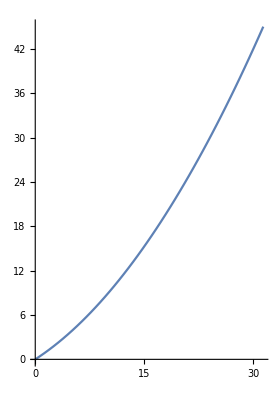

```mathematica
ParametricPlot[{Subscript[X, p][t],Subscript[Y, p][t]},{t,0,Subscript[t, man]}]
```

```mathematica
pathPointGen[pathPoints[[1]],1]
```

pathPointGen[{{0,0,1},{0,0,0}},1]